# The 3+1 super-loop: the symbols and the programs of Test 2 in the Wolfram Language

## PROJECT spacetimes. Notebook 3+1super-loop.nb, prepared for Patrick Lee Nash, Ph.D.

This notebook is written for a physics student who has not seen the work before. It does two things. Part I gives every symbol of the project a Wolfram Language form that looks exactly like the printed symbol (for example Δ_LL^vac, the gap of the condensed vacuum) and behaves as one indivisible symbol in computations; it then checks this with computations that use sums, arithmetic and algebra. Part II (added in later stages) collects, as an encyclopedia, every program of Test 2, rewritten in the Wolfram Language, with every check of the original programs.

How to use it. Open the notebook in Wolfram (version 15 or later; it was evaluated with Wolfram 15.0.1) and choose Evaluation > Evaluate Notebook. Every cell is evaluated in order; every test prints PASS or FAIL, and the last cell of each part lists all tests. Nothing outside this notebook is read: the registry of the symbols and all programs are inside it.

How to read it. Text cells explain, in words, what the next input cell does and why. Inside the code, comments (* like this *) explain each step. Every symbol of the physics is written with its printed form; every Wolfram Language function that is used is named in the text the first time it appears.

## Part I. The symbols

## I.1 Why every symbol of the project carries the suffix LL

Papers and notebooks in physics often use one letter for several different objects: Δ may be a gap, a Laplacian or a difference; m a mass or an index. In a long project with many documents and programs this produces errors that are hard to find. The project therefore keeps a registry: every symbol that it creates has a unique printed form, and the symbols of the super-loop revision carry the suffix LL, in a subscript or superscript (for example G_LL, the coupling of the contact interaction, and τ_ι^LL, the Pauli matrices of isospin). The registry lists for each symbol its printed form (written in TeX), its plain-text names (the names under which programs and data files write it), its meaning and its origin. Part I brings this whole registry into the Wolfram Language.

In the Wolfram Language an ordinary subscript is not a symbol: the input a_LL is the expression Subscript[a, LL], a function of two symbols. One cannot safely give it a value, and it can be confused with other subscripted expressions. Part I uses the Notation package, which is part of every Wolfram installation, to turn each printed form into one indivisible symbol (a "symbolized" symbol).

## I.2 The technique: symbolized symbols, created by a program

The Notation package works on boxes, the structures that describe how an input looks on the screen. The two-dimensional input a_LL is the box SubscriptBox["a", "LL"]. The command Symbolize[ParsedBoxWrapper[box], WorkingForm -> StandardForm] tells the Wolfram Language: whenever an input contains exactly this box, read it as one new symbol, and whenever that symbol is printed, print it as this box. The wrapper ParsedBoxWrapper marks its argument as a box structure (this is the way to call Symbolize from a program; the palette of the package inserts an equivalent wrapper when one works by hand).

The option WorkingForm -> StandardForm is essential here. Without it the package asks the front end for the format of the notebook in which the input was typed (InputNotebook[]). When a notebook is evaluated by a program, or when no notebook is selected, there is no such notebook, the answer is $Failed, and the package stores its reading rule for the format $Failed: the symbol is created but the input box is never recognized. This was found while this notebook was being prepared: the tests below failed until the option was given explicitly.

The next cell loads the package and symbolizes one example, a_LL (this symbol and the symbol a_(LL,p) of a later cell serve only as examples of the technique: they are not entries of the registry and denote no object of the physics). The cells after it show that the two-dimensional input is now one symbol, that it can receive a value, and how a program reaches the symbol from its box: MakeExpression[box, StandardForm] reads a box the same way the notebook reads input, and returns the result wrapped in HoldComplete (so that it is not evaluated).

```mathematica
(* load the Notation package (it ships with every Wolfram installation) *)
Needs["Notation`"];
(* create the symbol a_LL from the box "a with the subscript LL" *)
Symbolize[ParsedBoxWrapper[SubscriptBox["a", "LL"]], WorkingForm -> StandardForm];
(* the name that the package gave to the new symbol (the separator is the character ⎵) *)
Names["Global`a⎵*"]
```

{a⎵Subscript⎵LL}

```mathematica
(* the box of a_LL, read as input, is now ONE symbol: its head is Symbol and it is an atom *)
With[{h = MakeExpression[SubscriptBox["a", "LL"], StandardForm]},
  {h, Head @@ h, AtomQ @@ h}]
```

{HoldComplete[a_LL],Symbol,True}

The ordinary expression Subscript[a, LL], typed as text, is NOT the symbol: only the box is symbolized. A program therefore reaches a symbolized symbol through its box, with MakeExpression, which returns HoldComplete[symbol]. To give it a value, the held symbol is put into an assignment with Apply (written @@): Set @@ HoldComplete[symbol, value] replaces the head HoldComplete by Set and gives Set[symbol, value]; because Set does not evaluate its first argument, the symbol itself (and not its old value) receives the value. In the same way Clear @@ HoldComplete[symbol] gives Clear[symbol].

```mathematica
(* the text input Subscript[a, LL] is a compound expression, not the symbol *)
{Head[Subscript[a, LL]], AtomQ[Subscript[a, LL]]}
```

{Subscript,False}

```mathematica
(* assign the value 42 to the symbol a_LL through its box, then read it back:
   Join[HoldComplete[a_LL], HoldComplete[42]] is HoldComplete[a_LL, 42], and Set @@ ... is a_LL = 42 *)
With[{s = MakeExpression[SubscriptBox["a", "LL"], StandardForm]},
  Set @@ Join[s, HoldComplete[42]]];
ReleaseHold[MakeExpression[SubscriptBox["a", "LL"], StandardForm]] + 1
```

43

```mathematica
(* remove the value again, so that a_LL is a free symbol for the rest of the notebook:
   Clear @@ HoldComplete[a_LL] is Clear[a_LL] *)
With[{s = MakeExpression[SubscriptBox["a", "LL"], StandardForm]}, Clear @@ s];
ReleaseHold[MakeExpression[SubscriptBox["a", "LL"], StandardForm]]
```

a_LL

A symbolized symbol is one indivisible atom: the letters inside its scripts are not separate symbols. The next cell shows this with the symbol a_(LL,p), whose subscript holds the label LL and the index letter p. In a sum whose summation variable is also called LL, the whole symbol is multiplied by the summation variable, so that ∑_(LL==1)^2 LL a_(LL,p)==3 a_(LL,p): the LL inside the subscript is untouched. For comparison, the ordinary subscripted expression Subscript[b, LL, p], which is not symbolized, is a compound expression in which LL is replaced: its sum is Subscript[b, 1, p] + 2 Subscript[b, 2, p].

One rule must be observed when a box is symbolized by a program: the box must be exactly the box that the front end sends to the kernel when the symbol is typed. Before an input cell is evaluated, the front end reads every string of its boxes again, as typed text, and cuts it into tokens: names (a letter followed by letters and digits), numbers and single other characters. The subscript of a typed a_(LL,p) therefore arrives as RowBox[{"LL", ",", "p"}], three tokens. A box written by hand as SubscriptBox["a", "LL,p"], with the whole subscript in one string, is never matched by typed input, because the front end never sends that string. This was found while the notebook was prepared (a test notebook, evaluated in the front end, showed exactly this), and the converter of section I.3 builds the cut form.

```mathematica
(* symbolize a_{LL,p}: the subscript "LL, p" exactly as the front end stores it, three tokens in a RowBox *)
Symbolize[ParsedBoxWrapper[SubscriptBox["a", RowBox[{"LL", ",", "p"}]]], WorkingForm -> StandardForm];
(* the summation variable is called LL; the symbol a_{LL,p} is one atom, so its subscript is untouched *)
Sum[LL Subscript[a, LL,p], {LL, 1, 2}]
(* the same sum, compared with 3 a_{LL,p} *)
3 Subscript[a, LL,p] === Sum[LL Subscript[a, LL,p], {LL, 1, 2}]
(* the ordinary, NOT symbolized, subscripted expression: here LL is replaced by 1 and 2 *)
Sum[LL Subscript[b, LL, p], {LL, 1, 2}]
```

3 a_(LL,p)

True

b_(1,p)+2 b_(2,p)

```mathematica
(* the name LL is used later for the function LL of the package of section I.3; the summation
   variable LL of the demonstration (a symbol of the context Global`) and the symbol b are removed,
   so that they cannot shadow it *)
Remove[LL, b];
Names["Global`a⎵*"]
```

{a⎵Subscript⎵LL,a⎵Subscript⎵LL⎵Comma⎵p}

## I.3 From the printed form (TeX) to boxes

The registry stores every symbol in TeX, the language in which the documents of the project are typeset; for example the gap of the condensed vacuum is \Delta^{\rm vac}_{\rm LL}. The next cell defines, in the context SL31, a small reader of exactly this kind of TeX. It splits the TeX into tokens, reads them from left to right, and builds the box. A command such as \Delta becomes the Greek letter; ^{...} and _{...} become a superscript and a subscript; {\rm LL} becomes the upright text LL (roman text that holds several tokens, such as {\rm int,F} or {\rm s(2)}, is cut into tokens exactly as the front end cuts typed text, section I.2); \vec d becomes a d with an arrow. Letters in special alphabets keep their alphabet: double-struck (ℝ), script (ℒ) and Gothic (𝔪) letters are separate characters of the Wolfram Language, and sans-serif (N) and bold (x) letters are wrapped in a TagBox, which the Notation package does not remove when it compares boxes, so that a bold, a sans-serif and an ordinary letter with the same scripts remain three different symbols.

The same cell defines the functions that split an entry of the registry into single symbols, classify every item (a symbol, a family of symbols with running indices, a function symbol, a group, an index, an operator, and so on), give every symbolized symbol a readable name, symbolize it, and reach it by its TeX: LL[tex] returns the symbol of the TeX item tex, and LL[tex, index -> value] the symbol of one of its components. In the input cells of this notebook the symbols appear directly in their printed form.

```mathematica
(* ------------------------------------------------------------------------------------------------
   The symbol machinery of the notebook 3+1super-loop.nb, in the context SL31` .
   It converts the TeX of a registered symbol into two-dimensional Wolfram boxes, splits the
   symbol field of a registry entry into single symbols, classifies them, and symbolizes them
   with the Notation package.
   ------------------------------------------------------------------------------------------------ *)
BeginPackage["SL31`", {"Notation`"}];

SL31TeXTokens::usage = "SL31TeXTokens[tex] splits the TeX string tex into tokens: commands such as \\Delta, braces, the scripts ^ and _, primes, and single characters.";
SL31TeXToBoxes::usage = "SL31TeXToBoxes[tex] converts the TeX of one registered symbol into the two-dimensional Wolfram boxes used in this notebook (the style of every letter is kept: double-struck, script, Gothic, sans-serif and bold letters stay different).";
SL31SplitTeX::usage = "SL31SplitTeX[tex] splits a TeX segment that lists several symbols, separated by commas outside braces, parentheses and brackets, into the single symbols; a list a, \\dots, b of numbered symbols is expanded.";
SL31Classify::usage = "SL31Classify[tex, boxes] returns the kind of a registered item: \"symbol\", \"family\", \"function\", \"letter\", \"index\", \"set\", \"group\", \"operator\", \"ket\", \"expression\".";
SL31Head::usage = "SL31Head[boxes] returns the boxes of the symbol part of a function symbol such as W(u): the boxes before the argument in parentheses.";
SL31IndexLetters::usage = "SL31IndexLetters lists the boxes that are running indices of a family of symbols: p, j, iota, k, n and their primed forms.";
SL31NameOf::usage = "SL31NameOf[boxes] is the name given to the symbol of boxes: built from the letters, the scripts and the styles, with every character that may not stand in a symbol name replaced by its character name between the separators ⎵.";
SL31Symbolize::usage = "SL31Symbolize[boxes] symbolizes boxes with the Notation package in StandardForm (WorkingForm -> StandardForm given explicitly) and returns the new symbol, held: HoldComplete[symbol].";
SL31SymbolOf::usage = "SL31SymbolOf[boxes] returns HoldComplete[s], where s is the expression that the boxes parse to in StandardForm (for a symbolized box: the atomic symbol).";
SL31SymbolBoxes::usage = "SL31SymbolBoxes[tex] returns the boxes that are symbolized for the registered TeX item tex (see the comments of its definition for the wrapping by kind).";
SL31Symbolized::usage = "SL31Symbolized lists the kinds of registered items that are symbolized.";
SL31Instance::usage = "SL31Instance[boxes, {index -> value, ...}] replaces running indices in the scripts of boxes by values (strings), symbolizes the resulting component box and returns it, held.";
LL::usage = "LL[tex] returns the symbolized symbol of the registered TeX symbol tex; LL[tex, index -> value, ...] returns the symbolized component with the given index values.";
SL31`Build`symbolBoxes::usage = "SL31`Build`symbolBoxes[tex, index -> value, ...] returns the boxes of the registered symbol tex or of its component; used by the notebook builder.";

Begin["`Private`"];

(* ---------- 1. Tokens ---------- *)
SL31TeXTokens[s_String] := StringCases[s, {
    RegularExpression["\\\\[A-Za-z]+"],      (* a command such as \Delta or \mathbf *)
    RegularExpression["\\\\[,;:! ]"],        (* a TeX spacing command: dropped later *)
    "''", "'",                               (* primes *)
    RegularExpression["\\s+"],               (* white space: dropped later *)
    RegularExpression["."]}];                (* any other single character *)

(* ---------- 2. Characters for the commands ---------- *)
cmd = <|
  "\\alpha" -> "α", "\\beta" -> "β", "\\gamma" -> "γ", "\\delta" -> "δ",
  "\\epsilon" -> "ϵ", "\\varepsilon" -> "ε", "\\zeta" -> "ζ", "\\eta" -> "η",
  "\\theta" -> "θ", "\\vartheta" -> "ϑ", "\\iota" -> "ι", "\\kappa" -> "κ",
  "\\varkappa" -> "ϰ", "\\lambda" -> "λ", "\\mu" -> "μ", "\\nu" -> "ν",
  "\\xi" -> "ξ", "\\pi" -> "π", "\\varpi" -> "ϖ", "\\rho" -> "ρ",
  "\\varrho" -> "ϱ", "\\sigma" -> "σ", "\\varsigma" -> "ς", "\\tau" -> "τ",
  "\\upsilon" -> "υ", "\\phi" -> "ϕ", "\\varphi" -> "φ", "\\chi" -> "χ",
  "\\psi" -> "ψ", "\\omega" -> "ω",
  "\\Gamma" -> "Γ", "\\Delta" -> "Δ", "\\Theta" -> "Θ",
  "\\Lambda" -> "Λ", "\\Xi" -> "Ξ", "\\Pi" -> "Π",
  "\\Sigma" -> "Σ", "\\Upsilon" -> "Υ", "\\Phi" -> "Φ",
  "\\Psi" -> "Ψ", "\\Omega" -> "Ω",
  "\\ell" -> "ℓ", "\\nabla" -> "∇", "\\partial" -> "∂", "\\infty" -> "∞",
  "\\pm" -> "±", "\\mp" -> "∓", "\\dagger" -> "†",
  "\\uparrow" -> "↑", "\\downarrow" -> "↓", "\\cdot" -> "·",
  "\\dots" -> "…", "\\ldots" -> "…", "\\times" -> "×",
  "\\otimes" -> "⊗", "\\oplus" -> "⊕", "\\circ" -> "∘",
  "\\langle" -> "⟨", "\\rangle" -> "⟩",
  "\\lvert" -> "|", "\\rvert" -> "|", "\\vert" -> "|",
  "\\deg" -> "deg", "\\det" -> "det", "\\exp" -> "exp", "\\ln" -> "ln", "\\sum" -> "∑",
  "\\int" -> "∫"|>;

(* the styled letters: every style gives a box that the Notation package does NOT strip, so that
   letters of different styles stay different symbols *)
styled["\\mathbb", x_String] := StringJoin[ToExpression["\"\\[DoubleStruckCapital" <> # <> "]\""] & /@ Characters[x]];
styled["\\mathcal", x_String] := StringJoin[ToExpression["\"\\[ScriptCapital" <> # <> "]\""] & /@ Characters[x]];
styled["\\mathfrak", x_String] := StringJoin[If[UpperCaseQ[#],
     ToExpression["\"\\[GothicCapital" <> # <> "]\""], ToExpression["\"\\[Gothic" <> ToUpperCase[#] <> "]\""]] & /@ Characters[x]];
styled["\\mathsf", x_] := TagBox[StyleBox[x, FontFamily -> "Helvetica", FontSlant -> "Plain"], "SL31SansSerif"];
styled["\\mathbf", x_] := TagBox[StyleBox[x, FontWeight -> "Bold", FontSlant -> "Plain"], "SL31Bold"];
styled["\\mathrm", x_] := x;
styleCommands = {"\\mathbb", "\\mathcal", "\\mathfrak", "\\mathsf", "\\mathbf", "\\mathrm"};
accent = <|"\\vec" -> "⇀", "\\hat" -> "^", "\\tilde" -> "~", "\\bar" -> "_"|>;

(* the boxes of a piece of roman text, as the front end makes them.  When a notebook cell is
   evaluated, the front end first reads every string of its boxes again as typed text and cuts it
   into tokens: names (a letter followed by letters and digits), numbers (digits), and single
   other characters; a part in parentheses becomes a RowBox of its own.  The string "int,F" is
   therefore sent to the kernel as RowBox[{"int", ",", "F"}], and "s(2)" as
   RowBox[{"s", RowBox[{"(", "2", ")"}]}].  The Notation package recognizes an input only if its
   boxes are EXACTLY the symbolized boxes, so the reader must build these same boxes; a single
   name such as "vac" or "LL" stays one string. *)
plainBoxes[s_String] := Module[{toks, j = 1, m, group, single},
  toks = StringCases[s, {
     w : (LetterCharacter ~~ (LetterCharacter | DigitCharacter) ...) :> w,
     d : (DigitCharacter ..) :> d,
     c : Except[WhitespaceCharacter] :> c}];
  m = Length[toks];
  single[items_List] := Which[items === {}, "", Length[items] == 1, First[items], True, RowBox[items]];
  (* the items up to a closing parenthesis or the end; a part in parentheses becomes one item *)
  group[] := Module[{items = {}},
    While[j <= m && toks[[j]] =!= ")",
      If[toks[[j]] === "(",
        j++;
        With[{inner = group[]}, If[j <= m, j++]; AppendTo[items, RowBox[{"(", single[inner], ")"}]]],
        AppendTo[items, toks[[j]]]; j++]];
    items];
  single[group[]]];

(* ---------- 3. The parser (recursive descent over the token list) ---------- *)
SL31TeXToBoxes[tex_String] := Module[
  {t, i = 1, n, peek, next, seq, atom, scriptArg, withScripts, plainText, merge, regroup},
  t = Select[SL31TeXTokens[tex],
    ! (StringMatchQ[#, RegularExpression["\\s+"]] || MemberQ[{"\\,", "\;", "\\:", "\\!", "\\ "}, #]) &];
  n = Length[t];
  peek[] := If[i <= n, t[[i]], None];
  next[] := (i++; t[[i - 1]]);
  (* the text of a group in roman type, {\rm ...}: its characters are joined and then cut into
     tokens exactly as the front end cuts typed text (see plainBoxes above) *)
  plainText[] := Module[{s = ""},
    While[i <= n && peek[] =!= "}",
      With[{k = next[]},
        s = s <> Which[
          k === "'", "′", k === "''", "′′",
          KeyExistsQ[cmd, k], cmd[k],
          StringStartsQ[k, "\\"], StringDrop[k, 1],
          True, k]]];
    plainBoxes[s]];
  (* merge neighbouring digits into one number string *)
  merge[items_List] := Module[{r = SequenceReplace[items,
        {a_String, b_String} /; StringMatchQ[a, DigitCharacter ..] && StringMatchQ[b, DigitCharacter ..] :> a <> b]},
    If[r === items, r, merge[r]]];
  (* a script written after a closing parenthesis, as in (T_LL)^2, belongs to the whole group in
     parentheses: the front end stores (T_LL)^2 as SuperscriptBox[RowBox[{"(", T_LL, ")"}], "2"],
     and the reader builds the same box *)
  regroup[items_List] := Module[{out = {}, stack = {}},
    Do[Which[
        it === "(", AppendTo[out, it]; AppendTo[stack, Length[out]],
        it === ")", If[stack =!= {}, stack = Most[stack]]; AppendTo[out, it],
        MatchQ[it, (SubscriptBox | SuperscriptBox | SubsuperscriptBox)[")", __]] && stack =!= {},
          With[{j = Last[stack]},
            stack = Most[stack];
            out = Append[Take[out, j - 1], ReplacePart[it, 1 -> RowBox[Append[Drop[out, j - 1], ")"]]]]],
        True, AppendTo[out, it]],
      {it, items}];
    out];
  (* a sequence of atoms up to "}" or the end *)
  seq[] := Module[{items = {}, a},
    While[i <= n && peek[] =!= "}",
      If[peek[] === "\\rm",
        next[]; AppendTo[items, plainText[]],
        a = atom[]; If[a =!= Null, AppendTo[items, a]]]];
    items = regroup[merge[items]];
    Which[items === {}, "", Length[items] == 1, First[items], True, RowBox[items]]];
  (* the argument of a script, an accent or a style: a group or a single token *)
  scriptArg[] := Module[{k = next[], r},
    Which[
      k === "{", r = seq[]; next[]; r,
      KeyExistsQ[cmd, k], cmd[k],
      MemberQ[styleCommands, k], styled[k, Replace[scriptArg[], RowBox[l_] :> StringJoin[l]]],
      True, k]];
  (* an atom without its scripts *)
  atom[] := Module[{k = next[], base},
    base = Which[
      k === "{", With[{r = seq[]}, next[]; r],
      MemberQ[styleCommands, k], styled[k, Replace[scriptArg[], RowBox[l_] :> StringJoin[l]]],
      KeyExistsQ[accent, k], OverscriptBox[scriptArg[], accent[k]],
      KeyExistsQ[cmd, k], cmd[k],
      StringStartsQ[k, "\\"], StringDrop[k, 1],
      True, k];
    withScripts[base]];
  (* primes, superscripts and subscripts after a base *)
  withScripts[base_] := Module[{sub = None, sup = None, primes = "", go = True},
    While[go && i <= n,
      Which[
        peek[] === "'", next[]; primes = primes <> "′",
        peek[] === "''", next[]; primes = primes <> "′′",
        peek[] === "^", next[]; sup = scriptArg[],
        peek[] === "_", next[]; sub = scriptArg[],
        True, go = False]];
    If[primes =!= "", sup = If[sup === None, primes, RowBox[{primes, sup}]]];
    Which[
      sub === None && sup === None, base,
      sup === None, SubscriptBox[base, sub],
      sub === None, SuperscriptBox[base, sup],
      True, SubsuperscriptBox[base, sub, sup]]];
  seq[]];

(* ---------- 4. Splitting a TeX segment into single symbols ---------- *)
SL31SplitTeX[tex_String] := Module[{chars = Characters[tex], depth = 0, cur = "", out = {}, items, expand},
  Do[Which[
      MemberQ[{"{", "(", "["}, c], depth++; cur = cur <> c,
      MemberQ[{"}", ")", "]"}, c], depth--; cur = cur <> c,
      c === "," && depth == 0, AppendTo[out, StringTrim[cur]]; cur = "",
      True, cur = cur <> c],
    {c, chars}];
  AppendTo[out, StringTrim[cur]];
  items = Select[out, # =!= "" &];
  (* a, \dots, b with a and b differing in one integer: expand *)
  expand[{a_String, "\\dots", b_String}] := Module[{na = StringCases[a, DigitCharacter ..], nb = StringCases[b, DigitCharacter ..], pos},
    pos = Flatten[Position[MapThread[Equal, {na, nb}], False]];
    If[Length[na] == Length[nb] && Length[pos] == 1,
      Table[StringReplacePart[a, ToString[v], Last[StringPosition[a, na[[First[pos]]]]]],
        {v, ToExpression[na[[First[pos]]]], ToExpression[nb[[First[pos]]]]}],
      {a, "\\dots", b}]];
  If[Length[items] == 3 && items[[2]] === "\\dots", expand[items], items]];

(* ---------- 5. Kinds ---------- *)
SL31IndexLetters = {"p", "j", "ι", "k", "n",
   SuperscriptBox["p", "′"], SuperscriptBox["p", "′′"],
   SuperscriptBox["j", "′"], SuperscriptBox["j", "′′"],
   SuperscriptBox["ι", "′"], SuperscriptBox["ι", "′′"]};

(* the script parts of a box (subscripts and superscripts, not the base) *)
scriptsOf[SubscriptBox[b_, s_]] := Join[{s}, scriptsOf[b]];
scriptsOf[SuperscriptBox[b_, s_]] := Join[{s}, scriptsOf[b]];
scriptsOf[SubsuperscriptBox[b_, s1_, s2_]] := Join[{s1, s2}, scriptsOf[b]];
scriptsOf[OverscriptBox[b_, _]] := scriptsOf[b];
scriptsOf[_] := {};
indexIn[s_] := ! FreeQ[s /. RowBox[l_] :> l, Alternatives @@ SL31IndexLetters];
hasRunningIndex[b_] := AnyTrue[scriptsOf[b], indexIn];

(* the head of a function symbol: RowBox[{head, "(", args, ")"}] *)
SL31Head[RowBox[{h_, "(", ___, ")"}]] := h;
SL31Head[b_] := b;

SL31Classify[tex_String, b_] := Which[
  MemberQ[{"i"}, b], "imaginary unit",
  MemberQ[{"p", "j", "ι", "k", "n"}, b], "index",
  MemberQ[SL31IndexLetters, b], "primed index",
  MemberQ[{"ℝ", "ℂ", "ℍ", "𝕆"}, b], "set",
  (* the operators are tested before the single letters: the tensor product, the direct sum and
     the composition are single characters too *)
  MemberQ[{"tr", "det", "diag", "Re", "Im", "⊗", "⊕", "∘"}, b], "operator",
  StringQ[b] && StringLength[b] == 1, "letter",
  MatchQ[b, SuperscriptBox["", "T"] | RowBox[{"⟨", "⟩"}] | RowBox[{"[", "·", "]"}]], "operator",
  MatchQ[b, RowBox[{"|", __, "⟩"}]], "ket",
  MatchQ[b, RowBox[{"[", __, "]"}]], "operator",
  StringStartsQ[tex, {"SL(", "SO(", "SU(", "Spin(", "U(", "O(", "\\mathrm G_2", "\\mathfrak{"}], "group",
  (* a group in parentheses with a script, such as (T_LL)^2: an expression, not a power of T_LL *)
  MatchQ[b, (SubscriptBox | SuperscriptBox | SubsuperscriptBox)[RowBox[{"(", ___, ")"}], __]], "expression",
  MatchQ[b, RowBox[{_, "(", ___, ")"}]], If[hasRunningIndex[SL31Head[b]], "function family", "function"],
  MatchQ[b, RowBox[_]], "expression",
  hasRunningIndex[b], "family",
  True, "symbol"];

(* ---------- 6. Symbolization (the technique of the Notation package) ---------- *)
(* The option WorkingForm -> StandardForm is given explicitly: by default the Notation package
   takes the working form from the notebook that holds the input (InputNotebook[]); when the
   notebook is evaluated without a selected input notebook this gives $Failed, and the parsing
   rule would then be stored for the form $Failed and never used. *)
(* The name of the new symbol.  The Notation package would name a symbolized box after its
   letters and its scripts only (it removes StyleBox and TagBox wrappers when it builds the name),
   so that a bold, a sans-serif and an ordinary D with the same scripts would all receive the same
   name and become ONE symbol.  The name built here records the style as well, and replaces every
   character that may not stand in a symbol name by its character name. *)
charName[c_String] := Replace[Quiet[CharacterName[c]], Except[_String] :> "U" <> IntegerString[First[ToCharacterCode[c]], 16]];
safeChars[s_String] := StringJoin[If[LetterQ[#] || DigitQ[#], #, "⎵" <> charName[#] <> "⎵"] & /@ Characters[s]];
SL31NameOf[b_] := Module[{parts, name},
  parts = Flatten[{b} //. {
     TagBox[StyleBox[x_, ___], "SL31Bold", ___] :> {"Bold⎵", x},
     TagBox[StyleBox[x_, ___], "SL31SansSerif", ___] :> {"SansSerif⎵", x},
     TagBox[x_, "SL31Plain", ___] :> {"Plain⎵", x},
     TagBox[x_, "SL31Name", ___] :> {"Name⎵", x},
     TagBox[x_, ___] :> x, StyleBox[x_, ___] :> x,
     RowBox[l_List] :> l,
     SubscriptBox[x_, c_] :> {x, "⎵Sub⎵", c},
     SuperscriptBox[x_, c_] :> {x, "⎵Sup⎵", c},
     SubsuperscriptBox[x_, c_, d_] :> {x, "⎵Sub⎵", c, "⎵Sup⎵", d},
     OverscriptBox[x_, c_] :> {x, "⎵Over⎵", c}}];
  name = StringJoin[Map[If[MemberQ[{"⎵Sub⎵", "⎵Sup⎵",
       "⎵Over⎵", "Bold⎵", "SansSerif⎵", "Plain⎵",
       "Name⎵"}, #], #, safeChars[#]] &, parts]];
  If[LetterQ[StringTake[name, 1]], name, "Sym" <> name]];

(* The option WorkingForm -> StandardForm is given explicitly: by default the Notation package
   takes the working form from the notebook that holds the input (InputNotebook[]); when the
   notebook is evaluated without a selected input notebook this gives $Failed, and the parsing
   rule would then be stored for the form $Failed and never used. *)
SL31Symbolize[b_] := (Notation`Symbolize[Notation`ParsedBoxWrapper[b], Notation`WorkingForm -> StandardForm,
     Notation`SymbolizeRootName -> SL31NameOf[b]];
   SL31SymbolOf[b]);
SL31SymbolOf[b_] := MakeExpression[b, StandardForm];

(* components: replace running indices in the scripts by values *)
replaceIndex[b_, rules_List] := Module[{r = Map[(#[[1]] -> #[[2]]) &, rules]},
  b /. {SubscriptBox[x_, s_] :> SubscriptBox[x, s /. r], SuperscriptBox[x_, s_] :> SuperscriptBox[x, s /. r],
        SubsuperscriptBox[x_, s1_, s2_] :> SubsuperscriptBox[x, s1 /. r, s2 /. r]}];
SL31Instance[b_, rules_List] := SL31Symbolize[replaceIndex[b, rules]];

(* the boxes that are symbolized for a registered TeX item, by kind:
   - a single letter (D, the dimension count) is wrapped in TagBox[.., "SL31Plain"], so that the
     ordinary letter (for example the derivative D of the Wolfram Language) keeps its meaning;
   - a group name, a ket or another expression whose boxes begin with RowBox is wrapped in
     TagBox[.., "SL31Name"], because the Notation package cannot symbolize a RowBox;
   - a function symbol W(u) gives the boxes of its head W;
   - every other kind gives its boxes unchanged. *)
SL31Symbolized = {"symbol", "family", "function", "function family", "letter", "group", "ket", "expression", "primed index"};
(* the innermost base of a box with scripts or an accent *)
baseOf[(SubscriptBox | SuperscriptBox | SubsuperscriptBox | OverscriptBox)[x_, __]] := baseOf[x];
baseOf[x_] := x;
(* a box whose base is an operator sign, such as the partial-derivative sign or nabla, would be
   read by the front end as an operator applied to what follows it *)
operatorBaseQ[b_] := With[{x = baseOf[b]}, StringQ[x] && x =!= "" && ! LetterQ[StringTake[x, 1]] && ! DigitQ[StringTake[x, 1]]];
(* TagBox[.., "SL31Name", SyntaxForm -> "symbol"] makes the front end treat its content as ONE
   operand, like a symbol, wherever it stands *)
asName[b_] := TagBox[b, "SL31Name", SyntaxForm -> "symbol"];
SL31SymbolBoxes[tex_String] := Module[{b = SL31TeXToBoxes[tex], k, r},
  k = SL31Classify[tex, b];
  r = Switch[k,
    "letter", TagBox[b, "SL31Plain"],
    "expression", asName[b],
    "group" | "ket", If[Head[b] === RowBox, asName[b], b],
    "function" | "function family", SL31Head[b],
    _, b];
  If[Head[r] =!= TagBox && operatorBaseQ[r], asName[r], r]];

(* the boxes of a registered TeX symbol, with optional index values given as TeX strings *)
SL31`Build`symbolBoxes[tex_String, rules___Rule] := Module[{b = SL31SymbolBoxes[tex]},
  If[{rules} === {}, b, replaceIndex[b, Map[SL31TeXToBoxes[#[[1]]] -> SL31TeXToBoxes[#[[2]]] &, {rules}]]]];
LL[tex_String, rules___Rule] := ReleaseHold[SL31SymbolOf[SL31`Build`symbolBoxes[tex, rules]]];

End[];
EndPackage[];
```

A first look at the reader: the TeX of six registered symbols and the boxes that it builds, shown both as boxes and as they are displayed.

```mathematica
examples = {"\\Delta^{\\rm vac}_{\\rm LL}", "A^\\iota_{{\\rm LL},p}", "\\mathsf N^{\\rm g}_{\\rm LL}(\\vec d_{\\rm LL})",
   "\\vec d^{\\,*}_{\\rm LL}", "\\mathfrak m_{\\rm LL}", "\\lvert\\Phi^{\\rm SF}_{\\rm LL}\\rangle"};
Grid[Prepend[Map[{#, Style[ToString[SL31TeXToBoxes[#], InputForm], FontFamily -> "Source Code Pro", 9], RawBoxes[SL31TeXToBoxes[#]]} &, examples],
   Style[#, Bold] & /@ {"TeX", "boxes", "displayed"}], Frame -> All, Alignment -> Left]
```

TeX | boxes | displayed
\Delta^{\rm vac}_{\rm LL} | SubsuperscriptBox["Δ", "LL", "vac"] | Δ_LL^vac
A^\iota_{{\rm LL},p} | SubsuperscriptBox["A", RowBox[{"LL", ",", "p"}], "ι"] | A_(LL,p)^ι
\mathsf N^{\rm g}_{\rm LL}(\vec d_{\rm LL}) | RowBox[{SubsuperscriptBox[TagBox[StyleBox["N", FontFamily -> "Helvetica", FontSlant -> "Plain"], "SL31SansSerif"], "LL", "g"], "(", SubscriptBox[OverscriptBox["d", "⇀"], "LL"], ")"}] | N_LL^g((d⃗)_LL)
\vec d^{\,*}_{\rm LL} | SubsuperscriptBox[OverscriptBox["d", "⇀"], "LL", "*"] | (d⃗)_LL^*
\mathfrak m_{\rm LL} | SubscriptBox["𝔪", "LL"] | 𝔪_LL
\lvert\Phi^{\rm SF}_{\rm LL}\rangle | RowBox[{"|", SubsuperscriptBox["Φ", "LL", "SF"], "⟩"}] | |Φ_LL^SF⟩

Complete formulas. The texts of this notebook and the meanings of the registry (section I.8) contain complete formulas, written in TeX between dollar signs, for example B^{\rm out}_{\rm LL}=\big(1+\tfrac14h^{\rm IDA}_{\rm LL}E^{\rm max}_{\rm LL}\big)B^{\rm err}_{\rm LL}. A second reader, defined in the next cell, converts them into boxes. It is built like the reader of symbols (tokens, read from left to right), and it knows what a complete formula needs: fractions and roots, sums and integrals with their limits, accents, matrices, delimiters, the names of functions, and the spaces of TeX. Four properties matter for the correctness of what is shown.

The arguments of a command. In TeX an argument that is not written in braces is the single token that follows the command: \tfrac12\ell^{\rm x}_{\rm LL} is one half times ℓ_LL^x, and \sqrt2\,\ell^{\rm x}_{\rm LL} is the square root of 2, times ℓ_LL^x. The reader follows this rule. The TeX importer of the Wolfram Language (ImportString with the format "TeX") does not: it takes everything up to the end of the group as the denominator and everything before the fraction as part of the numerator, so that it shows \tfrac12\ell^{\rm x}_{\rm LL} as the fraction with the numerator 1 and the denominator 2 ℓ_LL^x, and Q_{\rm LL}=-\tfrac12 as the fraction with the numerator Q_LL==-1 and the denominator 2; it also shows \hbar as nothing. The importer is therefore not used anywhere in this notebook.

The alphabets. Every letter is given its alphabet by an explicit style: the letter of a variable is set in italics, text written with \rm upright, \mathbf bold and upright, \mathsf sans-serif (in the typeface Helvetica), and the double-struck, script and Gothic letters are the characters of the Wolfram Language for them. A formula is set in the typeface Times, so that an upright roman letter (the label K of ℓ_LL^K) differs visibly from a sans-serif letter (the matrix K_LL^3) and from an italic letter (the generator K_LL^j); the text around a formula is set in the sans-serif typeface of the text cells.

Names are not products. TeX sets neighbouring letters and numbers without a space. The front end of the Wolfram Language puts the thin space of a product between two neighbouring items of a row of boxes, and this notebook keeps that space between the factors of a product, as the Wolfram Language itself shows a product. Inside a name there must be no such space. The reader therefore joins neighbouring letters of one alphabet into one string (the letters SL and SU in the names of groups), and it puts the character \[InvisibleSpace], which has no width, between a letter and a number that directly follows it: the coordinates x5, x6, x7 of the main project (they occur in the meaning of the number of space dimensions, section I.8) are names, not products of a letter and a number.

Nothing is passed over in silence. A command that the reader does not know, a missing argument or an unmatched brace is recorded: SL31TeXFormulaProblems[tex] lists the problems of a formula, and the list must be empty. The program that builds this notebook stops with a warning for every problem in a text cell, and test S-15 (section I.7) checks every formula of the registry.

The function SL31FormulaReading writes the boxes of a formula on one line (a fraction as frac{a}{b}, a root as sqrt{a}, scripts as _{..} and ^{..}, a bold or sans-serif letter as <bf:b> or <sf:N>), without the spaces and without the italic and upright styles. Two conversions of a formula show the same formula exactly if their readings are equal; the tests use this.

```mathematica
(* ------------------------------------------------------------------------------------------------
   The reader of formulas of the notebook 3+1super-loop.nb, in the context SL31` .
   It converts the TeX of a complete formula (as it stands between dollar signs in the texts of
   this notebook and in the meanings of the registry of the symbols) into two-dimensional
   Wolfram boxes for display.

   WHY THE NOTEBOOK HAS ITS OWN READER OF FORMULAS
   The TeX importer of the Wolfram Language, ImportString["$...$", "TeX"], reads a fraction
   whose arguments are written WITHOUT braces wrongly.  In TeX an argument without braces is the
   single token that follows: \tfrac12 x is "one half times x".  The importer instead takes
   everything up to the end of the group as the denominator, and everything before the fraction
   as part of the numerator: it shows \tfrac12 x as 1/(2x), and a=b+\tfrac12 x as the fraction
   with the numerator a=b+1 and the denominator 2x.  It also shows the command \hbar as nothing,
   and it loses the alphabets of letters (a bold b, a sans-serif N and the double-struck R
   become plain letters).  A formula that is shown wrongly teaches a wrong statement, so this
   notebook converts every formula itself, with the rules of TeX, and tests the conversion
   (test S-15).

   THE METHOD (recursive descent, as in the reader of symbols of section I.3)
     1. The TeX is cut into tokens: a command (\frac, \Delta), a control symbol (a backslash
        followed by one character that is not a letter), white space, or one other character.
        Digits stay single tokens, because an argument without braces is ONE token: \tfrac12
        has the numerator 1 and the denominator 2.
     2. A sequence of atoms is read from left to right.  An atom is a letter, a digit, a
        character of a command, a group in braces, a part between matching delimiters such as
        ( ... ), or a command together with its arguments (\frac{a}{b}, \sqrt{a}, \vec d,
        \mathbf b, \begin{pmatrix} ... \end{pmatrix}); after the atom come its primes, its
        superscript and its subscript.
     3. Every letter carries its alphabet: an italic letter of a variable, upright text ({\rm ..},
        \mathrm, \text), bold (\mathbf), sans-serif (\mathsf), double-struck (\mathbb), script
        (\mathcal) or Gothic (\mathfrak).  Neighbouring digits form one number and neighbouring
        letters of one alphabet one string; a number that directly follows a letter is joined
        to the letter without a space (the coordinate x5 is one name, not a product).
     4. A sign that stands first, or after an operator, a relation, an opening delimiter or a
        comma, is a prefix sign and is joined to the item that follows it; the name of a
        function (cos, exp) and a large operator (the summation sign) are separated from a
        neighbouring ordinary item by a thin space, as TeX separates them.
   A command that the reader does not know, a missing argument or an unmatched brace is NOT
   passed over in silence: SL31TeXFormulaProblems[tex] lists every such problem.
   ------------------------------------------------------------------------------------------------ *)
BeginPackage["SL31`"];

SL31TeXFormula::usage = "SL31TeXFormula[tex] converts the TeX of a formula into two-dimensional Wolfram boxes for display: fractions, roots, sums and integrals with their limits, accents, matrices, delimiters, and every letter in its alphabet (italic, upright, bold, sans-serif, double-struck, script, Gothic).";
SL31TeXFormulaProblems::usage = "SL31TeXFormulaProblems[tex] lists what the reader of formulas could not read in tex: unknown commands, missing arguments, unmatched braces. The empty list means that the whole formula was read.";
SL31FormulaCell::usage = "SL31FormulaCell[tex] returns the inline cell that shows the formula tex inside a text.";
SL31TextData::usage = "SL31TextData[text] converts a text with formulas between dollar signs, code between backquotes and bold text between double asterisks into the content of a text cell.";
SL31TextFormulas::usage = "SL31TextFormulas[text] lists the TeX of the formulas that SL31TextData finds in text.";
SL31TextBoxes::usage = "SL31TextBoxes[text, options] returns the boxes of an inline text cell that shows text (converted by SL31TextData); the options are cell options such as FontSize.";
SL31FormulaReading::usage = "SL31FormulaReading[boxes] writes boxes on one line, so that two readings of a formula can be compared: a fraction as frac{a}{b}, a root as sqrt{a}, scripts as _{..} and ^{..}, an accent as over{a}{accent}, a matrix as grid[a&b;c&d], and a bold or sans-serif letter as <bf:b> or <sf:N>; spaces, the italic and upright styles and the grouping of rows are left out.";

Begin["`Private`"];

(* ---------- 1. Tokens ---------- *)
formulaTokens[s_String] := StringCases[s, {
    RegularExpression["\\\\[A-Za-z]+"],     (* a command such as \frac or \Delta *)
    RegularExpression["(?s)\\\\."],         (* a control symbol: a backslash and one character that is not a
                                               letter (the spaces of TeX, the double backslash that ends
                                               a row of a matrix, the braces written as characters) *)
    RegularExpression["\\s+"],              (* white space: skipped, except inside \text{...} *)
    RegularExpression["(?s)."]}];           (* any other single character *)

(* ---------- 2. Tables ---------- *)
(* the characters of the commands: those of the reader of symbols (the table cmd of section I.3:
   Greek letters, \ell, \nabla, \partial, \infty, \pm, \dagger, arrows, \cdot, \times, ...) and,
   in addition, the delimiters, relations and other signs of complete formulas *)
formulaChar = Join[cmd, <|
    "\\lvert" -> "|", "\\rvert" -> "|",
    "\\lVert" -> "‖", "\\rVert" -> "‖",
    "\\{" -> "{", "\\}" -> "}", "\\|" -> "∥", "\\vert" -> "|", "\\mid" -> "|",
    "\\lfloor" -> "⌊", "\\rfloor" -> "⌋", "\\lceil" -> "⌈", "\\rceil" -> "⌉",
    "\\le" -> "≤", "\\leq" -> "≤", "\\ge" -> "≥", "\\geq" -> "≥",
    "\\neq" -> "≠", "\\ne" -> "≠", "\\ll" -> "≪", "\\gg" -> "≫",
    "\\approx" -> "≈", "\\simeq" -> "≃", "\\sim" -> "∼", "\\equiv" -> "≡",
    "\\propto" -> "∝", "\\in" -> "∈", "\\notin" -> "∉",
    "\\subset" -> "⊂", "\\supset" -> "⊃", "\\subseteq" -> "⊆", "\\supseteq" -> "⊇",
    "\\cup" -> "∪", "\\cap" -> "∩",
    "\\to" -> "→", "\\rightarrow" -> "→", "\\leftarrow" -> "←",
    "\\leftrightarrow" -> "↔", "\\mapsto" -> "↦",
    "\\Rightarrow" -> "⇒", "\\Leftarrow" -> "⇐", "\\Leftrightarrow" -> "⇔",
    "\\hbar" -> "ℏ", "\\cdots" -> "⋯", "\\prime" -> "′", "\\ast" -> "*", "\\star" -> "⋆",
    "\\wedge" -> "⋀", "\\vee" -> "⋁", "\\forall" -> "∀", "\\exists" -> "∃",
    "\\emptyset" -> "∅", "\\perp" -> "⊥", "\\parallel" -> "∥",
    "\\%" -> "%", "\\&" -> "&", "\\#" -> "#", "\\_" -> "_", "\\$" -> "$"|>];

(* an opening delimiter and the delimiter that closes it *)
formulaDelims = <|"(" -> ")", "[" -> "]", "\\{" -> "\\}", "\\lvert" -> "\\rvert", "\\lVert" -> "\\rVert",
    "\\langle" -> "\\rangle", "\\lfloor" -> "\\rfloor", "\\lceil" -> "\\rceil"|>;
formulaClosers = Values[formulaDelims];
formulaDelimChar[k_String] := Lookup[formulaChar, k, k];

(* the class of a character, which decides the spacing: a binary operator, a relation or a
   punctuation mark; every other item is an ordinary item *)
formulaClass = Join[
    AssociationMap["bin" &, {"+", "-", "*", "±", "∓", "×", "·", "⊗",
       "⊕", "∘", "⋀", "⋁", "∪", "∩", "⋆"}],
    AssociationMap["rel" &, {"<", ">", ":", "==", "≤", "≥", "≠", "≪",
       "≫", "≈", "≃", "∼", "≡", "∝", "∈",
       "∉", "⊂", "⊃", "⊆", "⊇", "→", "←",
       "↔", "↦", "⇒", "⇐", "⇔"}],
    AssociationMap["punct" &, {",", ";"}]];
formulaSigns = {"+", "-", "±", "∓"};

(* commands that only choose the size of a delimiter or the style of a formula: they do not change
   what the formula says and are left out *)
formulaIgnored = {"\\big", "\\Big", "\\bigg", "\\Bigg", "\\bigl", "\\bigr", "\\Bigl", "\\Bigr", "\\biggl", "\\biggr",
    "\\Biggl", "\\Biggr", "\\bigm", "\\Bigm", "\\left", "\\right", "\\displaystyle", "\\textstyle", "\\scriptstyle",
    "\\limits", "\\nolimits", "\\nonumber", "\\strut", "\\mathstrut"};
(* the spaces of TeX; the negative thin space (a backslash and an exclamation mark) becomes the
   empty string, which is removed at the end but keeps the automatic thin space of rule 4 from
   being inserted at its place *)
formulaSpace = <|"\\," -> " ", "\\:" -> " ", "\\;" -> " ",
    "\\ " -> " ", "~" -> " ", "\\!" -> "", "\\quad" -> "   ", "\\qquad" -> "      "|>;
(* names of functions, set upright; those of the second list take their subscript as a limit *)
formulaFunctions = {"\\sin", "\\cos", "\\tan", "\\cot", "\\sec", "\\csc", "\\sinh", "\\cosh", "\\tanh", "\\coth",
    "\\arcsin", "\\arccos", "\\arctan", "\\exp", "\\log", "\\ln", "\\lg", "\\det", "\\deg", "\\dim", "\\ker", "\\arg",
    "\\gcd", "\\hom", "\\lim", "\\max", "\\min", "\\sup", "\\inf", "\\Pr"};
formulaLimitNames = {"lim", "max", "min", "sup", "inf"};
(* large operators; the summation and the product sign take their scripts as limits *)
formulaBigOp = <|"\\sum" -> "∑", "\\prod" -> "∏", "\\int" -> "∫", "\\oint" -> "∮"|>;
formulaLimitsQ[b_] := MemberQ[{"∑", "∏"}, b] ||
    MatchQ[b, StyleBox[w_String /; MemberQ[formulaLimitNames, w], ___]];
(* the alphabets: a command with one argument, or a switch for the rest of the group *)
formulaStyle = <|"\\mathbf" -> "bf", "\\mathsf" -> "sf", "\\mathbb" -> "bb", "\\mathcal" -> "cal", "\\mathfrak" -> "frak",
    "\\mathrm" -> "rm", "\\mathit" -> "it", "\\boldsymbol" -> "bf", "\\textbf" -> "bf", "\\textrm" -> "rm",
    "\\textit" -> "it", "\\operatorname" -> "rm"|>;
formulaSwitch = <|"\\rm" -> "rm", "\\it" -> "it", "\\bf" -> "bf", "\\sf" -> "sf", "\\cal" -> "cal"|>;
(* accents: the argument with the accent character above it *)
formulaAccent = <|"\\vec" -> "⇀", "\\hat" -> "^", "\\widehat" -> "^", "\\tilde" -> "~", "\\widetilde" -> "~",
    "\\bar" -> "_", "\\overline" -> "_", "\\dot" -> ".", "\\ddot" -> ".."|>;

(* ---------- 3. Letters and numbers ---------- *)
(* While a sequence is read, a letter is kept as ch[alphabet, letter] and a digit as num[digit];
   formulaFin gives the final box.  An italic letter gets the style "TI" (text italic) and upright
   text the explicit upright slant: with explicit styles a letter is shown in the same way in a
   text cell and in the output of a program (where single letters would otherwise be set in
   italics automatically). *)
formulaSpecial[kind_String, c_String] := Which[
    DigitQ[c], c,
    UpperCaseQ[c], ToExpression["\"\\[" <> kind <> "Capital" <> c <> "]\""],
    True, ToExpression["\"\\[" <> kind <> ToUpperCase[c] <> "]\""]];
formulaFin[ch["it", c_String]] := StyleBox[c, "TI"];
formulaFin[ch["rm", w_String]] := StyleBox[w, FontSlant -> "Plain"];
formulaFin[ch["bf", w_String]] := StyleBox[w, FontWeight -> "Bold", FontSlant -> "Plain"];
formulaFin[ch["sf", w_String]] := StyleBox[w, FontFamily -> "Helvetica", FontSlant -> "Plain"];
formulaFin[ch["bb", w_String]] := StyleBox[StringJoin[formulaSpecial["DoubleStruck", #] & /@ Characters[w]], FontSlant -> "Plain"];
formulaFin[ch["cal", w_String]] := StyleBox[StringJoin[formulaSpecial["Script", #] & /@ Characters[w]], FontSlant -> "Plain"];
formulaFin[ch["frak", w_String]] := StyleBox[StringJoin[formulaSpecial["Gothic", #] & /@ Characters[w]], FontSlant -> "Plain"];
formulaFin[num[s_String]] := s;
(* a letter with the number that directly follows it, the name of one quantity such as the
   coordinate x5: the character InvisibleSpace, which has no width, stands between the two, so
   that the front end does not put the thin space of a product there *)
formulaFin[named[a_, b_]] := RowBox[{formulaFin[a], "", formulaFin[b]}];
formulaFin[x_] := x;

formulaSingle[boxes_List] := Which[boxes === {}, "", Length[boxes] == 1, First[boxes], True, RowBox[boxes]];

(* ---------- 4. From the items of a sequence to its boxes ---------- *)
(* an item is {class, content}; the classes are "ord" (an ordinary item), "grp" (a part between
   matching delimiters), "op" (the name of a function or a large operator), "bin", "rel",
   "punct", "open" and "close" (a delimiter without its partner) and "space" *)
formulaFinish[items0_List] := Module[{items, out = {}, res = {}, k = 1, last = None, a, b},
   (* neighbouring letters of one alphabet form one string, so that they are set without a space
      between them, as TeX sets them (upright letters form a word; italic letters are the letters
      of a product or of a name such as SU); neighbouring digits, and digits around a decimal
      point, form one number *)
   items = items0 //. {
      {x___, {c1_, ch[al_, u_]}, {_, ch[al_, v_]}, y___} :> {x, {c1, ch[al, u <> v]}, y},
      {x___, {_, num[u_]}, {_, num[v_]}, y___} :> {x, {"ord", num[u <> v]}, y},
      {x___, {_, num[u_]}, {_, "."}, {_, num[v_]}, y___} :> {x, {"ord", num[u <> "." <> v]}, y}};
   (* a number that directly follows a letter belongs to the name of a quantity (the coordinates
      x5, x6, x7 of the main project); TeX sets the two without a space.  A number BEFORE a letter
      is a factor of a product and keeps the thin space that the front end puts between factors. *)
   items = items //. {x___, {c1_, letter : ch[_, _]}, {_, number : num[_]}, y___} :> {x, {c1, named[letter, number]}, y};
   items = Map[{#[[1]], formulaFin[#[[2]]]} &, items];
   (* prefix signs *)
   While[k <= Length[items],
     a = items[[k]];
     If[a[[1]] === "bin" && MemberQ[formulaSigns, a[[2]]] && MemberQ[{None, "bin", "rel", "open", "punct", "op"}, last],
       If[k < Length[items] && MemberQ[{"ord", "grp", "op"}, items[[k + 1, 1]]],
         b = items[[k + 1]];
         AppendTo[out, {If[b[[1]] === "op", "op", "ord"], RowBox[{a[[2]], b[[2]]}]}]; k += 2,
         AppendTo[out, {"ord", a[[2]]}]; k++];
       last = "ord",
       AppendTo[out, a]; If[a[[1]] =!= "space", last = a[[1]]]; k++]];
   (* thin spaces beside the names of functions and the large operators *)
   Do[
     If[j > 1 && ((out[[j, 1]] === "op" && MemberQ[{"ord", "grp", "op", "close"}, out[[j - 1, 1]]]) ||
          (out[[j - 1, 1]] === "op" && out[[j, 1]] === "ord")),
       AppendTo[res, " "]];
     AppendTo[res, out[[j, 2]]],
     {j, Length[out]}];
   DeleteCases[res, ""]];
formulaBox[items_List] := formulaSingle[formulaFinish[items]];

(* ---------- 5. The parser ---------- *)
(* formulaParse[tex] returns {boxes, problems} *)
formulaParse[tex_String] := Module[
  {t = formulaTokens[tex], n, i = 1, problems = {}, note, skip, peek, next, expect, matched, parseSeq, atom, arg,
   scripts, rawText, envName, envir, boxes},
  n = Length[t];
  note[s_String] := AppendTo[problems, s];
  skip[] := While[i <= n && StringMatchQ[t[[i]], RegularExpression["\\s+"]], i++];
  peek[] := (skip[]; If[i <= n, t[[i]], None]);
  next[] := (skip[]; If[i <= n, i++; t[[i - 1]], None]);
  expect[tok_String] := If[peek[] === tok, next[], note["missing " <> tok]];

  (* is the opening delimiter that was just read closed by its partner within the same group?
     (if not, as in a half-open interval, which opens with a square bracket and closes with a
     round one, the delimiter is an ordinary character) *)
  matched[open_String, close_String] := Module[{j = i, depth = 0, brace = 0, env = 0, tok, found = False, go = True},
    While[go && j <= n,
      tok = t[[j]];
      Which[
        tok === "{", brace++,
        tok === "}", If[brace == 0, go = False, brace--],
        tok === "\\begin", env++,
        tok === "\\end", If[env == 0, go = False, env--],
        (tok === "&" || tok === "\\\\") && brace == 0 && env == 0, go = False,
        brace == 0 && env == 0 && tok === close, If[depth == 0, found = True; go = False, depth--],
        brace == 0 && env == 0 && tok === open, depth++];
      j++];
    found];

  (* a sequence of atoms in the alphabet al0, up to one of the tokens of stops or the end; a
     switch such as \rm changes the alphabet for the rest of the sequence *)
  parseSeq[al0_String, stops_List] := Module[{al = al0, items = {}, tok},
    While[(tok = peek[]) =!= None && ! MemberQ[stops, tok],
      If[KeyExistsQ[formulaSwitch, tok],
        next[]; al = formulaSwitch[tok],
        items = Join[items, atom[al, True]]]];
    items];

  (* an argument: a group in braces, or else ONE token (with the arguments of that token, if it
     is a command, but without scripts) *)
  arg[al_String] := Module[{tok = peek[], r},
    Which[
      tok === None, note["an argument is missing at the end of the formula"]; {},
      tok === "{", next[]; r = parseSeq[al, {"}"}]; expect["}"]; r,
      True, r = atom[al, False]; If[r === {}, note["the argument " <> tok <> " is empty"]]; r]];

  (* the primes, the superscript and the subscript after an item *)
  scripts[al_String, {cls_String, content_}] := Module[{sub = None, sup = None, primes = "", go = True, tok, b},
    While[go,
      tok = peek[];
      Which[
        tok === "'", next[]; primes = primes <> "′",
        tok === "^", next[]; If[sup =!= None, note["two superscripts on one item"]]; sup = formulaBox[arg[al]],
        tok === "_", next[]; If[sub =!= None, note["two subscripts on one item"]]; sub = formulaBox[arg[al]],
        True, go = False]];
    If[primes =!= "", sup = If[sup === None, primes, RowBox[{primes, sup}]]];
    If[sub === None && sup === None,
      {cls, content},
      b = formulaFin[content];
      {cls, Which[
         formulaLimitsQ[b] && sup === None, UnderscriptBox[b, sub, LimitsPositioning -> True],
         formulaLimitsQ[b] && sub === None, OverscriptBox[b, sup, LimitsPositioning -> True],
         formulaLimitsQ[b], UnderoverscriptBox[b, sub, sup, LimitsPositioning -> True],
         sup === None, SubscriptBox[b, sub],
         sub === None, SuperscriptBox[b, sup],
         True, SubsuperscriptBox[b, sub, sup]]}]];

  (* the text of \text{...}: every character as it is written, white space as one space *)
  rawText[] := Module[{s = "", depth = 0, go = True, tok},
    If[peek[] =!= "{",
      note["\\text is not followed by {"],
      next[];
      While[go && i <= n,
        tok = t[[i]]; i++;
        Which[
          tok === "{", depth++; s = s <> tok,
          tok === "}", If[depth == 0, go = False, depth--; s = s <> tok],
          StringMatchQ[tok, RegularExpression["\\s+"]], s = s <> " ",
          True, s = s <> tok]];
      If[go, note["\\text{ is not closed"]]];
    s];

  (* the name of an environment, {pmatrix} *)
  envName[] := Module[{s = "", tok},
    If[peek[] =!= "{",
      note["\\begin or \\end is not followed by {"],
      next[];
      While[(tok = peek[]) =!= None && tok =!= "}", s = s <> next[]];
      expect["}"]];
    s];
  (* a matrix: cells separated by &, rows by a double backslash *)
  envir[al_String] := Module[{name = envName[], rows = {}, row = {}, cell, go = True, tok, width, grid},
    While[go,
      cell = formulaBox[parseSeq[al, {"&", "\\\\", "\\end"}]];
      tok = next[];
      Which[
        tok === "&", AppendTo[row, cell],
        tok === "\\\\", AppendTo[row, cell]; AppendTo[rows, row]; row = {},
        tok === "\\end",
          AppendTo[row, cell]; If[row =!= {""} || rows === {}, AppendTo[rows, row]];
          If[envName[] =!= name, note["\\end does not close \\begin{" <> name <> "}"]]; go = False,
        True,
          note["\\begin{" <> name <> "} is not closed"]; AppendTo[row, cell]; AppendTo[rows, row]; go = False]];
    width = Max[Length /@ rows];
    grid = GridBox[PadRight[#, width, ""] & /@ rows, RowSpacings -> 1, ColumnSpacings -> 1,
      RowAlignments -> Baseline, ColumnAlignments -> Center];
    Switch[name,
      "pmatrix", RowBox[{"(", "", grid, "", ")"}],
      "bmatrix", RowBox[{"[", "", grid, "", "]"}],
      "vmatrix", RowBox[{"|", "", grid, "", "|"}],
      "matrix", grid,
      _, note["unknown environment " <> name]; grid]];

  (* one atom; with its scripts if s is True.  The result is a list of items (empty for a
     command that is left out) *)
  atom[al_String, s_] := Module[{tok = next[], r, a, b, sc},
    sc[item_] := If[s, scripts[al, item], item];
    Which[
      tok === None, {},
      (* a group in braces *)
      tok === "{", r = formulaBox[parseSeq[al, {"}"}]]; expect["}"]; {sc[{"ord", r}]},
      tok === "}", note["a closing brace without an opening brace"]; {},
      tok === "&" || tok === "\\\\", note[tok <> " outside a matrix"]; {},
      tok === "\\end", note["\\end without \\begin"]; envName[]; {},
      (* scripts without an item before them: they are attached to an empty item *)
      tok === "^" || tok === "_" || tok === "'", i--; {scripts[al, {"ord", ""}]},
      (* fractions and roots *)
      MemberQ[{"\\frac", "\\tfrac", "\\dfrac"}, tok],
        a = formulaBox[arg[al]]; b = formulaBox[arg[al]]; {sc[{"ord", FractionBox[a, b]}]},
      tok === "\\sqrt",
        If[peek[] === "[",
          next[]; b = formulaBox[parseSeq[al, {"]"}]]; expect["]"]; a = formulaBox[arg[al]]; {sc[{"ord", RadicalBox[a, b]}]},
          a = formulaBox[arg[al]]; {sc[{"ord", SqrtBox[a]}]}],
      (* alphabets, accents, text, matrices *)
      KeyExistsQ[formulaStyle, tok], {sc[{"ord", formulaBox[arg[formulaStyle[tok]]]}]},
      KeyExistsQ[formulaAccent, tok], a = formulaBox[arg[al]]; {sc[{"ord", OverscriptBox[a, formulaAccent[tok]]}]},
      tok === "\\text" || tok === "\\mbox", {sc[{"ord", StyleBox[rawText[], FontSlant -> "Plain"]}]},
      tok === "\\begin", {sc[{"ord", envir[al]}]},
      (* commands that are left out, and spaces *)
      MemberQ[formulaIgnored, tok], If[MemberQ[{"\\left", "\\right"}, tok] && peek[] === ".", next[]]; {},
      KeyExistsQ[formulaSpace, tok], {{"space", formulaSpace[tok]}},
      (* names of functions and large operators *)
      MemberQ[formulaFunctions, tok], {sc[{"op", StyleBox[StringDrop[tok, 1], FontSlant -> "Plain"]}]},
      KeyExistsQ[formulaBigOp, tok], {sc[{"op", formulaBigOp[tok]}]},
      (* delimiters: a matching pair encloses a part of the formula *)
      KeyExistsQ[formulaDelims, tok],
        If[matched[tok, formulaDelims[tok]],
          r = formulaBox[parseSeq[al, {formulaDelims[tok]}]]; expect[formulaDelims[tok]];
          {sc[{"grp", RowBox[If[r === "", {formulaDelimChar[tok], formulaDelimChar[formulaDelims[tok]]},
               {formulaDelimChar[tok], r, formulaDelimChar[formulaDelims[tok]]}]]}]},
          {{"open", formulaDelimChar[tok]}}],
      MemberQ[formulaClosers, tok], {sc[{"close", formulaDelimChar[tok]}]},
      (* the character of a command *)
      KeyExistsQ[formulaChar, tok], {sc[{Lookup[formulaClass, formulaChar[tok], "ord"], formulaChar[tok]}]},
      StringStartsQ[tok, "\\"], note["unknown command " <> tok]; {sc[{"ord", tok}]},
      (* single characters *)
      LetterQ[tok], {sc[{"ord", ch[al, tok]}]},
      (* a digit: where a sequence is read, the whole number (further digits, and a decimal point that
         is followed by a digit), so that a script after it belongs to the number; as an argument
         without braces, the single digit *)
      DigitQ[tok],
        If[s && (al === "it" || al === "rm"),
          r = tok;
          While[i <= n && (DigitQ[t[[i]]] || (t[[i]] === "." && i < n && DigitQ[t[[i + 1]]])), r = r <> t[[i]]; i++];
          {sc[{"ord", num[r]}]},
          {sc[{"ord", If[al === "it" || al === "rm", num[tok], ch[al, tok]]}]}],
      tok === "=", {sc[{"rel", "=="}]},
      True, {sc[{Lookup[formulaClass, tok, "ord"], tok}]}]];

  boxes = formulaBox[parseSeq["it", {}]];
  {boxes, problems}];

SL31TeXFormula[tex_String] := First[formulaParse[tex]];
SL31TeXFormulaProblems[tex_String] := Last[formulaParse[tex]];

(* ---------- 6. Formulas inside a text ---------- *)
(* The inline cell of a formula.  The formula is set in the Times typeface: the italic letters
   of variables (style "TI") and the upright letters of text written with \rm are then letters
   with serifs, and a sans-serif letter (set in Helvetica) differs visibly from an upright roman
   letter; the text around the formula is set in the sans-serif typeface of the text cells.
   The letters of Times are smaller than those of that typeface at the same font size, so the
   formula is set one tenth larger than the text around it. *)
SL31FormulaCell[tex_String] := Cell[BoxData[FormBox[SL31TeXFormula[tex], TraditionalForm]], "InlineFormula",
   FontFamily -> "Times", FontSize -> 1.1 Inherited];
(* text with $formula$, `code` (or ``code`` for code that contains a backquote) and **bold**.
   The four patterns are tried from left to right at every position, so that a dollar sign
   inside a code span does not begin a formula.  StringReplace returns a StringExpression of
   strings and boxes when a replacement is not a string. *)
SL31TextData[text_String] := Module[{r},
   r = StringReplace[text, {
      RegularExpression["\\$([^$]+)\\$"] :> SL31FormulaCell["$1"],
      RegularExpression["``(.+?)``"] :> StyleBox["$1", FontFamily -> "Source Code Pro"],
      RegularExpression["`([^`]+)`"] :> StyleBox["$1", FontFamily -> "Source Code Pro"],
      RegularExpression["\\*\\*([^*]+)\\*\\*"] :> StyleBox["$1", FontWeight -> "Bold"]}];
   TextData[If[Head[r] === StringExpression, List @@ r, {r}]]];
(* the formulas of a text, found with the same four patterns *)
SL31TextFormulas[text_String] := StringCases[text, {
     RegularExpression["\\$([^$]+)\\$"] :> "$1",
     RegularExpression["``(.+?)``"] :> Nothing,
     RegularExpression["`([^`]+)`"] :> Nothing,
     RegularExpression["\\*\\*([^*]+)\\*\\*"] :> Nothing}];
SL31TextBoxes[text_String, opts___] := Cell[SL31TextData[text], "Text", opts];

(* ---------- 7. The reading of boxes on one line ---------- *)
formulaReadingChars = {" " -> "", " " -> "", " " -> "", " " -> "", "" -> "",
    "" -> "", "" -> "", "\n" -> "", "==" -> "=",
    "|" -> "|", "|" -> "|",
    "‖" -> "||", "‖" -> "||", "∥" -> "||"};
SL31FormulaReading[s_String] := StringReplace[s, formulaReadingChars];
SL31FormulaReading[RowBox[l_List]] := StringJoin[SL31FormulaReading /@ l];
SL31FormulaReading[StyleBox[x_, opts___]] := Which[
    MemberQ[{opts}, FontWeight -> "Bold"], "<bf:" <> SL31FormulaReading[x] <> ">",
    MemberQ[{opts}, FontFamily -> "Helvetica"], "<sf:" <> SL31FormulaReading[x] <> ">",
    True, SL31FormulaReading[x]];
SL31FormulaReading[FractionBox[a_, b_, ___]] := "frac{" <> SL31FormulaReading[a] <> "}{" <> SL31FormulaReading[b] <> "}";
SL31FormulaReading[SqrtBox[a_, ___]] := "sqrt{" <> SL31FormulaReading[a] <> "}";
SL31FormulaReading[RadicalBox[a_, b_, ___]] := "root{" <> SL31FormulaReading[b] <> "}{" <> SL31FormulaReading[a] <> "}";
SL31FormulaReading[(SubscriptBox | UnderscriptBox)[a_, b_, ___]] := SL31FormulaReading[a] <> "_{" <> SL31FormulaReading[b] <> "}";
SL31FormulaReading[SuperscriptBox[a_, b_, ___]] := SL31FormulaReading[a] <> "^{" <> SL31FormulaReading[b] <> "}";
SL31FormulaReading[(SubsuperscriptBox | UnderoverscriptBox)[a_, b_, c_, ___]] :=
   SL31FormulaReading[a] <> "_{" <> SL31FormulaReading[b] <> "}^{" <> SL31FormulaReading[c] <> "}";
(* the upper limit of a large operator is a superscript, every other overscript an accent *)
SL31FormulaReading[OverscriptBox[a_, b_, LimitsPositioning -> True, ___]] := SL31FormulaReading[a] <> "^{" <> SL31FormulaReading[b] <> "}";
SL31FormulaReading[OverscriptBox[a_, b_, ___]] := "over{" <> SL31FormulaReading[a] <> "}{" <> SL31FormulaReading[b] <> "}";
SL31FormulaReading[GridBox[rows_List, ___]] := "grid[" <> StringRiffle[Map[StringRiffle[SL31FormulaReading /@ #, "&"] &, rows], ";"] <> "]";
SL31FormulaReading[(FormBox | TagBox | InterpretationBox)[x_, ___]] := SL31FormulaReading[x];
SL31FormulaReading[Cell[BoxData[x_], ___]] := SL31FormulaReading[x];
SL31FormulaReading[Cell[TextData[l_List], ___]] := StringJoin[SL31FormulaReading /@ l];
SL31FormulaReading[Cell[TextData[x_], ___]] := SL31FormulaReading[x];
SL31FormulaReading[Cell[x_String, ___]] := SL31FormulaReading[x];
SL31FormulaReading[x_] := "<?" <> ToString[Head[x]] <> ">";

End[];
EndPackage[];
```

A first look at the reader of formulas: the TeX of seven formulas, the reading of the boxes on one line, and the formula as it is displayed.

```mathematica
formulaExamples = {"\\tfrac12\\ell^{\\rm x}_{\\rm LL}g^{\\rm v}_{\\rm LL}", "\\cos(\\tfrac12\\vartheta^{\\rm B}_{\\rm LL})", "\\sqrt2\\,\\ell^{\\rm x}_{\\rm LL}",
   "-\\tfrac{15}8\\int_{q_{\\rm LL}<\\Lambda_{\\rm LL}}d^3q_{\\rm LL}", "\\mathbf b=\\sum_{p=0}^3\\xi^{\\rm LL}_p(\\mathbf b)\\mathbf e_p",
   "\\lvert\\vec d_{\\rm LL}\\rvert^2/G_{\\rm LL}", "\\sigma^{\\rm LL}_2=\\begin{pmatrix}0&-i\\\\i&0\\end{pmatrix}"};
Grid[Prepend[Map[{Style[#, FontFamily -> "Source Code Pro", 9], Style[SL31FormulaReading[SL31TeXFormula[#]], FontFamily -> "Source Code Pro", 9],
      RawBoxes[SL31FormulaCell[#]]} &, formulaExamples],
   Style[#, Bold] & /@ {"TeX", "reading on one line", "displayed"}], Frame -> All, Alignment -> Left]
```

TeX | reading on one line | displayed
\tfrac12\ell^{\rm x}_{\rm LL}g^{\rm v}_{\rm LL} | frac{1}{2}ℓ_{LL}^{x}g_{LL}^{v} | 1/2 ℓ_LL^x g_LL^v
\cos(\tfrac12\vartheta^{\rm B}_{\rm LL}) | cos(frac{1}{2}ϑ_{LL}^{B}) | cos(1/2 ϑ_LL^B)
\sqrt2\,\ell^{\rm x}_{\rm LL} | sqrt{2}ℓ_{LL}^{x} | √2 ℓ_LL^x
-\tfrac{15}8\int_{q_{\rm LL}<\Lambda_{\rm LL}}d^3q_{\rm LL} | -frac{15}{8}∫_{q_{LL}<Λ_{LL}}d^{3}q_{LL} | -15/8 ∫_(q_LL<Λ_LL) d^3 q_LL
\mathbf b=\sum_{p=0}^3\xi^{\rm LL}_p(\mathbf b)\mathbf e_p | <bf:b>=∑_{p=0}^{3}ξ_{p}^{LL}(<bf:b>)<bf:e>_{p} | b==∑_(p==0)^3 ξ_p^LL(b)e_p
\lvert\vec d_{\rm LL}\rvert^2/G_{\rm LL} | |over{d}{⇀}_{LL}|^{2}/G_{LL} | (|(d⃗)_LL|)^2/G_LL
\sigma^{\rm LL}_2=\begin{pmatrix}0&-i\\i&0\end{pmatrix} | σ_{2}^{LL}=(grid[0&-i;i&0]) | σ_2^LL==(0 | -i
i | 0)

## I.4 The registry of the symbols

The next cell holds the complete registry of the symbols of the super-loop revision: 204 entries. Every entry is an association with the keys "entry" (its number), "group" (one of nine groups), "symbol" (the printed forms, in TeX, between dollar signs), "names" (the plain-text names used by programs and data files), "meaning", "meaningEdited" (True where the meaning was restated so that this notebook is complete in itself: the original wording pointed to equations, theorems or sections of other texts) and "origin".

```mathematica
(* The registry of the symbols of the super-loop revision: 204 entries (group, TeX of the symbols, plain-text names, meaning, origin). *)
SL31Registry = {
<|"entry" -> 1, "group" -> "1 Indices, conventions and number sets", "symbol" -> "$i,j$", "names" -> {"j", "j'", "j''"}, "meaning" -> "index of space-like coordinates; values 1, 2, 3 (ordinary space) unless a sum is said to run over all space-like coordinates of the spacetime. In Revision\\_SuperLoop only $j$ is used as an index, with the values 1, 2, 3, and with primes ($j'$, $j''$) where two or three such indices are needed: it labels the three imaginary quaternion units $\\mathbf e_j$, which correspond to the three space directions of $\\mathbb R^{1,3}_{\\rm LL}$, the coordinates $x^j_{\\rm LL}$, the momentum components $q^j_{\\rm LL}$, the rotation and boost generators $J^j_{\\rm LL}$, $K^j_{\\rm LL}$, and the Pauli matrices $\\sigma^{\\rm LL}_j$ and Dirac matrices $\\alpha^j_{\\rm LL}$, $\\gamma^j_{\\rm LL}$. The letter $i$ is the imaginary unit (entry $i$); the isospin index is $\\iota$ (a different letter).", "meaningEdited" -> False, "origin" -> "taken from the MASTER registry of the main project"|>,
<|"entry" -> 2, "group" -> "1 Indices, conventions and number sets", "symbol" -> "$D$", "names" -> {"D"}, "meaning" -> "the number of space dimensions in which the particles of matter have momentum: 7 (all space coordinates of 7+1), 4 (fields that do not depend on $x5,x6,x7$) or 3 (fields that depend on ordinary space only). $V_D=\\pi^{D/2}/\\Gamma_{\\rm E}(D/2+1)$ is the volume and $A_D=D\\,V_D$ the area of the unit ball in $D$ dimensions ($\\Gamma_{\\rm E}$: Euler's gamma function). In the super-loop revision $D=3$ for the four-dimensional world of the superfluid and $D=7$ for the eight-dimensional manifolds; the value 4, the coordinates $x5,x6,x7$ and the volume and the area of the unit ball do not occur. In the kinetic Lagrangian of the superfluid boson singlet state $D$ is also continued away from 3: in dimensional regularization the momentum integrals are taken in $D$ space dimensions.", "meaningEdited" -> True, "origin" -> "taken from the MASTER registry of the revision on the deflating spacetimes"|>,
<|"entry" -> 3, "group" -> "1 Indices, conventions and number sets", "symbol" -> "$i$", "names" -> {}, "meaning" -> "the imaginary unit, $i^2=-1$; in $\\mathbb B_{\\rm LL}$ it is the imaginary unit of the complex coefficients: it commutes and associates with every bi-octonion and is not one of the units $\\mathbf e_1,\\dots,\\mathbf e_7$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 4, "group" -> "1 Indices, conventions and number sets", "symbol" -> "$\\mathbb R$, $\\mathbb C$", "names" -> {"R", "C", "R^8", "C^3", "C^8"}, "meaning" -> "the real and the complex numbers (plain text: `R^8`, `C^3`, `C^8` are the real or complex vector spaces of that dimension)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 5, "group" -> "1 Indices, conventions and number sets", "symbol" -> "$p$, $p'$", "names" -> {"p", "p'", "p1", "p2", "p3"}, "meaning" -> "a summation index over the basis of an algebra (values $0,\\dots,7$, or $0,\\dots,3$ for the quaternions): in Revision\\_SuperLoop it labels the units $\\mathbf e_p$ of $\\mathbb B_{\\rm LL}$, the coefficients $\\xi^{\\rm LL}_p(\\mathbf x)$, the coordinates $x^p_{\\rm LL}$ of $\\mathbb R^{1,7}_{\\rm LL}$ and $\\mathbb R^{1,3}_{\\rm LL}$ and the Dirac matrices $\\gamma^p_{\\rm LL}$ ($p=0,1,2,3$); $p'$ is a second index of the same kind (plain text `p1`, `p2`, `p3`: three such indices)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 6, "group" -> "1 Indices, conventions and number sets", "symbol" -> "$\\iota$, $\\iota'$, $\\iota''$", "names" -> {"iota"}, "meaning" -> "the isospin index, values 1, 2, 3: it labels the isospin generators $T^\\iota_{\\rm LL}$, the Pauli matrices $\\tau^{\\rm LL}_\\iota$ on the isospin index of a field, the pair channels $\\mathsf K^\\iota_{\\rm LL}$, $\\mathsf K'^\\iota_{\\rm LL}$, the pair operators $\\Pi^\\iota_{\\rm LL}$ and the components $d^\\iota_{\\rm LL}$ of the order parameter; it is an internal direction, not a direction in space (that is $j$)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 7, "group" -> "1 Indices, conventions and number sets", "symbol" -> "$\\epsilon^{\\rm LL}_{jj'j''}$", "names" -> {"eps3"}, "meaning" -> "the Levi-Civita symbol: $+1$ if $(j,j',j'')$ is an even permutation of $(1,2,3)$, $-1$ if it is an odd one, $0$ otherwise; also with the isospin indices, $\\epsilon^{\\rm LL}_{\\iota\\iota'\\iota''}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 8, "group" -> "1 Indices, conventions and number sets", "symbol" -> "$\\sigma^{\\rm LL}_0$, $\\sigma^{\\rm LL}_j$", "names" -> {"sigma_0", "sigma_j", "sigma_1", "sigma_2", "sigma_3"}, "meaning" -> "the $2\\times2$ unit matrix $\\sigma^{\\rm LL}_0$ and the Pauli matrices $\\sigma^{\\rm LL}_1=\\begin{pmatrix}0&1\\\\1&0\\end{pmatrix}$, $\\sigma^{\\rm LL}_2=\\begin{pmatrix}0&-i\\\\i&0\\end{pmatrix}$, $\\sigma^{\\rm LL}_3=\\begin{pmatrix}1&0\\\\0&-1\\end{pmatrix}$, acting on the two components of a Weyl spinor or on the species index", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 9, "group" -> "1 Indices, conventions and number sets", "symbol" -> "$\\tau^{\\rm LL}_\\iota$", "names" -> {"tau_iota", "tau_1", "tau_2", "tau_3"}, "meaning" -> "the same three Pauli matrices acting on the isospin index of a field (the index of the two components up and down of an isodoublet)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 10, "group" -> "1 Indices, conventions and number sets", "symbol" -> "$\\mathsf E_{\\rm LL}$", "names" -> {"eps2"}, "meaning" -> "the real antisymmetric $2\\times2$ matrix $i\\sigma^{\\rm LL}_2=\\begin{pmatrix}0&1\\\\-1&0\\end{pmatrix}$, with $\\mathsf E_{\\rm LL}^{-1}=\\mathsf E_{\\rm LL}^T=-\\mathsf E_{\\rm LL}$; it acts on a Weyl, isospin or species index, as stated at each place", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 11, "group" -> "1 Indices, conventions and number sets", "symbol" -> "$\\mathsf 1_2$, $\\mathsf 1_4$, $\\mathsf 1_8$, $\\mathsf 1_{16}$", "names" -> {}, "meaning" -> "the $2\\times2$, the $4\\times4$, the $8\\times8$ and the $16\\times16$ unit matrices", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 12, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathbb H$, $\\mathbb O$", "names" -> {"H", "O"}, "meaning" -> "the quaternions and the octonions: the real combinations of $\\mathbf e_0,\\dots,\\mathbf e_3$ and of $\\mathbf e_0,\\dots,\\mathbf e_7$; ${\\rm Im}\\,\\mathbb H$ and ${\\rm Im}\\,\\mathbb O$ are their imaginary parts, the real combinations of $\\mathbf e_1,\\mathbf e_2,\\mathbf e_3$ and of $\\mathbf e_1,\\dots,\\mathbf e_7$ (plain text `Im H`, `Im O`; `C (x) H` is $\\mathbb C\\otimes\\mathbb H$, the bi-quaternions)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 13, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathbb B_{\\rm LL}$", "names" -> {"B_LL"}, "meaning" -> "the bi-octonions $\\mathbb C\\otimes\\mathbb O$: the complex combinations $\\mathbf x=\\sum_{p=0}^7\\xi^{\\rm LL}_p(\\mathbf x)\\,\\mathbf e_p$ of the eight units, with the product of the units extended bilinearly; real dimension 16", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 14, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathbf e_0,\\dots,\\mathbf e_7$; $\\mathbf e_p$, $\\mathbf e_j$, $\\mathbf e_\\iota$", "names" -> {"e0", "e1", "e2", "e3", "e4", "e5", "e6", "e7", "e_p", "e_p'", "e_j", "e_iota", "e_p1", "e_p2", "e_p3", "ie1", "ie2", "ie3", "ie4", "ie5", "ie6", "ie7"}, "meaning" -> "the units of $\\mathbb B_{\\rm LL}$, of $\\mathbb O$ and of $\\mathbb H$: $\\mathbf e_0=1$; $\\mathbf e_1,\\mathbf e_2,\\mathbf e_3$ the quaternion units, $\\mathbf e_j^2=-1$, $\\mathbf e_1\\mathbf e_2=-\\mathbf e_2\\mathbf e_1=\\mathbf e_3$ and cyclically; $\\mathbf e_4$ the unit of the Cayley-Dickson doubling, $\\mathbf e_4^2=-1$; $\\mathbf e_5=\\mathbf e_1\\mathbf e_4$, $\\mathbf e_6=\\mathbf e_2\\mathbf e_4$, $\\mathbf e_7=\\mathbf e_3\\mathbf e_4$ ($\\mathbf e_\\iota$: a quaternion unit labelled by the isospin index; plain text `ie1`, ..., `ie7`: the bi-octonions $i\\mathbf e_1,\\dots,i\\mathbf e_7$)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 15, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\xi^{\\rm LL}_p(\\mathbf x)$", "names" -> {"xi_p", "xi_0", "xi_1", "xi_2", "xi_3"}, "meaning" -> "the complex coefficient of the unit $\\mathbf e_p$ in the bi-octonion $\\mathbf x$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 16, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathbf x$, $\\mathbf y$, $\\mathbf z$, $\\mathbf w$", "names" -> {"x", "y", "z", "w"}, "meaning" -> "elements of $\\mathbb B_{\\rm LL}$ (bi-octonions); $\\mathbf w$ is also a point of the super-loop manifold $\\mathbb L_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 17, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathbf a$, $\\mathbf b$, $\\mathbf c$, $\\mathbf d$; $\\mathbf b'$", "names" -> {"aH", "bS", "cH", "dS", "bS'"}, "meaning" -> "bi-quaternions: elements of $\\mathbb C\\otimes\\mathbb H$, the complex combinations of $\\mathbf e_0,\\mathbf e_1,\\mathbf e_2,\\mathbf e_3$; every bi-octonion is written $\\mathbf x=\\mathbf a+\\mathbf b\\,\\mathbf e_4$ (Cayley-Dickson form), and $\\mathbf b\\,\\mathbf e_4$, $\\mathbf b'\\,\\mathbf e_4$ are spinor charges", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 18, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\bar{\\mathbf x}$, $\\mathbf x^*$, $\\mathbf x^\\dagger$", "names" -> {"xbar", "x^*", "x^dag", "aHbar", "bSbar", "bS'bar", "cHbar", "dSbar", "gLbar", "hLbar", "rPbar", "rP'bar", "bS^*", "bS'^*", "gL^*", "gL^dag", "uL^dag"}, "meaning" -> "the three conjugations (also of bi-quaternions): $\\bar{\\mathbf x}$ changes the signs of the coefficients of $\\mathbf e_1,\\dots,\\mathbf e_7$ (it is complex-linear, $\\overline{\\mathbf x\\mathbf y}=\\bar{\\mathbf y}\\,\\bar{\\mathbf x}$, and $\\overline{\\mathbf a+\\mathbf b\\mathbf e_4}=\\bar{\\mathbf a}-\\mathbf b\\mathbf e_4$); $\\mathbf x^*$ replaces every complex coefficient by its complex conjugate; $\\mathbf x^\\dagger=(\\bar{\\mathbf x})^*$ (plain text: `xbar`, `x^*`, `x^dag`, and likewise `aHbar`, `gL^dag`, ...)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 19, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$N_{\\rm LL}(\\mathbf x)$, $N_{\\rm LL}(\\mathbf x,\\mathbf y)$", "names" -> {"N_LL"}, "meaning" -> "the complex norm $N_{\\rm LL}(\\mathbf x)=\\sum_p\\xi^{\\rm LL}_p(\\mathbf x)^2$, with $\\mathbf x\\bar{\\mathbf x}=\\bar{\\mathbf x}\\mathbf x=N_{\\rm LL}(\\mathbf x)\\,\\mathbf e_0$, and its polarization $N_{\\rm LL}(\\mathbf x,\\mathbf y)=\\sum_p\\xi^{\\rm LL}_p(\\mathbf x)\\,\\xi^{\\rm LL}_p(\\mathbf y)$, $N_{\\rm LL}(\\mathbf x,\\mathbf x)=N_{\\rm LL}(\\mathbf x)$ (complex-valued; for bi-quaternions the determinant of the $2\\times2$ matrix $M_{\\rm LL}$)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 20, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$[\\mathbf x,\\mathbf y]$; $[\\mathbf x,\\mathbf y,\\mathbf z]$", "names" -> {"[x,y]", "[x,y,z]"}, "meaning" -> "the commutator $\\mathbf x\\mathbf y-\\mathbf y\\mathbf x$ and the associator $(\\mathbf x\\mathbf y)\\mathbf z-\\mathbf x(\\mathbf y\\mathbf z)$ of bi-octonions (the same brackets of other elements are defined at their place: the bracket of an algebra $\\mathcal F^{\\rm A}_{\\rm LL}$, $\\mathcal F^{\\rm B}_{\\rm LL}$, $\\mathcal F^{\\rm C}_{\\rm LL}$, and the commutator of two matrices or operators, the product in one order minus the product in the other)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 21, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathrm{Jac}_{\\rm LL}$", "names" -> {"Jac"}, "meaning" -> "the Jacobiator $\\mathrm{Jac}_{\\rm LL}(\\mathbf x,\\mathbf y,\\mathbf z)=[[\\mathbf x,\\mathbf y],\\mathbf z]+[[\\mathbf y,\\mathbf z],\\mathbf x]+[[\\mathbf z,\\mathbf x],\\mathbf y]$ of a bracket; it vanishes identically exactly in a Lie algebra", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 22, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$L^{\\rm LL}_{\\mathbf x}$, $R^{\\rm LL}_{\\mathbf x}$", "names" -> {"L_x", "L_y", "L_e1", "L_e4", "L_[e1,e4]", "L_(e_p)", "L_(e_p')", "R_x", "R_y"}, "meaning" -> "the left and right multiplications $\\mathbf y\\mapsto\\mathbf x\\mathbf y$ and $\\mathbf y\\mapsto\\mathbf y\\mathbf x$ by a bi-octonion, real $16\\times16$ matrices (on $\\mathbb O$ or $\\mathbb O^{\\rm s}_{\\rm LL}$: $8\\times8$)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 23, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathbb L_{\\rm LL}$", "names" -> {"L_LL"}, "meaning" -> "the Lorentz super-loop: the unit bi-octonions, $\\mathbb L_{\\rm LL}=\\{\\mathbf w\\in\\mathbb B_{\\rm LL}:N_{\\rm LL}(\\mathbf w)=1\\}$, with the product of $\\mathbb B_{\\rm LL}$; a Moufang loop (not a group), and a manifold of real dimension 14", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 24, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathbf g$, $\\mathbf h$", "names" -> {"gL", "hL"}, "meaning" -> "elements of $SL(2,\\mathbb C)$, i.e. unit bi-quaternions ($N_{\\rm LL}(\\mathbf g)=1$), a subgroup of $\\mathbb L_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 25, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathbf v$", "names" -> {"vI"}, "meaning" -> "a unit (bi-)quaternion that rotates the isospin of the spinor charges (from the left)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 26, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathfrak m_{\\rm LL}$, $\\mathfrak l_{\\rm LL}$, $\\mathfrak s_{\\rm LL}$", "names" -> {"m_LL", "l_LL", "s_LL"}, "meaning" -> "the Malcev algebra of the super-loop, $\\mathfrak m_{\\rm LL}=\\mathbb C\\otimes{\\rm Im}\\,\\mathbb O$ with the commutator (real dimension 14), its Lorentz part $\\mathfrak l_{\\rm LL}=\\mathbb C\\otimes{\\rm Im}\\,\\mathbb H$ (6, a Lie algebra isomorphic to $\\mathfrak{so}(3,1)$), and the space of spinor charges $\\mathfrak s_{\\rm LL}=(\\mathbb C\\otimes\\mathbb H)\\,\\mathbf e_4$ (8); $\\mathfrak m_{\\rm LL}=\\mathfrak l_{\\rm LL}\\oplus\\mathfrak s_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 27, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$J^j_{\\rm LL}$, $K^j_{\\rm LL}$", "names" -> {"J_LL^j", "K_LL^j", "J_LL^j'", "K_LL^j'", "J_LL^j''", "K_LL^j''", "J_LL^3"}, "meaning" -> "the rotation and boost generators of $\\mathfrak l_{\\rm LL}$, $J^j_{\\rm LL}=\\mathbf e_j/2$ and $K^j_{\\rm LL}=i\\,\\mathbf e_j/2$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 28, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathbf u$, $\\mathbf u'$, $\\mathbf u_1$, $\\mathbf u_2$", "names" -> {"uL", "uL'", "uL1", "uL2"}, "meaning" -> "elements of the Lorentz part $\\mathfrak l_{\\rm LL}$ (Lorentz generators): imaginary bi-quaternions", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 29, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathbf t$, $\\mathbf t'$", "names" -> {"tI", "tI'"}, "meaning" -> "elements of ${\\rm Im}\\,\\mathbb H$ (real imaginary quaternions): isospin generators, which act on the spinor charges from the left", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 30, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$W_{\\rm LL}(\\mathbf u)$", "names" -> {"W_LL"}, "meaning" -> "the Weyl representation of $\\mathfrak l_{\\rm LL}$ on bi-quaternions, $W_{\\rm LL}(\\mathbf u)\\mathbf b=-\\mathbf b\\,\\mathbf u$: a Lie representation, $[W_{\\rm LL}(\\mathbf u_1),W_{\\rm LL}(\\mathbf u_2)]=W_{\\rm LL}([\\mathbf u_1,\\mathbf u_2])$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 31, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\rho_{\\rm LL}(\\mathbf u)$", "names" -> {"rho_LL"}, "meaning" -> "the inner action of a Lorentz element on the spinor charges, $[\\mathbf u,\\mathbf b\\,\\mathbf e_4]=(\\rho_{\\rm LL}(\\mathbf u)\\mathbf b)\\,\\mathbf e_4$ with $\\rho_{\\rm LL}=-2W_{\\rm LL}$; not a representation", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 32, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\Theta_{\\rm LL}$", "names" -> {"Theta_LL", "Theta_LL^2"}, "meaning" -> "the twist charge: the linear map of $\\mathfrak m_{\\rm LL}$ that is $1$ on $\\mathfrak l_{\\rm LL}$ and $-2$ on $\\mathfrak s_{\\rm LL}$; the inner action is $[\\mathbf u,\\cdot\\,]=D_{\\rm LL}(\\mathbf u)\\circ\\Theta_{\\rm LL}$ (as a number: the eigenvalue $1$ or $-2$, or the value of $c^{\\rm tw}_{\\rm LL}$ in the families)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 33, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$D_{\\rm LL}(\\mathbf u)$, $D^{\\rm v}_{\\rm LL}(\\mathbf t)$", "names" -> {"D_LL", "Dv_LL"}, "meaning" -> "the Lorentz and isospin derivations of $\\mathbb B_{\\rm LL}$: $D_{\\rm LL}(\\mathbf u)(\\mathbf a+\\mathbf b\\mathbf e_4)=[\\mathbf u,\\mathbf a]+(-\\mathbf b\\mathbf u)\\mathbf e_4$ and $D^{\\rm v}_{\\rm LL}(\\mathbf t)(\\mathbf a+\\mathbf b\\mathbf e_4)=(\\mathbf t\\mathbf b)\\mathbf e_4$ (both linear in their argument)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 34, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathcal D_{\\rm LL}$", "names" -> {}, "meaning" -> "a derivation of $\\mathbb B_{\\rm LL}$: a linear map with $\\mathcal D_{\\rm LL}(\\mathbf x\\mathbf y)=(\\mathcal D_{\\rm LL}\\mathbf x)\\mathbf y+\\mathbf x(\\mathcal D_{\\rm LL}\\mathbf y)$, the infinitesimal form of an automorphism", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 35, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\varphi^{\\rm LL}_{\\mathbf g,\\mathbf v}$", "names" -> {"varphi"}, "meaning" -> "the automorphism $\\mathbf a+\\mathbf b\\mathbf e_4\\mapsto\\mathbf g\\mathbf a\\bar{\\mathbf g}+(\\mathbf v\\mathbf b\\bar{\\mathbf g})\\mathbf e_4$ of $\\mathbb B_{\\rm LL}$ ($\\mathbf g$ a Lorentz transformation, $\\mathbf v$ an isospin rotation)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 36, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\varrho_{\\rm LL}$; $\\mathsf O_1$, $\\mathsf O_2$, $\\mathsf O_3$", "names" -> {}, "meaning" -> "a linear map from $\\mathfrak m_{\\rm LL}$ to the linear operators (matrices) on a vector space that turns brackets into commutators, $\\varrho_{\\rm LL}([\\mathbf x,\\mathbf y])=\\varrho_{\\rm LL}(\\mathbf x)\\varrho_{\\rm LL}(\\mathbf y)-\\varrho_{\\rm LL}(\\mathbf y)\\varrho_{\\rm LL}(\\mathbf x)$; $\\mathsf O_1,\\mathsf O_2,\\mathsf O_3$ three such operators", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 37, "group" -> "2 The bi-octonions and the super-loop", "symbol" -> "$\\mathrm{Kil}_{\\rm LL}$; $\\mathrm{ad}$", "names" -> {"Killing", "ad"}, "meaning" -> "the Killing form $\\mathrm{Kil}_{\\rm LL}(\\mathbf x,\\mathbf y)=\\mathrm{tr}(\\mathrm{ad}\\,\\mathbf x\\,\\mathrm{ad}\\,\\mathbf y)$ of a Lie algebra, where $\\mathrm{ad}\\,\\mathbf x$ is the matrix of the map $\\mathbf y\\mapsto[\\mathbf x,\\mathbf y]$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 38, "group" -> "3 Operators on the super-loop and their eigenvalues", "symbol" -> "$Q_{\\rm LL}$", "names" -> {"Q_LL"}, "meaning" -> "the electric charge, $Q_{\\rm LL}=T^3_{\\rm LL}$: eigenvalues $0$ on $\\mathbb C\\otimes\\mathbb H$ and $\\pm\\tfrac12$ on the spinor charges", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 39, "group" -> "3 Operators on the super-loop and their eigenvalues", "symbol" -> "$T^\\iota_{\\rm LL}$, $(T_{\\rm LL})^2$", "names" -> {"T_LL^iota", "T_LL^iota'", "T_LL^iota''", "T_LL^3", "T_LL^2"}, "meaning" -> "the isospin generators $T^\\iota_{\\rm LL}=i\\,D^{\\rm v}_{\\rm LL}(\\mathbf e_\\iota/2)$, Hermitian, $[T^1_{\\rm LL},T^2_{\\rm LL}]=iT^3_{\\rm LL}$ and cyclically, and the isospin Casimir $(T_{\\rm LL})^2=\\sum_\\iota(T^\\iota_{\\rm LL})^2$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 40, "group" -> "3 Operators on the super-loop and their eigenvalues", "symbol" -> "$\\mathrm{Cas}_{\\rm LL}$", "names" -> {"Cas_LL"}, "meaning" -> "the Casimir operator of the rotations, $\\mathrm{Cas}_{\\rm LL}=-\\sum_jD_{\\rm LL}(J^j_{\\rm LL})^2$; its eigenvalue is 0 for spin 0, 3/4 for spin 1/2 and 2 for spin 1", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 41, "group" -> "4 The covariant families and their classification", "symbol" -> "$\\mathcal F^{\\rm A}_{\\rm LL}$, $\\mathcal F^{\\rm B}_{\\rm LL}$, $\\mathcal F^{\\rm C}_{\\rm LL}$", "names" -> {"F_A", "F_B", "F_C"}, "meaning" -> "the three families of covariant brackets: $\\mathcal F^{\\rm A}_{\\rm LL}$ on $\\mathfrak l_{\\rm LL}\\oplus\\mathfrak s_{\\rm LL}$ (dimension 14), $\\mathcal F^{\\rm B}_{\\rm LL}$ on $\\mathfrak l_{\\rm LL}\\oplus\\mathfrak p_{\\rm LL}\\oplus\\mathfrak s_{\\rm LL}$ (18), $\\mathcal F^{\\rm C}_{\\rm LL}$ on $\\mathfrak l_{\\rm LL}\\oplus\\mathfrak{su}(2)\\oplus\\mathfrak s_{\\rm LL}$ (17)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 42, "group" -> "4 The covariant families and their classification", "symbol" -> "$\\mathfrak p_{\\rm LL}$; $\\mathbf r$, $\\mathbf r'$", "names" -> {"p_LL", "rP", "rP'"}, "meaning" -> "the translations of the family $\\mathcal F^{\\rm B}_{\\rm LL}$: the real space of the Hermitian bi-quaternions $\\mathbf r=\\mathbf r^\\dagger$ (dimension 4), on which $\\mathfrak l_{\\rm LL}$ acts by $[\\mathbf u,\\mathbf r]=\\mathbf u\\mathbf r+\\mathbf r\\mathbf u^\\dagger$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 43, "group" -> "4 The covariant families and their classification", "symbol" -> "$c^{\\rm tw}_{\\rm LL}$, $c^{\\rm sl}_{\\rm LL}$, $c^{\\rm PP}_{\\rm LL}$, $c^{\\rm Ps}_{\\rm LL}$, $c^{\\rm sP}_{\\rm LL}$, $c^{\\rm TT}_{\\rm LL}$, $c^{\\rm Ts}_{\\rm LL}$, $c^{\\rm sT}_{\\rm LL}$", "names" -> {"c_tw", "c_sl", "c_PP", "c_Ps", "c_sP", "c_TT", "c_Ts", "c_sT", "csP", "cTT", "ctw_re", "ctw_im", "csl_re", "csl_im", "cPP_re", "cPP_im", "cPs_re", "cPs_im", "cTs_re", "cTs_im", "csT_re", "csT_im"}, "meaning" -> "the coefficients of the families: $[\\mathbf u,\\mathbf b\\mathbf e_4]=c^{\\rm tw}_{\\rm LL}(W_{\\rm LL}(\\mathbf u)\\mathbf b)\\mathbf e_4$ (the twist), $[\\mathbf b\\mathbf e_4,\\mathbf b'\\mathbf e_4]\\supset c^{\\rm sl}_{\\rm LL}(\\bar{\\mathbf b}\\mathbf b'-\\bar{\\mathbf b}'\\mathbf b)$, $[\\mathbf r,\\mathbf r']=c^{\\rm PP}_{\\rm LL}(\\mathbf r\\bar{\\mathbf r}'-\\mathbf r'\\bar{\\mathbf r})$, $[\\mathbf r,\\mathbf b\\mathbf e_4]=c^{\\rm Ps}_{\\rm LL}(\\mathbf b^*\\bar{\\mathbf r})\\mathbf e_4$, $[\\mathbf b\\mathbf e_4,\\mathbf b'\\mathbf e_4]\\supset c^{\\rm sP}_{\\rm LL}\\,i(\\bar{\\mathbf b}\\mathbf b'^*-\\bar{\\mathbf b}'\\mathbf b^*)$, $[\\mathbf t,\\mathbf t']=c^{\\rm TT}_{\\rm LL}(\\mathbf t\\mathbf t'-\\mathbf t'\\mathbf t)$, $[\\mathbf t,\\mathbf b\\mathbf e_4]=c^{\\rm Ts}_{\\rm LL}(\\mathbf t\\mathbf b)\\mathbf e_4$, $[\\mathbf b\\mathbf e_4,\\mathbf b'\\mathbf e_4]\\supset\\mathrm{Re}[c^{\\rm sT}_{\\rm LL}(\\mathbf b\\bar{\\mathbf b}'-\\mathbf b'\\bar{\\mathbf b})]$; complex except $c^{\\rm sP}_{\\rm LL}$, $c^{\\rm TT}_{\\rm LL}$ (real); plain text `ctw_re`, `ctw_im`: real and imaginary part of $c^{\\rm tw}_{\\rm LL}$, and likewise", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 44, "group" -> "4 The covariant families and their classification", "symbol" -> "$\\lambda^{\\rm sc}_{\\rm LL}$", "names" -> {"lambda_sc"}, "meaning" -> "a complex number $\\neq0$ by which the spinor charges are rescaled, $\\mathbf b\\mapsto\\lambda^{\\rm sc}_{\\rm LL}\\mathbf b$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 45, "group" -> "4 The covariant families and their classification", "symbol" -> "$\\mathcal I^{\\rm Jac}_{\\rm LL}$, $\\mathcal I^{\\rm Mal}_{\\rm LL}$; $w^{\\rm sat}_{\\rm LL}$", "names" -> {"w_sat"}, "meaning" -> "the ideals of polynomials in the real coefficients of a family generated by the Jacobi and by the Malcev identity; $w^{\\rm sat}_{\\rm LL}$ the auxiliary variable of the saturation (the points of the variety at which a given polynomial does not vanish are the points of the variety of the ideal enlarged by that polynomial times $w^{\\rm sat}_{\\rm LL}$, minus 1)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 46, "group" -> "5 The manifolds", "symbol" -> "$\\mathbb R^{1,7}_{\\rm LL}$, $\\mathbb R^{1,3}_{\\rm LL}$; $x^p_{\\rm LL}$", "names" -> {"R^(1,7)_LL", "R^(1,3)_LL", "x_LL^0", "x_LL^p", "x_LL^1", "x_LL^2", "x_LL^3", "x_LL^j"}, "meaning" -> "the Hermitian bi-octonions $\\mathbf x=\\mathbf x^\\dagger=x^0_{\\rm LL}\\mathbf e_0+i\\sum_{p=1}^7x^p_{\\rm LL}\\mathbf e_p$ (real $x^p_{\\rm LL}$): the $7+1$ Minkowski space with the real norm $N_{\\rm LL}(\\mathbf x)=(x^0_{\\rm LL})^2-\\sum_p(x^p_{\\rm LL})^2$; and its subspace of Hermitian bi-quaternions ($p\\le3$), Minkowski space of $3+1$ dimensions", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 47, "group" -> "5 The manifolds", "symbol" -> "$\\mathbb O^{\\rm s}_{\\rm LL}$", "names" -> {"Os", "R^(4,4)"}, "meaning" -> "the split octonions inside $\\mathbb B_{\\rm LL}$: the real space $\\mathbb H+(i\\mathbb H)\\mathbf e_4$ (real combinations of $\\mathbf e_0,\\dots,\\mathbf e_3,i\\mathbf e_4,\\dots,i\\mathbf e_7$), closed under the product, on which $N_{\\rm LL}$ has signature $(4,4)$: the $4+4$ manifold (plain text `R^(4,4)`)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 48, "group" -> "5 The manifolds", "symbol" -> "$S^7_{\\rm LL}$, $S^{3,4}_{\\rm LL}$", "names" -> {"S^7", "S^(3,4)"}, "meaning" -> "the unit elements ($N_{\\rm LL}=1$) of $\\mathbb O$ (the seven-sphere) and of $\\mathbb O^{\\rm s}_{\\rm LL}$ (the pseudo-sphere): the two real forms of $\\mathbb L_{\\rm LL}$, both Moufang loops", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 49, "group" -> "5 The manifolds", "symbol" -> "$X^{\\rm LL}_{\\mathbf x}$", "names" -> {"X_x", "X_y"}, "meaning" -> "the frame field $X^{\\rm LL}_{\\mathbf x}(\\mathbf w)=\\mathbf w\\mathbf x$ on $\\mathbb L_{\\rm LL}$ for imaginary $\\mathbf x$ (a vector field: the velocity of the curve $\\mathbf w(\\theta_{\\rm LL})$ with $d\\mathbf w/d\\theta_{\\rm LL}=\\mathbf w\\mathbf x$)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 50, "group" -> "5 The manifolds", "symbol" -> "$\\mathsf L_{\\rm LL}(\\mathbf g)$", "names" -> {"Lmat"}, "meaning" -> "the real $4\\times4$ matrix of the Lorentz transformation $\\mathbf x\\mapsto\\mathbf g\\mathbf x\\mathbf g^\\dagger$ of $\\mathbb R^{1,3}_{\\rm LL}$ in the coordinates $x^0_{\\rm LL},\\dots,x^3_{\\rm LL}$, for a unit bi-quaternion $\\mathbf g$: its entry in row $p$ and column $p'$ ($p,p'=0,\\dots,3$) is $\\tfrac12\\,\\mathrm{Re}\\,\\mathrm{tr}(\\sigma^{\\rm LL}_pM_{\\rm LL}(\\mathbf g)\\,\\sigma^{\\rm LL}_{p'}M_{\\rm LL}(\\mathbf g)^\\dagger)$, with $\\sigma^{\\rm LL}_0$ the unit matrix", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 51, "group" -> "5 The manifolds", "symbol" -> "$\\chi_{\\rm LL}$", "names" -> {"chi"}, "meaning" -> "a two-component spinor (a column of two complex numbers) on which a unit bi-quaternion $\\mathbf g$ acts by $\\chi_{\\rm LL}\\mapsto M_{\\rm LL}(\\mathbf g)\\chi_{\\rm LL}$; the Hermitian matrix $\\chi_{\\rm LL}\\chi_{\\rm LL}^\\dagger$ is the matrix $M_{\\rm LL}(\\mathbf x)$ of a point $\\mathbf x$ of the future light cone of $\\mathbb R^{1,3}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 52, "group" -> "5 The manifolds", "symbol" -> "$\\theta_{\\rm LL}$", "names" -> {"theta"}, "meaning" -> "the real parameter of a one-parameter family of transformations or of a curve (an angle, a rapidity)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 53, "group" -> "5 The manifolds", "symbol" -> "$\\mathcal V_{\\rm LL}(\\mathbf u)$", "names" -> {"V_LL"}, "meaning" -> "the vector action of a Lorentz element on $\\mathbb R^{1,3}_{\\rm LL}$, $\\mathcal V_{\\rm LL}(\\mathbf u)\\mathbf x=\\mathbf u\\mathbf x+\\mathbf x\\mathbf u^\\dagger$, a real $4\\times4$ matrix with entries $\\mathcal V_{\\rm LL}(\\mathbf u)^p{}_{p'}$ in the coordinates $x^p_{\\rm LL}$ (plain text `V_LL^p_p'`)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 54, "group" -> "6 The spin-zero superfluid", "symbol" -> "$M_{\\rm LL}(\\mathbf b)$", "names" -> {"M_LL", "M_2(C)"}, "meaning" -> "the complex $2\\times2$ matrix of a bi-quaternion, $M_{\\rm LL}(\\mathbf e_0)=\\sigma^{\\rm LL}_0$, $M_{\\rm LL}(\\mathbf e_j)=-i\\sigma^{\\rm LL}_j$, extended complex-linearly; $M_{\\rm LL}(\\mathbf b\\mathbf b')=M_{\\rm LL}(\\mathbf b)M_{\\rm LL}(\\mathbf b')$, $\\det M_{\\rm LL}(\\mathbf b)=N_{\\rm LL}(\\mathbf b)$ (plain text `M_2(C)`: all complex $2\\times2$ matrices)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 55, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\psi'_{\\rm LL}$", "names" -> {"psi'_LL"}, "meaning" -> "the Weyl isodoublet of a spinor charge $\\mathbf b\\mathbf e_4$: the $2\\times2$ matrix $\\psi'_{\\rm LL}=\\mathsf E_{\\rm LL}^{-1}M_{\\rm LL}(\\mathbf b)^T$, whose first column (isospin up) and second column (isospin down) are Weyl spinors", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 56, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\Psi_{\\rm LL}$", "names" -> {"Psi_LL", "Psi_LL^T", "Psi_LL^dag"}, "meaning" -> "the Dirac isodoublet of the spinor charges: a field of 8 complex Grassmann components (Dirac $\\otimes$ isospin), whose $\\gamma^{\\rm ch}_{\\rm LL}=+1$ half is built from $\\mathfrak s_{\\rm LL}$ and whose other half from the complex-conjugate super-loop", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 57, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\gamma^p_{\\rm LL}$, $\\gamma^{\\rm ch}_{\\rm LL}$, $C_{\\rm LL}$, $\\alpha^j_{\\rm LL}$, $\\beta_{\\rm LL}$", "names" -> {"gamma_LL^p", "gamma_LL^p'", "gamma_LL^0", "gamma_LL^1", "gamma_LL^2", "gamma_LL^3", "gamma_LL^j", "gamma_LL^j'", "gamma_LL^j''", "gamma_ch", "C_LL", "alpha_LL^j", "alpha_LL^1", "alpha_LL^2", "alpha_LL^3", "beta_LL"}, "meaning" -> "the $4\\times4$ Dirac matrices of $\\mathbb R^{1,3}_{\\rm LL}$ in the chiral basis, $\\gamma^0_{\\rm LL}=\\begin{pmatrix}0&\\sigma^{\\rm LL}_0\\\\\\sigma^{\\rm LL}_0&0\\end{pmatrix}$, $\\gamma^j_{\\rm LL}=\\begin{pmatrix}0&\\sigma^{\\rm LL}_j\\\\-\\sigma^{\\rm LL}_j&0\\end{pmatrix}$; the chirality matrix $\\gamma^{\\rm ch}_{\\rm LL}=i\\gamma^0_{\\rm LL}\\gamma^1_{\\rm LL}\\gamma^2_{\\rm LL}\\gamma^3_{\\rm LL}=\\mathrm{diag}(-1,-1,1,1)$; the charge-conjugation matrix $C_{\\rm LL}=i\\gamma^2_{\\rm LL}\\gamma^0_{\\rm LL}$; $\\alpha^j_{\\rm LL}=\\gamma^0_{\\rm LL}\\gamma^j_{\\rm LL}$, $\\beta_{\\rm LL}=\\gamma^0_{\\rm LL}$ (on Dirac $\\otimes$ isospin each acts as $\\otimes\\sigma^{\\rm LL}_0$)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 58, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\mathsf K^\\iota_{\\rm LL}$, $\\mathsf K'^\\iota_{\\rm LL}$, $\\mathsf K^{\\rm s}_{\\rm LL}$", "names" -> {"Kch", "Kch_iota", "Kch_iota'", "Kch_1", "Kch_2", "Kch_3", "Kch'_iota", "Kch'_1", "Kch'_2", "Kch'_3", "Kch_singlet"}, "meaning" -> "the $8\\times8$ pair matrices of the spin-zero channels: scalar $\\mathsf K^\\iota_{\\rm LL}=C_{\\rm LL}\\gamma^{\\rm ch}_{\\rm LL}\\otimes\\mathsf E_{\\rm LL}\\tau^{\\rm LL}_\\iota$ ($0^+$), pseudoscalar $\\mathsf K'^\\iota_{\\rm LL}=C_{\\rm LL}\\otimes\\mathsf E_{\\rm LL}\\tau^{\\rm LL}_\\iota$ ($0^-$), and the $16\\times16$ singlet of two species $\\mathsf K^{\\rm s}_{\\rm LL}=C_{\\rm LL}\\gamma^{\\rm ch}_{\\rm LL}\\otimes\\mathsf E_{\\rm LL}\\otimes\\mathsf E_{\\rm LL}$ (the last factor on the species index); the plain-text name Kch alone, and the letter $\\mathsf K$ without scripts, stand for any pair matrix ($8\\times8$ for one field, $16\\times16$ for two species), the pair of two spinor charges being $\\Psi^T_{\\rm LL}\\mathsf K\\Psi_{\\rm LL}$; $\\mathsf K_{12}$ is the entry of $\\mathsf K$ in row 1 and column 2", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 59, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\Pi^\\iota_{\\rm LL}$", "names" -> {"Pi_iota"}, "meaning" -> "the pair operators $\\Pi^\\iota_{\\rm LL}=\\sum_{\\vec q_{\\rm LL}}\\Psi_{\\rm LL}(\\vec q_{\\rm LL})^T\\mathsf K^\\iota_{\\rm LL}\\Psi_{\\rm LL}(-\\vec q_{\\rm LL})$, which annihilate two spinor charges of opposite momenta", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 60, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\vec q_{\\rm LL}$, $q_{\\rm LL}$, $q^j_{\\rm LL}$", "names" -> {"q"}, "meaning" -> "the momentum of a particle in the space of $\\mathbb R^{1,3}_{\\rm LL}$, its length and its components", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 61, "group" -> "6 The spin-zero superfluid", "symbol" -> "$m_{\\rm LL}$, $\\mu_{\\rm LL}$, $\\Lambda_{\\rm LL}$", "names" -> {"m", "mu", "Lambda"}, "meaning" -> "the mass of the spinor charges, the chemical potential, and the momentum cutoff ($q_{\\rm LL}<\\Lambda_{\\rm LL}$; $\\Lambda_{\\rm LL}=1$ sets the units, except where it varies)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 62, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\varepsilon_{\\rm LL}$, $E^\\pm_{\\rm LL}$, $\\tilde E^\\pm_{\\rm LL}$", "names" -> {"eps", "E^+", "E^-", "E^(+-)", "E_minus_polar", "E_plus_polar", "Etilde^+", "Etilde^-", "Etilde^(+-)", "Etilde_minus", "Etilde_plus"}, "meaning" -> "the energy $\\varepsilon_{\\rm LL}=(q_{\\rm LL}^2+m_{\\rm LL}^2)^{1/2}$, the quasi-particle energies of the scalar channel $E^\\pm_{\\rm LL}=[(\\varepsilon_{\\rm LL}\\pm\\mu_{\\rm LL})^2+\\Delta_{\\rm LL}^2]^{1/2}$, a function of the gap (written $E^\\pm_{\\rm LL}(\\Delta^+_{\\rm LL})$ and $E^\\pm_{\\rm LL}(\\Delta^-_{\\rm LL})$ when $\\Delta_{\\rm LL}$ is replaced by one of the two gaps of a general state), and those of the pseudoscalar channel, $(\\tilde E^\\pm_{\\rm LL})^2=\\varepsilon_{\\rm LL}^2+\\mu_{\\rm LL}^2+\\Delta_{\\rm LL}^2\\pm2[\\mu_{\\rm LL}^2\\varepsilon_{\\rm LL}^2+m_{\\rm LL}^2\\Delta_{\\rm LL}^2]^{1/2}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 63, "group" -> "6 The spin-zero superfluid", "symbol" -> "$G_{\\rm LL}$, $G^{\\rm crit}_{\\rm LL}$", "names" -> {"G", "G_crit", "G_over_Gcrit_m0", "G_crit_mu0_m0"}, "meaning" -> "the coupling of the attractive spin-zero contact interaction (dimension mass$^{-2}$) and its critical value at $\\mu_{\\rm LL}=0$, above which the vacuum condenses", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 64, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\mathcal H^{\\rm sf}_{\\rm LL}$", "names" -> {"Hsf"}, "meaning" -> "the Hamiltonian of the superfluid, $\\sum_{\\vec q_{\\rm LL}}\\Psi^\\dagger_{\\rm LL}(\\mathsf h_{\\rm LL}-\\mu_{\\rm LL})\\Psi_{\\rm LL}-\\tfrac14G_{\\rm LL}\\sum_\\iota(\\Pi^\\iota_{\\rm LL})^\\dagger\\Pi^\\iota_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 65, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\mathsf h_{\\rm LL}(\\vec q_{\\rm LL})$", "names" -> {"h(q)"}, "meaning" -> "the $8\\times8$ Hamiltonian matrix of a plane wave, $\\sum_j\\alpha^j_{\\rm LL}q^j_{\\rm LL}+\\beta_{\\rm LL}m_{\\rm LL}$ (times $\\sigma^{\\rm LL}_0$ on the isospin index); eigenvalues $\\pm\\varepsilon_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 66, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\vec d_{\\rm LL}$, $d^\\iota_{\\rm LL}$; $\\zeta_{\\rm LL}$", "names" -> {"dvec", "d_iota", "abs_dvec_at_min", "zeta"}, "meaning" -> "the order parameter, the isospin vector $\\vec d_{\\rm LL}=(d^1_{\\rm LL},d^2_{\\rm LL},d^3_{\\rm LL})\\in\\mathbb C^3$ with $d^\\iota_{\\rm LL}=-\\tfrac12G_{\\rm LL}\\langle\\Pi^\\iota_{\\rm LL}\\rangle$, and its non-unitarity $\\zeta_{\\rm LL}=\\lvert\\vec d_{\\rm LL}\\times\\vec d^{\\,*}_{\\rm LL}\\rvert/\\lvert\\vec d_{\\rm LL}\\rvert^2\\in[0,1]$ (plain text `cross(dvec, dvec^*)`: the cross product)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 67, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\Delta_{\\rm LL}$, $\\Delta^\\pm_{\\rm LL}$", "names" -> {"Delta", "Delta_+", "Delta_-", "Delta_(+-)"}, "meaning" -> "the gap: $\\Delta_{\\rm LL}=\\lvert\\vec d_{\\rm LL}\\rvert$ for a unitary state, and the two gaps $(\\Delta^\\pm_{\\rm LL})^2=\\lvert\\vec d_{\\rm LL}\\rvert^2(1\\pm\\zeta_{\\rm LL})$ of a general state", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 68, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\mathsf P_{\\rm LL}$; $\\mathsf H_{\\rm LL}(\\vec q_{\\rm LL})$; $\\mathcal N_{\\rm LL}(\\vec q_{\\rm LL})$", "names" -> {"Ppair", "H_BdG"}, "meaning" -> "the pairing block $\\mathsf P_{\\rm LL}=\\sum_\\iota d^\\iota_{\\rm LL}(\\mathsf K^\\iota_{\\rm LL})^\\dagger$, the $16\\times16$ Bogoliubov-de Gennes matrix $\\mathsf H_{\\rm LL}=\\begin{pmatrix}\\mathsf h_{\\rm LL}(\\vec q_{\\rm LL})-\\mu_{\\rm LL}&\\mathsf P_{\\rm LL}\\\\\\mathsf P_{\\rm LL}^\\dagger&-(\\mathsf h_{\\rm LL}(-\\vec q_{\\rm LL})-\\mu_{\\rm LL})^T\\end{pmatrix}$ and the Nambu spinor $\\mathcal N_{\\rm LL}=(\\Psi_{\\rm LL}(\\vec q_{\\rm LL}),\\Psi_{\\rm LL}^{*}(-\\vec q_{\\rm LL}))$ on which it acts", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 69, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\mathsf D_{\\rm LL}$", "names" -> {"Dpair"}, "meaning" -> "the isospin part of the pairing block of the scalar channel, the $2\\times2$ matrix $\\mathsf D_{\\rm LL}=\\sum_\\iota d^\\iota_{\\rm LL}(\\mathsf E_{\\rm LL}\\tau^{\\rm LL}_\\iota)^\\dagger$, so that $\\mathsf P_{\\rm LL}=(C_{\\rm LL}\\gamma^{\\rm ch}_{\\rm LL})^\\dagger\\otimes\\mathsf D_{\\rm LL}$; it is also the isospin wavefunction of the condensed pairs (rows and columns: isospin up, down); plain text `Dpair` (not `D_LL`, which is the Lorentz derivation)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 70, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\Omega_{\\rm LL}$", "names" -> {"Omega", "Omega_min", "Omega_minus_Omega0", "Omega_at_polar_gap"}, "meaning" -> "the grand potential per volume at zero temperature, measured from the normal state: $\\Omega_{\\rm LL}=\\lvert\\vec d_{\\rm LL}\\rvert^2/G_{\\rm LL}-\\tfrac12\\int\\!d^3q_{\\rm LL}(2\\pi)^{-3}\\sum(\\text{positive eigenvalues of }\\mathsf H_{\\rm LL})$ minus its value at $\\vec d_{\\rm LL}=0$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 71, "group" -> "6 The spin-zero superfluid", "symbol" -> "$k^{\\rm F}_{\\rm LL}$, $\\nu^{\\rm F}_{\\rm LL}$", "names" -> {"kF", "nuF"}, "meaning" -> "the Fermi momentum $(\\mu_{\\rm LL}^2-m_{\\rm LL}^2)^{1/2}$ and the density of states of one species and one spin state at the Fermi surface, $\\nu^{\\rm F}_{\\rm LL}=k^{\\rm F}_{\\rm LL}\\mu_{\\rm LL}/(2\\pi^2)$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 72, "group" -> "6 The spin-zero superfluid", "symbol" -> "$F_{\\rm LL}$; $U(1)^{\\rm F}_{\\rm LL}$; $SU(2)_{\\rm v}$", "names" -> {"F_LL", "U(1)_F_LL", "SU(2)_v"}, "meaning" -> "the generator of the fermion number $\\Psi_{\\rm LL}\\to e^{i\\theta_{\\rm LL}}\\Psi_{\\rm LL}$ (it multiplies $\\vec d_{\\rm LL}$ by $2i$) and its group; the isospin group, which rotates the isospin index of $\\Psi_{\\rm LL}$ and $\\vec d_{\\rm LL}$ as a vector", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 73, "group" -> "6 The spin-zero superfluid", "symbol" -> "$\\Psi^{(1)}_{\\rm LL}$, $\\Psi^{(2)}_{\\rm LL}$", "names" -> {}, "meaning" -> "two species of the field $\\Psi_{\\rm LL}$, combined into one field of 16 components with a species index", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 74, "group" -> "7 Power counting and renormalizability", "symbol" -> "$[\\ \\cdot\\ ]$ (one argument)", "names" -> {"[Psi_LL]", "[phi]", "[G]", "[g_Y]", "[lam4]"}, "meaning" -> "the mass dimension of a field or a coupling, in units in which $\\hbar$ and the speed of light are 1 (a bracket with two or three arguments is a commutator or an associator)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 75, "group" -> "7 Power counting and renormalizability", "symbol" -> "$\\phi_{\\rm LL}$, $g^{\\rm Y}_{\\rm LL}$, $\\lambda^{(1)}_{\\rm LL}$, $\\lambda^{(2)}_{\\rm LL}$", "names" -> {"phi", "g_Y", "lam4", "lam4_1", "lam4_2"}, "meaning" -> "the Yukawa completion: a complex isospin-triplet pair field $\\phi_{\\rm LL}=(\\phi^1_{\\rm LL},\\phi^2_{\\rm LL},\\phi^3_{\\rm LL})$ coupled to $\\Psi^T_{\\rm LL}\\mathsf K^\\iota_{\\rm LL}\\Psi_{\\rm LL}$ with the Yukawa coupling $g^{\\rm Y}_{\\rm LL}$, and the couplings $\\lambda^{(1)}_{\\rm LL}$, $\\lambda^{(2)}_{\\rm LL}$ of the quartic terms $(\\phi^\\dagger_{\\rm LL}\\phi_{\\rm LL})^2$ and $\\lvert\\phi^T_{\\rm LL}\\phi_{\\rm LL}\\rvert^2$ (plain text `lam4`: either of them)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 76, "group" -> "7 Power counting and renormalizability", "symbol" -> "$\\mathcal L^{\\rm Y}_{\\rm LL}$, $\\mathcal L^{\\rm c}_{\\rm LL}$", "names" -> {"Lagr_Y", "Lagr_c"}, "meaning" -> "the Lagrangian densities of the Yukawa form and of the contact form of the field theory of the spinor charges on $\\mathbb R^{1,3}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 77, "group" -> "7 Power counting and renormalizability", "symbol" -> "$m^\\phi_{\\rm LL}$", "names" -> {"m_phi"}, "meaning" -> "the mass of the pair field $\\phi_{\\rm LL}$ in the Yukawa form", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 78, "group" -> "7 Power counting and renormalizability", "symbol" -> "$I^{\\rm ren}_{\\rm LL}$", "names" -> {"Iren"}, "meaning" -> "the renormalized one-loop bubble, $I^{\\rm ren}_{\\rm LL}(p^{\\rm E}_{\\rm LL})=I^{\\rm bub}_{\\rm LL}(p^{\\rm E}_{\\rm LL})-I^{\\rm bub}_{\\rm LL}(0)-(p^{\\rm E}_{\\rm LL})^2\\,\\partial I^{\\rm bub}_{\\rm LL}/\\partial(p^{\\rm E}_{\\rm LL})^2$ (the derivative taken at $p^{\\rm E}_{\\rm LL}=0$): the bubble minus its mass and wave-function counterterms", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 79, "group" -> "7 Power counting and renormalizability", "symbol" -> "$\\deg_{\\rm LL}$", "names" -> {"deg"}, "meaning" -> "the superficial degree of divergence of a one-particle-irreducible graph: the power of the cutoff with which it grows when all its loop momenta grow together", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 80, "group" -> "7 Power counting and renormalizability", "symbol" -> "$n^{\\rm loop}_{\\rm LL}$, $n^{\\rm int,F}_{\\rm LL}$, $n^{\\rm int,B}_{\\rm LL}$, $n^{\\rm ext,F}_{\\rm LL}$, $n^{\\rm ext,B}_{\\rm LL}$, $n^{\\rm v}_{\\rm LL}$, $n^{\\rm v,Y}_{\\rm LL}$, $n^{\\rm v,4}_{\\rm LL}$", "names" -> {"nloop", "nint_F", "nint_B", "next_F", "next_B", "nvert", "nvert_Y", "nvert_4"}, "meaning" -> "the numbers of loops, of internal fermion and boson lines, of external fermion and boson lines, of vertices, of Yukawa vertices and of quartic vertices of a graph", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 81, "group" -> "7 Power counting and renormalizability", "symbol" -> "$I^{\\rm bub}_{\\rm LL}$; $k^{\\rm E}_{\\rm LL}$, $p^{\\rm E}_{\\rm LL}$", "names" -> {"Ibub", "Ibub_0", "Ibub_pE", "Ibub_pE_minus_Ibub_0", "kE", "pE"}, "meaning" -> "the one-loop bubble of the Yukawa completion, $I^{\\rm bub}_{\\rm LL}(p^{\\rm E}_{\\rm LL})=\\int_{k^{\\rm E}_{\\rm LL}<\\Lambda_{\\rm LL}}\\frac{d^4k^{\\rm E}_{\\rm LL}}{(2\\pi)^4}\\frac{k^{\\rm E}_{\\rm LL}\\cdot(k^{\\rm E}_{\\rm LL}+p^{\\rm E}_{\\rm LL})+m_{\\rm LL}^2}{[(k^{\\rm E}_{\\rm LL})^2+m_{\\rm LL}^2][(k^{\\rm E}_{\\rm LL}+p^{\\rm E}_{\\rm LL})^2+m_{\\rm LL}^2]}$, with the Euclidean loop and external four-momenta $k^{\\rm E}_{\\rm LL}$, $p^{\\rm E}_{\\rm LL}$ (and their lengths)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 82, "group" -> "8 Groups, Lie algebras, operations and labels", "symbol" -> "$SL(2,\\mathbb C)$, $Spin(3,1)^+$, $SO(4,\\mathbb C)$, $\\mathrm G_2$, $\\mathrm G_2(\\mathbb C)$, $SO(1,7)$, $Spin(7)$, $Spin(7,\\mathbb C)$, $SL(2,\\mathbb R)$, $Spin(2,1)$, $SU(2)$, $U(1)$, $\\mathbb Z_2$", "names" -> {"SL(2,C)", "Spin(3,1)^+", "SO(4,C)", "G2", "G2(C)", "SO(1,7)", "SO(3,1)", "Spin(7)", "Spin(7,C)", "SL(2,R)", "Spin(2,1)", "SU(2)", "U(1)", "Z2"}, "meaning" -> "groups: the complex $2\\times2$ matrices of determinant 1 (the unit bi-quaternions), equal to the connected double cover of the Lorentz group of $3+1$ dimensions; the complex orthogonal group of four dimensions; the compact exceptional group $\\mathrm G_2$ (automorphisms of $\\mathbb O$) and its complex form (automorphisms of $\\mathbb B_{\\rm LL}$); the Lorentz group of $7+1$ dimensions; the spin groups of seven dimensions (compact and complex); the real $2\\times2$ matrices of determinant 1, the double cover of the Lorentz group of $2+1$ dimensions; the special unitary group of two dimensions; the phases; the group of two elements", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 83, "group" -> "8 Groups, Lie algebras, operations and labels", "symbol" -> "$\\mathfrak{so}(3,1)$, $\\mathfrak{so}(1,7)$, $\\mathfrak{so}(4,1)$, $\\mathfrak{so}(8)$, $\\mathfrak{so}(4,4)$, $\\mathfrak{so}(8,\\mathbb C)$, $\\mathfrak{so}(3)$, $\\mathfrak{so}(4)$, $\\mathfrak{so}(2,1)$, $\\mathfrak{sl}(2,\\mathbb R)$, $\\mathfrak{sl}(2)$, $\\mathfrak{su}(2)$, $\\mathfrak{spin}(7)$, $\\mathfrak g_2$, $\\mathfrak g_2(\\mathbb C)$", "names" -> {"so(3,1)", "so(1,7)", "so(4,1)", "so(8)", "so(4,4)", "so(8,C)", "so(3)", "so(4)", "so(2,1)", "sl(2,R)", "sl(2)", "su(2)", "spin(7)", "g2", "g2(C)"}, "meaning" -> "Lie algebras: of the Lorentz groups of $3+1$ and $7+1$ dimensions; of the de Sitter group (signature of the Killing form: 4 positive, 6 negative); of the linear maps that preserve a definite real, a $(4,4)$ and a complex quadratic form in eight dimensions; of the rotations of three-dimensional space and of four-dimensional Euclidean space; of the Lorentz group of $2+1$ dimensions, equal to $\\mathfrak{sl}(2,\\mathbb R)$; $\\mathfrak{sl}(2)$ the simple Lie algebra of dimension 3 over any field; $\\mathfrak{su}(2)$ isospin; $\\mathfrak{spin}(7)$ of dimension 21; the exceptional Lie algebra $\\mathfrak g_2$ (compact, dimension 14) and its complex form (real dimension 28)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 84, "group" -> "8 Groups, Lie algebras, operations and labels", "symbol" -> "$\\mathrm{tr}$, $\\det$, $\\mathrm{diag}$, $\\mathrm{Re}$, $\\mathrm{Im}$", "names" -> {"tr", "det", "diag", "Re", "Im", "exp", "ln", "sqrt", "sum", "int", "span", "dim"}, "meaning" -> "trace, determinant, the diagonal matrix with the listed entries, real part, imaginary part (also: the imaginary part of an algebra, the span of its imaginary units); plain text `exp`, `ln`, `sqrt`, `sum`, `int`, `span`, `dim`: the exponential, natural logarithm, square root, a sum, an integral, the set of real linear combinations, a dimension", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 85, "group" -> "8 Groups, Lie algebras, operations and labels", "symbol" -> "${}^T$; $\\otimes$, $\\oplus$; $\\circ$; $\\langle\\ \\rangle$; h.c.", "names" -> {"(x)", "^T", "o"}, "meaning" -> "transpose; tensor product and direct sum (plain text `(x)` for $\\otimes$); composition of maps; expectation value in the ground state; the Hermitian conjugate of the preceding terms", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 86, "group" -> "8 Groups, Lie algebras, operations and labels", "symbol" -> "A-1, ..., R-6; G-1, ..., G-12; LL-S1, ..., LL-H1; X-1, ..., X-10; Z-1, ..., Z-8; Theorems R, L, M, SF1, ..., SF4", "names" -> {}, "meaning" -> "the identifiers of the machine checks of the project (letters: A associativity, L Lorentz super-loop, Q operators and eigenvalues, C the inversion element, M Malcev classification, G Groebner bases, N manifolds, S superfluid, R renormalizability, LL-S symbols, LL-H self-containedness, X the examples of the spin-zero superfluid, Z the 3+1 manifold and the renormalizability of the Yukawa form) and the labels of the theorems of the project; they are names, not mathematical symbols", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 87, "group" -> "8 Groups, Lie algebras, operations and labels", "symbol" -> "H-grp, H-op, H-Lie, H-gr, H-dyn", "names" -> {}, "meaning" -> "the labels of the hypotheses of the no-go theorems: the symmetries form a group (H-grp), act as linear operators on the space of states (H-op), have generators that form a Lie algebra (H-Lie) or a Lie superalgebra (H-gr), and the dynamical hypotheses on the scattering matrix (H-dyn)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 88, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\eta^{\\rm LL}_{pp'}$", "names" -> {"eta"}, "meaning" -> "the Minkowski metric of $\\mathbb R^{1,3}_{\\rm LL}$ in the coordinates $x^p_{\\rm LL}$: $\\eta^{\\rm LL}_{00}=1$, $\\eta^{\\rm LL}_{11}=\\eta^{\\rm LL}_{22}=\\eta^{\\rm LL}_{33}=-1$ and $\\eta^{\\rm LL}_{pp'}=0$ for $p\\neq p'$; it is its own inverse and raises and lowers the indices $p$, $p'$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 89, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$x_{\\rm LL}$, $\\vec x_{\\rm LL}$; $\\partial_p$", "names" -> {"x_LL", "xvec", "d_p"}, "meaning" -> "a point of $\\mathbb R^{1,3}_{\\rm LL}$ given by its coordinates, $x_{\\rm LL}=(x^0_{\\rm LL},x^1_{\\rm LL},x^2_{\\rm LL},x^3_{\\rm LL})$ (its Hermitian bi-quaternion is $x^0_{\\rm LL}\\mathbf e_0+i\\sum_jx^j_{\\rm LL}\\mathbf e_j$), and its space part $\\vec x_{\\rm LL}=(x^1_{\\rm LL},x^2_{\\rm LL},x^3_{\\rm LL})$; $x^0_{\\rm LL}$ is the time; $\\partial_p$ is the partial derivative with respect to $x^p_{\\rm LL}$ (plain text `d_p`)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 90, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathbf f_p$", "names" -> {"f_p", "f_0", "f_j"}, "meaning" -> "the frame of $\\mathbb R^{1,3}_{\\rm LL}$: four Hermitian bi-quaternions $\\mathbf f_0,\\dots,\\mathbf f_3$ with $N_{\\rm LL}(\\mathbf f_p,\\mathbf f_{p'})=\\eta^{\\rm LL}_{pp'}$, possibly depending on the point $x_{\\rm LL}$ (a vierbein); the canonical frame is $\\mathbf f_0=\\mathbf e_0$, $\\mathbf f_j=i\\,\\mathbf e_j$, for which $M_{\\rm LL}(\\mathbf f_p)=\\sigma^{\\rm LL}_p$, $M_{\\rm LL}(\\bar{\\mathbf f}_0)=\\sigma^{\\rm LL}_0$ and $M_{\\rm LL}(\\bar{\\mathbf f}_j)=-\\sigma^{\\rm LL}_j$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 91, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\gamma^p_{\\rm LL}[\\mathbf f]$", "names" -> {"gamma_LL^p[f]"}, "meaning" -> "the Dirac matrices of a frame, the $4\\times4$ matrices with the $2\\times2$ blocks $\\gamma^p_{\\rm LL}[\\mathbf f]=\\begin{pmatrix}0&M_{\\rm LL}(\\mathbf f_p)\\\\M_{\\rm LL}(\\bar{\\mathbf f}_p)&0\\end{pmatrix}$; they satisfy $\\gamma^p_{\\rm LL}[\\mathbf f]\\gamma^{p'}_{\\rm LL}[\\mathbf f]+\\gamma^{p'}_{\\rm LL}[\\mathbf f]\\gamma^p_{\\rm LL}[\\mathbf f]=2N_{\\rm LL}(\\mathbf f_p,\\mathbf f_{p'})\\,\\mathsf 1_4$; for the canonical frame they are the matrices $\\gamma^p_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 92, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\tilde{\\mathbf g}$", "names" -> {"gLt", "gLt^dag"}, "meaning" -> "for a unit bi-quaternion $\\mathbf g$: $\\tilde{\\mathbf g}=(\\mathbf g^\\dagger)^{-1}$, which equals the complex conjugate $\\mathbf g^*$; $M_{\\rm LL}(\\tilde{\\mathbf g})=(M_{\\rm LL}(\\mathbf g)^\\dagger)^{-1}$; the change of representation of the Dirac matrices by $\\mathbf g$ changes the frame by $\\mathbf f_p\\mapsto\\tilde{\\mathbf g}\\,\\mathbf f_p\\,\\tilde{\\mathbf g}^\\dagger$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 93, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf S_{\\rm LL}(\\mathbf g)$", "names" -> {"Sspin_LL", "Sspin"}, "meaning" -> "the spinor matrix of the Lorentz transformation $\\mathbf g$: the $4\\times4$ matrix $\\mathsf S_{\\rm LL}(\\mathbf g)=\\mathrm{diag}(M_{\\rm LL}(\\tilde{\\mathbf g}),M_{\\rm LL}(\\mathbf g))$ of $2\\times2$ blocks (on the eight components of $\\Psi_{\\rm LL}$: $\\mathsf S_{\\rm LL}(\\mathbf g)\\otimes\\sigma^{\\rm LL}_0$, plain text `Sspin`); $\\mathsf S_{\\rm LL}(\\mathbf g)^{-1}\\gamma^p_{\\rm LL}\\mathsf S_{\\rm LL}(\\mathbf g)=\\sum_{p'}[\\mathsf L_{\\rm LL}(\\mathbf g)]_{pp'}\\gamma^{p'}_{\\rm LL}$, where $[\\mathsf L_{\\rm LL}(\\mathbf g)]_{pp'}$ is the entry in row $p$ and column $p'$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 94, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf s_{\\rm LL}(\\mathbf u)$", "names" -> {"sgen_LL"}, "meaning" -> "a Lorentz generator $\\mathbf u$ of $\\mathfrak l_{\\rm LL}$ acting on the Dirac spinor: the $4\\times4$ matrix $\\mathsf s_{\\rm LL}(\\mathbf u)=\\mathrm{diag}(-M_{\\rm LL}(\\mathbf u)^\\dagger,M_{\\rm LL}(\\mathbf u))$, the derivative of $\\mathsf S_{\\rm LL}$ at the unit; $\\mathsf s_{\\rm LL}(J^j_{\\rm LL})=\\tfrac12\\gamma^{j'}_{\\rm LL}\\gamma^{j''}_{\\rm LL}$ for cyclic $(j,j',j'')$ and $\\mathsf s_{\\rm LL}(K^j_{\\rm LL})=\\tfrac12\\gamma^0_{\\rm LL}\\gamma^j_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 95, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathbf b^+_{\\rm LL}$, $\\mathbf b^-_{\\rm LL}$", "names" -> {"bSp", "bSm"}, "meaning" -> "the two spinor charges $\\mathbf b^\\pm_{\\rm LL}\\mathbf e_4$ of which the Dirac isodoublet is made: the upper block (chirality $-1$) of $\\Psi_{\\rm LL}$ is $\\psi'_{\\rm LL}(\\mathbf b^-_{\\rm LL})$ and the lower block (chirality $+1$) is $\\psi'_{\\rm LL}(\\mathbf b^+_{\\rm LL})$, where $\\psi'_{\\rm LL}(\\mathbf y)=\\mathsf E_{\\rm LL}^{-1}M_{\\rm LL}(\\mathbf y)^T$ for a bi-quaternion $\\mathbf y$; $\\Psi_{\\rm LL}[\\mathbf b^-_{\\rm LL},\\mathbf b^+_{\\rm LL}]$ is $\\Psi_{\\rm LL}$ written with them (plain text `Psi(bSm, bSp)`); under the gauge group $\\mathbf b^+_{\\rm LL}\\mapsto\\exp(i\\theta^{\\rm F}_{\\rm LL})\\,\\mathbf v\\,\\mathbf b^+_{\\rm LL}\\,\\bar{\\mathbf g}$, the automorphism $\\varphi^{\\rm LL}_{\\mathbf g,\\mathbf v}$ on the spinor charge times a phase, and $\\mathbf b^-_{\\rm LL}\\mapsto\\exp(i\\theta^{\\rm F}_{\\rm LL})\\,\\mathbf v\\,\\mathbf b^-_{\\rm LL}\\,\\mathbf g^\\dagger$, its complex conjugate", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 96, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\theta^{\\rm F}_{\\rm LL}$", "names" -> {"thF"}, "meaning" -> "the phase of a local transformation of the fermion number, $\\Psi_{\\rm LL}\\mapsto\\exp(i\\theta^{\\rm F}_{\\rm LL})\\Psi_{\\rm LL}$, a real function of $x_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 97, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf U_{\\rm LL}$, $\\mathsf R^{\\rm v}_{\\rm LL}(\\mathsf U_{\\rm LL})$", "names" -> {"U_LL", "U_LL^dag", "Rv"}, "meaning" -> "a local isospin rotation: a matrix $\\mathsf U_{\\rm LL}$ of $SU(2)$, a function of $x_{\\rm LL}$, that acts on the isospin index of $\\Psi_{\\rm LL}$ ($\\mathsf U_{\\rm LL}=M_{\\rm LL}(\\mathbf v)$ for a unit real quaternion $\\mathbf v$); $\\mathsf R^{\\rm v}_{\\rm LL}(\\mathsf U_{\\rm LL})$ is the real orthogonal $3\\times3$ matrix with $\\mathsf U_{\\rm LL}\\tau^{\\rm LL}_\\iota\\mathsf U_{\\rm LL}^\\dagger=\\sum_{\\iota'}[\\mathsf R^{\\rm v}_{\\rm LL}(\\mathsf U_{\\rm LL})]_{\\iota'\\iota}\\tau^{\\rm LL}_{\\iota'}$, the rotation of an isospin vector", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 98, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal U_{\\rm LL}$", "names" -> {"Ucal"}, "meaning" -> "a local gauge transformation of $\\Psi_{\\rm LL}$ by the gauge group $SL(2,\\mathbb C)\\times SU(2)_{\\rm v}\\times U(1)^{\\rm F}_{\\rm LL}$: $\\mathcal U_{\\rm LL}=\\exp(i\\theta^{\\rm F}_{\\rm LL})\\,\\mathsf S_{\\rm LL}(\\mathbf g)\\otimes\\mathsf U_{\\rm LL}$, with $\\mathbf g$, $\\mathsf U_{\\rm LL}$ and $\\theta^{\\rm F}_{\\rm LL}$ functions of $x_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 99, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$A^\\iota_{{\\rm LL},p}$, $A^{\\rm F}_{{\\rm LL},p}$; $g^{\\rm v}_{\\rm LL}$, $g^{\\rm F}_{\\rm LL}$", "names" -> {"Av_LL", "Av_LL^iota", "Av_LL^iota'", "Av_LL^iota''", "AF_LL", "g_v", "g_F"}, "meaning" -> "the gauge potentials, real fields on $\\mathbb R^{1,3}_{\\rm LL}$: $A^\\iota_{{\\rm LL},p}$ of the isospin group $SU(2)_{\\rm v}$ (three fields for each direction $p$) and $A^{\\rm F}_{{\\rm LL},p}$ of the fermion number $U(1)^{\\rm F}_{\\rm LL}$; $g^{\\rm v}_{\\rm LL}$ and $g^{\\rm F}_{\\rm LL}$ are their couplings (real numbers); a constant $g^{\\rm F}_{\\rm LL}A^{\\rm F}_{{\\rm LL},0}$ acts like a chemical potential", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 100, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf a_{{\\rm LL},p}$", "names" -> {"atau_LL"}, "meaning" -> "the isospin potential as a Hermitian $2\\times2$ matrix on the isospin index, $\\mathsf a_{{\\rm LL},p}=\\sum_\\iota A^\\iota_{{\\rm LL},p}\\tau^{\\rm LL}_\\iota/2$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 101, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathbf t^{\\rm A}_{{\\rm LL},p}$", "names" -> {"tA", "tA_p"}, "meaning" -> "the isospin potential as a real imaginary quaternion, $\\mathbf t^{\\rm A}_{{\\rm LL},p}=\\sum_\\iota A^\\iota_{{\\rm LL},p}\\mathbf e_\\iota/2$ (an element of ${\\rm Im}\\,\\mathbb H$, like $\\mathbf t$), with $M_{\\rm LL}(\\mathbf t^{\\rm A}_{{\\rm LL},p})=-i\\,\\mathsf a_{{\\rm LL},p}$; it acts on the spinor charges through the isospin derivation $D^{\\rm v}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 102, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathbf u^\\omega_{{\\rm LL},p}$; $\\omega^j_{{\\rm LL},p}$, $\\varpi^j_{{\\rm LL},p}$", "names" -> {"uLw", "uLw_p", "uLw^*", "omega_LL", "varpi_LL"}, "meaning" -> "the Lorentz connection: for each direction $p$ an element of $\\mathfrak l_{\\rm LL}$, $\\mathbf u^\\omega_{{\\rm LL},p}=\\sum_j(\\omega^j_{{\\rm LL},p}J^j_{\\rm LL}+\\varpi^j_{{\\rm LL},p}K^j_{\\rm LL})$, with the real rotation components $\\omega^j_{{\\rm LL},p}$ and the real boost components $\\varpi^j_{{\\rm LL},p}$; $\\mathbf u^{\\omega*}_{{\\rm LL},p}$ is its complex conjugate (plain text `uLw_p^*`)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 103, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Gamma^{\\rm LL}_p$", "names" -> {"Gamma_LL"}, "meaning" -> "the spin connection, the $8\\times8$ matrix $\\Gamma^{\\rm LL}_p=\\mathsf s_{\\rm LL}(\\mathbf u^\\omega_{{\\rm LL},p})\\otimes\\sigma^{\\rm LL}_0$ (it acts on the Dirac index and leaves the isospin index alone)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 104, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf A_{{\\rm LL},p}$", "names" -> {"Acal", "Acal_0", "Acal_j", "Acal_p"}, "meaning" -> "the gauge matrix of the internal symmetries on the eight components of $\\Psi_{\\rm LL}$, $\\mathsf A_{{\\rm LL},p}=g^{\\rm v}_{\\rm LL}\\sum_\\iota A^\\iota_{{\\rm LL},p}T^\\iota_{\\rm LL}+g^{\\rm F}_{\\rm LL}A^{\\rm F}_{{\\rm LL},p}\\mathsf 1_8$, Hermitian ($\\mathsf 1_8$ because the fermion number of $\\Psi_{\\rm LL}$ is 1)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 105, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\nabla^{\\rm LL}_p$, $\\nabla^{{\\rm LL}*}_p$", "names" -> {"nabla_LL", "nabla*_LL"}, "meaning" -> "the gauge-covariant derivative of $\\Psi_{\\rm LL}$, the $8\\times8$ matrix of differential operators $\\nabla^{\\rm LL}_p=\\partial_p+\\Gamma^{\\rm LL}_p-i\\,\\mathsf A_{{\\rm LL},p}$, and the covariant derivative of a field that transforms like $\\Psi^*_{\\rm LL}$ (the hole component), $\\nabla^{{\\rm LL}*}_p=\\partial_p+(\\Gamma^{\\rm LL}_p)^*+i\\,(\\mathsf A_{{\\rm LL},p})^*$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 106, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathbf D_{\\rm LL}$", "names" -> {"Dbq_LL"}, "meaning" -> "the bi-quaternion of covariant derivatives, $\\mathbf D_{\\rm LL}=\\sum_p\\mathbf f_p\\nabla^{\\rm LL}_p$ (bold upright like every bi-quaternion of this folder; it is not the Lorentz derivation $D_{\\rm LL}(\\mathbf u)$, which is italic and has an argument), with $\\sum_p\\gamma^p_{\\rm LL}\\nabla^{\\rm LL}_p=\\begin{pmatrix}0&M_{\\rm LL}(\\mathbf D_{\\rm LL})\\\\M_{\\rm LL}(\\bar{\\mathbf D}_{\\rm LL})&0\\end{pmatrix}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 107, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf F^\\iota_{{\\rm LL},pp'}$, $\\mathsf F^{\\rm F}_{{\\rm LL},pp'}$, $\\mathsf R^{\\rm LL}_{pp'}$", "names" -> {"Fv_LL", "FF_LL", "Rc_LL"}, "meaning" -> "the field strengths and the curvature: $\\mathsf F^\\iota_{{\\rm LL},pp'}=\\partial_pA^\\iota_{{\\rm LL},p'}-\\partial_{p'}A^\\iota_{{\\rm LL},p}+g^{\\rm v}_{\\rm LL}\\sum_{\\iota',\\iota''}\\epsilon^{\\rm LL}_{\\iota\\iota'\\iota''}A^{\\iota'}_{{\\rm LL},p}A^{\\iota''}_{{\\rm LL},p'}$, $\\mathsf F^{\\rm F}_{{\\rm LL},pp'}=\\partial_pA^{\\rm F}_{{\\rm LL},p'}-\\partial_{p'}A^{\\rm F}_{{\\rm LL},p}$, and the $8\\times8$ curvature of the spin connection, $\\mathsf R^{\\rm LL}_{pp'}=\\partial_p\\Gamma^{\\rm LL}_{p'}-\\partial_{p'}\\Gamma^{\\rm LL}_p+\\Gamma^{\\rm LL}_p\\Gamma^{\\rm LL}_{p'}-\\Gamma^{\\rm LL}_{p'}\\Gamma^{\\rm LL}_p$; the commutator of two covariant derivatives is $\\mathsf R^{\\rm LL}_{pp'}-i\\,g^{\\rm v}_{\\rm LL}\\sum_\\iota\\mathsf F^\\iota_{{\\rm LL},pp'}T^\\iota_{\\rm LL}-i\\,g^{\\rm F}_{\\rm LL}\\mathsf F^{\\rm F}_{{\\rm LL},pp'}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 108, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Psi_{{\\rm LL},1},\\dots,\\Psi_{{\\rm LL},8}$; $\\Psi^\\pm_{\\rm LL}$; $\\bar\\Psi_{\\rm LL}$", "names" -> {"Psi_LL^+", "Psi_LL^-"}, "meaning" -> "the eight components of $\\Psi_{\\rm LL}$: components 1 and 2 are the first Dirac component with isospin up and down, 3 and 4 the second, 5 and 6 the third, 7 and 8 the fourth; $\\Psi^-_{\\rm LL}$ (components 1 to 4, chirality $-1$) and $\\Psi^+_{\\rm LL}$ (components 5 to 8, chirality $+1$) are the two Weyl isodoublets; $\\bar\\Psi_{\\rm LL}=\\Psi^\\dagger_{\\rm LL}(\\gamma^0_{\\rm LL}\\otimes\\sigma^{\\rm LL}_0)$ is the Dirac adjoint", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 109, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\psi^{\\rm p}_{\\rm LL}$, $\\psi^{\\rm h}_{\\rm LL}$", "names" -> {"psi_p", "psi_h"}, "meaning" -> "the particle and the hole component (eight complex functions each, in the order of the components of $\\Psi_{\\rm LL}$) of a mode of the mean-field equations: $\\psi^{\\rm p}_{\\rm LL}$ transforms like $\\Psi_{\\rm LL}$ and $\\psi^{\\rm h}_{\\rm LL}$ like $\\Psi^*_{\\rm LL}$; a component is written $\\psi^{\\rm p}_{{\\rm LL},k}$, and a numbered mode $(\\psi^{\\rm p}_{{\\rm LL},n},\\psi^{\\rm h}_{{\\rm LL},n})$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 110, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal H^{\\rm DB}_{\\rm LL}$, $h^\\nabla_{\\rm LL}$", "names" -> {"H_DB", "h_nabla"}, "meaning" -> "the Dirac-Bogoliubov-de Gennes operator of the mean-field equations: the $2\\times2$ block matrix (blocks of $8\\times8$) with the upper left block $h^\\nabla_{\\rm LL}-i\\Gamma^{\\rm LL}_0-\\mathsf A_{{\\rm LL},0}-\\mu_{\\rm LL}$, the upper right block $\\mathsf P_{\\rm LL}$, the lower left block $\\mathsf P_{\\rm LL}^\\dagger$ and the lower right block $-(h^\\nabla_{\\rm LL}-i\\Gamma^{\\rm LL}_0-\\mathsf A_{{\\rm LL},0}-\\mu_{\\rm LL})^*$, with the covariant Dirac Hamiltonian $h^\\nabla_{\\rm LL}=-i\\sum_j\\alpha^j_{\\rm LL}\\nabla^{\\rm LL}_j+\\beta_{\\rm LL}m_{\\rm LL}$ ($\\alpha^j_{\\rm LL}$ and $\\beta_{\\rm LL}$ acting on the Dirac index); on a plane wave $\\exp(i\\sum_jq^j_{\\rm LL}x^j_{\\rm LL})$ with constant fields it is a $16\\times16$ matrix $\\mathcal H^{\\rm DB}_{\\rm LL}(\\vec q_{\\rm LL})$ (plain text `H_DB(q)`), which without gauge fields equals $\\mathsf H_{\\rm LL}(\\vec q_{\\rm LL})$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 111, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\hat a^{\\rm qp}_{{\\rm LL},n}$", "names" -> {"a_qp"}, "meaning" -> "the annihilation operator of the quasi-particle of a numbered mode of the mean-field equations (constant in time): $\\Psi_{\\rm LL}=\\sum_n(\\psi^{\\rm p}_{{\\rm LL},n}\\hat a^{\\rm qp}_{{\\rm LL},n}+(\\psi^{\\rm h}_{{\\rm LL},n})^*(\\hat a^{\\rm qp}_{{\\rm LL},n})^\\dagger)$; the quasi-particle vacuum is annihilated by every $\\hat a^{\\rm qp}_{{\\rm LL},n}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 112, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$E^{\\rm qp}_{{\\rm LL},n}$", "names" -> {"E_qp"}, "meaning" -> "the energy of a numbered mode of the mean-field equations in a stationary state, an eigenvalue of $\\mathcal H^{\\rm DB}_{\\rm LL}$; the mean-field ground state is the vacuum of the quasi-particles of the modes with $E^{\\rm qp}_{{\\rm LL},n}>0$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 113, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Pi^\\iota_{\\rm LL}(x_{\\rm LL})$", "names" -> {"Pi_iota(x)"}, "meaning" -> "the local pair operator $\\Pi^\\iota_{\\rm LL}(x_{\\rm LL})=\\Psi_{\\rm LL}(x_{\\rm LL})^T\\mathsf K^\\iota_{\\rm LL}\\Psi_{\\rm LL}(x_{\\rm LL})$, which annihilates two spinor charges at the point $x_{\\rm LL}$; its integral over space, with the plane waves normalized in a box, is the operator $\\Pi^\\iota_{\\rm LL}$ of the momenta", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 114, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal J^{{\\rm F},p}_{\\rm LL}$, $\\mathcal J^{\\iota,p}_{\\rm LL}$", "names" -> {"JF_LL", "Jv_LL"}, "meaning" -> "the currents that are the sources of the gauge fields, $\\mathcal J^{{\\rm F},p}_{\\rm LL}=g^{\\rm F}_{\\rm LL}\\bar\\Psi_{\\rm LL}\\gamma^p_{\\rm LL}\\Psi_{\\rm LL}$ and $\\mathcal J^{\\iota,p}_{\\rm LL}=g^{\\rm v}_{\\rm LL}\\bar\\Psi_{\\rm LL}\\gamma^p_{\\rm LL}T^\\iota_{\\rm LL}\\Psi_{\\rm LL}$ ($\\gamma^p_{\\rm LL}$ acting on the Dirac index)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 115, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal L^\\nabla_{\\rm LL}$", "names" -> {"Lagr_nabla"}, "meaning" -> "the gauge-invariant Lagrangian density of the gauge-covariant spinor field: the contact form $\\mathcal L^{\\rm c}_{\\rm LL}$ with the covariant derivative $\\nabla^{\\rm LL}_p$ in place of $\\partial_p$, plus the Lagrangian density of the gauge fields", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 116, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\ell^{\\rm x}_{\\rm LL}$, $\\ell^{\\rm t}_{\\rm LL}$, $r^{\\rm W}_{\\rm LL}$", "names" -> {"dx", "dt", "r_W"}, "meaning" -> "the lattice spacing (the same in the three directions), a time step of the lattice equations (a fixed step of the first version of Test 2, or the interval between the output times of an integration by CVODE or by IDA, which choose their own internal steps), and the coefficient of the Wilson term of the lattice equations", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 117, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$n^{\\rm x}_{\\rm LL}$, $n^{\\rm y}_{\\rm LL}$, $n^{\\rm z}_{\\rm LL}$; $\\vec s_{\\rm LL}$; $\\vec\\delta^j_{\\rm LL}$", "names" -> {"nx", "ny", "nz", "site", "delta_j"}, "meaning" -> "the numbers of lattice sites in the directions $x^1_{\\rm LL}$, $x^2_{\\rm LL}$, $x^3_{\\rm LL}$; a lattice site $\\vec s_{\\rm LL}=(s^1_{\\rm LL},s^2_{\\rm LL},s^3_{\\rm LL})$, whose integer coordinates $s^j_{\\rm LL}$ run from 0 to the number of sites of their direction minus 1, at the point $x^j_{\\rm LL}=s^j_{\\rm LL}\\ell^{\\rm x}_{\\rm LL}$; and the step to the next site in the direction $j$, the unit vector $\\vec\\delta^j_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 118, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf U^{\\rm link}_{{\\rm LL},j}(\\vec s_{\\rm LL})$", "names" -> {"Ulink", "Ulink_j"}, "meaning" -> "the link matrix of the lattice from the site $\\vec s_{\\rm LL}$ to the site $\\vec s_{\\rm LL}+\\vec\\delta^j_{\\rm LL}$, the $2\\times2$ isospin matrix $\\exp(-i\\ell^{\\rm x}_{\\rm LL}(g^{\\rm v}_{\\rm LL}\\mathsf a_{{\\rm LL},j}+g^{\\rm F}_{\\rm LL}A^{\\rm F}_{{\\rm LL},j}\\sigma^{\\rm LL}_0))$ of the potentials at the site: the parallel transport of the isospin and of the phase over one lattice step", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 119, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal H^{\\rm lat}_{\\rm LL}$, $\\varepsilon^{\\rm lat}_{\\rm LL}$, $B^{\\rm H}_{\\rm LL}$", "names" -> {"H_lat", "eps_lat", "Hbound"}, "meaning" -> "the lattice form of $\\mathcal H^{\\rm DB}_{\\rm LL}$ (a matrix of 16 rows per site), the energy of a free particle on the lattice, and the bound on the largest eigenvalue magnitude of $\\mathcal H^{\\rm lat}_{\\rm LL}$ (the first version of Test 2 chose its fixed time step from it; the solvers now use it in the bounds of their checks of the energy)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 120, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf G^{\\rm site}_{\\rm LL}$, $\\mathsf X^{\\rm ph}_{\\rm LL}$", "names" -> {"Gsite", "Xph"}, "meaning" -> "the gauge transformation of the lattice equations, which acts at each site as $\\exp(i\\theta^{\\rm F}_{\\rm LL})\\mathsf U_{\\rm LL}$ on the isospin index of the particle component and as its complex conjugate on the hole component; and the exchange of the particle and the hole component, $\\mathsf X^{\\rm ph}_{\\rm LL}=\\begin{pmatrix}0&\\mathsf 1_8\\\\\\mathsf 1_8&0\\end{pmatrix}$, with which the particle-hole symmetry reads $\\mathsf X^{\\rm ph}_{\\rm LL}(\\mathcal H^{\\rm DB}_{\\rm LL})^*\\mathsf X^{\\rm ph}_{\\rm LL}=-\\mathcal H^{\\rm DB}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 121, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf A^\\uparrow_{{\\rm LL},p}$, $\\mathsf A^\\downarrow_{{\\rm LL},p}$", "names" -> {"Acal_up", "Acal_down", "Acal_up_0", "Acal_up_1", "Acal_down_0", "Acal_down_1"}, "meaning" -> "the two eigenvalues of $\\mathsf A_{{\\rm LL},p}$ when the isospin potentials point along the third isospin direction ($A^1_{{\\rm LL},p}=A^2_{{\\rm LL},p}=0$): $\\mathsf A^\\uparrow_{{\\rm LL},p}=g^{\\rm F}_{\\rm LL}A^{\\rm F}_{{\\rm LL},p}+\\tfrac12g^{\\rm v}_{\\rm LL}A^3_{{\\rm LL},p}$ on the isospin-up components ($Q_{\\rm LL}=+\\tfrac12$) and $\\mathsf A^\\downarrow_{{\\rm LL},p}=g^{\\rm F}_{\\rm LL}A^{\\rm F}_{{\\rm LL},p}-\\tfrac12g^{\\rm v}_{\\rm LL}A^3_{{\\rm LL},p}$ on the isospin-down components ($Q_{\\rm LL}=-\\tfrac12$); constant potentials of a space direction shift the momentum of a component, those of the time direction its energy", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 122, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\omega^{\\rm pr}_{\\rm LL}$", "names" -> {"omega_pr"}, "meaning" -> "the angular frequency with which the isospin of a mode turns in a constant isospin potential of the time direction, $\\omega^{\\rm pr}_{\\rm LL}=g^{\\rm v}_{\\rm LL}\\big(\\sum_\\iota(A^\\iota_{{\\rm LL},0})^2\\big)^{1/2}$; the axis of the rotation is the direction of the potential in isospin space", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 123, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$P^\\uparrow_{\\rm LL}$, $P^{\\rm h}_{\\rm LL}$", "names" -> {"P_up", "P_up_cvode", "P_up_rk4", "P_up_exact", "P_hole", "P_hole_cvode", "P_hole_rk4", "P_hole_exact"}, "meaning" -> "the probability of isospin up of a mode, the fraction of its norm $\\int d^3\\vec x_{\\rm LL}(\\lvert\\psi^{\\rm p}_{\\rm LL}\\rvert^2+\\lvert\\psi^{\\rm h}_{\\rm LL}\\rvert^2)$ that lies in the isospin-up components, and the probability of the hole, the fraction that lies in $\\psi^{\\rm h}_{\\rm LL}$; both are functions of the time $x^0_{\\rm LL}$ (in the plain-text names the suffix `_cvode` marks the values of the integration of the lattice equations by CVODE, `_rk4` those of the integration by the fixed-step Runge-Kutta method of the first version of the original programs, and `_exact` those of the exact solution)", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 124, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\chi^{\\rm pw}_{\\rm LL}$, $\\vartheta^{\\rm B}_{\\rm LL}$", "names" -> {"chi_pw", "theta_B"}, "meaning" -> "the constant 8-component spinor (Dirac index and isospin) of a plane-wave solution, a normalized eigenvector of $\\mathsf h_{\\rm LL}(\\vec q_{\\rm LL})$ or of its lattice form; and the Bogoliubov angle of a plane-wave mode of the uniform polar superfluid, $\\cos^2\\vartheta^{\\rm B}_{\\rm LL}=\\tfrac12\\big(1+(\\pm\\varepsilon_{\\rm LL}-\\mu_{\\rm LL})/E^\\mp_{\\rm LL}\\big)$ for an eigenvector of the energy $\\pm\\varepsilon_{\\rm LL}$, which divides the mode into its particle part $\\cos\\vartheta^{\\rm B}_{\\rm LL}\\,\\chi^{\\rm pw}_{\\rm LL}$ and its hole part $\\sin\\vartheta^{\\rm B}_{\\rm LL}\\,\\mathsf K^3_{\\rm LL}\\chi^{\\rm pw}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 125, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Delta^\\infty_{\\rm LL}$, $\\ell^{\\rm K}_{\\rm LL}$", "names" -> {"Delta_inf", "ell_K"}, "meaning" -> "the value of the gap far from a domain wall (kink) of the pair field, and the width of the wall: the kink $d^\\iota_{\\rm LL}=(0,0,\\Delta_{\\rm LL}(x^1_{\\rm LL}))$ with $\\Delta_{\\rm LL}(x^1_{\\rm LL})=\\Delta^\\infty_{\\rm LL}\\tanh(x^1_{\\rm LL}/\\ell^{\\rm K}_{\\rm LL})$ changes the sign of the pair field at $x^1_{\\rm LL}=0$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 126, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\varphi^{\\rm K}_{\\rm LL}$, $\\chi^{\\rm K}_{\\rm LL}$", "names" -> {"phi_K", "chi_K"}, "meaning" -> "the profile and the constant spinor of a bound state of a kink of the pair field: $\\varphi^{\\rm K}_{\\rm LL}(x^1_{\\rm LL})$ solves $d\\varphi^{\\rm K}_{\\rm LL}/dx^1_{\\rm LL}=-\\Delta_{\\rm LL}(x^1_{\\rm LL})\\varphi^{\\rm K}_{\\rm LL}$, so that $\\varphi^{\\rm K}_{\\rm LL}=\\cosh(x^1_{\\rm LL}/\\ell^{\\rm K}_{\\rm LL})^{-\\Delta^\\infty_{\\rm LL}\\ell^{\\rm K}_{\\rm LL}}$ for the kink of the width $\\ell^{\\rm K}_{\\rm LL}$; $\\chi^{\\rm K}_{\\rm LL}$ is a constant 8-component spinor with $\\beta_{\\rm LL}\\chi^{\\rm K}_{\\rm LL}=\\pm\\chi^{\\rm K}_{\\rm LL}$; the bound state is $(\\psi^{\\rm p}_{\\rm LL},\\psi^{\\rm h}_{\\rm LL})=(\\varphi^{\\rm K}_{\\rm LL}\\chi^{\\rm K}_{\\rm LL},\\,i(\\mathsf K^3_{\\rm LL})^\\dagger\\alpha^1_{\\rm LL}\\varphi^{\\rm K}_{\\rm LL}\\chi^{\\rm K}_{\\rm LL})$, with the energy $\\pm m_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 127, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf Q^{\\rm K}_{\\rm LL}$; $k^{\\rm K}_{\\rm LL}$", "names" -> {"Qmat_K", "k_K"}, "meaning" -> "the constant Hermitian $16\\times16$ matrix $\\mathsf Q^{\\rm K}_{\\rm LL}=\\begin{pmatrix}0&-i\\alpha^1_{\\rm LL}(\\mathsf K^3_{\\rm LL})^\\dagger\\\\-i\\alpha^1_{\\rm LL}\\mathsf K^3_{\\rm LL}&0\\end{pmatrix}$ (blocks of $8\\times8$), with $(\\mathsf Q^{\\rm K}_{\\rm LL})^2$ the unit matrix and the trace 0, through which the square of the Dirac-Bogoliubov-de Gennes operator of a wall of the pair field depends on the slope of the gap: $(\\mathcal H^{\\rm DB}_{\\rm LL})^2=\\big(-d^2/d(x^1_{\\rm LL})^2+(q^2_{\\rm LL})^2+(q^3_{\\rm LL})^2+m_{\\rm LL}^2+\\Delta_{\\rm LL}^2\\big)+(d\\Delta_{\\rm LL}/dx^1_{\\rm LL})\\,\\mathsf Q^{\\rm K}_{\\rm LL}$; and the number $k^{\\rm K}_{\\rm LL}=0,1,2,\\dots$ of a bound state of a kink, below $\\Delta^\\infty_{\\rm LL}\\ell^{\\rm K}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 128, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$E^{\\rm R}_{\\rm LL}$", "names" -> {"E_R"}, "meaning" -> "the Rayleigh quotient of a trial mode on the lattice: the expectation value of $\\mathcal H^{\\rm lat}_{\\rm LL}$ in the mode divided by the norm of the mode; it approximates the eigenvalue nearest to it with an error of second order in the residual of the mode", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 129, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$B^\\uparrow_{\\rm LL}$, $B^\\downarrow_{\\rm LL}$; $n^{\\rm L}_{\\rm LL}$", "names" -> {"B_up", "B_down", "n_L"}, "meaning" -> "the magnetic fields that the isospin-up and the isospin-down components feel in the constant field strengths $\\mathsf F^{\\rm F}_{{\\rm LL},12}$ (of the phase group) and $\\mathsf F^3_{{\\rm LL},12}$ (of the third isospin direction), $B^\\uparrow_{\\rm LL}=g^{\\rm F}_{\\rm LL}\\mathsf F^{\\rm F}_{{\\rm LL},12}+\\tfrac12g^{\\rm v}_{\\rm LL}\\mathsf F^3_{{\\rm LL},12}$ and $B^\\downarrow_{\\rm LL}=g^{\\rm F}_{\\rm LL}\\mathsf F^{\\rm F}_{{\\rm LL},12}-\\tfrac12g^{\\rm v}_{\\rm LL}\\mathsf F^3_{{\\rm LL},12}$ (the fields point along $x^3_{\\rm LL}$); and the number $n^{\\rm L}_{\\rm LL}=0,1,2,\\dots$ of a Landau level, of the energies $\\pm\\big(m_{\\rm LL}^2+(q^3_{\\rm LL})^2+2n^{\\rm L}_{\\rm LL}\\lvert B^\\uparrow_{\\rm LL}\\rvert\\big)^{1/2}$ for isospin up and likewise with $B^\\downarrow_{\\rm LL}$ for isospin down", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 130, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$n^{\\rm act}_{\\rm LL}$", "names" -> {"n_act"}, "meaning" -> "the number of active directions of a lattice problem, the directions with more than one site (1, 2 or 3); the mode functions of a problem with $n^{\\rm act}_{\\rm LL}$ active directions are normalized to $\\sum_{\\vec s_{\\rm LL}}(\\ell^{\\rm x}_{\\rm LL})^{n^{\\rm act}_{\\rm LL}}(\\lvert\\psi^{\\rm p}_{\\rm LL}\\rvert^2+\\lvert\\psi^{\\rm h}_{\\rm LL}\\rvert^2)=1$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 131, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$N^{\\rm F}_{\\rm LL}$, $E^{\\rm MF}_{\\rm LL}$", "names" -> {"N_F", "E_MF"}, "meaning" -> "the fermion number of a self-consistent lattice state, the sum over its modes and over the sites of the squared hole components $\\lvert\\psi^{\\rm h}_{\\rm LL}\\rvert^2$ (conserved by the self-consistent evolution), and the mean-field energy functional, the sum over the modes of the expectation values of $\\mathcal H^{\\rm lat}_{\\rm LL}$ without the pair field plus $2(\\ell^{\\rm x}_{\\rm LL})^{n^{\\rm act}_{\\rm LL}}/G_{\\rm LL}$ times the sum over the sites of $\\sum_\\iota\\lvert d^\\iota_{\\rm LL}\\rvert^2$ (conserved in time-independent gauge fields)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 132, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf W^{\\rm m}_{\\rm LL}$", "names" -> {"W_modes"}, "meaning" -> "the matrix whose columns are the modes of a self-consistent lattice state (unit vectors with 16 components per site); the self-consistent evolution moves all columns together", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 133, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal M^{\\rm sc}_{\\rm LL}$; $y^{\\rm A}_{\\rm LL}$, $r^{\\rm A}_{\\rm LL}$, $Y^{\\rm A}_{\\rm LL}$, $R^{\\rm A}_{\\rm LL}$, $c^{\\rm A}_{\\rm LL}$, $a^{\\rm A}_{\\rm LL}$; $n^{\\rm it}_{\\rm LL}$", "names" -> {"M_sc", "y_A", "r_A", "Y_A", "R_A", "c_A", "a_A", "n_it"}, "meaning" -> "the self-consistency map, which takes a pair field to $-\\tfrac12G_{\\rm LL}$ times the pair expectation of the positive-energy eigenvectors of $\\mathcal H^{\\rm lat}_{\\rm LL}$ with that pair field, divided by $(\\ell^{\\rm x}_{\\rm LL})^{n^{\\rm act}_{\\rm LL}}$; the quantities of the Anderson iteration for its fixed point: the iterate (the real and imaginary parts of all $d^\\iota_{\\rm LL}$ on all sites, as one real vector), its residual (the map applied to the iterate, minus the iterate), the matrices whose columns are the differences of successive iterates and of successive residuals, the coefficients of the least-squares combination, the damping factor, and the number of the iteration", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 134, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\vec x^{\\rm c}_{\\rm LL}$, $w^{\\rm pk}_{\\rm LL}$, $\\vec q^{\\rm pk}_{\\rm LL}$, $\\chi^{\\rm pk}_{\\rm LL}$, $s^{\\rm br}_{\\rm LL}$, $\\mathsf Z^\\pm_{\\rm LL}(\\vec q_{\\rm LL})$", "names" -> {"x_c", "w_pk", "q_pk", "chi_pk", "s_br", "Zproj"}, "meaning" -> "the Gaussian wave packet of the solvers: its centre, its width (the standard deviation of its density), its central momentum, its 8-component spinor (the projection of a reference spinor of definite spin and isospin on the chosen branch at the central momentum), the sign $\\pm1$ of the chosen branch $\\pm\\varepsilon^{\\rm lat}_{\\rm LL}$, and the projectors $\\tfrac12(\\mathsf 1_4\\pm\\mathsf h^{\\rm lat}_{\\rm LL}(\\vec q_{\\rm LL})/\\varepsilon^{\\rm lat}_{\\rm LL}(\\vec q_{\\rm LL}))$ on the two branches of the free lattice operator at the momentum $\\vec q_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 135, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf h^{\\rm lat}_{\\rm LL}(\\vec q_{\\rm LL})$", "names" -> {"h_lat_q"}, "meaning" -> "the $4\\times4$ matrix of the free lattice operator (without isospin) on the plane wave $\\exp(i\\vec q_{\\rm LL}\\cdot\\vec x_{\\rm LL})$: $\\sum_j\\alpha^j_{\\rm LL}\\sin(q^j_{\\rm LL}\\ell^{\\rm x}_{\\rm LL})/\\ell^{\\rm x}_{\\rm LL}+\\beta_{\\rm LL}\\big(m_{\\rm LL}+(r^{\\rm W}_{\\rm LL}/\\ell^{\\rm x}_{\\rm LL})\\sum_j(1-\\cos(q^j_{\\rm LL}\\ell^{\\rm x}_{\\rm LL}))\\big)$, the sums over the active directions; its square is $\\varepsilon^{\\rm lat}_{\\rm LL}(\\vec q_{\\rm LL})^2$ times $\\mathsf 1_4$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 136, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\vec v^{\\rm g}_{\\rm LL}$, $\\bar v^{\\rm g}_{\\rm LL}$", "names" -> {"v_g", "v_g_mean"}, "meaning" -> "the group velocity, the gradient of $\\varepsilon^{\\rm lat}_{\\rm LL}$ with respect to $\\vec q_{\\rm LL}$, and its mean over the distribution of momenta of a wave packet", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 137, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\ell^{\\rm B}_{\\rm LL}$", "names" -> {"l_B"}, "meaning" -> "the magnetic length $\\lvert B^\\uparrow_{\\rm LL}\\rvert^{-1/2}$ of the isospin-up component in a constant magnetic field", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 138, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$G'_{\\rm LL}$; $\\bar\\Delta_{\\rm LL}$; $\\omega^{\\rm H}_{\\rm LL}$", "names" -> {"G_quench", "Delta_mean", "omega_H"}, "meaning" -> "the coupling after a quench (the coupling is changed from $G_{\\rm LL}$ to $G'_{\\rm LL}$ at $x^0_{\\rm LL}=0$); the mean over the time of the gap $\\lvert\\vec d_{\\rm LL}\\rvert$ after the quench; and the angular frequency of the amplitude oscillation of the pair field (the amplitude mode, the analogue of the Higgs boson)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 139, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$u^{\\rm Bl}_{\\rm LL}$, $v^{\\rm Bl}_{\\rm LL}$; $\\vec b^{\\rm Bl}_{\\rm LL}$, $\\vec h^{\\rm Bl}_{\\rm LL}$; $\\vec b^{\\rm fl}_{\\rm LL}$, $\\Delta^{\\rm fl}_{\\rm LL}$", "names" -> {"u_Bl", "v_Bl", "b_Bl", "h_Bl", "b_fl", "Delta_fl"}, "meaning" -> "the two complex coefficients of a state of the plane spanned by the particle vector $(\\chi^{\\rm pw}_{\\rm LL},0)$ and the hole vector $(0,\\mathsf K^3_{\\rm LL}\\chi^{\\rm pw}_{\\rm LL})$ of a plane wave, on which the mean-field operator acts as the $2\\times2$ matrix with the rows $(\\pm\\varepsilon_{\\rm LL}-\\mu_{\\rm LL},\\Delta_{\\rm LL})$ and $(\\Delta_{\\rm LL},-(\\pm\\varepsilon_{\\rm LL}-\\mu_{\\rm LL}))$; the Bloch vector of that state, the expectation values of $\\sigma^{\\rm LL}_1$, $\\sigma^{\\rm LL}_2$, $\\sigma^{\\rm LL}_3$ in it, and the vector of the coefficients of that $2\\times2$ matrix in the Pauli matrices, about which it precesses; their small deviations from the ground state in the linearized equations: the deviation of the Bloch vector and of the gap", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 140, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf K^{\\rm g}_{\\rm LL}$, $\\mathsf K^{\\rm g'}_{\\rm LL}$", "names" -> {"Kgen", "Kgen'"}, "meaning" -> "two general pair matrices: complex $8\\times8$ matrices with which $\\Psi^T_{\\rm LL}\\mathsf K^{\\rm g}_{\\rm LL}\\Psi_{\\rm LL}=\\sum_{k,k'}(\\mathsf K^{\\rm g}_{\\rm LL})_{kk'}\\Psi_{{\\rm LL},k}\\Psi_{{\\rm LL},k'}$ annihilates two spinor charges at one point; only the antisymmetric part of a pair matrix contributes, because the components of $\\Psi_{\\rm LL}$ anticommute", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 141, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf V^\\pm_{\\rm LL}$; $\\mathsf B^{\\rm W}_{\\rm LL}$", "names" -> {"Vblock", "BW"}, "meaning" -> "the isospin factors of the two Weyl blocks of a Lorentz-invariant pair matrix, which is $\\mathrm{diag}(\\mathsf E_{\\rm LL}\\otimes\\mathsf V^-_{\\rm LL},\\mathsf E_{\\rm LL}\\otimes\\mathsf V^+_{\\rm LL})$ with two symmetric complex $2\\times2$ matrices $\\mathsf V^\\pm_{\\rm LL}$ on the isospin index; and a complex $2\\times2$ matrix on the Weyl index, the Weyl factor of a term of a $4\\times4$ block of a pair matrix (in the proof that the Lorentz-invariant pairs have this form)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 142, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf K^{(+1)}_{\\rm LL}$, $\\mathsf K^{(0)}_{\\rm LL}$, $\\mathsf K^{(-1)}_{\\rm LL}$; $\\Pi^{(+1)}_{\\rm LL}$, $\\Pi^{(0)}_{\\rm LL}$, $\\Pi^{(-1)}_{\\rm LL}$", "names" -> {"K(+1)", "K(0)", "K(-1)", "Pi(+1)", "Pi(0)", "Pi(-1)"}, "meaning" -> "the scalar pair matrices of definite electric charge, $\\mathsf K^{(\\pm1)}_{\\rm LL}=(\\mathsf K^1_{\\rm LL}\\mp i\\mathsf K^2_{\\rm LL})/\\sqrt2$ and $\\mathsf K^{(0)}_{\\rm LL}=\\mathsf K^3_{\\rm LL}$, and the pair operators $\\Pi^{(+1)}_{\\rm LL}$, $\\Pi^{(0)}_{\\rm LL}$, $\\Pi^{(-1)}_{\\rm LL}$ made with them, which annihilate a pair of the electric charge $+1$ (two isospin-up charges), $0$ (one isospin-up and one isospin-down charge) and $-1$ (two isospin-down charges)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 143, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$S^{\\rm sp}_{\\rm LL}$, $I^{\\rm v}_{\\rm LL}$", "names" -> {"S_sp", "I_v"}, "meaning" -> "the spin and the isospin of a state of two spinor charges: the sums of the squares of the three total spin generators and of the three total isospin generators have the eigenvalues $S^{\\rm sp}_{\\rm LL}(S^{\\rm sp}_{\\rm LL}+1)$ and $I^{\\rm v}_{\\rm LL}(I^{\\rm v}_{\\rm LL}+1)$; the superfluid boson singlet has $S^{\\rm sp}_{\\rm LL}=0$ (spin singlet) and $I^{\\rm v}_{\\rm LL}=1$ (isospin triplet)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 144, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\hat c_{{\\rm LL},k}(\\vec s_{\\rm LL})$; $\\hat\\Pi^\\iota_{\\rm LL}(\\vec s_{\\rm LL})$, $\\hat n^{\\rm F}_{\\rm LL}(\\vec s_{\\rm LL})$, $\\hat n^\\iota_{\\rm LL}(\\vec s_{\\rm LL})$", "names" -> {"c_site", "Pi_site", "n_F_site", "n_iota_site"}, "meaning" -> "operators of one lattice site $\\vec s_{\\rm LL}$ (a cell of the volume $(\\ell^{\\rm x}_{\\rm LL})^3$): the annihilation operators $\\hat c_{{\\rm LL},k}(\\vec s_{\\rm LL})=(\\ell^{\\rm x}_{\\rm LL})^{3/2}\\Psi_{{\\rm LL},k}(\\vec s_{\\rm LL})$ of the eight components, which obey the canonical anticommutation relations; the pair operator of the site $\\hat\\Pi^\\iota_{\\rm LL}=\\sum_{k,k'}(\\mathsf K^\\iota_{\\rm LL})_{kk'}\\hat c_{{\\rm LL},k}\\hat c_{{\\rm LL},k'}$; the number of spinor charges on the site $\\hat n^{\\rm F}_{\\rm LL}=\\sum_k\\hat c^\\dagger_{{\\rm LL},k}\\hat c_{{\\rm LL},k}$; and the isospin of the site $\\hat n^\\iota_{\\rm LL}=\\sum_{k,k'}\\hat c^\\dagger_{{\\rm LL},k}(T^\\iota_{\\rm LL})_{kk'}\\hat c_{{\\rm LL},k'}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 145, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\hat H^{\\rm q}_{\\rm LL}$; $\\lvert\\Phi^{\\rm SF}_{\\rm LL}\\rangle$, $\\lvert\\Phi^{\\rm N}_{\\rm LL}\\rangle$", "names" -> {"H_q", "SF_state", "Dirac_sea"}, "meaning" -> "the part of the mean-field Hamiltonian of the uniform polar state that belongs to one pair of momenta $\\vec q_{\\rm LL}$, $-\\vec q_{\\rm LL}$ (an operator on 16 fermion modes); the superfluid boson singlet state, its ground state, a coherent state of pairs; and the normal state from which it is built, the Dirac sea of these modes (every state of energy $-\\varepsilon_{\\rm LL}$ filled, every state of energy $+\\varepsilon_{\\rm LL}$ empty)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 146, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\hat B^{\\rm p}_{\\rm LL}(\\vec q_{\\rm LL})$, $\\hat B^{\\rm a}_{\\rm LL}(\\vec q_{\\rm LL})$; $t^{\\rm p}_{\\rm LL}$, $t^{\\rm a}_{\\rm LL}$", "names" -> {"B_p", "B_a", "t_p", "t_a"}, "meaning" -> "the pair operators of the momenta $\\vec q_{\\rm LL}$ and $-\\vec q_{\\rm LL}$ in the scalar isospin channel of $\\mathsf K^3_{\\rm LL}$: $\\hat B^{\\rm p}_{\\rm LL}(\\vec q_{\\rm LL})^\\dagger$ creates a pair of spinor charges of positive energy (particles), $\\hat B^{\\rm a}_{\\rm LL}(\\vec q_{\\rm LL})^\\dagger$ removes a pair from the states of negative energy (creates a pair of antiparticles); and their weights $t^{\\rm p}_{\\rm LL}=\\Delta_{\\rm LL}/(E^-_{\\rm LL}+\\varepsilon_{\\rm LL}-\\mu_{\\rm LL})$ and $t^{\\rm a}_{\\rm LL}=\\Delta_{\\rm LL}/(E^+_{\\rm LL}+\\varepsilon_{\\rm LL}+\\mu_{\\rm LL})$ in the superfluid boson singlet state", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 147, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf Y^\\pm_{\\rm LL}(\\vec q_{\\rm LL})$; $\\hat f_{\\rm LL}$, $\\hat f'_{\\rm LL}$", "names" -> {"Yproj", "f_state", "f_partner"}, "meaning" -> "the projectors $\\tfrac12(\\mathsf 1_8\\pm\\mathsf h_{\\rm LL}(\\vec q_{\\rm LL})/\\varepsilon_{\\rm LL})$ on the states of energy $\\pm\\varepsilon_{\\rm LL}$ of the plane-wave Hamiltonian (rank 4 each); and the annihilation operators of a spinor charge in an eigenstate of $\\mathsf h_{\\rm LL}(\\vec q_{\\rm LL})$ and in its partner state of the momentum $-\\vec q_{\\rm LL}$ (the complex conjugate of $\\mathsf K^3_{\\rm LL}$ times the eigenvector)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 148, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal L^{\\rm HS}_{\\rm LL}$", "names" -> {"Lagr_HS"}, "meaning" -> "the Lagrangian density of the gauge-covariant spinor field after the Hubbard-Stratonovich identity: the Lagrangian $\\mathcal L^\\nabla_{\\rm LL}$ with its pairing term replaced by $-\\sum_\\iota\\lvert d^\\iota_{\\rm LL}\\rvert^2/G_{\\rm LL}-\\tfrac12\\sum_\\iota\\big((d^\\iota_{\\rm LL})^*\\Pi^\\iota_{\\rm LL}+d^\\iota_{\\rm LL}(\\Pi^\\iota_{\\rm LL})^\\dagger\\big)$, in which $\\vec d_{\\rm LL}$ is an independent complex isovector field", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 149, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\nabla^{\\rm B}_{{\\rm LL},p}$", "names" -> {"nablaB", "nablaB_p"}, "meaning" -> "the gauge-covariant derivative of the SFBS field, $\\nabla^{\\rm B}_{{\\rm LL},p}\\vec d_{\\rm LL}=\\partial_p\\vec d_{\\rm LL}-2i\\,g^{\\rm F}_{\\rm LL}A^{\\rm F}_{{\\rm LL},p}\\vec d_{\\rm LL}+g^{\\rm v}_{\\rm LL}\\mathcal A^{\\rm v}_{{\\rm LL},p}\\vec d_{\\rm LL}$ (fermion number 2, isospin vector, Lorentz scalar)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 150, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal A^{\\rm v}_{{\\rm LL},p}$, $\\vec A^{\\rm v}_{{\\rm LL},p}$", "names" -> {"Avec_matrix", "Avec_p"}, "meaning" -> "the isospin potential of the direction $p$ in the vector representation: the vector $\\vec A^{\\rm v}_{{\\rm LL},p}=(A^1_{{\\rm LL},p},A^2_{{\\rm LL},p},A^3_{{\\rm LL},p})$ and the real antisymmetric $3\\times3$ matrix with the entries $(\\mathcal A^{\\rm v}_{{\\rm LL},p})_{\\iota\\iota''}=\\sum_{\\iota'}\\epsilon^{\\rm LL}_{\\iota\\iota'\\iota''}A^{\\iota'}_{{\\rm LL},p}$, so that $\\mathcal A^{\\rm v}_{{\\rm LL},p}\\vec d_{\\rm LL}=\\vec A^{\\rm v}_{{\\rm LL},p}\\times\\vec d_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 151, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Psi^{\\rm a}_{\\rm LL}$, $\\Psi^{\\rm b}_{\\rm LL}$", "names" -> {"Psi_a", "Psi_b"}, "meaning" -> "two arbitrary eight-component fields that transform like $\\Psi_{\\rm LL}$; used in the Leibniz rule of the covariant derivative of the SFBS", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 152, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal S^{\\rm B}_{\\rm LL}$", "names" -> {"S_B"}, "meaning" -> "the effective action of the SFBS: $\\exp(i\\mathcal S^{\\rm B}_{\\rm LL})$ is the functional integral over the spinor field of $\\exp(i\\int d^4x_{\\rm LL}\\,\\mathcal L^{\\rm HS}_{\\rm LL})$ at given $\\vec d_{\\rm LL}$ and given gauge fields", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 153, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal L^{\\rm B}_{\\rm LL}$; $Z^{\\rm t}_{\\rm LL}$, $Z^{\\rm s}_{\\rm LL}$", "names" -> {"Lagr_B", "Z_t", "Z_s", "Z_t0", "Z_s0"}, "meaning" -> "the effective Lagrangian density of the SFBS to second order in the derivatives, $Z^{\\rm t}_{\\rm LL}\\sum_\\iota\\lvert(\\nabla^{\\rm B}_{{\\rm LL},0}\\vec d_{\\rm LL})^\\iota\\rvert^2-Z^{\\rm s}_{\\rm LL}\\sum_j\\sum_\\iota\\lvert(\\nabla^{\\rm B}_{{\\rm LL},j}\\vec d_{\\rm LL})^\\iota\\rvert^2-\\Omega_{\\rm LL}(\\vec d_{\\rm LL})$, and its stiffness coefficients of the time derivatives and of the space derivatives; they depend on the vacuum about which the expansion is made, written as the argument: $Z^{\\rm t}_{\\rm LL}(0)$, $Z^{\\rm s}_{\\rm LL}(0)$ in the normal vacuum (plain text `Z_t0`, `Z_s0`)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 154, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\chi^{\\rm pr}_{\\rm LL}(\\omega^{\\rm B}_{\\rm LL},k^{\\rm B}_{\\rm LL})$", "names" -> {"chi_pr", "chi_pr_GL"}, "meaning" -> "the pair susceptibility of the vacuum: the coefficient of $\\lvert\\vec d_{\\rm LL}\\rvert^2$ that the spinor field contributes to the effective action, per duration and volume, of a plane wave of the SFBS field with the frequency $\\omega^{\\rm B}_{\\rm LL}$ and the wave number $k^{\\rm B}_{\\rm LL}$ (plain text `chi_pr_GL`: its derivative expansion to second order)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 155, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\omega^{\\rm B}_{\\rm LL}$, $\\vec k^{\\rm B}_{\\rm LL}$, $k^{\\rm B}_{\\rm LL}$", "names" -> {"omega_B", "k_B", "omega_B_KG"}, "meaning" -> "the frequency, the wave vector and the wave number of a plane wave of the SFBS field (plain text `omega_B_KG`: the frequency of the Klein-Gordon form of the effective field equation)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 156, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$M^{\\rm pr}_{\\rm LL}(\\vec q_{\\rm LL},\\vec k^{\\rm B}_{\\rm LL})$; $\\varepsilon_{\\rm LL}(+)$, $\\varepsilon_{\\rm LL}(-)$", "names" -> {"M_pr", "eps(+)", "eps(-)"}, "meaning" -> "the pair matrix element ${\\rm tr}\\big(\\mathsf Y^+_{\\rm LL}(\\vec q_{\\rm LL}+\\vec k^{\\rm B}_{\\rm LL}/2)\\mathsf Y^+_{\\rm LL}(\\vec q_{\\rm LL}-\\vec k^{\\rm B}_{\\rm LL}/2)\\big)$ of two spinor charges with the relative momentum $\\vec q_{\\rm LL}$ and the total momentum $\\vec k^{\\rm B}_{\\rm LL}$, and the energies $\\varepsilon_{\\rm LL}(\\pm)=(\\lvert\\vec q_{\\rm LL}\\pm\\vec k^{\\rm B}_{\\rm LL}/2\\rvert^2+m_{\\rm LL}^2)^{1/2}$ of the two charges", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 157, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf H^{\\rm mod}_{\\rm LL}(\\vec q_{\\rm LL})$", "names" -> {"H_mod"}, "meaning" -> "the $16\\times16$ Bogoliubov matrix of the static pair field $(0,0,d^3_{\\rm LL}\\exp(i\\vec k^{\\rm B}_{\\rm LL}\\cdot\\vec x_{\\rm LL}))$ for the relative momentum $\\vec q_{\\rm LL}$, acting on the Nambu pair $(\\Psi_{\\rm LL}(\\vec q_{\\rm LL}+\\vec k^{\\rm B}_{\\rm LL}/2),\\Psi_{\\rm LL}(\\vec k^{\\rm B}_{\\rm LL}/2-\\vec q_{\\rm LL})^*)$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 158, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$G^{\\rm bd}_{\\rm LL}$", "names" -> {"G_bind"}, "meaning" -> "the binding coupling, $1/G^{\\rm bd}_{\\rm LL}=\\chi^{\\rm pr}_{\\rm LL}(2m_{\\rm LL},0)$: for $G^{\\rm bd}_{\\rm LL}<G_{\\rm LL}<G^{\\rm crit}_{\\rm LL}$ the SFBS of the normal vacuum is a bound state of two spinor charges", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 159, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$M^{\\rm B}_{\\rm LL}$", "names" -> {"M_B", "M_B_GL", "line_MB"}, "meaning" -> "the mass of the SFBS boson of the normal vacuum: the frequency $\\omega^{\\rm B}_{\\rm LL}$ below the threshold $2m_{\\rm LL}$ with $\\chi^{\\rm pr}_{\\rm LL}(\\omega^{\\rm B}_{\\rm LL},0)=1/G_{\\rm LL}$ (plain text `M_B_GL`: the Ginzburg-Landau mass $(a^{\\rm GL}_{\\rm LL}/Z^{\\rm t}_{\\rm LL}(0))^{1/2}$; `line_MB`: a fitted oscillation with this frequency)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 160, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$a^{\\rm GL}_{\\rm LL}$", "names" -> {"a_GL"}, "meaning" -> "the Ginzburg-Landau coefficient of $\\lvert\\vec d_{\\rm LL}\\rvert^2$ in the effective potential of the normal vacuum, $1/G_{\\rm LL}-1/G^{\\rm crit}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 161, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\vec P^{\\rm B}_{\\rm LL}$", "names" -> {"P_B"}, "meaning" -> "the canonical momentum of the SFBS field, $\\vec P^{\\rm B}_{\\rm LL}=Z^{\\rm t}_{\\rm LL}\\nabla^{\\rm B}_{{\\rm LL},0}\\vec d_{\\rm LL}$, the derivative of $\\mathcal L^{\\rm B}_{\\rm LL}$ with respect to $\\partial_0\\vec d^{\\,*}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 162, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal J^{\\iota,p}_{{\\rm B},{\\rm LL}}$, $\\mathcal J^{{\\rm F},p}_{{\\rm B},{\\rm LL}}$", "names" -> {"Jv_B", "JF_B"}, "meaning" -> "the currents of the SFBS: the derivatives of $\\mathcal L^{\\rm B}_{\\rm LL}$ with respect to $A^\\iota_{{\\rm LL},p}$ and $A^{\\rm F}_{{\\rm LL},p}$, the sources of the gauge fields in the effective theory", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 163, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$u^{\\rm pl}_{{\\rm LL},\\pm}$, $v^{\\rm pl}_{{\\rm LL},\\pm}$", "names" -> {"u_pl", "v_pl"}, "meaning" -> "the two components of a mode of the uniform polar mean-field dynamics in the plane spanned by $(\\chi^{\\rm pw}_{\\rm LL},0)$ and $(0,\\mathsf K^3_{\\rm LL}\\chi^{\\rm pw}_{\\rm LL})$, for an eigenvector $\\chi^{\\rm pw}_{\\rm LL}$ of the energy $\\pm\\varepsilon_{\\rm LL}$; functions of the time, with $\\lvert u^{\\rm pl}_{{\\rm LL},\\pm}\\rvert^2+\\lvert v^{\\rm pl}_{{\\rm LL},\\pm}\\rvert^2=1$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 164, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$W^{\\rm g}_{\\rm LL}(\\Delta_{\\rm LL}^2)$", "names" -> {"W_g"}, "meaning" -> "the condensation function of one sector, $W^{\\rm g}_{\\rm LL}(\\Delta_{\\rm LL}^2)=\\int\\!d^3q_{\\rm LL}(2\\pi)^{-3}\\big(E^+_{\\rm LL}+E^-_{\\rm LL}-\\lvert\\varepsilon_{\\rm LL}+\\mu_{\\rm LL}\\rvert-\\lvert\\varepsilon_{\\rm LL}-\\mu_{\\rm LL}\\rvert\\big)$ with the gap $\\Delta_{\\rm LL}$ in $E^\\pm_{\\rm LL}$; increasing and strictly concave in $\\Delta_{\\rm LL}^2$; the effective potential is $\\lvert\\vec d_{\\rm LL}\\rvert^2/G_{\\rm LL}-W^{\\rm g}_{\\rm LL}((\\Delta^+_{\\rm LL})^2)-W^{\\rm g}_{\\rm LL}((\\Delta^-_{\\rm LL})^2)$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 165, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Xi_{\\rm LL}((M^{\\rm q}_{\\rm LL})^2)$; $\\Xi^{(1)}_{\\rm LL}$, $\\Xi^{(2)}_{\\rm LL}$, $\\Xi^{(3)}_{\\rm LL}$", "names" -> {"Xi", "Xi''", "Xi_1", "Xi_2", "Xi_3"}, "meaning" -> "the function $\\Xi_{\\rm LL}((M^{\\rm q}_{\\rm LL})^2)=2\\int_{q_{\\rm LL}<\\Lambda_{\\rm LL}}d^3q_{\\rm LL}(2\\pi)^{-3}(q_{\\rm LL}^2+(M^{\\rm q}_{\\rm LL})^2)^{1/2}$, which gives the condensation function at $\\mu_{\\rm LL}=0$ in closed form, and its first, second and third derivatives with respect to its argument", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 166, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$M^{\\rm q}_{\\rm LL}$", "names" -> {"M_q"}, "meaning" -> "the quasi-particle mass of the condensed vacuum at $\\mu_{\\rm LL}=0$, $(m_{\\rm LL}^2+\\Delta_{\\rm LL}^2)^{1/2}$: the smallest quasi-particle energy, at zero momentum", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 167, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Omega^{\\rm GL}_{\\rm LL}(\\vec d_{\\rm LL})$; $b^{\\rm GL}_{\\rm LL}$", "names" -> {"Omega_GL", "b_GL"}, "meaning" -> "the Ginzburg-Landau form of the effective potential, $a^{\\rm GL}_{\\rm LL}\\lvert\\vec d_{\\rm LL}\\rvert^2+b^{\\rm GL}_{\\rm LL}(2\\lvert\\vec d_{\\rm LL}\\rvert^4-\\lvert\\vec d_{\\rm LL}\\cdot\\vec d_{\\rm LL}\\rvert^2)$, and its quartic coefficient, at $\\mu_{\\rm LL}=0$ equal to $Z^{\\rm t}_{\\rm LL}(0)$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 168, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Delta^{\\rm vac}_{\\rm LL}$", "names" -> {"Delta_vac", "Delta_vac_GL"}, "meaning" -> "the gap of the condensed vacuum: the radius of the circle of minima of the effective potential at $\\mu_{\\rm LL}=0$ for $G_{\\rm LL}>G^{\\rm crit}_{\\rm LL}$, the solution of the gap equation (plain text `Delta_vac_GL`: its Ginzburg-Landau value $(-a^{\\rm GL}_{\\rm LL}/(2b^{\\rm GL}_{\\rm LL}))^{1/2}$)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 169, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Omega^{\\rm s}_{\\rm LL}(\\Delta_{\\rm LL})$; $\\Omega^{\\rm s(2)}_{\\rm LL}$, $\\Omega^{\\rm s(3)}_{\\rm LL}$, $\\Omega^{\\rm s(4)}_{\\rm LL}$", "names" -> {"Omega_s", "Omega_s'", "Omega_s^(1)", "Omega_s^(2)", "Omega_s^(3)", "Omega_s^(4)", "Omega_s2", "Omega_s3", "Omega_s4"}, "meaning" -> "the potential of one sector, $\\Omega^{\\rm s}_{\\rm LL}(\\Delta_{\\rm LL})=\\Delta_{\\rm LL}^2/(2G_{\\rm LL})-W^{\\rm g}_{\\rm LL}(\\Delta_{\\rm LL}^2)$, an even function of its real argument, with $\\Omega_{\\rm LL}=\\Omega^{\\rm s}_{\\rm LL}(\\Delta^+_{\\rm LL})+\\Omega^{\\rm s}_{\\rm LL}(\\Delta^-_{\\rm LL})$; and its derivatives of the orders 2, 3 and 4 at $\\Delta^{\\rm vac}_{\\rm LL}$, the coefficients of the expansion of the potential about the vacuum (plain text: `Omega_s'` and `Omega_s^(1)` the first derivative, `Omega_s2` to `Omega_s4` the parameter names of the data)", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 170, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Omega^{\\rm min}_{\\rm LL}$", "names" -> {}, "meaning" -> "the smallest value of the effective potential, $2\\,\\Omega^{\\rm s}_{\\rm LL}(\\Delta^{\\rm vac}_{\\rm LL})$, taken on the vacuum manifold (plain text `Omega_min`, listed with $\\Omega_{\\rm LL}$)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 171, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Xi^{(4)}_{\\rm LL}$", "names" -> {"Xi_4"}, "meaning" -> "the fourth derivative of $\\Xi_{\\rm LL}$ with respect to its argument $(M^{\\rm q}_{\\rm LL})^2$, $-\\tfrac{15}8\\int_{q_{\\rm LL}<\\Lambda_{\\rm LL}}d^3q_{\\rm LL}(2\\pi)^{-3}(q_{\\rm LL}^2+(M^{\\rm q}_{\\rm LL})^2)^{-7/2}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 172, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$y^+_{\\rm LL}$, $y^-_{\\rm LL}$; $\\vec d^{\\rm nf}_{\\rm LL}(y^+_{\\rm LL},y^-_{\\rm LL})$", "names" -> {"y_+", "y_-", "d_nf"}, "meaning" -> "the two real coordinates of the plane of the normal form and its fields, $\\vec d^{\\rm nf}_{\\rm LL}(y^+_{\\rm LL},y^-_{\\rm LL})=(0,\\tfrac i2(y^+_{\\rm LL}-y^-_{\\rm LL}),\\tfrac12(y^+_{\\rm LL}+y^-_{\\rm LL}))$, on which $\\Omega_{\\rm LL}=\\Omega^{\\rm s}_{\\rm LL}(y^+_{\\rm LL})+\\Omega^{\\rm s}_{\\rm LL}(y^-_{\\rm LL})$; for $y^+_{\\rm LL}\\ge y^-_{\\rm LL}\\ge0$ the normal form with the gaps $y^\\pm_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 173, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$t^{\\rm fl}_{\\rm LL}$", "names" -> {}, "meaning" -> "the parameter of the gradient flow of the effective potential (a fictitious time): along the flow the six real coordinates of $\\vec d_{\\rm LL}$ change with the rates minus the derivatives of $\\Omega_{\\rm LL}$ with respect to them", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 174, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\kappa^{\\rm st}_{\\rm LL}$", "names" -> {}, "meaning" -> "a real parameter along a straight line of fields, used in the proof that at zero chemical potential the only stationary points of the effective potential are the maximum at the zero field, the minima (the vacuum manifold of the polar fields) and the saddle points", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 175, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal V^{\\rm vac}_{\\rm LL}$", "names" -> {"V_vac"}, "meaning" -> "the vacuum manifold: the set of the minima of the effective potential, the polar fields of modulus $\\Delta^{\\rm vac}_{\\rm LL}$, $\\exp(2i\\theta^{\\rm F}_{\\rm LL})\\mathsf R^{\\rm v}_{\\rm LL}(\\mathsf U_{\\rm LL})(0,0,\\Delta^{\\rm vac}_{\\rm LL})$; a manifold of dimension 3", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 176, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\theta^\\iota_{\\rm LL}$", "names" -> {"th^1", "th^2", "th^3", "th^iota", "al"}, "meaning" -> "the three angles of an isospin rotation, $\\mathsf U_{\\rm LL}=\\exp(i\\sum_\\iota\\theta^\\iota_{\\rm LL}\\tau^{\\rm LL}_\\iota/2)$; $\\theta^3_{\\rm LL}$ alone gives the rotations $\\exp(i\\theta^3_{\\rm LL}Q_{\\rm LL})$ of the electric charge (plain text `al`)", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 177, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\vec d^{\\rm tr}_{\\rm LL}$", "names" -> {}, "meaning" -> "the first-order change of the field $\\vec d_{\\rm LL}$ under the gauge transformation $\\vec d_{\\rm LL}\\mapsto\\exp(2i\\theta^{\\rm F}_{\\rm LL})\\mathsf R^{\\rm v}_{\\rm LL}(\\mathsf U_{\\rm LL})\\vec d_{\\rm LL}$ with the small angles $\\theta^{\\rm F}_{\\rm LL}$, $\\theta^\\iota_{\\rm LL}$: $2i\\theta^{\\rm F}_{\\rm LL}\\vec d_{\\rm LL}-(\\theta^1_{\\rm LL},\\theta^2_{\\rm LL},\\theta^3_{\\rm LL})\\times\\vec d_{\\rm LL}$", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 178, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$H^{\\rm vac}_{\\rm LL}$; $U(1)^{\\rm Q}_{\\rm LL}$", "names" -> {"H_vac", "U(1)^Q"}, "meaning" -> "the stabilizer of the vacuum $(0,0,\\Delta^{\\rm vac}_{\\rm LL})$: the gauge transformations $\\vec d_{\\rm LL}\\mapsto\\exp(2i\\theta^{\\rm F}_{\\rm LL})\\mathsf R^{\\rm v}_{\\rm LL}(\\mathsf U_{\\rm LL})\\vec d_{\\rm LL}$ that leave it unchanged, a group $O(2)$ formed by the group $U(1)^{\\rm Q}_{\\rm LL}$ of the electric charge (the rotations $\\exp(i\\theta^3_{\\rm LL}Q_{\\rm LL})$ about the third isospin axis) and the reflection $\\theta^{\\rm F}_{\\rm LL}=\\pi/2$, $\\mathsf U_{\\rm LL}=i\\tau^{\\rm LL}_1$, which reverses the charge", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 179, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$SO(3)$, $O(2)$", "names" -> {"SO(3)", "O(2)"}, "meaning" -> "the group of the rotations of three-dimensional space (here: of the isospin space; on the field $\\vec d_{\\rm LL}$ the gauge transformations $\\vec d_{\\rm LL}\\mapsto\\exp(2i\\theta^{\\rm F}_{\\rm LL})\\mathsf R^{\\rm v}_{\\rm LL}(\\mathsf U_{\\rm LL})\\vec d_{\\rm LL}$ act as the phases times $SO(3)$), and the group of the rotations and reflections of a plane", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 180, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\vartheta^{\\rm G}_{{\\rm LL},0}$, $\\vartheta^{\\rm G}_{{\\rm LL},1}$, $\\vartheta^{\\rm G}_{{\\rm LL},2}$; $\\vartheta^{\\rm G}_{\\rm LL}$, $\\varphi^{\\rm G}_{\\rm LL}$", "names" -> {"thG0", "thG1", "thG2", "thG", "phiG"}, "meaning" -> "the three Goldstone fields of SFBSv: the phase $\\vartheta^{\\rm G}_{{\\rm LL},0}$ (the angle of the broken fermion number) and the angles $\\vartheta^{\\rm G}_{{\\rm LL},1}$, $\\vartheta^{\\rm G}_{{\\rm LL},2}$ of the broken isospin rotations about the first two axes; $\\vartheta^{\\rm G}_{{\\rm LL},1}+i\\vartheta^{\\rm G}_{{\\rm LL},2}=\\vartheta^{\\rm G}_{\\rm LL}\\exp(i\\varphi^{\\rm G}_{\\rm LL})$ with $\\vartheta^{\\rm G}_{\\rm LL}\\ge0$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 181, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf U^{\\rm G}_{\\rm LL}$", "names" -> {"UG", "U(thG1,thG2)"}, "meaning" -> "the isospin rotation of the Goldstone fields of SFBSv, $\\exp\\big(\\tfrac i2(\\vartheta^{\\rm G}_{{\\rm LL},1}\\tau^{\\rm LL}_1+\\vartheta^{\\rm G}_{{\\rm LL},2}\\tau^{\\rm LL}_2)\\big)$, a matrix of $SU(2)$ whose rotation turns the third isospin axis by the angle $\\vartheta^{\\rm G}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 182, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$h^{\\rm a}_{\\rm LL}$", "names" -> {"h_a"}, "meaning" -> "the amplitude field of SFBSv: the change of the length of the real part of the field from $\\Delta^{\\rm vac}_{\\rm LL}$, the analogue of the Higgs field; electrically neutral", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 183, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$c^{\\rm n}_{{\\rm LL},1}$, $c^{\\rm n}_{{\\rm LL},2}$; $\\varrho^{\\rm n}_{\\rm LL}$", "names" -> {"c_n1", "c_n2", "rho_n"}, "meaning" -> "the two non-unitary fields of SFBSv, the components of an imaginary part orthogonal to the real part of the field ($c^{\\rm n}_{{\\rm LL},1}\\mp i\\,c^{\\rm n}_{{\\rm LL},2}$ carry the electric charge $\\pm1$), and their modulus $\\varrho^{\\rm n}_{\\rm LL}=((c^{\\rm n}_{{\\rm LL},1})^2+(c^{\\rm n}_{{\\rm LL},2})^2)^{1/2}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 184, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Omega^{\\rm H}_{\\rm LL}(\\vec d_{\\rm LL})$, $\\lambda^{\\rm H}_{\\rm LL}$", "names" -> {"Omega_H", "lambda_H"}, "meaning" -> "the potential of the Higgs form with the minimum on $\\mathcal V^{\\rm vac}_{\\rm LL}$, $\\lambda^{\\rm H}_{\\rm LL}(\\lvert\\vec d_{\\rm LL}\\rvert^2-(\\Delta^{\\rm vac}_{\\rm LL})^2)^2$, used for comparison; its coupling $\\lambda^{\\rm H}_{\\rm LL}=\\Omega^{\\rm s(2)}_{\\rm LL}/(4(\\Delta^{\\rm vac}_{\\rm LL})^2)$ gives it the curvature of the computed potential along $h^{\\rm a}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 185, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal L^{\\rm kin}_{\\rm LL}$", "names" -> {"Lagr_kin", "L_kin"}, "meaning" -> "the kinetic Lagrangian of the SFBS, the part of $\\mathcal L^{\\rm B}_{\\rm LL}$ that contains the derivatives, $Z^{\\rm t}_{\\rm LL}\\sum_\\iota\\lvert(\\nabla^{\\rm B}_{{\\rm LL},0}\\vec d_{\\rm LL})^\\iota\\rvert^2-Z^{\\rm s}_{\\rm LL}\\sum_j\\sum_\\iota\\lvert(\\nabla^{\\rm B}_{{\\rm LL},j}\\vec d_{\\rm LL})^\\iota\\rvert^2$, so that $\\mathcal L^{\\rm B}_{\\rm LL}=\\mathcal L^{\\rm kin}_{\\rm LL}-\\Omega_{\\rm LL}(\\vec d_{\\rm LL})$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 186, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf N^{\\rm g}_{\\rm LL}(\\vec d_{\\rm LL})$, $\\mathsf N^{\\rm v}_{\\rm LL}(\\vec d_{\\rm LL})$; $\\vec w^{\\rm n}_{\\rm LL}$", "names" -> {"N_g", "N_v", "w_n"}, "meaning" -> "the contact matrix: the real symmetric $4\\times4$ matrix of the terms of $\\sum_\\iota\\lvert(\\nabla^{\\rm B}_{{\\rm LL},p}\\vec d_{\\rm LL})^\\iota\\rvert^2$ that are quadratic in the potentials $(A^{\\rm F}_{{\\rm LL},p},A^1_{{\\rm LL},p},A^2_{{\\rm LL},p},A^3_{{\\rm LL},p})$, with the corner entry $4(g^{\\rm F}_{\\rm LL})^2\\lvert\\vec d_{\\rm LL}\\rvert^2$, the first row and column $4g^{\\rm F}_{\\rm LL}g^{\\rm v}_{\\rm LL}(w^{\\rm n}_{\\rm LL})^\\iota$ and the isospin block $(g^{\\rm v}_{\\rm LL})^2\\mathsf N^{\\rm v}_{\\rm LL}$, whose entries are $\\lvert\\vec d_{\\rm LL}\\rvert^2-\\lvert d^\\iota_{\\rm LL}\\rvert^2$ on the diagonal and $-{\\rm Re}(d^\\iota_{\\rm LL}(d^{\\iota'}_{\\rm LL})^*)$ off it; and the real vector $\\vec w^{\\rm n}_{\\rm LL}={\\rm Re}\\,\\vec d_{\\rm LL}\\times{\\rm Im}\\,\\vec d_{\\rm LL}$, zero for the polar fields", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 187, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$E^{\\rm c}_{\\rm LL}$", "names" -> {"E_c", "E_Lambda"}, "meaning" -> "the quasi-particle energy of the condensed vacuum $(0,0,\\Delta_{\\rm LL})$ at $\\mu_{\\rm LL}=0$, $E^{\\rm c}_{\\rm LL}=(q_{\\rm LL}^2+(M^{\\rm q}_{\\rm LL})^2)^{1/2}$, an eigenvalue of $\\mathsf H_{\\rm LL}(\\vec q_{\\rm LL})$ eight times with each sign; $E^{\\rm c}_{\\rm LL}(\\Lambda_{\\rm LL})$ is its value at $q_{\\rm LL}=\\Lambda_{\\rm LL}$ (plain text `E_Lambda`)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 188, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\vec a^{\\rm F}_{\\rm LL}$", "names" -> {"a_F"}, "meaning" -> "the fermion-number coupling times the space components of a constant fermion-number potential, $\\vec a^{\\rm F}_{\\rm LL}=g^{\\rm F}_{\\rm LL}(A^{\\rm F}_{{\\rm LL},1},A^{\\rm F}_{{\\rm LL},2},A^{\\rm F}_{{\\rm LL},3})$: the shift of the kinetic momentum of both members of a pair", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 189, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\vec u^{\\rm f}_{\\rm LL}$, $\\vec u^{\\rm f'}_{\\rm LL}$; $\\delta^{\\rm f}_{\\rm LL}$", "names" -> {"u_f", "delta_f"}, "meaning" -> "a fixed complex unit vector, the direction of a deviation $\\delta^{\\rm f}_{\\rm LL}(x_{\\rm LL})\\,\\vec u^{\\rm f}_{\\rm LL}$ of the field from the vacuum $(0,0,\\Delta_{\\rm LL})$, one of the six directions $(1,0,0)$, $(0,1,0)$, $(0,0,i)$ (Goldstone) and $(i,0,0)$, $(0,i,0)$, $(0,0,1)$ (massive); a second such direction; and the small real amplitude of the deviation, a function of space and time", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 190, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf H^{\\rm f}_{\\rm LL}$, $\\mathsf H^{\\rm f'}_{\\rm LL}$", "names" -> {"H_f"}, "meaning" -> "the change of the $16\\times16$ Bogoliubov matrix per unit of $\\delta^{\\rm f}_{\\rm LL}$, $\\begin{pmatrix}0&\\mathsf P_{\\rm LL}(\\vec u^{\\rm f}_{\\rm LL})\\\\\\mathsf P_{\\rm LL}(\\vec u^{\\rm f}_{\\rm LL})^\\dagger&0\\end{pmatrix}$, where $\\mathsf P_{\\rm LL}(\\vec u^{\\rm f}_{\\rm LL})$ is the pairing block with $\\vec u^{\\rm f}_{\\rm LL}$ in place of $\\vec d_{\\rm LL}$; and the same for $\\vec u^{\\rm f'}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 191, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\chi^{\\rm f}_{\\rm LL}(\\omega^{\\rm B}_{\\rm LL})$, $\\Gamma^{\\rm f}_{\\rm LL}(\\omega^{\\rm B}_{\\rm LL})$; $\\Gamma^{\\rm G}_{\\rm LL}$, $\\Gamma^{\\rm m}_{\\rm LL}$", "names" -> {"chi_f", "Gamma_f", "Gamma_bdg", "Gamma_G", "Gamma_m"}, "meaning" -> "the pair susceptibility of a direction $\\vec u^{\\rm f}_{\\rm LL}$ of the condensed vacuum at the frequency $\\omega^{\\rm B}_{\\rm LL}$ and zero wave number, and the kernel of the direction, $\\Gamma^{\\rm f}_{\\rm LL}=\\lvert\\vec u^{\\rm f}_{\\rm LL}\\rvert^2/G_{\\rm LL}-\\chi^{\\rm f}_{\\rm LL}$: minus the coefficient of the time average of $(\\delta^{\\rm f}_{\\rm LL})^2$ in the effective action per duration and volume (plain text `Gamma_bdg`: the kernel computed from the Bogoliubov matrices); the kernels of the three Goldstone directions and of the three massive directions, $\\Gamma^{\\rm G}_{\\rm LL}=-(\\omega^{\\rm B}_{\\rm LL})^2\\Upsilon_{\\rm LL}$ and $\\Gamma^{\\rm m}_{\\rm LL}=(4\\Delta_{\\rm LL}^2-(\\omega^{\\rm B}_{\\rm LL})^2)\\Upsilon_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 192, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\Upsilon_{\\rm LL}(\\omega^{\\rm B}_{\\rm LL})$, $\\Upsilon^{(1)}_{\\rm LL}$; $c^{\\rm w}_{\\rm LL}$", "names" -> {"Upsilon", "Upsilon_1"}, "meaning" -> "the common factor of the kernels of the condensed vacuum, $\\Upsilon_{\\rm LL}=2\\int_{q_{\\rm LL}<\\Lambda_{\\rm LL}}d^3q_{\\rm LL}(2\\pi)^{-3}\\big(E^{\\rm c}_{\\rm LL}(4(E^{\\rm c}_{\\rm LL})^2-(\\omega^{\\rm B}_{\\rm LL})^2)\\big)^{-1}$, with $\\Upsilon_{\\rm LL}(0)=Z^{\\rm t}_{\\rm LL}(\\Delta_{\\rm LL})$; its derivative with respect to $(\\omega^{\\rm B}_{\\rm LL})^2$ at zero; and the positive number $c^{\\rm w}_{\\rm LL}=(M^{\\rm q}_{\\rm LL})^2-(\\omega^{\\rm B}_{\\rm LL})^2/4$, used in the proof that the kernels of the Goldstone and of the massive directions are $-(\\omega^{\\rm B}_{\\rm LL})^2\\Upsilon_{\\rm LL}$ and $(4\\Delta_{\\rm LL}^2-(\\omega^{\\rm B}_{\\rm LL})^2)\\Upsilon_{\\rm LL}$", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 193, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\vec d^{\\rm u}_{\\rm LL}$", "names" -> {}, "meaning" -> "the SFBS field in the unitary gauge, the column of the SFBSv parametrization, $(i\\,c^{\\rm n}_{{\\rm LL},1},\\,i\\,c^{\\rm n}_{{\\rm LL},2},\\,\\Delta^{\\rm vac}_{\\rm LL}+h^{\\rm a}_{\\rm LL})$: the field after the gauge transformation that removes the three Goldstone fields", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 194, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$V^{\\rm F}_{{\\rm LL},p}$, $V^\\iota_{{\\rm LL},p}$", "names" -> {"V", "V^iota", "VF"}, "meaning" -> "the gauge potentials in the unitary gauge, the vector fields of definite mass: $V^{\\rm F}_{{\\rm LL},p}=A^{\\rm F}_{{\\rm LL},p}-\\partial_p\\vartheta^{\\rm G}_{{\\rm LL},0}/g^{\\rm F}_{\\rm LL}$ and $\\sum_\\iota V^\\iota_{{\\rm LL},p}\\tau^{\\rm LL}_\\iota/2=(\\mathsf U^{\\rm G}_{\\rm LL})^\\dagger\\mathsf a_{{\\rm LL},p}\\mathsf U^{\\rm G}_{\\rm LL}-(i/g^{\\rm v}_{\\rm LL})(\\partial_p(\\mathsf U^{\\rm G}_{\\rm LL})^\\dagger)\\mathsf U^{\\rm G}_{\\rm LL}$; to first order $V^\\iota_{{\\rm LL},p}=A^\\iota_{{\\rm LL},p}-\\partial_p\\vartheta^{\\rm G}_{{\\rm LL},\\iota}/g^{\\rm v}_{\\rm LL}$ ($\\iota=1,2$) and $V^3_{{\\rm LL},p}=A^3_{{\\rm LL},p}$, the photon", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 195, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$W^\\pm_{{\\rm LL},p}$", "names" -> {"W_+", "W_-"}, "meaning" -> "the charged massive vector fields, $(V^1_{{\\rm LL},p}\\mp iV^2_{{\\rm LL},p})/\\sqrt2$, of the electric charges $\\pm1$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 196, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathsf M^{\\rm t}_{\\rm LL}$, $\\mathsf M^{\\rm s}_{\\rm LL}$", "names" -> {}, "meaning" -> "the mass matrices of the time and of the space components of the four vector fields $(V^{\\rm F}_{{\\rm LL},p},V^1_{{\\rm LL},p},V^2_{{\\rm LL},p},V^3_{{\\rm LL},p})$ in the vacuum: $2Z^{\\rm t}_{\\rm LL}$ and $2Z^{\\rm s}_{\\rm LL}$ times the contact matrix of the vacuum, ${\\rm diag}(4(g^{\\rm F}_{\\rm LL})^2,(g^{\\rm v}_{\\rm LL})^2,(g^{\\rm v}_{\\rm LL})^2,0)(\\Delta^{\\rm vac}_{\\rm LL})^2$; the quadratic Lagrangian contains one half of the first and minus one half of the second, each between the row and the column of the components", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 197, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$M^{\\rm W}_{\\rm LL}$, $M^{\\rm F}_{\\rm LL}$", "names" -> {"M_W", "M_F", "M_W_time", "M_F_time"}, "meaning" -> "the rest masses of the charged vector fields $W^\\pm_{{\\rm LL},p}$ and of the fermion-number vector field $V^{\\rm F}_{{\\rm LL},p}$, $(M^{\\rm W}_{\\rm LL})^2=2Z^{\\rm s}_{\\rm LL}(g^{\\rm v}_{\\rm LL})^2(\\Delta^{\\rm vac}_{\\rm LL})^2$ and $(M^{\\rm F}_{\\rm LL})^2=8Z^{\\rm s}_{\\rm LL}(g^{\\rm F}_{\\rm LL})^2(\\Delta^{\\rm vac}_{\\rm LL})^2$ (plain text `M_W_time`, `M_F_time`: the masses of the time components, with $Z^{\\rm t}_{\\rm LL}$ in place of $Z^{\\rm s}_{\\rm LL}$)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 198, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\theta^{\\rm mix}_{\\rm LL}$", "names" -> {"theta_mix", "theta_mix_vacuum", "theta_mix_saddle", "theta_mix_pred"}, "meaning" -> "the mixing angle: the angle between the massless gauge field (the null vector of the mass matrix) and the axis of the potential $A^3_{{\\rm LL},p}$ in the plane of $A^{\\rm F}_{{\\rm LL},p}$ and $A^3_{{\\rm LL},p}$; zero in the vacuum, $\\arctan(g^{\\rm v}_{\\rm LL}/(2g^{\\rm F}_{\\rm LL}))$ at the non-unitary saddle point (plain text: the values found at the vacuum and at the saddle point, and the prediction)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 199, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$\\mathcal L^{(2)}_{\\rm LL}$", "names" -> {}, "meaning" -> "the part of the second order, in the fields of SFBSv and the gauge potentials, of the effective Lagrangian of the superfluid boson singlet state together with the Yang-Mills and Maxwell terms of the gauge fields", "meaningEdited" -> True, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 200, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$w^{\\rm lat}_{\\rm LL}$, $w^{\\rm cmp}_{\\rm LL}$; $n^{\\rm cpx}_{\\rm LL}$", "names" -> {"w_lat", "w_cmp", "n_complex"}, "meaning" -> "a Nambu mode on the lattice written as one complex vector, the 16 components of $\\psi^{\\rm p}_{\\rm LL}$ and $\\psi^{\\rm h}_{\\rm LL}$ on every site, the sites one after the other, so that the lattice equations read $i\\,\\partial_0w^{\\rm lat}_{\\rm LL}=\\mathcal H^{\\rm lat}_{\\rm LL}w^{\\rm lat}_{\\rm LL}$ (for the self-consistent evolution the columns of $\\mathsf W^{\\rm m}_{\\rm LL}$ one after the other); one complex component of it; and the number of its complex components, $16$ times the number of sites (times the number of modes)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 201, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$r^{\\rm tol}_{\\rm LL}$, $a^{\\rm tol}_{\\rm LL}$", "names" -> {"rtol", "atol"}, "meaning" -> "the relative and the absolute tolerance of a time integration by CVODE (the programs of Test 2) or by IDA (the notebook of Test 2 in the Wolfram Language, which calls it through the function `NDSolve`), two integrators of the suite SUNDIALS: the estimated local error of every internal step is accepted only if its weighted root-mean-square norm is at most 1 (the square root of the mean, over the real unknowns, of the squares of the estimated errors, each multiplied by the weight of its unknown). The programs of Test 2 give CVODE the weight $1/(r^{\\rm tol}_{\\rm LL}\\lvert w^{\\rm cmp}_{\\rm LL}\\rvert+a^{\\rm tol}_{\\rm LL})$ for the real and for the imaginary part of every complex component $w^{\\rm cmp}_{\\rm LL}$ of the state; IDA has for every real unknown the weight 1 divided by the sum of $r^{\\rm tol}_{\\rm LL}$ times the modulus of this unknown and $a^{\\rm tol}_{\\rm LL}$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 202, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$h^{\\rm CV}_{\\rm LL}$, $q^{\\rm CV}_{\\rm LL}$; $h^{\\rm IDA}_{\\rm LL}$; $N^{\\rm st}_{\\rm LL}$, $N^{\\rm ev}_{\\rm LL}$", "names" -> {"h_CV", "q_CV", "h_IDA", "N_steps", "N_evals"}, "meaning" -> "the size and the order of an internal step of CVODE (both chosen by CVODE, the order from 1 to 12 for the Adams-Moulton formulas); the size of an internal step of IDA (chosen by IDA, which uses the backward differentiation formulas of the orders 1 to 5 and lengthens a step only by doubling it); the number of internal steps of an integration and the number of evaluations of its right side $-i\\mathcal H^{\\rm lat}_{\\rm LL}w^{\\rm lat}_{\\rm LL}$ (the cost; one step of the classical Runge-Kutta method of fourth order needs 4 evaluations)", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 203, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$B^{\\rm err}_{\\rm LL}$; $\\delta^{\\rm rel}_{\\rm LL}$, $w^{\\rm ex}_{\\rm LL}$", "names" -> {"budget", "max_deviation", "w_exact"}, "meaning" -> "the accumulated local error that the tolerances of an integration allow, $B^{\\rm err}_{\\rm LL}=N^{\\rm st}_{\\rm LL}B^{\\rm loc}_{\\rm LL}$, which is $N^{\\rm st}_{\\rm LL}\\sqrt2\\,(r^{\\rm tol}_{\\rm LL}\\lVert w^{\\rm lat}_{\\rm LL}\\rVert+a^{\\rm tol}_{\\rm LL}\\sqrt{n^{\\rm cpx}_{\\rm LL}})$ with the weights of CVODE for a state of the norm $\\lVert w^{\\rm lat}_{\\rm LL}\\rVert$, the expected size of the global error of a unitary evolution; and the relative deviation of a computed state from the exact solution, $\\lVert w^{\\rm lat}_{\\rm LL}-w^{\\rm ex}_{\\rm LL}\\rVert/\\lVert w^{\\rm ex}_{\\rm LL}\\rVert$, with the exact solution $w^{\\rm ex}_{\\rm LL}$ of the same equations", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>,
<|"entry" -> 204, "group" -> "9 Test 2: the gauge-covariant field equations of the spinor field and their solutions", "symbol" -> "$B^{\\rm loc}_{\\rm LL}$, $\\delta^{\\rm loc}_{\\rm LL}$; $E^{\\rm max}_{\\rm LL}$, $r^{\\rm der}_{\\rm LL}$, $B^{\\rm out}_{\\rm LL}$", "names" -> {"budget_step", "local_error", "E_max", "deriv_residual", "budget_out"}, "meaning" -> "the local error that the tolerances allow in one internal step: if the error of every real unknown equals its tolerance (the inverse of its weight), the norm of the error is the norm of the vector of the tolerances, which by the triangle inequality is at most $\\sqrt2\\,(r^{\\rm tol}_{\\rm LL}\\lVert w^{\\rm lat}_{\\rm LL}\\rVert+a^{\\rm tol}_{\\rm LL}\\sqrt{n^{\\rm cpx}_{\\rm LL}})$ with the weights of CVODE and at most $r^{\\rm tol}_{\\rm LL}\\lVert w^{\\rm lat}_{\\rm LL}\\rVert+a^{\\rm tol}_{\\rm LL}\\sqrt{2n^{\\rm cpx}_{\\rm LL}}$ with the weights of IDA, and these two numbers are $B^{\\rm loc}_{\\rm LL}$; the exact local error of an internal step, the norm of the difference between the computed state at the end of the step and the exact solution that starts from the computed state at its beginning (a unitary evolution changes the norm of no vector, so the deviation after $N^{\\rm st}_{\\rm LL}$ steps is at most the sum of the local errors of the steps, and at most $B^{\\rm err}_{\\rm LL}$ if no $\\delta^{\\rm loc}_{\\rm LL}$ exceeds $B^{\\rm loc}_{\\rm LL}$); the largest modulus of the eigenvalues $E^{\\rm qp}_{{\\rm LL},n}$ of $\\mathcal H^{\\rm lat}_{\\rm LL}$; the norm of the difference, at the end of an internal step of IDA, between the derivative that `NDSolve` stores and $-i\\mathcal H^{\\rm lat}_{\\rm LL}$ applied to the stored state (it is not zero, because the iteration that solves the equations of a step stops at a tolerance); and the bound of the deviation from the exact solution of a state of the norm 1 that `NDSolve` returns between the ends of an internal step of IDA, by the polynomial of the third degree with the stored values and derivatives at the two ends, $B^{\\rm out}_{\\rm LL}=(1+\\tfrac14h^{\\rm IDA}_{\\rm LL}E^{\\rm max}_{\\rm LL})B^{\\rm err}_{\\rm LL}+\\tfrac14h^{\\rm IDA}_{\\rm LL}r^{\\rm der}_{\\rm LL}+(h^{\\rm IDA}_{\\rm LL}E^{\\rm max}_{\\rm LL})^4/384$", "meaningEdited" -> False, "origin" -> "new (Revision_SuperLoop)"|>
};

Length[SL31Registry]
```

204

```mathematica
(* the number of entries in each of the nine groups *)
KeySort[Counts[Map[#["group"] &, SL31Registry]]]
```

<|1 Indices, conventions and number sets→11,2 The bi-octonions and the super-loop→26,3 Operators on the super-loop and their eigenvalues→3,4 The covariant families and their classification→5,5 The manifolds→8,6 The spin-zero superfluid→20,7 Power counting and renormalizability→8,8 Groups, Lie algebras, operations and labels→6,9 Test 2: the gauge-covariant field equations of the spinor field and their solutions→117|>

## I.5 The single symbols and their kinds

An entry may list several symbols, for example "m_LL, μ_LL, Λ_LL" (the mass of the spinor charges, the chemical potential and the momentum cutoff). The next cell takes every TeX segment between dollar signs, splits it into single items, converts each into boxes, and classifies it. The kinds are: symbol (one fixed object, such as Δ_LL^vac); family (a symbol with a running index, such as τ_ι^LL with ι==1,2,3); function and function family (a symbol followed by its argument, such as W_LL(u)); letter (a single letter such as D, the number of space dimensions); index and primed index (p, p', j, ι, ...); set (ℝ, ℂ, ...); group (SL(2,ℂ), SU(2)_v, ...); ket; operator (tr, det, the transpose, the tensor product, ...); expression (a combination such as (T_LL)^2); imaginary unit. Entries that are not written in TeX at all are the labels of the machine checks and of the hypotheses of the no-go theorems; they are names, not symbols, and are kept as text.

```mathematica
(* every TeX segment of every entry: {entry number, segment} *)
segments = Flatten[Map[Function[e, Map[{e["entry"], #} &, StringCases[e["symbol"], "$" ~~ Shortest[x__] ~~ "$" :> x]]], SL31Registry], 1];
(* the entries without any TeX: labels *)
labelEntries = Select[SL31Registry, ! StringContainsQ[#["symbol"], "$"] &];
(* split every segment into single items and convert each item *)
items = Flatten[Map[Function[s, Map[<|"entry" -> s[[1]], "tex" -> #, "boxes" -> SL31TeXToBoxes[#]|> &, SL31SplitTeX[s[[2]]]]], segments], 1];
items = Map[Append[#, "kind" -> SL31Classify[#["tex"], #["boxes"]]] &, items];
{Length[segments], Length[items], Length[labelEntries]}
```

{452,467,2}

```mathematica
(* how many items of each kind *)
ReverseSort[Counts[Map[#["kind"] &, items]]]
```

<|symbol→307,family→56,function→37,group→30,operator→13,function family→7,set→4,index→3,primed index→3,imaginary unit→2,expression→2,ket→2,letter→1|>

## I.6 Symbolizing every symbol

Now every item of the kinds symbol, family, function, function family, letter, primed index, group, ket and expression is symbolized: SL31Symbolize calls Symbolize with the explicit working form and with a readable name built from the letters, the scripts and the alphabet, and returns the new symbol, held. Items whose boxes coincide are ONE symbol and are symbolized once: a function symbol written with different arguments, such as N_LL(x) and N_LL(x,y), has the one head N_LL (symbolizing the same box twice would only replace the first symbolization, with a warning of the Notation package). For every new symbol the cell also stores its meaning as the usage message (so that ?symbol prints it), and a formatting rule for TraditionalForm: TeXForm writes TeX from the TraditionalForm boxes of an expression, so with this rule the symbol is written in TeX with its printed form and not with its internal name.

```mathematica
(* the items that are symbolized, each TeX item once *)
toSymbolize = DeleteDuplicatesBy[Select[items, MemberQ[SL31Symbolized, #["kind"]] &], #["tex"] &];
(* items with the same boxes are one symbol: they are gathered into groups *)
byBoxes = GatherBy[toSymbolize, SL31SymbolBoxes[#["tex"]] &];
meaningOf = Association[Map[#["entry"] -> #["meaning"] &, SL31Registry]];
(* symbolize every group; record the TeX items, the entries, the kind, the boxes and the held symbol *)
symbolTable = Map[Function[group, Module[{b = SL31SymbolBoxes[First[group]["tex"]], h, texs, entries},
      texs = Map[#["tex"] &, group];
      entries = DeleteDuplicates[Map[#["entry"] &, group]];
      h = SL31Symbolize[b];
      (* the usage message: the TeX items of the symbol and the meanings of their entries *)
      Replace[h, HoldComplete[s_Symbol] :>
        (MessageName[s, "usage"] = StringRiffle[texs, ", "] <> ": " <> StringRiffle[Map[meaningOf, entries], " | "])];
      (* TraditionalForm (and therefore TeXForm) shows the printed form, not the internal name *)
      Replace[h, HoldComplete[s_Symbol] :> (MakeBoxes[s, TraditionalForm] = b)];
      <|"entries" -> entries, "tex" -> First[texs], "texAll" -> texs, "kind" -> First[group]["kind"],
        "boxes" -> b, "symbol" -> h|>]],
   byBoxes];
{Length[toSymbolize], Length[symbolTable]}
```

{445,440}

The TeX items that share one symbol, with their entries:

```mathematica
Grid[Prepend[Map[{RawBoxes[#["boxes"]], Column[#["texAll"]], #["entries"]} &, Select[symbolTable, Length[#["texAll"]] > 1 &]],
   Style[#, Bold] & /@ {"symbol", "TeX items", "entries"}], Frame -> All, Alignment -> Left]
```

symbol | TeX items | entries
N_LL | N_{\rm LL}(\mathbf x)
N_{\rm LL}(\mathbf x,\mathbf y) | {19}
Π_LL^ι | \Pi^\iota_{\rm LL}
\Pi^\iota_{\rm LL}(x_{\rm LL}) | {59,113}
ε_LL | \varepsilon_{\rm LL}
\varepsilon_{\rm LL}(+)
\varepsilon_{\rm LL}(-) | {62,156}
𝔤_2 | \mathfrak g_2
\mathfrak g_2(\mathbb C) | {83}

Twelve symbols chosen from the nine groups, as the notebook now prints them, with their internal names:

```mathematica
Grid[Prepend[Map[{RawBoxes[#["boxes"]], #["kind"], Replace[#["symbol"], HoldComplete[s_] :> SymbolName[Unevaluated[s]]]} &,
    symbolTable[[Round[Range[1, Length[symbolTable], (Length[symbolTable] - 1)/11]]]]],
   Style[#, Bold] & /@ {"symbol", "kind", "internal name"}], Frame -> All, Alignment -> Left]
```

symbol | kind | internal name
D | letter | Plain⎵D
L_x^LL | symbol | L⎵Sub⎵Bold⎵x⎵Sup⎵LL
c_LL^tw | symbol | c⎵Sub⎵LL⎵Sup⎵tw
Λ_LL | symbol | Λ⎵Sub⎵LL
n_LL^(v,Y) | symbol | n⎵Sub⎵LL⎵Sup⎵v⎵RawComma⎵Y
s_LL | function | SansSerif⎵s⎵Sub⎵LL
E_(LL,n)^qp | family | E⎵Sub⎵LL⎵RawComma⎵n⎵Sup⎵qp
y_LL^A | symbol | y⎵Sub⎵LL⎵Sup⎵A
(n̂)_LL^F | function | n⎵Over⎵⎵RawWedge⎵⎵Sub⎵LL⎵Sup⎵F
Ξ_LL^(3) | symbol | Ξ⎵Sub⎵LL⎵Sup⎵⎵RawLeftParenthesis⎵3⎵RawRightParenthesis⎵
(a⃗)_LL^F | symbol | a⎵Over⎵⎵RightVector⎵⎵Sub⎵LL⎵Sup⎵F
B_LL^out | symbol | B⎵Sub⎵LL⎵Sup⎵out

## I.7 Verification tests of the symbols

Every test below has a name (S-1, S-2, ...), states in words what it checks, computes it, and records PASS or FAIL with the numbers that decide it in the list SL31`Test`$Results. The function SL31Check[name, statement, condition, details] does the recording and prints one line: PASS or FAIL, the name, the statement and, after two hyphens, the details. The numbers of the details are written as text, so that the front end breaks the line only at spaces: an integer in full; a number given as ScientificForm[x, n] with n significant digits in the notation 1.5e-14, which means 1.5×10^-14; a number given as NumberForm[x, {w, d}] with d decimals; every other machine number with six significant digits. A row of parts (Row) is replaced by its parts, and neighbouring texts are joined. Every other expression (a list, a symbol, a formula, a number of higher precision) is printed in its typeset form. The parts are printed as one row whose continuation lines are not indented (the option LineIndent -> 0): with the indentation that the front end gives to the lines of nested rows, a line of a check was seen to pass the right edge of the printed page.

```mathematica
SL31`Test`$Results = {};
(* a number as text: with a given number of significant digits in the notation 1.5e-14 (the digits are padded
   with zeros, 5.0e-3); with a given number of decimals; a machine number without a format with six
   significant digits *)
SL31`Test`sci[x_?NumericQ, digits_Integer] := If[x == 0, "0",
   ToString[ScientificForm[N[x], digits, NumberFormat -> (SequenceForm[
        StringPadRight[#1, digits + 1 + If[StringStartsQ[#1, "-"], 1, 0], "0"], "e", If[#3 === "", "0", #3]] &)]]];
SL31`Test`fix[x_?NumericQ, decimals_Integer] := ToString[NumberForm[N[x], {30, decimals}, ExponentFunction -> (Null &)]];
SL31`Test`real[x_Real] := ToString[NumberForm[x, 6, NumberFormat -> (If[#3 === "", #1, SequenceForm[#1, "e", #3]] &)]];
(* the parts of the details of a check: a row is replaced by its parts, a number and a truth value by their
   text; every other expression stays as it is and is printed in its typeset form *)
SL31`Test`parts[s_String] := {s};
SL31`Test`parts[n_Integer] := {ToString[n]};
SL31`Test`parts[b : (True | False)] := {ToString[b]};
SL31`Test`parts[x_Real?MachineNumberQ] := {SL31`Test`real[x]};
SL31`Test`parts[ScientificForm[x_?NumericQ, digits_Integer]] := {SL31`Test`sci[x, digits]};
SL31`Test`parts[NumberForm[x_?NumericQ, {_Integer, decimals_Integer}]] := {SL31`Test`fix[x, decimals]};
SL31`Test`parts[Row[l_List]] := Join @@ Map[SL31`Test`parts, l];
SL31`Test`parts[Row[l_List, sep_]] := Join @@ Riffle[Map[SL31`Test`parts, l], {SL31`Test`parts[sep]}];
SL31`Test`parts[e_] := {e};
SL31Check[name_String, statement_String, ok_, details_ : ""] := Module[{line},
   AppendTo[SL31`Test`$Results, <|"name" -> name, "pass" -> TrueQ[ok], "statement" -> statement, "details" -> details|>];
   (* the parts of the details, after two hyphens; neighbouring texts are joined into one text *)
   line = If[details === "", {}, Prepend[SL31`Test`parts[details], "  -- "]];
   line = Map[If[StringQ[First[#]], StringJoin[#], Sequence @@ #] &, Split[line, StringQ[#1] && StringQ[#2] &]];
   Print[Style[Row[Join[{Style[If[TrueQ[ok], "PASS  ", "FAIL  "], Bold, If[TrueQ[ok], Darker[Green], Red]], name <> ": ", statement}, line]],
     LineIndent -> 0]]];
```

S-1 and S-2: every TeX item was converted into boxes (no item failed), and every symbolized box is now read as one atomic symbol.

```mathematica
SL31Check["S-1", "every one of the TeX items of the registry is converted into a box structure",
  AllTrue[items, FreeQ[#["boxes"], $Failed | Null] &], Length[items]];
SL31Check["S-2", "every symbolized box is read as one atomic symbol (head Symbol)",
  AllTrue[symbolTable, MatchQ[#["symbol"], HoldComplete[_Symbol]] &],
  Count[symbolTable, r_ /; MatchQ[r["symbol"], HoldComplete[_Symbol]]]];
```

PASS  S-1: every one of the TeX items of the registry is converted into a box structure  -- 467

PASS  S-2: every symbolized box is read as one atomic symbol (head Symbol)  -- 440

S-0, the strings as the front end reads them. Every string inside every symbolized box (the letters, names and numbers of the scripts) must be ONE token when the front end reads it as typed text; otherwise the front end would cut it before it sends a typed symbol to the kernel, and the symbol would not be recognized (section I.2). The test asks the front end itself. The command FrontEndExecute[FrontEnd`UndocumentedTestFEParserPacket[string, True]] is an internal command of the front end: it reads a string exactly as typed input is read when a cell is evaluated, and returns the boxes; for a single token it returns the string unchanged. (The tags of TagBox and the options of StyleBox are not input text and are not tested.)

```mathematica
(* the strings inside a box: TagBox and StyleBox wrappers are opened first *)
boxStrings[b_] := Cases[b //. {TagBox[x_, _String, ___] :> x, StyleBox[x_, ___] :> x}, _String, {0, Infinity}];
allStrings = Union[Flatten[Map[boxStrings[#["boxes"]] &, symbolTable]]];
(* how the front end reads every one of them *)
feReading = Map[# -> First[FrontEndExecute[FrontEnd`UndocumentedTestFEParserPacket[#, True]]] &, allStrings];
cut = Select[feReading, ! MatchQ[#, (s_ -> BoxData[s_])] &];
SL31Check["S-0", "every string inside the symbolized boxes is one token for the front end, so that typed symbols reach the kernel unchanged",
  cut === {}, {Length[allStrings], cut}];
```

PASS  S-0: every string inside the symbolized boxes is one token for the front end, so that typed symbols reach the kernel unchanged  -- {214,{}}

S-14, the typed symbols. The next cell contains every symbolized symbol of the registry, each written in its printed form, exactly as a reader of this notebook would type it. When the cell is evaluated, the front end sends these boxes to the kernel and the Notation package reads them. Every one must be one atomic symbol, and it must be the very symbol that section I.6 created from its registry TeX (the list has the order of the table symbolTable).

```mathematica
(* every symbolized symbol of the registry (440), typed in its printed form *)
typed = {
  D, p', ι', ι'', Subscript[ϵ, j j' j'']^LL, Subscript[σ, 0]^LL,
  Subscript[σ, j]^LL, Subscript[τ, ι]^LL, Subscript[E, LL], Subscript[1, 2], Subscript[1, 4], Subscript[1, 8],
  Subscript[1, 16], Subscript[𝔹, LL], Subscript[e, 0], Subscript[e, 1], Subscript[e, 2], Subscript[e, 3],
  Subscript[e, 4], Subscript[e, 5], Subscript[e, 6], Subscript[e, 7], Subscript[e, p], Subscript[e, j],
  Subscript[e, ι], Subscript[ξ, p]^LL, x, y, z, w,
  a, b, c, d, b', x̄,
  SuperStar[x], SuperDagger[x], Subscript[N, LL], Subscript[Jac, LL], Subscript[L, x]^LL, Subscript[R, x]^LL,
  Subscript[𝕃, LL], g, h, v, Subscript[𝔪, LL], Subscript[𝔩, LL],
  Subscript[𝔰, LL], Subscript[J, LL]^j, Subscript[K, LL]^j, u, u', Subscript[u, 1],
  Subscript[u, 2], t, t', Subscript[W, LL], Subscript[ρ, LL], Subscript[Θ, LL],
  Subscript[D, LL], Subscript[D, LL]^v, Subscript[𝒟, LL], Subscript[φ, g,v]^LL, Subscript[ϱ, LL], Subscript[O, 1],
  Subscript[O, 2], Subscript[O, 3], Subscript[Kil, LL], ad, Subscript[Q, LL], Subscript[T, LL]^ι,
  (Subscript[T, LL])^2, Subscript[Cas, LL], Subscript[ℱ, LL]^A, Subscript[ℱ, LL]^B, Subscript[ℱ, LL]^C, Subscript[𝔭, LL],
  r, r', Subscript[c, LL]^tw, Subscript[c, LL]^sl, Subscript[c, LL]^PP, Subscript[c, LL]^Ps,
  Subscript[c, LL]^sP, Subscript[c, LL]^TT, Subscript[c, LL]^Ts, Subscript[c, LL]^sT, Subscript[λ, LL]^sc, Subscript[ℐ, LL]^Jac,
  Subscript[ℐ, LL]^Mal, Subscript[w, LL]^sat, Subscript[ℝ, LL]^(1,7), Subscript[ℝ, LL]^(1,3), Subscript[x, LL]^p, Subscript[𝕆, LL]^s,
  Subscript[S, LL]^7, Subscript[S, LL]^(3,4), Subscript[X, x]^LL, Subscript[L, LL], Subscript[χ, LL], Subscript[θ, LL],
  Subscript[𝒱, LL], Subscript[M, LL], Subscript[ψ, LL]', Subscript[Ψ, LL], Subscript[γ, LL]^p, Subscript[γ, LL]^ch,
  Subscript[C, LL], Subscript[α, LL]^j, Subscript[β, LL], Subscript[K, LL]^ι, Subscript[K, LL]^(′ι), Subscript[K, LL]^s,
  Subscript[Π, LL]^ι, Subscript[q⃗, LL], Subscript[q, LL], Subscript[q, LL]^j, Subscript[m, LL], Subscript[μ, LL],
  Subscript[Λ, LL], Subscript[ε, LL], Subscript[E, LL]^±, Subscript[Ẽ, LL]^±, Subscript[G, LL], Subscript[G, LL]^crit,
  Subscript[ℋ, LL]^sf, Subscript[h, LL], Subscript[d⃗, LL], Subscript[d, LL]^ι, Subscript[ζ, LL], Subscript[Δ, LL],
  Subscript[Δ, LL]^±, Subscript[P, LL], Subscript[H, LL], Subscript[𝒩, LL], Subscript[D, LL], Subscript[Ω, LL],
  Subscript[k, LL]^F, Subscript[ν, LL]^F, Subscript[F, LL], U Subscript[(1), LL]^F, SU Subscript[(2), v], Subscript[Ψ, LL]^(1),
  Subscript[Ψ, LL]^(2), Subscript[ϕ, LL], Subscript[g, LL]^Y, Subscript[λ, LL]^(1), Subscript[λ, LL]^(2), Subscript[ℒ, LL]^Y,
  Subscript[ℒ, LL]^c, Subscript[m, LL]^ϕ, Subscript[I, LL]^ren, Subscript[deg, LL], Subscript[n, LL]^loop, Subscript[n, LL]^(int,F),
  Subscript[n, LL]^(int,B), Subscript[n, LL]^(ext,F), Subscript[n, LL]^(ext,B), Subscript[n, LL]^v, Subscript[n, LL]^(v,Y), Subscript[n, LL]^(v,4),
  Subscript[I, LL]^bub, Subscript[k, LL]^E, Subscript[p, LL]^E, SL(2,ℂ), Spin SuperPlus[(3,1)], SO(4,ℂ),
  Subscript[G, 2], Subscript[G, 2](ℂ), SO(1,7), Spin(7), Spin(7,ℂ), SL(2,ℝ),
  Spin(2,1), SU(2), U(1), Subscript[ℤ, 2], 𝔰𝔬(3,1), 𝔰𝔬(1,7),
  𝔰𝔬(4,1), 𝔰𝔬(8), 𝔰𝔬(4,4), 𝔰𝔬(8,ℂ), 𝔰𝔬(3), 𝔰𝔬(4),
  𝔰𝔬(2,1), 𝔰𝔩(2,ℝ), 𝔰𝔩(2), 𝔰𝔲(2), 𝔰𝔭𝔦𝔫(7), Subscript[𝔤, 2],
  Subscript[η, p p']^LL, Subscript[x, LL], Subscript[x⃗, LL], ∂_p, Subscript[f, p], (Subscript[γ, LL]^p)[f],
  g̃, Subscript[S, LL], Subscript[s, LL], SuperPlus[Subscript[b, LL]], SuperMinus[Subscript[b, LL]], Subscript[θ, LL]^F,
  Subscript[U, LL], Subscript[R, LL]^v, Subscript[𝒰, LL], Subscript[A, LL,p]^ι, Subscript[A, LL,p]^F, Subscript[g, LL]^v,
  Subscript[g, LL]^F, Subscript[a, LL,p], Subscript[t, LL,p]^A, Subscript[u, LL,p]^ω, Subscript[ω, LL,p]^j, Subscript[ϖ, LL,p]^j,
  Subscript[Γ, p]^LL, Subscript[A, LL,p], ∇_p^LL, ∇_p^(LL*), Subscript[D, LL], Subscript[F, LL,p p']^ι,
  Subscript[F, LL,p p']^F, Subscript[R, p p']^LL, Subscript[Ψ, LL,1], Subscript[Ψ, LL,2], Subscript[Ψ, LL,3], Subscript[Ψ, LL,4],
  Subscript[Ψ, LL,5], Subscript[Ψ, LL,6], Subscript[Ψ, LL,7], Subscript[Ψ, LL,8], Subscript[Ψ, LL]^±, Subscript[Ψ̄, LL],
  Subscript[ψ, LL]^p, Subscript[ψ, LL]^h, Subscript[ℋ, LL]^DB, Subscript[h, LL]^∇, Subscript[â, LL,n]^qp, Subscript[E, LL,n]^qp,
  Subscript[𝒥, LL]^(F,p), Subscript[𝒥, LL]^(ι,p), Subscript[ℒ, LL]^∇, Subscript[ℓ, LL]^x, Subscript[ℓ, LL]^t, Subscript[r, LL]^W,
  Subscript[n, LL]^x, Subscript[n, LL]^y, Subscript[n, LL]^z, Subscript[s⃗, LL], Subscript[δ⃗, LL]^j, Subscript[U, LL,j]^link,
  Subscript[ℋ, LL]^lat, Subscript[ε, LL]^lat, Subscript[B, LL]^H, Subscript[G, LL]^site, Subscript[X, LL]^ph, Subscript[A, LL,p]^↑,
  Subscript[A, LL,p]^↓, Subscript[ω, LL]^pr, Subscript[P, LL]^↑, Subscript[P, LL]^h, Subscript[χ, LL]^pw, Subscript[ϑ, LL]^B,
  Subscript[Δ, LL]^∞, Subscript[ℓ, LL]^K, Subscript[φ, LL]^K, Subscript[χ, LL]^K, Subscript[Q, LL]^K, Subscript[k, LL]^K,
  Subscript[E, LL]^R, Subscript[B, LL]^↑, Subscript[B, LL]^↓, Subscript[n, LL]^L, Subscript[n, LL]^act, Subscript[N, LL]^F,
  Subscript[E, LL]^MF, Subscript[W, LL]^m, Subscript[ℳ, LL]^sc, Subscript[y, LL]^A, Subscript[r, LL]^A, Subscript[Y, LL]^A,
  Subscript[R, LL]^A, Subscript[c, LL]^A, Subscript[a, LL]^A, Subscript[n, LL]^it, Subscript[x⃗, LL]^c, Subscript[w, LL]^pk,
  Subscript[q⃗, LL]^pk, Subscript[χ, LL]^pk, Subscript[s, LL]^br, Subscript[Z, LL]^±, Subscript[h, LL]^lat, Subscript[v⃗, LL]^g,
  Subscript[v̄, LL]^g, Subscript[ℓ, LL]^B, Subscript[G, LL]', Subscript[Δ̄, LL], Subscript[ω, LL]^H, Subscript[u, LL]^Bl,
  Subscript[v, LL]^Bl, Subscript[b⃗, LL]^Bl, Subscript[h⃗, LL]^Bl, Subscript[b⃗, LL]^fl, Subscript[Δ, LL]^fl, Subscript[K, LL]^g,
  Subscript[K, LL]^g′, Subscript[V, LL]^±, Subscript[B, LL]^W, Subscript[K, LL]^(+1), Subscript[K, LL]^(0), Subscript[K, LL]^(-1),
  Subscript[Π, LL]^(+1), Subscript[Π, LL]^(0), Subscript[Π, LL]^(-1), Subscript[S, LL]^sp, Subscript[I, LL]^v, Subscript[ĉ, LL,k],
  Subscript[Π̂, LL]^ι, Subscript[n̂, LL]^F, Subscript[n̂, LL]^ι, Subscript[Ĥ, LL]^q, |Subscript[Φ, LL]^SF⟩, |Subscript[Φ, LL]^N⟩,
  Subscript[B̂, LL]^p, Subscript[B̂, LL]^a, Subscript[t, LL]^p, Subscript[t, LL]^a, Subscript[Y, LL]^±, Subscript[f̂, LL],
  Subscript[f̂, LL]', Subscript[ℒ, LL]^HS, ∇_(LL,p)^B, Subscript[𝒜, LL,p]^v, Subscript[A⃗, LL,p]^v, Subscript[Ψ, LL]^a,
  Subscript[Ψ, LL]^b, Subscript[𝒮, LL]^B, Subscript[ℒ, LL]^B, Subscript[Z, LL]^t, Subscript[Z, LL]^s, Subscript[χ, LL]^pr,
  Subscript[ω, LL]^B, Subscript[k⃗, LL]^B, Subscript[k, LL]^B, Subscript[M, LL]^pr, Subscript[H, LL]^mod, Subscript[G, LL]^bd,
  Subscript[M, LL]^B, Subscript[a, LL]^GL, Subscript[P⃗, LL]^B, Subscript[𝒥, B,LL]^(ι,p), Subscript[𝒥, B,LL]^(F,p), u_(LL,±)^pl,
  v_(LL,±)^pl, Subscript[W, LL]^g, Subscript[Ξ, LL], Subscript[Ξ, LL]^(1), Subscript[Ξ, LL]^(2), Subscript[Ξ, LL]^(3),
  Subscript[M, LL]^q, Subscript[Ω, LL]^GL, Subscript[b, LL]^GL, Subscript[Δ, LL]^vac, Subscript[Ω, LL]^s, Subscript[Ω, LL]^(s(2)),
  Subscript[Ω, LL]^(s(3)), Subscript[Ω, LL]^(s(4)), Subscript[Ω, LL]^min, Subscript[Ξ, LL]^(4), SuperPlus[Subscript[y, LL]], SuperMinus[Subscript[y, LL]],
  Subscript[d⃗, LL]^nf, Subscript[t, LL]^fl, Subscript[κ, LL]^st, Subscript[𝒱, LL]^vac, Subscript[θ, LL]^ι, Subscript[d⃗, LL]^tr,
  Subscript[H, LL]^vac, U Subscript[(1), LL]^Q, SO(3), O(2), Subscript[ϑ, LL,0]^G, Subscript[ϑ, LL,1]^G,
  Subscript[ϑ, LL,2]^G, Subscript[ϑ, LL]^G, Subscript[φ, LL]^G, Subscript[U, LL]^G, Subscript[h, LL]^a, Subscript[c, LL,1]^n,
  Subscript[c, LL,2]^n, Subscript[ϱ, LL]^n, Subscript[Ω, LL]^H, Subscript[λ, LL]^H, Subscript[ℒ, LL]^kin, Subscript[N, LL]^g,
  Subscript[N, LL]^v, Subscript[w⃗, LL]^n, Subscript[E, LL]^c, Subscript[a⃗, LL]^F, Subscript[u⃗, LL]^f, Subscript[u⃗, LL]^f′,
  Subscript[δ, LL]^f, Subscript[H, LL]^f, Subscript[H, LL]^f′, Subscript[χ, LL]^f, Subscript[Γ, LL]^f, Subscript[Γ, LL]^G,
  Subscript[Γ, LL]^m, Subscript[Υ, LL], Subscript[Υ, LL]^(1), Subscript[c, LL]^w, Subscript[d⃗, LL]^u, Subscript[V, LL,p]^F,
  Subscript[V, LL,p]^ι, Subscript[W, LL,p]^±, Subscript[M, LL]^t, Subscript[M, LL]^s, Subscript[M, LL]^W, Subscript[M, LL]^F,
  Subscript[θ, LL]^mix, Subscript[ℒ, LL]^(2), Subscript[w, LL]^lat, Subscript[w, LL]^cmp, Subscript[n, LL]^cpx, Subscript[r, LL]^tol,
  Subscript[a, LL]^tol, Subscript[h, LL]^CV, Subscript[q, LL]^CV, Subscript[h, LL]^IDA, Subscript[N, LL]^st, Subscript[N, LL]^ev,
  Subscript[B, LL]^err, Subscript[δ, LL]^rel, Subscript[w, LL]^ex, Subscript[B, LL]^loc, Subscript[δ, LL]^loc, Subscript[E, LL]^max,
  Subscript[r, LL]^der, Subscript[B, LL]^out};
SL31Check["S-14", "every symbol typed in its printed form is read as one atomic symbol, the one created from its registry TeX",
  Length[typed] == Length[symbolTable] && AllTrue[typed, AtomQ] && typed === Map[ReleaseHold[#["symbol"]] &, symbolTable],
  {Length[typed], Count[typed, _?AtomQ], Length[symbolTable]}];
```

PASS  S-14: every symbol typed in its printed form is read as one atomic symbol, the one created from its registry TeX  -- {440,440,440}

S-3, uniqueness: different printed forms give different symbols. If two different boxes had received the same name, two printed symbols would have become one Wolfram symbol. The test compares the number of different boxes with the number of different symbols, and also checks the comparison that the Notation package itself makes: it removes style boxes (StyleBox, AdjustmentBox, FrameBox) before it compares input with a symbolized box, so the boxes must still be different after this removal. (TeX items with the same boxes, listed in section I.6, are one symbol by construction.)

```mathematica
strip[b_] := b //. {StyleBox[x_, ___] :> x, AdjustmentBox[x_, ___] :> x, FrameBox[x_, ___] :> x};
syms = Map[#["symbol"] &, symbolTable];
SL31Check["S-3", "different boxes give different symbols, and the boxes stay different after the removal of style boxes",
  Length[DeleteDuplicates[Map[#["boxes"] &, symbolTable]]] == Length[DeleteDuplicates[syms]] ==
   Length[DeleteDuplicates[Map[strip[#["boxes"]] &, symbolTable]]] == Length[symbolTable],
  {Length[symbolTable], Length[DeleteDuplicates[syms]], Length[DeleteDuplicates[Map[strip[#["boxes"]] &, symbolTable]]]}];
```

PASS  S-3: different boxes give different symbols, and the boxes stay different after the removal of style boxes  -- {440,440,440}

S-4, the round trip: a symbol, printed again, gives exactly the box it was made from (ToBoxes[symbol, StandardForm]). This is the other half of the symbolization: input box to symbol (S-2) and symbol to output box (S-4).

```mathematica
roundTrip = Map[Function[r, Replace[r["symbol"], HoldComplete[s_] :> (ToBoxes[Unevaluated[s], StandardForm] === r["boxes"])]], symbolTable];
SL31Check["S-4", "every symbol prints as the box it was made from", And @@ roundTrip, Count[roundTrip, True]];
```

PASS  S-4: every symbol prints as the box it was made from  -- 440

S-5, TeX: with its TraditionalForm rule, every symbol is written in TeX from its displayed boxes; the internal name, with its separator character, does not appear.

```mathematica
texOut = Map[Function[r, Replace[r["symbol"], HoldComplete[s_] :> ToString[TeXForm[Unevaluated[s]]]]], symbolTable];
SL31Check["S-5", "the TeX of every symbol is written from its printed form, without the internal name",
  AllTrue[texOut, ! StringContainsQ[#, "UnderBracket" | "⎵"] &], Count[texOut, x_ /; ! StringContainsQ[x, "UnderBracket"]]];
TableForm[Take[Transpose[{Map[#["tex"] &, symbolTable], texOut}], 8], TableHeadings -> {None, {"registry TeX", "TeXForm of the symbol"}}]
```

PASS  S-5: the TeX of every symbol is written from its printed form, without the internal name  -- 440

registry TeX | TeXForm of the symbol
D | D
p' | p'
\iota' | \iota '
\iota'' | \iota ''
\epsilon^{\rm LL}_{jj'j''} | \epsilon _{jj'j''}^{\text{LL}}
\sigma^{\rm LL}_0 | \sigma _0^{\text{LL}}
\sigma^{\rm LL}_j | \sigma _j^{\text{LL}}
\tau^{\rm LL}_\iota | \tau _{\iota }^{\text{LL}}

S-6, arithmetic with symbols and values: the coupling G_LL, the mass m_LL and the cutoff Λ_LL of the spinor charges receive the values used throughout Test 2 (m_LL==0.2, Λ_LL==1, G_LL==22.5, units in which the cutoff is 1). The gap of the condensed vacuum at zero chemical potential solves the gap equation 1/G_LL==(Λ_LL(Λ_LL^2+(M_LL^q)^2)^(1/2)-(M_LL^q)^2 arsinh(Λ_LL/M_LL^q))/(2 π^2) with (M_LL^q)^2==m_LL^2+(Δ_LL^vac)^2. The cell writes this equation with the symbolized symbols, gives them values only inside Block (so that they stay free symbols outside), solves for the gap with FindRoot, and compares with the value 0.2094933033 found by the Rust program of Test 2. It also checks the derived masses 2 Δ_LL^vac and 2 M_LL^q.

```mathematica
gapEquation = 1/Subscript[G, LL] == (Subscript[Λ, LL] Sqrt[Subscript[Λ, LL]^2 + Subscript[m, LL]^2 + (Subscript[Δ, LL]^vac)^2] -
     (Subscript[m, LL]^2 + (Subscript[Δ, LL]^vac)^2) ArcSinh[Subscript[Λ, LL]/Sqrt[Subscript[m, LL]^2 + (Subscript[Δ, LL]^vac)^2]])/(2 Pi^2)
```

1/G_LL==(Λ_LL √(m_LL^2+(Δ_LL^vac)^2+Λ_LL^2)-(m_LL^2+(Δ_LL^vac)^2) ArcSinh[Λ_LL/(√(m_LL^2+(Δ_LL^vac)^2))])/(2 π^2)

```mathematica
(* exact values (45/2, 1/5, 1), so that FindRoot can work with 30 digits *)
gapValue = Block[{Subscript[G, LL] = 45/2, Subscript[m, LL] = 1/5, Subscript[Λ, LL] = 1},
   Subscript[Δ, LL]^vac /. FindRoot[gapEquation, {Subscript[Δ, LL]^vac, 0.2}, WorkingPrecision -> 30, AccuracyGoal -> 20]];
SL31Check["S-6", "the gap equation written with the symbols gives the gap of the condensed vacuum 0.2094933033 at G = 22.5, m = 0.2, cutoff 1; 2 Delta_vac = 0.4189866 and 2 M_q = 0.5792666",
  Abs[gapValue - 0.2094933033] < 1*^-10 && Abs[2 gapValue - 0.4189866] < 1*^-7 && Abs[2 Sqrt[0.04 + gapValue^2] - 0.5792666] < 1*^-7,
  N[gapValue, 12]];
```

PASS  S-6: the gap equation written with the symbols gives the gap of the condensed vacuum 0.2094933033 at G = 22.5, m = 0.2, cutoff 1; 2 Delta_vac = 0.4189866 and 2 M_q = 0.5792666  -- 0.20949330327

S-7, sums over a family of symbols: the Pauli matrices. The registry symbol σ_j^LL is a family with the running index j==1,2,3. A symbolized symbol is indivisible, so the index letter inside it cannot be replaced by a number in a sum. The components are therefore separate symbols: LL[tex, "j" -> "1"] (written in the input cells as the printed component σ_1^LL) symbolizes and returns the component with j==1. The cell gives the three components the Pauli matrices as values, together with the identity 1_2, and checks two identities that involve sums over the index: ∑_j σ_j^LL σ_j^LL==3 1_2, and the product rule: σ_j^LL σ_j'^LL==i ∑_j'' ϵ_(j j' j'')^LL σ_j''^LL for j≠j', and σ_j^LL σ_j^LL==1_2 (in the code the two cases are one formula, written with the function KroneckerDelta, which is 1 for equal and 0 for different arguments), in which the 27 components of the symbol ϵ_(j j' j'')^LL (the totally antisymmetric symbol with ϵ_123^LL==1) are symbolized and given their values.

```mathematica
(* symbolize the components sigma^LL_1, sigma^LL_2, sigma^LL_3 and epsilon^LL_{j j' j''} (j, j', j'' = 1, 2, 3) *)
sigma = Table[ReleaseHold[SL31Instance[SL31SymbolBoxes["\\sigma^{\\rm LL}_j"], {"j" -> ToString[k]}]], {k, 3}];
eps = Table[ReleaseHold[SL31Instance[SL31SymbolBoxes["\\epsilon^{\\rm LL}_{jj'j''}"],
      {"j" -> ToString[a], SuperscriptBox["j", "′"] -> ToString[b], SuperscriptBox["j", "′′"] -> ToString[c]}]], {a, 3}, {b, 3}, {c, 3}];
{sigma, eps[[1, 2, 3]], eps[[2, 1, 3]]}
```

{{σ_1^LL,σ_2^LL,σ_3^LL},ϵ_123^LL,ϵ_213^LL}

```mathematica
(* the values: inside Block only, so that the symbols stay free elsewhere *)
pauliValues = {{{0, 1}, {1, 0}}, {{0, -I}, {I, 0}}, {{1, 0}, {0, -1}}};
check7 = Block[{Subscript[σ, 1]^LL = pauliValues[[1]], Subscript[σ, 2]^LL = pauliValues[[2]],
     Subscript[σ, 3]^LL = pauliValues[[3]], Subscript[1, 2] = IdentityMatrix[2]},
   Module[{sum, rule},
     (* the sum over j of sigma_j . sigma_j, written with the three components *)
     sum = Sum[sigma[[j]] . sigma[[j]], {j, 3}] - 3 Subscript[1, 2];
     (* the product rule for all nine pairs (j, j'), with the 27 symbolized components of epsilon *)
     rule = Table[sigma[[j]] . sigma[[jp]] - (KroneckerDelta[j, jp] Subscript[1, 2] +
           I Sum[(eps[[j, jp, jpp]] /. Thread[Flatten[eps] -> Flatten[Normal[LeviCivitaTensor[3]]]]) sigma[[jpp]], {jpp, 3}]), {j, 3}, {jp, 3}];
     {Max[Abs[sum]], Max[Abs[Flatten[rule]]]}]];
SL31Check["S-7", "sum over j of sigma^LL_j sigma^LL_j = 3 times the unit matrix, and sigma_j sigma_j' = delta_jj' + i sum_j'' epsilon_jj'j'' sigma_j'' for all nine pairs (components as symbolized symbols)",
  check7 === {0, 0}, check7];
```

PASS  S-7: sum over j of sigma^LL_j sigma^LL_j = 3 times the unit matrix, and sigma_j sigma_j' = delta_jj' + i sum_j'' epsilon_jj'j'' sigma_j'' for all nine pairs (components as symbolized symbols)  -- {0,0}

S-8, a double sum with a metric: the Minkowski square. The family x_LL^p (the coordinates of space-time, p==0,1,2,3) and the metric η_(p p')^LL (+1 for p==p'==0, -1 for p==p'==1,2,3, zero otherwise) are symbolized component by component; the double sum ∑_(p,p') η_(p p')^LL x_LL^p x_LL^p' is formed with the 16 components of the metric as free symbols, then the metric receives its values and the sum must become (x_LL^0)^2-∑_j (x_LL^j)^2, with the coordinate components remaining free symbols. The test is algebraic: Expand and a comparison of polynomials in the four coordinate symbols.

```mathematica
xs = Table[ReleaseHold[SL31Instance[SL31SymbolBoxes["x^p_{\\rm LL}"], {"p" -> ToString[k]}]], {k, 0, 3}];
etas = Table[ReleaseHold[SL31Instance[SL31SymbolBoxes["\\eta^{\\rm LL}_{pp'}"], {"p" -> ToString[a], SuperscriptBox["p", "′"] -> ToString[b]}]], {a, 0, 3}, {b, 0, 3}];
quadratic = Sum[etas[[a, b]] xs[[a]] xs[[b]], {a, 4}, {b, 4}];
minkowski = Expand[quadratic /. Thread[Flatten[etas] -> Flatten[DiagonalMatrix[{1, -1, -1, -1}]]]];
{Length[quadratic], minkowski}
```

{16,(x_LL^0)^2-(x_LL^1)^2-(x_LL^2)^2-(x_LL^3)^2}

```mathematica
SL31Check["S-8", "the double sum of eta^LL_pp' x^p x^p' over p, p' = 0..3 (16 + 4 symbolized components) is (x^0)^2 - (x^1)^2 - (x^2)^2 - (x^3)^2",
  Expand[minkowski - (xs[[1]]^2 - xs[[2]]^2 - xs[[3]]^2 - xs[[4]]^2)] === 0 && Length[quadratic] == 16, minkowski];
```

PASS  S-8: the double sum of eta^LL_pp' x^p x^p' over p, p' = 0..3 (16 + 4 symbolized components) is (x^0)^2 - (x^1)^2 - (x^2)^2 - (x^3)^2  -- (x_LL^0)^2-(x_LL^1)^2-(x_LL^2)^2-(x_LL^3)^2

S-9, algebra with the symbols of the Higgs mechanism of the superfluid boson singlet state. The rest masses of the two charged vector bosons and of the vector boson of the fermion number are (M_LL^W)^2==2 Z_LL^s(g_LL^v)^2(Δ_LL^vac)^2 and (M_LL^F)^2==8 Z_LL^s(g_LL^F)^2(Δ_LL^vac)^2, where Z_LL^s is the stiffness of the space derivatives and g_LL^v, g_LL^F are the gauge couplings. The cell checks with Simplify that the ratio of the squared masses is 4(g_LL^F/g_LL^v)^2, independent of the stiffness and of the gap, and with Solve that the gap can be recovered from M_LL^W.

```mathematica
massRules = {Subscript[M, LL]^W -> Sqrt[2 Subscript[Z, LL]^s] Subscript[g, LL]^v Subscript[Δ, LL]^vac,
   Subscript[M, LL]^F -> Sqrt[8 Subscript[Z, LL]^s] Subscript[g, LL]^F Subscript[Δ, LL]^vac};
ratio = Simplify[(Subscript[M, LL]^F/Subscript[M, LL]^W)^2 /. massRules]
```

(4 (g_LL^F)^2)/((g_LL^v)^2)

```mathematica
gapFromMass = Solve[(Subscript[M, LL]^W)^2 == 2 Subscript[Z, LL]^s (Subscript[g, LL]^v)^2 (Subscript[Δ, LL]^vac)^2, Subscript[Δ, LL]^vac]
```

{{Δ_LL^vac→-M_LL^W/(√2 g_LL^v √(Z_LL^s))},{Δ_LL^vac→M_LL^W/(√2 g_LL^v √(Z_LL^s))}}

```mathematica
SL31Check["S-9", "(M^F_LL / M^W_LL)^2 = 4 (g^F_LL / g^v_LL)^2 and the gap follows from M^W_LL (algebra with symbolized symbols)",
  Simplify[ratio - 4 (Subscript[g, LL]^F)^2/(Subscript[g, LL]^v)^2] === 0 && Length[gapFromMass] == 2, ratio];
```

PASS  S-9: (M^F_LL / M^W_LL)^2 = 4 (g^F_LL / g^v_LL)^2 and the gap follows from M^W_LL (algebra with symbolized symbols)  -- (4 (g_LL^F)^2)/((g_LL^v)^2)

S-10, the longitudinal vector boson. For a plane wave of wave number k_LL^B and frequency ω_LL^B the time component and the longitudinal component of a massive vector field obey two linear equations; their determinant is ((k_LL^B)^2+(Z_LL^t/Z_LL^s)(M_LL^W)^2)((ω_LL^B)^2-(M_LL^W)^2)-(k_LL^B ω_LL^B)^2, with the mass M_LL^W of the vector boson. The cell checks with Factor and Solve that it vanishes exactly for (ω_LL^B)^2==(M_LL^W)^2+(Z_LL^s/Z_LL^t)(k_LL^B)^2: the absorbed Goldstone boson moves with the velocity (Z_LL^s/Z_LL^t)^(1/2).

```mathematica
det = ((Subscript[k, LL]^B)^2 + Subscript[Z, LL]^t/Subscript[Z, LL]^s (Subscript[M, LL]^W)^2) ((Subscript[ω, LL]^B)^2 - (Subscript[M, LL]^W)^2) -
   (Subscript[k, LL]^B Subscript[ω, LL]^B)^2;
(* Solve needs a symbol as unknown: the square of the frequency is called w *)
root = Solve[(det /. Subscript[ω, LL]^B -> Sqrt[w]) == 0, w]
```

{{w→((k_LL^B)^2 Z_LL^s+(M_LL^W)^2 Z_LL^t)/Z_LL^t}}

```mathematica
SL31Check["S-10", "the determinant of the time and longitudinal equations vanishes exactly at omega_B^2 = M_W^2 + (Z_s/Z_t) k_B^2",
  Length[root] == 1 && Simplify[(w /. First[root]) - ((Subscript[M, LL]^W)^2 + Subscript[Z, LL]^s/Subscript[Z, LL]^t (Subscript[k, LL]^B)^2)] === 0,
  Factor[det]];
```

PASS  S-10: the determinant of the time and longitudinal equations vanishes exactly at omega_B^2 = M_W^2 + (Z_s/Z_t) k_B^2  -- -((M_LL^W)^2 ((k_LL^B)^2 Z_LL^s+(M_LL^W)^2 Z_LL^t-Z_LL^t (ω_LL^B)^2))/Z_LL^s

S-11, the sum over the isospin index with the generators T_LL^ι==τ_ι^LL/2: the Casimir (T_LL)^2==∑_ι T_LL^ι T_LL^ι of the isospin one-half is 3/4 times the unit matrix. The components τ_1^LL,τ_2^LL,τ_3^LL and T_LL^1,T_LL^2,T_LL^3 are symbolized; the generators are defined from the Pauli matrices by rules.

```mathematica
taus = Table[ReleaseHold[SL31Instance[SL31SymbolBoxes["\\tau^{\\rm LL}_\\iota"], {"ι" -> ToString[k]}]], {k, 3}];
Ts = Table[ReleaseHold[SL31Instance[SL31SymbolBoxes["T^\\iota_{\\rm LL}"], {"ι" -> ToString[k]}]], {k, 3}];
casimir = Sum[Ts[[k]] . Ts[[k]], {k, 3}] /. Thread[Ts -> taus/2] /. Thread[taus -> pauliValues];
SL31Check["S-11", "the sum over iota of T^iota_LL T^iota_LL (with T = tau/2 for the symbolized components) is 3/4 times the unit matrix",
  casimir === 3/4 IdentityMatrix[2], casimir];
```

PASS  S-11: the sum over iota of T^iota_LL T^iota_LL (with T = tau/2 for the symbolized components) is 3/4 times the unit matrix  -- {{3/4,0},{0,3/4}}

S-12, uniqueness of the plain-text names: no plain-text name of the registry belongs to two different entries (the programs and data files can therefore always be read back without ambiguity), and every name maps to one entry.

```mathematica
nameToEntries = GroupBy[Flatten[Map[Function[e, Map[# -> e["entry"] &, e["names"]]], SL31Registry]], First -> Last];
shared = Select[nameToEntries, Length[DeleteDuplicates[#]] > 1 &];
SL31Check["S-12", "no plain-text name is registered for two different entries",
  shared === <||>, {Length[nameToEntries], Normal[shared]}];
```

PASS  S-12: no plain-text name is registered for two different entries  -- {612,{}}

S-13, the kinds that are not symbolized. The imaginary unit i is the Wolfram symbol I; the number sets ℝ and ℂ are the Wolfram domains Reals and Complexes (which the Wolfram Language prints as double-struck letters); the operators correspond to Wolfram functions: tr is Tr, det is Det, diag is DiagonalMatrix, Re and Im are Re and Im, the tensor product ⊗ is KroneckerProduct, the transpose ^T is Transpose. The test checks each correspondence on the Pauli matrices.

```mathematica
p1 = pauliValues[[1]]; p2 = pauliValues[[2]]; p3 = pauliValues[[3]];
correspondences = {I^2 == -1, Element[Sqrt[2], Reals], Element[I, Complexes], ! Element[I, Reals],
   Tr[p3] == 0, Det[p1] == -1, DiagonalMatrix[{1, -1}] == p3, Re[p2] == {{0, 0}, {0, 0}}, Im[p2] == {{0, -1}, {1, 0}},
   KroneckerProduct[p1, p3] . KroneckerProduct[p1, p3] == IdentityMatrix[4], Transpose[p2] == -p2};
SL31Check["S-13", "the imaginary unit, the number sets and the operators correspond to I, Reals, Complexes, Tr, Det, DiagonalMatrix, Re, Im, KroneckerProduct, Transpose",
  And @@ correspondences, correspondences];
```

PASS  S-13: the imaginary unit, the number sets and the operators correspond to I, Reals, Complexes, Tr, Det, DiagonalMatrix, Re, Im, KroneckerProduct, Transpose  -- {True,True,True,True,True,True,True,True,True,True,True}

S-15, the reader of formulas (section I.3). (a) Eighteen formulas whose reading is known are converted and their readings on one line are compared with the known readings; among them are the cases that the TeX importer of the Wolfram Language reads wrongly (a fraction with arguments without braces, and \hbar). (b) Every formula in the meanings of the registry is converted: the reader must report no problem, the number of fraction boxes must equal the number of the commands \frac and \tfrac in the TeX, the number of root boxes must equal the number of the commands \sqrt, and no fraction box may have an empty numerator or denominator. (c) A name is not a product: the boxes of x5 must be the letter, the character \[InvisibleSpace] and the number, and the boxes of 5x the number and the letter with nothing between them (a product, between whose factors the front end puts its thin space); the last number of the result counts the names of this kind in the meanings of the registry (the three coordinates x5, x6, x7).

```mathematica
cases15 = {
   {"\\tfrac12\\ell^{\\rm x}_{\\rm LL}g^{\\rm v}_{\\rm LL}", "frac{1}{2}ℓ_{LL}^{x}g_{LL}^{v}"},
   {"Q_{\\rm LL}=-\\tfrac12", "Q_{LL}=-frac{1}{2}"},
   {"\\cos(\\tfrac12\\vartheta^{\\rm B}_{\\rm LL})", "cos(frac{1}{2}ϑ_{LL}^{B})"},
   {"-\\tfrac{15}8\\int_{q_{\\rm LL}<\\Lambda_{\\rm LL}}d^3q_{\\rm LL}", "-frac{15}{8}∫_{q_{LL}<Λ_{LL}}d^{3}q_{LL}"},
   {"\\tfrac i2(y^+_{\\rm LL}-y^-_{\\rm LL})", "frac{i}{2}(y_{LL}^{+}-y_{LL}^{-})"},
   {"\\frac{r^{\\rm W}_{\\rm LL}}{2\\ell^{\\rm x}_{\\rm LL}}\\beta_{\\rm LL}", "frac{r_{LL}^{W}}{2ℓ_{LL}^{x}}β_{LL}"},
   {"\\sqrt2\\,\\ell^{\\rm x}_{\\rm LL}", "sqrt{2}ℓ_{LL}^{x}"},
   {"\\sqrt{2n^{\\rm cpx}_{\\rm LL}}", "sqrt{2n_{LL}^{cpx}}"},
   {"5\\times10^{-11}", "5×10^{-11}"},
   {"(q_{\\rm LL}^2+(M^{\\rm q}_{\\rm LL})^2)^{-7/2}", "(q_{LL}^{2}+(M_{LL}^{q})^{2})^{-7/2}"},
   {"\\mathbf e_p", "<bf:e>_{p}"},
   {"\\mathsf K^3_{\\rm LL}", "<sf:K>_{LL}^{3}"},
   {"\\bar\\Psi_{\\rm LL}", "over{Ψ}{_}_{LL}"},
   {"\\lvert\\vec d_{\\rm LL}\\rvert^2", "|over{d}{⇀}_{LL}|^{2}"},
   {"\\sum_{p=0}^3\\xi^{\\rm LL}_p(\\mathbf b)\\mathbf e_p", "∑_{p=0}^{3}ξ_{p}^{LL}(<bf:b>)<bf:e>_{p}"},
   {"\\begin{pmatrix}0&-i\\\\i&0\\end{pmatrix}", "(grid[0&-i;i&0])"},
   {"\\hbar", "ℏ"},
   {"x5,x6,x7", "x5,x6,x7"}};
readings15 = Map[SL31FormulaReading[SL31TeXFormula[First[#]]] &, cases15];
(* every formula of the meanings of the registry *)
meaningFormulas = DeleteDuplicates[Flatten[Map[SL31TextFormulas[StringReplace[#["meaning"], "\\_" -> "_"]] &, SL31Registry]]];
problems15 = Flatten[Map[SL31TeXFormulaProblems, meaningFormulas]];
boxes15 = Map[SL31TeXFormula, meaningFormulas];
fractions15 = Cases[boxes15, _FractionBox, Infinity];
counts15 = {Total[StringCount[meaningFormulas, RegularExpression["\\\\[td]?frac(?![A-Za-z])"]]], Length[fractions15],
   Total[StringCount[meaningFormulas, RegularExpression["\\\\sqrt(?![A-Za-z])"]]], Count[boxes15, _SqrtBox | _RadicalBox, Infinity]};
(* a name and a product: the boxes of x5 and of 5x *)
names15 = SL31TeXFormula["x5"] === RowBox[{StyleBox["x", "TI"], "", "5"}] &&
   SL31TeXFormula["5x"] === RowBox[{"5", StyleBox["x", "TI"]}];
SL31Check["S-15", "the reader of formulas reads 18 formulas of known reading correctly, converts every formula of the meanings of the registry without a problem, with one fraction box for every fraction command and one root box for every root command, and sets a number that directly follows a letter as part of a name (x5), not as a factor",
  readings15 === cases15[[All, 2]] && problems15 === {} && counts15[[1]] == counts15[[2]] && counts15[[3]] == counts15[[4]] &&
   FreeQ[fractions15, FractionBox["", _] | FractionBox[_, ""]] && names15,
  {Length[cases15], Count[MapThread[SameQ, {readings15, cases15[[All, 2]]}], True], Length[meaningFormulas], Length[problems15], counts15,
   Count[boxes15, "", Infinity]}];
```

PASS  S-15: the reader of formulas reads 18 formulas of known reading correctly, converts every formula of the meanings of the registry without a problem, with one fraction box for every fraction command and one root box for every root command, and sets a number that directly follows a letter as part of a name (x5), not as a factor  -- {18,18,620,0,{26,26,7,7},3}

## I.8 The complete table of the symbols

The table below shows every entry of the registry, group by group: the printed symbols (as the notebook now displays them), the plain-text names and the meaning. In the meanings the formulas are shown in their printed form, converted by the reader of formulas of section I.3, and the names of programs and of functions are set in the code typeface.

```mathematica
(* the meaning as an inline text cell: the formulas between dollar signs are converted by the
   reader of formulas (section I.3) and the code between backquotes is set in the code typeface;
   an underscore written as a backslash and an underscore in the registry is an underscore *)
textWithMath[t_String] := RawBoxes[SL31TextBoxes[StringReplace[t, "\\_" -> "_"], FontSize -> 9.5, FontFamily -> "Source Sans Pro"]];
(* one row of the table: the printed symbols (a Pane of fixed width, in which the list of symbols
   may break after a comma), the plain-text names, and the meaning in the text font; the three
   widths (125 + 95 + 290 printer's points) let the table fit the width of a printed page *)
symbolRow[e_] := {Pane[If[StringContainsQ[e["symbol"], "$"],
      Row[Riffle[Map[RawBoxes[SL31TeXToBoxes[#]] &,
        Flatten[Map[SL31SplitTeX, StringCases[e["symbol"], "$" ~~ Shortest[x__] ~~ "$" :> x]]]], ", "]],
      Style[e["symbol"], 9]], 125],
   Pane[Style[StringRiffle[e["names"], " "], FontFamily -> "Source Code Pro", 8], 95],
   Pane[textWithMath[e["meaning"]], 290]};
groupTable[g_] := Grid[Prepend[Map[symbolRow, Select[SL31Registry, #["group"] === g &]],
    Style[#, Bold, FontFamily -> "Source Sans Pro"] & /@ {"symbol", "plain-text names", "meaning"}],
   Frame -> All, Alignment -> {Left, Top}, Background -> {None, {LightGray}}, Spacings -> {1, 0.6}];
groups = DeleteDuplicates[Map[#["group"] &, SL31Registry]];
Length[groups]
```

9

```mathematica
Column[Map[Column[{Style[#, Bold, 12], groupTable[#]}] &, groups[[1 ;; 3]]], Spacings -> 2]
```

1 Indices, conventions and number sets
symbol | plain-text names | meaning
i, j | j j' j'' | index of space-like coordinates; values 1, 2, 3 (ordinary space) unless a sum is said to run over all space-like coordinates of the spacetime. In Revision_SuperLoop only j is used as an index, with the values 1, 2, 3, and with primes (j', j'') where two or three such indices are needed: it labels the three imaginary quaternion units e_j, which correspond to the three space directions of ℝ_LL^(1,3), the coordinates x_LL^j, the momentum components q_LL^j, the rotation and boost generators J_LL^j, K_LL^j, and the Pauli matrices σ_j^LL and Dirac matrices α_LL^j, γ_LL^j. The letter i is the imaginary unit (entry i); the isospin index is ι (a different letter).
D | D | the number of space dimensions in which the particles of matter have momentum: 7 (all space coordinates of 7+1), 4 (fields that do not depend on x5,x6,x7) or 3 (fields that depend on ordinary space only). V_D==π^(D/2)/Γ_E(D/2+1) is the volume and A_D==D V_D the area of the unit ball in D dimensions (Γ_E: Euler's gamma function). In the super-loop revision D==3 for the four-dimensional world of the superfluid and D==7 for the eight-dimensional manifolds; the value 4, the coordinates x5,x6,x7 and the volume and the area of the unit ball do not occur. In the kinetic Lagrangian of the superfluid boson singlet state D is also continued away from 3: in dimensional regularization the momentum integrals are taken in D space dimensions.
i |  | the imaginary unit, i^2==-1; in 𝔹_LL it is the imaginary unit of the complex coefficients: it commutes and associates with every bi-octonion and is not one of the units e_1,…,e_7
ℝ, ℂ | R C R^8 C^3 C^8 | the real and the complex numbers (plain text: R^8, C^3, C^8 are the real or complex vector spaces of that dimension)
p, p' | p p' p1 p2 p3 | a summation index over the basis of an algebra (values 0,…,7, or 0,…,3 for the quaternions): in Revision_SuperLoop it labels the units e_p of 𝔹_LL, the coefficients ξ_p^LL(x), the coordinates x_LL^p of ℝ_LL^(1,7) and ℝ_LL^(1,3) and the Dirac matrices γ_LL^p (p==0,1,2,3); p' is a second index of the same kind (plain text p1, p2, p3: three such indices)
ι, ι', ι'' | iota | the isospin index, values 1, 2, 3: it labels the isospin generators T_LL^ι, the Pauli matrices τ_ι^LL on the isospin index of a field, the pair channels K_LL^ι, K_LL^(′ι), the pair operators Π_LL^ι and the components d_LL^ι of the order parameter; it is an internal direction, not a direction in space (that is j)
ϵ_(j j' j'')^LL | eps3 | the Levi-Civita symbol: +1 if (j,j',j'') is an even permutation of (1,2,3), -1 if it is an odd one, 0 otherwise; also with the isospin indices, ϵ_(ι ι' ι'')^LL
σ_0^LL, σ_j^LL | sigma_0 sigma_j sigma_1 sigma_2 sigma_3 | the 2×2 unit matrix σ_0^LL and the Pauli matrices σ_1^LL==(0 | 1
1 | 0), σ_2^LL==(0 | -i
i | 0), σ_3^LL==(1 | 0
0 | -1), acting on the two components of a Weyl spinor or on the species index
τ_ι^LL | tau_iota tau_1 tau_2 tau_3 | the same three Pauli matrices acting on the isospin index of a field (the index of the two components up and down of an isodoublet)
E_LL | eps2 | the real antisymmetric 2×2 matrix i σ_2^LL==(0 | 1
-1 | 0), with E_LL^-1==E_LL^T==-E_LL; it acts on a Weyl, isospin or species index, as stated at each place
1_2, 1_4, 1_8, 1_16 |  | the 2×2, the 4×4, the 8×8 and the 16×16 unit matrices
2 The bi-octonions and the super-loop
symbol | plain-text names | meaning
ℍ, 𝕆 | H O | the quaternions and the octonions: the real combinations of e_0,…,e_3 and of e_0,…,e_7; Im ℍ and Im 𝕆 are their imaginary parts, the real combinations of e_1,e_2,e_3 and of e_1,…,e_7 (plain text Im H, Im O; C (x) H is ℂ⊗ℍ, the bi-quaternions)
𝔹_LL | B_LL | the bi-octonions ℂ⊗𝕆: the complex combinations x==∑_(p==0)^7 ξ_p^LL(x) e_p of the eight units, with the product of the units extended bilinearly; real dimension 16
e_0, e_1, e_2, e_3, e_4, e_5, e_6, e_7, e_p, e_j, e_ι | e0 e1 e2 e3 e4 e5 e6 e7 e_p e_p' e_j e_iota e_p1 e_p2 e_p3 ie1 ie2 ie3 ie4 ie5 ie6 ie7 | the units of 𝔹_LL, of 𝕆 and of ℍ: e_0==1; e_1,e_2,e_3 the quaternion units, e_j^2==-1, e_1 e_2==-e_2 e_1==e_3 and cyclically; e_4 the unit of the Cayley-Dickson doubling, e_4^2==-1; e_5==e_1 e_4, e_6==e_2 e_4, e_7==e_3 e_4 (e_ι: a quaternion unit labelled by the isospin index; plain text ie1, ..., ie7: the bi-octonions i e_1,…,i e_7)
ξ_p^LL(x) | xi_p xi_0 xi_1 xi_2 xi_3 | the complex coefficient of the unit e_p in the bi-octonion x
x, y, z, w | x y z w | elements of 𝔹_LL (bi-octonions); w is also a point of the super-loop manifold 𝕃_LL
a, b, c, d, b' | aH bS cH dS bS' | bi-quaternions: elements of ℂ⊗ℍ, the complex combinations of e_0,e_1,e_2,e_3; every bi-octonion is written x==a+b e_4 (Cayley-Dickson form), and b e_4, b' e_4 are spinor charges
x̄, x^*, x^† | xbar x^* x^dag aHbar bSbar bS'bar cHbar dSbar gLbar hLbar rPbar rP'bar bS^* bS'^* gL^* gL^dag uL^dag | the three conjugations (also of bi-quaternions): x̄ changes the signs of the coefficients of e_1,…,e_7 (it is complex-linear, OverBar[xy]==ȳ x̄, and OverBar[a+b e_4]==ā-b e_4); x^* replaces every complex coefficient by its complex conjugate; x^†==(x̄)^* (plain text: xbar, x^*, x^dag, and likewise aHbar, gL^dag, ...)
N_LL(x), N_LL(x,y) | N_LL | the complex norm N_LL(x)==∑_p ξ_p^LL(x)^2, with x x̄==x̄ x==N_LL(x) e_0, and its polarization N_LL(x,y)==∑_p ξ_p^LL(x) ξ_p^LL(y), N_LL(x,x)==N_LL(x) (complex-valued; for bi-quaternions the determinant of the 2×2 matrix M_LL)
[x,y], [x,y,z] | [x,y] [x,y,z] | the commutator xy-yx and the associator (xy)z-x(yz) of bi-octonions (the same brackets of other elements are defined at their place: the bracket of an algebra ℱ_LL^A, ℱ_LL^B, ℱ_LL^C, and the commutator of two matrices or operators, the product in one order minus the product in the other)
Jac_LL | Jac | the Jacobiator Jac_LL(x,y,z)==[[x,y],z]+[[y,z],x]+[[z,x],y] of a bracket; it vanishes identically exactly in a Lie algebra
L_x^LL, R_x^LL | L_x L_y L_e1 L_e4 L_[e1,e4] L_(e_p) L_(e_p') R_x R_y | the left and right multiplications y↦xy and y↦yx by a bi-octonion, real 16×16 matrices (on 𝕆 or 𝕆_LL^s: 8×8)
𝕃_LL | L_LL | the Lorentz super-loop: the unit bi-octonions, 𝕃_LL=={w∈𝔹_LL:N_LL(w)==1}, with the product of 𝔹_LL; a Moufang loop (not a group), and a manifold of real dimension 14
g, h | gL hL | elements of SL(2,ℂ), i.e. unit bi-quaternions (N_LL(g)==1), a subgroup of 𝕃_LL
v | vI | a unit (bi-)quaternion that rotates the isospin of the spinor charges (from the left)
𝔪_LL, 𝔩_LL, 𝔰_LL | m_LL l_LL s_LL | the Malcev algebra of the super-loop, 𝔪_LL==ℂ⊗Im 𝕆 with the commutator (real dimension 14), its Lorentz part 𝔩_LL==ℂ⊗Im ℍ (6, a Lie algebra isomorphic to 𝔰𝔬(3,1)), and the space of spinor charges 𝔰_LL==(ℂ⊗ℍ) e_4 (8); 𝔪_LL==𝔩_LL⊕𝔰_LL
J_LL^j, K_LL^j | J_LL^j K_LL^j J_LL^j' K_LL^j' J_LL^j'' K_LL^j'' J_LL^3 | the rotation and boost generators of 𝔩_LL, J_LL^j==e_j/2 and K_LL^j==i e_j/2
u, u', u_1, u_2 | uL uL' uL1 uL2 | elements of the Lorentz part 𝔩_LL (Lorentz generators): imaginary bi-quaternions
t, t' | tI tI' | elements of Im ℍ (real imaginary quaternions): isospin generators, which act on the spinor charges from the left
W_LL(u) | W_LL | the Weyl representation of 𝔩_LL on bi-quaternions, W_LL(u)b==-b u: a Lie representation, [W_LL(u_1),W_LL(u_2)]==W_LL([u_1,u_2])
ρ_LL(u) | rho_LL | the inner action of a Lorentz element on the spinor charges, [u,b e_4]==(ρ_LL(u)b) e_4 with ρ_LL==-2 W_LL; not a representation
Θ_LL | Theta_LL Theta_LL^2 | the twist charge: the linear map of 𝔪_LL that is 1 on 𝔩_LL and -2 on 𝔰_LL; the inner action is [u,· ]==D_LL(u)∘Θ_LL (as a number: the eigenvalue 1 or -2, or the value of c_LL^tw in the families)
D_LL(u), D_LL^v(t) | D_LL Dv_LL | the Lorentz and isospin derivations of 𝔹_LL: D_LL(u)(a+b e_4)==[u,a]+(-bu)e_4 and D_LL^v(t)(a+b e_4)==(tb)e_4 (both linear in their argument)
𝒟_LL |  | a derivation of 𝔹_LL: a linear map with 𝒟_LL(xy)==(𝒟_LL x)y+x(𝒟_LL y), the infinitesimal form of an automorphism
φ_(g,v)^LL | varphi | the automorphism a+b e_4↦ga ḡ+(vb ḡ)e_4 of 𝔹_LL (g a Lorentz transformation, v an isospin rotation)
ϱ_LL, O_1, O_2, O_3 |  | a linear map from 𝔪_LL to the linear operators (matrices) on a vector space that turns brackets into commutators, ϱ_LL([x,y])==ϱ_LL(x)ϱ_LL(y)-ϱ_LL(y)ϱ_LL(x); O_1,O_2,O_3 three such operators
Kil_LL, ad | Killing ad | the Killing form Kil_LL(x,y)==tr(ad x ad y) of a Lie algebra, where ad x is the matrix of the map y↦[x,y]
3 Operators on the super-loop and their eigenvalues
symbol | plain-text names | meaning
Q_LL | Q_LL | the electric charge, Q_LL==T_LL^3: eigenvalues 0 on ℂ⊗ℍ and ±1/2 on the spinor charges
T_LL^ι, (T_LL)^2 | T_LL^iota T_LL^iota' T_LL^iota'' T_LL^3 T_LL^2 | the isospin generators T_LL^ι==i D_LL^v(e_ι/2), Hermitian, [T_LL^1,T_LL^2]==i T_LL^3 and cyclically, and the isospin Casimir (T_LL)^2==∑_ι (T_LL^ι)^2
Cas_LL | Cas_LL | the Casimir operator of the rotations, Cas_LL==-∑_j D_LL(J_LL^j)^2; its eigenvalue is 0 for spin 0, 3/4 for spin 1/2 and 2 for spin 1

```mathematica
Column[Map[Column[{Style[#, Bold, 12], groupTable[#]}] &, groups[[4 ;; 8]]], Spacings -> 2]
```

4 The covariant families and their classification
symbol | plain-text names | meaning
ℱ_LL^A, ℱ_LL^B, ℱ_LL^C | F_A F_B F_C | the three families of covariant brackets: ℱ_LL^A on 𝔩_LL⊕𝔰_LL (dimension 14), ℱ_LL^B on 𝔩_LL⊕𝔭_LL⊕𝔰_LL (18), ℱ_LL^C on 𝔩_LL⊕𝔰𝔲(2)⊕𝔰_LL (17)
𝔭_LL, r, r' | p_LL rP rP' | the translations of the family ℱ_LL^B: the real space of the Hermitian bi-quaternions r==r^† (dimension 4), on which 𝔩_LL acts by [u,r]==ur+r u^†
c_LL^tw, c_LL^sl, c_LL^PP, c_LL^Ps, c_LL^sP, c_LL^TT, c_LL^Ts, c_LL^sT | c_tw c_sl c_PP c_Ps c_sP c_TT c_Ts c_sT csP cTT ctw_re ctw_im csl_re csl_im cPP_re cPP_im cPs_re cPs_im cTs_re cTs_im csT_re csT_im | the coefficients of the families: [u,b e_4]==c_LL^tw(W_LL(u)b)e_4 (the twist), [b e_4,b' e_4]⊃c_LL^sl(b̄ b'-b̄' b), [r,r']==c_LL^PP(r r̄'-r' r̄), [r,b e_4]==c_LL^Ps(b^*r̄)e_4, [b e_4,b' e_4]⊃c_LL^sP i(b̄ b^(′*)-b̄' b^*), [t,t']==c_LL^TT(t t'-t' t), [t,b e_4]==c_LL^Ts(tb)e_4, [b e_4,b' e_4]⊃Re[c_LL^sT(b b̄'-b' b̄)]; complex except c_LL^sP, c_LL^TT (real); plain text ctw_re, ctw_im: real and imaginary part of c_LL^tw, and likewise
λ_LL^sc | lambda_sc | a complex number ≠0 by which the spinor charges are rescaled, b↦λ_LL^sc b
ℐ_LL^Jac, ℐ_LL^Mal, w_LL^sat | w_sat | the ideals of polynomials in the real coefficients of a family generated by the Jacobi and by the Malcev identity; w_LL^sat the auxiliary variable of the saturation (the points of the variety at which a given polynomial does not vanish are the points of the variety of the ideal enlarged by that polynomial times w_LL^sat, minus 1)
5 The manifolds
symbol | plain-text names | meaning
ℝ_LL^(1,7), ℝ_LL^(1,3), x_LL^p | R^(1,7)_LL R^(1,3)_LL x_LL^0 x_LL^p x_LL^1 x_LL^2 x_LL^3 x_LL^j | the Hermitian bi-octonions x==x^†==x_LL^0 e_0+i ∑_(p==1)^7 x_LL^p e_p (real x_LL^p): the 7+1 Minkowski space with the real norm N_LL(x)==(x_LL^0)^2-∑_p (x_LL^p)^2; and its subspace of Hermitian bi-quaternions (p≤3), Minkowski space of 3+1 dimensions
𝕆_LL^s | Os R^(4,4) | the split octonions inside 𝔹_LL: the real space ℍ+(iℍ)e_4 (real combinations of e_0,…,e_3,i e_4,…,i e_7), closed under the product, on which N_LL has signature (4,4): the 4+4 manifold (plain text R^(4,4))
S_LL^7, S_LL^(3,4) | S^7 S^(3,4) | the unit elements (N_LL==1) of 𝕆 (the seven-sphere) and of 𝕆_LL^s (the pseudo-sphere): the two real forms of 𝕃_LL, both Moufang loops
X_x^LL | X_x X_y | the frame field X_x^LL(w)==wx on 𝕃_LL for imaginary x (a vector field: the velocity of the curve w(θ_LL) with dw/d θ_LL==wx)
L_LL(g) | Lmat | the real 4×4 matrix of the Lorentz transformation x↦gx g^† of ℝ_LL^(1,3) in the coordinates x_LL^0,…,x_LL^3, for a unit bi-quaternion g: its entry in row p and column p' (p,p'==0,…,3) is 1/2 Re tr(σ_p^LL M_LL(g) σ_p'^LL M_LL(g)^†), with σ_0^LL the unit matrix
χ_LL | chi | a two-component spinor (a column of two complex numbers) on which a unit bi-quaternion g acts by χ_LL↦M_LL(g)χ_LL; the Hermitian matrix χ_LL χ_LL^† is the matrix M_LL(x) of a point x of the future light cone of ℝ_LL^(1,3)
θ_LL | theta | the real parameter of a one-parameter family of transformations or of a curve (an angle, a rapidity)
𝒱_LL(u) | V_LL | the vector action of a Lorentz element on ℝ_LL^(1,3), 𝒱_LL(u)x==ux+x u^†, a real 4×4 matrix with entries 𝒱_LL(u)^p_p' in the coordinates x_LL^p (plain text V_LL^p_p')
6 The spin-zero superfluid
symbol | plain-text names | meaning
M_LL(b) | M_LL M_2(C) | the complex 2×2 matrix of a bi-quaternion, M_LL(e_0)==σ_0^LL, M_LL(e_j)==-i σ_j^LL, extended complex-linearly; M_LL(b b')==M_LL(b)M_LL(b'), det M_LL(b)==N_LL(b) (plain text M_2(C): all complex 2×2 matrices)
ψ'_LL | psi'_LL | the Weyl isodoublet of a spinor charge b e_4: the 2×2 matrix ψ'_LL==E_LL^-1 M_LL(b)^T, whose first column (isospin up) and second column (isospin down) are Weyl spinors
Ψ_LL | Psi_LL Psi_LL^T Psi_LL^dag | the Dirac isodoublet of the spinor charges: a field of 8 complex Grassmann components (Dirac ⊗ isospin), whose γ_LL^ch==+1 half is built from 𝔰_LL and whose other half from the complex-conjugate super-loop
γ_LL^p, γ_LL^ch, C_LL, α_LL^j, β_LL | gamma_LL^p gamma_LL^p' gamma_LL^0 gamma_LL^1 gamma_LL^2 gamma_LL^3 gamma_LL^j gamma_LL^j' gamma_LL^j'' gamma_ch C_LL alpha_LL^j alpha_LL^1 alpha_LL^2 alpha_LL^3 beta_LL | the 4×4 Dirac matrices of ℝ_LL^(1,3) in the chiral basis, γ_LL^0==(0 | σ_0^LL
σ_0^LL | 0), γ_LL^j==(0 | σ_j^LL
-σ_j^LL | 0); the chirality matrix γ_LL^ch==i γ_LL^0 γ_LL^1 γ_LL^2 γ_LL^3==diag(-1,-1,1,1); the charge-conjugation matrix C_LL==i γ_LL^2 γ_LL^0; α_LL^j==γ_LL^0 γ_LL^j, β_LL==γ_LL^0 (on Dirac ⊗ isospin each acts as ⊗σ_0^LL)
K_LL^ι, K_LL^(′ι), K_LL^s | Kch Kch_iota Kch_iota' Kch_1 Kch_2 Kch_3 Kch'_iota Kch'_1 Kch'_2 Kch'_3 Kch_singlet | the 8×8 pair matrices of the spin-zero channels: scalar K_LL^ι==C_LL γ_LL^ch⊗E_LL τ_ι^LL (0^+), pseudoscalar K_LL^(′ι)==C_LL⊗E_LL τ_ι^LL (0^-), and the 16×16 singlet of two species K_LL^s==C_LL γ_LL^ch⊗E_LL⊗E_LL (the last factor on the species index); the plain-text name Kch alone, and the letter K without scripts, stand for any pair matrix (8×8 for one field, 16×16 for two species), the pair of two spinor charges being Ψ_LL^T K Ψ_LL; K_12 is the entry of K in row 1 and column 2
Π_LL^ι | Pi_iota | the pair operators Π_LL^ι==∑_((q⃗)_LL) Ψ_LL((q⃗)_LL)^T K_LL^ι Ψ_LL(-(q⃗)_LL), which annihilate two spinor charges of opposite momenta
(q⃗)_LL, q_LL, q_LL^j | q | the momentum of a particle in the space of ℝ_LL^(1,3), its length and its components
m_LL, μ_LL, Λ_LL | m mu Lambda | the mass of the spinor charges, the chemical potential, and the momentum cutoff (q_LL<Λ_LL; Λ_LL==1 sets the units, except where it varies)
ε_LL, E_LL^±, (Ẽ)_LL^± | eps E^+ E^- E^(+-) E_minus_polar E_plus_polar Etilde^+ Etilde^- Etilde^(+-) Etilde_minus Etilde_plus | the energy ε_LL==(q_LL^2+m_LL^2)^(1/2), the quasi-particle energies of the scalar channel E_LL^±==[(ε_LL±μ_LL)^2+Δ_LL^2]^(1/2), a function of the gap (written E_LL^±(Δ_LL^+) and E_LL^±(Δ_LL^-) when Δ_LL is replaced by one of the two gaps of a general state), and those of the pseudoscalar channel, ((Ẽ)_LL^±)^2==ε_LL^2+μ_LL^2+Δ_LL^2±2[μ_LL^2 ε_LL^2+m_LL^2 Δ_LL^2]^(1/2)
G_LL, G_LL^crit | G G_crit G_over_Gcrit_m0 G_crit_mu0_m0 | the coupling of the attractive spin-zero contact interaction (dimension mass^-2) and its critical value at μ_LL==0, above which the vacuum condenses
ℋ_LL^sf | Hsf | the Hamiltonian of the superfluid, ∑_((q⃗)_LL) Ψ_LL^†(h_LL-μ_LL)Ψ_LL-1/4 G_LL ∑_ι (Π_LL^ι)^†Π_LL^ι
h_LL((q⃗)_LL) | h(q) | the 8×8 Hamiltonian matrix of a plane wave, ∑_j α_LL^j q_LL^j+β_LL m_LL (times σ_0^LL on the isospin index); eigenvalues ±ε_LL
(d⃗)_LL, d_LL^ι, ζ_LL | dvec d_iota abs_dvec_at_min zeta | the order parameter, the isospin vector (d⃗)_LL==(d_LL^1,d_LL^2,d_LL^3)∈ℂ^3 with d_LL^ι==-1/2 G_LL⟨Π_LL^ι⟩, and its non-unitarity ζ_LL==|(d⃗)_LL×(d⃗)_LL^*|/(|(d⃗)_LL|)^2∈[0,1] (plain text cross(dvec, dvec^*): the cross product)
Δ_LL, Δ_LL^± | Delta Delta_+ Delta_- Delta_(+-) | the gap: Δ_LL==|(d⃗)_LL| for a unitary state, and the two gaps (Δ_LL^±)^2==(|(d⃗)_LL|)^2(1±ζ_LL) of a general state
P_LL, H_LL((q⃗)_LL), 𝒩_LL((q⃗)_LL) | Ppair H_BdG | the pairing block P_LL==∑_ι d_LL^ι(K_LL^ι)^†, the 16×16 Bogoliubov-de Gennes matrix H_LL==(h_LL((q⃗)_LL)-μ_LL | P_LL
P_LL^† | -(h_LL(-(q⃗)_LL)-μ_LL)^T) and the Nambu spinor 𝒩_LL==(Ψ_LL((q⃗)_LL),Ψ_LL^*(-(q⃗)_LL)) on which it acts
D_LL | Dpair | the isospin part of the pairing block of the scalar channel, the 2×2 matrix D_LL==∑_ι d_LL^ι(E_LL τ_ι^LL)^†, so that P_LL==(C_LL γ_LL^ch)^†⊗D_LL; it is also the isospin wavefunction of the condensed pairs (rows and columns: isospin up, down); plain text Dpair (not D_LL, which is the Lorentz derivation)
Ω_LL | Omega Omega_min Omega_minus_Omega0 Omega_at_polar_gap | the grand potential per volume at zero temperature, measured from the normal state: Ω_LL==(|(d⃗)_LL|)^2/G_LL-1/2 ∫d^3 q_LL(2π)^-3 ∑(positive eigenvalues of H_LL) minus its value at (d⃗)_LL==0
k_LL^F, ν_LL^F | kF nuF | the Fermi momentum (μ_LL^2-m_LL^2)^(1/2) and the density of states of one species and one spin state at the Fermi surface, ν_LL^F==k_LL^F μ_LL/(2 π^2)
F_LL, U(1)_LL^F, SU(2)_v | F_LL U(1)_F_LL SU(2)_v | the generator of the fermion number Ψ_LL→e^(i θ_LL)Ψ_LL (it multiplies (d⃗)_LL by 2i) and its group; the isospin group, which rotates the isospin index of Ψ_LL and (d⃗)_LL as a vector
Ψ_LL^(1), Ψ_LL^(2) |  | two species of the field Ψ_LL, combined into one field of 16 components with a species index
7 Power counting and renormalizability
symbol | plain-text names | meaning
[·] | [Psi_LL] [phi] [G] [g_Y] [lam4] | the mass dimension of a field or a coupling, in units in which ℏ and the speed of light are 1 (a bracket with two or three arguments is a commutator or an associator)
ϕ_LL, g_LL^Y, λ_LL^(1), λ_LL^(2) | phi g_Y lam4 lam4_1 lam4_2 | the Yukawa completion: a complex isospin-triplet pair field ϕ_LL==(ϕ_LL^1,ϕ_LL^2,ϕ_LL^3) coupled to Ψ_LL^T K_LL^ι Ψ_LL with the Yukawa coupling g_LL^Y, and the couplings λ_LL^(1), λ_LL^(2) of the quartic terms (ϕ_LL^†ϕ_LL)^2 and (|ϕ_LL^T ϕ_LL|)^2 (plain text lam4: either of them)
ℒ_LL^Y, ℒ_LL^c | Lagr_Y Lagr_c | the Lagrangian densities of the Yukawa form and of the contact form of the field theory of the spinor charges on ℝ_LL^(1,3)
m_LL^ϕ | m_phi | the mass of the pair field ϕ_LL in the Yukawa form
I_LL^ren | Iren | the renormalized one-loop bubble, I_LL^ren(p_LL^E)==I_LL^bub(p_LL^E)-I_LL^bub(0)-(p_LL^E)^2 ∂I_LL^bub/∂(p_LL^E)^2 (the derivative taken at p_LL^E==0): the bubble minus its mass and wave-function counterterms
deg_LL | deg | the superficial degree of divergence of a one-particle-irreducible graph: the power of the cutoff with which it grows when all its loop momenta grow together
n_LL^loop, n_LL^(int,F), n_LL^(int,B), n_LL^(ext,F), n_LL^(ext,B), n_LL^v, n_LL^(v,Y), n_LL^(v,4) | nloop nint_F nint_B next_F next_B nvert nvert_Y nvert_4 | the numbers of loops, of internal fermion and boson lines, of external fermion and boson lines, of vertices, of Yukawa vertices and of quartic vertices of a graph
I_LL^bub, k_LL^E, p_LL^E | Ibub Ibub_0 Ibub_pE Ibub_pE_minus_Ibub_0 kE pE | the one-loop bubble of the Yukawa completion, I_LL^bub(p_LL^E)==∫_(k_LL^E<Λ_LL) (d^4 k_LL^E)/(2π)^4(k_LL^E·(k_LL^E+p_LL^E)+m_LL^2)/([(k_LL^E)^2+m_LL^2][(k_LL^E+p_LL^E)^2+m_LL^2]), with the Euclidean loop and external four-momenta k_LL^E, p_LL^E (and their lengths)
8 Groups, Lie algebras, operations and labels
symbol | plain-text names | meaning
SL(2,ℂ), Spin(3,1)^+, SO(4,ℂ), G_2, G_2(ℂ), SO(1,7), Spin(7), Spin(7,ℂ), SL(2,ℝ), Spin(2,1), SU(2), U(1), ℤ_2 | SL(2,C) Spin(3,1)^+ SO(4,C) G2 G2(C) SO(1,7) SO(3,1) Spin(7) Spin(7,C) SL(2,R) Spin(2,1) SU(2) U(1) Z2 | groups: the complex 2×2 matrices of determinant 1 (the unit bi-quaternions), equal to the connected double cover of the Lorentz group of 3+1 dimensions; the complex orthogonal group of four dimensions; the compact exceptional group G_2 (automorphisms of 𝕆) and its complex form (automorphisms of 𝔹_LL); the Lorentz group of 7+1 dimensions; the spin groups of seven dimensions (compact and complex); the real 2×2 matrices of determinant 1, the double cover of the Lorentz group of 2+1 dimensions; the special unitary group of two dimensions; the phases; the group of two elements
𝔰𝔬(3,1), 𝔰𝔬(1,7), 𝔰𝔬(4,1), 𝔰𝔬(8), 𝔰𝔬(4,4), 𝔰𝔬(8,ℂ), 𝔰𝔬(3), 𝔰𝔬(4), 𝔰𝔬(2,1), 𝔰𝔩(2,ℝ), 𝔰𝔩(2), 𝔰𝔲(2), 𝔰𝔭𝔦𝔫(7), 𝔤_2, 𝔤_2(ℂ) | so(3,1) so(1,7) so(4,1) so(8) so(4,4) so(8,C) so(3) so(4) so(2,1) sl(2,R) sl(2) su(2) spin(7) g2 g2(C) | Lie algebras: of the Lorentz groups of 3+1 and 7+1 dimensions; of the de Sitter group (signature of the Killing form: 4 positive, 6 negative); of the linear maps that preserve a definite real, a (4,4) and a complex quadratic form in eight dimensions; of the rotations of three-dimensional space and of four-dimensional Euclidean space; of the Lorentz group of 2+1 dimensions, equal to 𝔰𝔩(2,ℝ); 𝔰𝔩(2) the simple Lie algebra of dimension 3 over any field; 𝔰𝔲(2) isospin; 𝔰𝔭𝔦𝔫(7) of dimension 21; the exceptional Lie algebra 𝔤_2 (compact, dimension 14) and its complex form (real dimension 28)
tr, det, diag, Re, Im | tr det diag Re Im exp ln sqrt sum int span dim | trace, determinant, the diagonal matrix with the listed entries, real part, imaginary part (also: the imaginary part of an algebra, the span of its imaginary units); plain text exp, ln, sqrt, sum, int, span, dim: the exponential, natural logarithm, square root, a sum, an integral, the set of real linear combinations, a dimension
^T, ⊗, ⊕, ∘, ⟨⟩ | (x) ^T o | transpose; tensor product and direct sum (plain text (x) for ⊗); composition of maps; expectation value in the ground state; the Hermitian conjugate of the preceding terms
A-1, ..., R-6; G-1, ..., G-12; LL-S1, ..., LL-H1; X-1, ..., X-10; Z-1, ..., Z-8; Theorems R, L, M, SF1, ..., SF4 |  | the identifiers of the machine checks of the project (letters: A associativity, L Lorentz super-loop, Q operators and eigenvalues, C the inversion element, M Malcev classification, G Groebner bases, N manifolds, S superfluid, R renormalizability, LL-S symbols, LL-H self-containedness, X the examples of the spin-zero superfluid, Z the 3+1 manifold and the renormalizability of the Yukawa form) and the labels of the theorems of the project; they are names, not mathematical symbols
H-grp, H-op, H-Lie, H-gr, H-dyn |  | the labels of the hypotheses of the no-go theorems: the symmetries form a group (H-grp), act as linear operators on the space of states (H-op), have generators that form a Lie algebra (H-Lie) or a Lie superalgebra (H-gr), and the dynamical hypotheses on the scattering matrix (H-dyn)

```mathematica
Column[{Style[groups[[9]], Bold, 12], groupTable[groups[[9]]]}]
```

9 Test 2: the gauge-covariant field equations of the spinor field and their solutions
symbol | plain-text names | meaning
η_(p p')^LL | eta | the Minkowski metric of ℝ_LL^(1,3) in the coordinates x_LL^p: η_00^LL==1, η_11^LL==η_22^LL==η_33^LL==-1 and η_(p p')^LL==0 for p≠p'; it is its own inverse and raises and lowers the indices p, p'
x_LL, (x⃗)_LL, ∂_p  | x_LL xvec d_p | a point of ℝ_LL^(1,3) given by its coordinates, x_LL==(x_LL^0,x_LL^1,x_LL^2,x_LL^3) (its Hermitian bi-quaternion is x_LL^0 e_0+i ∑_j x_LL^j e_j), and its space part (x⃗)_LL==(x_LL^1,x_LL^2,x_LL^3); x_LL^0 is the time; ∂_p  is the partial derivative with respect to x_LL^p (plain text d_p)
f_p | f_p f_0 f_j | the frame of ℝ_LL^(1,3): four Hermitian bi-quaternions f_0,…,f_3 with N_LL(f_p,f_p')==η_(p p')^LL, possibly depending on the point x_LL (a vierbein); the canonical frame is f_0==e_0, f_j==i e_j, for which M_LL(f_p)==σ_p^LL, M_LL((f̄)_0)==σ_0^LL and M_LL((f̄)_j)==-σ_j^LL
γ_LL^p[f] | gamma_LL^p[f] | the Dirac matrices of a frame, the 4×4 matrices with the 2×2 blocks γ_LL^p[f]==(0 | M_LL(f_p)
M_LL((f̄)_p) | 0); they satisfy γ_LL^p[f]γ_LL^p'[f]+γ_LL^p'[f]γ_LL^p[f]==2 N_LL(f_p,f_p') 1_4; for the canonical frame they are the matrices γ_LL^p
g̃ | gLt gLt^dag | for a unit bi-quaternion g: g̃==(g^†)^-1, which equals the complex conjugate g^*; M_LL(g̃)==(M_LL(g)^†)^-1; the change of representation of the Dirac matrices by g changes the frame by f_p↦g̃ f_p (g̃)^†
S_LL(g) | Sspin_LL Sspin | the spinor matrix of the Lorentz transformation g: the 4×4 matrix S_LL(g)==diag(M_LL(g̃),M_LL(g)) of 2×2 blocks (on the eight components of Ψ_LL: S_LL(g)⊗σ_0^LL, plain text Sspin); S_LL(g)^-1 γ_LL^p S_LL(g)==∑_p' [L_LL(g)]_(p p')γ_LL^p', where [L_LL(g)]_(p p') is the entry in row p and column p'
s_LL(u) | sgen_LL | a Lorentz generator u of 𝔩_LL acting on the Dirac spinor: the 4×4 matrix s_LL(u)==diag(-M_LL(u)^†,M_LL(u)), the derivative of S_LL at the unit; s_LL(J_LL^j)==1/2 γ_LL^j' γ_LL^j'' for cyclic (j,j',j'') and s_LL(K_LL^j)==1/2 γ_LL^0 γ_LL^j
b_LL^+, b_LL^- | bSp bSm | the two spinor charges b_LL^±e_4 of which the Dirac isodoublet is made: the upper block (chirality -1) of Ψ_LL is ψ'_LL(b_LL^-) and the lower block (chirality +1) is ψ'_LL(b_LL^+), where ψ'_LL(y)==E_LL^-1 M_LL(y)^T for a bi-quaternion y; Ψ_LL[b_LL^-,b_LL^+] is Ψ_LL written with them (plain text Psi(bSm, bSp)); under the gauge group b_LL^+↦exp(i θ_LL^F) v b_LL^+ ḡ, the automorphism φ_(g,v)^LL on the spinor charge times a phase, and b_LL^-↦exp(i θ_LL^F) v b_LL^- g^†, its complex conjugate
θ_LL^F | thF | the phase of a local transformation of the fermion number, Ψ_LL↦exp(i θ_LL^F)Ψ_LL, a real function of x_LL
U_LL, R_LL^v(U_LL) | U_LL U_LL^dag Rv | a local isospin rotation: a matrix U_LL of SU(2), a function of x_LL, that acts on the isospin index of Ψ_LL (U_LL==M_LL(v) for a unit real quaternion v); R_LL^v(U_LL) is the real orthogonal 3×3 matrix with U_LL τ_ι^LL U_LL^†==∑_ι' [R_LL^v(U_LL)]_(ι' ι)τ_ι'^LL, the rotation of an isospin vector
𝒰_LL | Ucal | a local gauge transformation of Ψ_LL by the gauge group SL(2,ℂ)×SU(2)_v×U(1)_LL^F: 𝒰_LL==exp(i θ_LL^F) S_LL(g)⊗U_LL, with g, U_LL and θ_LL^F functions of x_LL
A_(LL,p)^ι, A_(LL,p)^F, g_LL^v, g_LL^F | Av_LL Av_LL^iota Av_LL^iota' Av_LL^iota'' AF_LL g_v g_F | the gauge potentials, real fields on ℝ_LL^(1,3): A_(LL,p)^ι of the isospin group SU(2)_v (three fields for each direction p) and A_(LL,p)^F of the fermion number U(1)_LL^F; g_LL^v and g_LL^F are their couplings (real numbers); a constant g_LL^F A_(LL,0)^F acts like a chemical potential
a_(LL,p) | atau_LL | the isospin potential as a Hermitian 2×2 matrix on the isospin index, a_(LL,p)==∑_ι A_(LL,p)^ι τ_ι^LL/2
t_(LL,p)^A | tA tA_p | the isospin potential as a real imaginary quaternion, t_(LL,p)^A==∑_ι A_(LL,p)^ι e_ι/2 (an element of Im ℍ, like t), with M_LL(t_(LL,p)^A)==-i a_(LL,p); it acts on the spinor charges through the isospin derivation D_LL^v
u_(LL,p)^ω, ω_(LL,p)^j, ϖ_(LL,p)^j | uLw uLw_p uLw^* omega_LL varpi_LL | the Lorentz connection: for each direction p an element of 𝔩_LL, u_(LL,p)^ω==∑_j (ω_(LL,p)^j J_LL^j+ϖ_(LL,p)^j K_LL^j), with the real rotation components ω_(LL,p)^j and the real boost components ϖ_(LL,p)^j; u_(LL,p)^(ω*) is its complex conjugate (plain text uLw_p^*)
Γ_p^LL | Gamma_LL | the spin connection, the 8×8 matrix Γ_p^LL==s_LL(u_(LL,p)^ω)⊗σ_0^LL (it acts on the Dirac index and leaves the isospin index alone)
A_(LL,p) | Acal Acal_0 Acal_j Acal_p | the gauge matrix of the internal symmetries on the eight components of Ψ_LL, A_(LL,p)==g_LL^v ∑_ι A_(LL,p)^ι T_LL^ι+g_LL^F A_(LL,p)^F 1_8, Hermitian (1_8 because the fermion number of Ψ_LL is 1)
∇_p^LL , ∇_p^(LL*)  | nabla_LL nabla*_LL | the gauge-covariant derivative of Ψ_LL, the 8×8 matrix of differential operators ∇_p^LL ==∂_p +Γ_p^LL-i A_(LL,p), and the covariant derivative of a field that transforms like Ψ_LL^* (the hole component), ∇_p^(LL*) ==∂_p +(Γ_p^LL)^*+i (A_(LL,p))^*
D_LL | Dbq_LL | the bi-quaternion of covariant derivatives, D_LL==∑_p f_p∇_p^LL (bold upright like every bi-quaternion of this folder; it is not the Lorentz derivation D_LL(u), which is italic and has an argument), with ∑_p γ_LL^p∇_p^LL ==(0 | M_LL(D_LL)
M_LL((D̄)_LL) | 0)
F_(LL,p p')^ι, F_(LL,p p')^F, R_(p p')^LL | Fv_LL FF_LL Rc_LL | the field strengths and the curvature: F_(LL,p p')^ι==∂_p A_(LL,p')^ι-∂_p' A_(LL,p)^ι+g_LL^v ∑_(ι',ι'') ϵ_(ι ι' ι'')^LL A_(LL,p)^ι' A_(LL,p')^ι'', F_(LL,p p')^F==∂_p A_(LL,p')^F-∂_p' A_(LL,p)^F, and the 8×8 curvature of the spin connection, R_(p p')^LL==∂_p Γ_p'^LL-∂_p' Γ_p^LL+Γ_p^LL Γ_p'^LL-Γ_p'^LL Γ_p^LL; the commutator of two covariant derivatives is R_(p p')^LL-i g_LL^v ∑_ι F_(LL,p p')^ι T_LL^ι-i g_LL^F F_(LL,p p')^F
Ψ_(LL,1), Ψ_(LL,2), Ψ_(LL,3), Ψ_(LL,4), Ψ_(LL,5), Ψ_(LL,6), Ψ_(LL,7), Ψ_(LL,8), Ψ_LL^±, (Ψ̄)_LL | Psi_LL^+ Psi_LL^- | the eight components of Ψ_LL: components 1 and 2 are the first Dirac component with isospin up and down, 3 and 4 the second, 5 and 6 the third, 7 and 8 the fourth; Ψ_LL^- (components 1 to 4, chirality -1) and Ψ_LL^+ (components 5 to 8, chirality +1) are the two Weyl isodoublets; (Ψ̄)_LL==Ψ_LL^†(γ_LL^0⊗σ_0^LL) is the Dirac adjoint
ψ_LL^p, ψ_LL^h | psi_p psi_h | the particle and the hole component (eight complex functions each, in the order of the components of Ψ_LL) of a mode of the mean-field equations: ψ_LL^p transforms like Ψ_LL and ψ_LL^h like Ψ_LL^*; a component is written ψ_(LL,k)^p, and a numbered mode (ψ_(LL,n)^p,ψ_(LL,n)^h)
ℋ_LL^DB, h_LL^∇ | H_DB h_nabla | the Dirac-Bogoliubov-de Gennes operator of the mean-field equations: the 2×2 block matrix (blocks of 8×8) with the upper left block h_LL^∇-i Γ_0^LL-A_(LL,0)-μ_LL, the upper right block P_LL, the lower left block P_LL^† and the lower right block -(h_LL^∇-i Γ_0^LL-A_(LL,0)-μ_LL)^*, with the covariant Dirac Hamiltonian h_LL^∇==-i ∑_j α_LL^j∇_j^LL +β_LL m_LL (α_LL^j and β_LL acting on the Dirac index); on a plane wave exp(i ∑_j q_LL^j x_LL^j) with constant fields it is a 16×16 matrix ℋ_LL^DB((q⃗)_LL) (plain text H_DB(q)), which without gauge fields equals H_LL((q⃗)_LL)
(â)_(LL,n)^qp | a_qp | the annihilation operator of the quasi-particle of a numbered mode of the mean-field equations (constant in time): Ψ_LL==∑_n (ψ_(LL,n)^p(â)_(LL,n)^qp+(ψ_(LL,n)^h)^*((â)_(LL,n)^qp)^†); the quasi-particle vacuum is annihilated by every (â)_(LL,n)^qp
E_(LL,n)^qp | E_qp | the energy of a numbered mode of the mean-field equations in a stationary state, an eigenvalue of ℋ_LL^DB; the mean-field ground state is the vacuum of the quasi-particles of the modes with E_(LL,n)^qp>0
Π_LL^ι(x_LL) | Pi_iota(x) | the local pair operator Π_LL^ι(x_LL)==Ψ_LL(x_LL)^T K_LL^ι Ψ_LL(x_LL), which annihilates two spinor charges at the point x_LL; its integral over space, with the plane waves normalized in a box, is the operator Π_LL^ι of the momenta
𝒥_LL^(F,p), 𝒥_LL^(ι,p) | JF_LL Jv_LL | the currents that are the sources of the gauge fields, 𝒥_LL^(F,p)==g_LL^F(Ψ̄)_LL γ_LL^p Ψ_LL and 𝒥_LL^(ι,p)==g_LL^v(Ψ̄)_LL γ_LL^p T_LL^ι Ψ_LL (γ_LL^p acting on the Dirac index)
ℒ_LL^∇ | Lagr_nabla | the gauge-invariant Lagrangian density of the gauge-covariant spinor field: the contact form ℒ_LL^c with the covariant derivative ∇_p^LL  in place of ∂_p , plus the Lagrangian density of the gauge fields
ℓ_LL^x, ℓ_LL^t, r_LL^W | dx dt r_W | the lattice spacing (the same in the three directions), a time step of the lattice equations (a fixed step of the first version of Test 2, or the interval between the output times of an integration by CVODE or by IDA, which choose their own internal steps), and the coefficient of the Wilson term of the lattice equations
n_LL^x, n_LL^y, n_LL^z, (s⃗)_LL, (δ⃗)_LL^j | nx ny nz site delta_j | the numbers of lattice sites in the directions x_LL^1, x_LL^2, x_LL^3; a lattice site (s⃗)_LL==(s_LL^1,s_LL^2,s_LL^3), whose integer coordinates s_LL^j run from 0 to the number of sites of their direction minus 1, at the point x_LL^j==s_LL^j ℓ_LL^x; and the step to the next site in the direction j, the unit vector (δ⃗)_LL^j
U_(LL,j)^link((s⃗)_LL) | Ulink Ulink_j | the link matrix of the lattice from the site (s⃗)_LL to the site (s⃗)_LL+(δ⃗)_LL^j, the 2×2 isospin matrix exp(-i ℓ_LL^x(g_LL^v a_(LL,j)+g_LL^F A_(LL,j)^F σ_0^LL)) of the potentials at the site: the parallel transport of the isospin and of the phase over one lattice step
ℋ_LL^lat, ε_LL^lat, B_LL^H | H_lat eps_lat Hbound | the lattice form of ℋ_LL^DB (a matrix of 16 rows per site), the energy of a free particle on the lattice, and the bound on the largest eigenvalue magnitude of ℋ_LL^lat (the first version of Test 2 chose its fixed time step from it; the solvers now use it in the bounds of their checks of the energy)
G_LL^site, X_LL^ph | Gsite Xph | the gauge transformation of the lattice equations, which acts at each site as exp(i θ_LL^F)U_LL on the isospin index of the particle component and as its complex conjugate on the hole component; and the exchange of the particle and the hole component, X_LL^ph==(0 | 1_8
1_8 | 0), with which the particle-hole symmetry reads X_LL^ph(ℋ_LL^DB)^*X_LL^ph==-ℋ_LL^DB
A_(LL,p)^↑, A_(LL,p)^↓ | Acal_up Acal_down Acal_up_0 Acal_up_1 Acal_down_0 Acal_down_1 | the two eigenvalues of A_(LL,p) when the isospin potentials point along the third isospin direction (A_(LL,p)^1==A_(LL,p)^2==0): A_(LL,p)^↑==g_LL^F A_(LL,p)^F+1/2 g_LL^v A_(LL,p)^3 on the isospin-up components (Q_LL==+1/2) and A_(LL,p)^↓==g_LL^F A_(LL,p)^F-1/2 g_LL^v A_(LL,p)^3 on the isospin-down components (Q_LL==-1/2); constant potentials of a space direction shift the momentum of a component, those of the time direction its energy
ω_LL^pr | omega_pr | the angular frequency with which the isospin of a mode turns in a constant isospin potential of the time direction, ω_LL^pr==g_LL^v(∑_ι (A_(LL,0)^ι)^2)^(1/2); the axis of the rotation is the direction of the potential in isospin space
P_LL^↑, P_LL^h | P_up P_up_cvode P_up_rk4 P_up_exact P_hole P_hole_cvode P_hole_rk4 P_hole_exact | the probability of isospin up of a mode, the fraction of its norm ∫ d^3(x⃗)_LL((|ψ_LL^p|)^2+(|ψ_LL^h|)^2) that lies in the isospin-up components, and the probability of the hole, the fraction that lies in ψ_LL^h; both are functions of the time x_LL^0 (in the plain-text names the suffix _cvode marks the values of the integration of the lattice equations by CVODE, _rk4 those of the integration by the fixed-step Runge-Kutta method of the first version of the original programs, and _exact those of the exact solution)
χ_LL^pw, ϑ_LL^B | chi_pw theta_B | the constant 8-component spinor (Dirac index and isospin) of a plane-wave solution, a normalized eigenvector of h_LL((q⃗)_LL) or of its lattice form; and the Bogoliubov angle of a plane-wave mode of the uniform polar superfluid, cos^2 ϑ_LL^B==1/2(1+(±ε_LL-μ_LL)/E_LL^∓) for an eigenvector of the energy ±ε_LL, which divides the mode into its particle part cos ϑ_LL^B χ_LL^pw and its hole part sin ϑ_LL^B K_LL^3 χ_LL^pw
Δ_LL^∞, ℓ_LL^K | Delta_inf ell_K | the value of the gap far from a domain wall (kink) of the pair field, and the width of the wall: the kink d_LL^ι==(0,0,Δ_LL(x_LL^1)) with Δ_LL(x_LL^1)==Δ_LL^∞ tanh(x_LL^1/ℓ_LL^K) changes the sign of the pair field at x_LL^1==0
φ_LL^K, χ_LL^K | phi_K chi_K | the profile and the constant spinor of a bound state of a kink of the pair field: φ_LL^K(x_LL^1) solves d φ_LL^K/d x_LL^1==-Δ_LL(x_LL^1)φ_LL^K, so that φ_LL^K==cosh(x_LL^1/ℓ_LL^K)^(-Δ_LL^∞ℓ_LL^K) for the kink of the width ℓ_LL^K; χ_LL^K is a constant 8-component spinor with β_LL χ_LL^K==±χ_LL^K; the bound state is (ψ_LL^p,ψ_LL^h)==(φ_LL^K χ_LL^K, i(K_LL^3)^†α_LL^1 φ_LL^K χ_LL^K), with the energy ±m_LL
Q_LL^K, k_LL^K | Qmat_K k_K | the constant Hermitian 16×16 matrix Q_LL^K==(0 | -i α_LL^1(K_LL^3)^†
-i α_LL^1 K_LL^3 | 0) (blocks of 8×8), with (Q_LL^K)^2 the unit matrix and the trace 0, through which the square of the Dirac-Bogoliubov-de Gennes operator of a wall of the pair field depends on the slope of the gap: (ℋ_LL^DB)^2==(-d^2/d(x_LL^1)^2+(q_LL^2)^2+(q_LL^3)^2+m_LL^2+Δ_LL^2)+(d Δ_LL/d x_LL^1) Q_LL^K; and the number k_LL^K==0,1,2,… of a bound state of a kink, below Δ_LL^∞ℓ_LL^K
E_LL^R | E_R | the Rayleigh quotient of a trial mode on the lattice: the expectation value of ℋ_LL^lat in the mode divided by the norm of the mode; it approximates the eigenvalue nearest to it with an error of second order in the residual of the mode
B_LL^↑, B_LL^↓, n_LL^L | B_up B_down n_L | the magnetic fields that the isospin-up and the isospin-down components feel in the constant field strengths F_(LL,12)^F (of the phase group) and F_(LL,12)^3 (of the third isospin direction), B_LL^↑==g_LL^F F_(LL,12)^F+1/2 g_LL^v F_(LL,12)^3 and B_LL^↓==g_LL^F F_(LL,12)^F-1/2 g_LL^v F_(LL,12)^3 (the fields point along x_LL^3); and the number n_LL^L==0,1,2,… of a Landau level, of the energies ±(m_LL^2+(q_LL^3)^2+2 n_LL^L|B_LL^↑|)^(1/2) for isospin up and likewise with B_LL^↓ for isospin down
n_LL^act | n_act | the number of active directions of a lattice problem, the directions with more than one site (1, 2 or 3); the mode functions of a problem with n_LL^act active directions are normalized to ∑_((s⃗)_LL) (ℓ_LL^x)^(n_LL^act)((|ψ_LL^p|)^2+(|ψ_LL^h|)^2)==1
N_LL^F, E_LL^MF | N_F E_MF | the fermion number of a self-consistent lattice state, the sum over its modes and over the sites of the squared hole components (|ψ_LL^h|)^2 (conserved by the self-consistent evolution), and the mean-field energy functional, the sum over the modes of the expectation values of ℋ_LL^lat without the pair field plus 2(ℓ_LL^x)^(n_LL^act)/G_LL times the sum over the sites of ∑_ι (|d_LL^ι|)^2 (conserved in time-independent gauge fields)
W_LL^m | W_modes | the matrix whose columns are the modes of a self-consistent lattice state (unit vectors with 16 components per site); the self-consistent evolution moves all columns together
ℳ_LL^sc, y_LL^A, r_LL^A, Y_LL^A, R_LL^A, c_LL^A, a_LL^A, n_LL^it | M_sc y_A r_A Y_A R_A c_A a_A n_it | the self-consistency map, which takes a pair field to -1/2 G_LL times the pair expectation of the positive-energy eigenvectors of ℋ_LL^lat with that pair field, divided by (ℓ_LL^x)^(n_LL^act); the quantities of the Anderson iteration for its fixed point: the iterate (the real and imaginary parts of all d_LL^ι on all sites, as one real vector), its residual (the map applied to the iterate, minus the iterate), the matrices whose columns are the differences of successive iterates and of successive residuals, the coefficients of the least-squares combination, the damping factor, and the number of the iteration
(x⃗)_LL^c, w_LL^pk, (q⃗)_LL^pk, χ_LL^pk, s_LL^br, Z_LL^±((q⃗)_LL) | x_c w_pk q_pk chi_pk s_br Zproj | the Gaussian wave packet of the solvers: its centre, its width (the standard deviation of its density), its central momentum, its 8-component spinor (the projection of a reference spinor of definite spin and isospin on the chosen branch at the central momentum), the sign ±1 of the chosen branch ±ε_LL^lat, and the projectors 1/2(1_4±h_LL^lat((q⃗)_LL)/ε_LL^lat((q⃗)_LL)) on the two branches of the free lattice operator at the momentum (q⃗)_LL
h_LL^lat((q⃗)_LL) | h_lat_q | the 4×4 matrix of the free lattice operator (without isospin) on the plane wave exp(i(q⃗)_LL·(x⃗)_LL): ∑_j α_LL^j sin(q_LL^j ℓ_LL^x)/ℓ_LL^x+β_LL(m_LL+(r_LL^W/ℓ_LL^x) ∑_j (1-cos(q_LL^j ℓ_LL^x))), the sums over the active directions; its square is ε_LL^lat((q⃗)_LL)^2 times 1_4
(v⃗)_LL^g, (v̄)_LL^g | v_g v_g_mean | the group velocity, the gradient of ε_LL^lat with respect to (q⃗)_LL, and its mean over the distribution of momenta of a wave packet
ℓ_LL^B | l_B | the magnetic length (|B_LL^↑|)^(-1/2) of the isospin-up component in a constant magnetic field
G'_LL, (Δ̄)_LL, ω_LL^H | G_quench Delta_mean omega_H | the coupling after a quench (the coupling is changed from G_LL to G'_LL at x_LL^0==0); the mean over the time of the gap |(d⃗)_LL| after the quench; and the angular frequency of the amplitude oscillation of the pair field (the amplitude mode, the analogue of the Higgs boson)
u_LL^Bl, v_LL^Bl, (b⃗)_LL^Bl, (h⃗)_LL^Bl, (b⃗)_LL^fl, Δ_LL^fl | u_Bl v_Bl b_Bl h_Bl b_fl Delta_fl | the two complex coefficients of a state of the plane spanned by the particle vector (χ_LL^pw,0) and the hole vector (0,K_LL^3 χ_LL^pw) of a plane wave, on which the mean-field operator acts as the 2×2 matrix with the rows (±ε_LL-μ_LL,Δ_LL) and (Δ_LL,-(±ε_LL-μ_LL)); the Bloch vector of that state, the expectation values of σ_1^LL, σ_2^LL, σ_3^LL in it, and the vector of the coefficients of that 2×2 matrix in the Pauli matrices, about which it precesses; their small deviations from the ground state in the linearized equations: the deviation of the Bloch vector and of the gap
K_LL^g, K_LL^g′ | Kgen Kgen' | two general pair matrices: complex 8×8 matrices with which Ψ_LL^T K_LL^g Ψ_LL==∑_(k,k') (K_LL^g)_(k k')Ψ_(LL,k)Ψ_(LL,k') annihilates two spinor charges at one point; only the antisymmetric part of a pair matrix contributes, because the components of Ψ_LL anticommute
V_LL^±, B_LL^W | Vblock BW | the isospin factors of the two Weyl blocks of a Lorentz-invariant pair matrix, which is diag(E_LL⊗V_LL^-,E_LL⊗V_LL^+) with two symmetric complex 2×2 matrices V_LL^± on the isospin index; and a complex 2×2 matrix on the Weyl index, the Weyl factor of a term of a 4×4 block of a pair matrix (in the proof that the Lorentz-invariant pairs have this form)
K_LL^(+1), K_LL^(0), K_LL^(-1), Π_LL^(+1), Π_LL^(0), Π_LL^(-1) | K(+1) K(0) K(-1) Pi(+1) Pi(0) Pi(-1) | the scalar pair matrices of definite electric charge, K_LL^(±1)==(K_LL^1∓i K_LL^2)/√2 and K_LL^(0)==K_LL^3, and the pair operators Π_LL^(+1), Π_LL^(0), Π_LL^(-1) made with them, which annihilate a pair of the electric charge +1 (two isospin-up charges), 0 (one isospin-up and one isospin-down charge) and -1 (two isospin-down charges)
S_LL^sp, I_LL^v | S_sp I_v | the spin and the isospin of a state of two spinor charges: the sums of the squares of the three total spin generators and of the three total isospin generators have the eigenvalues S_LL^sp(S_LL^sp+1) and I_LL^v(I_LL^v+1); the superfluid boson singlet has S_LL^sp==0 (spin singlet) and I_LL^v==1 (isospin triplet)
(ĉ)_(LL,k)((s⃗)_LL), (Π̂)_LL^ι((s⃗)_LL), (n̂)_LL^F((s⃗)_LL), (n̂)_LL^ι((s⃗)_LL) | c_site Pi_site n_F_site n_iota_site | operators of one lattice site (s⃗)_LL (a cell of the volume (ℓ_LL^x)^3): the annihilation operators (ĉ)_(LL,k)((s⃗)_LL)==(ℓ_LL^x)^(3/2)Ψ_(LL,k)((s⃗)_LL) of the eight components, which obey the canonical anticommutation relations; the pair operator of the site (Π̂)_LL^ι==∑_(k,k') (K_LL^ι)_(k k')(ĉ)_(LL,k)(ĉ)_(LL,k'); the number of spinor charges on the site (n̂)_LL^F==∑_k (ĉ)_(LL,k)^†(ĉ)_(LL,k); and the isospin of the site (n̂)_LL^ι==∑_(k,k') (ĉ)_(LL,k)^†(T_LL^ι)_(k k')(ĉ)_(LL,k')
(Ĥ)_LL^q, |Φ_LL^SF⟩, |Φ_LL^N⟩ | H_q SF_state Dirac_sea | the part of the mean-field Hamiltonian of the uniform polar state that belongs to one pair of momenta (q⃗)_LL, -(q⃗)_LL (an operator on 16 fermion modes); the superfluid boson singlet state, its ground state, a coherent state of pairs; and the normal state from which it is built, the Dirac sea of these modes (every state of energy -ε_LL filled, every state of energy +ε_LL empty)
(B̂)_LL^p((q⃗)_LL), (B̂)_LL^a((q⃗)_LL), t_LL^p, t_LL^a | B_p B_a t_p t_a | the pair operators of the momenta (q⃗)_LL and -(q⃗)_LL in the scalar isospin channel of K_LL^3: (B̂)_LL^p((q⃗)_LL)^† creates a pair of spinor charges of positive energy (particles), (B̂)_LL^a((q⃗)_LL)^† removes a pair from the states of negative energy (creates a pair of antiparticles); and their weights t_LL^p==Δ_LL/(E_LL^-+ε_LL-μ_LL) and t_LL^a==Δ_LL/(E_LL^++ε_LL+μ_LL) in the superfluid boson singlet state
Y_LL^±((q⃗)_LL), (f̂)_LL, (f̂')_LL | Yproj f_state f_partner | the projectors 1/2(1_8±h_LL((q⃗)_LL)/ε_LL) on the states of energy ±ε_LL of the plane-wave Hamiltonian (rank 4 each); and the annihilation operators of a spinor charge in an eigenstate of h_LL((q⃗)_LL) and in its partner state of the momentum -(q⃗)_LL (the complex conjugate of K_LL^3 times the eigenvector)
ℒ_LL^HS | Lagr_HS | the Lagrangian density of the gauge-covariant spinor field after the Hubbard-Stratonovich identity: the Lagrangian ℒ_LL^∇ with its pairing term replaced by -∑_ι(|d_LL^ι|)^2/G_LL-1/2 ∑_ι ((d_LL^ι)^*Π_LL^ι+d_LL^ι(Π_LL^ι)^†), in which (d⃗)_LL is an independent complex isovector field
∇_(LL,p)^B  | nablaB nablaB_p | the gauge-covariant derivative of the SFBS field, ∇_(LL,p)^B (d⃗)_LL==∂_p (d⃗)_LL-2i g_LL^F A_(LL,p)^F(d⃗)_LL+g_LL^v 𝒜_(LL,p)^v(d⃗)_LL (fermion number 2, isospin vector, Lorentz scalar)
𝒜_(LL,p)^v, (A⃗)_(LL,p)^v | Avec_matrix Avec_p | the isospin potential of the direction p in the vector representation: the vector (A⃗)_(LL,p)^v==(A_(LL,p)^1,A_(LL,p)^2,A_(LL,p)^3) and the real antisymmetric 3×3 matrix with the entries (𝒜_(LL,p)^v)_(ι ι'')==∑_ι' ϵ_(ι ι' ι'')^LL A_(LL,p)^ι', so that 𝒜_(LL,p)^v(d⃗)_LL==(A⃗)_(LL,p)^v×(d⃗)_LL
Ψ_LL^a, Ψ_LL^b | Psi_a Psi_b | two arbitrary eight-component fields that transform like Ψ_LL; used in the Leibniz rule of the covariant derivative of the SFBS
𝒮_LL^B | S_B | the effective action of the SFBS: exp(i 𝒮_LL^B) is the functional integral over the spinor field of exp(i ∫ d^4 x_LL ℒ_LL^HS) at given (d⃗)_LL and given gauge fields
ℒ_LL^B, Z_LL^t, Z_LL^s | Lagr_B Z_t Z_s Z_t0 Z_s0 | the effective Lagrangian density of the SFBS to second order in the derivatives, Z_LL^t ∑_ι (|(∇_(LL,0)^B (d⃗)_LL)^ι|)^2-Z_LL^s ∑_j ∑_ι (|(∇_(LL,j)^B (d⃗)_LL)^ι|)^2-Ω_LL((d⃗)_LL), and its stiffness coefficients of the time derivatives and of the space derivatives; they depend on the vacuum about which the expansion is made, written as the argument: Z_LL^t(0), Z_LL^s(0) in the normal vacuum (plain text Z_t0, Z_s0)
χ_LL^pr(ω_LL^B,k_LL^B) | chi_pr chi_pr_GL | the pair susceptibility of the vacuum: the coefficient of (|(d⃗)_LL|)^2 that the spinor field contributes to the effective action, per duration and volume, of a plane wave of the SFBS field with the frequency ω_LL^B and the wave number k_LL^B (plain text chi_pr_GL: its derivative expansion to second order)
ω_LL^B, (k⃗)_LL^B, k_LL^B | omega_B k_B omega_B_KG | the frequency, the wave vector and the wave number of a plane wave of the SFBS field (plain text omega_B_KG: the frequency of the Klein-Gordon form of the effective field equation)
M_LL^pr((q⃗)_LL,(k⃗)_LL^B), ε_LL(+), ε_LL(-) | M_pr eps(+) eps(-) | the pair matrix element tr(Y_LL^+((q⃗)_LL+(k⃗)_LL^B/2)Y_LL^+((q⃗)_LL-(k⃗)_LL^B/2)) of two spinor charges with the relative momentum (q⃗)_LL and the total momentum (k⃗)_LL^B, and the energies ε_LL(±)==((|(q⃗)_LL±(k⃗)_LL^B/2|)^2+m_LL^2)^(1/2) of the two charges
H_LL^mod((q⃗)_LL) | H_mod | the 16×16 Bogoliubov matrix of the static pair field (0,0,d_LL^3 exp(i(k⃗)_LL^B·(x⃗)_LL)) for the relative momentum (q⃗)_LL, acting on the Nambu pair (Ψ_LL((q⃗)_LL+(k⃗)_LL^B/2),Ψ_LL((k⃗)_LL^B/2-(q⃗)_LL)^*)
G_LL^bd | G_bind | the binding coupling, 1/G_LL^bd==χ_LL^pr(2 m_LL,0): for G_LL^bd<G_LL<G_LL^crit the SFBS of the normal vacuum is a bound state of two spinor charges
M_LL^B | M_B M_B_GL line_MB | the mass of the SFBS boson of the normal vacuum: the frequency ω_LL^B below the threshold 2 m_LL with χ_LL^pr(ω_LL^B,0)==1/G_LL (plain text M_B_GL: the Ginzburg-Landau mass (a_LL^GL/Z_LL^t(0))^(1/2); line_MB: a fitted oscillation with this frequency)
a_LL^GL | a_GL | the Ginzburg-Landau coefficient of (|(d⃗)_LL|)^2 in the effective potential of the normal vacuum, 1/G_LL-1/G_LL^crit
(P⃗)_LL^B | P_B | the canonical momentum of the SFBS field, (P⃗)_LL^B==Z_LL^t∇_(LL,0)^B (d⃗)_LL, the derivative of ℒ_LL^B with respect to ∂_0 (d⃗)_LL^*
𝒥_(B,LL)^(ι,p), 𝒥_(B,LL)^(F,p) | Jv_B JF_B | the currents of the SFBS: the derivatives of ℒ_LL^B with respect to A_(LL,p)^ι and A_(LL,p)^F, the sources of the gauge fields in the effective theory
u_(LL,±)^pl, v_(LL,±)^pl | u_pl v_pl | the two components of a mode of the uniform polar mean-field dynamics in the plane spanned by (χ_LL^pw,0) and (0,K_LL^3 χ_LL^pw), for an eigenvector χ_LL^pw of the energy ±ε_LL; functions of the time, with (|u_(LL,±)^pl|)^2+(|v_(LL,±)^pl|)^2==1
W_LL^g(Δ_LL^2) | W_g | the condensation function of one sector, W_LL^g(Δ_LL^2)==∫d^3 q_LL(2π)^-3(E_LL^++E_LL^--|ε_LL+μ_LL|-|ε_LL-μ_LL|) with the gap Δ_LL in E_LL^±; increasing and strictly concave in Δ_LL^2; the effective potential is (|(d⃗)_LL|)^2/G_LL-W_LL^g((Δ_LL^+)^2)-W_LL^g((Δ_LL^-)^2)
Ξ_LL((M_LL^q)^2), Ξ_LL^(1), Ξ_LL^(2), Ξ_LL^(3) | Xi Xi'' Xi_1 Xi_2 Xi_3 | the function Ξ_LL((M_LL^q)^2)==2 ∫_(q_LL<Λ_LL) d^3 q_LL(2π)^-3(q_LL^2+(M_LL^q)^2)^(1/2), which gives the condensation function at μ_LL==0 in closed form, and its first, second and third derivatives with respect to its argument
M_LL^q | M_q | the quasi-particle mass of the condensed vacuum at μ_LL==0, (m_LL^2+Δ_LL^2)^(1/2): the smallest quasi-particle energy, at zero momentum
Ω_LL^GL((d⃗)_LL), b_LL^GL | Omega_GL b_GL | the Ginzburg-Landau form of the effective potential, a_LL^GL(|(d⃗)_LL|)^2+b_LL^GL(2(|(d⃗)_LL|)^4-(|(d⃗)_LL·(d⃗)_LL|)^2), and its quartic coefficient, at μ_LL==0 equal to Z_LL^t(0)
Δ_LL^vac | Delta_vac Delta_vac_GL | the gap of the condensed vacuum: the radius of the circle of minima of the effective potential at μ_LL==0 for G_LL>G_LL^crit, the solution of the gap equation (plain text Delta_vac_GL: its Ginzburg-Landau value (-a_LL^GL/(2 b_LL^GL))^(1/2))
Ω_LL^s(Δ_LL), Ω_LL^(s(2)), Ω_LL^(s(3)), Ω_LL^(s(4)) | Omega_s Omega_s' Omega_s^(1) Omega_s^(2) Omega_s^(3) Omega_s^(4) Omega_s2 Omega_s3 Omega_s4 | the potential of one sector, Ω_LL^s(Δ_LL)==Δ_LL^2/(2 G_LL)-W_LL^g(Δ_LL^2), an even function of its real argument, with Ω_LL==Ω_LL^s(Δ_LL^+)+Ω_LL^s(Δ_LL^-); and its derivatives of the orders 2, 3 and 4 at Δ_LL^vac, the coefficients of the expansion of the potential about the vacuum (plain text: Omega_s' and Omega_s^(1) the first derivative, Omega_s2 to Omega_s4 the parameter names of the data)
Ω_LL^min |  | the smallest value of the effective potential, 2 Ω_LL^s(Δ_LL^vac), taken on the vacuum manifold (plain text Omega_min, listed with Ω_LL)
Ξ_LL^(4) | Xi_4 | the fourth derivative of Ξ_LL with respect to its argument (M_LL^q)^2, -15/8 ∫_(q_LL<Λ_LL) d^3 q_LL(2π)^-3(q_LL^2+(M_LL^q)^2)^(-7/2)
y_LL^+, y_LL^-, (d⃗)_LL^nf(y_LL^+,y_LL^-) | y_+ y_- d_nf | the two real coordinates of the plane of the normal form and its fields, (d⃗)_LL^nf(y_LL^+,y_LL^-)==(0,i/2(y_LL^+-y_LL^-),1/2(y_LL^++y_LL^-)), on which Ω_LL==Ω_LL^s(y_LL^+)+Ω_LL^s(y_LL^-); for y_LL^+≥y_LL^-≥0 the normal form with the gaps y_LL^±
t_LL^fl |  | the parameter of the gradient flow of the effective potential (a fictitious time): along the flow the six real coordinates of (d⃗)_LL change with the rates minus the derivatives of Ω_LL with respect to them
κ_LL^st |  | a real parameter along a straight line of fields, used in the proof that at zero chemical potential the only stationary points of the effective potential are the maximum at the zero field, the minima (the vacuum manifold of the polar fields) and the saddle points
𝒱_LL^vac | V_vac | the vacuum manifold: the set of the minima of the effective potential, the polar fields of modulus Δ_LL^vac, exp(2i θ_LL^F)R_LL^v(U_LL)(0,0,Δ_LL^vac); a manifold of dimension 3
θ_LL^ι | th^1 th^2 th^3 th^iota al | the three angles of an isospin rotation, U_LL==exp(i ∑_ι θ_LL^ι τ_ι^LL/2); θ_LL^3 alone gives the rotations exp(i θ_LL^3 Q_LL) of the electric charge (plain text al)
(d⃗)_LL^tr |  | the first-order change of the field (d⃗)_LL under the gauge transformation (d⃗)_LL↦exp(2i θ_LL^F)R_LL^v(U_LL)(d⃗)_LL with the small angles θ_LL^F, θ_LL^ι: 2i θ_LL^F(d⃗)_LL-(θ_LL^1,θ_LL^2,θ_LL^3)×(d⃗)_LL
H_LL^vac, U(1)_LL^Q | H_vac U(1)^Q | the stabilizer of the vacuum (0,0,Δ_LL^vac): the gauge transformations (d⃗)_LL↦exp(2i θ_LL^F)R_LL^v(U_LL)(d⃗)_LL that leave it unchanged, a group O(2) formed by the group U(1)_LL^Q of the electric charge (the rotations exp(i θ_LL^3 Q_LL) about the third isospin axis) and the reflection θ_LL^F==π/2, U_LL==i τ_1^LL, which reverses the charge
SO(3), O(2) | SO(3) O(2) | the group of the rotations of three-dimensional space (here: of the isospin space; on the field (d⃗)_LL the gauge transformations (d⃗)_LL↦exp(2i θ_LL^F)R_LL^v(U_LL)(d⃗)_LL act as the phases times SO(3)), and the group of the rotations and reflections of a plane
ϑ_(LL,0)^G, ϑ_(LL,1)^G, ϑ_(LL,2)^G, ϑ_LL^G, φ_LL^G | thG0 thG1 thG2 thG phiG | the three Goldstone fields of SFBSv: the phase ϑ_(LL,0)^G (the angle of the broken fermion number) and the angles ϑ_(LL,1)^G, ϑ_(LL,2)^G of the broken isospin rotations about the first two axes; ϑ_(LL,1)^G+i ϑ_(LL,2)^G==ϑ_LL^G exp(i φ_LL^G) with ϑ_LL^G≥0
U_LL^G | UG U(thG1,thG2) | the isospin rotation of the Goldstone fields of SFBSv, exp(i/2(ϑ_(LL,1)^G τ_1^LL+ϑ_(LL,2)^G τ_2^LL)), a matrix of SU(2) whose rotation turns the third isospin axis by the angle ϑ_LL^G
h_LL^a | h_a | the amplitude field of SFBSv: the change of the length of the real part of the field from Δ_LL^vac, the analogue of the Higgs field; electrically neutral
c_(LL,1)^n, c_(LL,2)^n, ϱ_LL^n | c_n1 c_n2 rho_n | the two non-unitary fields of SFBSv, the components of an imaginary part orthogonal to the real part of the field (c_(LL,1)^n∓i c_(LL,2)^n carry the electric charge ±1), and their modulus ϱ_LL^n==((c_(LL,1)^n)^2+(c_(LL,2)^n)^2)^(1/2)
Ω_LL^H((d⃗)_LL), λ_LL^H | Omega_H lambda_H | the potential of the Higgs form with the minimum on 𝒱_LL^vac, λ_LL^H((|(d⃗)_LL|)^2-(Δ_LL^vac)^2)^2, used for comparison; its coupling λ_LL^H==Ω_LL^(s(2))/(4(Δ_LL^vac)^2) gives it the curvature of the computed potential along h_LL^a
ℒ_LL^kin | Lagr_kin L_kin | the kinetic Lagrangian of the SFBS, the part of ℒ_LL^B that contains the derivatives, Z_LL^t ∑_ι (|(∇_(LL,0)^B (d⃗)_LL)^ι|)^2-Z_LL^s ∑_j ∑_ι (|(∇_(LL,j)^B (d⃗)_LL)^ι|)^2, so that ℒ_LL^B==ℒ_LL^kin-Ω_LL((d⃗)_LL)
N_LL^g((d⃗)_LL), N_LL^v((d⃗)_LL), (w⃗)_LL^n | N_g N_v w_n | the contact matrix: the real symmetric 4×4 matrix of the terms of ∑_ι (|(∇_(LL,p)^B (d⃗)_LL)^ι|)^2 that are quadratic in the potentials (A_(LL,p)^F,A_(LL,p)^1,A_(LL,p)^2,A_(LL,p)^3), with the corner entry 4(g_LL^F)^2(|(d⃗)_LL|)^2, the first row and column 4 g_LL^F g_LL^v(w_LL^n)^ι and the isospin block (g_LL^v)^2 N_LL^v, whose entries are (|(d⃗)_LL|)^2-(|d_LL^ι|)^2 on the diagonal and -Re(d_LL^ι(d_LL^ι')^*) off it; and the real vector (w⃗)_LL^n==Re (d⃗)_LL×Im (d⃗)_LL, zero for the polar fields
E_LL^c | E_c E_Lambda | the quasi-particle energy of the condensed vacuum (0,0,Δ_LL) at μ_LL==0, E_LL^c==(q_LL^2+(M_LL^q)^2)^(1/2), an eigenvalue of H_LL((q⃗)_LL) eight times with each sign; E_LL^c(Λ_LL) is its value at q_LL==Λ_LL (plain text E_Lambda)
(a⃗)_LL^F | a_F | the fermion-number coupling times the space components of a constant fermion-number potential, (a⃗)_LL^F==g_LL^F(A_(LL,1)^F,A_(LL,2)^F,A_(LL,3)^F): the shift of the kinetic momentum of both members of a pair
(u⃗)_LL^f, (u⃗)_LL^f′, δ_LL^f | u_f delta_f | a fixed complex unit vector, the direction of a deviation δ_LL^f(x_LL) (u⃗)_LL^f of the field from the vacuum (0,0,Δ_LL), one of the six directions (1,0,0), (0,1,0), (0,0,i) (Goldstone) and (i,0,0), (0,i,0), (0,0,1) (massive); a second such direction; and the small real amplitude of the deviation, a function of space and time
H_LL^f, H_LL^f′ | H_f | the change of the 16×16 Bogoliubov matrix per unit of δ_LL^f, (0 | P_LL((u⃗)_LL^f)
P_LL((u⃗)_LL^f)^† | 0), where P_LL((u⃗)_LL^f) is the pairing block with (u⃗)_LL^f in place of (d⃗)_LL; and the same for (u⃗)_LL^f'
χ_LL^f(ω_LL^B), Γ_LL^f(ω_LL^B), Γ_LL^G, Γ_LL^m | chi_f Gamma_f Gamma_bdg Gamma_G Gamma_m | the pair susceptibility of a direction (u⃗)_LL^f of the condensed vacuum at the frequency ω_LL^B and zero wave number, and the kernel of the direction, Γ_LL^f==(|(u⃗)_LL^f|)^2/G_LL-χ_LL^f: minus the coefficient of the time average of (δ_LL^f)^2 in the effective action per duration and volume (plain text Gamma_bdg: the kernel computed from the Bogoliubov matrices); the kernels of the three Goldstone directions and of the three massive directions, Γ_LL^G==-(ω_LL^B)^2 Υ_LL and Γ_LL^m==(4 Δ_LL^2-(ω_LL^B)^2)Υ_LL
Υ_LL(ω_LL^B), Υ_LL^(1), c_LL^w | Upsilon Upsilon_1 | the common factor of the kernels of the condensed vacuum, Υ_LL==2 ∫_(q_LL<Λ_LL) d^3 q_LL(2π)^-3(E_LL^c(4(E_LL^c)^2-(ω_LL^B)^2))^-1, with Υ_LL(0)==Z_LL^t(Δ_LL); its derivative with respect to (ω_LL^B)^2 at zero; and the positive number c_LL^w==(M_LL^q)^2-(ω_LL^B)^2/4, used in the proof that the kernels of the Goldstone and of the massive directions are -(ω_LL^B)^2 Υ_LL and (4 Δ_LL^2-(ω_LL^B)^2)Υ_LL
(d⃗)_LL^u |  | the SFBS field in the unitary gauge, the column of the SFBSv parametrization, (i c_(LL,1)^n, i c_(LL,2)^n, Δ_LL^vac+h_LL^a): the field after the gauge transformation that removes the three Goldstone fields
V_(LL,p)^F, V_(LL,p)^ι | V V^iota VF | the gauge potentials in the unitary gauge, the vector fields of definite mass: V_(LL,p)^F==A_(LL,p)^F-∂_p ϑ_(LL,0)^G/g_LL^F and ∑_ι V_(LL,p)^ι τ_ι^LL/2==(U_LL^G)^†a_(LL,p)U_LL^G-(i/g_LL^v)(∂_p (U_LL^G)^†)U_LL^G; to first order V_(LL,p)^ι==A_(LL,p)^ι-∂_p ϑ_(LL,ι)^G/g_LL^v (ι==1,2) and V_(LL,p)^3==A_(LL,p)^3, the photon
W_(LL,p)^± | W_+ W_- | the charged massive vector fields, (V_(LL,p)^1∓i V_(LL,p)^2)/√2, of the electric charges ±1
M_LL^t, M_LL^s |  | the mass matrices of the time and of the space components of the four vector fields (V_(LL,p)^F,V_(LL,p)^1,V_(LL,p)^2,V_(LL,p)^3) in the vacuum: 2 Z_LL^t and 2 Z_LL^s times the contact matrix of the vacuum, diag(4(g_LL^F)^2,(g_LL^v)^2,(g_LL^v)^2,0)(Δ_LL^vac)^2; the quadratic Lagrangian contains one half of the first and minus one half of the second, each between the row and the column of the components
M_LL^W, M_LL^F | M_W M_F M_W_time M_F_time | the rest masses of the charged vector fields W_(LL,p)^± and of the fermion-number vector field V_(LL,p)^F, (M_LL^W)^2==2 Z_LL^s(g_LL^v)^2(Δ_LL^vac)^2 and (M_LL^F)^2==8 Z_LL^s(g_LL^F)^2(Δ_LL^vac)^2 (plain text M_W_time, M_F_time: the masses of the time components, with Z_LL^t in place of Z_LL^s)
θ_LL^mix | theta_mix theta_mix_vacuum theta_mix_saddle theta_mix_pred | the mixing angle: the angle between the massless gauge field (the null vector of the mass matrix) and the axis of the potential A_(LL,p)^3 in the plane of A_(LL,p)^F and A_(LL,p)^3; zero in the vacuum, arctan(g_LL^v/(2 g_LL^F)) at the non-unitary saddle point (plain text: the values found at the vacuum and at the saddle point, and the prediction)
ℒ_LL^(2) |  | the part of the second order, in the fields of SFBSv and the gauge potentials, of the effective Lagrangian of the superfluid boson singlet state together with the Yang-Mills and Maxwell terms of the gauge fields
w_LL^lat, w_LL^cmp, n_LL^cpx | w_lat w_cmp n_complex | a Nambu mode on the lattice written as one complex vector, the 16 components of ψ_LL^p and ψ_LL^h on every site, the sites one after the other, so that the lattice equations read i ∂_0 w_LL^lat==ℋ_LL^lat w_LL^lat (for the self-consistent evolution the columns of W_LL^m one after the other); one complex component of it; and the number of its complex components, 16 times the number of sites (times the number of modes)
r_LL^tol, a_LL^tol | rtol atol | the relative and the absolute tolerance of a time integration by CVODE (the programs of Test 2) or by IDA (the notebook of Test 2 in the Wolfram Language, which calls it through the function NDSolve), two integrators of the suite SUNDIALS: the estimated local error of every internal step is accepted only if its weighted root-mean-square norm is at most 1 (the square root of the mean, over the real unknowns, of the squares of the estimated errors, each multiplied by the weight of its unknown). The programs of Test 2 give CVODE the weight 1/(r_LL^tol|w_LL^cmp|+a_LL^tol) for the real and for the imaginary part of every complex component w_LL^cmp of the state; IDA has for every real unknown the weight 1 divided by the sum of r_LL^tol times the modulus of this unknown and a_LL^tol
h_LL^CV, q_LL^CV, h_LL^IDA, N_LL^st, N_LL^ev | h_CV q_CV h_IDA N_steps N_evals | the size and the order of an internal step of CVODE (both chosen by CVODE, the order from 1 to 12 for the Adams-Moulton formulas); the size of an internal step of IDA (chosen by IDA, which uses the backward differentiation formulas of the orders 1 to 5 and lengthens a step only by doubling it); the number of internal steps of an integration and the number of evaluations of its right side -i ℋ_LL^lat w_LL^lat (the cost; one step of the classical Runge-Kutta method of fourth order needs 4 evaluations)
B_LL^err, δ_LL^rel, w_LL^ex | budget max_deviation w_exact | the accumulated local error that the tolerances of an integration allow, B_LL^err==N_LL^st B_LL^loc, which is N_LL^st √2 (r_LL^tol‖w_LL^lat‖+a_LL^tol √(n_LL^cpx)) with the weights of CVODE for a state of the norm ‖w_LL^lat‖, the expected size of the global error of a unitary evolution; and the relative deviation of a computed state from the exact solution, ‖w_LL^lat-w_LL^ex‖/‖w_LL^ex‖, with the exact solution w_LL^ex of the same equations
B_LL^loc, δ_LL^loc, E_LL^max, r_LL^der, B_LL^out | budget_step local_error E_max deriv_residual budget_out | the local error that the tolerances allow in one internal step: if the error of every real unknown equals its tolerance (the inverse of its weight), the norm of the error is the norm of the vector of the tolerances, which by the triangle inequality is at most √2 (r_LL^tol‖w_LL^lat‖+a_LL^tol √(n_LL^cpx)) with the weights of CVODE and at most r_LL^tol‖w_LL^lat‖+a_LL^tol √(2 n_LL^cpx) with the weights of IDA, and these two numbers are B_LL^loc; the exact local error of an internal step, the norm of the difference between the computed state at the end of the step and the exact solution that starts from the computed state at its beginning (a unitary evolution changes the norm of no vector, so the deviation after N_LL^st steps is at most the sum of the local errors of the steps, and at most B_LL^err if no δ_LL^loc exceeds B_LL^loc); the largest modulus of the eigenvalues E_(LL,n)^qp of ℋ_LL^lat; the norm of the difference, at the end of an internal step of IDA, between the derivative that NDSolve stores and -i ℋ_LL^lat applied to the stored state (it is not zero, because the iteration that solves the equations of a step stops at a tolerance); and the bound of the deviation from the exact solution of a state of the norm 1 that NDSolve returns between the ends of an internal step of IDA, by the polynomial of the third degree with the stored values and derivatives at the two ends, B_LL^out==(1+1/4 h_LL^IDA E_LL^max)B_LL^err+1/4 h_LL^IDA r_LL^der+(h_LL^IDA E_LL^max)^4/384

## I.9 Summary of the tests of Part I

```mathematica
Grid[Prepend[Map[{#["name"], If[#["pass"], "PASS", "FAIL"], #["statement"]} &, SL31`Test`$Results], Style[#, Bold] & /@ {"test", "result", "statement"}],
  Frame -> All, Alignment -> Left]
```

test | result | statement
S-1 | PASS | every one of the TeX items of the registry is converted into a box structure
S-2 | PASS | every symbolized box is read as one atomic symbol (head Symbol)
S-0 | PASS | every string inside the symbolized boxes is one token for the front end, so that typed symbols reach the kernel unchanged
S-14 | PASS | every symbol typed in its printed form is read as one atomic symbol, the one created from its registry TeX
S-3 | PASS | different boxes give different symbols, and the boxes stay different after the removal of style boxes
S-4 | PASS | every symbol prints as the box it was made from
S-5 | PASS | the TeX of every symbol is written from its printed form, without the internal name
S-6 | PASS | the gap equation written with the symbols gives the gap of the condensed vacuum 0.2094933033 at G = 22.5, m = 0.2, cutoff 1; 2 Delta_vac = 0.4189866 and 2 M_q = 0.5792666
S-7 | PASS | sum over j of sigma^LL_j sigma^LL_j = 3 times the unit matrix, and sigma_j sigma_j' = delta_jj' + i sum_j'' epsilon_jj'j'' sigma_j'' for all nine pairs (components as symbolized symbols)
S-8 | PASS | the double sum of eta^LL_pp' x^p x^p' over p, p' = 0..3 (16 + 4 symbolized components) is (x^0)^2 - (x^1)^2 - (x^2)^2 - (x^3)^2
S-9 | PASS | (M^F_LL / M^W_LL)^2 = 4 (g^F_LL / g^v_LL)^2 and the gap follows from M^W_LL (algebra with symbolized symbols)
S-10 | PASS | the determinant of the time and longitudinal equations vanishes exactly at omega_B^2 = M_W^2 + (Z_s/Z_t) k_B^2
S-11 | PASS | the sum over iota of T^iota_LL T^iota_LL (with T = tau/2 for the symbolized components) is 3/4 times the unit matrix
S-12 | PASS | no plain-text name is registered for two different entries
S-13 | PASS | the imaginary unit, the number sets and the operators correspond to I, Reals, Complexes, Tr, Det, DiagonalMatrix, Re, Im, KroneckerProduct, Transpose
S-15 | PASS | the reader of formulas reads 18 formulas of known reading correctly, converts every formula of the meanings of the registry without a problem, with one fraction box for every fraction command and one root box for every root command, and sets a number that directly follows a letter as part of a name (x5), not as a factor

```mathematica
{"tests" -> Length[SL31`Test`$Results], "passed" -> Count[SL31`Test`$Results, r_ /; r["pass"]]}
```

{tests→16,passed→16}

## Part II. The encyclopedia of the programs of Test 2

Part II rewrites, in the Wolfram Language, every program of Test 2 of the super-loop revision, with every check of the original programs. Test 2 asks eleven questions (items [1] to [11]): the field equations of a self-interacting spinor field on the 3+1 manifold of the super-loop (item [1]), their analysis and analytic solutions (item [2]), a solver of the field equations and a plotter of its solutions (items [3] to [6], written in Python and in Rust), and the construction and the physics of the superfluid boson singlet state, SFBS (items [7] to [11]). The original programs are a library and six programs in Rust (the library t2core and the programs t2_fields, t2_analytic, t2_solve, t2_plot and t2_sfbs) and five programs in Python. Every chapter of Part II names the original files that it rewrites, and every check keeps the name that it has in the original report (GS-1 to GS-16, AS-1 to AS-10, EX-1 to EX-8, SB-1 to SB-17, and the self-tests).

Names. The functions of Part II begin with t2 (for Test 2) and keep the names of the original functions, written in the style of the Wolfram Language (for example the Rust function model::gamma_ch is t2gammaCh). Indices keep the values of the physics: the space-time index p runs over 0, 1, 2, 3, the space index j and the isospin index ι over 1, 2, 3. Wherever a result is shown, it is labelled with the registered symbol of Part I.

Components of families. A component of a registered family, for example γ_LL^0 of the family γ_LL^p, is a symbol of its own, made from the box of the family with the index replaced by its value (function SL31Instance of Part I). It has to exist before a cell in which it is typed is evaluated: the front end sends the whole cell to the kernel, which reads all of it before it evaluates the first line, and a component box that is not yet symbolized is read as an ordinary expression (for example γ_LL^0 as the power 0 of γ_LL, which is 1). The builder of the notebook collects every component that is typed anywhere in the notebook, and the next cell makes those that Part I has not made already; the check T2-SYM verifies that every one of them is read as one atomic symbol.

```mathematica
(* the components typed in the notebook, as {TeX of the family, index -> value, ...}; the list is written here by
   the builder, which collects it from the source of the notebook *)
t2componentSpecs = {{"\\sigma^{\\rm LL}_j", "j" -> "1"}, {"\\sigma^{\\rm LL}_j", "j" -> "2"}, {"\\sigma^{\\rm LL}_j", "j" -> "3"}, {"\\sigma^{\\rm LL}_j", "j" -> "0"}, {"\\gamma^p_{\\rm LL}", "p" -> "0"}, {"\\gamma^p_{\\rm LL}", "p" -> "1"}, {"\\gamma^p_{\\rm LL}", "p" -> "2"}, {"\\gamma^p_{\\rm LL}", "p" -> "3"}, {"\\mathsf A_{{\\rm LL},p}", "p" -> "j"}, {"q^j_{\\rm LL}", "j" -> "1"}, {"x^p_{\\rm LL}", "p" -> "0"}, {"\\mathsf A^\\uparrow_{{\\rm LL},p}", "p" -> "1"}, {"\\mathsf A^\\downarrow_{{\\rm LL},p}", "p" -> "1"}, {"A^\\iota_{{\\rm LL},p}", "\\iota" -> "1", "p" -> "0"}, {"E^\\pm_{\\rm LL}", "\\pm" -> "-"}, {"E^\\pm_{\\rm LL}", "\\pm" -> "+"}, {"x^p_{\\rm LL}", "p" -> "1"}};
(* their boxes, made exactly as the builder made the boxes in the input cells *)
t2componentBoxes = Map[Apply[SL31`Build`symbolBoxes, #] &, t2componentSpecs];
(* a component that is already a symbol (made in Part I) is not symbolized again *)
t2componentNew = Select[t2componentBoxes, ! MatchQ[SL31SymbolOf[#], HoldComplete[_Symbol]] &];
Scan[SL31Symbolize, t2componentNew];
(* like the symbols of Part I (section I.6), every component prints in TraditionalForm (the form of the labels of
   graphics, from which TeXForm is made) as its box, not as its internal name; a component without a usage
   message receives one that names its family and its index values *)
Scan[Function[spec, With[{b = Apply[SL31`Build`symbolBoxes, spec]},
     Replace[SL31SymbolOf[b], HoldComplete[s_Symbol] :> (MakeBoxes[s, TraditionalForm] = b;
        If[! StringQ[MessageName[s, "usage"]], MessageName[s, "usage"] = "the component " <>
           StringRiffle[Map[#[[1]] <> " = " <> #[[2]] &, Rest[spec]], ", "] <> " of the registered family " <> First[spec]])]]],
  t2componentSpecs];
t2componentTeX = Map[Replace[SL31SymbolOf[#], HoldComplete[s_] :> ToString[TeXForm[Unevaluated[s]]]] &, t2componentBoxes];
SL31Check["T2-SYM", "every component of a registered family that is typed in an input cell of the notebook (collected from the source by the builder) is read as one atomic symbol, and its TeX is written from its printed form, without the internal name",
  AllTrue[t2componentBoxes, MatchQ[SL31SymbolOf[#], HoldComplete[_Symbol]] &] &&
   AllTrue[t2componentTeX, ! StringContainsQ[#, "UnderBracket" | "⎵"] &],
  Row[{Length[t2componentBoxes], " components, ", Length[t2componentNew], " of them made here; their TeX: ", StringRiffle[t2componentTeX, ", "]}]]
```

PASS  T2-SYM: every component of a registered family that is typed in an input cell of the notebook (collected from the source by the builder) is read as one atomic symbol, and its TeX is written from its printed form, without the internal name  -- 17 components, 11 of them made here; their TeX: \sigma _1^{\text{LL}}, \sigma _2^{\text{LL}}, \sigma _3^{\text{LL}}, \sigma _0^{\text{LL}}, \gamma _{\text{LL}}^0, \gamma _{\text{LL}}^1, \gamma _{\text{LL}}^2, \gamma _{\text{LL}}^3, A_{\text{LL},j}, q_{\text{LL}}^1, x_{\text{LL}}^0, A_{\text{LL},1}^{\uparrow }, A_{\text{LL},1}^{\downarrow }, A_{\text{LL},0}^1, E_{\text{LL}}^-, E_{\text{LL}}^+, x_{\text{LL}}^1

Numbers. The original programs compute in double precision with random numbers from a generator with a fixed seed. Part II uses the same generator with the same seeds, and draws the random numbers in the same order, so that every random matrix, field and momentum is the same number as in the original program. Exact quantities (the Dirac matrices, the generators) are computed exactly; results that depend on rounding (the largest deviation of a check) are reported next to the value of the original report.

## II.1 The core library t2core: random numbers, matrices, the super-loop operators, the lattice

### II.1.1 Random numbers (t2core/src/rng.rs)

The generator SplitMix64 keeps one unsigned 64-bit integer as its state. Every call adds the constant 9E3779B97F4A7C15 (hexadecimal) to the state and mixes the result with shifts, exclusive-or operations (BitXor) and multiplications; all arithmetic is modulo 2^64, as in Rust. A uniform number in [-1,1) is made from the upper 53 bits. The conversion is exact in both languages, so the Wolfram Language reproduces every random number of the original programs bit for bit. The test compares the first three integers and the first four uniform numbers for the seed 2026111707 (the seed of the program t2_fields) with the values of the same algorithm computed independently in Python 3.

```mathematica
(* the state of the generator; t2Seed[s] starts a new sequence *)
t2Seed[s_Integer] := (t2rngState = Mod[s, 2^64]);
(* one step of SplitMix64: returns an integer in [0, 2^64) *)
t2NextU64[] := Module[{z},
   t2rngState = Mod[t2rngState + 16^^9E3779B97F4A7C15, 2^64];
   z = t2rngState;
   z = Mod[BitXor[z, BitShiftRight[z, 30]] 16^^BF58476D1CE4E5B9, 2^64];
   z = Mod[BitXor[z, BitShiftRight[z, 27]] 16^^94D049BB133111EB, 2^64];
   BitXor[z, BitShiftRight[z, 31]]];
(* a uniform number in [-1, 1): the upper 53 bits, as an exact rational, converted to a double *)
t2Unit[] := N[2 BitShiftRight[t2NextU64[], 11]/2^53 - 1];
(* a random complex number re + i im with re and im uniform in [-1, 1) (re is drawn first) *)
t2UnitC[] := Module[{re = t2Unit[]}, re + I t2Unit[]];
(* a list of n random complex numbers *)
t2RndVec[n_Integer] := Table[t2UnitC[], {n}];
(* the test: the first values for the seed 2026111707, computed by the same algorithm in Python 3 *)
t2Seed[2026111707];
t2first = {t2NextU64[], t2NextU64[], t2NextU64[]};
t2Seed[2026111707];
t2firstUnits = Table[t2Unit[], {4}];
SL31Check["T2-RNG", "the generator SplitMix64 gives, for the seed 2026111707, the integers and the uniform numbers of the original algorithm",
  t2first === {16253586484067153034, 11771902715344777314, 8742176756923514478} &&
   t2firstUnits === {0.7622173776706638, 0.2763122498264816, -0.05217129678912458, 0.4038650534416697},
  t2firstUnits]
```

PASS  T2-RNG: the generator SplitMix64 gives, for the seed 2026111707, the integers and the uniform numbers of the original algorithm  -- {0.762217,0.276312,-0.0521713,0.403865}

### II.1.2 Complex numbers and matrices (t2core/src/c64.rs and cmat.rs)

The Rust library defines its own complex numbers (c64.rs) and dense complex matrices (cmat.rs). The Wolfram Language has both built in: a complex number is a + I b; a matrix is a list of rows; . (Dot) is the matrix product, ConjugateTranspose the Hermitian conjugate, KroneckerProduct the Kronecker product with the same index convention as the library (every entry of the product is the product of one entry of the first matrix and one entry of the second; its row is the pair of their rows and its column the pair of their columns, the row or column of the first matrix being the slower of the two), Tr the trace and Norm[m, "Frobenius"] the Frobenius norm. Three routines of cmat.rs are rewritten here because the programs and their checks use them: the inverse of a 2×2 matrix by its explicit formula, the matrix exponential by scaling and squaring of the Taylor series, and the Hermitian eigensolver.

```mathematica
(* the determinant and the inverse of a 2 x 2 matrix, by the explicit formulas of cmat.rs *)
t2det2[m_] := m[[1, 1]] m[[2, 2]] - m[[1, 2]] m[[2, 1]];
t2inv2[m_] := With[{d = t2det2[m]}, {{m[[2, 2]], -m[[1, 2]]}, {-m[[2, 1]], m[[1, 1]]}}/d];
(* the principal square root of a complex number, as in c64.rs: |z|^(1/2) (cos(arg z/2) + i sin(arg z/2)) *)
t2csqrt[z_] := With[{r = Sqrt[Abs[z]], th = Arg[z]/2}, r Cos[th] + I r Sin[th]];
(* the matrix exponential of cmat.rs: halve the matrix until its Frobenius norm is at most 1/4, sum
   the Taylor series (at most 29 terms, stopping when a term is smaller than 1e-18), then square the
   result as often as the matrix was halved *)
t2expm[m_] := Module[{n = Length[m], nrm = Norm[m, "Frobenius"], s = 0, scale = 1., x, term, sum},
   While[nrm scale > 0.25, scale *= 0.5; s++];
   x = scale m;
   term = IdentityMatrix[n]; sum = IdentityMatrix[n];
   Do[term = term . x/k; sum = sum + term; If[Norm[term, "Frobenius"] < 1*^-18, Break[]], {k, 1, 29}];
   Do[sum = sum . sum, {s}];
   sum];
```

The Hermitian eigensolver eigh of cmat.rs finds all eigenvalues and eigenvectors of a complex Hermitian matrix (called a in the code) in two stages. (1) Householder reduction: for every column k a reflection (the unit matrix minus twice the projector on a complex unit vector vv) is chosen that sets to zero all entries of the column below the subdiagonal; applied from both sides it keeps the eigenvalues and turns a step by step into a tridiagonal matrix, and the product of the reflections is accumulated in the matrix q. The complex subdiagonal entries are then made real and non-negative by a diagonal unitary matrix of phases. (2) The implicit QL algorithm with Wilkinson shifts: plane rotations, applied to the real symmetric tridiagonal matrix, drive its off-diagonal entries to zero; the diagonal then holds the eigenvalues, and the accumulated rotations, multiplied by q, give the eigenvectors. The function below follows the Rust code step by step (the indices are shifted by one, because lists of the Wolfram Language begin at position 1); the vector operations of the Wolfram Language replace the inner loops.

```mathematica
t2eigh[m_] := Module[{n = Length[m], a, q, vv, p, w, x, xnorm, x0, phase, alpha, vn, kk, s, d, e, ph, sub, r, zt,
    iter, mm, dd, g, sr, cr, pp, i, f, b, underflow, idx, z0, z1},
   (* stage 1: the Householder reduction of the Hermitian part of m *)
   a = N[(m + ConjugateTranspose[m])/2];
   q = N[IdentityMatrix[n]] + 0. I;
   Do[
    x = a[[k + 1 ;; n, k]];
    xnorm = Sqrt[Total[Abs[x]^2]];
    If[xnorm < 1*^-300, Continue[]];
    x0 = a[[k + 1, k]];
    phase = If[Abs[x0] > 0, x0/Abs[x0], 1.];
    alpha = -phase xnorm;
    (* v = x - alpha e1, normalized; v vanishes in the positions 1..k *)
    vv = ConstantArray[0. + 0. I, n];
    vv[[k + 1 ;; n]] = x;
    vv[[k + 1]] = vv[[k + 1]] - alpha;
    vn = Norm[vv];
    If[vn < 1*^-300, Continue[]];
    vv[[k + 1 ;; n]] = vv[[k + 1 ;; n]]/vn;
    (* H a H = a - 2 v w^dag - 2 w v^dag with p = a v, K = v^dag p, w = p - K v *)
    p = ConstantArray[0. + 0. I, n];
    p[[k ;; n]] = a[[k ;; n, k + 1 ;; n]] . vv[[k + 1 ;; n]];
    kk = Conjugate[vv[[k + 1 ;; n]]] . p[[k + 1 ;; n]];
    w = p - vv kk;
    a[[k ;; n, k ;; n]] = a[[k ;; n, k ;; n]] -
      2 (Outer[Times, vv[[k ;; n]], Conjugate[w[[k ;; n]]]] + Outer[Times, w[[k ;; n]], Conjugate[vv[[k ;; n]]]]);
    (* q <- q H *)
    s = q[[All, k + 1 ;; n]] . vv[[k + 1 ;; n]];
    q[[All, k + 1 ;; n]] = q[[All, k + 1 ;; n]] - 2 Outer[Times, s, Conjugate[vv[[k + 1 ;; n]]]],
    {k, 1, n - 2}];
   (* the tridiagonal matrix: real diagonal d, complex subdiagonal; the phases ph make it real *)
   d = Re[Diagonal[a]];
   e = ConstantArray[0., n];
   ph = ConstantArray[1. + 0. I, n];
   Do[sub = a[[i, i - 1]]; r = Abs[sub];
    ph[[i]] = If[r > 0, sub ph[[i - 1]]/r, ph[[i - 1]]];
    e[[i]] = r, {i, 2, n}];
   q = q . DiagonalMatrix[ph];
   (* stage 2: the implicit QL algorithm (tqli); zt holds the transposed rotation matrix *)
   zt = N[IdentityMatrix[n]];
   e = Append[Rest[e], 0.];
   Do[
    iter = 0;
    While[True,
     mm = l;
     While[mm < n, dd = Abs[d[[mm]]] + Abs[d[[mm + 1]]]; If[Abs[e[[mm]]] <= $MachineEpsilon dd, Break[]]; mm++];
     If[mm == l, Break[]];
     iter++; If[iter > 60, Break[]];
     g = (d[[l + 1]] - d[[l]])/(2 e[[l]]);
     r = Sqrt[g^2 + 1.];
     g = d[[mm]] - d[[l]] + e[[l]]/(g + If[g >= 0, Abs[r], -Abs[r]]);
     sr = 1.; cr = 1.; pp = 0.;
     i = mm - 1; underflow = False;
     While[i >= l,
      f = sr e[[i]]; b = cr e[[i]];
      r = Sqrt[f^2 + g^2];
      e[[i + 1]] = r;
      If[r == 0., d[[i + 1]] -= pp; e[[mm]] = 0.; underflow = True; Break[]];
      sr = f/r; cr = g/r;
      g = d[[i + 1]] - pp;
      r = (d[[i]] - g) sr + 2 cr b;
      pp = sr r;
      d[[i + 1]] = g + pp;
      g = cr r - b;
      (* rotate the rows i and i + 1 of zt *)
      z0 = zt[[i]]; z1 = zt[[i + 1]];
      zt[[i + 1]] = z0 sr + z1 cr;
      zt[[i]] = z0 cr - z1 sr;
      i--];
     If[underflow, Continue[]];
     d[[l]] -= pp; e[[l]] = g; e[[mm]] = 0.],
    {l, 1, n}];
   (* sort the eigenvalues ascending; the eigenvectors are the columns of q . Transpose[zt] *)
   idx = Ordering[d];
   {d[[idx]], (q . Transpose[zt])[[All, idx]]}];
```

A first test of the rewritten routines on a random 9×9 Hermitian matrix and a random 3×3 matrix, against the built-in functions Eigenvalues and MatrixExp (the full tests of the eigensolver are the check GS-11 below).

```mathematica
t2Seed[12345];
t2testH = Module[{z = Table[t2UnitC[], {9}, {9}]}, z + ConjugateTranspose[z]];
t2testM = Table[t2UnitC[], {3}, {3}];
{t2testVals, t2testVecs} = t2eigh[t2testH];
SL31Check["T2-LINALG", "the rewritten eigensolver and matrix exponential of cmat.rs agree with Eigenvalues and MatrixExp of the Wolfram Language",
  Max[Abs[t2testVals - Sort[Re[Eigenvalues[t2testH]]]]] < 1*^-12 &&
   Norm[t2testVecs . DiagonalMatrix[t2testVals] . ConjugateTranspose[t2testVecs] - t2testH, "Frobenius"] < 1*^-12 &&
   Norm[t2expm[t2testM] - MatrixExp[t2testM], "Frobenius"] < 1*^-13,
  {Max[Abs[t2testVals - Sort[Re[Eigenvalues[t2testH]]]]], Norm[t2expm[t2testM] - MatrixExp[t2testM], "Frobenius"]}]
```

PASS  T2-LINALG: the rewritten eigensolver and matrix exponential of cmat.rs agree with Eigenvalues and MatrixExp of the Wolfram Language  -- {5.32907×10^-15,1.24291×10^-14}

### II.1.3 The super-loop operators as matrices (t2core/src/model.rs)

Every matrix of the field equations is built from the matrix M_LL(b) of a bi-quaternion. A bi-quaternion b==∑_(p==0)^3 ξ_p^LL(b)e_p (four complex coefficients ξ_p^LL(b)) has the 2×2 matrix M_LL(b)==ξ_0^LL(b)σ_0^LL-i ∑_(j==1)^3 ξ_j^LL(b)σ_j^LL, so that M_LL(e_0)==σ_0^LL and M_LL(e_j)==-i σ_j^LL. The canonical frame of ℝ_LL^(1,3) is f_0==e_0, f_j==i e_j, with M_LL(f_p)==σ_p^LL. The Dirac matrices of a frame are γ_LL^p[f]==(0 | M_LL(f_p)
M_LL((f̄)_p) | 0) (the chiral basis; b̄ is the conjugate bi-quaternion, in which the signs of the coefficients of e_1,e_2,e_3 change); for the canonical frame they are γ_LL^p. The spinor field Ψ_LL has the 8 components Ψ_(LL,1),…,Ψ_(LL,8): components 1 and 2 are the first Dirac component with isospin up and down, 3 and 4 the second, 5 and 6 the third, 7 and 8 the fourth. A 4×4 matrix of the Dirac index therefore acts on the eight components as its Kronecker product with 1_2, and a 2×2 matrix of the isospin index as the Kronecker product of 1_4 with it. The cell defines every function of model.rs, in the same order; the comment of each function states the formula.

```mathematica
(* the Pauli matrices sigma_0 (unit), sigma_1, sigma_2, sigma_3, and eps2 = i sigma_2 *)
t2sigma[0] = {{1, 0}, {0, 1}}; t2sigma[1] = {{0, 1}, {1, 0}};
t2sigma[2] = {{0, -I}, {I, 0}}; t2sigma[3] = {{1, 0}, {0, -1}};
t2eps2 = {{0, 1}, {-1, 0}};
(* M_LL(b) of the bi-quaternion b = sum_p xi_p e_p, xi = {xi_0, xi_1, xi_2, xi_3} *)
t2mq[xi_List] := xi[[1]] t2sigma[0] - I (xi[[2]] t2sigma[1] + xi[[3]] t2sigma[2] + xi[[4]] t2sigma[3]);
(* the conjugate bi-quaternion: the signs of the coefficients of e1, e2, e3 change *)
t2bqConj[xi_List] := {xi[[1]], -xi[[2]], -xi[[3]], -xi[[4]]};
(* the canonical frame of R^(1,3)_LL: f_0 = e0, f_j = i e_j (one row per p) *)
t2canonicalFrame = {{1, 0, 0, 0}, {0, I, 0, 0}, {0, 0, I, 0}, {0, 0, 0, I}};
(* the Dirac matrices of a frame f (a list of four bi-quaternions): gamma^p[f] = [[0, M(f_p)], [M(conj f_p), 0]] *)
t2gammasFromFrame[f_] := Table[ArrayFlatten[{{0, t2mq[f[[p + 1]]]}, {t2mq[t2bqConj[f[[p + 1]]]], 0}}], {p, 0, 3}];
(* gamma_LL^p of the canonical frame (p = 0..3) *)
t2gammaList = t2gammasFromFrame[t2canonicalFrame];
t2gamma[p_Integer] := t2gammaList[[p + 1]];
(* the chirality matrix gamma_ch = i gamma^0 gamma^1 gamma^2 gamma^3; C_LL = i gamma^2 gamma^0 *)
t2gammaCh = I t2gamma[0] . t2gamma[1] . t2gamma[2] . t2gamma[3];
t2cconj = I t2gamma[2] . t2gamma[0];
(* alpha^j = gamma^0 gamma^j; beta = gamma^0 *)
t2alpha[j_Integer] := t2gamma[0] . t2gamma[j];
t2beta = t2gamma[0];
(* the coefficients of the rotation generator J_LL^j = e_j/2 and of the boost generator K_LL^j = i e_j/2 *)
t2jgen[j_Integer] := ReplacePart[{0, 0, 0, 0}, j + 1 -> 1/2];
t2kgen[j_Integer] := ReplacePart[{0, 0, 0, 0}, j + 1 -> I/2];
(* a Lorentz generator u (imaginary bi-quaternion) on the Dirac spinor: sgen(u) = diag(-M(u)^dag, M(u)) *)
t2spinGen[u_List] := With[{m = t2mq[u]}, ArrayFlatten[{{-ConjugateTranspose[m], 0}, {0, m}}]];
(* the spinor representation of a unit bi-quaternion with the matrix mg = M_LL(gL): diag((mg^dag)^-1, mg) *)
t2spinRep[mg_] := ArrayFlatten[{{t2inv2[ConjugateTranspose[mg]], 0}, {0, mg}}];
(* the coordinates x^p = tr(sigma_p X)/2 of a Hermitian 2 x 2 matrix X *)
t2coords[x_] := Table[Re[Tr[t2sigma[p] . x]]/2, {p, 0, 3}];
(* the real 4 x 4 Lorentz matrix: entry (p, q) = Re tr(sigma_p mg sigma_q mg^dag)/2 *)
t2lmat[mg_] := Transpose[Table[t2coords[mg . t2sigma[q] . ConjugateTranspose[mg]], {q, 0, 3}]];
(* the vector action V_LL(u): the real 4 x 4 matrix of M(x) -> M(u) M(x) + M(x) M(u)^dag *)
t2vecAction[u_List] := With[{mu = t2mq[u]}, Transpose[Table[t2coords[mu . t2sigma[q] + t2sigma[q] . ConjugateTranspose[mu]], {q, 0, 3}]]];
(* a Dirac matrix lifted to the 8 components: A (x) 1_2; an isospin matrix: 1_4 (x) B *)
t2lift4[a_] := KroneckerProduct[a, IdentityMatrix[2]];
t2lift2[b_] := KroneckerProduct[IdentityMatrix[4], b];
(* the isospin generators T_LL^iota = 1_4 (x) tau_iota/2 *)
t2tiso[i_Integer] := t2lift2[t2sigma[i]/2];
(* the scalar pair matrices Kch_iota = (C gamma_ch) (x) (eps2 tau_iota) and the pseudoscalar ones C (x) (eps2 tau_iota) *)
t2kpair[i_Integer] := KroneckerProduct[t2cconj . t2gammaCh, t2eps2 . t2sigma[i]];
t2kpairPs[i_Integer] := KroneckerProduct[t2cconj, t2eps2 . t2sigma[i]];
(* the pair potential P_LL = sum_iota d^iota Kch_iota^dag (8 x 8) *)
t2pairPotential[d_List] := Sum[d[[i]] ConjugateTranspose[t2kpair[i]], {i, 3}];
(* a random unit bi-quaternion as its matrix in SL(2,C): four random complex entries, accepted if
   |det| > 0.1, then divided by the square root of the determinant *)
t2randSL2C[] := Module[{m, d},
   While[True,
    m = {{t2UnitC[], t2UnitC[]}, {t2UnitC[], t2UnitC[]}};
    d = t2det2[m];
    If[Abs[d] > 0.1, Return[m (1/t2csqrt[d]), Module]]]];
(* the SU(2) matrix exp(i sum_iota th_iota tau_iota/2) *)
t2su2[th_List] := t2expm[Sum[I th[[i]]/2 t2sigma[i], {i, 3}]];
(* the rotation R(U): U tau_iota U^dag = sum_kappa tau_kappa R[kappa][iota] *)
t2adjoint[u_] := Table[Re[Tr[t2sigma[k] . u . t2sigma[i] . ConjugateTranspose[u]]]/2, {k, 3}, {i, 3}];
(* the Levi-Civita symbol for indices 1, 2, 3 and the metric diag(1, -1, -1, -1) for p = 0..3 *)
t2eps3[i_, j_, k_] := Signature[{i, j, k}];
t2eta[p_] := If[p == 0, 1, -1];
(* the bi-quaternion b with M_LL(b) = m, and the product and the conjugations of bi-quaternions *)
t2bqFrom[m_] := {(m[[1, 1]] + m[[2, 2]])/2, I (m[[1, 2]] + m[[2, 1]])/2, (m[[2, 1]] - m[[1, 2]])/2, I (m[[1, 1]] - m[[2, 2]])/2};
t2bqMul[x_, y_] := t2bqFrom[t2mq[x] . t2mq[y]];
t2bqStar[x_] := Conjugate[x];
t2bqDag[x_] := Conjugate[t2bqConj[x]];
(* the Weyl isodoublet of a spinor charge y e4: psi'(y) = eps2^-1 M_LL(y)^T (rows: Weyl index, columns: isospin) *)
t2psiPrime[y_] := t2inv2[t2eps2] . Transpose[t2mq[y]];
(* the Dirac isodoublet of two spinor charges: components 1..4 are the rows of psi'(y), 5..8 those of psi'(b) *)
t2diracFromCharges[y_, b_] := Join[Flatten[t2psiPrime[y]], Flatten[t2psiPrime[b]]];
(* the Cayley-Dickson product (a + b e4)(c + d e4) = (a c - conj(d) b) + (d a + b conj(c)) e4 *)
t2bioctMul[{a_, b_}, {cq_, d_}] := {t2bqMul[a, cq] - t2bqMul[t2bqConj[d], b], t2bqMul[d, a] + t2bqMul[b, t2bqConj[cq]]};
```

The basic matrices, labelled with their registered symbols (they are exact: integers and the imaginary unit):

```mathematica
Grid[{
   {Subscript[σ, 0]^LL, MatrixForm[t2sigma[0]], Subscript[σ, 1]^LL, MatrixForm[t2sigma[1]],
    Subscript[σ, 2]^LL, MatrixForm[t2sigma[2]], Subscript[σ, 3]^LL, MatrixForm[t2sigma[3]]},
   {Subscript[γ, LL]^0, MatrixForm[t2gamma[0]], Subscript[γ, LL]^1, MatrixForm[t2gamma[1]],
    Subscript[γ, LL]^2, MatrixForm[t2gamma[2]], Subscript[γ, LL]^3, MatrixForm[t2gamma[3]]},
   {Subscript[γ, LL]^ch, MatrixForm[t2gammaCh], Subscript[C, LL], MatrixForm[t2cconj],
    Subscript[β, LL], MatrixForm[t2beta], Subscript[E, LL], MatrixForm[t2eps2]}},
  Spacings -> {1, 2}, Alignment -> Center]
```

σ_0^LL | (1 | 0
0 | 1) | σ_1^LL | (0 | 1
1 | 0) | σ_2^LL | (0 | -ⅈ
ⅈ | 0) | σ_3^LL | (1 | 0
0 | -1)
γ_LL^0 | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | γ_LL^1 | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0) | γ_LL^2 | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0) | γ_LL^3 | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0)
γ_LL^ch | (-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | C_LL | (0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0) | β_LL | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | E_LL | (0 | 1
-1 | 0)

### II.1.4 The lattice operator (t2core/src/lattice.rs)

The solvers discretize space on a lattice of n_LL^x×n_LL^y×n_LL^z sites with the spacing ℓ_LL^x (called ell in the code). A site (s⃗)_LL==(s_LL^1,s_LL^2,s_LL^3) has integer coordinates counted from 0, and the code gives it the number s_LL^1+n_LL^x(s_LL^2+n_LL^y s_LL^3); (δ⃗)_LL^j is the step to the next site in the direction j. On every site a mode has 16 complex components: the particle part ψ_LL^p (8 components) and the hole part ψ_LL^h (8). The gauge fields live on the links: the link from (s⃗)_LL to (s⃗)_LL+(δ⃗)_LL^j carries the 2×2 isospin matrix U_(LL,j)^link((s⃗)_LL)==exp(-i ℓ_LL^x(g_LL^v a_(LL,j)+g_LL^F A_(LL,j)^F σ_0^LL)) with the isospin potential a_(LL,j)==∑_ι A_(LL,j)^ι τ_ι^LL/2. Because (∑_ι A_(LL,j)^ι τ_ι^LL)^2==(|(A⃗)_(LL,j)^v|)^2 σ_0^LL, with the length |(A⃗)_(LL,j)^v| of the isospin vector (A⃗)_(LL,j)^v==(A_(LL,j)^1,A_(LL,j)^2,A_(LL,j)^3), the exponential has the closed form e^(-i ℓ_LL^x g_LL^F A_(LL,j)^F)(cos(1/2 ℓ_LL^x g_LL^v|(A⃗)_(LL,j)^v|)σ_0^LL-i sin(1/2 ℓ_LL^x g_LL^v|(A⃗)_(LL,j)^v|) ∑_ι A_(LL,j)^ι τ_ι^LL/|(A⃗)_(LL,j)^v|), which t2link evaluates. The particle row of the lattice Dirac-Bogoliubov-de Gennes operator ℋ_LL^lat, applied to a mode (ψ_LL^p,ψ_LL^h), is

∑_j [-(i α_LL^j)/(2 ℓ_LL^x)(U_(LL,j)^link((s⃗)_LL)ψ_LL^p((s⃗)_LL+(δ⃗)_LL^j)-U_(LL,j)^link((s⃗)_LL-(δ⃗)_LL^j)^†ψ_LL^p((s⃗)_LL-(δ⃗)_LL^j))-r_LL^W/(2 ℓ_LL^x)β_LL(U_(LL,j)^link((s⃗)_LL)ψ_LL^p((s⃗)_LL+(δ⃗)_LL^j)+U_(LL,j)^link((s⃗)_LL-(δ⃗)_LL^j)^†ψ_LL^p((s⃗)_LL-(δ⃗)_LL^j)-2 ψ_LL^p((s⃗)_LL))]+m_LL β_LL ψ_LL^p((s⃗)_LL)-(A_(LL,0)((s⃗)_LL)+μ_LL)ψ_LL^p((s⃗)_LL)+P_LL((s⃗)_LL)ψ_LL^h((s⃗)_LL),

where α_LL^j and β_LL act on the Dirac index and the link matrices on the isospin index (code: t2hMinusV without the pair term, and t2apply). The hole row is P_LL((s⃗)_LL)^†ψ_LL^p((s⃗)_LL) minus the complex conjugate of the same expression without the pair term, applied to the complex conjugate of ψ_LL^h. Here r_LL^W is the Wilson coefficient (the term in r_LL^W removes the doubled fermions of the lattice), A_(LL,0)((s⃗)_LL)==g_LL^v ∑_ι A_(LL,0)^ι T_LL^ι+g_LL^F A_(LL,0)^F 1_8 is the potential of the time direction at the site and P_LL((s⃗)_LL)==∑_ι d_LL^ι((s⃗)_LL)(K_LL^ι)^† the pairing block; a direction without a neighbour (a Dirichlet boundary) contributes zero. The function t2apply applies the operator to a vector, or, column by column, to a matrix whose columns are vectors; t2dense applies it to the unit matrix and so returns the whole matrix.

```mathematica
(* the closed form of the link matrix exp(-i ell (gv a.tau/2 + gf b)) *)
t2link[gv_, gf_, a_List, b_, ell_] := Module[{na = Sqrt[a . a], x, ph, cx, sx, n1, n2, n3},
   x = 0.5 ell gv na;
   ph = Cos[-ell gf b] + I Sin[-ell gf b];
   {cx, sx} = {Cos[x], Sin[x]};
   {n1, n2, n3} = If[na > 0, a/na, {0., 0., 0.}];
   ph {{cx - I sx n3, -sx n2 - I sx n1}, {sx n2 - I sx n1, cx + I sx n3}}];
(* the 2 x 2 potential matrix gv A0.tau/2 + gf A0F *)
t2potential[gv_, gf_, a0_List, a0f_] := With[{h = 0.5 gv},
   {{gf a0f + h a0[[3]], h a0[[1]] - I h a0[[2]]}, {h a0[[1]] + I h a0[[2]], gf a0f - h a0[[3]]}}];
(* a lattice: <|"n" -> {n1, n2, n3}, "ell" -> spacing, "periodic" -> {True|False, ..}, "wilson" -> r_W,
   "mass" -> m, "mu" -> mu|>; sites are numbered from 0 *)
t2nsites[lat_] := Times @@ lat["n"];
t2dim[lat_] := 16 t2nsites[lat];
t2siteOf[lat_, {ix_, iy_, iz_}] := ix + lat["n"][[1]] (iy + lat["n"][[2]] iz);
t2siteCoords[lat_, s_] := {Mod[s, lat["n"][[1]]], Mod[Quotient[s, lat["n"][[1]]], lat["n"][[2]]], Quotient[s, lat["n"][[1]] lat["n"][[2]]]};
(* the neighbour of site s in the direction j (0, 1, 2), forward or backward; None at a Dirichlet boundary
   and in a direction with a single site *)
t2neighbour[lat_, s_, j_, fwd_] := Module[{x = t2siteCoords[lat, s], n = lat["n"][[j + 1]]},
   Which[
    n == 1, None,
    fwd && x[[j + 1]] + 1 == n, If[lat["periodic"][[j + 1]], x[[j + 1]] = 0; t2siteOf[lat, x], None],
    fwd, x[[j + 1]] += 1; t2siteOf[lat, x],
    x[[j + 1]] == 0, If[lat["periodic"][[j + 1]], x[[j + 1]] = n - 1; t2siteOf[lat, x], None],
    True, x[[j + 1]] -= 1; t2siteOf[lat, x]]];
(* trivial fields: unit links, zero potential, zero order parameter *)
t2trivialFields[ns_] := <|"links" -> Table[N[{IdentityMatrix[2], IdentityMatrix[2], IdentityMatrix[2]}], {ns}],
   "v0" -> Table[{{0., 0.}, {0., 0.}}, {ns}], "d" -> Table[{0., 0., 0.}, {ns}]|>;
(* the 8 x 8 matrices used on every site: alpha^j (x) 1_2, beta (x) 1_2 and Kch_iota^dag *)
t2alpha8 = Table[N[t2lift4[t2alpha[j]]], {j, 3}];
t2beta8 = N[t2lift4[t2beta]];
t2kdag8 = Table[N[ConjugateTranspose[t2kpair[i]]], {i, 3}];
t2iso2[m_, w_] := t2lift2[m] . w;
(* the lattice Dirac operator minus (V0 + mu) on the 8-component field f (a function of the site) at site s *)
t2hMinusV[lat_, fl_, f_, s_] := Module[{ps = f[s], out, inv2l = 0.5/lat["ell"], rw, wf, wb, sp, sm},
   rw = lat["wilson"] inv2l;
   out = lat["mass"] t2beta8 . ps;
   Do[
    If[lat["n"][[j + 1]] == 1, Continue[]];
    sp = t2neighbour[lat, s, j, True]; sm = t2neighbour[lat, s, j, False];
    wf = If[sp === None, 0 ps, t2iso2[fl["links"][[s + 1, j + 1]], f[sp]]];
    wb = If[sm === None, 0 ps, t2iso2[ConjugateTranspose[fl["links"][[sm + 1, j + 1]]], f[sm]]];
    out += -I t2alpha8[[j + 1]] . ((wf - wb) inv2l) - rw t2beta8 . (wf + wb - 2 ps),
    {j, 0, 2}];
   out - t2iso2[fl["v0"][[s + 1]], ps] - lat["mu"] ps];
(* H_DB applied to w: a vector of 16 nsites components, or a matrix whose columns are such vectors *)
t2apply[lat_, fl_, w_] := Module[{part, holeConj, pmat},
   part[s_] := w[[16 s + 1 ;; 16 s + 8]];
   holeConj[s_] := Conjugate[w[[16 s + 9 ;; 16 s + 16]]];
   Join @@ Table[
     pmat = Sum[fl["d"][[s + 1, i]] t2kdag8[[i]], {i, 3}];
     Join[t2hMinusV[lat, fl, part, s] + pmat . w[[16 s + 9 ;; 16 s + 16]],
      ConjugateTranspose[pmat] . part[s] - Conjugate[t2hMinusV[lat, fl, holeConj, s]]],
     {s, 0, t2nsites[lat] - 1}]];
(* the dense matrix of H_DB: the operator applied to the unit matrix *)
t2dense[lat_, fl_] := t2apply[lat, fl, N[IdentityMatrix[t2dim[lat]]] + 0. I];
(* the bound B^H of the spectral radius of H_lat (check GS-10); the original solvers use it in the bounds of their
   checks of the energy *)
t2normBound[lat_, fl_] := Count[lat["n"], n_ /; n > 1] (1 + 2 lat["wilson"])/lat["ell"] + Abs[lat["mass"]] + Abs[lat["mu"]] +
   Max[Map[Norm[#, "Frobenius"] &, fl["v0"]]] + Max[Map[Total[Abs[#]] &, fl["d"]]];
(* the free lattice dispersion eps_lat(q)^2 = sum_j sin^2(q_j ell)/ell^2 + (m + (r/ell) sum_j (1 - cos q_j ell))^2 *)
t2epsLat[q_List, ell_, m_, r_, active_List] := Sqrt[
   Sum[If[active[[j]], Sin[q[[j]] ell]^2/ell^2, 0], {j, 3}] + (m + r/ell Sum[If[active[[j]], 1 - Cos[q[[j]] ell], 0], {j, 3}])^2];
(* the 4 x 4 matrix of the free lattice operator on the plane wave exp(i q.x) *)
t2hLatPlane[q_List, ell_, m_, r_, active_List] := Sum[If[active[[j]], t2alpha[j] Sin[q[[j]] ell]/ell, 0], {j, 3}] +
   t2beta (m + r/ell Sum[If[active[[j]], 1 - Cos[q[[j]] ell], 0], {j, 3}]);
(* the anomalous density Pi^iota(s) = sum_n psi_p,n(s)^T Kch_iota conj(psi_h,n(s)) of a set of mode functions *)
t2anomalous[ns_, modes_List] := Table[Sum[w[[16 s + 1 ;; 16 s + 8]] . N[t2kpair[i]] . Conjugate[w[[16 s + 9 ;; 16 s + 16]]], {w, modes}],
   {s, 0, ns - 1}, {i, 3}];
```

The library module sym.rs is a small symbolic algebra: linear combinations of monomials (TeX strings) with exact complex coefficients (the real and the imaginary part of a coefficient are rational numbers), used by the programs to print the matrices and the component equations in TeX and to evaluate every printed formula numerically. The Wolfram Language is itself a symbolic algebra with exact Gaussian rationals, so this module needs no rewriting: in check GS-12 below the same formulas are built from symbols and evaluated in the same way. For example, the TeX of σ_2^LL written by TeXForm:

```mathematica
ToString[TeXForm[MatrixForm[t2sigma[2]]]]
```

\left(
\begin{array}{cc}
 0 & -i \\
 i & 0 \\
\end{array}
\right)

### II.1.5 The time integration (t2core/src/cvode.rs): IDA of SUNDIALS through NDSolve

The equations and the integrator. The lattice equations of a Nambu mode are i ∂_0 w_LL^lat==ℋ_LL^lat w_LL^lat: the mode is written as one complex vector w_LL^lat (the 16 components of ψ_LL^p and ψ_LL^h on every site, the sites one after the other) with n_LL^cpx complex components w_LL^cmp. The original programs integrate them in time with CVODE, the solver of ordinary differential equations of the suite SUNDIALS (SUite of Nonlinear and DIfferential/ALgebraic equation Solvers, Lawrence Livermore National Laboratory; version 7.8.0 rewritten in Rust and called through the module cvode.rs of t2core), with the Adams-Moulton formulas of the orders 1 to 12. The first version of the original programs, and of this notebook, used the classical Runge-Kutta method of the fourth order with a fixed step, written by hand; such a method is used nowhere in the project any more. A notebook cannot call the Rust program. The Wolfram Language contains another integrator of the same suite: IDA, the solver of differential-algebraic equations, which NDSolve uses with the option Method -> "IDA". An ordinary differential equation is the special case without algebraic equations. Part II uses IDA for every time integration.

How IDA integrates, and what its tolerances mean. IDA advances the solution in internal steps with the backward differentiation formulas of the orders 1 to 5 (such a formula expresses the derivative at the end of a step by the values at the ends of this step and of the steps before it) and solves the equations of every step by Newton's method. It chooses the length h_LL^IDA and the order of every step itself, so that an estimate of the local error, the error made in this one step, passes a test: the weighted root-mean-square norm of the estimate must be at most 1. This norm is the square root of the mean, over all real unknowns, of the squares of the estimated errors, each divided by the tolerance of its unknown; the tolerance of a real unknown is r_LL^tol times the modulus of the unknown plus a_LL^tol, with the relative tolerance r_LL^tol and the absolute tolerance a_LL^tol. NDSolve takes the two tolerances from its options: the relative tolerance is 10 to the power minus the setting of PrecisionGoal, the absolute tolerance 10 to the power minus the setting of AccuracyGoal; t2evolveIDA therefore sets these options to the negative decimal logarithms of r_LL^tol and a_LL^tol. After a successful step IDA doubles the length of the step if its estimate allows that; otherwise it keeps the length or shortens it. If the error of every real unknown equals its tolerance, the norm of the error of one step is the norm of the vector of the tolerances, which by the triangle inequality is at most r_LL^tol times the norm of the state plus a_LL^tol times the square root of the number 2 n_LL^cpx of real unknowns. This number is called B_LL^loc. The exact local error of a step, called δ_LL^loc, is the norm of the difference between the computed state at the end of the step and the exact solution that starts from the computed state at its beginning. IDA tests its estimate, not δ_LL^loc itself, so the checks T2-IDA and GS-13 measure δ_LL^loc for every internal step and compare it with B_LL^loc.

The real form. IDA computes with real numbers (NDSolve answers a complex equation for this method with the message NDSolveValue::mconly and gives no solution). t2evolveIDA therefore writes the state as the real vector of the length 2 n_LL^cpx made of the real parts u and the imaginary parts v of its components, and the Hermitian matrix as hr + i hi with the real symmetric matrix hr and the real antisymmetric matrix hi. Then -i ℋ_LL^lat w_LL^lat has the real part hi.u + hr.v and the imaginary part -hr.u + hi.v, so the lattice equations are the real linear system with the matrix m = {{hi, hr}, {-hr, hi}} acting on the real vector (u, v). The matrix m is antisymmetric, and the largest length that it gives to a vector of the length 1 is E_LL^max, the largest modulus of the eigenvalues E_(LL,n)^qp of ℋ_LL^lat.

The states between the internal steps. NDSolve returns the solution as an InterpolatingFunction. Its grid is the list of the times at the ends of the internal steps; with every grid time it stores the value of the solution and the value of the derivative that IDA computed there, and between two neighbouring grid times it gives every real unknown by the polynomial of the third degree that has these values and derivatives at the two ends (cubic Hermite interpolation). An output time lies in general inside an internal step, so a state returned by t2evolveIDA is an interpolated one, and its deviation from the exact solution has three sources. (1) The deviations of the stored values at the two ends of the step from the exact solution. The polynomial weighs the two values with numbers between 0 and 1 whose sum is 1, and the two derivatives with numbers whose moduli add up to at most one quarter of h_LL^IDA; the exact derivative is m applied to the exact value. If the larger deviation at the two ends is at most B_LL^err, this source gives at most (1+1/4 h_LL^IDA E_LL^max)B_LL^err. (2) The stored derivatives are not exactly m applied to the stored values, because Newton's method stops at a tolerance. The norm of the difference at a grid time is called r_LL^der; it gives at most 1/4 h_LL^IDA r_LL^der. (3) The interpolation of the exact solution itself. The cubic Hermite polynomial of a function with a continuous fourth derivative deviates from the function, at a time inside the step, by an average of the fourth derivative over the step, taken with a weight that is nowhere negative and whose integral is the product of the squares of the distances of that time from the two ends, divided by 24. The product is at most (h_LL^IDA)^4/16, and the fourth derivative of the exact solution is the fourth power of m applied to it, a vector of at most (E_LL^max)^4 times the norm of the state. This source therefore gives at most (h_LL^IDA E_LL^max)^4/384 times the norm of the state. The sum of the three is the bound B_LL^out of the deviation of a returned state, written here for a state of the norm 1:

B_LL^out==(1+1/4 h_LL^IDA E_LL^max)B_LL^err+1/4 h_LL^IDA r_LL^der+((h_LL^IDA E_LL^max)^4)/384

The deviation at the ends of the steps. The exact evolution is unitary: it changes the norm of no vector. The deviation at the end of a step is therefore the deviation at its beginning, carried along unchanged in size, plus the local error of the step, so that the deviation after N_LL^st steps is at most the sum of their local errors δ_LL^loc. If every local error is at most B_LL^loc, the deviation at the end of every step is at most B_LL^err==N_LL^st B_LL^loc, the accumulated local error that the tolerances allow. (The original programs use the same number with the tolerances of CVODE, which weighs the real and the imaginary part of a complex component with the modulus of the component: there B_LL^loc is the square root of 2 times the sum of r_LL^tol times the norm of the state and a_LL^tol times the square root of n_LL^cpx.) The first statement needs no condition: the sum of the measured local errors is itself a bound of the deviation at the end of every step, whether or not the single errors stay below B_LL^loc (IDA tests its own estimate of the error, in its weighted norm, not δ_LL^loc). The checks of chapter II.3 use this sum. The function t2localErrorsIDA measures δ_LL^loc for every internal step, and their sum: with the eigenvalues E_(LL,n)^qp and the eigenvectors of the Hermitian matrix, the exact solution that starts from a computed state multiplies the coefficient of every eigenvector by the phase factor of the angle -E_(LL,n)^qp h_LL^IDA, with the eigenvalue E_(LL,n)^qp of this eigenvector.

```mathematica
(* The time integration of i dw/dx0 = hm . w by IDA of SUNDIALS through NDSolve.
   hm: a Hermitian matrix that does not depend on the time; w0: the state at x0 = 0; touts: the output times in
   increasing order, the first of them 0; rtol, atol: the tolerances of the local error test; analysis: optionally a
   function that is applied to the InterpolatingFunction of the real form before it is discarded.
   The result is an association with the keys
     "states"       the complex states at the output times
     "steps"        the number N^st of internal steps
     "evaluations"  the number N^ev of evaluations of the right side m . y that NDSolve reports (EvaluationMonitor)
     "hmax"         the largest internal step h^IDA
     "stepAt"       for every output time after the first: the length of the internal step that contains it
     "residualAt"   for the same output times: the larger norm r^der of (stored derivative) - m . (stored value) at
                    the two ends of that step
     "hermiteAt"    for the same output times: the norm of the difference between the state given by NDSolve and the
                    cubic Hermite polynomial built here from the values and the derivatives at the two ends of the step
     "analysis"     the result of the function analysis, or None.
   A failed integration (NDSolve then prints a message) gives $Failed. *)
t2evolveIDA[hm_?MatrixQ, w0_?VectorQ, touts_List, rtol_?NumericQ, atol_?NumericQ, analysis_ : None] :=
  Module[{nc = Length[w0], m, yIDA, tIDA, sol, dsol, grid, nev = 0, ends, toComplex, hermite},
   m = Developer`ToPackedArray[N[ArrayFlatten[{{Im[hm], Re[hm]}, {-Re[hm], Im[hm]}}]]];
   sol = NDSolveValue[{yIDA'[tIDA] == m . yIDA[tIDA], yIDA[0] == N[Join[Re[w0], Im[w0]]]}, yIDA, {tIDA, 0, Max[touts]},
     Method -> "IDA", PrecisionGoal -> -Log10[rtol], AccuracyGoal -> -Log10[atol], MaxSteps -> 10^7, EvaluationMonitor :> (nev++)];
   If[Head[sol] =!= InterpolatingFunction, Return[$Failed, Module]];
   grid = Flatten[sol["Grid"]];
   If[Last[grid] < Max[touts], Return[$Failed, Module]];
   dsol = Derivative[1][sol];
   toComplex[y_] := y[[1 ;; nc]] + I y[[nc + 1 ;; 2 nc]];
   (* the two ends of the internal step that contains an output time *)
   ends = Map[Function[tout, With[{k = Min[LengthWhile[grid, # < tout &] + 1, Length[grid]]}, grid[[{k - 1, k}]]]], Rest[touts]];
   (* the cubic Hermite polynomial of the step from a to b at the time tout, from the values and derivatives at a and b;
      frac is the fraction of the step that lies before tout *)
   hermite[tout_, {a_, b_}] := With[{frac = (tout - a)/(b - a)},
     (2 frac^3 - 3 frac^2 + 1) sol[a] + (3 frac^2 - 2 frac^3) sol[b] + (b - a) ((frac^3 - 2 frac^2 + frac) dsol[a] + (frac^3 - frac^2) dsol[b])];
   <|"states" -> Map[toComplex[sol[#]] &, touts],
     "steps" -> Length[grid] - 1, "evaluations" -> nev, "hmax" -> Max[Differences[grid]],
     "stepAt" -> Map[#[[2]] - #[[1]] &, ends],
     "residualAt" -> Map[Function[ab, Max[Norm[dsol[ab[[1]]] - m . sol[ab[[1]]]], Norm[dsol[ab[[2]]] - m . sol[ab[[2]]]]]], ends],
     "hermiteAt" -> MapThread[Norm[sol[#1] - hermite[#1, #2]] &, {Rest[touts], ends}],
     "analysis" -> If[analysis === None, None, analysis[sol]]|>];
(* The exact local errors delta^loc of all internal steps of a solution of t2evolveIDA, for the Hermitian matrix with the
   eigenvalues ev and the eigenvectors in the columns of vv (as t2eigh returns them).  The states at the grid times are
   expanded in the eigenvectors (the rows of coef); the exact solution over a step of the length h multiplies the
   coefficient of the eigenvalue E by exp(-i E h).  The steps are treated in groups of 2000 to save memory.
   The result: the largest delta^loc/B^loc with B^loc = rtol (norm of the state) + atol sqrt(2 n^cpx), the largest
   delta^loc, the largest norm of a state at a grid time, and the sum of delta^loc over all internal steps. *)
t2localErrorsIDA[ev_List, vv_?MatrixQ, rtol_?NumericQ, atol_?NumericQ][sol_] :=
  Module[{grid = Flatten[sol["Grid"]], vals = sol["ValuesOnGrid"], nc = Length[ev], npts, ratioMax = 0., emax = 0., nmax = 0., total = 0., idx, wgrid, coef, err, nrm},
   npts = Length[grid];
   Do[
    idx = Range[first, Min[first + 2000, npts]];
    wgrid = vals[[idx, 1 ;; nc]] + I vals[[idx, nc + 1 ;; 2 nc]];
    coef = wgrid . Conjugate[vv];
    err = Map[Norm, Rest[coef] - Most[coef] Exp[-I Outer[Times, Differences[grid[[idx]]], ev]]];
    nrm = Map[Norm, wgrid];
    ratioMax = Max[ratioMax, Max[err/(rtol Most[nrm] + atol Sqrt[2. nc])]];
    emax = Max[emax, Max[err]];
    total += Total[err];
    nmax = Max[nmax, Max[nrm]],
    {first, 1, npts - 1, 2000}];
   <|"largestRatio" -> ratioMax, "largestLocalError" -> emax, "largestNorm" -> nmax, "sumLocalErrors" -> total|>];
(* An integration by IDA together with the measurements that its checks need (used by the checks of the later
   chapters).  The eigenvalues and eigenvectors of the Hermitian matrix hm are computed with t2eigh, the equations are
   integrated with t2evolveIDA, and the exact local error of every internal step is measured with t2localErrorsIDA.
   The result is the association of t2evolveIDA with these further keys:
     "emax"      E^max, the largest modulus of an eigenvalue of hm
     "ratio"     the largest ratio of an exact local error delta^loc to rtol (norm of the state) + atol sqrt(2 n^cpx)
     "norm"      the largest norm of a state at the end of an internal step
     "bloc"      B^loc = rtol (largest norm of a state) + atol sqrt(2 n^cpx)
     "berr"      B^err = N^st B^loc, the bound of the deviation at the end of every internal step
     "residual"  the largest r^der at the ends of the internal steps that contain the output times
     "hermite"   the largest difference between a state given by NDSolve and the cubic Hermite polynomial of its step
     "bout"      B^out = (1 + h^IDA E^max/4) B^err + h^IDA r^der/4 + (h^IDA E^max)^4/384 (largest norm), the bound
                 of the norm of the deviation of a state at an output time (for a state of any norm), which holds if
                 every delta^loc is at most B^loc ("ratio" at most 1)
     "sumloc"    the sum of the measured exact local errors delta^loc of all internal steps: because the evolution is
                 unitary, the deviation at the end of every internal step is at most this sum, whatever the ratio is
     "bsum"      the same bound as "bout" with "sumloc" in place of B^err: it holds without any condition *)
t2evolveIDAChecked[hm_?MatrixQ, w0_?VectorQ, touts_List, rtol_?NumericQ, atol_?NumericQ] :=
  Module[{evC, vvC, runC, normC, hmaxC, emaxC, blocC, berrC, residC, sumC},
   {evC, vvC} = t2eigh[hm];
   emaxC = Max[Abs[evC]];
   runC = t2evolveIDA[hm, w0, touts, rtol, atol, t2localErrorsIDA[evC, vvC, rtol, atol]];
   If[runC === $Failed, Return[$Failed, Module]];
   normC = runC[["analysis", "largestNorm"]];
   hmaxC = runC["hmax"];
   residC = Max[runC["residualAt"]];
   blocC = rtol normC + atol Sqrt[2. Length[w0]];
   berrC = runC["steps"] blocC;
   sumC = runC[["analysis", "sumLocalErrors"]];
   Join[runC, <|"emax" -> emaxC, "ratio" -> runC[["analysis", "largestRatio"]], "norm" -> normC, "bloc" -> blocC, "berr" -> berrC,
     "residual" -> residC, "hermite" -> Max[runC["hermiteAt"]],
     "bout" -> (1 + hmaxC emaxC/4) berrC + hmaxC residC/4 + (hmaxC emaxC)^4/384 normC,
     "sumloc" -> sumC, "bsum" -> (1 + hmaxC emaxC/4) sumC + hmaxC residC/4 + (hmaxC emaxC)^4/384 normC|>]];
```

Check T2-IDA has three parts. Part (a) shows what the two tolerances mean, on the equation whose solution is the decaying exponential function exp(-x_LL^0) (the derivative of the unknown is minus the unknown, the initial value is 1), integrated from 0 to 25 with r_LL^tol==10^-8 and a_LL^tol==10^-10. The solution falls from 1 to about 10^-11. While it is much larger than a_LL^tol/r_LL^tol==10^-2, the tolerance of a step is r_LL^tol times the modulus of the solution; when it is much smaller, the tolerance is a_LL^tol. The check requires that the exact local error of every internal step is at most the tolerance of the step, and that in each of the two regimes the largest ratio of the local error to the tolerance exceeds 1/128. The second requirement shows that the tolerances are the stated ones and not smaller ones: by its rule for the doubling of a step, IDA at the order 5 doubles the step as soon as its estimate falls below 1/128 of the tolerance. Part (b) tests t2evolveIDA and t2localErrorsIDA on a Hermitian 2×2 matrix, integrated from 0 to 10 with r_LL^tol==10^-10 and a_LL^tol==10^-12 and compared at 21 output times with the solution by the matrix exponential (MatrixExp): every δ_LL^loc is at most B_LL^loc, the largest deviation at the output times is at most B_LL^out, and the states of NDSolve are the cubic Hermite polynomials of the stored values and derivatives (tolerance 10^-12). Part (c): the function t2evolveIDAChecked puts the integration and these measurements together for the checks of the later chapters. It computes the eigenvalues and the eigenvectors of the matrix itself, and returns the bounds B_LL^loc, B_LL^err and B_LL^out for a state of any norm, the sum of the measured local errors, and the bound of the deviation at the output times that is made with this sum in place of B_LL^err. Applied to the problem of part (b) it must give the same states and the same bounds; the sum of the local errors must be at most B_LL^err (every one of them is at most B_LL^loc), and the largest deviation must be at most the bound made with the sum.

```mathematica
(* T2-IDA (a): the local errors that IDA accepts on the decaying exponential, rtol = 1e-8, atol = 1e-10 *)
{rtolDecay, atolDecay} = {1.*^-8, 1.*^-10};
solDecay = Module[{yD, tD}, NDSolveValue[{yD'[tD] == -yD[tD], yD[0] == 1.}, yD, {tD, 0, 25}, Method -> "IDA",
     PrecisionGoal -> -Log10[rtolDecay], AccuracyGoal -> -Log10[atolDecay]]];
gridDecay = Flatten[solDecay["Grid"]];
valsDecay = Flatten[solDecay["ValuesOnGrid"]];
(* the exact local error of every step: the computed value at its end minus the exact solution from the computed value
   at its beginning; and its ratio to the tolerance rtol |value| + atol of the step *)
localDecay = Abs[Rest[valsDecay] - Most[valsDecay] Exp[-Differences[gridDecay]]];
ratioDecay = localDecay/(rtolDecay Abs[Most[valsDecay]] + atolDecay);
(* the two regimes: the solution above 100 atol/rtol = 1 never holds after the start (the solution is at most 1), so the
   relative regime is taken as the solution above 10 atol/rtol = 0.1, the absolute regime as the solution below
   atol/(10 rtol) = 0.001 *)
relDecay = Max[Pick[ratioDecay, Map[# > 10 atolDecay/rtolDecay &, Abs[Most[valsDecay]]]]];
absDecay = Max[Pick[ratioDecay, Map[# < atolDecay/(10 rtolDecay) &, Abs[Most[valsDecay]]]]];
(* T2-IDA (b): t2evolveIDA on a Hermitian 2 x 2 matrix against the matrix exponential *)
hmTwo = {{0.3, 0.5 - 0.2 I}, {0.5 + 0.2 I, -0.7}};
w0Two = {0.6, 0.8 I};
toutsTwo = Range[0., 10., 0.5];
{evTwo, vvTwo} = t2eigh[hmTwo];
{rtolTwo, atolTwo} = {1.*^-10, 1.*^-12};
runTwo = t2evolveIDA[hmTwo, w0Two, toutsTwo, rtolTwo, atolTwo, t2localErrorsIDA[evTwo, vvTwo, rtolTwo, atolTwo]];
devTwo = Max[MapThread[Norm[#1 - MatrixExp[-I hmTwo #2] . w0Two] &, {runTwo["states"], toutsTwo}]];
blocTwo = rtolTwo runTwo[["analysis", "largestNorm"]] + atolTwo Sqrt[2. 2];
berrTwo = runTwo["steps"] blocTwo;
boutTwo = (1 + runTwo["hmax"] Max[Abs[evTwo]]/4) berrTwo + runTwo["hmax"] Max[runTwo["residualAt"]]/4 +
   (runTwo["hmax"] Max[Abs[evTwo]])^4/384 runTwo[["analysis", "largestNorm"]];
(* T2-IDA (c): the function t2evolveIDAChecked repeats the integration of (b) and must give the same states and bounds *)
checkedTwo = t2evolveIDAChecked[hmTwo, w0Two, toutsTwo, rtolTwo, atolTwo];
sameTwo = checkedTwo["states"] == runTwo["states"] && checkedTwo["steps"] == runTwo["steps"] && checkedTwo["bloc"] == blocTwo &&
   checkedTwo["berr"] == berrTwo && checkedTwo["bout"] == boutTwo && checkedTwo["ratio"] == runTwo[["analysis", "largestRatio"]];
sumTwo = checkedTwo["sumloc"] <= berrTwo && devTwo <= checkedTwo["bsum"] <= boutTwo;
SL31Check["T2-IDA", "the integrator IDA of SUNDIALS, used through NDSolve with Method -> \"IDA\": (a) on the decaying exponential (rtol = 1e-8, atol = 1e-10, x_LL^0 from 0 to 25) the exact local error of every internal step is at most the tolerance rtol |value| + atol of the step, and the largest ratio of the local error to this tolerance exceeds 1/128 both while the solution is above 10 atol/rtol and after it has fallen below atol/(10 rtol): the tolerances of IDA are 10^-PrecisionGoal and 10^-AccuracyGoal; (b) on a Hermitian 2 x 2 matrix (rtol = 1e-10, atol = 1e-12, 21 output times up to 10) every local error is at most budget_step = rtol (norm of the state) + atol sqrt(4), the largest deviation from the solution by MatrixExp is at most budget_out, and the states of NDSolve are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12); (c) the function t2evolveIDAChecked, which makes these measurements for the checks of the later chapters, gives the same states and the same bounds as (b); the sum of its measured local errors is at most budget, and the largest deviation is at most the bound made with this sum in place of budget, which is at most budget_out",
  Max[ratioDecay] <= 1 && relDecay > 1/128 && absDecay > 1/128 && runTwo[["analysis", "largestRatio"]] <= 1 && devTwo <= boutTwo && Max[runTwo["hermiteAt"]] < 1*^-12 && sameTwo && sumTwo,
  Row[{"(a) ", Length[localDecay], " steps, largest ratio of a local error to its tolerance ", NumberForm[Max[ratioDecay], {4, 3}], " (relative regime ", NumberForm[relDecay, {4, 3}],
    ", absolute regime ", NumberForm[absDecay, {4, 3}], "); (b) ", runTwo["steps"], " steps, ", runTwo["evaluations"], " evaluations, largest local_error/budget_step ",
    NumberForm[runTwo[["analysis", "largestRatio"]], {4, 3}], ", largest deviation ", ScientificForm[devTwo, 2], " <= budget_out ", ScientificForm[boutTwo, 2],
    ", Hermite polynomials within ", ScientificForm[Max[runTwo["hermiteAt"]], 2], "; (c) the same states and bounds: ", sameTwo, "; sum of the local errors ", ScientificForm[checkedTwo["sumloc"], 2], " <= budget ", ScientificForm[berrTwo, 2],
    ", largest deviation ", ScientificForm[devTwo, 2], " <= bound with the sum ", ScientificForm[checkedTwo["bsum"], 2]}]]
```

PASS  T2-IDA: the integrator IDA of SUNDIALS, used through NDSolve with Method -> "IDA": (a) on the decaying exponential (rtol = 1e-8, atol = 1e-10, x_LL^0 from 0 to 25) the exact local error of every internal step is at most the tolerance rtol |value| + atol of the step, and the largest ratio of the local error to this tolerance exceeds 1/128 both while the solution is above 10 atol/rtol and after it has fallen below atol/(10 rtol): the tolerances of IDA are 10^-PrecisionGoal and 10^-AccuracyGoal; (b) on a Hermitian 2 x 2 matrix (rtol = 1e-10, atol = 1e-12, 21 output times up to 10) every local error is at most budget_step = rtol (norm of the state) + atol sqrt(4), the largest deviation from the solution by MatrixExp is at most budget_out, and the states of NDSolve are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12); (c) the function t2evolveIDAChecked, which makes these measurements for the checks of the later chapters, gives the same states and the same bounds as (b); the sum of its measured local errors is at most budget, and the largest deviation is at most the bound made with this sum in place of budget, which is at most budget_out  -- (a) 458 steps, largest ratio of a local error to its tolerance 0.495 (relative regime 0.495, absolute regime 0.315); (b) 910 steps, 1088 evaluations, largest local_error/budget_step 0.471, largest deviation 1.6e-9 <= budget_out 9.4e-8, Hermite polynomials within 1.3e-16; (c) the same states and bounds: True; sum of the local errors 7.3e-9 <= budget 9.3e-8, largest deviation 1.6e-9 <= bound with the sum 8.3e-9

## II.2 Item [1]: the field equations on the 3+1 manifold, and the checks GS-1 to GS-16 (program t2_fields)

The program t2_fields (t2fields/src/main.rs) builds every matrix of the field equations of the self-interacting spinor field Ψ_LL on ℝ_LL^(1,3) and checks every statement made about them: checks GS-1 to GS-16. The rewriting below keeps the order of the original program, because the random numbers are drawn in that order from one generator with the seed 2026111707. Every check prints one line with PASS or FAIL; the statement is that of the original report, and the numbers in the details are the Wolfram Language results, followed (where the original report gives them) by the values of the original report.

The physics in brief. The covariant derivative is ∇_p^LL ==∂_p +Γ_p^LL-i A_(LL,p), with the spin connection Γ_p^LL==s_LL(u_(LL,p)^ω)⊗σ_0^LL (the Lorentz connection u_(LL,p)^ω==∑_j (ω_(LL,p)^j J_LL^j+ϖ_(LL,p)^j K_LL^j), an element of the Lorentz algebra of the super-loop, acting on the Dirac index) and the gauge matrix A_(LL,p)==g_LL^v ∑_ι A_(LL,p)^ι T_LL^ι+g_LL^F A_(LL,p)^F 1_8 of the isospin group and of the fermion number. The mean-field (Dirac-Bogoliubov-de Gennes) equations couple the particle part ψ_LL^p and the hole part ψ_LL^h of a mode through the pairing block P_LL==∑_ι d_LL^ι(K_LL^ι)^†, where (d⃗)_LL==(d_LL^1,d_LL^2,d_LL^3) is the order parameter.

```mathematica
(* the seed of the program t2_fields and the tolerance of the exact relations *)
t2Seed[2026111707];
tol = 1*^-12;
(* the Frobenius norm, the name used in the Rust code *)
fro[m_] := Norm[m, "Frobenius"];
(* the four Dirac matrices of the canonical frame *)
g = Table[t2gamma[p], {p, 0, 3}];
```

### GS-1 and GS-2: the Dirac matrices and the Lorentz generators

```mathematica
(* GS-1: Clifford relations {gamma^p, gamma^q} = 2 eta^pq 1_4, and the forms of gamma_ch, C, alpha^j, the frame and eps2 *)
cliff = Max[Table[fro[g[[p + 1]] . g[[q + 1]] + g[[q + 1]] . g[[p + 1]] - If[p == q, 2 t2eta[p], 0] IdentityMatrix[4]], {p, 0, 3}, {q, 0, 3}]];
gchOk = fro[t2gammaCh - DiagonalMatrix[{-1, -1, 1, 1}]] < tol;
cOk = fro[t2cconj - ArrayFlatten[{{t2eps2, 0}, {0, -t2eps2}}]] < tol;
alOk = AllTrue[Range[3], fro[t2alpha[#] - ArrayFlatten[{{-t2sigma[#], 0}, {0, t2sigma[#]}}]] < tol &];
frameOk = AllTrue[Range[0, 3], fro[t2mq[t2canonicalFrame[[# + 1]]] - t2sigma[#]] < tol &&
      fro[t2mq[t2bqConj[t2canonicalFrame[[# + 1]]]] - If[# == 0, 1, -1] t2sigma[#]] < tol &] &&
   fro[t2mq[{0, 0, -1, 0}] - t2eps2] < tol;
SL31Check["GS-1", "the Dirac matrices are built from the frame of R^(1,3)_LL; Clifford relations; gamma_ch = diag(-1,-1,1,1), C_LL = diag(eps2, -eps2), alpha^j = diag(-sigma_j, sigma_j), eps2 = M_LL(-e2)",
  cliff < tol && gchOk && cOk && alOk && frameOk, Row[{"largest deviation of the Clifford relations ", cliff, " (original: 0.0e0)"}]]
```

PASS  GS-1: the Dirac matrices are built from the frame of R^(1,3)_LL; Clifford relations; gamma_ch = diag(-1,-1,1,1), C_LL = diag(eps2, -eps2), alpha^j = diag(-sigma_j, sigma_j), eps2 = M_LL(-e2)  -- largest deviation of the Clifford relations 0 (original: 0.0e0)

```mathematica
(* GS-2: the Lorentz generators sgen(J^j), sgen(K^j); the 27 relations of so(3,1); the 24 intertwining relations *)
sj = Table[t2spinGen[t2jgen[j]], {j, 3}];
sk = Table[t2spinGen[t2kgen[j]], {j, 3}];
comm[a_, b_] := a . b - b . a;
genOk = And @@ Flatten[Table[With[{jb = Mod[j, 3] + 1, jc = Mod[j + 1, 3] + 1},
      {fro[sj[[j]] - g[[jb + 1]] . g[[jc + 1]]/2] < tol, fro[sk[[j]] - g[[1]] . g[[j + 1]]/2] < tol,
       fro[sj[[j]] - ArrayFlatten[{{-I/2 t2sigma[j], 0}, {0, -I/2 t2sigma[j]}}]] < tol,
       fro[sk[[j]] - ArrayFlatten[{{-1/2 t2sigma[j], 0}, {0, 1/2 t2sigma[j]}}]] < tol}], {j, 3}]];
rel = Flatten[Table[With[{lj = Sum[t2eps3[a, b, c] sj[[c]], {c, 3}], lk = Sum[t2eps3[a, b, c] sk[[c]], {c, 3}]},
      {fro[comm[sj[[a]], sj[[b]]] - lj] < tol, fro[comm[sj[[a]], sk[[b]]] - lk] < tol, fro[comm[sk[[a]], sk[[b]]] + lj] < tol}], {a, 3}, {b, 3}]];
intertw = Flatten[Table[With[{s = t2spinGen[u], v = t2vecAction[u]},
      Table[fro[comm[g[[p + 1]], s] - Sum[v[[p + 1, q + 1]] g[[q + 1]], {q, 0, 3}]] < tol, {p, 0, 3}]], {j, 3}, {u, {t2jgen[j], t2kgen[j]}}]];
SL31Check["GS-2", "the Lorentz generators of the super-loop on the Dirac spinor, sgen(J^j) = diag(-i sigma_j/2, -i sigma_j/2) = gamma^j' gamma^j''/2, sgen(K^j) = diag(-sigma_j/2, sigma_j/2) = gamma^0 gamma^j/2; the 27 relations of so(3,1); 24 intertwining relations [gamma^p, sgen(u)] = sum V(u)[p][q] gamma^q",
  genOk && (And @@ rel) && (And @@ intertw), Row[{Length[rel], " commutation relations, ", Length[intertw], " intertwining relations (original: 27 and 24)"}]]
```

PASS  GS-2: the Lorentz generators of the super-loop on the Dirac spinor, sgen(J^j) = diag(-i sigma_j/2, -i sigma_j/2) = gamma^j' gamma^j''/2, sgen(K^j) = diag(-sigma_j/2, sigma_j/2) = gamma^0 gamma^j/2; the 27 relations of so(3,1); 24 intertwining relations [gamma^p, sgen(u)] = sum V(u)[p][q] gamma^q  -- 27 commutation relations, 24 intertwining relations (original: 27 and 24)

### GS-3 and GS-4: finite transformations, isospin and the pair matrices

GS-3 is the change of representation of the gauge group SL(2,ℂ): for a unit bi-quaternion g the spinor matrix S_LL(g)==diag(M_LL(g̃),M_LL(g)), with g̃==(g^†)^-1 and so M_LL(g̃)==(M_LL(g)^†)^-1, satisfies S_LL(g)^-1 γ_LL^p S_LL(g)==∑_p' [L_LL(g)]_(p p')γ_LL^p' with the real Lorentz matrix [L_LL(g)]_(p p')==1/2 Re tr(σ_p^LL M_LL(g)σ_p'^LL M_LL(g)^†), and S_LL(g)γ_LL^p[f]S_LL(g)^-1==γ_LL^p[g̃ f(g̃)^†] for random Hermitian frames f. GS-4 checks the isospin algebra, the antisymmetry and the invariance of the pair matrices K_LL^ι, and that Ψ_LL^T K_LL^ι Ψ_LL==0 for a commuting (c-number) spinor, for which the antisymmetric matrix gives zero.

```mathematica
(* GS-3: 200 random unit bi-quaternions; for each, a random Hermitian frame (the random numbers in the order of t2_fields) *)
worst3 = 0.; worst3b = 0.;
Do[
  Module[{mg, s4, s4i, l, f, gf, mgt, f2, gf2},
   mg = t2randSL2C[];
   s4 = t2spinRep[mg];
   s4i = ArrayFlatten[{{ConjugateTranspose[mg], 0}, {0, t2inv2[mg]}}];
   worst3 = Max[worst3, fro[s4 . s4i - IdentityMatrix[4]]];
   l = t2lmat[mg];
   Do[worst3 = Max[worst3, fro[s4i . g[[p + 1]] . s4 - Sum[l[[p + 1, q + 1]] g[[q + 1]], {q, 0, 3}]]], {p, 0, 3}];
   (* the frame f_p = x0 e0 + i (x1 e1 + x2 e2 + x3 e3), real x drawn p by p *)
   f = Table[Module[{x0 = t2Unit[]}, Prepend[Table[I t2Unit[], {3}], x0]], {4}];
   gf = t2gammasFromFrame[f];
   mgt = t2inv2[ConjugateTranspose[mg]];
   f2 = Table[With[{x = t2coords[mgt . t2mq[f[[p]]] . ConjugateTranspose[mgt]]}, {x[[1]], I x[[2]], I x[[3]], I x[[4]]}], {p, 4}];
   gf2 = t2gammasFromFrame[f2];
   Do[worst3b = Max[worst3b, fro[s4 . gf[[p]] . s4i - gf2[[p]]]], {p, 4}]],
  {200}];
SL31Check["GS-3", "the gauge group SL(2,C) as a change of representation: Sspin^-1 gamma^p Sspin = sum Lmat[p][q] gamma^q and Sspin gamma^p[f] Sspin^-1 = gamma^p[gLt f gLt^dag] for 200 random gL and random Hermitian frames (tolerance 1e-10)",
  worst3 < 1*^-10 && worst3b < 1*^-10, Row[{"largest deviations ", worst3, " and ", worst3b, " (original: 5.8e-14 and 6.6e-14)"}]]
```

PASS  GS-3: the gauge group SL(2,C) as a change of representation: Sspin^-1 gamma^p Sspin = sum Lmat[p][q] gamma^q and Sspin gamma^p[f] Sspin^-1 = gamma^p[gLt f gLt^dag] for 200 random gL and random Hermitian frames (tolerance 1e-10)  -- largest deviations 5.13318e-14 and 7.21478e-14 (original: 5.8e-14 and 6.6e-14)

```mathematica
(* GS-4: isospin, Lorentz invariance and isospin covariance of the pair matrices, the c-number spinor *)
t = Table[t2tiso[i], {i, 3}];
k = Table[t2kpair[i], {i, 3}];
isoOk = And @@ Flatten[Table[fro[comm[t[[a]], t[[b]]] - Sum[I t2eps3[a, b, c] t[[c]], {c, 3}]] < tol, {a, 3}, {b, 3}]] &&
   And @@ Flatten[Table[fro[comm[t[[a]], t2lift4[sj[[u]]]]] < tol && fro[comm[t[[a]], t2lift4[sk[[u]]]]] < tol, {a, 3}, {u, 3}]];
kkOk = AllTrue[k, fro[# + Transpose[#]] < tol &];
worst4 = 0.; cnum = 0.;
Do[
  Module[{mg, s8, th, u2, u8, r, psi},
   mg = t2randSL2C[];
   s8 = t2lift4[t2spinRep[mg]];
   th = Table[3 t2Unit[], {3}];
   u2 = t2su2[th]; u8 = t2lift2[u2]; r = t2adjoint[u2];
   Do[worst4 = Max[worst4, fro[Transpose[s8] . k[[a]] . s8 - k[[a]]],
      fro[Transpose[u8] . k[[a]] . u8 - Sum[r[[a, b]] k[[b]], {b, 3}]]], {a, 3}];
   psi = t2RndVec[8];
   Do[cnum = Max[cnum, Abs[psi . k[[a]] . psi]], {a, 3}]],
  {100}];
SL31Check["GS-4", "isospin T^iota obeys [T^a, T^b] = i eps T^c and commutes with the Lorentz generators; the pair matrices Kch_iota are antisymmetric, Lorentz invariant and an isospin vector (100 random gL and U); Psi^T Kch Psi = 0 for a c-number spinor (tolerance 1e-10)",
  isoOk && kkOk && worst4 < 1*^-10 && cnum < 1*^-12, Row[{"largest deviation ", worst4, "; largest |Psi^T Kch Psi| ", cnum, " (original: 5.2e-15; 3.0e-16)"}]]
```

PASS  GS-4: isospin T^iota obeys [T^a, T^b] = i eps T^c and commutes with the Lorentz generators; the pair matrices Kch_iota are antisymmetric, Lorentz invariant and an isospin vector (100 random gL and U); Psi^T Kch Psi = 0 for a c-number spinor (tolerance 1e-10)  -- largest deviation 5.58939e-15; largest |Psi^T Kch Psi| 2.98937e-16 (original: 5.2e-15; 3.0e-16)

### GS-5 and GS-6: gauge covariance and curvature of the covariant derivative

Fields linear in the coordinates x_LL==(x_LL^0,x_LL^1,x_LL^2,x_LL^3) are drawn at random: the isospin potentials A_(LL,p)^ι, the fermion-number potentials A_(LL,p)^F and the Lorentz connection with the rotation components ω_(LL,p)^j and the boost components ϖ_(LL,p)^j; the spinor field Ψ_LL is a sum of three plane waves. A gauge transformation 𝒰_LL==exp(i θ_LL^F) S_LL(g)⊗U_LL is applied, whose phase θ_LL^F, isospin rotation U_LL==exp(i ∑_ι θ_LL^ι τ_ι^LL/2) and unit bi-quaternion g (with M_LL(g)==exp M_LL(u) for a Lorentz generator u) depend on x_LL through θ_LL^F, θ_LL^ι and u, which are linear in x_LL. The transformed fields are A_(LL,p)^F+∂_p θ_LL^F/g_LL^F, U_LL a_(LL,p)U_LL^-1-(i/g_LL^v)(∂_p U_LL)U_LL^-1 in place of a_(LL,p)==∑_ι A_(LL,p)^ι τ_ι^LL/2, and, on the Dirac index, S_LL(g)s_LL(u_(LL,p)^ω)S_LL(g)^-1-(∂_p S_LL(g))S_LL(g)^-1 in place of s_LL(u_(LL,p)^ω). GS-5 checks that the covariant derivative made of the transformed fields, applied to 𝒰_LL Ψ_LL, equals 𝒰_LL∇_p^LL Ψ_LL at 20 random points; the derivatives of the gauge functions are computed by central differences with the step 10^-5. GS-6 checks that the commutator of two covariant derivatives is the curvature, [∇_p^LL,∇_p'^LL]Ψ_LL==(R_(p p')^LL-i g_LL^v ∑_ι F_(LL,p p')^ι T_LL^ι-i g_LL^F F_(LL,p p')^F)Ψ_LL, with R_(p p')^LL==∂_p Γ_p'^LL-∂_p' Γ_p^LL+Γ_p^LL Γ_p'^LL-Γ_p'^LL Γ_p^LL, F_(LL,p p')^ι==∂_p A_(LL,p')^ι-∂_p' A_(LL,p)^ι+g_LL^v ∑_(ι',ι'') ϵ_(ι ι' ι'')^LL A_(LL,p)^ι' A_(LL,p')^ι'' and F_(LL,p p')^F==∂_p A_(LL,p')^F-∂_p' A_(LL,p)^F.

```mathematica
gv = 0.7; gf = 0.45;
(* the fields linear in the coordinates, drawn in the order of t2_fields *)
a0 = ConstantArray[0., {3, 4}]; a1 = ConstantArray[0., {3, 4, 4}];
Do[a0[[i, p]] = t2Unit[]; Do[a1[[i, p, q]] = 0.5 t2Unit[], {q, 4}], {i, 3}, {p, 4}];
f0 = ConstantArray[0., 4]; f1 = ConstantArray[0., {4, 4}];
Do[f0[[p]] = t2Unit[]; Do[f1[[p, q]] = 0.5 t2Unit[], {q, 4}], {p, 4}];
w0 = ConstantArray[0., {6, 4}]; w1 = ConstantArray[0., {6, 4, 4}];
Do[w0[[i, p]] = 0.5 t2Unit[]; Do[w1[[i, p, q]] = 0.3 t2Unit[], {q, 4}], {i, 6}, {p, 4}];
(* three plane waves: a momentum (4 numbers) and an 8-component amplitude *)
waves = Table[Module[{qq = Table[t2Unit[], {4}]}, {qq, t2RndVec[8]}], {3}];
psiAt[x_] := Sum[wave[[2]] Exp[I wave[[1]] . x], {wave, waves}];
dpsiAt[x_, p_] := Sum[wave[[2]] I wave[[1, p + 1]] Exp[I wave[[1]] . x], {wave, waves}];
lin[c0_, sl_, x_] := c0 + sl . x;
aAt[x_, p_] := Table[lin[a0[[i, p + 1]], a1[[i, p + 1]], x], {i, 3}];
afAt[x_, p_] := lin[f0[[p + 1]], f1[[p + 1]], x];
(* the Lorentz element sum_j (om_j J^j + vp_j K^j) as a bi-quaternion *)
lorentzElem[om_, vp_] := Prepend[Table[0.5 om[[j]] + 0.5 I vp[[j]], {j, 3}], 0];
gammaAt[x_, p_] := t2spinGen[lorentzElem[Table[lin[w0[[j, p + 1]], w1[[j, p + 1]], x], {j, 3}], Table[lin[w0[[3 + j, p + 1]], w1[[3 + j, p + 1]], x], {j, 3}]]];
(* the 8 x 8 gauge matrix gv A.T + gF AF *)
gauge8[gv_, gf_, a_, af_] := gf af IdentityMatrix[8] + Sum[gv a[[i]] t2tiso[i], {i, 3}];
(* nabla_p Psi = d_p Psi + (Gamma_p (x) 1) Psi - i (gv A.T + gF AF) Psi *)
nabla[psi_, dpsi_, gam_, a_, af_] := dpsi + t2lift4[gam] . psi - I gauge8[gv, gf, a, af] . psi;
(* the gauge transformation: the phase thF(x), U(x) in SU(2), gL(x) = exp(Lorentz element(x)) *)
tf = Table[t2Unit[], {5}];
tu = Table[t2Unit[], {3}, {5}];
tl = Table[0.5 t2Unit[], {6}, {5}];
l5[cf_, x_] := cf[[1]] + cf[[2 ;; 5]] . x;
thfAt[x_] := l5[tf, x];
uAt[x_] := t2su2[Table[l5[tu[[i]], x], {i, 3}]];
mgAt[x_] := t2expm[t2mq[lorentzElem[Table[l5[tl[[j]], x], {j, 3}], Table[l5[tl[[3 + j]], x], {j, 3}]]]];
s4At[x_] := t2spinRep[mgAt[x]];
caluAt[x_] := Exp[I thfAt[x]] t2lift4[s4At[x]] . t2lift2[uAt[x]];
shift[x_, p_, d_] := ReplacePart[x, p + 1 -> x[[p + 1]] + d];
```

```mathematica
(* GS-5: nabla'_p (Ucal Psi) = Ucal nabla_p Psi at 20 random points *)
h = 1*^-5; worst5 = 0.; worst5b = 0.;
Do[
  Module[{x = Table[t2Unit[], {4}], cu, psi, psit},
   cu = caluAt[x]; psi = psiAt[x]; psit = cu . psi;
   Do[
    Module[{thd, aft, u2, du, a, amat, amat2, at, s4, ds4, s4i, gam, gamt, dpsit, lhs, rhs},
     thd = (thfAt[shift[x, p, h]] - thfAt[shift[x, p, -h]])/(2 h);
     aft = afAt[x, p] + thd/gf;
     u2 = uAt[x];
     du = (uAt[shift[x, p, h]] - uAt[shift[x, p, -h]]) (0.5/h);
     a = aAt[x, p];
     amat = Sum[0.5 a[[i]] t2sigma[i], {i, 3}];
     amat2 = u2 . amat . ConjugateTranspose[u2] - (I/gv) du . ConjugateTranspose[u2];
     at = Table[Re[Tr[amat2 . t2sigma[i]]], {i, 3}];
     worst5b = Max[worst5b, fro[amat2 - ConjugateTranspose[amat2]]];
     s4 = s4At[x];
     ds4 = (s4At[shift[x, p, h]] - s4At[shift[x, p, -h]]) (0.5/h);
     s4i = ArrayFlatten[{{ConjugateTranspose[mgAt[x]], 0}, {0, t2inv2[mgAt[x]]}}];
     gam = gammaAt[x, p];
     gamt = s4 . gam . s4i - ds4 . s4i;
     dpsit = (caluAt[shift[x, p, h]] . psiAt[shift[x, p, h]] - caluAt[shift[x, p, -h]] . psiAt[shift[x, p, -h]]) (0.5/h);
     lhs = nabla[psit, dpsit, gamt, at, aft];
     rhs = cu . nabla[psi, dpsiAt[x, p], gam, a, afAt[x, p]];
     worst5 = Max[worst5, Norm[lhs - rhs]/(1 + Norm[rhs])]],
    {p, 0, 3}]],
  {20}];
SL31Check["GS-5", "gauge covariance of the covariant derivative: nabla'_p (Ucal Psi) = Ucal nabla_p Psi for Ucal(x) = exp(i thF) Sspin(gL(x)) (x) U(x), with the transformed AF, Av and Gamma (20 random points, central differences with the step 1e-5; relative tolerance 1e-7)",
  worst5 < 1*^-7 && worst5b < 1*^-9, Row[{"largest relative deviation ", worst5, " (original: 1.4e-10)"}]]
```

PASS  GS-5: gauge covariance of the covariant derivative: nabla'_p (Ucal Psi) = Ucal nabla_p Psi for Ucal(x) = exp(i thF) Sspin(gL(x)) (x) U(x), with the transformed AF, Av and Gamma (20 random points, central differences with the step 1e-5; relative tolerance 1e-7)  -- largest relative deviation 1.45484e-10 (original: 1.4e-10)

```mathematica
(* GS-6: [nabla_p, nabla_q] Psi = (R_pq - i gv F^iota_pq T^iota - i gF F^F_pq) Psi, outer derivative by central differences *)
h6 = 1*^-4; worst6 = 0.;
Do[
  Module[{x = Table[t2Unit[], {4}], psi},
   psi = psiAt[x];
   Do[If[p == q, Continue[]];
    Module[{nq, np, npq, nqp, lhs, dgq, dgp, rr, ap, aq, fv, ff, curv, rhs},
     nq[y_] := nabla[psiAt[y], dpsiAt[y, q], gammaAt[y, q], aAt[y, q], afAt[y, q]];
     np[y_] := nabla[psiAt[y], dpsiAt[y, p], gammaAt[y, p], aAt[y, p], afAt[y, p]];
     npq = nabla[nq[x], (nq[shift[x, p, h6]] - nq[shift[x, p, -h6]]) (0.5/h6), gammaAt[x, p], aAt[x, p], afAt[x, p]];
     nqp = nabla[np[x], (np[shift[x, q, h6]] - np[shift[x, q, -h6]]) (0.5/h6), gammaAt[x, q], aAt[x, q], afAt[x, q]];
     lhs = npq - nqp;
     (* R_pq = d_p Gamma_q - d_q Gamma_p + [Gamma_p, Gamma_q]; the derivatives are exact (the fields are linear) *)
     dgq = {Table[w1[[j, q + 1, p + 1]], {j, 3}], Table[w1[[3 + j, q + 1, p + 1]], {j, 3}]};
     dgp = {Table[w1[[j, p + 1, q + 1]], {j, 3}], Table[w1[[3 + j, p + 1, q + 1]], {j, 3}]};
     rr = t2spinGen[lorentzElem @@ dgq] - t2spinGen[lorentzElem @@ dgp] + comm[gammaAt[x, p], gammaAt[x, q]];
     ap = aAt[x, p]; aq = aAt[x, q];
     fv = Table[a1[[i, q + 1, p + 1]] - a1[[i, p + 1, q + 1]] + Sum[gv t2eps3[i, ib, ic] ap[[ib]] aq[[ic]], {ib, 3}, {ic, 3}], {i, 3}];
     ff = f1[[q + 1, p + 1]] - f1[[p + 1, q + 1]];
     curv = t2lift4[rr] - I gauge8[gv, gf, fv, ff];
     rhs = curv . psi;
     worst6 = Max[worst6, Norm[lhs - rhs]/(1 + Norm[rhs])]],
    {p, 0, 3}, {q, 0, 3}]],
  {20}];
SL31Check["GS-6", "the commutator of two covariant derivatives is the curvature of the gauge group: [nabla_p, nabla_q] Psi = (Rc_pq - i g_v Fv^iota_pq T^iota - i g_F FF_pq) Psi (20 random points, all 12 ordered pairs; central differences with the step 1e-4; relative tolerance 1e-6)",
  worst6 < 1*^-6, Row[{"largest relative deviation ", worst6, " (original: 2.1e-9)"}]]
```

PASS  GS-6: the commutator of two covariant derivatives is the curvature of the gauge group: [nabla_p, nabla_q] Psi = (Rc_pq - i g_v Fv^iota_pq T^iota - i g_F FF_pq) Psi (20 random points, all 12 ordered pairs; central differences with the step 1e-4; relative tolerance 1e-6)  -- largest relative deviation 2.13822e-9 (original: 2.1e-9)

### GS-7 to GS-9: the super-loop form of the Dirac operator and the Dirac-Bogoliubov-de Gennes equations

```mathematica
(* GS-7: with constant non-abelian gauge fields nabla_p acts on plane waves as N_p = i k_p - i (gv A_p.T + gF AF_p) *)
worst7 = 0.;
Do[
  Module[{kv = Table[t2Unit[], {4}], nps, dirac, ur, ll, sq, rhs, md, mdb, nk},
   nps = Table[Module[{a = Table[t2Unit[], {3}]}, I kv[[p + 1]] IdentityMatrix[8] - I gauge8[gv, gf, a, t2Unit[]]], {p, 0, 3}];
   dirac = Sum[t2lift4[g[[p + 1]]] . nps[[p + 1]], {p, 0, 3}];
   ur = Sum[KroneckerProduct[t2sigma[p], IdentityMatrix[2]] . nps[[p + 1, 5 ;; 8, 5 ;; 8]], {p, 0, 3}];
   ll = Sum[KroneckerProduct[If[p == 0, 1, -1] t2sigma[p], IdentityMatrix[2]] . nps[[p + 1, 1 ;; 4, 1 ;; 4]], {p, 0, 3}];
   worst7 = Max[worst7, fro[dirac[[1 ;; 4, 5 ;; 8]] - ur], fro[dirac[[5 ;; 8, 1 ;; 4]] - ll],
     fro[dirac[[1 ;; 4, 1 ;; 4]]] + fro[dirac[[5 ;; 8, 5 ;; 8]]]];
   sq = dirac . dirac;
   rhs = Sum[t2eta[p] nps[[p + 1]] . nps[[p + 1]], {p, 0, 3}] +
     Sum[0.25 t2lift4[comm[g[[p + 1]], g[[q + 1]]]] . comm[nps[[p + 1]], nps[[q + 1]]], {p, 0, 3}, {q, 0, 3}];
   worst7 = Max[worst7, fro[sq - rhs]];
   md = Sum[I kv[[p + 1]] t2sigma[p], {p, 0, 3}];
   mdb = Sum[I If[p == 0, 1, -1] kv[[p + 1]] t2sigma[p], {p, 0, 3}];
   nk = kv[[1]]^2 - kv[[2]]^2 - kv[[3]]^2 - kv[[4]]^2;
   worst7 = Max[worst7, fro[md . mdb + nk IdentityMatrix[2]]]],
  {50}];
SL31Check["GS-7", "the super-loop form of the Dirac operator: gamma^p nabla_p has the Weyl blocks M_LL(D) and M_LL(conj D) and no diagonal blocks; (gamma.nabla)^2 = eta nabla nabla + (1/4)[gamma^p, gamma^q][nabla_p, nabla_q]; for a free plane wave M_LL(D) M_LL(conj D) = -N_LL(k) sigma_0 (50 random momenta and fields; tolerance 1e-12)",
  worst7 < 1*^-12, Row[{"largest deviation ", worst7, " (original: 1.6e-15)"}]]
```

PASS  GS-7: the super-loop form of the Dirac operator: gamma^p nabla_p has the Weyl blocks M_LL(D) and M_LL(conj D) and no diagonal blocks; (gamma.nabla)^2 = eta nabla nabla + (1/4)[gamma^p, gamma^q][nabla_p, nabla_q]; for a free plane wave M_LL(D) M_LL(conj D) = -N_LL(k) sigma_0 (50 random momenta and fields; tolerance 1e-12)  -- largest deviation 1.5238e-15 (original: 1.6e-15)

```mathematica
(* GS-8: the operator H_DB(q) of a plane wave with constant gauge fields: Hermitian and particle-hole symmetric;
   the spectrum of the polar state +-E^(+-), each four times *)
mass = 0.4; mu = 0.3;
hq[q_, acal_, v0_, d_, mu_] := Module[{hp, hh, p},
   hp = mass t2lift4[t2beta] - v0 - mu IdentityMatrix[8] + Sum[t2lift4[t2alpha[j]] . (q[[j]] IdentityMatrix[8] - acal[[j]]), {j, 3}];
   hh = mass t2lift4[t2beta] - Conjugate[v0] - mu IdentityMatrix[8] - Sum[Conjugate[t2lift4[t2alpha[j]]] . (q[[j]] IdentityMatrix[8] + Conjugate[acal[[j]]]), {j, 3}];
   p = t2pairPotential[d];
   ArrayFlatten[{{hp, p}, {ConjugateTranspose[p], -hh}}]];
swap = ArrayFlatten[{{0, IdentityMatrix[8]}, {IdentityMatrix[8], 0}}];
worst9 = 0.;
Do[
  Module[{q = Table[2 t2Unit[], {3}], acal, v0, d, hm, hmq},
   acal = Table[Module[{a = Table[t2Unit[], {3}]}, gauge8[gv, gf, a, t2Unit[]]], {3}];
   v0 = Module[{a = Table[t2Unit[], {3}]}, gauge8[gv, gf, a, t2Unit[]]];
   d = t2RndVec[3];
   hm = hq[q, acal, v0, d, mu];
   worst9 = Max[worst9, fro[hm - ConjugateTranspose[hm]]];
   hmq = hq[-q, acal, v0, d, mu];
   worst9 = Max[worst9, fro[swap . Conjugate[hm] . swap + hmq]]],
  {50}];
zero3 = {ConstantArray[0, {8, 8}], ConstantArray[0, {8, 8}], ConstantArray[0, {8, 8}]};
worst9s = 0.;
Do[
  Module[{q = Table[2 t2Unit[], {3}], delta, hm, ev, epsq, ep, em, expect},
   delta = 0.25 + 0.2 t2Unit[];
   hm = hq[q, zero3, ConstantArray[0, {8, 8}], {0, 0, delta}, mu];
   ev = First[t2eigh[hm]];
   epsq = Sqrt[q . q + mass^2];
   ep = Sqrt[(epsq + mu)^2 + delta^2]; em = Sqrt[(epsq - mu)^2 + delta^2];
   expect = Sort[Join[ConstantArray[-ep, 4], ConstantArray[-em, 4], ConstantArray[em, 4], ConstantArray[ep, 4]]];
   worst9s = Max[worst9s, Max[Abs[ev - expect]]]],
  {30}];
SL31Check["GS-8", "the Dirac-Bogoliubov-de Gennes operator H_DB(q) with constant gauge fields is Hermitian and particle-hole symmetric (50 random momenta, fields and order parameters); for the polar order parameter (0, 0, Delta) its spectrum is +-E^(+-), each four times (30 random momenta; m = 0.4, mu = 0.3; tolerance 1e-10)",
  worst9 < 1*^-10 && worst9s < 1*^-10, Row[{"largest deviations ", worst9, " and ", worst9s, " (original: 0.0e0 and 6.7e-15)"}]]
```

PASS  GS-8: the Dirac-Bogoliubov-de Gennes operator H_DB(q) with constant gauge fields is Hermitian and particle-hole symmetric (50 random momenta, fields and order parameters); for the polar order parameter (0, 0, Delta) its spectrum is +-E^(+-), each four times (30 random momenta; m = 0.4, mu = 0.3; tolerance 1e-10)  -- largest deviations 0. and 7.99361e-15 (original: 0.0e0 and 6.7e-15)

```mathematica
(* GS-9: the mode-sum form of the gap equation: sum over the positive modes of psi_p^T Kch_3 conj(psi_h) = -2 Delta (1/E^+ + 1/E^-) *)
k3 = t2kpair[3];
worstGap = 0.;
Do[
  Module[{q = Table[2 t2Unit[], {3}], delta, hm, ev, vecs, s, epsq, ep, em},
   delta = 0.25 + 0.2 t2Unit[];
   hm = hq[q, zero3, ConstantArray[0, {8, 8}], {0, 0, delta}, mu];
   {ev, vecs} = t2eigh[hm];
   s = Sum[If[ev[[col]] > 0, vecs[[1 ;; 8, col]] . k3 . Conjugate[vecs[[9 ;; 16, col]]], 0], {col, 16}];
   epsq = Sqrt[q . q + mass^2];
   ep = Sqrt[(epsq + mu)^2 + delta^2]; em = Sqrt[(epsq - mu)^2 + delta^2];
   worstGap = Max[worstGap, Abs[s + 2 delta (1/ep + 1/em)]]],
  {30}];
SL31Check["GS-9", "the self-consistency of the mean field: for the polar order parameter the sum over the eight positive-energy eigenvectors of psi_p^T Kch_3 conj(psi_h) equals -2 Delta (1/E^+ + 1/E^-), so that the mode-sum form of the mean-field equations gives the gap equation 1/G = int d^3q/(2 pi)^3 (1/E^+ + 1/E^-) (30 random momenta; tolerance 1e-10)",
  worstGap < 1*^-10, Row[{"largest deviation ", worstGap, " (original: 1.7e-15)"}]]
```

PASS  GS-9: the self-consistency of the mean field: for the polar order parameter the sum over the eight positive-energy eigenvectors of psi_p^T Kch_3 conj(psi_h) equals -2 Delta (1/E^+ + 1/E^-), so that the mode-sum form of the mean-field equations gives the gap equation 1/G = int d^3q/(2 pi)^3 (1/E^+ + 1/E^-) (30 random momenta; tolerance 1e-10)  -- largest deviation 1.33884e-15 (original: 1.7e-15)

### GS-10 and GS-11: the lattice operator and the eigensolver

```mathematica
(* GS-10: a 3 x 2 x 4 lattice with random links, potentials and order parameters *)
lat = <|"n" -> {3, 2, 4}, "ell" -> 0.7, "periodic" -> {True, False, True}, "wilson" -> 1.0, "mass" -> mass, "mu" -> mu|>;
ns = t2nsites[lat];
fl = t2trivialFields[ns];
Do[
  Do[fl[["links", s, j]] = Module[{a = Table[t2Unit[], {3}]}, t2link[gv, gf, a, t2Unit[], lat["ell"]]], {j, 3}];
  fl[["v0", s]] = Module[{a = Table[t2Unit[], {3}]}, t2potential[gv, gf, a, t2Unit[]]];
  fl[["d", s]] = t2RndVec[3],
  {s, ns}];
hl = t2dense[lat, fl];
herm = fro[hl - ConjugateTranspose[hl]];
n = t2dim[lat];
xm = SparseArray[Flatten[Table[{{16 s + kk, 16 s + 8 + kk} -> 1, {16 s + 8 + kk, 16 s + kk} -> 1}, {s, 0, ns - 1}, {kk, 8}], 2], {n, n}];
ph = fro[xm . Conjugate[hl] . xm + hl];
(* gauge covariance under random site transformations G(s) = exp(i th) U(s) *)
gs = {}; fl2 = fl; gbig = SparseArray[{}, {n, n}, 0. I];
Do[
  Module[{th = 3 t2Unit[], u2, gsite, r, dn, g8},
   u2 = t2su2[Table[3 t2Unit[], {3}]];
   gsite = Exp[I th] u2;
   AppendTo[gs, gsite];
   r = t2adjoint[u2];
   dn = Table[Sum[fl[["d", s + 1, b]] r[[a, b]], {b, 3}] Exp[2 I th], {a, 3}];
   fl2[["d", s + 1]] = dn;
   g8 = t2lift2[gsite];
   gbig[[16 s + 1 ;; 16 s + 8, 16 s + 1 ;; 16 s + 8]] = g8;
   gbig[[16 s + 9 ;; 16 s + 16, 16 s + 9 ;; 16 s + 16]] = Conjugate[g8]],
  {s, 0, ns - 1}];
Do[
  fl2[["v0", s + 1]] = gs[[s + 1]] . fl[["v0", s + 1]] . ConjugateTranspose[gs[[s + 1]]];
  Do[With[{sp = t2neighbour[lat, s, j, True]},
    fl2[["links", s + 1, j + 1]] = gs[[s + 1]] . fl[["links", s + 1, j + 1]] . ConjugateTranspose[If[sp === None, IdentityMatrix[2], gs[[sp + 1]]]]], {j, 0, 2}],
  {s, 0, ns - 1}];
hl2 = t2dense[lat, fl2];
gcov = fro[hl2 - gbig . hl . ConjugateTranspose[gbig]];
(* the free one-dimensional lattice: the spectrum +-eps_lat, each eight times; the doubler *)
lat1 = <|"n" -> {1, 1, 12}, "ell" -> 0.5, "periodic" -> {True, True, True}, "wilson" -> 1.0, "mass" -> mass, "mu" -> 0.|>;
ev1 = First[t2eigh[t2dense[lat1, t2trivialFields[12]]]];
expect1 = Sort[Flatten[Table[With[{e = t2epsLat[{0., 0., 2 Pi kk/(12 0.5)}, 0.5, mass, 1.0, {False, False, True}]}, Table[{e, -e}, {8}]], {kk, 0, 11}]]];
disp = Max[Abs[ev1 - expect1]];
doublerOk = Abs[t2epsLat[{0., 0., Pi/0.5}, 0.5, mass, 1.0, {False, False, True}] - (mass + 2/0.5)] < 1*^-12;
(* the spectral radius of H_lat and its bound B^H *)
rho = Max[Abs[First[t2eigh[hl]]]];
bound = t2normBound[lat, fl];
SL31Check["GS-10", "the lattice operator H_lat on a 3 x 2 x 4 lattice (dx = 0.7, r_W = 1, periodic in x and z) with random links, potentials and order parameters is Hermitian, particle-hole symmetric and exactly gauge covariant; on a free periodic chain of 12 sites its spectrum is +-eps_lat, each eight times; the Wilson term lifts the doubler to m + 2 r_W/dx; the spectral radius stays below the bound Hbound (tolerance 1e-10)",
  herm < 1*^-10 && ph < 1*^-10 && gcov < 1*^-10 && disp < 1*^-10 && doublerOk && rho <= bound,
  Row[{"Hermiticity ", herm, ", particle-hole ", ph, ", gauge covariance ", gcov, ", dispersion ", disp, "; spectral radius ", NumberForm[rho, {6, 4}], " <= bound ", NumberForm[bound, {6, 4}],
    " (original: 0.0e0, 0.0e0, 1.8e-13, 1.4e-14; 8.4349 <= 17.5474)"}]]
```

PASS  GS-10: the lattice operator H_lat on a 3 x 2 x 4 lattice (dx = 0.7, r_W = 1, periodic in x and z) with random links, potentials and order parameters is Hermitian, particle-hole symmetric and exactly gauge covariant; on a free periodic chain of 12 sites its spectrum is +-eps_lat, each eight times; the Wilson term lifts the doubler to m + 2 r_W/dx; the spectral radius stays below the bound Hbound (tolerance 1e-10)  -- Hermiticity 0., particle-hole 0., gauge covariance 1.75349e-13, dispersion 2.84217e-14; spectral radius 8.4349 <= bound 17.5474 (original: 0.0e0, 0.0e0, 1.8e-13, 1.4e-14; 8.4349 <= 17.5474)

```mathematica
(* GS-11: the rewritten eigensolver on random Hermitian matrices of the dimensions 7, 64 and 200 *)
worst11 = 0.;
Do[
  Module[{a = ConstantArray[0. I, {nn, nn}], ev, v},
   Do[Module[{z = If[i == j, t2Unit[] + 0. I, t2UnitC[]]}, a[[i, j]] = z; a[[j, i]] = Conjugate[z]], {i, nn}, {j, i}];
   {ev, v} = t2eigh[a];
   worst11 = Max[worst11, fro[v . DiagonalMatrix[ev] . ConjugateTranspose[v] - a]/fro[a], fro[ConjugateTranspose[v] . v - IdentityMatrix[nn]]]],
  {nn, {7, 64, 200}}];
SL31Check["GS-11", "the Hermitian eigensolver of t2core (Householder reduction and implicit QL), rewritten above: for random Hermitian matrices of the dimensions 7, 64 and 200 the eigenvectors are orthonormal and reproduce the matrix (relative tolerance 1e-11)",
  worst11 < 1*^-11, Row[{"largest relative residual ", worst11, " (original: 6.0e-14)"}]]
```

PASS  GS-11: the Hermitian eigensolver of t2core (Householder reduction and implicit QL), rewritten above: for random Hermitian matrices of the dimensions 7, 64 and 200 the eigenvectors are orthonormal and reproduce the matrix (relative tolerance 1e-11)  -- largest relative residual 6.48707e-14 (original: 6.0e-14)

### GS-12: the explicit matrices and the component equations

The original program prints every matrix and every component equation of the field equations in TeX, with its small symbolic algebra, and evaluates each printed expression for numbers assigned to its symbols, comparing it with the 8×8 and 16×16 matrix computation (check GS-12). Here the same expressions are built from symbols of the Wolfram Language, shown, and evaluated in the same way. The symbols: d_LL^ι (the order parameter), ω_(LL,p)^j and ϖ_(LL,p)^j (the rotation and boost parts of the Lorentz connection in the direction p), A_(LL,p)^ι and A_(LL,p)^F (the gauge potentials), g_LL^v, g_LL^F (the couplings), ψ_(LL,k)^p, ψ_(LL,k)^h, Ψ_(LL,k) (the components; the number of a component, the last letter of the subscript, runs from 1 to 8), m_LL, μ_LL, G_LL and Π_LL^ι (the pair operators). They are ordinary symbols with formatting rules, so that they print as in the documents.

```mathematica
(* the symbols of the formulas and the way they print *)
Format[dS[i_]] := Subsuperscript["d", "LL", i];
Format[dStarS[i_]] := Superscript[Subsuperscript["d", "LL", i], "*"];
Format[omS[j_, idx_]] := Subsuperscript["ω", Row[{"LL,", idx}], j];
Format[vpS[j_, idx_]] := Subsuperscript["ϖ", Row[{"LL,", idx}], j];
Format[afS[idx_]] := Subsuperscript["A", Row[{"LL,", idx}], "F"];
Format[avS[i_, idx_]] := Subsuperscript["A", Row[{"LL,", idx}], i];
Format[gvS] := Subsuperscript["g", "LL", "v"];
Format[gfS] := Subsuperscript["g", "LL", "F"];
Format[psP[kc_]] := Subsuperscript["ψ", Row[{"LL,", kc}], "p"];
Format[psH[kc_]] := Subsuperscript["ψ", Row[{"LL,", kc}], "h"];
Format[psiS[kc_]] := Subscript["Ψ", Row[{"LL,", kc}]];
Format[psiStarS[kc_]] := Subsuperscript["Ψ", Row[{"LL,", kc}], "*"];
Format[piS[i_]] := Subsuperscript["Π", "LL", i];
Format[mS] := Subscript["m", "LL"]; Format[muS] := Subscript["μ", "LL"]; Format[bigGS] := Subscript["G", "LL"];
Format[djS[x_]] := Row[{Subscript["∂", "j"], x}];
Format[nabPS[j_, kc_]] := Subscript[Row[{"(", Subsuperscript["∇", j, "LL"], Subsuperscript["ψ", "LL", "p"], ")"}], kc];
Format[nabHS[j_, kc_]] := Subscript[Row[{"(", Subsuperscript["∇", j, "LL*"], Subsuperscript["ψ", "LL", "h"], ")"}], kc];
Format[nabPsiS[j_, kc_]] := Subscript[Row[{"(", Subsuperscript["∇", j, "LL"], Subscript["Ψ", "LL"], ")"}], kc];
Format[nablaS[p_]] := Subsuperscript["∇", p, "LL"];
(* the complex conjugate of the explicit numbers of an expression (the symbols are real) *)
conjC[e_] := e /. Complex[x_, y_] :> Complex[x, -y];
```

```mathematica
(* the pair potential P_LL with symbolic d^iota: it is block diagonal with two equal 4 x 4 blocks *)
dval = {0.31 - 0.2 I, -0.17 + 0.4 I, 0.52 + 0.11 I};
pSym = Sum[dS[i] ConjugateTranspose[t2kpair[i]], {i, 3}];
pdev = Max[Abs[(pSym /. dS[i_] :> dval[[i]]) - t2pairPotential[dval]]];
pdev = Max[pdev, Max[Table[With[{kd = ConjugateTranspose[t2kpair[i]]},
       fro[kd[[1 ;; 4, 1 ;; 4]] - kd[[5 ;; 8, 5 ;; 8]]] + fro[kd[[1 ;; 4, 5 ;; 8]]] + fro[kd[[5 ;; 8, 1 ;; 4]]]], {i, 3}]]];
(* the Lorentz connection in the direction p: the 4 x 4 matrix sgen(u_p) and its two Weyl blocks *)
omv = {0.3, -0.7, 0.45}; vpv = {0.12, 0.5, -0.33};
gm = Sum[omS[j, "p"] sj[[j]] + vpS[j, "p"] sk[[j]], {j, 3}];
gnum = t2spinGen[lorentzElem[omv, vpv]];
valsG = Join[Table[omS[j, "p"] -> omv[[j]], {j, 3}], Table[vpS[j, "p"] -> vpv[[j]], {j, 3}]];
bl = Sum[omS[j, "p"] t2mq[t2jgen[j]] + vpS[j, "p"] t2mq[t2kgen[j]], {j, 3}];
bu = Sum[-omS[j, "p"] ConjugateTranspose[t2mq[t2jgen[j]]] - vpS[j, "p"] ConjugateTranspose[t2mq[t2kgen[j]]], {j, 3}];
pdev = Max[pdev, Max[Abs[(gm /. valsG) - gnum]], Max[Abs[(bu /. valsG) - gnum[[1 ;; 2, 1 ;; 2]]]],
   Max[Abs[(bl /. valsG) - gnum[[3 ;; 4, 3 ;; 4]]]], Max[Abs[gnum[[1 ;; 2, 3 ;; 4]]] + Abs[gnum[[3 ;; 4, 1 ;; 2]]]]];
Column[{
  Row[{Subscript[P, LL], " = ", Subscript[σ, 0]^LL, " ⊗ ", MatrixForm[pSym[[1 ;; 4, 1 ;; 4]]]}],
  Row[{"−", Superscript[Row[{Subscript[M, LL], "(", Subscript[u, LL,p]^ω, ")"}], "†"], " = ", MatrixForm[bu]}],
  Row[{Subscript[M, LL], "(", Subscript[u, LL,p]^ω, ")", " = ", MatrixForm[bl]}]}, Spacings -> 1.5]
```

P_LL = σ_0^LL ⊗ (0 | 0 | d_LL^1-ⅈ d_LL^2 | -d_LL^3
0 | 0 | -d_LL^3 | -d_LL^1-ⅈ d_LL^2
-d_LL^1+ⅈ d_LL^2 | d_LL^3 | 0 | 0
d_LL^3 | d_LL^1+ⅈ d_LL^2 | 0 | 0)
−(M_LL(u_(LL,p)^ω))^† = (-1/2 ⅈ ω_(LL,p)^3-(ϖ_(LL,p)^3)/2 | -1/2 ⅈ ω_(LL,p)^1-(ω_(LL,p)^2)/2-(ϖ_(LL,p)^1)/2+1/2 ⅈ ϖ_(LL,p)^2
-1/2 ⅈ ω_(LL,p)^1+(ω_(LL,p)^2)/2-(ϖ_(LL,p)^1)/2-1/2 ⅈ ϖ_(LL,p)^2 | 1/2 ⅈ ω_(LL,p)^3+(ϖ_(LL,p)^3)/2)
M_LL(u_(LL,p)^ω) = (-1/2 ⅈ ω_(LL,p)^3+(ϖ_(LL,p)^3)/2 | -1/2 ⅈ ω_(LL,p)^1-(ω_(LL,p)^2)/2+(ϖ_(LL,p)^1)/2-1/2 ⅈ ϖ_(LL,p)^2
-1/2 ⅈ ω_(LL,p)^1+(ω_(LL,p)^2)/2+(ϖ_(LL,p)^1)/2+1/2 ⅈ ϖ_(LL,p)^2 | 1/2 ⅈ ω_(LL,p)^3-(ϖ_(LL,p)^3)/2)

```mathematica
(* the gauge matrix Acal_p = gF AF_p 1 + gv A^iota_p T^iota and the 8 x 8 connection Gamma_p, with a generic index *)
aVal[i_, p_] := 0.37 i - 0.21 p + 0.05 (i - 1) p;
afVal[p_] := 0.29 - 0.13 p;
acalSym[idx_] := gfS afS[idx] IdentityMatrix[8] + Sum[gvS avS[i, idx] t2tiso[i], {i, 3}];
acalNum[p_] := gauge8[gv, gf, Table[aVal[i, p], {i, 3}], afVal[p]];
omvP[p_] := {0.21 - 0.1 p, -0.34 + 0.07 p, 0.15 + 0.11 p};
vpvP[p_] := {0.08 + 0.05 p, 0.27 - 0.09 p, -0.19 + 0.04 p};
gamSym[idx_] := Sum[omS[j, idx] t2lift4[sj[[j]]] + vpS[j, idx] t2lift4[sk[[j]]], {j, 3}];
gamNum[p_] := t2lift4[t2spinGen[lorentzElem[omvP[p], vpvP[p]]]];
(* the values of the symbols of the generic index idx, taken from the direction p *)
valsAt[idx_, p_] := Join[{gvS -> gv, gfS -> gf, afS[idx] -> afVal[p]}, Table[avS[i, idx] -> aVal[i, p], {i, 3}],
   Table[omS[j, idx] -> omvP[p][[j]], {j, 3}], Table[vpS[j, idx] -> vpvP[p][[j]], {j, 3}]];
pdev = Max[pdev, Max[Abs[(gamSym["p"] /. valsAt["p", 2]) - gamNum[2]]]];
Column[{Row[{Subscript[Row[{"(", Subscript[A, LL,j], ")"}], "11"], " = ", acalSym["j"][[1, 1]]}],
  Row[{Subscript[Row[{"(", Subscript[Γ, p]^LL, ")"}], "11"], " = ", gamSym["p"][[1, 1]]}]}]
```

(A_(LL,j))_11 = g_LL^F A_(LL,j)^F+1/2 g_LL^v A_(LL,j)^3
(Γ_p^LL)_11 = -1/2 ⅈ ω_(LL,p)^3-(ϖ_(LL,p)^3)/2

```mathematica
(* the components of the covariant derivatives, for a plane wave exp(i q.x) and the fields of the direction j = 1 *)
qv = {0., 0.83, -0.41, 0.66};
wv = t2RndVec[16];
wp = wv[[1 ;; 8]]; whh = wv[[9 ;; 16]];
nabP[j_] := (I qv[[j + 1]] IdentityMatrix[8] + gamNum[j] - I acalNum[j]) . wp;
nabH[j_] := (I qv[[j + 1]] IdentityMatrix[8] + Conjugate[gamNum[j]] + I Conjugate[acalNum[j]]) . whh;
expP = Table[djS[psP[kk]] + Sum[gamSym["j"][[kk, l]] psP[l], {l, 8}] - I Sum[acalSym["j"][[kk, l]] psP[l], {l, 8}], {kk, 8}];
expH = Table[djS[psH[kk]] + Sum[conjC[gamSym["j"][[kk, l]]] psH[l], {l, 8}] + I Sum[conjC[acalSym["j"][[kk, l]]] psH[l], {l, 8}], {kk, 8}];
expPsi = Table[djS[psiS[kk]] + Sum[gamSym["j"][[kk, l]] psiS[l], {l, 8}] - I Sum[acalSym["j"][[kk, l]] psiS[l], {l, 8}], {kk, 8}];
valsPW = Join[valsAt["j", 1], Table[psP[l] -> wp[[l]], {l, 8}], Table[psH[l] -> whh[[l]], {l, 8}], Table[psiS[l] -> wp[[l]], {l, 8}],
   Table[djS[psP[l]] -> I qv[[2]] wp[[l]], {l, 8}], Table[djS[psH[l]] -> I qv[[2]] whh[[l]], {l, 8}], Table[djS[psiS[l]] -> I qv[[2]] wp[[l]], {l, 8}]];
eqdev2 = Max[Abs[(expP /. valsPW) - nabP[1]], Abs[(expH /. valsPW) - nabH[1]], Abs[(expPsi /. valsPW) - nabP[1]]];
Column[Table[Row[{Subscript[Row[{"(", Subsuperscript["∇", "j", "LL"], Subsuperscript["ψ", "LL", "p"], ")"}], kk], " = ", expP[[kk]]}], {kk, 1, 2}], Spacings -> 1]
```

(∇_j^LL ψ_LL^p)_1 = ∂_j ψ_(LL,1)^p-ⅈ ((g_LL^F A_(LL,j)^F+1/2 g_LL^v A_(LL,j)^3) ψ_(LL,1)^p+(1/2 g_LL^v A_(LL,j)^1-1/2 ⅈ g_LL^v A_(LL,j)^2) ψ_(LL,2)^p)+ψ_(LL,3)^p (-1/2 ⅈ ω_(LL,j)^1-(ω_(LL,j)^2)/2-(ϖ_(LL,j)^1)/2+1/2 ⅈ ϖ_(LL,j)^2)+ψ_(LL,1)^p (-1/2 ⅈ ω_(LL,j)^3-(ϖ_(LL,j)^3)/2)
(∇_j^LL ψ_LL^p)_2 = ∂_j ψ_(LL,2)^p-ⅈ ((1/2 g_LL^v A_(LL,j)^1+1/2 ⅈ g_LL^v A_(LL,j)^2) ψ_(LL,1)^p+(g_LL^F A_(LL,j)^F-1/2 g_LL^v A_(LL,j)^3) ψ_(LL,2)^p)+ψ_(LL,4)^p (-1/2 ⅈ ω_(LL,j)^1-(ω_(LL,j)^2)/2-(ϖ_(LL,j)^1)/2+1/2 ⅈ ϖ_(LL,j)^2)+ψ_(LL,2)^p (-1/2 ⅈ ω_(LL,j)^3-(ϖ_(LL,j)^3)/2)

```mathematica
(* the sixteen equations of the Dirac-Bogoliubov-de Gennes system, written with the components *)
psPv = Table[psP[l], {l, 8}]; psHv = Table[psH[l], {l, 8}];
pDagSym = Transpose[conjC[pSym] /. dS[i_] :> dStarS[i]];
rhsP = Sum[(-I t2lift4[t2alpha[j]]) . Table[nabPS[j, kk], {kk, 8}], {j, 3}] + mS t2lift4[t2beta] . psPv - acalSym["0"] . psPv -
   I gamSym["0"] . psPv - muS psPv + pSym . psHv;
rhsH = -Sum[(I Conjugate[t2lift4[t2alpha[j]]]) . Table[nabHS[j, kk], {kk, 8}], {j, 3}] - mS t2lift4[t2beta] . psHv + conjC[acalSym["0"]] . psHv -
   I conjC[gamSym["0"]] . psHv + muS psHv + pDagSym . psPv;
valsBdG = Join[valsAt["0", 0], Table[psP[l] -> wp[[l]], {l, 8}], Table[psH[l] -> whh[[l]], {l, 8}],
   Flatten[Table[{nabPS[j, kk] -> nabP[j][[kk]], nabHS[j, kk] -> nabH[j][[kk]]}, {j, 3}, {kk, 8}]],
   {mS -> mass, muS -> mu}, Table[dS[i] -> dval[[i]], {i, 3}], Table[dStarS[i] -> Conjugate[dval[[i]]], {i, 3}]];
(* the matrix form for the same plane wave, with the connection and the potentials of every direction *)
hqG = Module[{hp, hh, p = t2pairPotential[dval]},
   hp = mass t2lift4[t2beta] - I gamNum[0] - acalNum[0] - mu IdentityMatrix[8] +
     Sum[-I t2lift4[t2alpha[j]] . (I qv[[j + 1]] IdentityMatrix[8] + gamNum[j] - I acalNum[j]), {j, 3}];
   hh = mass t2lift4[t2beta] + I Conjugate[gamNum[0]] - Conjugate[acalNum[0]] - mu IdentityMatrix[8] +
     Sum[I Conjugate[t2lift4[t2alpha[j]]] . (I qv[[j + 1]] IdentityMatrix[8] + Conjugate[gamNum[j]] + I Conjugate[acalNum[j]]), {j, 3}];
   ArrayFlatten[{{hp, p}, {ConjugateTranspose[p], -hh}}]];
hw = hqG . wv;
eqdev = Max[Abs[(rhsP /. valsBdG) - hw[[1 ;; 8]]], Abs[(rhsH /. valsBdG) - hw[[9 ;; 16]]]];
Column[{Row[{I Subscript["∂", 0], psP[1], " = ", rhsP[[1]]}], Row[{I Subscript["∂", 0], psH[1], " = ", rhsH[[1]]}]}, Spacings -> 1]
```

ⅈ ∂_0ψ_(LL,1)^p = ⅈ (∇_1^LL ψ_LL^p)_3+(∇_2^LL ψ_LL^p)_3+ⅈ (∇_3^LL ψ_LL^p)_1+(d_LL^1-ⅈ d_LL^2) ψ_(LL,3)^h-d_LL^3 ψ_(LL,4)^h-μ_LL ψ_(LL,1)^p-(g_LL^F A_(LL,0)^F+1/2 g_LL^v A_(LL,0)^3) ψ_(LL,1)^p-(1/2 g_LL^v A_(LL,0)^1-1/2 ⅈ g_LL^v A_(LL,0)^2) ψ_(LL,2)^p+m_LL ψ_(LL,5)^p-ⅈ (ψ_(LL,3)^p (-1/2 ⅈ ω_(LL,0)^1-(ω_(LL,0)^2)/2-(ϖ_(LL,0)^1)/2+1/2 ⅈ ϖ_(LL,0)^2)+ψ_(LL,1)^p (-1/2 ⅈ ω_(LL,0)^3-(ϖ_(LL,0)^3)/2))
ⅈ ∂_0ψ_(LL,1)^h = ⅈ (∇_1^(LL*) ψ_LL^h)_3-(∇_2^(LL*) ψ_LL^h)_3+ⅈ (∇_3^(LL*) ψ_LL^h)_1+μ_LL ψ_(LL,1)^h+(g_LL^F A_(LL,0)^F+1/2 g_LL^v A_(LL,0)^3) ψ_(LL,1)^h+(1/2 g_LL^v A_(LL,0)^1+1/2 ⅈ g_LL^v A_(LL,0)^2) ψ_(LL,2)^h-m_LL ψ_(LL,5)^h+(-(d_LL^1)^*-ⅈ (d_LL^2)^*) ψ_(LL,3)^p+(d_LL^3)^* ψ_(LL,4)^p-ⅈ (ψ_(LL,3)^h (1/2 ⅈ ω_(LL,0)^1-(ω_(LL,0)^2)/2-(ϖ_(LL,0)^1)/2-1/2 ⅈ ϖ_(LL,0)^2)+ψ_(LL,1)^h (1/2 ⅈ ω_(LL,0)^3-(ϖ_(LL,0)^3)/2))

```mathematica
(* the pair operators Pi^iota = Psi^T Kch_iota Psi written out (only a < b: the components anticommute) *)
prodVal[a_, b_] := 0.1 a + I (0.07 (b - 1) - 0.2);
piSym = Table[Sum[(k[[i, a, b]] - k[[i, b, a]]) psiS[a] psiS[b], {a, 8}, {b, a + 1, 8}], {i, 3}];
pidev = Max[Table[Abs[(piSym[[i]] /. psiS[a_] psiS[b_] :> prodVal[a, b]) - Sum[(k[[i, a, b]] - k[[i, b, a]]) prodVal[a, b], {a, 8}, {b, a + 1, 8}]], {i, 3}]];
Column[Table[Row[{piS[i], " = ", piSym[[i]]}], {i, 3}], Spacings -> 1]
```

Π_LL^1 = -2 Ψ_(LL,1) Ψ_(LL,3)+2 Ψ_(LL,2) Ψ_(LL,4)-2 Ψ_(LL,5) Ψ_(LL,7)+2 Ψ_(LL,6) Ψ_(LL,8)
Π_LL^2 = -2 ⅈ Ψ_(LL,1) Ψ_(LL,3)-2 ⅈ Ψ_(LL,2) Ψ_(LL,4)-2 ⅈ Ψ_(LL,5) Ψ_(LL,7)-2 ⅈ Ψ_(LL,6) Ψ_(LL,8)
Π_LL^3 = 2 Ψ_(LL,2) Ψ_(LL,3)+2 Ψ_(LL,1) Ψ_(LL,4)+2 Ψ_(LL,6) Ψ_(LL,7)+2 Ψ_(LL,5) Ψ_(LL,8)

```mathematica
(* the eight component equations of the exact operator equation, with independent random values for the symbols *)
nabPsiVal = Table[t2RndVec[8], {3}];
psiVal = t2RndVec[8];
psiStarVal = t2RndVec[8];
piVal = t2RndVec[3];
gVal = 1.3;
psiV = Table[psiS[l], {l, 8}];
refExact = (mass t2lift4[t2beta] - I gamNum[0] - acalNum[0] - mu IdentityMatrix[8]) . psiVal +
   Sum[(-I t2lift4[t2alpha[j]]) . nabPsiVal[[j]], {j, 3}] - Sum[(ConjugateTranspose[k[[i]]] . psiStarVal) piVal[[i]] 0.5 gVal, {i, 3}];
exactEq = Sum[(-I t2lift4[t2alpha[j]]) . Table[nabPsiS[j, kk], {kk, 8}], {j, 3}] + mS t2lift4[t2beta] . psiV - acalSym["0"] . psiV -
   I gamSym["0"] . psiV - muS psiV - bigGS/2 Sum[(ConjugateTranspose[k[[i]]] . Table[psiStarS[l], {l, 8}]) piS[i], {i, 3}];
valsExact = Join[valsAt["0", 0], Table[psiS[l] -> psiVal[[l]], {l, 8}], Table[psiStarS[l] -> psiStarVal[[l]], {l, 8}],
   Table[piS[i] -> piVal[[i]], {i, 3}], Flatten[Table[nabPsiS[j, kk] -> nabPsiVal[[j, kk]], {j, 3}, {kk, 8}]], {mS -> mass, muS -> mu, bigGS -> gVal}];
eqdev3 = Max[Abs[(exactEq /. valsExact) - refExact]];
(* the super-loop Weyl blocks M_LL(D) and M_LL(conj D) as 2 x 2 operator matrices *)
mdSym = Sum[t2mq[t2canonicalFrame[[p + 1]]] nablaS[p], {p, 0, 3}];
mdbSym = Sum[t2mq[t2bqConj[t2canonicalFrame[[p + 1]]]] nablaS[p], {p, 0, 3}];
Column[{Row[{I Subscript["∂", 0], psiS[1], " = ", exactEq[[1]]}], Row[{Subscript[M, LL], "(", Subscript[D, LL], ") = ", MatrixForm[mdSym], ",   ", Subscript[M, LL], "(", OverBar[Subscript[D, LL]], ") = ", MatrixForm[mdbSym]}]}, Spacings -> 1]
```

ⅈ ∂_0Ψ_(LL,1) = ⅈ (∇_1^LL Ψ_LL)_3+(∇_2^LL Ψ_LL)_3+ⅈ (∇_3^LL Ψ_LL)_1-μ_LL Ψ_(LL,1)-(g_LL^F A_(LL,0)^F+1/2 g_LL^v A_(LL,0)^3) Ψ_(LL,1)-(1/2 g_LL^v A_(LL,0)^1-1/2 ⅈ g_LL^v A_(LL,0)^2) Ψ_(LL,2)+m_LL Ψ_(LL,5)-1/2 G_LL (Π_LL^1 Ψ_(LL,3)^*-ⅈ Π_LL^2 Ψ_(LL,3)^*-Π_LL^3 Ψ_(LL,4)^*)-ⅈ (Ψ_(LL,3) (-1/2 ⅈ ω_(LL,0)^1-(ω_(LL,0)^2)/2-(ϖ_(LL,0)^1)/2+1/2 ⅈ ϖ_(LL,0)^2)+Ψ_(LL,1) (-1/2 ⅈ ω_(LL,0)^3-(ϖ_(LL,0)^3)/2))
M_LL(D_LL) = (∇_0^LL +∇_3^LL | ∇_1^LL -ⅈ ∇_2^LL
∇_1^LL +ⅈ ∇_2^LL | ∇_0^LL -∇_3^LL),   M_LL(OverBar[D_LL]) = (∇_0^LL -∇_3^LL | -∇_1^LL+ⅈ ∇_2^LL
-∇_1^LL-ⅈ ∇_2^LL | ∇_0^LL +∇_3^LL)

```mathematica
SL31Check["GS-12", "the printed formulas agree with the matrices that they describe: the entries of Ppair (symbolic d), of the blocks of sgen(u_p) and of Gamma_p, the expansions of the covariant derivatives, the sixteen equations of the Dirac-Bogoliubov-de Gennes system, the pair operators Pi and the eight exact equations, each evaluated for numbers assigned to its symbols and compared with the matrix computation (tolerance 1e-12)",
  pdev < 1*^-12 && eqdev < 1*^-12 && eqdev2 < 1*^-12 && pidev < 1*^-12 && eqdev3 < 1*^-12,
  Row[{"largest deviations ", pdev, ", ", eqdev, ", ", eqdev2, ", ", pidev, ", ", eqdev3, " (original: 0.0e0, 4.0e-16, 3.4e-16, 0.0e0, 5.0e-16)"}]]
```

PASS  GS-12: the printed formulas agree with the matrices that they describe: the entries of Ppair (symbolic d), of the blocks of sgen(u_p) and of Gamma_p, the expansions of the covariant derivatives, the sixteen equations of the Dirac-Bogoliubov-de Gennes system, the pair operators Pi and the eight exact equations, each evaluated for numbers assigned to its symbols and compared with the matrix computation (tolerance 1e-12)  -- largest deviations 0., 3.55445e-16, 1.57009e-16, 1.11022e-16, 2.28878e-16 (original: 0.0e0, 4.0e-16, 3.4e-16, 0.0e0, 5.0e-16)

### GS-13: the time integration by IDA, compared with the exact solution

The original program checks its time integration on the lattice of GS-10 (3×2×4 sites with random links, potentials and pair fields; n_LL^cpx==384). From a random initial state w_LL^lat of the norm 1, drawn from a generator of its own (seed 2026111713, so that the random numbers of the later checks are not shifted), it integrates the lattice equations with CVODE up to x_LL^0==20, with r_LL^tol==10^-8,10^-10,10^-12 and a_LL^tol==r_LL^tol/100, and compares the states at the 41 output times x_LL^0==0,0.5,…,20 with the exact solution w_LL^ex: the sum over the eigenvectors of ℋ_LL^lat of the eigenvector times its scalar product with the initial state times the phase factor of the angle -E_(LL,n)^qp x_LL^0 (eigensolver t2eigh). The quantity compared is the relative deviation δ_LL^rel, the norm of the difference between the computed and the exact state divided by the norm of the exact state. The notebook repeats the check with IDA in place of CVODE (functions t2evolveIDA and t2localErrorsIDA of chapter II.1.5): the same lattice, the same initial state, the same tolerances, the same output times.

The check has four parts, for each of the three tolerances. (1) The exact local error δ_LL^loc of every internal step is at most B_LL^loc==r_LL^tol times the norm of the state plus a_LL^tol √(2 n_LL^cpx). Because the evolution is unitary, the deviation at the end of every internal step is then at most B_LL^err==N_LL^st B_LL^loc (chapter II.1.5). (2) The states of NDSolve at the output times are the cubic Hermite polynomials of the stored values and derivatives (tolerance 10^-12), so that the bound B_LL^out of chapter II.1.5 holds for them, and the largest δ_LL^rel is at most B_LL^out (the exact state has the norm 1, so the relative deviation is the deviation). (3) The largest deviation decreases from r_LL^tol==10^-8 to 10^-10 to 10^-12. (4) The two requirements of the original check for r_LL^tol==10^-12: the largest deviation stays below 10^-9, and the norm of the state, which the exact evolution conserves, changes by less than 10^-10. The printed line also gives the numbers of internal steps N_LL^st and of evaluations N_LL^ev of the right side, the largest internal steps, and the results of CVODE from the report of the original program.

```mathematica
(* GS-13: the initial state from a generator of its own (seed 2026111713).  The state of the main generator is kept
   and restored, so that the random numbers of the later checks are those of the original program *)
rngKept13 = t2rngState;
t2Seed[2026111713];
w0IDA13 = t2RndVec[t2dim[lat]];
t2rngState = rngKept13;
w0IDA13 = w0IDA13/Norm[w0IDA13];
(* the exact solution: the eigenvalues and eigenvectors of H_lat (t2eigh: ascending eigenvalues, the eigenvectors in the
   columns) and the spectral sum *)
{e13, v13} = t2eigh[hl];
eMax13 = Max[Abs[e13]];
coef13 = ConjugateTranspose[v13] . w0IDA13;
wExact13[x0_?NumericQ] := v13 . (Exp[-I e13 x0] coef13);
touts13 = Range[0., 20., 0.5];
exact13 = wExact13 /@ touts13;
rtols13 = {1.*^-8, 1.*^-10, 1.*^-12};
(* the three integrations by IDA, atol = rtol/100, each with the measurement of the local errors of all its steps *)
{time13, runs13} = AbsoluteTiming[Table[t2evolveIDA[hl, w0IDA13, touts13, rt, rt/100, t2localErrorsIDA[e13, v13, rt, rt/100]], {rt, rtols13}]];
dev13 = Table[MapThread[Norm[#1 - #2]/Norm[#2] &, {runs13[[kt, "states"]], exact13}], {kt, 3}];
maxdev13 = Max /@ dev13;
normChange13 = Table[Max[Abs[Norm /@ runs13[[kt, "states"]] - 1]], {kt, 3}];
steps13 = runs13[[All, "steps"]];
evals13 = runs13[[All, "evaluations"]];
hmax13 = runs13[[All, "hmax"]];
ratio13 = runs13[[All, "analysis", "largestRatio"]];
norm13 = runs13[[All, "analysis", "largestNorm"]];
resid13 = Max /@ runs13[[All, "residualAt"]];
hermite13 = Max /@ runs13[[All, "hermiteAt"]];
(* B^loc = rtol (largest norm of a state) + atol sqrt(2 n^cpx); B^err = N^st B^loc; B^out as in chapter II.1.5 *)
bloc13 = Table[rtols13[[kt]] norm13[[kt]] + rtols13[[kt]]/100 Sqrt[2. t2dim[lat]], {kt, 3}];
berr13 = steps13 bloc13;
bout13 = Table[(1 + hmax13[[kt]] eMax13/4) berr13[[kt]] + hmax13[[kt]] resid13[[kt]]/4 + (hmax13[[kt]] eMax13)^4/384 norm13[[kt]], {kt, 3}];
sci13[l_List] := Row[Riffle[Map[ScientificForm[#, 2] &, l], ", "]];
(* the numbers of internal steps of CVODE for the three tolerances, from the report of the original program *)
cvSteps13 = {1528, 3661, 3804};
SL31Check["GS-13", "time integration: the lattice equations (i times the derivative of the Nambu mode w_lat with respect to the time x_LL^0 equals H_lat w_lat) are integrated by IDA (SUNDIALS, through NDSolve with Method -> \"IDA\": backward differentiation formulas of the orders 1 to 5 with local error control and Newton's method; the tolerance of every real unknown is rtol times its modulus plus atol) in place of CVODE of the original program; on the 3 x 2 x 4 lattice of GS-10 (384 complex components), from the random initial state of the norm 1 of the original program, for each of rtol = 1e-8, 1e-10, 1e-12 (atol = rtol/100): (1) the exact local error local_error of every internal step is at most budget_step = rtol (norm of the state) + atol sqrt(768); (2) the states at the 41 output times x_LL^0 = 0, 0.5, ..., 20 are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12), and their largest relative deviation from the exact spectral solution w_exact is at most budget_out = (1 + h_IDA E_max/4) budget + h_IDA deriv_residual/4 + (h_IDA E_max)^4/384 with budget = N_steps budget_step; (3) the largest deviation decreases from rtol = 1e-8 to 1e-10 to 1e-12; (4) for rtol = 1e-12 it stays below 1e-9, and the norm of the state changes by less than 1e-10",
  And @@ Thread[ratio13 <= 1] && Max[hermite13] < 1*^-12 && And @@ Thread[maxdev13 <= bout13] && maxdev13[[1]] > maxdev13[[2]] > maxdev13[[3]] &&
   maxdev13[[3]] < 1*^-9 && normChange13[[3]] < 1*^-10,
  Row[{"for rtol = 1e-8, 1e-10, 1e-12: largest local_error/budget_step ", sci13[ratio13], "; largest relative deviations ", sci13[maxdev13], " <= budget_out ", sci13[bout13],
    " (budget ", sci13[berr13], "); largest norm changes ", sci13[normChange13], "; N_steps ", Row[steps13, ", "], "; N_evals ", Row[evals13, ", "], "; largest h_IDA ", sci13[hmax13],
    "; largest deriv_residual ", sci13[resid13], "; Hermite polynomials within ", sci13[hermite13], "; E_max ", NumberForm[eMax13, {6, 4}], "; computing time ", Round[time13, 0.1],
    " s (original program, CVODE: largest relative deviations 1.2e-6, 1.7e-7, 1.7e-10, budgets 2.6e-5, 6.2e-7, 6.4e-9, norm changes 5.2e-7, 9.8e-8, 5.9e-11, steps 1528, 3661, 3804)"}]]
```

PASS  GS-13: time integration: the lattice equations (i times the derivative of the Nambu mode w_lat with respect to the time x_LL^0 equals H_lat w_lat) are integrated by IDA (SUNDIALS, through NDSolve with Method -> "IDA": backward differentiation formulas of the orders 1 to 5 with local error control and Newton's method; the tolerance of every real unknown is rtol times its modulus plus atol) in place of CVODE of the original program; on the 3 x 2 x 4 lattice of GS-10 (384 complex components), from the random initial state of the norm 1 of the original program, for each of rtol = 1e-8, 1e-10, 1e-12 (atol = rtol/100): (1) the exact local error local_error of every internal step is at most budget_step = rtol (norm of the state) + atol sqrt(768); (2) the states at the 41 output times x_LL^0 = 0, 0.5, ..., 20 are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12), and their largest relative deviation from the exact spectral solution w_exact is at most budget_out = (1 + h_IDA E_max/4) budget + h_IDA deriv_residual/4 + (h_IDA E_max)^4/384 with budget = N_steps budget_step; (3) the largest deviation decreases from rtol = 1e-8 to 1e-10 to 1e-12; (4) for rtol = 1e-12 it stays below 1e-9, and the norm of the state changes by less than 1e-10  -- for rtol = 1e-8, 1e-10, 1e-12: largest local_error/budget_step 8.3e-1, 3.2e-1, 3.2e-1; largest relative deviations 7.1e-6, 9.3e-8, 4.4e-11 <= budget_out 3.5e-5, 9.4e-7, 5.3e-8 (budget 3.5e-5, 9.3e-7, 5.3e-8); largest norm changes 4.1e-6, 5.4e-8, 9.7e-12; N_steps 2705, 7309, 41111; N_evals 11182, 18096, 54585; largest h_IDA 7.5e-3, 3.2e-3, 5.8e-4; largest deriv_residual 3.0e-7, 2.3e-9, 7.7e-10; Hermite polynomials within 1.1e-16, 1.1e-16, 1.1e-16; E_max 8.4349; computing time 7.9 s (original program, CVODE: largest relative deviations 1.2e-6, 1.7e-7, 1.7e-10, budgets 2.6e-5, 6.2e-7, 6.4e-9, norm changes 5.2e-7, 9.8e-8, 5.9e-11, steps 1528, 3661, 3804)

### GS-14: the super-loop form of the field equations

The Weyl isodoublet of a spinor charge y e_4 (with a bi-quaternion y) is ψ'_LL(y)==E_LL^-1 M_LL(y)^T, and the Dirac isodoublet Ψ_LL[b_LL^-,b_LL^+] of the two spinor charges b_LL^±e_4 has the upper block ψ'_LL(b_LL^-) (components 1 to 4) and the lower block ψ'_LL(b_LL^+) (components 5 to 8). The check shows, with random bi-quaternions: (a) a frame matrix acting on a Weyl isodoublet is a right multiplication of the spinor charge, M_LL(x)ψ'_LL(y)==ψ'_LL(y x̄), in agreement with the Cayley-Dickson product (a+b e_4)(c+d e_4)==(ac-d̄ b)+(da+b c̄)e_4, which gives (y e_4)x==(y x̄)e_4; (b) the Dirac matrices exchange the two spinor charges and multiply them by the frame, γ_LL^p[f]Ψ_LL[b_LL^-,b_LL^+]==Ψ_LL[b_LL^+(f̄)_p,b_LL^-f_p]; (c) the gauge group acts by the automorphisms of the super-loop: 𝒰_LL with U_LL==M_LL(v) replaces b_LL^+ by e^(i θ_LL^F)v b_LL^+ḡ and b_LL^- by e^(i θ_LL^F)v b_LL^-g^† (and g̃==g^*); (d) the covariant derivative acts through the derivations of 𝔹_LL: on b_LL^+ it is ∂_p b_LL^+-b_LL^+u_(LL,p)^ω+g_LL^v t_(LL,p)^A b_LL^+-i g_LL^F A_(LL,p)^F b_LL^+ with t_(LL,p)^A==∑_ι A_(LL,p)^ι e_ι/2, and on b_LL^- the same with u_(LL,p)^(ω*) in place of u_(LL,p)^ω; (e) the Dirac operator is the right multiplication by the frame, ∑_p γ_LL^p∇_p^LL Ψ_LL==Ψ_LL[∑_p (∇_p^LL b_LL^+)(f̄)_p,∑_p (∇_p^LL b_LL^-)f_p], the right multiplications R_((f̄)_p)^LL and R_f_p^LL applied to the covariant derivatives of the charges.

```mathematica
rbq[] := Table[t2UnitC[], {4}];
zero4 = {0, 0, 0, 0};
bqDev[x_, y_] := Max[Abs[x - y]];
devA = 0.;
Do[Module[{x = rbq[], y, lhs, ycx, prod},
   y = rbq[];
   lhs = t2mq[x] . t2psiPrime[y];
   ycx = t2bqMul[y, t2bqConj[x]];
   devA = Max[devA, fro[lhs - t2psiPrime[ycx]]];
   prod = t2bioctMul[{zero4, y}, {x, zero4}];
   devA = Max[devA, bqDev[prod[[1]], zero4], bqDev[prod[[2]], ycx]]], {50}];
devB = 0.;
Do[Module[{f, gfr, bsm, bsp, psi},
   f = If[trial == 0, t2canonicalFrame, Table[Module[{x0 = t2Unit[]}, {x0, I t2Unit[], I t2Unit[], I t2Unit[]}], {4}]];
   gfr = t2gammasFromFrame[f];
   bsm = rbq[]; bsp = rbq[];
   psi = t2diracFromCharges[bsm, bsp];
   Do[devB = Max[devB, Norm[t2lift4[gfr[[p]]] . psi - t2diracFromCharges[t2bqMul[bsp, t2bqConj[f[[p]]]], t2bqMul[bsm, f[[p]]]]]], {p, 4}]],
  {trial, 0, 19}];
devC = 0.;
Do[Module[{mg = t2randSL2C[], gq, uu, vq, phase, bsm, bsp, big, lhs, bm2, bp2, rhs},
   gq = t2bqFrom[mg];
   uu = t2su2[Table[3 t2Unit[], {3}]];
   vq = t2bqFrom[uu];
   phase = Exp[I 3 t2Unit[]];
   bsm = rbq[]; bsp = rbq[];
   big = phase KroneckerProduct[t2spinRep[mg], uu];
   lhs = big . t2diracFromCharges[bsm, bsp];
   bm2 = t2bqMul[t2bqMul[vq, bsm], t2bqDag[gq]];
   bp2 = t2bqMul[t2bqMul[vq, bsp], t2bqConj[gq]];
   rhs = phase t2diracFromCharges[bm2, bp2];
   devC = Max[devC, Norm[lhs - rhs], Max[Abs[Im[vq]]], bqDev[t2bqFrom[t2inv2[ConjugateTranspose[mg]]], t2bqStar[gq]]]], {50}];
devD = 0.; devE = 0.;
Do[Module[{bsm = rbq[], bsp, psi, nabPsi = {}, nbp = {}, nbm = {}, lhsE, upNew, loNew},
   bsp = rbq[];
   psi = t2diracFromCharges[bsm, bsp];
   Do[Module[{dbp = rbq[], dbm, up, a, af, dpsi, lhs, ta, cov, np, nm},
      dbm = rbq[];
      up = Module[{om = Table[t2Unit[], {3}]}, lorentzElem[om, Table[t2Unit[], {3}]]];
      a = Table[t2Unit[], {3}]; af = t2Unit[];
      dpsi = t2diracFromCharges[dbm, dbp];
      lhs = dpsi + t2lift4[t2spinGen[up]] . psi - I gauge8[gv, gf, a, af] . psi;
      (* the super-loop form: d y - y u + g_v (tA y) - i g_F AF y on the spinor charge y e4 *)
      ta = {0, 0.5 a[[1]], 0.5 a[[2]], 0.5 a[[3]]};
      cov[y_, dy_, u_] := dy - t2bqMul[y, u] + gv t2bqMul[ta, y] - I gf af y;
      np = cov[bsp, dbp, up];
      nm = cov[bsm, dbm, t2bqStar[up]];
      devD = Max[devD, Norm[lhs - t2diracFromCharges[nm, np]]];
      AppendTo[nabPsi, lhs]; AppendTo[nbp, np]; AppendTo[nbm, nm]], {p, 0, 3}];
   lhsE = Sum[t2lift4[t2gamma[p]] . nabPsi[[p + 1]], {p, 0, 3}];
   upNew = Sum[t2bqMul[nbp[[p + 1]], t2bqConj[t2canonicalFrame[[p + 1]]]], {p, 0, 3}];
   loNew = Sum[t2bqMul[nbm[[p + 1]], t2canonicalFrame[[p + 1]]], {p, 0, 3}];
   devE = Max[devE, Norm[lhsE - t2diracFromCharges[upNew, loNew]]]], {30}];
SL31Check["GS-14", "the super-loop form of the Dirac isodoublet and of its field equations: (a) a frame matrix is the right multiplication of the spinor charge; (b) gamma^p[f] Psi(bSm, bSp) = Psi(bSp conj f_p, bSm f_p); (c) the gauge group acts by the automorphisms of the super-loop; (d) the covariant derivative acts through the derivations of B_LL; (e) the Dirac operator is sum_p R_(f_p) nabla_p (tolerance 1e-12, 1e-10 for (c))",
  devA < tol && devB < tol && devC < 1*^-10 && devD < tol && devE < tol,
  Row[{"largest deviations ", devA, ", ", devB, ", ", devC, ", ", devD, ", ", devE, " (original: 3.2e-16, 4.1e-16, 3.1e-15, 8.8e-16, 2.1e-15)"}]]
```

PASS  GS-14: the super-loop form of the Dirac isodoublet and of its field equations: (a) a frame matrix is the right multiplication of the spinor charge; (b) gamma^p[f] Psi(bSm, bSp) = Psi(bSp conj f_p, bSm f_p); (c) the gauge group acts by the automorphisms of the super-loop; (d) the covariant derivative acts through the derivations of B_LL; (e) the Dirac operator is sum_p R_(f_p) nabla_p (tolerance 1e-12, 1e-10 for (c))  -- largest deviations 5.97873e-16, 5.8813e-16, 3.49147e-15, 9.66277e-16, 2.01376e-15 (original: 3.2e-16, 4.1e-16, 3.1e-15, 8.8e-16, 2.1e-15)

### GS-15: the Lorentz connection is fixed by the frame

```mathematica
ulist = Table[Module[{om = Table[t2Unit[], {3}]}, lorentzElem[om, Table[t2Unit[], {3}]]], {5}];
mg15[x_] := t2expm[t2mq[ulist[[5]]] + Sum[x[[p]] t2mq[ulist[[p]]], {p, 4}]];
h15 = 1*^-4;
(* the connection -(d_p Sspin) Sspin^-1; the scalar factor is applied before the matrix product
   (Dot binds more strongly than the product with a number) *)
conn15[x_, p_] := (-(0.5/h15) (t2spinRep[mg15[shift[x, p, h15]]] - t2spinRep[mg15[shift[x, p, -h15]]])) . t2spinRep[t2inv2[mg15[x]]];
gam15[x_, q_] := With[{mg = mg15[x]}, t2spinRep[mg] . t2gamma[q] . t2spinRep[t2inv2[mg]]];
dev15form = 0.; dev15const = 0.; dev15curv = 0.;
Do[Module[{x = Table[t2Unit[], {4}], gp},
   gp = Table[conn15[x, p], {p, 0, 3}];
   Do[Module[{up = gp[[p + 1, 1 ;; 2, 1 ;; 2]], lo = gp[[p + 1, 3 ;; 4, 3 ;; 4]], off},
      off = fro[gp[[p + 1, 1 ;; 2, 3 ;; 4]]] + fro[gp[[p + 1, 3 ;; 4, 1 ;; 2]]];
      dev15form = Max[dev15form, off, fro[up + ConjugateTranspose[lo]], Abs[Tr[lo]]];
      Do[
       dev15const = Max[dev15const, fro[(gam15[shift[x, p, h15], q] - gam15[shift[x, p, -h15], q]) (0.5/h15) + comm[gp[[p + 1]], gam15[x, q]]]];
       If[q != p,
        dev15curv = Max[dev15curv, fro[(conn15[shift[x, p, h15], q] - conn15[shift[x, p, -h15], q]) (0.5/h15) -
            (conn15[shift[x, q, h15], p] - conn15[shift[x, q, -h15], p]) (0.5/h15) + comm[gp[[p + 1]], gp[[q + 1]]]]]],
       {q, 0, 3}]], {p, 0, 3}]], {20}];
(* uniqueness: the real-linear map u -> ([sgen(u), gamma^q])_q has the rank 6 on the six generators *)
cols15 = Map[Function[gen, Flatten[Table[Flatten[{Re[#], Im[#]} & /@ Flatten[comm[gen, t2gamma[q]]]], {q, 0, 3}]]], Join[sj, sk]];
gram15 = N[cols15 . Transpose[cols15]];
gev15 = First[t2eigh[gram15]];
SL31Check["GS-15", "the Lorentz connection is fixed by the frame: for an x-dependent Lorentz transformation the connection -(d_p Sspin) Sspin^-1 has the form sgen(u), the Dirac matrices of the transformed frame are covariantly constant and the curvature vanishes (20 random points; tolerance 1e-6); the 24 commutators [sgen(J^j), gamma^q], [sgen(K^j), gamma^q] have the rank 6 (smallest Gram eigenvalue > 1e-6)",
  dev15form < 1*^-6 && dev15const < 1*^-6 && dev15curv < 1*^-6 && gev15[[1]] > 1*^-6,
  Row[{"largest deviations ", dev15form, ", ", dev15const, ", ", dev15curv, "; smallest Gram eigenvalue ", NumberForm[gev15[[1]], {5, 3}], " (original: 1.0e-9, 3.6e-8, 8.0e-9; 8.000)"}]]
```

PASS  GS-15: the Lorentz connection is fixed by the frame: for an x-dependent Lorentz transformation the connection -(d_p Sspin) Sspin^-1 has the form sgen(u), the Dirac matrices of the transformed frame are covariantly constant and the curvature vanishes (20 random points; tolerance 1e-6); the 24 commutators [sgen(J^j), gamma^q], [sgen(K^j), gamma^q] have the rank 6 (smallest Gram eigenvalue > 1e-6)  -- largest deviations 1.03003e-9, 3.55302e-8, 7.9791e-9; smallest Gram eigenvalue 8.000 (original: 1.0e-9, 3.6e-8, 8.0e-9; 8.000)

### GS-16: the lattice operator on plane waves

On a periodic chain of 24 sites along x_LL^1 (ℓ_LL^x==0.5, m_LL==0.4, μ_LL==0, no gauge fields, no pairing) the lattice operator ℋ_LL^lat of the solvers maps a plane wave, exp(i q_LL^1 x_LL^1) times one of the 16 unit vectors of a site, to a plane wave of the same momentum, and the 16×16 matrix of these images has the eigenvalues -ε_LL^lat and +ε_LL^lat, each eight times, at all 24 allowed momenta q_LL^1 (the integer multiples of 2π/(24 ℓ_LL^x), from -11 to 12 times this unit), for the Wilson coefficients r_LL^W==0 and r_LL^W==1. The energy of a free particle on the lattice is ε_LL^lat((q⃗)_LL)==(∑_j sin^2(q_LL^j ℓ_LL^x)/(ℓ_LL^x)^2+(m_LL+(r_LL^W/ℓ_LL^x) ∑_j (1-cos(q_LL^j ℓ_LL^x)))^2)^(1/2), the sums running over the directions with more than one site. At q_LL^1 ℓ_LL^x==±π the sine vanishes again: without the Wilson term (r_LL^W==0) the energy returns to m_LL there (a second, spurious particle, the doubler); with r_LL^W==1 it is lifted to m_LL+2 r_LL^W/ℓ_LL^x==4.4. Figure 1 shows these eigenvalues with the formula and with the continuum energy ε_LL==(q_LL^2+m_LL^2)^(1/2) (the figures stand in the subsection after the data files of the original program).

```mathematica
{mFig, dxFig, nFig} = {0.4, 0.5, 24};
(* (1) the curves: the continuum energy and eps_lat for r_W = 0 and 1 on 401 momenta *)
curves = Flatten[Table[With[{q = -Pi/dxFig + 2 Pi/dxFig i/400.}, {rw, q, Sqrt[q^2 + mFig^2], t2epsLat[{q, 0., 0.}, dxFig, mFig, rw, {True, False, False}]}], {rw, {0., 1.}}, {i, 0, 400}], 1];
(* (2) the points: the largest eigenvalue of the operator on the plane waves of the 24 allowed momenta *)
dispDev = 0.;
points = Flatten[Table[
    Module[{latFig = <|"n" -> {nFig, 1, 1}, "ell" -> dxFig, "periodic" -> {True, False, False}, "wilson" -> rw, "mass" -> mFig, "mu" -> 0.|>,
      kk, q, w, out, m16, ev, el},
     kk = If[kq <= nFig/2, kq, kq - nFig];
     q = 2 Pi kk/(nFig dxFig);
     (* the 16 plane waves, one per unit vector b, as the columns of a matrix *)
     w = Table[If[Mod[r - 1, 16] + 1 == b, Exp[I q dxFig Quotient[r - 1, 16]], 0. I], {r, 16 nFig}, {b, 16}];
     out = t2apply[latFig, t2trivialFields[nFig], w];
     m16 = out[[1 ;; 16]];
     dispDev = Max[dispDev, Max[Abs[out[[16 (nFig - 1) + 1 ;; 16 nFig]] - m16 Exp[I q dxFig (nFig - 1)]]]];
     ev = First[t2eigh[m16]];
     el = t2epsLat[{q, 0., 0.}, dxFig, mFig, rw, {True, False, False}];
     dispDev = Max[dispDev, Max[Abs[ev - Join[ConstantArray[-el, 8], ConstantArray[el, 8]]]]];
     {rw, q, ev[[16]]}],
    {rw, {0., 1.}}, {kq, 0, nFig - 1}], 1];
SL31Check["GS-16", "the lattice operator of the solvers on plane waves: on a periodic chain of 24 sites (dx = 0.5, m = 0.4) the image of a plane wave is a plane wave of the same momentum, and the 16 x 16 matrix of the images has the eigenvalues -eps_lat (eightfold) and +eps_lat (eightfold) at all 24 momenta, for r_W = 0 and 1 (tolerance 1e-12)",
  dispDev < 1*^-12, Row[{"largest deviation ", dispDev, " (original: 1.4e-14)"}]]
```

PASS  GS-16: the lattice operator of the solvers on plane waves: on a periodic chain of 24 sites (dx = 0.5, m = 0.4) the image of a plane wave is a plane wave of the same momentum, and the 16 x 16 matrix of the images has the eigenvalues -eps_lat (eightfold) and +eps_lat (eightfold) at all 24 momenta, for r_W = 0 and 1 (tolerance 1e-12)  -- largest deviation 2.73295e-14 (original: 1.4e-14)

### The data files of the original program

The original program t2_fields wrote the numbers of its two figures into three data files: t2_dispersion_lattice.csv (the 48 points of Figure 1: for r_LL^W==0 and r_LL^W==1 and each of the 24 momenta, the largest eigenvalue of the lattice operator), t2_dispersion_curves.csv (the 802 points of the curves of Figure 1: for r_LL^W==0 and r_LL^W==1 and each of 401 momenta, the continuum energy ε_LL and the formula of ε_LL^lat) and t2_cvode_accuracy.csv (the 41 rows of its integrations of GS-13 by CVODE: the output time x_LL^0; the relative deviations δ_LL^rel for r_LL^tol==10^-8,10^-10,10^-12; and, for the same three tolerances, the length h_LL^CV and the order q_LL^CV of the last internal step of CVODE before the output time, 0 in the first row). The first two files print their numbers with 10 decimals, the third with 7 significant digits (its times with 4 decimals). The next cell contains every number of the three files, copied without change of a digit (a number with an exponent is written in the notation of the Wolfram Language), so that the notebook stays complete. It is a closed cell: the notebook evaluates it like every other cell, but shows only its thin cell bracket, and a printed copy of the notebook leaves it out, so that the notebook does not carry many pages of numbers. To read the numbers, select the bracket of the cell and choose Cell > Cell Properties > Open. Its output, the next cell that is shown, is the list of the numbers of rows of the three lists t2origPoints, t2origCurves and t2origCvode. The check after it compares the numbers of Figure 1 with the lists points and curves computed above, row by row and column by column; because the files are rounded, deviations up to half a unit of the last printed decimal, 5×10^-11, are expected, and larger deviations would mean that the rewritten programs compute different numbers. The integrations by CVODE cannot be repeated in the Wolfram Language; for them the check confirms that the file has the output times of GS-13 and that its numbers show what the original check GS-13 states: the deviations are rounding errors in the first row, stay below 10^-9 for r_LL^tol==10^-12, and their largest values decrease from r_LL^tol==10^-8 to 10^-10 to 10^-12. Figure 2 shows them together with the deviations of IDA computed in GS-13.

```mathematica
(* file t2_dispersion_lattice.csv, 48 rows {r_W, q, eps_lat}: the largest eigenvalue of the lattice operator on the plane wave of momentum q *)
t2origPoints = {
   {0, 0.0000000000, 0.4000000000}, {0, 0.5235987756, 0.6541782574}, {0, 1.0471975512, 1.0770329614}, {0, 1.5707963268, 1.4696938457},
   {0, 2.0943951024, 1.7776388835}, {0, 2.6179938780, 1.9728281242}, {0, 3.1415926536, 2.0396078054}, {0, 3.6651914292, 1.9728281242},
   {0, 4.1887902048, 1.7776388835}, {0, 4.7123889804, 1.4696938457}, {0, 5.2359877560, 1.0770329614}, {0, 5.7595865316, 0.6541782574},
   {0, 6.2831853072, 0.4000000000}, {0, -5.7595865316, 0.6541782574}, {0, -5.2359877560, 1.0770329614}, {0, -4.7123889804, 1.4696938457},
   {0, -4.1887902048, 1.7776388835}, {0, -3.6651914292, 1.9728281242}, {0, -3.1415926536, 2.0396078054}, {0, -2.6179938780, 1.9728281242},
   {0, -2.0943951024, 1.7776388835}, {0, -1.5707963268, 1.4696938457}, {0, -1.0471975512, 1.0770329614}, {0, -0.5235987756, 0.6541782574},
   {1, 0.0000000000, 0.4000000000}, {1, 0.5235987756, 0.6979341428}, {1, 1.0471975512, 1.2025623159}, {1, 1.5707963268, 1.7238836679},
   {1, 2.0943951024, 2.2271057451}, {1, 2.6179938780, 2.6972832938}, {1, 3.1415926536, 3.1240998704}, {1, 3.6651914292, 3.4992374645},
   {1, 4.1887902048, 3.8157568057}, {1, 4.7123889804, 4.0679509706}, {1, 5.2359877560, 4.2513343642}, {1, 5.7595865316, 4.3626698170},
   {1, 6.2831853072, 4.4000000000}, {1, -5.7595865316, 4.3626698170}, {1, -5.2359877560, 4.2513343642}, {1, -4.7123889804, 4.0679509706},
   {1, -4.1887902048, 3.8157568057}, {1, -3.6651914292, 3.4992374645}, {1, -3.1415926536, 3.1240998704}, {1, -2.6179938780, 2.6972832938},
   {1, -2.0943951024, 2.2271057451}, {1, -1.5707963268, 1.7238836679}, {1, -1.0471975512, 1.2025623159}, {1, -0.5235987756, 0.6979341428}};
(* file t2_dispersion_curves.csv, 802 rows {r_W, q, eps, eps_lat}: the continuum energy and the formula of the lattice energy on 401 momenta *)
t2origCurves = {
   {0, -6.2831853072, 6.2959048281, 0.4000000000}, {0, -6.2517693806, 6.2645526886, 0.4012317027},
   {0, -6.2203534541, 6.2332011915, 0.4049031281}, {0, -6.1889375276, 6.2018503465, 0.4109453380},
   {0, -6.1575216010, 6.1705001635, 0.4192500416}, {0, -6.1261056745, 6.1391506526, 0.4296781572},
   {0, -6.0946897480, 6.1078018242, 0.4420695630}, {0, -6.0632738214, 6.0764536889, 0.4562526451},
   {0, -6.0318578949, 6.0451062575, 0.4720526218}, {0, -6.0004419684, 6.0137595409, 0.4892980979},
   {0, -5.9690260418, 5.9824135504, 0.5078257254}, {0, -5.9376101153, 5.9510682975, 0.5274831392},
   {0, -5.9061941887, 5.9197237938, 0.5481304847}, {0, -5.8747782622, 5.8883800514, 0.5696408945},
   {0, -5.8433623357, 5.8570370825, 0.5919002408}, {0, -5.8119464091, 5.8256948996, 0.6148064343},
   {0, -5.7805304826, 5.7943535153, 0.6382684701}, {0, -5.7491145561, 5.7630129428, 0.6622053654},
   {0, -5.7176986295, 5.7316731953, 0.6865450815}, {0, -5.6862827030, 5.7003342865, 0.7112234891},
   {0, -5.6548667765, 5.6689962303, 0.7361834087}, {0, -5.6234508499, 5.6376590409, 0.7613737422},
   {0, -5.5920349234, 5.6063227328, 0.7867486984}, {0, -5.5606189969, 5.5749873209, 0.8122671117},
   {0, -5.5292030703, 5.5436528204, 0.8378918457}, {0, -5.4977871438, 5.5123192468, 0.8635892760},
   {0, -5.4663712172, 5.4809866160, 0.8893288414}, {0, -5.4349552907, 5.4496549443, 0.9150826571},
   {0, -5.4035393642, 5.4183242483, 0.9408251806}, {0, -5.3721234376, 5.3869945451, 0.9665329238},
   {0, -5.3407075111, 5.3556658521, 0.9921842044}, {0, -5.3092915846, 5.3243381870, 1.0177589323},
   {0, -5.2778756580, 5.2930115683, 1.0432384244}, {0, -5.2464597315, 5.2616860144, 1.0686052445},
   {0, -5.2150438050, 5.2303615446, 1.0938430654}, {0, -5.1836278784, 5.1990381785, 1.1189365489},
   {0, -5.1522119519, 5.1677159362, 1.1438712414}, {0, -5.1207960254, 5.1363948381, 1.1686334835},
   {0, -5.0893800988, 5.1050749054, 1.1932103313}, {0, -5.0579641723, 5.0737561597, 1.2175894873},
   {0, -5.0265482457, 5.0424386230, 1.2417592405}, {0, -4.9951323192, 5.0111223180, 1.2657084135},
   {0, -4.9637163927, 4.9798072680, 1.2894263165}, {0, -4.9323004661, 4.9484934968, 1.3129027067},
   {0, -4.9008845396, 4.9171810289, 1.3361277524}, {0, -4.8694686131, 4.8858698891, 1.3590920020},
   {0, -4.8380526865, 4.8545601034, 1.3817863557}, {0, -4.8066367600, 4.8232516980, 1.4042020415},
   {0, -4.7752208335, 4.7919447000, 1.4263305931}, {0, -4.7438049069, 4.7606391372, 1.4481638311},
   {0, -4.7123889804, 4.7293350381, 1.4696938457}, {0, -4.6809730538, 4.6980324319, 1.4909129814},
   {0, -4.6495571273, 4.6667313486, 1.5118138242}, {0, -4.6181412008, 4.6354318192, 1.5323891890},
   {0, -4.5867252742, 4.6041338753, 1.5526321094}, {0, -4.5553093477, 4.5728375494, 1.5725358279},
   {0, -4.5238934212, 4.5415428751, 1.5920937878}, {0, -4.4924774946, 4.5102498866, 1.6112996254},
   {0, -4.4610615681, 4.4789586194, 1.6301471634}, {0, -4.4296456416, 4.4476691097, 1.6486304049},
   {0, -4.3982297150, 4.4163813950, 1.6667435282}, {0, -4.3668137885, 4.3850955136, 1.6844808816},
   {0, -4.3353978620, 4.3538115050, 1.7018369797}, {0, -4.3039819354, 4.3225294100, 1.7188064991},
   {0, -4.2725660089, 4.2912492703, 1.7353842753}, {0, -4.2411500823, 4.2599711291, 1.7515652998},
   {0, -4.2097341558, 4.2286950307, 1.7673447169}, {0, -4.1783182293, 4.1974210207, 1.7827178216},
   {0, -4.1469023027, 4.1661491462, 1.7976800577}, {0, -4.1154863762, 4.1348794556, 1.8122270155},
   {0, -4.0840704497, 4.1036119989, 1.8263544302}, {0, -4.0526545231, 4.0723468275, 1.8400581804},
   {0, -4.0212385966, 4.0410839945, 1.8533342870}, {0, -3.9898226701, 4.0098235545, 1.8661789117},
   {0, -3.9584067435, 3.9785655640, 1.8785883561}, {0, -3.9269908170, 3.9473100811, 1.8905590608},
   {0, -3.8955748905, 3.9160571660, 1.9020876044}, {0, -3.8641589639, 3.8848068805, 1.9131707031},
   {0, -3.8327430374, 3.8535592886, 1.9238052099}, {0, -3.8013271108, 3.8223144564, 1.9339881139},
   {0, -3.7699111843, 3.7910724522, 1.9437165402}, {0, -3.7384952578, 3.7598333464, 1.9529877492},
   {0, -3.7070793312, 3.7285972118, 1.9617991363}, {0, -3.6756634047, 3.6973641239, 1.9701482315},
   {0, -3.6442474782, 3.6661341604, 1.9780326994}, {0, -3.6128315516, 3.6349074019, 1.9854503389},
   {0, -3.5814156251, 3.6036839317, 1.9923990827}, {0, -3.5499996986, 3.5724638360, 1.9988769976},
   {0, -3.5185837720, 3.5412472041, 2.0048822838}, {0, -3.4871678455, 3.5100341284, 2.0104132754},
   {0, -3.4557519189, 3.4788247046, 2.0154684400}, {0, -3.4243359924, 3.4476190319, 2.0200463785},
   {0, -3.3929200659, 3.4164172130, 2.0241458253}, {0, -3.3615041393, 3.3852193546, 2.0277656482},
   {0, -3.3300882128, 3.3540255671, 2.0309048480}, {0, -3.2986722863, 3.3228359653, 2.0335625590},
   {0, -3.2672563597, 3.2916506680, 2.0357380486}, {0, -3.2358404332, 3.2604697988, 2.0374307176},
   {0, -3.2044245067, 3.2292934860, 2.0386400999}, {0, -3.1730085801, 3.1981218628, 2.0393658624},
   {0, -3.1415926536, 3.1669550677, 2.0396078054}, {0, -3.1101767271, 3.1357932447, 2.0393658624},
   {0, -3.0787608005, 3.1046365434, 2.0386400999}, {0, -3.0473448740, 3.0734851197, 2.0374307176},
   {0, -3.0159289474, 3.0423391356, 2.0357380486}, {0, -2.9845130209, 3.0111987600, 2.0335625590},
   {0, -2.9530970944, 2.9800641686, 2.0309048480}, {0, -2.9216811678, 2.9489355447, 2.0277656482},
   {0, -2.8902652413, 2.9178130792, 2.0241458253}, {0, -2.8588493148, 2.8866969714, 2.0200463785},
   {0, -2.8274333882, 2.8555874290, 2.0154684400}, {0, -2.7960174617, 2.8244846691, 2.0104132754},
   {0, -2.7646015352, 2.7933889182, 2.0048822838}, {0, -2.7331856086, 2.7623004129, 1.9988769976},
   {0, -2.7017696821, 2.7312194008, 1.9923990827}, {0, -2.6703537556, 2.7001461405, 1.9854503389},
   {0, -2.6389378290, 2.6690809027, 1.9780326994}, {0, -2.6075219025, 2.6380239711, 1.9701482315},
   {0, -2.5761059759, 2.6069756423, 1.9617991363}, {0, -2.5446900494, 2.5759362274, 1.9529877492},
   {0, -2.5132741229, 2.5449060526, 1.9437165402}, {0, -2.4818581963, 2.5138854601, 1.9339881139},
   {0, -2.4504422698, 2.4828748091, 1.9238052099}, {0, -2.4190263433, 2.4518744767, 1.9131707031},
   {0, -2.3876104167, 2.4208848593, 1.9020876044}, {0, -2.3561944902, 2.3899063738, 1.8905590608},
   {0, -2.3247785637, 2.3589394587, 1.8785883561}, {0, -2.2933626371, 2.3279845758, 1.8661789117},
   {0, -2.2619467106, 2.2970422115, 1.8533342870}, {0, -2.2305307840, 2.2661128786, 1.8400581804},
   {0, -2.1991148575, 2.2351971180, 1.8263544302}, {0, -2.1676989310, 2.2042955009, 1.8122270155},
   {0, -2.1362830044, 2.1734086305, 1.7976800577}, {0, -2.1048670779, 2.1425371445, 1.7827178216},
   {0, -2.0734511514, 2.1116817178, 1.7673447169}, {0, -2.0420352248, 2.0808430646, 1.7515652998},
   {0, -2.0106192983, 2.0500219420, 1.7353842753}, {0, -1.9792033718, 2.0192191527, 1.7188064991},
   {0, -1.9477874452, 1.9884355488, 1.7018369797}, {0, -1.9163715187, 1.9576720353, 1.6844808816},
   {0, -1.8849555922, 1.9269295743, 1.6667435282}, {0, -1.8535396656, 1.8962091899, 1.6486304049},
   {0, -1.8221237391, 1.8655119728, 1.6301471634}, {0, -1.7907078125, 1.8348390856, 1.6112996254},
   {0, -1.7592918860, 1.8041917692, 1.5920937878}, {0, -1.7278759595, 1.7735713494, 1.5725358279},
   {0, -1.6964600329, 1.7429792435, 1.5526321094}, {0, -1.6650441064, 1.7124169692, 1.5323891890},
   {0, -1.6336281799, 1.6818861525, 1.5118138242}, {0, -1.6022122533, 1.6513885384, 1.4909129814},
   {0, -1.5707963268, 1.6209260009, 1.4696938457}, {0, -1.5393804003, 1.5905005554, 1.4481638311},
   {0, -1.5079644737, 1.5601143721, 1.4263305931}, {0, -1.4765485472, 1.5297697906, 1.4042020415},
   {0, -1.4451326207, 1.4994693366, 1.3817863557}, {0, -1.4137166941, 1.4692157402, 1.3590920020},
   {0, -1.3823007676, 1.4390119569, 1.3361277524}, {0, -1.3508848410, 1.4088611904, 1.3129027067},
   {0, -1.3194689145, 1.3787669188, 1.2894263165}, {0, -1.2880529880, 1.3487329238, 1.2657084135},
   {0, -1.2566370614, 1.3187633238, 1.2417592405}, {0, -1.2252211349, 1.2888626108, 1.2175894873},
   {0, -1.1938052084, 1.2590356927, 1.1932103313}, {0, -1.1623892818, 1.2292879413, 1.1686334835},
   {0, -1.1309733553, 1.1996252458, 1.1438712414}, {0, -1.0995574288, 1.1700540753, 1.1189365489},
   {0, -1.0681415022, 1.1405815485, 1.0938430654}, {0, -1.0367255757, 1.1112155143, 1.0686052445},
   {0, -1.0053096491, 1.0819646439, 1.0432384244}, {0, -0.9738937226, 1.0528385360, 1.0177589323},
   {0, -0.9424777961, 1.0238478384, 0.9921842044}, {0, -0.9110618695, 0.9950043870, 0.9665329238},
   {0, -0.8796459430, 0.9663213674, 0.9408251806}, {0, -0.8482300165, 0.9378135000, 0.9150826571},
   {0, -0.8168140899, 0.9094972554, 0.8893288414}, {0, -0.7853981634, 0.8813911022, 0.8635892760},
   {0, -0.7539822369, 0.8535157957, 0.8378918457}, {0, -0.7225663103, 0.8258947105, 0.8122671117},
   {0, -0.6911503838, 0.7985542267, 0.7867486984}, {0, -0.6597344573, 0.7715241760, 0.7613737422},
   {0, -0.6283185307, 0.7448383556, 0.7361834087}, {0, -0.5969026042, 0.7185351201, 0.7112234891},
   {0, -0.5654866776, 0.6926580560, 0.6865450815}, {0, -0.5340707511, 0.6672567476, 0.6622053654},
   {0, -0.5026548246, 0.6423876343, 0.6382684701}, {0, -0.4712388980, 0.6181149562, 0.6148064343},
   {0, -0.4398229715, 0.5945117713, 0.5919002408}, {0, -0.4084070450, 0.5716610135, 0.5696408945},
   {0, -0.3769911184, 0.5496565322, 0.5481304847}, {0, -0.3455751919, 0.5286040231, 0.5274831392},
   {0, -0.3141592654, 0.5086217101, 0.5078257254}, {0, -0.2827433388, 0.4898405819, 0.4892980979},
   {0, -0.2513274123, 0.4724039248, 0.4720526218}, {0, -0.2199114858, 0.4564658383, 0.4562526451},
   {0, -0.1884955592, 0.4421883941, 0.4420695630}, {0, -0.1570796327, 0.4297371418, 0.4296781572},
   {0, -0.1256637061, 0.4192748109, 0.4192500416}, {0, -0.0942477796, 0.4109533355, 0.4109453380},
   {0, -0.0628318531, 0.4049047317, 0.4049031281}, {0, -0.0314159265, 0.4012318039, 0.4012317027},
   {0, 0.0000000000, 0.4000000000, 0.4000000000}, {0, 0.0314159265, 0.4012318039, 0.4012317027},
   {0, 0.0628318531, 0.4049047317, 0.4049031281}, {0, 0.0942477796, 0.4109533355, 0.4109453380},
   {0, 0.1256637061, 0.4192748109, 0.4192500416}, {0, 0.1570796327, 0.4297371418, 0.4296781572},
   {0, 0.1884955592, 0.4421883941, 0.4420695630}, {0, 0.2199114858, 0.4564658383, 0.4562526451},
   {0, 0.2513274123, 0.4724039248, 0.4720526218}, {0, 0.2827433388, 0.4898405819, 0.4892980979},
   {0, 0.3141592654, 0.5086217101, 0.5078257254}, {0, 0.3455751919, 0.5286040231, 0.5274831392},
   {0, 0.3769911184, 0.5496565322, 0.5481304847}, {0, 0.4084070450, 0.5716610135, 0.5696408945},
   {0, 0.4398229715, 0.5945117713, 0.5919002408}, {0, 0.4712388980, 0.6181149562, 0.6148064343},
   {0, 0.5026548246, 0.6423876343, 0.6382684701}, {0, 0.5340707511, 0.6672567476, 0.6622053654},
   {0, 0.5654866776, 0.6926580560, 0.6865450815}, {0, 0.5969026042, 0.7185351201, 0.7112234891},
   {0, 0.6283185307, 0.7448383556, 0.7361834087}, {0, 0.6597344573, 0.7715241760, 0.7613737422},
   {0, 0.6911503838, 0.7985542267, 0.7867486984}, {0, 0.7225663103, 0.8258947105, 0.8122671117},
   {0, 0.7539822369, 0.8535157957, 0.8378918457}, {0, 0.7853981634, 0.8813911022, 0.8635892760},
   {0, 0.8168140899, 0.9094972554, 0.8893288414}, {0, 0.8482300165, 0.9378135000, 0.9150826571},
   {0, 0.8796459430, 0.9663213674, 0.9408251806}, {0, 0.9110618695, 0.9950043870, 0.9665329238},
   {0, 0.9424777961, 1.0238478384, 0.9921842044}, {0, 0.9738937226, 1.0528385360, 1.0177589323},
   {0, 1.0053096491, 1.0819646439, 1.0432384244}, {0, 1.0367255757, 1.1112155143, 1.0686052445},
   {0, 1.0681415022, 1.1405815485, 1.0938430654}, {0, 1.0995574288, 1.1700540753, 1.1189365489},
   {0, 1.1309733553, 1.1996252458, 1.1438712414}, {0, 1.1623892818, 1.2292879413, 1.1686334835},
   {0, 1.1938052084, 1.2590356927, 1.1932103313}, {0, 1.2252211349, 1.2888626108, 1.2175894873},
   {0, 1.2566370614, 1.3187633238, 1.2417592405}, {0, 1.2880529880, 1.3487329238, 1.2657084135},
   {0, 1.3194689145, 1.3787669188, 1.2894263165}, {0, 1.3508848410, 1.4088611904, 1.3129027067},
   {0, 1.3823007676, 1.4390119569, 1.3361277524}, {0, 1.4137166941, 1.4692157402, 1.3590920020},
   {0, 1.4451326207, 1.4994693366, 1.3817863557}, {0, 1.4765485472, 1.5297697906, 1.4042020415},
   {0, 1.5079644737, 1.5601143721, 1.4263305931}, {0, 1.5393804003, 1.5905005554, 1.4481638311},
   {0, 1.5707963268, 1.6209260009, 1.4696938457}, {0, 1.6022122533, 1.6513885384, 1.4909129814},
   {0, 1.6336281799, 1.6818861525, 1.5118138242}, {0, 1.6650441064, 1.7124169692, 1.5323891890},
   {0, 1.6964600329, 1.7429792435, 1.5526321094}, {0, 1.7278759595, 1.7735713494, 1.5725358279},
   {0, 1.7592918860, 1.8041917692, 1.5920937878}, {0, 1.7907078125, 1.8348390856, 1.6112996254},
   {0, 1.8221237391, 1.8655119728, 1.6301471634}, {0, 1.8535396656, 1.8962091899, 1.6486304049},
   {0, 1.8849555922, 1.9269295743, 1.6667435282}, {0, 1.9163715187, 1.9576720353, 1.6844808816},
   {0, 1.9477874452, 1.9884355488, 1.7018369797}, {0, 1.9792033718, 2.0192191527, 1.7188064991},
   {0, 2.0106192983, 2.0500219420, 1.7353842753}, {0, 2.0420352248, 2.0808430646, 1.7515652998},
   {0, 2.0734511514, 2.1116817178, 1.7673447169}, {0, 2.1048670779, 2.1425371445, 1.7827178216},
   {0, 2.1362830044, 2.1734086305, 1.7976800577}, {0, 2.1676989310, 2.2042955009, 1.8122270155},
   {0, 2.1991148575, 2.2351971180, 1.8263544302}, {0, 2.2305307840, 2.2661128786, 1.8400581804},
   {0, 2.2619467106, 2.2970422115, 1.8533342870}, {0, 2.2933626371, 2.3279845758, 1.8661789117},
   {0, 2.3247785637, 2.3589394587, 1.8785883561}, {0, 2.3561944902, 2.3899063738, 1.8905590608},
   {0, 2.3876104167, 2.4208848593, 1.9020876044}, {0, 2.4190263433, 2.4518744767, 1.9131707031},
   {0, 2.4504422698, 2.4828748091, 1.9238052099}, {0, 2.4818581963, 2.5138854601, 1.9339881139},
   {0, 2.5132741229, 2.5449060526, 1.9437165402}, {0, 2.5446900494, 2.5759362274, 1.9529877492},
   {0, 2.5761059759, 2.6069756423, 1.9617991363}, {0, 2.6075219025, 2.6380239711, 1.9701482315},
   {0, 2.6389378290, 2.6690809027, 1.9780326994}, {0, 2.6703537556, 2.7001461405, 1.9854503389},
   {0, 2.7017696821, 2.7312194008, 1.9923990827}, {0, 2.7331856086, 2.7623004129, 1.9988769976},
   {0, 2.7646015352, 2.7933889182, 2.0048822838}, {0, 2.7960174617, 2.8244846691, 2.0104132754},
   {0, 2.8274333882, 2.8555874290, 2.0154684400}, {0, 2.8588493148, 2.8866969714, 2.0200463785},
   {0, 2.8902652413, 2.9178130792, 2.0241458253}, {0, 2.9216811678, 2.9489355447, 2.0277656482},
   {0, 2.9530970944, 2.9800641686, 2.0309048480}, {0, 2.9845130209, 3.0111987600, 2.0335625590},
   {0, 3.0159289474, 3.0423391356, 2.0357380486}, {0, 3.0473448740, 3.0734851197, 2.0374307176},
   {0, 3.0787608005, 3.1046365434, 2.0386400999}, {0, 3.1101767271, 3.1357932447, 2.0393658624},
   {0, 3.1415926536, 3.1669550677, 2.0396078054}, {0, 3.1730085801, 3.1981218628, 2.0393658624},
   {0, 3.2044245067, 3.2292934860, 2.0386400999}, {0, 3.2358404332, 3.2604697988, 2.0374307176},
   {0, 3.2672563597, 3.2916506680, 2.0357380486}, {0, 3.2986722863, 3.3228359653, 2.0335625590},
   {0, 3.3300882128, 3.3540255671, 2.0309048480}, {0, 3.3615041393, 3.3852193546, 2.0277656482},
   {0, 3.3929200659, 3.4164172130, 2.0241458253}, {0, 3.4243359924, 3.4476190319, 2.0200463785},
   {0, 3.4557519189, 3.4788247046, 2.0154684400}, {0, 3.4871678455, 3.5100341284, 2.0104132754},
   {0, 3.5185837720, 3.5412472041, 2.0048822838}, {0, 3.5499996986, 3.5724638360, 1.9988769976},
   {0, 3.5814156251, 3.6036839317, 1.9923990827}, {0, 3.6128315516, 3.6349074019, 1.9854503389},
   {0, 3.6442474782, 3.6661341604, 1.9780326994}, {0, 3.6756634047, 3.6973641239, 1.9701482315},
   {0, 3.7070793312, 3.7285972118, 1.9617991363}, {0, 3.7384952578, 3.7598333464, 1.9529877492},
   {0, 3.7699111843, 3.7910724522, 1.9437165402}, {0, 3.8013271108, 3.8223144564, 1.9339881139},
   {0, 3.8327430374, 3.8535592886, 1.9238052099}, {0, 3.8641589639, 3.8848068805, 1.9131707031},
   {0, 3.8955748905, 3.9160571660, 1.9020876044}, {0, 3.9269908170, 3.9473100811, 1.8905590608},
   {0, 3.9584067435, 3.9785655640, 1.8785883561}, {0, 3.9898226701, 4.0098235545, 1.8661789117},
   {0, 4.0212385966, 4.0410839945, 1.8533342870}, {0, 4.0526545231, 4.0723468275, 1.8400581804},
   {0, 4.0840704497, 4.1036119989, 1.8263544302}, {0, 4.1154863762, 4.1348794556, 1.8122270155},
   {0, 4.1469023027, 4.1661491462, 1.7976800577}, {0, 4.1783182293, 4.1974210207, 1.7827178216},
   {0, 4.2097341558, 4.2286950307, 1.7673447169}, {0, 4.2411500823, 4.2599711291, 1.7515652998},
   {0, 4.2725660089, 4.2912492703, 1.7353842753}, {0, 4.3039819354, 4.3225294100, 1.7188064991},
   {0, 4.3353978620, 4.3538115050, 1.7018369797}, {0, 4.3668137885, 4.3850955136, 1.6844808816},
   {0, 4.3982297150, 4.4163813950, 1.6667435282}, {0, 4.4296456416, 4.4476691097, 1.6486304049},
   {0, 4.4610615681, 4.4789586194, 1.6301471634}, {0, 4.4924774946, 4.5102498866, 1.6112996254},
   {0, 4.5238934212, 4.5415428751, 1.5920937878}, {0, 4.5553093477, 4.5728375494, 1.5725358279},
   {0, 4.5867252742, 4.6041338753, 1.5526321094}, {0, 4.6181412008, 4.6354318192, 1.5323891890},
   {0, 4.6495571273, 4.6667313486, 1.5118138242}, {0, 4.6809730538, 4.6980324319, 1.4909129814},
   {0, 4.7123889804, 4.7293350381, 1.4696938457}, {0, 4.7438049069, 4.7606391372, 1.4481638311},
   {0, 4.7752208335, 4.7919447000, 1.4263305931}, {0, 4.8066367600, 4.8232516980, 1.4042020415},
   {0, 4.8380526865, 4.8545601034, 1.3817863557}, {0, 4.8694686131, 4.8858698891, 1.3590920020},
   {0, 4.9008845396, 4.9171810289, 1.3361277524}, {0, 4.9323004661, 4.9484934968, 1.3129027067},
   {0, 4.9637163927, 4.9798072680, 1.2894263165}, {0, 4.9951323192, 5.0111223180, 1.2657084135},
   {0, 5.0265482457, 5.0424386230, 1.2417592405}, {0, 5.0579641723, 5.0737561597, 1.2175894873},
   {0, 5.0893800988, 5.1050749054, 1.1932103313}, {0, 5.1207960254, 5.1363948381, 1.1686334835},
   {0, 5.1522119519, 5.1677159362, 1.1438712414}, {0, 5.1836278784, 5.1990381785, 1.1189365489},
   {0, 5.2150438050, 5.2303615446, 1.0938430654}, {0, 5.2464597315, 5.2616860144, 1.0686052445},
   {0, 5.2778756580, 5.2930115683, 1.0432384244}, {0, 5.3092915846, 5.3243381870, 1.0177589323},
   {0, 5.3407075111, 5.3556658521, 0.9921842044}, {0, 5.3721234376, 5.3869945451, 0.9665329238},
   {0, 5.4035393642, 5.4183242483, 0.9408251806}, {0, 5.4349552907, 5.4496549443, 0.9150826571},
   {0, 5.4663712172, 5.4809866160, 0.8893288414}, {0, 5.4977871438, 5.5123192468, 0.8635892760},
   {0, 5.5292030703, 5.5436528204, 0.8378918457}, {0, 5.5606189969, 5.5749873209, 0.8122671117},
   {0, 5.5920349234, 5.6063227328, 0.7867486984}, {0, 5.6234508499, 5.6376590409, 0.7613737422},
   {0, 5.6548667765, 5.6689962303, 0.7361834087}, {0, 5.6862827030, 5.7003342865, 0.7112234891},
   {0, 5.7176986295, 5.7316731953, 0.6865450815}, {0, 5.7491145561, 5.7630129428, 0.6622053654},
   {0, 5.7805304826, 5.7943535153, 0.6382684701}, {0, 5.8119464091, 5.8256948996, 0.6148064343},
   {0, 5.8433623357, 5.8570370825, 0.5919002408}, {0, 5.8747782622, 5.8883800514, 0.5696408945},
   {0, 5.9061941887, 5.9197237938, 0.5481304847}, {0, 5.9376101153, 5.9510682975, 0.5274831392},
   {0, 5.9690260418, 5.9824135504, 0.5078257254}, {0, 6.0004419684, 6.0137595409, 0.4892980979},
   {0, 6.0318578949, 6.0451062575, 0.4720526218}, {0, 6.0632738214, 6.0764536889, 0.4562526451},
   {0, 6.0946897480, 6.1078018242, 0.4420695630}, {0, 6.1261056745, 6.1391506526, 0.4296781572},
   {0, 6.1575216010, 6.1705001635, 0.4192500416}, {0, 6.1889375276, 6.2018503465, 0.4109453380},
   {0, 6.2203534541, 6.2332011915, 0.4049031281}, {0, 6.2517693806, 6.2645526886, 0.4012317027},
   {0, 6.2831853072, 6.2959048281, 0.4000000000}, {1, -6.2831853072, 6.2959048281, 4.4000000000},
   {1, -6.2517693806, 6.2645526886, 4.3998654152}, {1, -6.2203534541, 6.2332011915, 4.3994616693},
   {1, -6.1889375276, 6.2018503465, 4.3987887878}, {1, -6.1575216010, 6.1705001635, 4.3978468133},
   {1, -6.1261056745, 6.1391506526, 4.3966358052}, {1, -6.0946897480, 6.1078018242, 4.3951558403},
   {1, -6.0632738214, 6.0764536889, 4.3934070119}, {1, -6.0318578949, 6.0451062575, 4.3913894308},
   {1, -6.0004419684, 6.0137595409, 4.3891032244}, {1, -5.9690260418, 5.9824135504, 4.3865485373},
   {1, -5.9376101153, 5.9510682975, 4.3837255310}, {1, -5.9061941887, 5.9197237938, 4.3806343841},
   {1, -5.8747782622, 5.8883800514, 4.3772752920}, {1, -5.8433623357, 5.8570370825, 4.3736484672},
   {1, -5.8119464091, 5.8256948996, 4.3697541391}, {1, -5.7805304826, 5.7943535153, 4.3655925539},
   {1, -5.7491145561, 5.7630129428, 4.3611639750}, {1, -5.7176986295, 5.7316731953, 4.3564686826},
   {1, -5.6862827030, 5.7003342865, 4.3515069737}, {1, -5.6548667765, 5.6689962303, 4.3462791623},
   {1, -5.6234508499, 5.6376590409, 4.3407855792}, {1, -5.5920349234, 5.6063227328, 4.3350265722},
   {1, -5.5606189969, 5.5749873209, 4.3290025059}, {1, -5.5292030703, 5.5436528204, 4.3227137616},
   {1, -5.4977871438, 5.5123192468, 4.3161607375}, {1, -5.4663712172, 5.4809866160, 4.3093438487},
   {1, -5.4349552907, 5.4496549443, 4.3022635270}, {1, -5.4035393642, 5.4183242483, 4.2949202209},
   {1, -5.3721234376, 5.3869945451, 4.2873143957}, {1, -5.3407075111, 5.3556658521, 4.2794465334},
   {1, -5.3092915846, 5.3243381870, 4.2713171328}, {1, -5.2778756580, 5.2930115683, 4.2629267092},
   {1, -5.2464597315, 5.2616860144, 4.2542757948}, {1, -5.2150438050, 5.2303615446, 4.2453649383},
   {1, -5.1836278784, 5.1990381785, 4.2361947049}, {1, -5.1522119519, 5.1677159362, 4.2267656766},
   {1, -5.1207960254, 5.1363948381, 4.2170784519}, {1, -5.0893800988, 5.1050749054, 4.2071336457},
   {1, -5.0579641723, 5.0737561597, 4.1969318898}, {1, -5.0265482457, 5.0424386230, 4.1864738320},
   {1, -4.9951323192, 5.0111223180, 4.1757601370}, {1, -4.9637163927, 4.9798072680, 4.1647914856},
   {1, -4.9323004661, 4.9484934968, 4.1535685754}, {1, -4.9008845396, 4.9171810289, 4.1420921200},
   {1, -4.8694686131, 4.8858698891, 4.1303628496}, {1, -4.8380526865, 4.8545601034, 4.1183815108},
   {1, -4.8066367600, 4.8232516980, 4.1061488662}, {1, -4.7752208335, 4.7919447000, 4.0936656951},
   {1, -4.7438049069, 4.7606391372, 4.0809327927}, {1, -4.7123889804, 4.7293350381, 4.0679509706},
   {1, -4.6809730538, 4.6980324319, 4.0547210567}, {1, -4.6495571273, 4.6667313486, 4.0412438948},
   {1, -4.6181412008, 4.6354318192, 4.0275203450}, {1, -4.5867252742, 4.6041338753, 4.0135512837},
   {1, -4.5553093477, 4.5728375494, 3.9993376032}, {1, -4.5238934212, 4.5415428751, 3.9848802117},
   {1, -4.4924774946, 4.5102498866, 3.9701800338}, {1, -4.4610615681, 4.4789586194, 3.9552380099},
   {1, -4.4296456416, 4.4476691097, 3.9400550965}, {1, -4.3982297150, 4.4163813950, 3.9246322658},
   {1, -4.3668137885, 4.3850955136, 3.9089705064}, {1, -4.3353978620, 4.3538115050, 3.8930708223},
   {1, -4.3039819354, 4.3225294100, 3.8769342337}, {1, -4.2725660089, 4.2912492703, 3.8605617767},
   {1, -4.2411500823, 4.2599711291, 3.8439545030}, {1, -4.2097341558, 4.2286950307, 3.8271134803},
   {1, -4.1783182293, 4.1974210207, 3.8100397920}, {1, -4.1469023027, 4.1661491462, 3.7927345374},
   {1, -4.1154863762, 4.1348794556, 3.7751988314}, {1, -4.0840704497, 4.1036119989, 3.7574338048},
   {1, -4.0526545231, 4.0723468275, 3.7394406040}, {1, -4.0212385966, 4.0410839945, 3.7212203911},
   {1, -3.9898226701, 4.0098235545, 3.7027743440}, {1, -3.9584067435, 3.9785655640, 3.6841036563},
   {1, -3.9269908170, 3.9473100811, 3.6652095371}, {1, -3.8955748905, 3.9160571660, 3.6460932113},
   {1, -3.8641589639, 3.8848068805, 3.6267559196}, {1, -3.8327430374, 3.8535592886, 3.6071989180},
   {1, -3.8013271108, 3.8223144564, 3.5874234786}, {1, -3.7699111843, 3.7910724522, 3.5674308887},
   {1, -3.7384952578, 3.7598333464, 3.5472224518}, {1, -3.7070793312, 3.7285972118, 3.5267994865},
   {1, -3.6756634047, 3.6973641239, 3.5061633276}, {1, -3.6442474782, 3.6661341604, 3.4853153253},
   {1, -3.6128315516, 3.6349074019, 3.4642568457}, {1, -3.5814156251, 3.6036839317, 3.4429892706},
   {1, -3.5499996986, 3.5724638360, 3.4215139975}, {1, -3.5185837720, 3.5412472041, 3.3998324400},
   {1, -3.4871678455, 3.5100341284, 3.3779460272}, {1, -3.4557519189, 3.4788247046, 3.3558562044},
   {1, -3.4243359924, 3.4476190319, 3.3335644326}, {1, -3.3929200659, 3.4164172130, 3.3110721892},
   {1, -3.3615041393, 3.3852193546, 3.2883809674}, {1, -3.3300882128, 3.3540255671, 3.2654922765},
   {1, -3.2986722863, 3.3228359653, 3.2424076423}, {1, -3.2672563597, 3.2916506680, 3.2191286069},
   {1, -3.2358404332, 3.2604697988, 3.1956567286}, {1, -3.2044245067, 3.2292934860, 3.1719935825},
   {1, -3.1730085801, 3.1981218628, 3.1481407602}, {1, -3.1415926536, 3.1669550677, 3.1240998704},
   {1, -3.1101767271, 3.1357932447, 3.0998725383}, {1, -3.0787608005, 3.1046365434, 3.0754604066},
   {1, -3.0473448740, 3.0734851197, 3.0508651352}, {1, -3.0159289474, 3.0423391356, 3.0260884013},
   {1, -2.9845130209, 3.0111987600, 3.0011319000}, {1, -2.9530970944, 2.9800641686, 2.9759973441},
   {1, -2.9216811678, 2.9489355447, 2.9506864648}, {1, -2.8902652413, 2.9178130792, 2.9252010115},
   {1, -2.8588493148, 2.8866969714, 2.8995427525}, {1, -2.8274333882, 2.8555874290, 2.8737134749},
   {1, -2.7960174617, 2.8244846691, 2.8477149853}, {1, -2.7646015352, 2.7933889182, 2.8215491100},
   {1, -2.7331856086, 2.7623004129, 2.7952176954}, {1, -2.7017696821, 2.7312194008, 2.7687226085},
   {1, -2.6703537556, 2.7001461405, 2.7420657372}, {1, -2.6389378290, 2.6690809027, 2.7152489910},
   {1, -2.6075219025, 2.6380239711, 2.6882743015}, {1, -2.5761059759, 2.6069756423, 2.6611436230},
   {1, -2.5446900494, 2.5759362274, 2.6338589328}, {1, -2.5132741229, 2.5449060526, 2.6064222325},
   {1, -2.4818581963, 2.5138854601, 2.5788355483}, {1, -2.4504422698, 2.4828748091, 2.5511009321},
   {1, -2.4190263433, 2.4518744767, 2.5232204620}, {1, -2.3876104167, 2.4208848593, 2.4951962436},
   {1, -2.3561944902, 2.3899063738, 2.4670304111}, {1, -2.3247785637, 2.3589394587, 2.4387251280},
   {1, -2.2933626371, 2.3279845758, 2.4102825887}, {1, -2.2619467106, 2.2970422115, 2.3817050197},
   {1, -2.2305307840, 2.2661128786, 2.3529946811}, {1, -2.1991148575, 2.2351971180, 2.3241538681},
   {1, -2.1676989310, 2.2042955009, 2.2951849126}, {1, -2.1362830044, 2.1734086305, 2.2660901855},
   {1, -2.1048670779, 2.1425371445, 2.2368720981}, {1, -2.0734511514, 2.1116817178, 2.2075331048},
   {1, -2.0420352248, 2.0808430646, 2.1780757055}, {1, -2.0106192983, 2.0500219420, 2.1485024478},
   {1, -1.9792033718, 2.0192191527, 2.1188159305}, {1, -1.9477874452, 1.9884355488, 2.0890188062},
   {1, -1.9163715187, 1.9576720353, 2.0591137852}, {1, -1.8849555922, 1.9269295743, 2.0291036390},
   {1, -1.8535396656, 1.8962091899, 1.9989912048}, {1, -1.8221237391, 1.8655119728, 1.9687793896},
   {1, -1.7907078125, 1.8348390856, 1.9384711757}, {1, -1.7592918860, 1.8041917692, 1.9080696262},
   {1, -1.7278759595, 1.7735713494, 1.8775778908}, {1, -1.6964600329, 1.7429792435, 1.8469992130},
   {1, -1.6650441064, 1.7124169692, 1.8163369374}, {1, -1.6336281799, 1.6818861525, 1.7855945181},
   {1, -1.6022122533, 1.6513885384, 1.7547755277}, {1, -1.5707963268, 1.6209260009, 1.7238836679},
   {1, -1.5393804003, 1.5905005554, 1.6929227807}, {1, -1.5079644737, 1.5601143721, 1.6618968610},
   {1, -1.4765485472, 1.5297697906, 1.6308100712}, {1, -1.4451326207, 1.4994693366, 1.5996667564},
   {1, -1.4137166941, 1.4692157402, 1.5684714630}, {1, -1.3823007676, 1.4390119569, 1.5372289580},
   {1, -1.3508848410, 1.4088611904, 1.5059442518}, {1, -1.3194689145, 1.3787669188, 1.4746226233},
   {1, -1.2880529880, 1.3487329238, 1.4432696486}, {1, -1.2566370614, 1.3187633238, 1.4118912331},
   {1, -1.2252211349, 1.2888626108, 1.3804936482}, {1, -1.1938052084, 1.2590356927, 1.3490835730},
   {1, -1.1623892818, 1.2292879413, 1.3176681414}, {1, -1.1309733553, 1.1996252458, 1.2862549962},
   {1, -1.0995574288, 1.1700540753, 1.2548523508}, {1, -1.0681415022, 1.1405815485, 1.2234690600},
   {1, -1.0367255757, 1.1112155143, 1.1921147014}, {1, -1.0053096491, 1.0819646439, 1.1607996690},
   {1, -0.9738937226, 1.0528385360, 1.1295352811}, {1, -0.9424777961, 1.0238478384, 1.0983339054},
   {1, -0.9110618695, 0.9950043870, 1.0672091045}, {1, -0.8796459430, 0.9663213674, 1.0361758038},
   {1, -0.8482300165, 0.9378135000, 1.0052504883}, {1, -0.8168140899, 0.9094972554, 0.9744514321},
   {1, -0.7853981634, 0.8813911022, 0.9437989658}, {1, -0.7539822369, 0.8535157957, 0.9133157918},
   {1, -0.7225663103, 0.8258947105, 0.8830273518}, {1, -0.6911503838, 0.7985542267, 0.8529622606},
   {1, -0.6597344573, 0.7715241760, 0.8231528140}, {1, -0.6283185307, 0.7448383556, 0.7936355861},
   {1, -0.5969026042, 0.7185351201, 0.7644521293}, {1, -0.5654866776, 0.6926580560, 0.7356497927},
   {1, -0.5340707511, 0.6672567476, 0.7072826753}, {1, -0.5026548246, 0.6423876343, 0.6794127267},
   {1, -0.4712388980, 0.6181149562, 0.6521110060}, {1, -0.4398229715, 0.5945117713, 0.6254590997},
   {1, -0.4084070450, 0.5716610135, 0.5995506801}, {1, -0.3769911184, 0.5496565322, 0.5744931618},
   {1, -0.3455751919, 0.5286040231, 0.5504093648}, {1, -0.3141592654, 0.5086217101, 0.5274390299},
   {1, -0.2827433388, 0.4898405819, 0.5057399390}, {1, -0.2513274123, 0.4724039248, 0.4854882773},
   {1, -0.2199114858, 0.4564658383, 0.4668777438}, {1, -0.1884955592, 0.4421883941, 0.4501168069},
   {1, -0.1570796327, 0.4297371418, 0.4354234676}, {1, -0.1256637061, 0.4192748109, 0.4230170293},
   {1, -0.0942477796, 0.4109533355, 0.4131067663}, {1, -0.0628318531, 0.4049047317, 0.4058780857},
   {1, -0.0314159265, 0.4012318039, 0.4014776808}, {1, 0.0000000000, 0.4000000000, 0.4000000000},
   {1, 0.0314159265, 0.4012318039, 0.4014776808}, {1, 0.0628318531, 0.4049047317, 0.4058780857},
   {1, 0.0942477796, 0.4109533355, 0.4131067663}, {1, 0.1256637061, 0.4192748109, 0.4230170293},
   {1, 0.1570796327, 0.4297371418, 0.4354234676}, {1, 0.1884955592, 0.4421883941, 0.4501168069},
   {1, 0.2199114858, 0.4564658383, 0.4668777438}, {1, 0.2513274123, 0.4724039248, 0.4854882773},
   {1, 0.2827433388, 0.4898405819, 0.5057399390}, {1, 0.3141592654, 0.5086217101, 0.5274390299},
   {1, 0.3455751919, 0.5286040231, 0.5504093648}, {1, 0.3769911184, 0.5496565322, 0.5744931618},
   {1, 0.4084070450, 0.5716610135, 0.5995506801}, {1, 0.4398229715, 0.5945117713, 0.6254590997},
   {1, 0.4712388980, 0.6181149562, 0.6521110060}, {1, 0.5026548246, 0.6423876343, 0.6794127267},
   {1, 0.5340707511, 0.6672567476, 0.7072826753}, {1, 0.5654866776, 0.6926580560, 0.7356497927},
   {1, 0.5969026042, 0.7185351201, 0.7644521293}, {1, 0.6283185307, 0.7448383556, 0.7936355861},
   {1, 0.6597344573, 0.7715241760, 0.8231528140}, {1, 0.6911503838, 0.7985542267, 0.8529622606},
   {1, 0.7225663103, 0.8258947105, 0.8830273518}, {1, 0.7539822369, 0.8535157957, 0.9133157918},
   {1, 0.7853981634, 0.8813911022, 0.9437989658}, {1, 0.8168140899, 0.9094972554, 0.9744514321},
   {1, 0.8482300165, 0.9378135000, 1.0052504883}, {1, 0.8796459430, 0.9663213674, 1.0361758038},
   {1, 0.9110618695, 0.9950043870, 1.0672091045}, {1, 0.9424777961, 1.0238478384, 1.0983339054},
   {1, 0.9738937226, 1.0528385360, 1.1295352811}, {1, 1.0053096491, 1.0819646439, 1.1607996690},
   {1, 1.0367255757, 1.1112155143, 1.1921147014}, {1, 1.0681415022, 1.1405815485, 1.2234690600},
   {1, 1.0995574288, 1.1700540753, 1.2548523508}, {1, 1.1309733553, 1.1996252458, 1.2862549962},
   {1, 1.1623892818, 1.2292879413, 1.3176681414}, {1, 1.1938052084, 1.2590356927, 1.3490835730},
   {1, 1.2252211349, 1.2888626108, 1.3804936482}, {1, 1.2566370614, 1.3187633238, 1.4118912331},
   {1, 1.2880529880, 1.3487329238, 1.4432696486}, {1, 1.3194689145, 1.3787669188, 1.4746226233},
   {1, 1.3508848410, 1.4088611904, 1.5059442518}, {1, 1.3823007676, 1.4390119569, 1.5372289580},
   {1, 1.4137166941, 1.4692157402, 1.5684714630}, {1, 1.4451326207, 1.4994693366, 1.5996667564},
   {1, 1.4765485472, 1.5297697906, 1.6308100712}, {1, 1.5079644737, 1.5601143721, 1.6618968610},
   {1, 1.5393804003, 1.5905005554, 1.6929227807}, {1, 1.5707963268, 1.6209260009, 1.7238836679},
   {1, 1.6022122533, 1.6513885384, 1.7547755277}, {1, 1.6336281799, 1.6818861525, 1.7855945181},
   {1, 1.6650441064, 1.7124169692, 1.8163369374}, {1, 1.6964600329, 1.7429792435, 1.8469992130},
   {1, 1.7278759595, 1.7735713494, 1.8775778908}, {1, 1.7592918860, 1.8041917692, 1.9080696262},
   {1, 1.7907078125, 1.8348390856, 1.9384711757}, {1, 1.8221237391, 1.8655119728, 1.9687793896},
   {1, 1.8535396656, 1.8962091899, 1.9989912048}, {1, 1.8849555922, 1.9269295743, 2.0291036390},
   {1, 1.9163715187, 1.9576720353, 2.0591137852}, {1, 1.9477874452, 1.9884355488, 2.0890188062},
   {1, 1.9792033718, 2.0192191527, 2.1188159305}, {1, 2.0106192983, 2.0500219420, 2.1485024478},
   {1, 2.0420352248, 2.0808430646, 2.1780757055}, {1, 2.0734511514, 2.1116817178, 2.2075331048},
   {1, 2.1048670779, 2.1425371445, 2.2368720981}, {1, 2.1362830044, 2.1734086305, 2.2660901855},
   {1, 2.1676989310, 2.2042955009, 2.2951849126}, {1, 2.1991148575, 2.2351971180, 2.3241538681},
   {1, 2.2305307840, 2.2661128786, 2.3529946811}, {1, 2.2619467106, 2.2970422115, 2.3817050197},
   {1, 2.2933626371, 2.3279845758, 2.4102825887}, {1, 2.3247785637, 2.3589394587, 2.4387251280},
   {1, 2.3561944902, 2.3899063738, 2.4670304111}, {1, 2.3876104167, 2.4208848593, 2.4951962436},
   {1, 2.4190263433, 2.4518744767, 2.5232204620}, {1, 2.4504422698, 2.4828748091, 2.5511009321},
   {1, 2.4818581963, 2.5138854601, 2.5788355483}, {1, 2.5132741229, 2.5449060526, 2.6064222325},
   {1, 2.5446900494, 2.5759362274, 2.6338589328}, {1, 2.5761059759, 2.6069756423, 2.6611436230},
   {1, 2.6075219025, 2.6380239711, 2.6882743015}, {1, 2.6389378290, 2.6690809027, 2.7152489910},
   {1, 2.6703537556, 2.7001461405, 2.7420657372}, {1, 2.7017696821, 2.7312194008, 2.7687226085},
   {1, 2.7331856086, 2.7623004129, 2.7952176954}, {1, 2.7646015352, 2.7933889182, 2.8215491100},
   {1, 2.7960174617, 2.8244846691, 2.8477149853}, {1, 2.8274333882, 2.8555874290, 2.8737134749},
   {1, 2.8588493148, 2.8866969714, 2.8995427525}, {1, 2.8902652413, 2.9178130792, 2.9252010115},
   {1, 2.9216811678, 2.9489355447, 2.9506864648}, {1, 2.9530970944, 2.9800641686, 2.9759973441},
   {1, 2.9845130209, 3.0111987600, 3.0011319000}, {1, 3.0159289474, 3.0423391356, 3.0260884013},
   {1, 3.0473448740, 3.0734851197, 3.0508651352}, {1, 3.0787608005, 3.1046365434, 3.0754604066},
   {1, 3.1101767271, 3.1357932447, 3.0998725383}, {1, 3.1415926536, 3.1669550677, 3.1240998704},
   {1, 3.1730085801, 3.1981218628, 3.1481407602}, {1, 3.2044245067, 3.2292934860, 3.1719935825},
   {1, 3.2358404332, 3.2604697988, 3.1956567286}, {1, 3.2672563597, 3.2916506680, 3.2191286069},
   {1, 3.2986722863, 3.3228359653, 3.2424076423}, {1, 3.3300882128, 3.3540255671, 3.2654922765},
   {1, 3.3615041393, 3.3852193546, 3.2883809674}, {1, 3.3929200659, 3.4164172130, 3.3110721892},
   {1, 3.4243359924, 3.4476190319, 3.3335644326}, {1, 3.4557519189, 3.4788247046, 3.3558562044},
   {1, 3.4871678455, 3.5100341284, 3.3779460272}, {1, 3.5185837720, 3.5412472041, 3.3998324400},
   {1, 3.5499996986, 3.5724638360, 3.4215139975}, {1, 3.5814156251, 3.6036839317, 3.4429892706},
   {1, 3.6128315516, 3.6349074019, 3.4642568457}, {1, 3.6442474782, 3.6661341604, 3.4853153253},
   {1, 3.6756634047, 3.6973641239, 3.5061633276}, {1, 3.7070793312, 3.7285972118, 3.5267994865},
   {1, 3.7384952578, 3.7598333464, 3.5472224518}, {1, 3.7699111843, 3.7910724522, 3.5674308887},
   {1, 3.8013271108, 3.8223144564, 3.5874234786}, {1, 3.8327430374, 3.8535592886, 3.6071989180},
   {1, 3.8641589639, 3.8848068805, 3.6267559196}, {1, 3.8955748905, 3.9160571660, 3.6460932113},
   {1, 3.9269908170, 3.9473100811, 3.6652095371}, {1, 3.9584067435, 3.9785655640, 3.6841036563},
   {1, 3.9898226701, 4.0098235545, 3.7027743440}, {1, 4.0212385966, 4.0410839945, 3.7212203911},
   {1, 4.0526545231, 4.0723468275, 3.7394406040}, {1, 4.0840704497, 4.1036119989, 3.7574338048},
   {1, 4.1154863762, 4.1348794556, 3.7751988314}, {1, 4.1469023027, 4.1661491462, 3.7927345374},
   {1, 4.1783182293, 4.1974210207, 3.8100397920}, {1, 4.2097341558, 4.2286950307, 3.8271134803},
   {1, 4.2411500823, 4.2599711291, 3.8439545030}, {1, 4.2725660089, 4.2912492703, 3.8605617767},
   {1, 4.3039819354, 4.3225294100, 3.8769342337}, {1, 4.3353978620, 4.3538115050, 3.8930708223},
   {1, 4.3668137885, 4.3850955136, 3.9089705064}, {1, 4.3982297150, 4.4163813950, 3.9246322658},
   {1, 4.4296456416, 4.4476691097, 3.9400550965}, {1, 4.4610615681, 4.4789586194, 3.9552380099},
   {1, 4.4924774946, 4.5102498866, 3.9701800338}, {1, 4.5238934212, 4.5415428751, 3.9848802117},
   {1, 4.5553093477, 4.5728375494, 3.9993376032}, {1, 4.5867252742, 4.6041338753, 4.0135512837},
   {1, 4.6181412008, 4.6354318192, 4.0275203450}, {1, 4.6495571273, 4.6667313486, 4.0412438948},
   {1, 4.6809730538, 4.6980324319, 4.0547210567}, {1, 4.7123889804, 4.7293350381, 4.0679509706},
   {1, 4.7438049069, 4.7606391372, 4.0809327927}, {1, 4.7752208335, 4.7919447000, 4.0936656951},
   {1, 4.8066367600, 4.8232516980, 4.1061488662}, {1, 4.8380526865, 4.8545601034, 4.1183815108},
   {1, 4.8694686131, 4.8858698891, 4.1303628496}, {1, 4.9008845396, 4.9171810289, 4.1420921200},
   {1, 4.9323004661, 4.9484934968, 4.1535685754}, {1, 4.9637163927, 4.9798072680, 4.1647914856},
   {1, 4.9951323192, 5.0111223180, 4.1757601370}, {1, 5.0265482457, 5.0424386230, 4.1864738320},
   {1, 5.0579641723, 5.0737561597, 4.1969318898}, {1, 5.0893800988, 5.1050749054, 4.2071336457},
   {1, 5.1207960254, 5.1363948381, 4.2170784519}, {1, 5.1522119519, 5.1677159362, 4.2267656766},
   {1, 5.1836278784, 5.1990381785, 4.2361947049}, {1, 5.2150438050, 5.2303615446, 4.2453649383},
   {1, 5.2464597315, 5.2616860144, 4.2542757948}, {1, 5.2778756580, 5.2930115683, 4.2629267092},
   {1, 5.3092915846, 5.3243381870, 4.2713171328}, {1, 5.3407075111, 5.3556658521, 4.2794465334},
   {1, 5.3721234376, 5.3869945451, 4.2873143957}, {1, 5.4035393642, 5.4183242483, 4.2949202209},
   {1, 5.4349552907, 5.4496549443, 4.3022635270}, {1, 5.4663712172, 5.4809866160, 4.3093438487},
   {1, 5.4977871438, 5.5123192468, 4.3161607375}, {1, 5.5292030703, 5.5436528204, 4.3227137616},
   {1, 5.5606189969, 5.5749873209, 4.3290025059}, {1, 5.5920349234, 5.6063227328, 4.3350265722},
   {1, 5.6234508499, 5.6376590409, 4.3407855792}, {1, 5.6548667765, 5.6689962303, 4.3462791623},
   {1, 5.6862827030, 5.7003342865, 4.3515069737}, {1, 5.7176986295, 5.7316731953, 4.3564686826},
   {1, 5.7491145561, 5.7630129428, 4.3611639750}, {1, 5.7805304826, 5.7943535153, 4.3655925539},
   {1, 5.8119464091, 5.8256948996, 4.3697541391}, {1, 5.8433623357, 5.8570370825, 4.3736484672},
   {1, 5.8747782622, 5.8883800514, 4.3772752920}, {1, 5.9061941887, 5.9197237938, 4.3806343841},
   {1, 5.9376101153, 5.9510682975, 4.3837255310}, {1, 5.9690260418, 5.9824135504, 4.3865485373},
   {1, 6.0004419684, 6.0137595409, 4.3891032244}, {1, 6.0318578949, 6.0451062575, 4.3913894308},
   {1, 6.0632738214, 6.0764536889, 4.3934070119}, {1, 6.0946897480, 6.1078018242, 4.3951558403},
   {1, 6.1261056745, 6.1391506526, 4.3966358052}, {1, 6.1575216010, 6.1705001635, 4.3978468133},
   {1, 6.1889375276, 6.2018503465, 4.3987887878}, {1, 6.2203534541, 6.2332011915, 4.3994616693},
   {1, 6.2517693806, 6.2645526886, 4.3998654152}, {1, 6.2831853072, 6.2959048281, 4.4000000000}};
(* file t2_cvode_accuracy.csv, 41 rows {x_LL^0, max_deviation for rtol = 1e-8, 1e-10, 1e-12, h_CV for the same three rtol, q_CV for the same three rtol}: the integrations of check GS-13 by CVODE in the original program; h_CV and q_CV are the size and the order of the last internal step before the output time (0 in the first row) *)
t2origCvode = {
   {0.0000, 7.217945*^-15, 7.217945*^-15, 7.217945*^-15, 0, 0, 0, 0, 0, 0},
   {0.5000, 3.800722*^-8, 4.092106*^-9, 2.382814*^-12, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {1.0000, 8.092398*^-8, 8.344376*^-9, 6.404444*^-12, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {1.5000, 1.164635*^-7, 1.260039*^-8, 1.074584*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {2.0000, 1.364470*^-7, 1.686105*^-8, 1.525954*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {2.5000, 1.564889*^-7, 2.112474*^-8, 1.969938*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {3.0000, 1.766420*^-7, 2.538756*^-8, 2.416738*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {3.5000, 2.120030*^-7, 2.964287*^-8, 2.865179*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {4.0000, 2.513995*^-7, 3.389646*^-8, 3.311899*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {4.5000, 2.937444*^-7, 3.815483*^-8, 3.773869*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {5.0000, 3.278578*^-7, 4.241729*^-8, 4.214818*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {5.5000, 3.480119*^-7, 4.668123*^-8, 4.671388*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {6.0000, 3.685261*^-7, 5.094141*^-8, 5.118518*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {6.5000, 3.892395*^-7, 5.519392*^-8, 5.568513*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {7.0000, 4.233993*^-7, 5.944981*^-8, 6.014312*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {7.5000, 4.492630*^-7, 6.371034*^-8, 6.474848*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {8.0000, 4.783666*^-7, 6.797398*^-8, 6.933143*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {8.5000, 5.071023*^-7, 7.223694*^-8, 7.366899*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {9.0000, 5.276072*^-7, 7.649261*^-8, 7.799057*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {9.5000, 5.481727*^-7, 8.074602*^-8, 8.243271*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {10.0000, 5.844011*^-7, 8.500420*^-8, 8.679582*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {10.5000, 6.080703*^-7, 8.926652*^-8, 9.119979*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {11.0000, 6.282927*^-7, 9.353046*^-8, 9.552302*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {11.5000, 6.649760*^-7, 9.779091*^-8, 9.987056*^-11, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {12.0000, 7.071011*^-7, 1.020435*^-7, 1.040372*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {12.5000, 7.489288*^-7, 1.062992*^-7, 1.081861*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {13.0000, 7.782257*^-7, 1.105595*^-7, 1.125797*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {13.5000, 8.008325*^-7, 1.148231*^-7, 1.170053*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {14.0000, 8.214807*^-7, 1.190862*^-7, 1.213192*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {14.5000, 8.473927*^-7, 1.233422*^-7, 1.255906*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {15.0000, 8.848214*^-7, 1.275955*^-7, 1.299329*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {15.5000, 9.055843*^-7, 1.318535*^-7, 1.341291*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {16.0000, 9.280499*^-7, 1.361157*^-7, 1.385638*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {16.5000, 9.692720*^-7, 1.403796*^-7, 1.428520*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {17.0000, 1.002683*^-6, 1.446404*^-7, 1.472115*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {17.5000, 1.023341*^-6, 1.488932*^-7, 1.515580*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {18.0000, 1.048838*^-6, 1.531487*^-7, 1.558117*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {18.5000, 1.090936*^-6, 1.574089*^-7, 1.603459*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {19.0000, 1.130477*^-6, 1.616724*^-7, 1.647993*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {19.5000, 1.153584*^-6, 1.659357*^-7, 1.691805*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7},
   {20.0000, 1.184177*^-6, 1.701921*^-7, 1.736585*^-10, 1.321557*^-2, 5.483588*^-3, 5.289627*^-3, 6, 5, 7}};
{Length[t2origPoints], Length[t2origCurves], Length[t2origCvode]}
```

{48,802,41}

```mathematica
(* Figure 1: the same rows in the same order, the momenta and the energies compared entry by entry; Figure 2: the times
   of the file and the largest deviations of its three integrations by CVODE *)
devPts = Max[Abs[points - t2origPoints]];
devCurves = Max[Abs[curves - t2origCurves]];
cvMax = Table[Max[t2origCvode[[All, 1 + kt]]], {kt, 3}];
cvTimes = Max[Abs[t2origCvode[[All, 1]] - touts13]];
SL31Check["T2-DATA-1", "the numbers of the figures agree with the data files written by the original program t2_fields: the 48 eigenvalues of the lattice operator and the 802 points of the curves of Figure 1 (tolerance 5.1e-11, half a unit of the last printed decimal); the file of the integrations by CVODE of Figure 2 has the 41 output times of GS-13 (tolerance 5.1e-5), and its relative deviations from the exact solution are below 1e-13 at x_LL^0 = 0, stay below 1e-9 for rtol = 1e-12, and their largest values decrease from rtol = 1e-8 to 1e-10 to 1e-12, as the original check GS-13 states",
  Dimensions[points] == Dimensions[t2origPoints] && Dimensions[curves] == Dimensions[t2origCurves] && Dimensions[t2origCvode] == {41, 10} &&
   devPts < 5.1*^-11 && devCurves < 5.1*^-11 && cvTimes < 5.1*^-5 && Max[t2origCvode[[1, 2 ;; 4]]] < 1*^-13 && cvMax[[3]] < 1*^-9 &&
   cvMax[[1]] > cvMax[[2]] > cvMax[[3]],
  Row[{"largest deviations ", devPts, ", ", devCurves, "; times ", cvTimes, "; largest deviations of CVODE in the file ", sci13[cvMax], " (original report: 1.2e-6, 1.7e-7, 1.7e-10)"}]]
```

PASS  T2-DATA-1: the numbers of the figures agree with the data files written by the original program t2_fields: the 48 eigenvalues of the lattice operator and the 802 points of the curves of Figure 1 (tolerance 5.1e-11, half a unit of the last printed decimal); the file of the integrations by CVODE of Figure 2 has the 41 output times of GS-13 (tolerance 5.1e-5), and its relative deviations from the exact solution are below 1e-13 at x_LL^0 = 0, stay below 1e-9 for rtol = 1e-12, and their largest values decrease from rtol = 1e-8 to 1e-10 to 1e-12, as the original check GS-13 states  -- largest deviations 4.54774e-11, 4.99947e-11; times 0.; largest deviations of CVODE in the file 1.2e-6, 1.7e-7, 1.7e-10 (original report: 1.2e-6, 1.7e-7, 1.7e-10)

### The figures of item [1]

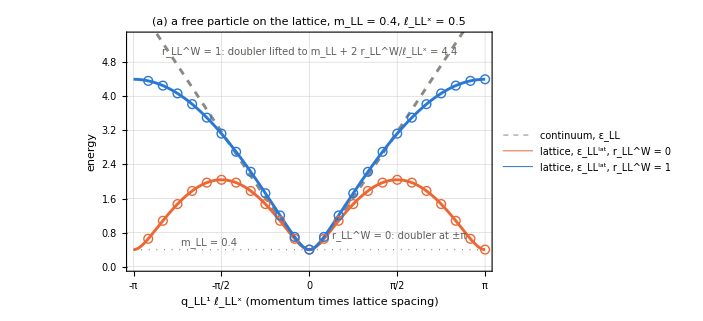
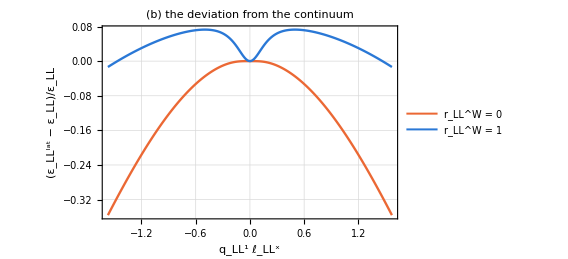
-Graphics--Graphics-Figure 1. The energy of a free particle on the lattice (item [1], check GS-16): the points are eigenvalues of the lattice operator of the solvers.

```mathematica
(* Figure 1: the energy of a free particle on the lattice; the colors of the project (blue, orange, grey) *)
blue = RGBColor["#2a78d6"]; orange = RGBColor["#eb6834"]; grey = RGBColor["#8a8984"]; muted = RGBColor["#5f5e5a"];
aqua = RGBColor["#1baf7a"]; green = RGBColor["#008300"]; red = RGBColor["#e34948"];
(* the registered symbols that appear in the labels of Figure 1 (Part I): the mass, the lattice spacing, the Wilson
   coefficient, the first component of the momentum, the two energies *)
{mSym, ellxSym, rWSym, q1Sym, epsSym, epsLatSym} = {Subscript[m, LL], Subscript[ℓ, LL]^x,
   Subscript[r, LL]^W, Subscript[q, LL]^1, Subscript[ε, LL],
   Subscript[ε, LL]^lat};
(* labels of graphics are typeset in TraditionalForm, which prints every single letter in italics; upright[e] keeps the
   letters of the symbols upright, as they are printed in the cells of the notebook (for example the roman W of the
   Wilson coefficient) *)
upright[e_] := Style[e, SingleLetterItalics -> False];
curve[rw_, col_] := Select[curves, #[[1]] == rw &][[All, col]];
qAxis = Select[curves, #[[1]] == 0. &][[All, 2]] dxFig;
fig1a = Show[
   ListLinePlot[{Transpose[{qAxis, curve[0., 3]}], Transpose[{qAxis, curve[0., 4]}], Transpose[{qAxis, curve[1., 4]}]},
    PlotStyle -> {Directive[grey, Dashed, Thickness[0.004]], Directive[orange, Thickness[0.004]], Directive[blue, Thickness[0.004]]},
    PlotLegends -> Placed[LineLegend[upright /@ {Row[{"continuum, ", epsSym}], Row[{"lattice, ", epsLatSym, ", ", rWSym, " = 0"}],
        Row[{"lattice, ", epsLatSym, ", ", rWSym, " = 1"}]}], Below]],
   ListPlot[{Select[points, #[[1]] == 0. &][[All, {2, 3}]] . DiagonalMatrix[{dxFig, 1}], Select[points, #[[1]] == 1. &][[All, {2, 3}]] . DiagonalMatrix[{dxFig, 1}]},
    PlotStyle -> {orange, blue}, PlotMarkers -> {"○", 9}],
   (* the labels are placed in empty regions of the plot (checked on the exported page); they are written in a muted
      ink, the colored curves next to them carry the identity *)
   Graphics[{muted, Dotted, Line[{{-Pi, mFig}, {Pi, mFig}}], Text[upright[Style[Row[{mSym, " = 0.4"}], 10, muted]], {-1.8, 0.56}],
     Text[upright[Style[Row[{rWSym, " = 1: doubler lifted to ", mSym, " + 2 ", rWSym, "/", ellxSym, " = 4.4"}], 10, muted]], {0, 5.05}],
     Text[upright[Style[Row[{rWSym, " = 0: doubler at ±π"}], 10, muted]], {1.6, 0.72}]}],
   PlotRange -> {{-Pi, Pi}, {0, 5.4}}, Axes -> False, Frame -> True,
   FrameLabel -> {upright[Row[{q1Sym, " ", ellxSym, " (momentum times lattice spacing)"}]], "energy"},
   FrameTicks -> {{Automatic, None}, {{{-Pi, "-π"}, {-Pi/2, "-π/2"}, {0, "0"}, {Pi/2, "π/2"}, {Pi, "π"}}, None}},
   GridLines -> Automatic, GridLinesStyle -> Directive[GrayLevel[0.9]], ImageSize -> 520,
   PlotLabel -> upright[Style[Row[{"(a) a free particle on the lattice, ", mSym, " = 0.4, ", ellxSym, " = 0.5"}], 12]]];
fig1b = ListLinePlot[Table[With[{sel = Select[curves, #[[1]] == rw && Abs[#[[2]] dxFig] <= Pi/2 + 1*^-12 &]}, Transpose[{sel[[All, 2]] dxFig, (sel[[All, 4]] - sel[[All, 3]])/sel[[All, 3]]}]], {rw, {0., 1.}}],
   PlotStyle -> {Directive[orange, Thickness[0.004]], Directive[blue, Thickness[0.004]]},
   PlotLegends -> Placed[LineLegend[upright /@ {Row[{rWSym, " = 0"}], Row[{rWSym, " = 1"}]}], {0.5, 0.15}],
   (* only the horizontal axis (deviation zero) is drawn; a vertical axis line would cross the legend *)
   Axes -> {True, False}, Frame -> True,
   FrameLabel -> upright /@ {Row[{q1Sym, " ", ellxSym}], Row[{"(", epsLatSym, " − ", epsSym, ")/", epsSym}]},
   GridLines -> Automatic, GridLinesStyle -> Directive[GrayLevel[0.9]], ImageSize -> 420, PlotLabel -> Style["(b) the deviation from the continuum", 12]];
Labeled[Row[{fig1a, fig1b}, "  "], Style["Figure 1. The energy of a free particle on the lattice (item [1], check GS-16): the points are eigenvalues of the lattice operator of the solvers.", 11], Top]
```

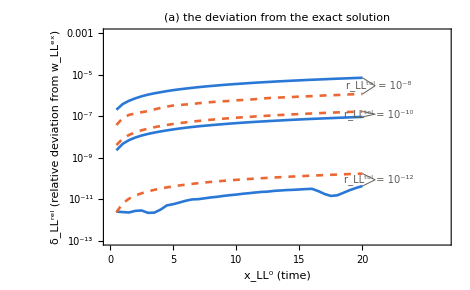
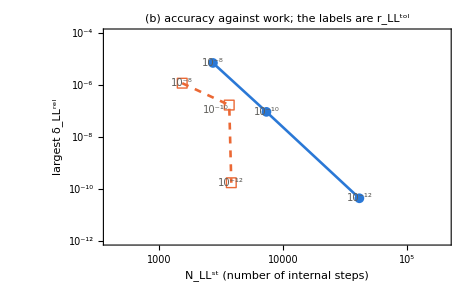
-Graphics--Graphics-
Figure 2. The time integration of the lattice equations (item [1], check GS-13): IDA in this notebook and CVODE in the original program.

```mathematica
(* Figure 2: the time integration of check GS-13.  Blue, full lines, filled circles: IDA in this notebook.  Orange, dashed
   lines, open squares: CVODE in the original program (the numbers of the file t2_cvode_accuracy.csv in the data cell
   above, and the numbers of steps of its report).  The output time 0, where the deviations are rounding errors of about
   1e-15, is left out of the logarithmic plot.  The positions of texts in a logarithmic plot are natural logarithms *)
{x0Sym, rtolSym, deltaRelSym, wExSym, nstSym} = {Subscript[x, LL]^0, Subscript[r, LL]^tol,
   Subscript[δ, LL]^rel, Subscript[w, LL]^ex, Subscript[N, LL]^st};
idaDev = Table[Transpose[{Rest[touts13], Rest[dev13[[kt]]]}], {kt, 3}];
cvDev = Table[Transpose[{Rest[t2origCvode[[All, 1]]], Rest[t2origCvode[[All, 1 + kt]]]}], {kt, 3}];
idaStyle = Directive[blue, Thickness[0.004]];
cvStyle = Directive[orange, Dashed, Thickness[0.004]];
(* the label of a tolerance, in the muted grey of the texts *)
tolLabel[kt_] := upright[Style[Row[{rtolSym, " = ", Superscript[10, -6 - 2 kt]}], 10, muted]];
tolShort[kt_] := Style[Superscript[10, -6 - 2 kt], 10, muted];
(* the curves end at the time 20.  The two curves of one tolerance are joined, by two thin grey lines from
   their ends, to the label of the tolerance, which stands to the right of the curves at the geometric mean of
   the two last deviations; the time axis is therefore drawn to 26.5, with tick marks up to 20 *)
endIda = Map[Last, dev13];
endCv = Table[t2origCvode[[-1, 1 + kt]], {kt, 3}];
labelAt = Sqrt[endIda endCv];
pairLabels = Table[{Directive[muted, Thickness[0.0015]],
     Line[{{20, Log[endIda[[kt]]]}, {21, Log[labelAt[[kt]]]}, {20, Log[endCv[[kt]]]}}],
     Text[tolLabel[kt], {21.3, Log[labelAt[[kt]]]}, {-1, 0}]}, {kt, 3}];
fig2a = ListLogPlot[Join[idaDev, cvDev], Joined -> True, PlotStyle -> Join[ConstantArray[idaStyle, 3], ConstantArray[cvStyle, 3]],
   PlotRange -> {{0, 26.5}, {1*^-13, 1*^-3}}, Frame -> True, FrameTicks -> {{Automatic, None}, {Range[0, 20, 5], None}},
   FrameLabel -> {upright[Row[{x0Sym, " (time)"}]], upright[Row[{deltaRelSym, " (relative deviation from ", wExSym, ")"}]]},
   GridLines -> {Range[0, 20, 5], Automatic}, GridLinesStyle -> Directive[GrayLevel[0.9]], ImageSize -> 470,
   Epilog -> pairLabels,
   PlotLabel -> Style["(a) the deviation from the exact solution", 12]];
(* the largest deviation against the number of internal steps; every point is labelled with its tolerance: the
   labels of IDA stand to the right of their points, those of CVODE to the left (the second one to the left and
   below its point, clear of the line that arrives there) *)
idaWork = Transpose[{steps13, maxdev13}];
cvWork = Transpose[{cvSteps13, cvMax}];
fig2b = ListLogLogPlot[{idaWork, cvWork}, Joined -> True, PlotStyle -> {idaStyle, cvStyle},
   PlotMarkers -> {{"●", 10}, {"□", 10}}, PlotRange -> {{400, 200000}, {1*^-12, 1*^-4}}, Frame -> True,
   FrameLabel -> {upright[Row[{nstSym, " (number of internal steps)"}]], upright[Row[{"largest ", deltaRelSym}]]},
   GridLines -> Automatic, GridLinesStyle -> Directive[GrayLevel[0.9]], ImageSize -> 470,
   Epilog -> Join[Table[Text[tolShort[kt], Log[idaWork[[kt]]], {-1.6, 0}], {kt, 3}],
     MapThread[Text[tolShort[#1], Log[cvWork[[#1]]], #2] &, {{1, 2, 3}, {{1.6, 0}, {1.3, 1.8}, {1.6, 0}}}]],
   PlotLabel -> Style[upright[Row[{"(b) accuracy against work; the labels are ", rtolSym}]], 12]];
legend2 = LineLegend[{idaStyle, cvStyle}, {"IDA (this notebook)", "CVODE (original program t2_fields)"}, LegendLayout -> "Row"];
Labeled[Column[{Row[{fig2a, fig2b}, "  "], legend2}, Center],
  Style["Figure 2. The time integration of the lattice equations (item [1], check GS-13): IDA in this notebook and CVODE in the original program.", 11], Top]
```

### Summary of item [1]

```mathematica
Grid[Prepend[Map[{#["name"], If[#["pass"], Style["PASS", Darker[Green]], Style["FAIL", Red]], #["statement"]} &,
    Select[SL31`Test`$Results, StringStartsQ[#["name"], "GS-" | "T2-"] &]], Style[#, Bold] & /@ {"check", "result", "statement"}],
  (* no fixed column widths: the front end wraps the statements at the width of the window or of the printed page *)
  Frame -> All, Alignment -> {Left, Top}]
```

check | result | statement
T2-SYM | PASS | every component of a registered family that is typed in an input cell of the notebook (collected from the source by the builder) is read as one atomic symbol, and its TeX is written from its printed form, without the internal name
T2-RNG | PASS | the generator SplitMix64 gives, for the seed 2026111707, the integers and the uniform numbers of the original algorithm
T2-LINALG | PASS | the rewritten eigensolver and matrix exponential of cmat.rs agree with Eigenvalues and MatrixExp of the Wolfram Language
T2-IDA | PASS | the integrator IDA of SUNDIALS, used through NDSolve with Method -> "IDA": (a) on the decaying exponential (rtol = 1e-8, atol = 1e-10, x_LL^0 from 0 to 25) the exact local error of every internal step is at most the tolerance rtol |value| + atol of the step, and the largest ratio of the local error to this tolerance exceeds 1/128 both while the solution is above 10 atol/rtol and after it has fallen below atol/(10 rtol): the tolerances of IDA are 10^-PrecisionGoal and 10^-AccuracyGoal; (b) on a Hermitian 2 x 2 matrix (rtol = 1e-10, atol = 1e-12, 21 output times up to 10) every local error is at most budget_step = rtol (norm of the state) + atol sqrt(4), the largest deviation from the solution by MatrixExp is at most budget_out, and the states of NDSolve are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12); (c) the function t2evolveIDAChecked, which makes these measurements for the checks of the later chapters, gives the same states and the same bounds as (b); the sum of its measured local errors is at most budget, and the largest deviation is at most the bound made with this sum in place of budget, which is at most budget_out
GS-1 | PASS | the Dirac matrices are built from the frame of R^(1,3)_LL; Clifford relations; gamma_ch = diag(-1,-1,1,1), C_LL = diag(eps2, -eps2), alpha^j = diag(-sigma_j, sigma_j), eps2 = M_LL(-e2)
GS-2 | PASS | the Lorentz generators of the super-loop on the Dirac spinor, sgen(J^j) = diag(-i sigma_j/2, -i sigma_j/2) = gamma^j' gamma^j''/2, sgen(K^j) = diag(-sigma_j/2, sigma_j/2) = gamma^0 gamma^j/2; the 27 relations of so(3,1); 24 intertwining relations [gamma^p, sgen(u)] = sum V(u)[p][q] gamma^q
GS-3 | PASS | the gauge group SL(2,C) as a change of representation: Sspin^-1 gamma^p Sspin = sum Lmat[p][q] gamma^q and Sspin gamma^p[f] Sspin^-1 = gamma^p[gLt f gLt^dag] for 200 random gL and random Hermitian frames (tolerance 1e-10)
GS-4 | PASS | isospin T^iota obeys [T^a, T^b] = i eps T^c and commutes with the Lorentz generators; the pair matrices Kch_iota are antisymmetric, Lorentz invariant and an isospin vector (100 random gL and U); Psi^T Kch Psi = 0 for a c-number spinor (tolerance 1e-10)
GS-5 | PASS | gauge covariance of the covariant derivative: nabla'_p (Ucal Psi) = Ucal nabla_p Psi for Ucal(x) = exp(i thF) Sspin(gL(x)) (x) U(x), with the transformed AF, Av and Gamma (20 random points, central differences with the step 1e-5; relative tolerance 1e-7)
GS-6 | PASS | the commutator of two covariant derivatives is the curvature of the gauge group: [nabla_p, nabla_q] Psi = (Rc_pq - i g_v Fv^iota_pq T^iota - i g_F FF_pq) Psi (20 random points, all 12 ordered pairs; central differences with the step 1e-4; relative tolerance 1e-6)
GS-7 | PASS | the super-loop form of the Dirac operator: gamma^p nabla_p has the Weyl blocks M_LL(D) and M_LL(conj D) and no diagonal blocks; (gamma.nabla)^2 = eta nabla nabla + (1/4)[gamma^p, gamma^q][nabla_p, nabla_q]; for a free plane wave M_LL(D) M_LL(conj D) = -N_LL(k) sigma_0 (50 random momenta and fields; tolerance 1e-12)
GS-8 | PASS | the Dirac-Bogoliubov-de Gennes operator H_DB(q) with constant gauge fields is Hermitian and particle-hole symmetric (50 random momenta, fields and order parameters); for the polar order parameter (0, 0, Delta) its spectrum is +-E^(+-), each four times (30 random momenta; m = 0.4, mu = 0.3; tolerance 1e-10)
GS-9 | PASS | the self-consistency of the mean field: for the polar order parameter the sum over the eight positive-energy eigenvectors of psi_p^T Kch_3 conj(psi_h) equals -2 Delta (1/E^+ + 1/E^-), so that the mode-sum form of the mean-field equations gives the gap equation 1/G = int d^3q/(2 pi)^3 (1/E^+ + 1/E^-) (30 random momenta; tolerance 1e-10)
GS-10 | PASS | the lattice operator H_lat on a 3 x 2 x 4 lattice (dx = 0.7, r_W = 1, periodic in x and z) with random links, potentials and order parameters is Hermitian, particle-hole symmetric and exactly gauge covariant; on a free periodic chain of 12 sites its spectrum is +-eps_lat, each eight times; the Wilson term lifts the doubler to m + 2 r_W/dx; the spectral radius stays below the bound Hbound (tolerance 1e-10)
GS-11 | PASS | the Hermitian eigensolver of t2core (Householder reduction and implicit QL), rewritten above: for random Hermitian matrices of the dimensions 7, 64 and 200 the eigenvectors are orthonormal and reproduce the matrix (relative tolerance 1e-11)
GS-12 | PASS | the printed formulas agree with the matrices that they describe: the entries of Ppair (symbolic d), of the blocks of sgen(u_p) and of Gamma_p, the expansions of the covariant derivatives, the sixteen equations of the Dirac-Bogoliubov-de Gennes system, the pair operators Pi and the eight exact equations, each evaluated for numbers assigned to its symbols and compared with the matrix computation (tolerance 1e-12)
GS-13 | PASS | time integration: the lattice equations (i times the derivative of the Nambu mode w_lat with respect to the time x_LL^0 equals H_lat w_lat) are integrated by IDA (SUNDIALS, through NDSolve with Method -> "IDA": backward differentiation formulas of the orders 1 to 5 with local error control and Newton's method; the tolerance of every real unknown is rtol times its modulus plus atol) in place of CVODE of the original program; on the 3 x 2 x 4 lattice of GS-10 (384 complex components), from the random initial state of the norm 1 of the original program, for each of rtol = 1e-8, 1e-10, 1e-12 (atol = rtol/100): (1) the exact local error local_error of every internal step is at most budget_step = rtol (norm of the state) + atol sqrt(768); (2) the states at the 41 output times x_LL^0 = 0, 0.5, ..., 20 are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12), and their largest relative deviation from the exact spectral solution w_exact is at most budget_out = (1 + h_IDA E_max/4) budget + h_IDA deriv_residual/4 + (h_IDA E_max)^4/384 with budget = N_steps budget_step; (3) the largest deviation decreases from rtol = 1e-8 to 1e-10 to 1e-12; (4) for rtol = 1e-12 it stays below 1e-9, and the norm of the state changes by less than 1e-10
GS-14 | PASS | the super-loop form of the Dirac isodoublet and of its field equations: (a) a frame matrix is the right multiplication of the spinor charge; (b) gamma^p[f] Psi(bSm, bSp) = Psi(bSp conj f_p, bSm f_p); (c) the gauge group acts by the automorphisms of the super-loop; (d) the covariant derivative acts through the derivations of B_LL; (e) the Dirac operator is sum_p R_(f_p) nabla_p (tolerance 1e-12, 1e-10 for (c))
GS-15 | PASS | the Lorentz connection is fixed by the frame: for an x-dependent Lorentz transformation the connection -(d_p Sspin) Sspin^-1 has the form sgen(u), the Dirac matrices of the transformed frame are covariantly constant and the curvature vanishes (20 random points; tolerance 1e-6); the 24 commutators [sgen(J^j), gamma^q], [sgen(K^j), gamma^q] have the rank 6 (smallest Gram eigenvalue > 1e-6)
GS-16 | PASS | the lattice operator of the solvers on plane waves: on a periodic chain of 24 sites (dx = 0.5, m = 0.4) the image of a plane wave is a plane wave of the same momentum, and the 16 x 16 matrix of the images has the eigenvalues -eps_lat (eightfold) and +eps_lat (eightfold) at all 24 momenta, for r_W = 0 and 1 (tolerance 1e-12)
T2-DATA-1 | PASS | the numbers of the figures agree with the data files written by the original program t2_fields: the 48 eigenvalues of the lattice operator and the 802 points of the curves of Figure 1 (tolerance 5.1e-11, half a unit of the last printed decimal); the file of the integrations by CVODE of Figure 2 has the 41 output times of GS-13 (tolerance 5.1e-5), and its relative deviations from the exact solution are below 1e-13 at x_LL^0 = 0, stay below 1e-9 for rtol = 1e-12, and their largest values decrease from rtol = 1e-8 to 1e-10 to 1e-12, as the original check GS-13 states

## II.3 Item [2]: analytic solutions of the field equations, and the checks AS-1 to AS-10 (program t2_analytic)

The program t2_analytic (t2analytic/src/main.rs) answers item [2] of Test 2, which asks for an analysis of the field equations and for analytic solutions of simple cases. It solves the mean-field (Dirac-Bogoliubov-de Gennes) equations exactly in four cases and checks every solution twice: against the continuum equations, and against the lattice operator ℋ_LL^lat of chapter II.1.4, the operator that the solvers of the items [3] and [5] integrate. The solutions are therefore also test problems with known answers for those solvers. The cases are: A, free spinor charges in constant gauge potentials (checks AS-1 and AS-2); B, the uniform polar superfluid (AS-3 to AS-6); C, a domain wall of the pair field (AS-7 to AS-9); D, constant magnetic fields (AS-10). The rewriting below keeps the order of the original program, because its random numbers are drawn in that order from one generator with the seed 2026111708; the checks AS-3, AS-7 and AS-8 draw random numbers, the others draw none. Every check prints one line with PASS or FAIL. The statement is that of the original report (in the two checks with a time integration, AS-2 and AS-4, it names IDA in place of CVODE and states what is required of IDA); the numbers in the details are the results of the Wolfram Language, followed by the values of the original report.

The equations. All four cases are computed in the canonical gauge, in which the spin connection vanishes (Γ_p^LL==0); a gauge transformation carries every solution into any other gauge. A mode has the particle part ψ_LL^p and the hole part ψ_LL^h, each with the eight components of chapter II.1.3 (the components 1, 3, 5, 7 have isospin up, the components 2, 4, 6, 8 isospin down). The mean-field equations are

i∂_0 ψ_LL^p==(h_LL^∇-A_(LL,0)-μ_LL)ψ_LL^p+P_LL ψ_LL^h

i∂_0 ψ_LL^h==P_LL^†ψ_LL^p-(h_LL^∇-A_(LL,0)-μ_LL)^*ψ_LL^h

with the covariant Dirac Hamiltonian h_LL^∇==-i ∑_j α_LL^j∇_j^LL +β_LL m_LL, the covariant derivative ∇_j^LL ==∂_j -i A_(LL,j), the gauge matrices A_(LL,p)==g_LL^v ∑_ι A_(LL,p)^ι T_LL^ι+g_LL^F A_(LL,p)^F 1_8 of the potentials, the chemical potential μ_LL, and the pairing block P_LL==∑_ι d_LL^ι(K_LL^ι)^† of the order parameter (d⃗)_LL==(d_LL^1,d_LL^2,d_LL^3). The matrices α_LL^j==diag(-σ_j^LL,σ_j^LL) and β_LL==γ_LL^0 act on the Dirac index, the potentials on the isospin index. The operator on the right side is the Dirac-Bogoliubov-de Gennes operator ℋ_LL^DB; a stationary mode depends on the time through the factor exp(-i E_(LL,n)^qp x_LL^0), and its energy E_(LL,n)^qp is an eigenvalue of ℋ_LL^DB. If all fields are constant in space, the modes are plane waves, exp(i ∑_j q_LL^j x_LL^j) times a constant vector of 16 components, and the field equations are the eigenvalue problem of a 16×16 matrix.

The lattice of the checks. Every lattice of this chapter is a periodic chain (a ring) of n_LL^x sites along x_LL^1, with the spacing ℓ_LL^x and the Wilson coefficient r_LL^W==1. Its allowed momenta q_LL^1 are the integer multiples of 2π/(n_LL^x ℓ_LL^x); the function t2chainMomentum returns the allowed momentum with a given number (counted from 0) in the interval from -π/ℓ_LL^x (excluded) to π/ℓ_LL^x (included). If the fields are the same on every site, the lattice operator maps a plane wave to a plane wave of the same momentum, as in check GS-16; the function t2planeMatrix applies the operator to the 16 plane waves of one momentum (one for each component of a site) and returns the 16×16 matrix of their images at the first site. The function t2h8 returns the matrix h_LL((q⃗)_LL)==∑_j α_LL^j q_LL^j+β_LL m_LL of a plane wave of the continuum, as an 8×8 matrix (it acts as the unit matrix on the isospin index). The cell also sets the seed and the matrices that several checks use; they are exact (their entries are the integers 0, 1, -1 and the imaginary unit).

```mathematica
(* the seed of the program t2_analytic *)
t2Seed[2026111708];
(* the couplings g^v, g^F and the mass m: the same numbers as in chapter II.2 (the original program sets them again) *)
gv = 0.7; gf = 0.45; mass = 0.4;
(* a chain has more than one site only in the direction x^1: the argument of t2epsLat and t2hLatPlane that says so *)
asChainActive = {True, False, False};
(* the places of the isospin-up and of the isospin-down components among the eight components of a site *)
asUpIndex = {1, 3, 5, 7}; asDownIndex = {2, 4, 6, 8};
(* the matrices that several checks use: the pair matrix K^3 of the third isospin direction and its Hermitian
   conjugate, the matrices alpha^1, alpha^2, alpha^3 and beta on the eight components (Dirac (x) isospin) *)
asK3 = t2kpair[3];
asK3dag = ConjugateTranspose[asK3];
asAlpha = Table[t2lift4[t2alpha[j]], {j, 3}];
asBeta = t2lift4[t2beta];
(* the allowed momentum number kq (0, 1, ..., nsites - 1) of a periodic chain of nsites sites with the spacing ell,
   in the interval (-pi/ell, pi/ell] *)
t2chainMomentum[kq_Integer, nsites_Integer, ell_] := 2. Pi If[kq <= Quotient[nsites, 2], kq, kq - nsites]/(nsites ell);
(* the 16 x 16 matrix of the lattice operator on the plane waves exp(i q x^1) e_b of a periodic chain (b = 1..16, the
   components of a site): with fields that are the same on every site, the image of a plane wave is a plane wave of
   the same momentum; its 16 components at the first site are the column b.  The 16 plane waves are the columns of
   the matrix planeWaves, to which t2apply applies the operator column by column *)
t2planeMatrix[lattice_, fields_, q_] := Module[{nsites = t2nsites[lattice], planeWaves},
   planeWaves = Table[If[Mod[row - 1, 16] + 1 == b, Exp[I q lattice["ell"] Quotient[row - 1, 16]], 0. I], {row, 16 nsites}, {b, 16}];
   t2apply[lattice, fields, planeWaves][[1 ;; 16]]];
(* h(q) = sum_j alpha^j q_j + beta m on Dirac (x) isospin (8 x 8), the plane-wave Hamiltonian of the continuum *)
t2h8[q_List, m_] := m asBeta + Sum[q[[j]] asAlpha[[j]], {j, 3}];
(* numbers in the details of the checks: two significant digits with a power of ten; a fixed number of decimals *)
asSci[x_?NumericQ] := ScientificForm[x, 2];
asSci[l_List] := Row[Riffle[Map[ScientificForm[#, 2] &, l], ", "]];
asFix[x_?NumericQ, decimals_Integer] := NumberForm[x, {20, decimals}];
(* the largest deviation of the columns cols of two lists of rows; Infinity if the lists have different dimensions *)
t2rowsDeviation[rowsHere_, rowsOriginal_, cols_] := If[Dimensions[rowsHere] === Dimensions[rowsOriginal],
   Max[Abs[rowsHere[[All, cols]] - rowsOriginal[[All, cols]]]], Infinity];
```

### Case A: free spinor charges in constant gauge potentials (checks AS-1 and AS-2)

The fields. No pair field ((d⃗)_LL==0), and constant potentials of the fermion number and of the third isospin direction, A_(LL,p)^F and A_(LL,p)^3, with A_(LL,p)^1==A_(LL,p)^2==0. The generator T_LL^3 is diagonal, so the gauge matrix A_(LL,p) is diagonal in the isospin index: it has the eigenvalue A_(LL,p)^↑==g_LL^F A_(LL,p)^F+1/2 g_LL^v A_(LL,p)^3 on the isospin-up components (the charge Q_LL==T_LL^3==+1/2) and the eigenvalue A_(LL,p)^↓==g_LL^F A_(LL,p)^F-1/2 g_LL^v A_(LL,p)^3 on the isospin-down components (Q_LL==-1/2). The field strengths vanish.

The solution. Take a particle of isospin up, ψ_LL^p==exp(i ∑_j q_LL^j x_LL^j-i E_(LL,n)^qp x_LL^0)χ_LL^pw with a constant spinor χ_LL^pw (a Dirac spinor times the isospin vector (1,0)^T), and ψ_LL^h==0. The covariant derivative gives ∇_j^LL ψ_LL^p==i(q_LL^j-A_(LL,j)^↑)ψ_LL^p, and the field equations become the eigenvalue problem E_(LL,n)^qp χ_LL^pw==(∑_j α_LL^j(q_LL^j-A_(LL,j)^↑)+β_LL m_LL-A_(LL,0)^↑-μ_LL)χ_LL^pw. The Dirac matrices obey (α_LL^j)^2==β_LL^2==1_4, α_LL^j α_LL^j'+α_LL^j' α_LL^j==0 for j≠j' and α_LL^j β_LL+β_LL α_LL^j==0 (check GS-1). The matrix ∑_j α_LL^j(q_LL^j-A_(LL,j)^↑)+β_LL m_LL therefore squares to ∑_j (q_LL^j-A_(LL,j)^↑)^2+m_LL^2 times the unit matrix, and its eigenvalues are the two square roots of this number, each twice. A hole (with ψ_LL^p==0) obeys the second field equation, whose operator -(h_LL^∇-A_(LL,0)-μ_LL)^* contains the charges with the opposite sign. The energies of the isospin-up components are, each twice,

E_(LL,n)^qp==±(∑_j (q_LL^j-A_(LL,j)^↑)^2+m_LL^2)^(1/2)-A_(LL,0)^↑-μ_LL   (particles),      E_(LL,n)^qp==∓(∑_j (q_LL^j+A_(LL,j)^↑)^2+m_LL^2)^(1/2)+A_(LL,0)^↑+μ_LL   (holes)

and those of the isospin-down components are the same with A_(LL,p)^↓ in place of A_(LL,p)^↑. On the lattice the square roots are replaced by the lattice energy ε_LL^lat of check GS-16 at the shifted momenta. This is exact: the link matrix U_(LL,1)^link==exp(-i ℓ_LL^x A_(LL,1)) multiplies the plane wave at the next site by exp(-i ℓ_LL^x A_(LL,1)^↑), which shifts the momentum in the differences of the lattice operator by exactly A_(LL,1)^↑.

What it shows. The space components of a potential shift the momentum (minimal coupling): the plane wave with the label q_LL^1 has its lowest energy at q_LL^1==A_(LL,1)^↑. The time component shifts the energy, exactly as a change of the chemical potential would. In infinite space a gauge transformation removes both shifts. On a ring the gauge function would have to be periodic, and it is periodic only if exp(i A_(LL,1)n_LL^x ℓ_LL^x) is the unit matrix. This matrix is the product of the link matrices around the ring (a Wilson loop), which no gauge transformation changes; if it is not the unit matrix, the ring encloses a flux, and the energies at the allowed momenta are truly shifted (the Aharonov-Bohm effect). Check AS-1 uses a ring of 32 sites (ℓ_LL^x==0.5, circumference 16, m_LL==0.4, μ_LL==0.2) with the potentials A_(LL,1)^3==0.8 and A_(LL,1)^F==0.6 in the links and A_(LL,0)^3==0.5 and A_(LL,0)^F==0.3 in the potential matrix, so that A_(LL,1)^↑==0.55, A_(LL,1)^↓==-0.01, A_(LL,0)^↑==0.31 and A_(LL,0)^↓==-0.04. For every allowed momentum it compares the 16 eigenvalues of t2planeMatrix with the formula, restricts the particle block (the rows and columns 1 to 8) to each isospin component and compares its four eigenvalues with the formula, and checks that the particle block does not connect the two isospin components. Figure 3(a) shows the energies of the particle block.

```mathematica
(* AS-1: the potentials Av^3_1, AF_1 (in the links), Av^3_0, AF_0 (in the potential matrix), the chemical potential;
   a chain of 32 sites with the spacing 0.5 *)
{as1Av31, as1AF1, as1Av30, as1AF0, as1Mu} = {0.8, 0.6, 0.5, 0.3, 0.2};
{as1N, as1Ell} = {32, 0.5};
as1Lat = <|"n" -> {as1N, 1, 1}, "ell" -> as1Ell, "periodic" -> {True, False, False}, "wilson" -> 1.0, "mass" -> mass, "mu" -> as1Mu|>;
as1Fields = t2trivialFields[as1N];
Do[as1Fields[["links", site, 1]] = t2link[gv, gf, {0., 0., as1Av31}, as1AF1, as1Ell];
  as1Fields[["v0", site]] = t2potential[gv, gf, {0., 0., as1Av30}, as1AF0], {site, as1N}];
(* Acal_p of the isospin component with the charge qq = +1/2 (up) or -1/2 (down): p = 1 and p = 0 *)
as1Acal1[qq_] := gf as1AF1 + qq gv as1Av31;
as1Acal0[qq_] := gf as1AF0 + qq gv as1Av30;
as1Dev = 0.;
(* the rows {q, Q_LL, E_qp} of the points of Figure 3(a), in the order of the original data file *)
as1LatticeRows = {};
Do[
  Module[{q = t2chainMomentum[kq, as1N, as1Ell], m16, ev, expect, pblock},
   m16 = t2planeMatrix[as1Lat, as1Fields, q];
   (* all 16 eigenvalues: particles +-eps_lat(q - Acal_1) - Acal_0 - mu, holes -(+-eps_lat(q + Acal_1) - Acal_0 - mu), each twice *)
   ev = First[t2eigh[m16]];
   expect = Sort[Flatten[Table[
       With[{ep = t2epsLat[{q - as1Acal1[qq], 0., 0.}, as1Ell, mass, 1.0, asChainActive],
         eh = t2epsLat[{q + as1Acal1[qq], 0., 0.}, as1Ell, mass, 1.0, asChainActive]},
        Table[{ep - as1Acal0[qq] - as1Mu, -ep - as1Acal0[qq] - as1Mu, eh + as1Acal0[qq] + as1Mu, -eh + as1Acal0[qq] + as1Mu}, {2}]],
       {qq, {0.5, -0.5}}]]];
   as1Dev = Max[as1Dev, Max[Abs[ev - expect]]];
   (* the particle block (rows and columns 1..8), restricted to each isospin component *)
   pblock = m16[[1 ;; 8, 1 ;; 8]];
   Do[
    Module[{idx = If[qq > 0, asUpIndex, asDownIndex], evq, ep, ex},
     evq = First[t2eigh[pblock[[idx, idx]]]];
     ep = t2epsLat[{q - as1Acal1[qq], 0., 0.}, as1Ell, mass, 1.0, asChainActive];
     ex = Sort[{-ep - as1Acal0[qq] - as1Mu, -ep - as1Acal0[qq] - as1Mu, ep - as1Acal0[qq] - as1Mu, ep - as1Acal0[qq] - as1Mu}];
     as1Dev = Max[as1Dev, Max[Abs[evq - ex]]];
     Do[AppendTo[as1LatticeRows, {q, qq, evq[[i]]}], {i, 4}]],
    {qq, {0.5, -0.5}}];
   (* the particle block does not mix the two isospin components (the potentials point along tau_3) *)
   as1Dev = Max[as1Dev, Max[Abs[pblock[[asUpIndex, asDownIndex]]]]]],
  {kq, 0, as1N - 1}];
(* the rows {q, Q_LL, branch, E_qp} of the curves of Figure 3(a): the formula on 401 momenta; branch 1: the positive
   square root, -1: the negative one *)
as1CurveRows = Flatten[Table[
    With[{q = -Pi/as1Ell + 2 Pi/as1Ell i/400.},
     Flatten[Table[With[{ep = t2epsLat[{q - as1Acal1[qq], 0., 0.}, as1Ell, mass, 1.0, asChainActive]},
        {{q, qq, 1, ep - as1Acal0[qq] - as1Mu}, {q, qq, -1, -ep - as1Acal0[qq] - as1Mu}}], {qq, {0.5, -0.5}}], 1]],
    {i, 0, 400}], 1];
SL31Check["AS-1", "free spinor charges in constant gauge potentials (case A): on a periodic chain of 32 sites along x_LL^1 (dx = 0.5, r_W = 1, m = 0.4, mu = 0.2, g_v = 0.7, g_F = 0.45) with the constant potentials Av_LL^3_1 = 0.8 and AF_LL_1 = 0.6 (in the links) and Av_LL^3_0 = 0.5 and AF_LL_0 = 0.3 (in the potential matrix), and no pair field, the 16 eigenvalues of the lattice operator on the plane wave of each allowed momentum q are, for each isospin component (Q_LL = +1/2 with Acal_up_p = g_F AF_LL_p + g_v Av_LL^3_p/2, Q_LL = -1/2 with Acal_down_p = g_F AF_LL_p - g_v Av_LL^3_p/2), +-eps_lat(q - Acal_1) - Acal_0 - mu (particles) and -(+-eps_lat(q + Acal_1) - Acal_0 - mu) (holes), each twice: the potential of the space direction shifts the momentum (minimal coupling q -> q - Acal_1) and the potential of the time direction shifts the energy; the particle block does not mix the two isospin components, and its restriction to each component has the eigenvalues +-eps_lat(q - Acal_1) - Acal_0 - mu (tolerance 1e-12)",
  as1Dev < 1*^-12,
  Row[{"largest deviation ", asSci[as1Dev], "; Acal_up_1 = ", asFix[as1Acal1[0.5], 4], ", Acal_down_1 = ", asFix[as1Acal1[-0.5], 4], ", Acal_up_0 = ", asFix[as1Acal0[0.5], 4],
    ", Acal_down_0 = ", asFix[as1Acal0[-0.5], 4], " (original: 9.8e-15; 0.5500, -0.0100, 0.3100, -0.0400)"}]]
```

PASS  AS-1: free spinor charges in constant gauge potentials (case A): on a periodic chain of 32 sites along x_LL^1 (dx = 0.5, r_W = 1, m = 0.4, mu = 0.2, g_v = 0.7, g_F = 0.45) with the constant potentials Av_LL^3_1 = 0.8 and AF_LL_1 = 0.6 (in the links) and Av_LL^3_0 = 0.5 and AF_LL_0 = 0.3 (in the potential matrix), and no pair field, the 16 eigenvalues of the lattice operator on the plane wave of each allowed momentum q are, for each isospin component (Q_LL = +1/2 with Acal_up_p = g_F AF_LL_p + g_v Av_LL^3_p/2, Q_LL = -1/2 with Acal_down_p = g_F AF_LL_p - g_v Av_LL^3_p/2), +-eps_lat(q - Acal_1) - Acal_0 - mu (particles) and -(+-eps_lat(q + Acal_1) - Acal_0 - mu) (holes), each twice: the potential of the space direction shifts the momentum (minimal coupling q -> q - Acal_1) and the potential of the time direction shifts the energy; the particle block does not mix the two isospin components, and its restriction to each component has the eigenvalues +-eps_lat(q - Acal_1) - Acal_0 - mu (tolerance 1e-12)  -- largest deviation 1.5e-14; Acal_up_1 = 0.5500, Acal_down_1 = -0.0100, Acal_up_0 = 0.3100, Acal_down_0 = -0.0400 (original: 9.8e-15; 0.5500, -0.0100, 0.3100, -0.0400)

The isospin turns in a constant isospin potential (check AS-2). Now only A_(LL,0)^1 differs from zero, and it is constant: A_(LL,0)==1/2 g_LL^v A_(LL,0)^1 τ_1^LL. This matrix acts on the isospin index and commutes with h_LL^∇, so the evolution of the particle part is a product, exp(-i(h_LL^∇-A_(LL,0)-μ_LL)x_LL^0)==exp(-i(h_LL^∇-μ_LL)x_LL^0) exp(i A_(LL,0)x_LL^0). Because (τ_1^LL)^2==σ_0^LL, the second factor is exp(i A_(LL,0)x_LL^0)==cos(1/2 ω_LL^pr x_LL^0) σ_0^LL+i sin(1/2 ω_LL^pr x_LL^0) τ_1^LL with ω_LL^pr==g_LL^v A_(LL,0)^1. A particle that starts as a plane wave of positive energy with isospin up, χ_LL^pw times the isospin vector (1,0)^T, therefore has at the time x_LL^0 the phase factor exp(-i(ε_LL^lat-μ_LL)x_LL^0) and the isospin vector (cos(1/2 ω_LL^pr x_LL^0), i sin(1/2 ω_LL^pr x_LL^0))^T, and its probability of isospin up is

P_LL^↑(x_LL^0)==cos^2(1/2 ω_LL^pr x_LL^0),      ω_LL^pr==g_LL^v A_(LL,0)^1

The isospin turns about the direction of the potential with the angular frequency ω_LL^pr. The potential has zero field strength, and the rotation is exactly the gauge transformation U_LL==exp(i A_(LL,0)x_LL^0) that removes it: in the gauge without the potential the isospin of the same particle stays up. The isospin direction of a single mode is therefore not gauge invariant; only its direction relative to other objects that carry isospin is. For the solvers this solution is a sharp test of the isospin structure of the potential term. Check AS-2 takes a ring of 16 sites (ℓ_LL^x==0.5, μ_LL==0.2, A_(LL,0)^1==1.5, so ω_LL^pr==1.05) and the plane wave of the allowed momentum number 2 with isospin up, integrates the lattice equations to the 101 output times x_LL^0==0,0.16,…,16 (the interval between the output times is ℓ_LL^t==0.16), and compares the whole state with the exact solution. The original program integrates with CVODE (r_LL^tol==10^-12, a_LL^tol==10^-14) and requires a relative deviation δ_LL^rel below 10^-9. The notebook integrates with IDA and the same tolerances (function t2evolveIDAChecked of chapter II.1.5) and keeps this requirement. It requires in addition that the states at the output times are the cubic Hermite polynomials of the stored values and derivatives, and that the largest deviation is at most the bound that follows from the measured local errors: the sum of the exact local errors δ_LL^loc of all internal steps bounds the deviation at the end of every step (the evolution is unitary), and chapter II.1.5 carries such a bound to the output times, with this sum in place of B_LL^err. The largest ratio of a local error to B_LL^loc is printed for information; it is not required to stay below 1, because IDA tests its own estimate of the error, in a weighted norm that averages over all real unknowns, and half of the real unknowns of this state (the hole components) are exactly zero at all times. Figure 3(b) shows the probability of isospin up.

```mathematica
(* AS-2: a chain of 16 sites; the constant isospin potential Av^1_0 = 1.5 along tau_1 in the potential matrix *)
{as2N, as2Ell, as2Mu, as2Av10} = {16, 0.5, 0.2, 1.5};
as2Lat = <|"n" -> {as2N, 1, 1}, "ell" -> as2Ell, "periodic" -> {True, False, False}, "wilson" -> 1.0, "mass" -> mass, "mu" -> as2Mu|>;
as2Fields = t2trivialFields[as2N];
Do[as2Fields[["v0", site]] = t2potential[gv, gf, {as2Av10, 0., 0.}, 0.], {site, as2N}];
(* the allowed momentum number 2, and the eigenvector of the largest eigenvalue eps_lat of the 4 x 4 matrix of the
   free lattice operator on its plane wave: the Dirac spinor of chi_pw *)
as2Q = t2chainMomentum[2, as2N, as2Ell];
{as2E4, as2V4} = t2eigh[t2hLatPlane[{as2Q, 0., 0.}, as2Ell, mass, 1.0, asChainActive]];
as2Eps = as2E4[[4]];
as2Chi4 = as2V4[[All, 4]];
as2OmegaPr = gv as2Av10;
(* the exact solution at the time x0: on every site the eight particle components chi_pw (x) (cos, i sin) times the
   phase factors of the time and of the plane wave; the hole components are zero *)
as2Exact[x0_?NumericQ] := Flatten[Table[
    With[{phaseSite = Exp[-I (as2Eps - as2Mu) x0] Exp[I as2Q as2Ell site]},
     Join[Flatten[Table[{as2Chi4[[a]] phaseSite Cos[0.5 as2OmegaPr x0], as2Chi4[[a]] phaseSite I Sin[0.5 as2OmegaPr x0]}, {a, 4}]], ConstantArray[0. I, 8]]],
    {site, 0, as2N - 1}]];
(* the 101 output times 0, 0.16, ..., 16; the integration by IDA with the tolerances of the original program *)
as2Touts = 0.16 Range[0, 100];
{as2Rtol, as2Atol} = {1.*^-12, 1.*^-14};
as2H = t2dense[as2Lat, as2Fields];
as2Run = t2evolveIDAChecked[as2H, as2Exact[0.], as2Touts, as2Rtol, as2Atol];
as2ExactStates = Map[as2Exact, as2Touts];
(* the norms of the deviations of the states from the exact states, and the largest relative deviation *)
as2Deviations = If[AssociationQ[as2Run], MapThread[Norm[#1 - #2] &, {as2Run["states"], as2ExactStates}], {Infinity}];
as2Norm = Norm[as2Exact[0.]];
as2Dev = If[AssociationQ[as2Run], Max[as2Deviations/Map[Norm, as2ExactStates]], Infinity];
(* the probability of isospin up of a state: the part of its squared norm in the particle components 1, 3, 5, 7 *)
as2Pup[w_] := Total[Abs[Flatten[Partition[w, 16][[All, asUpIndex]]]]^2]/Total[Abs[w]^2];
(* the rows {x^0, P_up of the integration, P_up exact} of Figure 3(b) *)
as2PrecessionRows = If[AssociationQ[as2Run],
   Table[{as2Touts[[i]], as2Pup[as2Run[["states", i]]], Cos[0.5 as2OmegaPr as2Touts[[i]]]^2}, {i, Length[as2Touts]}], {}];
SL31Check["AS-2", "isospin precession in a constant isospin potential (case A): in the potential Av_LL^1_0 = 1.5 (along tau_1, no other field) the positive-energy lattice plane wave chi_pw (x) (isospin up) evolves as exp(-i (eps_lat - mu) x_LL^0) chi_pw (x) (cos(omega_pr x_LL^0/2), i sin(omega_pr x_LL^0/2)) with omega_pr = g_v Av_LL^1_0, so that P_up = cos^2(omega_pr x_LL^0/2); the integration of the lattice equations by IDA (SUNDIALS, through NDSolve with Method -> \"IDA\", in place of CVODE of the original program; rtol = 1e-12, atol = 1e-14; periodic chain of 16 sites, dx = 0.5, r_W = 1, m = 0.4, mu = 0.2, momentum 2 pi 2/(16 dx)) agrees with this exact solution at the 101 output times x_LL^0 = 0, 0.16, ..., 16: (1) the relative deviation of the whole state stays below 1e-9, the tolerance of the original check; (2) the states at the output times are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12), and the largest deviation is at most the bound that follows from the measured exact local errors of the internal steps, (1 + h_IDA E_max/4) (sum of local_error) + h_IDA deriv_residual/4 + (h_IDA E_max)^4/384 (norm of the state); the numbers of steps and of evaluations of IDA and the largest ratio local_error/budget_step, with budget_step = rtol (norm of the state) + atol sqrt(512), are stated",
  AssociationQ[as2Run] && as2Dev < 1*^-9 && as2Run["hermite"] < 1*^-12 && Max[as2Deviations] <= as2Run["bsum"],
  If[AssociationQ[as2Run],
   Row[{"largest relative deviation ", asSci[as2Dev], " <= bound/(norm of the state) ", asSci[as2Run["bsum"]/as2Norm], "; (sum of local_error)/(norm of the state) ", asSci[as2Run["sumloc"]/as2Norm],
     "; largest local_error/budget_step ", asSci[as2Run["ratio"]],
     "; IDA: N_steps ", as2Run["steps"], ", N_evals ", as2Run["evaluations"], ", largest h_IDA ", asSci[as2Run["hmax"]], ", largest deriv_residual ", asSci[as2Run["residual"]],
     ", Hermite polynomials within ", asSci[as2Run["hermite"]], ", E_max ", asFix[as2Run["emax"], 4], "; omega_pr = ", asFix[as2OmegaPr, 4], ", eps_lat = ", asFix[as2Eps, 6],
     " (original program, CVODE: largest relative deviation 1.3e-11, 1013 steps, 1494 evaluations of the right side; omega_pr = 1.0500, eps_lat = 1.723884)"}],
   "the integration by IDA failed"]]
```

PASS  AS-2: isospin precession in a constant isospin potential (case A): in the potential Av_LL^1_0 = 1.5 (along tau_1, no other field) the positive-energy lattice plane wave chi_pw (x) (isospin up) evolves as exp(-i (eps_lat - mu) x_LL^0) chi_pw (x) (cos(omega_pr x_LL^0/2), i sin(omega_pr x_LL^0/2)) with omega_pr = g_v Av_LL^1_0, so that P_up = cos^2(omega_pr x_LL^0/2); the integration of the lattice equations by IDA (SUNDIALS, through NDSolve with Method -> "IDA", in place of CVODE of the original program; rtol = 1e-12, atol = 1e-14; periodic chain of 16 sites, dx = 0.5, r_W = 1, m = 0.4, mu = 0.2, momentum 2 pi 2/(16 dx)) agrees with this exact solution at the 101 output times x_LL^0 = 0, 0.16, ..., 16: (1) the relative deviation of the whole state stays below 1e-9, the tolerance of the original check; (2) the states at the output times are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12), and the largest deviation is at most the bound that follows from the measured exact local errors of the internal steps, (1 + h_IDA E_max/4) (sum of local_error) + h_IDA deriv_residual/4 + (h_IDA E_max)^4/384 (norm of the state); the numbers of steps and of evaluations of IDA and the largest ratio local_error/budget_step, with budget_step = rtol (norm of the state) + atol sqrt(512), are stated  -- largest relative deviation 3.4e-10 <= bound/(norm of the state) 1.4e-9; (sum of local_error)/(norm of the state) 3.4e-10; largest local_error/budget_step 1.1e-1; IDA: N_steps 4045, N_evals 15882, largest h_IDA 5.0e-3, largest deriv_residual 4.8e-11, Hermite polynomials within 5.7e-16, E_max 5.1250; omega_pr = 1.0500, eps_lat = 1.723884 (original program, CVODE: largest relative deviation 1.3e-11, 1013 steps, 1494 evaluations of the right side; omega_pr = 1.0500, eps_lat = 1.723884)

### Case B: the uniform polar superfluid (checks AS-3 to AS-6)

The fields. No gauge fields, and a uniform pair field along the third isospin direction, (d⃗)_LL==(0,0,Δ_LL) with a real Δ_LL>0 (the polar state). Then P_LL==Δ_LL(K_LL^3)^† and P_LL^†==Δ_LL K_LL^3. The pair matrix is K_LL^3==C_LL γ_LL^ch⊗E_LL τ_3^LL. With C_LL γ_LL^ch==diag(-E_LL,-E_LL) and E_LL τ_3^LL==-τ_1^LL it is K_LL^3==diag(E_LL,E_LL)⊗τ_1^LL: a real matrix with (K_LL^3)^T==(K_LL^3)^†==-K_LL^3 and (K_LL^3)^2==-1_8.

The key identity. For the matrix h_LL((q⃗)_LL)==∑_j α_LL^j q_LL^j+β_LL m_LL of a plane wave,

K_LL^3 h_LL((q⃗)_LL)==h_LL(-(q⃗)_LL)^* K_LL^3

Proof: with α_LL^j==diag(-σ_j^LL,σ_j^LL), the Dirac factor diag(E_LL,E_LL) of K_LL^3, and the relation E_LL σ_j^LL==-(σ_j^LL)^*E_LL (for j==1 and j==3 the Pauli matrix is real and anticommutes with E_LL==i σ_2^LL; for j==2 it is imaginary and commutes with it), one finds K_LL^3 α_LL^j==-(α_LL^j)^*K_LL^3. The matrix β_LL is real and exchanges the two Weyl blocks, whose Dirac factors in K_LL^3 are equal, so K_LL^3 β_LL==β_LL K_LL^3. Inserted in h_LL, the two relations give the identity. It holds on the lattice as well, where sin(q_LL^j ℓ_LL^x)/ℓ_LL^x (an odd function of q_LL^j) stands in place of q_LL^j and the Wilson term (an even function) is added to the mass.

The Bogoliubov modes. On plane waves the operator ℋ_LL^DB is a 16×16 matrix with the blocks h_LL((q⃗)_LL)-μ_LL (upper left), Δ_LL(K_LL^3)^† (upper right), Δ_LL K_LL^3 (lower left) and -(h_LL(-(q⃗)_LL)^*-μ_LL) (lower right), as in check GS-8. Let χ_LL^pw be a normalized eigenvector of h_LL((q⃗)_LL) with the eigenvalue +ε_LL or -ε_LL, where ε_LL==(q_LL^2+m_LL^2)^(1/2). By the key identity, K_LL^3 χ_LL^pw is an eigenvector of h_LL(-(q⃗)_LL)^* with the same eigenvalue; and because (K_LL^3)^†K_LL^3==1_8, the operator maps the two vectors (χ_LL^pw,0) and (0,K_LL^3 χ_LL^pw) to combinations of the same two vectors, with the matrix

(±ε_LL-μ_LL | Δ_LL
Δ_LL | -(±ε_LL-μ_LL))

The square of this matrix is (±ε_LL-μ_LL)^2+Δ_LL^2 times the unit matrix. Its eigenvalues are therefore ±E_LL^- for the upper sign (from the eigenvalue +ε_LL) and ±E_LL^+ for the lower sign (from -ε_LL), with E_LL^±==((ε_LL±μ_LL)^2+Δ_LL^2)^(1/2), each four times (the eigenvalue +ε_LL of the 8×8 matrix h_LL has four eigenvectors, and so has -ε_LL). The eigenvector of the positive eigenvalue is (cos ϑ_LL^B χ_LL^pw, sin ϑ_LL^B K_LL^3 χ_LL^pw) with the Bogoliubov angle ϑ_LL^B given by

cos^2 ϑ_LL^B==1/2(1+(±ε_LL-μ_LL)/E_LL^∓),      sin^2 ϑ_LL^B==1/2(1-(±ε_LL-μ_LL)/E_LL^∓)

(inserted in the matrix, the first row gives tan ϑ_LL^B==(E_LL^∓-(±ε_LL-μ_LL))/Δ_LL and the second tan ϑ_LL^B==Δ_LL/(E_LL^∓+(±ε_LL-μ_LL)), and the two agree because (E_LL^∓)^2-(±ε_LL-μ_LL)^2==Δ_LL^2). These modes are the quasi-particles of the superfluid: superpositions of a particle and a hole with the weights cos^2 ϑ_LL^B and sin^2 ϑ_LL^B. The branch E_LL^- has its minimum Δ_LL at the Fermi momentum k_LL^F, where ε_LL==μ_LL: Δ_LL is the energy gap of the superfluid. The branch E_LL^+ belongs to the states of negative energy (the antiparticles). Check AS-3 verifies the key identity, the eigenvectors and their energies for 50 random momenta, chemical potentials and gaps, and then the 16 eigenvalues of the lattice operator on the plane wave of every allowed momentum of a ring of 32 sites (ℓ_LL^x==0.5, m_LL==0.4, μ_LL==0.6, Δ_LL==0.3), where ε_LL^lat stands in place of ε_LL (Figure 4(a)).

```mathematica
(* AS-3, the continuum: 50 random momenta, chemical potentials and gaps (the random numbers in the order of t2_analytic) *)
as3Dev = 0.;
Do[
  Module[{q, chem, gap, hq8, hmqc, pair, hbdg, ev, vecs, energy},
   q = Table[2. t2Unit[], {3}];
   chem = Abs[t2Unit[]];
   gap = 0.1 + 0.9 Abs[t2Unit[]];
   hq8 = t2h8[q, mass];
   hmqc = Conjugate[t2h8[-q, mass]];
   (* the identity K^3 h(q) = conj(h(-q)) K^3 *)
   as3Dev = Max[as3Dev, fro[asK3 . hq8 - hmqc . asK3]];
   (* H_BdG(q) = [[h(q) - mu, P], [P^dag, -(conj(h(-q)) - mu)]] with P = Delta (K^3)^dag *)
   pair = t2pairPotential[{0, 0, gap}];
   hbdg = ArrayFlatten[{{hq8 - chem IdentityMatrix[8], pair}, {ConjugateTranspose[pair], -(hmqc - chem IdentityMatrix[8])}}];
   {ev, vecs} = t2eigh[hq8];
   energy = Sqrt[q . q + mass^2];
   (* the eigenvector number 8 has the eigenvalue +eps, the number 1 the eigenvalue -eps *)
   Do[
    Module[{col = colSign[[1]], sg = colSign[[2]], chi, kchi, xe, e16, cth, sth, v16, target},
     as3Dev = Max[as3Dev, Abs[ev[[col]] - sg energy]];
     chi = vecs[[All, col]];
     kchi = asK3 . chi;
     xe = sg energy - chem;
     e16 = Sqrt[xe^2 + gap^2];
     (* cos theta_B and sin theta_B *)
     cth = Sqrt[0.5 (1 + xe/e16)]; sth = Sqrt[0.5 (1 - xe/e16)];
     v16 = Join[cth chi, sth kchi];
     as3Dev = Max[as3Dev, Norm[hbdg . v16 - e16 v16]];
     target = If[sg > 0, Sqrt[(energy - chem)^2 + gap^2], Sqrt[(energy + chem)^2 + gap^2]];
     as3Dev = Max[as3Dev, Abs[e16 - target]]],
    {colSign, {{8, 1.}, {1, -1.}}}]],
  {50}];
(* the lattice: the parameters of case B (the spacing, the chemical potential, the gap), a chain of 32 sites with the
   uniform pair field (0, 0, Delta) *)
{asBEll, asBMu, asBDelta} = {0.5, 0.6, 0.3};
as3N = 32;
as3Lat = <|"n" -> {as3N, 1, 1}, "ell" -> asBEll, "periodic" -> {True, False, False}, "wilson" -> 1.0, "mass" -> mass, "mu" -> asBMu|>;
as3Fields = t2trivialFields[as3N];
Do[as3Fields[["d", site]] = {0., 0., asBDelta}, {site, as3N}];
as3DevLat = 0.;
(* the rows {q, E_qp} of the points of Figure 4(a): the positive eigenvalues, in ascending order for every momentum *)
as3LatticeRows = {};
Do[
  Module[{q = t2chainMomentum[kq, as3N, asBEll], ev, el, em, ep, ex},
   ev = First[t2eigh[t2planeMatrix[as3Lat, as3Fields, q]]];
   el = t2epsLat[{q, 0., 0.}, asBEll, mass, 1.0, asChainActive];
   em = Sqrt[(el - asBMu)^2 + asBDelta^2];
   ep = Sqrt[(el + asBMu)^2 + asBDelta^2];
   ex = Sort[Flatten[Table[{em, -em, ep, -ep}, {4}]]];
   as3DevLat = Max[as3DevLat, Max[Abs[ev - ex]]];
   Do[If[ev[[i]] > 0, AppendTo[as3LatticeRows, {q, ev[[i]]}]], {i, 16}]],
  {kq, 0, as3N - 1}];
(* the rows {q, eps_lat, E^-, E^+} of the curves of Figure 4(a), on 401 momenta *)
as3CurveRows = Table[
   With[{q = -Pi/asBEll + 2 Pi/asBEll i/400.},
    With[{el = t2epsLat[{q, 0., 0.}, asBEll, mass, 1.0, asChainActive]},
     {q, el, Sqrt[(el - asBMu)^2 + asBDelta^2], Sqrt[(el + asBMu)^2 + asBDelta^2]}]],
   {i, 0, 400}];
SL31Check["AS-3", "the Bogoliubov modes of the uniform polar superfluid dvec = (0, 0, Delta) (case B): Kch_3 h(q) = conj(h(-q)) Kch_3, so that for an eigenvector chi_pw of h(q) with the energy +eps or -eps the hole vector Kch_3 chi_pw is an eigenvector of conj(h(-q)) with the same energy; Ppair = Delta Kch_3^dag couples (chi_pw, 0) only to (0, Kch_3 chi_pw), and (cos theta_B chi_pw, sin theta_B Kch_3 chi_pw) with cos^2 theta_B = (1 + (+-eps - mu)/E)/2, sin^2 theta_B = (1 - (+-eps - mu)/E)/2, E = ((+-eps - mu)^2 + Delta^2)^(1/2), is an eigenvector of H_BdG(q) with the energy E, which is E^- for the positive branch +eps and E^+ for the negative branch -eps (50 random momenta, chemical potentials and gaps, m = 0.4; tolerance 1e-12); on the lattice (periodic chain of 32 sites, dx = 0.5, r_W = 1, m = 0.4, mu = 0.6, Delta = 0.3) the 16 eigenvalues of the lattice operator on the plane wave of each allowed momentum are +-E^- and +-E^+ with eps_lat in place of eps, each four times (tolerance 1e-12)",
  as3Dev < 1*^-12 && as3DevLat < 1*^-12,
  Row[{"largest deviations ", asSci[as3Dev], " (continuum), ", asSci[as3DevLat], " (lattice) (original: 6.7e-15, 1.2e-14)"}]]
```

PASS  AS-3: the Bogoliubov modes of the uniform polar superfluid dvec = (0, 0, Delta) (case B): Kch_3 h(q) = conj(h(-q)) Kch_3, so that for an eigenvector chi_pw of h(q) with the energy +eps or -eps the hole vector Kch_3 chi_pw is an eigenvector of conj(h(-q)) with the same energy; Ppair = Delta Kch_3^dag couples (chi_pw, 0) only to (0, Kch_3 chi_pw), and (cos theta_B chi_pw, sin theta_B Kch_3 chi_pw) with cos^2 theta_B = (1 + (+-eps - mu)/E)/2, sin^2 theta_B = (1 - (+-eps - mu)/E)/2, E = ((+-eps - mu)^2 + Delta^2)^(1/2), is an eigenvector of H_BdG(q) with the energy E, which is E^- for the positive branch +eps and E^+ for the negative branch -eps (50 random momenta, chemical potentials and gaps, m = 0.4; tolerance 1e-12); on the lattice (periodic chain of 32 sites, dx = 0.5, r_W = 1, m = 0.4, mu = 0.6, Delta = 0.3) the 16 eigenvalues of the lattice operator on the plane wave of each allowed momentum are +-E^- and +-E^+ with eps_lat in place of eps, each four times (tolerance 1e-12)  -- largest deviations 6.4e-15 (continuum), 1.2e-14 (lattice) (original: 6.7e-15, 1.2e-14)

A particle injected into the superfluid oscillates into a hole (check AS-4). Start with the particle (χ_LL^pw,0) of the positive energy ε_LL. Its evolution stays in the plane of the two vectors (χ_LL^pw,0) and (0,K_LL^3 χ_LL^pw), in which the operator is the matrix displayed above with the upper sign. The square of that matrix is (E_LL^-)^2 times the unit matrix, so its exponential with the factor -i x_LL^0 is cos(E_LL^-x_LL^0) times the unit matrix minus i sin(E_LL^-x_LL^0)/E_LL^- times the matrix itself, and the mode is

ψ_LL^p==(cos(E_LL^-x_LL^0)-i (ε_LL-μ_LL)/E_LL^- sin(E_LL^-x_LL^0))χ_LL^pw

ψ_LL^h==-i Δ_LL/E_LL^- sin(E_LL^-x_LL^0) K_LL^3 χ_LL^pw

(both times the plane wave). The probability of the hole is

P_LL^h(x_LL^0)==(Δ_LL/E_LL^-)^2 sin^2(E_LL^-x_LL^0)

A bare particle is not a stationary state of the superfluid: the pair field converts it into a hole and back, with the angular frequency 2 E_LL^- and the largest hole probability (Δ_LL/E_LL^-)^2, which is 1 at the Fermi momentum and small far from it (the Rabi oscillation of a system with two states). Check AS-4 takes a ring of 16 sites with the parameters and the pair field of AS-3 and the positive-energy plane wave of isospin up at the allowed momentum number 1, integrates the lattice equations to the 101 output times x_LL^0==0,0.2,…,20 (ℓ_LL^t==0.2), and compares the whole state with this solution, in which ε_LL^lat stands in place of ε_LL. The integrator, its tolerances and the requirements are those of check AS-2 (here the particle components with isospin down and the hole components with isospin up are exactly zero at all times, again half of the real unknowns). Figure 4(b) shows the probability of the hole.

```mathematica
(* AS-4: a chain of 16 sites with the uniform pair field (0, 0, Delta) and the parameters of case B *)
as4N = 16;
as4Lat = <|"n" -> {as4N, 1, 1}, "ell" -> asBEll, "periodic" -> {True, False, False}, "wilson" -> 1.0, "mass" -> mass, "mu" -> asBMu|>;
as4Fields = t2trivialFields[as4N];
Do[as4Fields[["d", site]] = {0., 0., asBDelta}, {site, as4N}];
(* the allowed momentum number 1; chi_pw: the Dirac spinor of the largest eigenvalue eps_lat with isospin up *)
as4Q = t2chainMomentum[1, as4N, asBEll];
{as4E4, as4V4} = t2eigh[t2hLatPlane[{as4Q, 0., 0.}, asBEll, mass, 1.0, asChainActive]];
as4Eps = as4E4[[4]];
as4Chi = Flatten[Table[{as4V4[[a, 4]], 0.}, {a, 4}]];
as4KChi = asK3 . as4Chi;
(* eps_lat - mu and the quasi-particle energy E^- *)
as4X = as4Eps - asBMu;
as4E = Sqrt[as4X^2 + asBDelta^2];
(* the exact solution at the time x0: the particle part and the hole part, times the plane wave *)
as4Exact[x0_?NumericQ] := With[{cp = Cos[as4E x0] - I (as4X/as4E) Sin[as4E x0], ch = -I (asBDelta/as4E) Sin[as4E x0]},
   Flatten[Table[With[{phaseSite = Exp[I as4Q asBEll site]}, Join[cp phaseSite as4Chi, ch phaseSite as4KChi]], {site, 0, as4N - 1}]]];
(* the 101 output times 0, 0.2, ..., 20; the integration by IDA with the tolerances of AS-2 *)
as4Touts = 0.2 Range[0, 100];
as4H = t2dense[as4Lat, as4Fields];
as4Run = t2evolveIDAChecked[as4H, as4Exact[0.], as4Touts, as2Rtol, as2Atol];
as4ExactStates = Map[as4Exact, as4Touts];
as4Deviations = If[AssociationQ[as4Run], MapThread[Norm[#1 - #2] &, {as4Run["states"], as4ExactStates}], {Infinity}];
as4Norm = Norm[as4Exact[0.]];
as4Dev = If[AssociationQ[as4Run], Max[as4Deviations/Map[Norm, as4ExactStates]], Infinity];
(* the probability of the hole of a state: the part of its squared norm in the hole components 9..16 of every site *)
as4Phole[w_] := Total[Abs[Flatten[Partition[w, 16][[All, 9 ;; 16]]]]^2]/Total[Abs[w]^2];
(* the rows {x^0, P_hole of the integration, P_hole exact} of Figure 4(b) *)
as4RabiRows = If[AssociationQ[as4Run],
   Table[{as4Touts[[i]], as4Phole[as4Run[["states", i]]], (asBDelta/as4E)^2 Sin[as4E as4Touts[[i]]]^2}, {i, Length[as4Touts]}], {}];
SL31Check["AS-4", "the particle-hole (Rabi) oscillation of a particle injected into the uniform polar superfluid (case B): on a periodic chain of 16 sites (dx = 0.5, r_W = 1, m = 0.4, mu = 0.6) with the pair field dvec = (0, 0, 0.3), the positive-energy lattice plane wave chi_pw of isospin up at the momentum 2 pi/(16 dx) evolves as (cos(E^- x_LL^0) - i ((eps_lat - mu)/E^-) sin(E^- x_LL^0)) (chi_pw, 0) - i (Delta/E^-) sin(E^- x_LL^0) (0, Kch_3 chi_pw), with E^- = ((eps_lat - mu)^2 + Delta^2)^(1/2): the probability of the hole is P_hole = (Delta/E^-)^2 sin^2(E^- x_LL^0); the integration of the lattice equations by IDA (SUNDIALS, through NDSolve with Method -> \"IDA\", in place of CVODE of the original program; rtol = 1e-12, atol = 1e-14) agrees with this exact solution at the 101 output times x_LL^0 = 0, 0.2, ..., 20: (1) the relative deviation of the whole state stays below 1e-9, the tolerance of the original check; (2) the states at the output times are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12), and the largest deviation is at most the bound that follows from the measured exact local errors of the internal steps, (1 + h_IDA E_max/4) (sum of local_error) + h_IDA deriv_residual/4 + (h_IDA E_max)^4/384 (norm of the state); the numbers of steps and of evaluations of IDA and the largest ratio local_error/budget_step, with budget_step = rtol (norm of the state) + atol sqrt(512), are stated",
  AssociationQ[as4Run] && as4Dev < 1*^-9 && as4Run["hermite"] < 1*^-12 && Max[as4Deviations] <= as4Run["bsum"],
  If[AssociationQ[as4Run],
   Row[{"largest relative deviation ", asSci[as4Dev], " <= bound/(norm of the state) ", asSci[as4Run["bsum"]/as4Norm], "; (sum of local_error)/(norm of the state) ", asSci[as4Run["sumloc"]/as4Norm],
     "; largest local_error/budget_step ", asSci[as4Run["ratio"]],
     "; IDA: N_steps ", as4Run["steps"], ", N_evals ", as4Run["evaluations"], ", largest h_IDA ", asSci[as4Run["hmax"]], ", largest deriv_residual ", asSci[as4Run["residual"]],
     ", Hermite polynomials within ", asSci[as4Run["hermite"]], ", E_max ", asFix[as4Run["emax"], 4], "; eps_lat = ", asFix[as4Eps, 6], ", E^- = ", asFix[as4E, 6],
     ", largest P_hole = (Delta/E^-)^2 = ", asFix[(asBDelta/as4E)^2, 6],
     " (original program, CVODE: largest relative deviation 4.7e-10, 486 steps, 963 evaluations of the right side; eps_lat = 0.943799, E^- = 0.456287, largest P_hole = 0.432281)"}],
   "the integration by IDA failed"]]
```

PASS  AS-4: the particle-hole (Rabi) oscillation of a particle injected into the uniform polar superfluid (case B): on a periodic chain of 16 sites (dx = 0.5, r_W = 1, m = 0.4, mu = 0.6) with the pair field dvec = (0, 0, 0.3), the positive-energy lattice plane wave chi_pw of isospin up at the momentum 2 pi/(16 dx) evolves as (cos(E^- x_LL^0) - i ((eps_lat - mu)/E^-) sin(E^- x_LL^0)) (chi_pw, 0) - i (Delta/E^-) sin(E^- x_LL^0) (0, Kch_3 chi_pw), with E^- = ((eps_lat - mu)^2 + Delta^2)^(1/2): the probability of the hole is P_hole = (Delta/E^-)^2 sin^2(E^- x_LL^0); the integration of the lattice equations by IDA (SUNDIALS, through NDSolve with Method -> "IDA", in place of CVODE of the original program; rtol = 1e-12, atol = 1e-14) agrees with this exact solution at the 101 output times x_LL^0 = 0, 0.2, ..., 20: (1) the relative deviation of the whole state stays below 1e-9, the tolerance of the original check; (2) the states at the output times are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12), and the largest deviation is at most the bound that follows from the measured exact local errors of the internal steps, (1 + h_IDA E_max/4) (sum of local_error) + h_IDA deriv_residual/4 + (h_IDA E_max)^4/384 (norm of the state); the numbers of steps and of evaluations of IDA and the largest ratio local_error/budget_step, with budget_step = rtol (norm of the state) + atol sqrt(512), are stated  -- largest relative deviation 5.8e-11 <= bound/(norm of the state) 1.5e-7; (sum of local_error)/(norm of the state) 5.4e-11; largest local_error/budget_step 9.6e-1; IDA: N_steps 1194, N_evals 9429, largest h_IDA 1.7e-2, largest deriv_residual 5.2e-12, Hermite polynomials within 4.8e-16, E_max 5.0090; eps_lat = 0.943799, E^- = 0.456287, largest P_hole = (Delta/E^-)^2 = 0.432281 (original program, CVODE: largest relative deviation 4.7e-10, 486 steps, 963 evaluations of the right side; eps_lat = 0.943799, E^- = 0.456287, largest P_hole = 0.432281)

The gap equation in closed form (check AS-5). The pair field of a stationary state must be the one that its own modes produce. For the uniform polar state this self-consistency condition is the gap equation: 1/G_LL equals the integral of (1/E_LL^++1/E_LL^-) d^3 q_LL/(2π)^3 over the momenta with q_LL<Λ_LL (check GS-9), with the coupling G_LL of the contact interaction and the momentum cutoff Λ_LL. For massless spinor charges (m_LL==0, ε_LL==q_LL) the integral can be done. The integrand depends only on q_LL, so d^3 q_LL/(2π)^3 becomes q_LL^2 d q_LL/(2 π^2), and one needs antiderivatives of q_LL^2/E_LL^±. They are 1/2(q_LL∓3 μ_LL)E_LL^±+(μ_LL^2-1/2 Δ_LL^2) arsinh((q_LL±μ_LL)/Δ_LL), as differentiation shows: the derivative with respect to q_LL, multiplied by E_LL^±, is 1/2(E_LL^±)^2+1/2(q_LL∓3 μ_LL)(q_LL±μ_LL)+μ_LL^2-1/2 Δ_LL^2==q_LL^2. At q_LL==0 the two antiderivatives cancel each other (there E_LL^+==E_LL^-, and the function arsinh is odd), so the integral is the sum of the two antiderivatives at q_LL==Λ_LL, divided by 2 π^2. The gap equation is therefore (the sum has two terms, one with the upper signs and one with the lower signs)

1/G_LL==1/(4 π^2) ∑_± [(Λ_LL∓3 μ_LL) E_LL^±(Λ_LL)+(2 μ_LL^2-Δ_LL^2) arsinh(Λ_LL±μ_LL)/Δ_LL]

with E_LL^±(Λ_LL)==((Λ_LL±μ_LL)^2+Δ_LL^2)^(1/2). At μ_LL==0 the right side is (Λ_LL(Λ_LL^2+Δ_LL^2)^(1/2)-Δ_LL^2 arsinh(Λ_LL/Δ_LL))/(2 π^2), which decreases from Λ_LL^2/(2 π^2) as Δ_LL grows: at μ_LL==0 a gap exists only above the critical coupling G_LL^crit==2 π^2/Λ_LL^2 (below it the vacuum stays normal, above it the vacuum itself condenses). For μ_LL>0 the arsinh terms grow like ln(1/Δ_LL) as Δ_LL→0, with the coefficient 2 μ_LL^2 (the Fermi surface), so a solution exists for every attractive coupling. With E_LL^±(Λ_LL)→Λ_LL±μ_LL and arsinh((Λ_LL±μ_LL)/Δ_LL)→ln(2(Λ_LL±μ_LL)/Δ_LL) the gap equation becomes 1/G_LL==(Λ_LL^2-3 μ_LL^2+μ_LL^2 ln(4(Λ_LL^2-μ_LL^2)/Δ_LL^2))/(2 π^2), whose solution is the weak-coupling gap of the theory of Bardeen, Cooper and Schrieffer (BCS),

Δ_LL==2(Λ_LL^2-μ_LL^2)^(1/2) exp(-3/2) exp(-π^2/μ_LL^2(1/G_LL-1/G_LL^crit))

which is exponentially small in 1/G_LL. The terms neglected in this limit are of the order Δ_LL^2 ln(Λ_LL/Δ_LL); carried through the solution, they give the BCS form a relative error of the size (Δ_LL^2/(2 μ_LL^2)) ln(Λ_LL/Δ_LL). Check AS-5 has four parts, all with Λ_LL==1: (1) the closed form against a numerical quadrature of the integral, for six pairs of μ_LL and Δ_LL; (2) the critical coupling; (3) the gaps that the closed form gives by bisection, inserted in the integral computed by quadrature, for the three chemical potentials μ_LL==0,0.3,0.6 and the four couplings G_LL/G_LL^crit==0.6,1.2,1.8,2.4 (of these twelve cases eleven have a gap; at μ_LL==0 and 0.6 G_LL^crit there is none); (4) the BCS form at μ_LL==0.3, whose relative deviation must be smaller than twice the size of the leading correction. The quadrature is the Gauss-Legendre rule with 32 nodes on every panel of a division of the interval from 0 to Λ_LL. The function t2gaussLegendre computes the nodes, which are the zeros of the Legendre polynomial of the degree 32, by Newton's method, and their weights; with them the rule is exact for every polynomial up to the degree 63. The panels are 64 equal ones, refined towards the Fermi momentum k_LL^F==μ_LL, where 1/E_LL^- has its sharp maximum 1/Δ_LL (function t2gapIntegralQuad). Figure 4(c) shows the gap as a function of the coupling.

```mathematica
(* the Gauss-Legendre nodes and weights on [-1, 1]: Newton's method on the Legendre polynomial of the degree nodes,
   which is computed with its three-term recurrence (leg0 is the polynomial of the degree j + 1, leg1 of the degree j) *)
t2gaussLegendre[nodes_Integer] := Module[{nodeX = ConstantArray[0., nodes], nodeW = ConstantArray[0., nodes], z, zOld, leg0, leg1, leg2, deriv},
   Do[
    z = Cos[Pi (i + 0.75)/(nodes + 0.5)];
    Do[
     leg0 = 1.; leg1 = 0.;
     Do[leg2 = leg1; leg1 = leg0; leg0 = ((2. j + 1.) z leg1 - j leg2)/(j + 1.), {j, 0, nodes - 1}];
     deriv = nodes (z leg0 - leg1)/(z z - 1.);
     zOld = z;
     z = zOld - leg0/deriv;
     If[Abs[z - zOld] < 1.*^-15, Break[]],
     {100}];
    (* the derivative at the converged node, for the weight *)
    leg0 = 1.; leg1 = 0.;
    Do[leg2 = leg1; leg1 = leg0; leg0 = ((2. j + 1.) z leg1 - j leg2)/(j + 1.), {j, 0, nodes - 1}];
    deriv = nodes (z leg0 - leg1)/(z z - 1.);
    nodeX[[i + 1]] = -z;
    nodeW[[i + 1]] = 2./((1. - z z) deriv deriv),
    {i, 0, nodes - 1}];
   {nodeX, nodeW}];
(* the right side of the gap equation for massless spinor charges in closed form (the displayed formula): lam is the
   cutoff, chem the chemical potential, gap the gap *)
t2gapIntegralClosed[lam_, chem_, gap_] := With[{ep = Sqrt[(lam + chem)^2 + gap^2], em = Sqrt[(lam - chem)^2 + gap^2]},
   ((lam - 3. chem) ep + (lam + 3. chem) em + (2. chem chem - gap gap) (ArcSinh[(lam + chem)/gap] + ArcSinh[(lam - chem)/gap]))/(4. Pi Pi)];
(* the same integral for the mass m by composite Gauss-Legendre quadrature in q, with panels refined geometrically
   towards the Fermi momentum, where 1/E^- has its sharp maximum 1/gap; gl is the pair {nodes, weights} *)
t2gapIntegralQuad[lam_, chem_, gap_, m_, gl_List] := Module[{integrand, kf, pts, width, total = 0., mid, half},
   integrand[q_] := With[{energy = Sqrt[q q + m m]},
     q q (1./Sqrt[(energy + chem)^2 + gap gap] + 1./Sqrt[(energy - chem)^2 + gap gap])/(2. Pi Pi)];
   kf = If[chem > m, Sqrt[chem chem - m m], -1.];
   pts = {0., lam};
   If[kf > 0. && kf < lam,
    AppendTo[pts, kf];
    width = Max[gap, 1.*^-6]/4.;
    While[width < lam,
     If[kf - width > 0., AppendTo[pts, kf - width]];
     If[kf + width < lam, AppendTo[pts, kf + width]];
     width *= 2.]];
   Do[AppendTo[pts, lam i/64.], {i, 1, 63}];
   pts = Sort[pts];
   (* a point closer than 1e-14 to the last point kept is left out *)
   pts = Fold[If[Abs[#2 - Last[#1]] < 1.*^-14, #1, Append[#1, #2]] &, {First[pts]}, Rest[pts]];
   Do[
    mid = 0.5 (pts[[panel]] + pts[[panel + 1]]); half = 0.5 (pts[[panel + 1]] - pts[[panel]]);
    Do[total += gl[[2, node]] half integrand[mid + half gl[[1, node]]], {node, Length[gl[[1]]]}],
    {panel, Length[pts] - 1}];
   total];
(* the gap that solves 1/coupling = t2gapIntegralClosed[lam, chem, gap], by bisection between 1e-12 and 20 (the right
   side decreases with the gap); 0 if there is no solution above 1e-12 *)
t2solveGap[coupling_, lam_, chem_] := Module[{target = 1./coupling, lo = 1.*^-12, hi = 20., mid},
   If[t2gapIntegralClosed[lam, chem, lo] < target, Return[0., Module]];
   Do[mid = 0.5 (lo + hi); If[t2gapIntegralClosed[lam, chem, mid] > target, lo = mid, hi = mid], {200}];
   0.5 (lo + hi)];
```

```mathematica
(* AS-5 (1): the closed form against the quadrature for six pairs (mu, Delta), cutoff 1 *)
as5GL = t2gaussLegendre[32];
as5Lam = 1.;
as5DevClosed = 0.;
Do[With[{closed = t2gapIntegralClosed[as5Lam, pairB[[1]], pairB[[2]]], quad = t2gapIntegralQuad[as5Lam, pairB[[1]], pairB[[2]], 0., as5GL]},
   as5DevClosed = Max[as5DevClosed, Abs[closed - quad]/Abs[quad]]],
  {pairB, {{0., 0.3}, {0.5, 0.2}, {0.8, 0.05}, {0.3, 1.0}, {0.95, 0.01}, {0., 2.0}}}];
(* (2) the critical coupling of massless charges at mu = 0: 1/G_crit = Lambda^2/(2 pi^2) *)
as5Gcrit = 2. Pi Pi/(as5Lam as5Lam);
as5GcritDev = Abs[t2gapIntegralClosed[as5Lam, 0., 1.*^-9] as5Gcrit - 1.];
(* (3) the gap as a function of the coupling for mu = 0, 0.3, 0.6: the rows {mu, G/G_crit, Delta, source} of Figure
   4(c).  Source 0: 281 couplings G/G_crit = 0.20, 0.21, ..., 3.00, the gap from the closed form by bisection;
   source 1: the couplings 0.6, 1.2, 1.8, 2.4 at which the gap is inserted in the integral computed by quadrature (only
   where there is a gap).  The ratio G/G_crit is computed exactly and then rounded, so that the ratio 1 is exactly 1 *)
as5GapRows = {};
as5DevRoot = 0.;
as5Roots = 0;
Do[
  Do[With[{ratioG = N[(20 + i)/100]}, AppendTo[as5GapRows, {chem, ratioG, t2solveGap[ratioG as5Gcrit, as5Lam, chem], 0}]], {i, 0, 280}];
  Do[With[{gap = t2solveGap[ratioG as5Gcrit, as5Lam, chem]},
    If[gap > 0.,
     as5Roots++;
     as5DevRoot = Max[as5DevRoot, Abs[t2gapIntegralQuad[as5Lam, chem, gap, 0., as5GL] ratioG as5Gcrit - 1.]];
     AppendTo[as5GapRows, {chem, ratioG, gap, 1}]]],
   {ratioG, {0.6, 1.2, 1.8, 2.4}}],
  {chem, {0., 0.3, 0.6}}];
as5GapAt15 = t2solveGap[1.5 as5Gcrit, as5Lam, 0.];
(* (4) the weak-coupling (BCS) limit at mu = 0.3: for G/G_crit = 0.3, 0.4, 0.5 the list {gap, relative deviation of
   the gap from the BCS form, size (gap^2/(2 mu^2)) ln(1/gap) of the leading correction} *)
as5Bcs = Table[
   Module[{chem = 0.3, coupling = ratioG as5Gcrit, gap, bcs},
    gap = t2solveGap[coupling, as5Lam, chem];
    bcs = 2. Sqrt[as5Lam as5Lam - chem chem] Exp[-1.5] Exp[-(Pi Pi/(chem chem)) (1./coupling - 1./as5Gcrit)];
    {gap, gap/bcs - 1., gap gap/(2. chem chem) Log[1./gap]}],
   {ratioG, {0.3, 0.4, 0.5}}];
as5BcsOk = AllTrue[as5Bcs, Abs[#[[2]]] < 2. #[[3]] &];
SL31Check["AS-5", "the gap equation in closed form for massless spinor charges (case B): int_(q<Lambda) d^3q/(2 pi)^3 (1/E^+ + 1/E^-) with E^(+-) = ((q +- mu)^2 + Delta^2)^(1/2) equals (1/(4 pi^2)) [(Lambda - 3 mu) E^+(Lambda) + (Lambda + 3 mu) E^-(Lambda) + (2 mu^2 - Delta^2) (asinh((Lambda + mu)/Delta) + asinh((Lambda - mu)/Delta))] for six pairs (mu, Delta) (relative deviation from composite Gauss-Legendre quadrature with 32 nodes per panel, tolerance 1e-10); its limit Delta -> 0 at mu = 0 is Lambda^2/(2 pi^2), so that G_crit = 2 pi^2/Lambda^2 (tolerance 1e-8); the gaps Delta(G) found from the closed form by bisection satisfy G int(...) = 1 with the integral computed by quadrature (the 11 of the 12 cases mu = 0, 0.3, 0.6 with G/G_crit = 0.6, 1.2, 1.8, 2.4 that have a gap, tolerance 1e-9); and for mu > 0 and weak coupling (G < G_crit) the gap approaches the BCS form Delta = 2 (Lambda^2 - mu^2)^(1/2) exp(-3/2) exp(-(pi^2/mu^2) (1/G - 1/G_crit)), the relative deviation being smaller than twice the size (Delta^2/(2 mu^2)) ln(1/Delta) of the leading correction (mu = 0.3, G/G_crit = 0.3, 0.4, 0.5); Lambda = 1",
  as5DevClosed < 1*^-10 && as5GcritDev < 1*^-8 && as5DevRoot < 1*^-9 && as5Roots == 11 && as5BcsOk,
  Row[{"largest deviations ", asSci[as5DevClosed], ", ", asSci[as5GcritDev], ", ", asSci[as5DevRoot], " (", as5Roots, " gaps); Delta at G = 1.5 G_crit, mu = 0: ", asFix[as5GapAt15, 6],
    "; weak coupling at mu = 0.3, G/G_crit = 0.3, 0.4, 0.5: Delta = ",
    Row[Riffle[Map[Row[{ScientificForm[#[[1]], 4], " (", asSci[#[[2]]], ", scale ", asSci[#[[3]]], ")"}] &, as5Bcs], ", "]],
    " (original: 1.8e-15, 0.0e0, 2.2e-15 (11 gaps); 0.675339; 9.985e-7 (-7.6e-11, scale 7.7e-11), 1.023e-4 (-5.3e-7, scale 5.3e-7), 1.646e-3 (-9.5e-5, scale 9.6e-5))"}]]
```

PASS  AS-5: the gap equation in closed form for massless spinor charges (case B): int_(q<Lambda) d^3q/(2 pi)^3 (1/E^+ + 1/E^-) with E^(+-) = ((q +- mu)^2 + Delta^2)^(1/2) equals (1/(4 pi^2)) [(Lambda - 3 mu) E^+(Lambda) + (Lambda + 3 mu) E^-(Lambda) + (2 mu^2 - Delta^2) (asinh((Lambda + mu)/Delta) + asinh((Lambda - mu)/Delta))] for six pairs (mu, Delta) (relative deviation from composite Gauss-Legendre quadrature with 32 nodes per panel, tolerance 1e-10); its limit Delta -> 0 at mu = 0 is Lambda^2/(2 pi^2), so that G_crit = 2 pi^2/Lambda^2 (tolerance 1e-8); the gaps Delta(G) found from the closed form by bisection satisfy G int(...) = 1 with the integral computed by quadrature (the 11 of the 12 cases mu = 0, 0.3, 0.6 with G/G_crit = 0.6, 1.2, 1.8, 2.4 that have a gap, tolerance 1e-9); and for mu > 0 and weak coupling (G < G_crit) the gap approaches the BCS form Delta = 2 (Lambda^2 - mu^2)^(1/2) exp(-3/2) exp(-(pi^2/mu^2) (1/G - 1/G_crit)), the relative deviation being smaller than twice the size (Delta^2/(2 mu^2)) ln(1/Delta) of the leading correction (mu = 0.3, G/G_crit = 0.3, 0.4, 0.5); Lambda = 1  -- largest deviations 1.8e-15, 0, 1.7e-14 (11 gaps); Delta at G = 1.5 G_crit, mu = 0: 0.675339; weak coupling at mu = 0.3, G/G_crit = 0.3, 0.4, 0.5: Delta = 9.985e-7 (-7.6e-11, scale 7.7e-11), 1.023e-4 (-5.3e-7, scale 5.3e-7), 1.646e-3 (-9.5e-5, scale 9.6e-5) (original: 1.8e-15, 0.0e0, 2.2e-15 (11 gaps); 0.675339; 9.985e-7 (-7.6e-11, scale 7.7e-11), 1.023e-4 (-5.3e-7, scale 5.3e-7), 1.646e-3 (-9.5e-5, scale 9.6e-5))

The uniform state is an exact self-consistent solution on the lattice (check AS-6). The self-consistency condition of the mean field is d_LL^ι(x_LL)==-1/2 G_LL ∑(ψ_(LL,n)^p)^T K_LL^ι(ψ_(LL,n)^h)^*, where the sum runs over the modes with E_(LL,n)^qp>0 and every mode is normalized so that the integral of (|ψ_(LL,n)^p|)^2+(|ψ_(LL,n)^h|)^2 over space is 1. On a chain the eigenvectors of the lattice operator are unit vectors, and the modes with this normalization are their components divided by (ℓ_LL^x)^(1/2). For the uniform polar state the eight positive-energy eigenvectors of one momentum contribute together -2 Δ_LL(1/E_LL^++1/E_LL^-) to the sum of the third isospin direction (check GS-9), divided by n_LL^x because a unit vector spreads its norm over the sites of the chain, and nothing to the directions 1 and 2. The sum over the modes at every site is therefore -2 Δ_LL(n_LL^x)^-1 ∑(1/E_LL^++1/E_LL^-) for ι==3, the last sum running over the allowed momenta with ε_LL^lat in E_LL^±, and 0 for ι==1,2. The self-consistency condition then returns the same pair field (0,0,Δ_LL) on every site exactly when

1/G_LL==1/(n_LL^x ℓ_LL^x) ∑_(q_LL^1) (1/E_LL^++1/E_LL^-)

the gap equation of the chain: the sum over the allowed momenta, divided by the circumference of the ring, stands in place of the integral over q_LL^1 divided by 2π. Check AS-6 computes the sum over the modes with the routine of the solvers (t2anomalous) from the 128 positive-energy eigenvectors of the chain of 16 sites of check AS-4, compares it with the formula, and verifies that the self-consistency condition with the coupling of the displayed equation gives back Δ_LL on every site: a fixed point that the self-consistent solvers of the items [3] and [5] must reproduce.

```mathematica
(* AS-6: the chain and the pair field of AS-4 (the original program builds the same chain a second time); the
   eigenvectors of its positive eigenvalues are the modes *)
{as6Ev, as6Vec} = t2eigh[as4H];
as6Modes = Table[as6Vec[[All, col]], {col, Select[Range[Length[as6Ev]], as6Ev[[#]] > 0 &]}];
(* the sum over the modes of psi_p^T Kch_iota conj(psi_h) at every site, by the routine of the solvers *)
as6Pi = t2anomalous[as4N, as6Modes];
(* the sum over the 16 allowed momenta of 1/E^- + 1/E^+ (eps_lat in place of eps) *)
as6Sum = Sum[With[{el = t2epsLat[{t2chainMomentum[kq, as4N, asBEll], 0., 0.}, asBEll, mass, 1.0, asChainActive]},
    1./Sqrt[(el - asBMu)^2 + asBDelta^2] + 1./Sqrt[(el + asBMu)^2 + asBDelta^2]], {kq, 0, as4N - 1}];
as6PiExpect = -2. asBDelta as6Sum/as4N;
(* the coupling of the lattice gap equation 1/G = (1/(N dx)) sum_q (1/E^+ + 1/E^-) *)
as6G = 1./(as6Sum/(as4N asBEll));
as6DevSum = Max[Abs[as6Pi[[All, 1]]], Abs[as6Pi[[All, 2]]], Abs[as6Pi[[All, 3]] - as6PiExpect]];
(* the new pair field d^3 = -(G/2) Pi^3 with Pi^3 = (mode sum)/dx *)
as6DevNew = Max[Abs[as6Pi[[All, 3]] (-0.5 as6G/asBEll) - asBDelta]];
SL31Check["AS-6", "the uniform polar state is an exact self-consistent solution of the lattice mean-field equations (case B): on a periodic chain of 16 sites (dx = 0.5, r_W = 1, m = 0.4, mu = 0.6) with dvec = (0, 0, 0.3), the sum over the 128 positive-energy eigenvectors of the lattice operator (unit vectors, with the particle part psi_p and the hole part psi_h) of psi_p^T Kch_iota conj(psi_h), computed at every site by the routine of the solvers, is 0 for iota = 1, 2 and -2 Delta (1/16) sum_q (1/E^+ + 1/E^-) (eps_lat in place of eps, the 16 allowed momenta) for iota = 3 (tolerance 1e-12); with Pi_iota = dx^(-1) times this sum (the continuum normalization of a chain) and the coupling G given by the lattice gap equation 1/G = (1/(16 dx)) sum_q (1/E^+ + 1/E^-), the self-consistency condition d_iota = -(G/2) Pi_iota gives back dvec = (0, 0, Delta) on every site (tolerance 1e-12): a fixed point that the self-consistent solvers must reproduce",
  as6DevSum < 1*^-12 && as6DevNew < 1*^-12 && Length[as6Modes] == 8 as4N,
  Row[{Length[as6Modes], " positive modes; largest deviations ", asSci[as6DevSum], " (mode sum), ", asSci[as6DevNew], " (new dvec); G = ", asFix[as6G, 6],
    " (original: 128 positive modes; 2.6e-15, 1.1e-15; G = 0.432159)"}]]
```

PASS  AS-6: the uniform polar state is an exact self-consistent solution of the lattice mean-field equations (case B): on a periodic chain of 16 sites (dx = 0.5, r_W = 1, m = 0.4, mu = 0.6) with dvec = (0, 0, 0.3), the sum over the 128 positive-energy eigenvectors of the lattice operator (unit vectors, with the particle part psi_p and the hole part psi_h) of psi_p^T Kch_iota conj(psi_h), computed at every site by the routine of the solvers, is 0 for iota = 1, 2 and -2 Delta (1/16) sum_q (1/E^+ + 1/E^-) (eps_lat in place of eps, the 16 allowed momenta) for iota = 3 (tolerance 1e-12); with Pi_iota = dx^(-1) times this sum (the continuum normalization of a chain) and the coupling G given by the lattice gap equation 1/G = (1/(16 dx)) sum_q (1/E^+ + 1/E^-), the self-consistency condition d_iota = -(G/2) Pi_iota gives back dvec = (0, 0, Delta) on every site (tolerance 1e-12): a fixed point that the self-consistent solvers must reproduce  -- 128 positive modes; largest deviations 2.2e-15 (mode sum), 9.4e-16 (new dvec); G = 0.432159 (original: 128 positive modes; 2.6e-15, 1.1e-15; G = 0.432159)

### Case C: a domain wall of the pair field (checks AS-7 to AS-9)

The fields. No gauge fields, μ_LL==0, and a real pair field along the third isospin direction that depends on x_LL^1 and changes its sign: (d⃗)_LL==(0,0,Δ_LL(x_LL^1)) with Δ_LL(x_LL^1)==Δ_LL^∞ tanh(x_LL^1/ℓ_LL^K). Two superfluid domains with opposite signs of the order parameter meet at a wall of the width ℓ_LL^K (a kink); Δ_LL^∞ is the gap far from the wall. The fields do not depend on x_LL^2 and x_LL^3, and the modes are plane waves exp(i(q_LL^2 x_LL^2+q_LL^3 x_LL^3)) along the wall; first q_LL^2==q_LL^3==0.

Four facts about the matrices. With K_LL^3==diag(E_LL,E_LL)⊗τ_1^LL and α_LL^1==diag(-σ_1^LL,σ_1^LL): (1) ((K_LL^3)^†)^2==-1_8; (2) α_LL^1(K_LL^3)^†α_LL^1==-(K_LL^3)^†, because σ_1^LL E_LL σ_1^LL==-E_LL; (3) β_LL(K_LL^3)^†α_LL^1==-(K_LL^3)^†α_LL^1 β_LL, because β_LL commutes with (K_LL^3)^† and anticommutes with α_LL^1; (4) α_LL^1 and β_LL are real.

The bound states. Let the profile φ_LL^K solve d φ_LL^K/d x_LL^1==-Δ_LL φ_LL^K; for the kink this is φ_LL^K(x_LL^1)==cosh(x_LL^1/ℓ_LL^K)^(-Δ_LL^∞ℓ_LL^K). Let χ_LL^K be a constant spinor of eight components with β_LL χ_LL^K==±χ_LL^K. Then the mode

ψ_LL^p==φ_LL^K χ_LL^K,      ψ_LL^h==i(K_LL^3)^†α_LL^1 φ_LL^K χ_LL^K,      E_(LL,n)^qp==±m_LL

is a stationary solution of the field equations. Proof. The particle row is the sum of three terms. Because d φ_LL^K/d x_LL^1==-Δ_LL φ_LL^K, the first term is -i α_LL^1∂_1 ψ_LL^p==i Δ_LL φ_LL^K α_LL^1 χ_LL^K. The second is β_LL m_LL ψ_LL^p==±m_LL ψ_LL^p. The third is Δ_LL(K_LL^3)^†ψ_LL^h==i Δ_LL φ_LL^K((K_LL^3)^†)^2 α_LL^1 χ_LL^K, which by fact (1) is minus the first. The particle row is therefore ±m_LL ψ_LL^p. The hole row, with P_LL^†==Δ_LL K_LL^3==-Δ_LL(K_LL^3)^† and the real matrices of fact (4), is Δ_LL K_LL^3 ψ_LL^p-(i α_LL^1∂_1 +β_LL m_LL)ψ_LL^h, again three terms. The first is Δ_LL K_LL^3 ψ_LL^p==-Δ_LL φ_LL^K(K_LL^3)^†χ_LL^K. The second is -i α_LL^1∂_1 ψ_LL^h==-Δ_LL φ_LL^K α_LL^1(K_LL^3)^†α_LL^1 χ_LL^K, which by fact (2) is minus the first. The third is -β_LL m_LL ψ_LL^h==-i m_LL φ_LL^K β_LL(K_LL^3)^†α_LL^1 χ_LL^K, which by fact (3) is i m_LL φ_LL^K(K_LL^3)^†α_LL^1 β_LL χ_LL^K==±m_LL ψ_LL^h. The hole row is therefore ±m_LL ψ_LL^h, and the proof is complete.

The profile falls off like exp(-Δ_LL^∞|x_LL^1|) on both sides of the wall, because Δ_LL has opposite signs on the two sides: the state is bound to the wall. The spinors with β_LL χ_LL^K==+χ_LL^K form a space of four dimensions, and so do those with β_LL χ_LL^K==-χ_LL^K: every wall carries four bound states of the energy +m_LL and four of the energy -m_LL. Their energy does not depend on the shape of the profile, only on its change of sign (the mechanism of Jackiw and Rebbi, here for the pair field of the spinor charges). For an antikink, Δ_LL==-Δ_LL^∞ tanh(x_LL^1/ℓ_LL^K), the bound states have the same profile and the same energies, and the hole part has the opposite sign. Check AS-7 verifies the four facts, and the sixteen component equations of the mode at 50 random points with random spinors χ_LL^K (a random vector projected on the eigenspace of β_LL with the eigenvalue +1 or -1), for Δ_LL^∞==1, ℓ_LL^K==1 and m_LL==0.4.

```mathematica
(* AS-7: the identities of the 8 x 8 matrices (asK3dag is (K^3)^dag, asAlpha[[1]] is alpha^1, asBeta is beta) *)
as7IdDev = fro[asK3dag . asK3dag + IdentityMatrix[8]] + fro[ConjugateTranspose[asK3dag] + asK3dag] +
   fro[asAlpha[[1]] . asK3dag . asAlpha[[1]] + asK3dag] + fro[asBeta . asK3dag . asAlpha[[1]] + asK3dag . asAlpha[[1]] . asBeta] +
   fro[asAlpha[[1]] - Conjugate[asAlpha[[1]]]] + fro[asBeta - Conjugate[asBeta]];
(* the kink of case C: the gap far from the wall and the width of the wall *)
{asCDinf, asCEllK} = {1.0, 1.0};
as7Dev = 0.;
Do[
  Module[{x = 4. t2Unit[], gap, phi, dphi, y, sg, chi, eta, u, du, v, dv, rowP, rowH},
   gap = asCDinf Tanh[x/asCEllK];
   phi = Cosh[x/asCEllK]^(-asCDinf asCEllK);
   (* the derivative of the profile: phi_K' = -Delta phi_K *)
   dphi = -gap phi;
   (* chi_K: a random vector projected on the eigenspace beta = +1 (even trials) or -1 (odd trials) *)
   y = t2RndVec[8];
   sg = If[EvenQ[trial], 1., -1.];
   chi = 0.5 (y + sg asBeta . y);
   (* i (K^3)^dag alpha^1 chi_K *)
   eta = I asK3dag . asAlpha[[1]] . chi;
   u = phi chi; du = dphi chi; v = phi eta; dv = dphi eta;
   (* the particle row -i alpha^1 psi_p' + m beta psi_p + Delta (K^3)^dag psi_h, minus the energy times psi_p *)
   rowP = -I asAlpha[[1]] . du + mass asBeta . u + gap asK3dag . v - sg mass u;
   (* the hole row Delta K^3 psi_p - (i conj(alpha^1) psi_h' + m conj(beta) psi_h), minus the energy times psi_h *)
   rowH = gap ConjugateTranspose[asK3dag] . u - I Conjugate[asAlpha[[1]]] . dv - mass Conjugate[asBeta] . v - sg mass v;
   as7Dev = Max[as7Dev, Max[Abs[rowP]], Max[Abs[rowH]]]],
  {trial, 0, 49}];
SL31Check["AS-7", "the bound states of a domain wall (kink) of the pair field (case C), in the continuum: the 8 x 8 matrices (Dirac (x) isospin) satisfy (Kch_3^dag)^2 = -1, (Kch_3^dag)^dag = -Kch_3^dag, alpha_LL^1 Kch_3^dag alpha_LL^1 = -Kch_3^dag and beta_LL Kch_3^dag alpha_LL^1 = -Kch_3^dag alpha_LL^1 beta_LL, and alpha_LL^1 and beta_LL are real (tolerance 1e-13); for the kink dvec = (0, 0, Delta(x_LL^1)) with Delta(x_LL^1) = Delta_inf tanh(x_LL^1/ell_K) (Delta_inf = 1, ell_K = 1) and mu = 0, the mode psi_p = phi_K chi_K, psi_h = i Kch_3^dag alpha_LL^1 phi_K chi_K with phi_K = cosh(x_LL^1/ell_K)^(-Delta_inf ell_K) (so that d phi_K/d x_LL^1 = -Delta phi_K) and a constant chi_K with beta_LL chi_K = +chi_K or -chi_K satisfies the sixteen component equations with the energy +m or -m at 50 random points (m = 0.4, random chi_K; tolerance 1e-12)",
  as7IdDev < 1*^-13 && as7Dev < 1*^-12,
  Row[{"deviations of the identities ", asSci[as7IdDev], ", of the equations ", asSci[as7Dev], " (original: 0.0e0, 8.3e-17)"}]]
```

PASS  AS-7: the bound states of a domain wall (kink) of the pair field (case C), in the continuum: the 8 x 8 matrices (Dirac (x) isospin) satisfy (Kch_3^dag)^2 = -1, (Kch_3^dag)^dag = -Kch_3^dag, alpha_LL^1 Kch_3^dag alpha_LL^1 = -Kch_3^dag and beta_LL Kch_3^dag alpha_LL^1 = -Kch_3^dag alpha_LL^1 beta_LL, and alpha_LL^1 and beta_LL are real (tolerance 1e-13); for the kink dvec = (0, 0, Delta(x_LL^1)) with Delta(x_LL^1) = Delta_inf tanh(x_LL^1/ell_K) (Delta_inf = 1, ell_K = 1) and mu = 0, the mode psi_p = phi_K chi_K, psi_h = i Kch_3^dag alpha_LL^1 phi_K chi_K with phi_K = cosh(x_LL^1/ell_K)^(-Delta_inf ell_K) (so that d phi_K/d x_LL^1 = -Delta phi_K) and a constant chi_K with beta_LL chi_K = +chi_K or -chi_K satisfies the sixteen component equations with the energy +m or -m at 50 random points (m = 0.4, random chi_K; tolerance 1e-12)  -- deviations of the identities 0, of the equations 7.8e-17 (original: 0.0e0, 8.3e-17)

The square of the operator, and all bound states (check AS-8). With the plane wave exp(i(q_LL^2 x_LL^2+q_LL^3 x_LL^3)) along the wall, the particle block of ℋ_LL^DB is the operator -i α_LL^1∂_1 +α_LL^2 q_LL^2+α_LL^3 q_LL^3+β_LL m_LL, and the hole block is minus the complex conjugate of the same operator with -q_LL^2 and -q_LL^3 in place of q_LL^2 and q_LL^3. By the relation α_LL^j(K_LL^3)^†==-(K_LL^3)^†(α_LL^j)^* for j==1,2,3 (the key identity of case B in another form), the particle block times (K_LL^3)^† equals (K_LL^3)^† times the hole block with the opposite sign. In the off-diagonal blocks of the square of ℋ_LL^DB everything therefore cancels except the derivative of Δ_LL, which arises when ∂_1  acts on the factor Δ_LL; the diagonal blocks are the squares of the particle block and of the hole block plus Δ_LL^2(K_LL^3)^†K_LL^3==Δ_LL^2 1_8. The result is

(ℋ_LL^DB)^2==(-d^2/(d(x_LL^1)^2)+(q_LL^2)^2+(q_LL^3)^2+m_LL^2+Δ_LL^2)1_16+(d Δ_LL)/(d x_LL^1) Q_LL^K

with the constant matrix

Q_LL^K==(0 | -i α_LL^1(K_LL^3)^†
-i α_LL^1 K_LL^3 | 0)

The constant matrix Q_LL^K is Hermitian, its square is the unit matrix, and its trace is 0: it has the eigenvalue -1 on a subspace of eight dimensions and the eigenvalue +1 on another. On these two subspaces the square of the operator is m_LL^2+(q_LL^2)^2+(q_LL^3)^2 plus one of the two scalar operators -d^2/d(x_LL^1)^2+Δ_LL^2-d Δ_LL/d x_LL^1 (eigenvalue -1) and -d^2/d(x_LL^1)^2+Δ_LL^2+d Δ_LL/d x_LL^1 (eigenvalue +1). The first is the product (-d/d x_LL^1+Δ_LL)(d/d x_LL^1+Δ_LL), and the second is the product of the same two first-order operators in the other order. Two such products have the same eigenvalues different from zero (if one of them maps a function to a multiple of itself, the first-order factor applied to that function gives an eigenfunction of the other product with the same eigenvalue). They differ only in the eigenvalue zero: d/d x_LL^1+Δ_LL maps the normalizable profile φ_LL^K to zero, while the functions that -d/d x_LL^1+Δ_LL maps to zero are the multiples of 1/φ_LL^K, which grow on both sides of the wall. The sector with the eigenvalue -1 therefore has exactly one bound state more than the sector with +1: the state of the display before this one, with the squared energy m_LL^2+(q_LL^2)^2+(q_LL^3)^2, the energy of a free particle of the mass m_LL that moves in the two dimensions of the wall.

For the kink, Δ_LL^2∓d Δ_LL/d x_LL^1==(Δ_LL^∞)^2-Δ_LL^∞(Δ_LL^∞±1/ℓ_LL^K) cosh(x_LL^1/ℓ_LL^K)^-2, because tanh^2==1-cosh^-2 and the derivative of tanh(x_LL^1/ℓ_LL^K) is cosh(x_LL^1/ℓ_LL^K)^-2/ℓ_LL^K. The operator of the sector -1 is therefore (Δ_LL^∞)^2 plus the potential well -d^2/d(x_LL^1)^2-Δ_LL^∞(Δ_LL^∞+1/ℓ_LL^K) cosh(x_LL^1/ℓ_LL^K)^-2, a well of the form of Poeschl and Teller with the parameter Δ_LL^∞; and the operator of the sector +1 is (Δ_LL^∞)^2 plus the well of the same form with the parameter Δ_LL^∞-1/ℓ_LL^K. By the argument of the two products, the well with the parameter Δ_LL^∞ has one bound state more than the well with the parameter Δ_LL^∞-1/ℓ_LL^K, namely φ_LL^K with the eigenvalue -(Δ_LL^∞)^2 of the well, and its other bound states are those of the well with the smaller parameter. Applied again and again, as long as the parameter stays positive, this gives the eigenvalues -(Δ_LL^∞-k_LL^K/ℓ_LL^K)^2 of the well with the parameter Δ_LL^∞, for the integers k_LL^K with 0≤k_LL^K<Δ_LL^∞ℓ_LL^K, and those with 1≤k_LL^K<Δ_LL^∞ℓ_LL^K for the sector +1. The bound states of the wall therefore have the energies

E_(LL,n)^qp==±(m_LL^2+(q_LL^2)^2+(q_LL^3)^2+(2 k_LL^K Δ_LL^∞)/ℓ_LL^K-((k_LL^K)^2)/((ℓ_LL^K)^2))^(1/2),      k_LL^K==0,1,2,…,   k_LL^K<Δ_LL^∞ℓ_LL^K

four times each sign for k_LL^K==0 (the sector -1 only) and eight times each sign for k_LL^K≥1 (both sectors); the states that are not bound begin at (m_LL^2+(q_LL^2)^2+(q_LL^3)^2+(Δ_LL^∞)^2)^(1/2). In particular, for Δ_LL^∞ℓ_LL^K≤1 the states with k_LL^K==0 are the only bound states. Check AS-8 verifies the properties of Q_LL^K and the relation between α_LL^j and (K_LL^3)^†; the formula for the square, by applying the operator twice to a Gaussian function of x_LL^1 times a random vector of 16 components, with exact derivatives, for 50 random kinks, points and momenta; and the bound states of the two scalar operators for Δ_LL^∞ℓ_LL^K==1 and 2.5 (one and none, and three and two bound states).

The bound states of the scalar operators are computed by second-order finite differences on the interval from -20 to 20 with 4000 and with 8001 inner points. The error of such differences is proportional to the square of the spacing, so four thirds of the finer result minus one third of the coarser one removes its leading part (Richardson extrapolation). The finite-difference operator is a symmetric tridiagonal matrix. The number of its eigenvalues below a given number is the number of negative pivots in the elimination of the matrix minus that number times the unit matrix (a Sturm sequence; function t2sturmCount, which is compiled with Compile because the check passes through some fourteen million matrix rows), and bisection on this count gives every eigenvalue below the threshold (Δ_LL^∞)^2 (function t2sturmLowest).

```mathematica
(* the number of eigenvalues below the number below of the real symmetric tridiagonal matrix with the diagonal diag and
   the constant off-diagonal off: the number of negative pivots of the elimination of the matrix minus below times the
   unit matrix (a Sturm sequence).  A pivot that is exactly zero is replaced by -1e-300, as in the original program *)
t2sturmCount = Compile[{{diag, _Real, 1}, {off, _Real}, {below, _Real}},
   Module[{count = 0, pivot = 1.},
    Do[
     pivot = (diag[[i]] - below) - If[i == 1, 0., off off/pivot];
     If[pivot == 0., pivot = -1.*^-300];
     If[pivot < 0., count++],
     {i, Length[diag]}];
    count]];
(* the eigenvalues number 0, 1, ... (ascending) below upper of the tridiagonal matrix, each by 200 steps of bisection
   between lower and upper *)
t2sturmLowest[diag_, off_, lower_, upper_] := Table[
   Module[{lo = lower, hi = upper, mid},
    Do[mid = 0.5 (lo + hi); If[t2sturmCount[diag, off, mid] > number, hi = mid, lo = mid], {200}];
    0.5 (lo + hi)],
   {number, 0, t2sturmCount[diag, off, upper] - 1}];
(* the bound-state eigenvalues (below the threshold dinf^2) of the scalar operator -d^2/dx^2 + Delta^2 + sgn Delta' with
   Delta = dinf tanh(x/ellk), by second-order finite differences on (-xmax, xmax) with Dirichlet ends, extrapolated from
   npts and 2 npts + 1 inner points *)
t2ptBoundStates[dinf_, ellk_, sgn_, xmax_, npts_Integer] := Module[{solve, coarse, fine, len},
   solve[np_] := Module[{width = 2. xmax/(np + 1.), diag},
     diag = Table[With[{x = -xmax + i width}, 2./(width width) + (dinf Tanh[x/ellk])^2 + sgn dinf/ellk/Cosh[x/ellk]^2], {i, 1, np}];
     t2sturmLowest[diag, -1./(width width), Min[diag] - 4./(width width), dinf dinf]];
   coarse = solve[npts]; fine = solve[2 npts + 1];
   len = Min[Length[coarse], Length[fine]];
   (4. fine[[1 ;; len]] - coarse[[1 ;; len]])/3.];
```

```mathematica
(* AS-8: the matrix Qmat_K = [[0, -i alpha^1 (K^3)^dag], [-i alpha^1 K^3, 0]]: Hermitian, its square the unit matrix, trace 0 *)
as8Qk = ArrayFlatten[{{0, -I asAlpha[[1]] . asK3dag}, {-I asAlpha[[1]] . asK3, 0}}];
as8QkDev = fro[as8Qk - ConjugateTranspose[as8Qk]] + fro[as8Qk . as8Qk - IdentityMatrix[16]] + Abs[Tr[as8Qk]];
(* the relation alpha^j (K^3)^dag = -(K^3)^dag conj(alpha^j) (j = 1, 2, 3), which removes the cross terms *)
as8RelDev = Max[Table[fro[asAlpha[[j]] . asK3dag + asK3dag . Conjugate[asAlpha[[j]]]], {j, 3}]];
(* the square of the operator, applied to v = (Gaussian) times a random vector, at 50 random points *)
as8DevSq = 0.;
Do[
  Module[{dinfR, ellR, q2, q3, x, x0, sw, gs0, gs1, gs2, gap, dgap, wv16, wPart, wHole, hp0, hh0, ma1, pa1, hvp, hvp1, hvh, hvh1, h2p, h2h, scal, qw},
   dinfR = 0.5 + 1.5 Abs[t2Unit[]];
   ellR = 0.5 + 1.5 Abs[t2Unit[]];
   q2 = t2Unit[]; q3 = t2Unit[];
   x = 3. t2Unit[];
   x0 = t2Unit[]; sw = 0.5 + Abs[t2Unit[]];
   (* the Gaussian exp(-(x - x0)^2/(2 sw^2)) and its first and second derivative at x *)
   gs0 = Exp[-(x - x0)^2/(2. sw sw)];
   gs1 = -(x - x0)/(sw sw) gs0;
   gs2 = ((x - x0)^2/sw^4 - 1./(sw sw)) gs0;
   (* the kink and its derivative at x *)
   gap = dinfR Tanh[x/ellR];
   dgap = dinfR/ellR/Cosh[x/ellR]^2;
   wv16 = t2RndVec[16];
   wPart = wv16[[1 ;; 8]]; wHole = wv16[[9 ;; 16]];
   (* the parts of the particle and of the hole operator that do not depend on x:
      alpha^2 q^2 + alpha^3 q^3 + beta m, and conj(-alpha^2 q^2 - alpha^3 q^3 + beta m) *)
   hp0 = q2 asAlpha[[2]] + q3 asAlpha[[3]] + mass asBeta;
   hh0 = -q2 Conjugate[asAlpha[[2]]] - q3 Conjugate[asAlpha[[3]]] + mass Conjugate[asBeta];
   (* -i alpha^1 and conj(-i alpha^1) = i conj(alpha^1) *)
   ma1 = -I asAlpha[[1]];
   pa1 = I Conjugate[asAlpha[[1]]];
   (* H v and its derivative, from the Gaussian and the kink and their derivatives *)
   hvp = gs1 ma1 . wPart + gs0 hp0 . wPart + gap gs0 asK3dag . wHole;
   hvp1 = gs2 ma1 . wPart + gs1 hp0 . wPart + (dgap gs0 + gap gs1) asK3dag . wHole;
   hvh = gap gs0 asK3 . wPart - gs1 pa1 . wHole - gs0 hh0 . wHole;
   hvh1 = (dgap gs0 + gap gs1) asK3 . wPart - gs2 pa1 . wHole - gs1 hh0 . wHole;
   (* H (H v) *)
   h2p = ma1 . hvp1 + hp0 . hvp + gap asK3dag . hvh;
   h2h = gap asK3 . hvp - pa1 . hvh1 - hh0 . hvh;
   (* the formula *)
   scal = -gs2 + (q2 q2 + q3 q3 + mass mass + gap gap) gs0;
   qw = as8Qk . wv16;
   as8DevSq = Max[as8DevSq, Max[Abs[Join[h2p, h2h] - (scal wv16 + dgap gs0 qw)]]]],
  {50}];
(* the bound states of the two scalar operators for Delta_inf ell_K = 1 and 2.5 (ell_K = 1): for the eigenvalue -1 of
   Qmat_K the well parameter nu is Delta_inf ell_K, for +1 it is Delta_inf ell_K - 1; the expected eigenvalues are
   Delta_inf^2 - (nu - k)^2/ell_K^2 for k = 0, 1, ... < nu *)
as8DevPT = 0.;
as8CountOk = True;
as8Counts = {};
Do[
  Do[
   Module[{dinfT = kink[[1]], ellT = kink[[2]], sgn = sector[[1]], nu = kink[[1]] kink[[2]] + sector[[2]], found, expect = {}, level = 0.},
    found = t2ptBoundStates[dinfT, ellT, sgn, 20., 4000];
    While[level < nu - 1.*^-12, AppendTo[expect, dinfT dinfT - (nu - level)^2/(ellT ellT)]; level += 1.];
    If[Length[found] != Length[expect], as8CountOk = False];
    Do[as8DevPT = Max[as8DevPT, Abs[found[[i]] - expect[[i]]]], {i, Min[Length[found], Length[expect]]}];
    AppendTo[as8Counts, {dinfT ellT, sgn, Length[found]}]],
   {sector, {{-1., 0.}, {1., -1.}}}],
  {kink, {{1., 1.}, {2.5, 1.}}}];
SL31Check["AS-8", "the square of the operator and the complete spectrum of the bound states of a wall (case C): with mu = 0, no gauge fields, dvec = (0, 0, Delta(x_LL^1)) real and the plane wave exp(i (q^2 x_LL^2 + q^3 x_LL^3)) along the wall, H_DB^2 = (-d^2/d(x_LL^1)^2 + (q^2)^2 + (q^3)^2 + m^2 + Delta^2) 1_16 + (d Delta/d x_LL^1) Qmat_K with the constant matrix Qmat_K = [[0, -i alpha_LL^1 Kch_3^dag], [-i alpha_LL^1 Kch_3, 0]], which is Hermitian, squares to the unit matrix and has the trace 0 (tolerance 1e-13), because alpha_LL^j Kch_3^dag = -Kch_3^dag conj(alpha_LL^j) for j = 1, 2, 3 (tolerance 1e-13); the identity is checked by applying H_DB twice to a Gaussian times a random 16-component vector, with exact derivatives, for 50 random kinks Delta = Delta_inf tanh(x_LL^1/ell_K), points and momenta (m = 0.4; tolerance 1e-11); the bound states of the two scalar operators -d^2/d(x_LL^1)^2 + Delta^2 - d Delta/d x_LL^1 (the eigenvalue -1 of Qmat_K) and -d^2/d(x_LL^1)^2 + Delta^2 + d Delta/d x_LL^1 (the eigenvalue +1) are those of Poeschl-Teller wells, Delta_inf^2 - (Delta_inf - k_K/ell_K)^2 for the integers k_K with 0 <= k_K < Delta_inf ell_K (eigenvalue -1) and 1 <= k_K < Delta_inf ell_K (eigenvalue +1): finite differences with 4000 and 8001 points on (-20, 20), extrapolated, give exactly these bound states, and no others below the threshold Delta_inf^2, for Delta_inf ell_K = 1 and 2.5 (ell_K = 1; tolerance 1e-6); hence the bound states of the wall have the energies +-(m^2 + (q^2)^2 + (q^3)^2 + 2 k_K Delta_inf/ell_K - k_K^2/ell_K^2)^(1/2)",
  as8QkDev < 1*^-13 && as8RelDev < 1*^-13 && as8DevSq < 1*^-11 && as8DevPT < 1*^-6 && as8CountOk,
  Row[{"deviations: Qmat_K ", asSci[as8QkDev], ", relation ", asSci[as8RelDev], ", square ", asSci[as8DevSq], ", bound states ", asSci[as8DevPT], "; ",
    Row[Riffle[Map[Row[{"Delta_inf ell_K = ", asFix[#[[1]], 1], ", Qmat_K = ", If[#[[2]] > 0, "+1", "-1"], ": ", #[[3]], If[#[[3]] == 1, " bound state", " bound states"]}] &, as8Counts], "; "]],
    " (original: 0.0e0, 0.0e0, 9.9e-16, 9.2e-9; 1, 0, 3 and 2 bound states)"}]]
```

PASS  AS-8: the square of the operator and the complete spectrum of the bound states of a wall (case C): with mu = 0, no gauge fields, dvec = (0, 0, Delta(x_LL^1)) real and the plane wave exp(i (q^2 x_LL^2 + q^3 x_LL^3)) along the wall, H_DB^2 = (-d^2/d(x_LL^1)^2 + (q^2)^2 + (q^3)^2 + m^2 + Delta^2) 1_16 + (d Delta/d x_LL^1) Qmat_K with the constant matrix Qmat_K = [[0, -i alpha_LL^1 Kch_3^dag], [-i alpha_LL^1 Kch_3, 0]], which is Hermitian, squares to the unit matrix and has the trace 0 (tolerance 1e-13), because alpha_LL^j Kch_3^dag = -Kch_3^dag conj(alpha_LL^j) for j = 1, 2, 3 (tolerance 1e-13); the identity is checked by applying H_DB twice to a Gaussian times a random 16-component vector, with exact derivatives, for 50 random kinks Delta = Delta_inf tanh(x_LL^1/ell_K), points and momenta (m = 0.4; tolerance 1e-11); the bound states of the two scalar operators -d^2/d(x_LL^1)^2 + Delta^2 - d Delta/d x_LL^1 (the eigenvalue -1 of Qmat_K) and -d^2/d(x_LL^1)^2 + Delta^2 + d Delta/d x_LL^1 (the eigenvalue +1) are those of Poeschl-Teller wells, Delta_inf^2 - (Delta_inf - k_K/ell_K)^2 for the integers k_K with 0 <= k_K < Delta_inf ell_K (eigenvalue -1) and 1 <= k_K < Delta_inf ell_K (eigenvalue +1): finite differences with 4000 and 8001 points on (-20, 20), extrapolated, give exactly these bound states, and no others below the threshold Delta_inf^2, for Delta_inf ell_K = 1 and 2.5 (ell_K = 1; tolerance 1e-6); hence the bound states of the wall have the energies +-(m^2 + (q^2)^2 + (q^3)^2 + 2 k_K Delta_inf/ell_K - k_K^2/ell_K^2)^(1/2)  -- deviations: Qmat_K 0, relation 0, square 1.1e-15, bound states 9.2e-9; Delta_inf ell_K = 1.0, Qmat_K = -1: 1 bound state; Delta_inf ell_K = 1.0, Qmat_K = +1: 0 bound states; Delta_inf ell_K = 2.5, Qmat_K = -1: 3 bound states; Delta_inf ell_K = 2.5, Qmat_K = +1: 2 bound states (original: 0.0e0, 0.0e0, 9.9e-16, 9.2e-9; 1, 0, 3 and 2 bound states)

On the lattice: sixteen bound states, and the first-order effect of the Wilson term (check AS-9). A periodic lattice needs a second wall. The check uses a ring of the length 24 with a kink at x_LL^1==6 and an antikink at x_LL^1==18, Δ_LL(x_LL^1)==tanh(x_LL^1-6) tanh(18-x_LL^1) (Δ_LL^∞==ℓ_LL^K==1, so only the states with k_LL^K==0 are bound), with m_LL==0.4 and μ_LL==0. On 60 sites (ℓ_LL^x==0.4) the lattice operator is a matrix of 960 rows, which t2eigh diagonalizes. It has exactly 16 eigenvalues inside 0.8 times the threshold (m_LL^2+(Δ_LL^∞)^2)^(1/2): eight near +m_LL and eight near -m_LL, four for each wall and sign, and the density of the eight positive ones sits on the two walls with the profile (φ_LL^K)^2. They lie slightly above m_LL in magnitude, because of the Wilson term. To see by how much, the analytic bound state of the kink is put on the lattice, with the spinor χ_LL^K whose components 1 and 5 are 1/√2 and whose other components are zero (β_LL χ_LL^K==χ_LL^K, because β_LL exchanges the first and the third Dirac component, which with isospin up are the components 1 and 5), and its Rayleigh quotient E_LL^R is computed: the scalar product of the state with ℋ_LL^lat applied to it, divided by the scalar product of the state with itself. In ℋ_LL^lat-m_LL applied to the state the mass terms cancel as in the proof above; the terms with α_LL^1 and with the pair field contribute nothing to the Rayleigh quotient, because (χ_LL^K)^†α_LL^1 χ_LL^K==0 for an eigenvector of β_LL (which anticommutes with α_LL^1); the Wilson terms of the particle part and of the hole part add. After a summation by parts on the ring,

E_LL^R==m_LL+r_LL^W/(2 ℓ_LL^x) (∑(φ_LL^K((s_LL^1+1)ℓ_LL^x)-φ_LL^K(s_LL^1 ℓ_LL^x))^2)/(∑ φ_LL^K(s_LL^1 ℓ_LL^x)^2)

where both sums run over the sites s_LL^1 of the ring. For a small spacing the sums become integrals, and E_LL^R tends to m_LL plus 1/2 r_LL^W ℓ_LL^x times the ratio of the integral of (d φ_LL^K/d x_LL^1)^2 to the integral of (φ_LL^K)^2. For φ_LL^K==1/ cosh(x_LL^1) the two integrals are 2/3 and 2, so that E_LL^R→m_LL+r_LL^W ℓ_LL^x/6: the Wilson term shifts the bound states at first order in the lattice spacing. This is the price for removing the doublers (check GS-16). The check verifies the displayed formula on rings with ℓ_LL^x==0.4,0.2,0.1,0.05, the approach of (E_LL^R-m_LL)/(r_LL^W ℓ_LL^x) to 1/6 (with a difference that falls by a factor near 4 at every halving of the spacing), and the decrease of the relative residual of the state (the norm of ℋ_LL^lat applied to the state minus E_LL^R times the state, divided by the norm of the state).

Finally the check compares the eigenvalues and the densities of the diagonalization at ℓ_LL^x==0.4 with the analytic state at second order in the residual of that state, by two theorems of perturbation theory. Take a normalized trial state. Its Rayleigh quotient is its scalar product with the operator applied to it, and its relative residual is the norm of the operator applied to the state minus the Rayleigh quotient times the state. Written in the eigenvectors of the operator, the state has components whose squared moduli are weights with the sum 1; with these weights the mean of the eigenvalues is the Rayleigh quotient, and the mean of the squared differences between the eigenvalues and the Rayleigh quotient is the square of the relative residual. Now let a group of eigenvalues be given, let the Rayleigh quotient lie between the nearest eigenvalue below the group and the nearest one above it, and call the distance the smallest difference between the Rayleigh quotient and an eigenvalue outside the group.

The theorem of Kato and Temple, for a group. An eigenvalue of the group is not larger than the Rayleigh quotient plus the square of the relative residual divided by the distance, and an eigenvalue of the group is not smaller than the Rayleigh quotient minus the same amount. Proof of the first half: suppose that every eigenvalue of the group exceeded the Rayleigh quotient by more than this amount. For every eigenvalue of the operator form the product of two differences: the eigenvalue minus the nearest eigenvalue below the group, and the eigenvalue minus the Rayleigh quotient minus the amount. For an eigenvalue at or below that neighbour both differences are negative or zero, and for every other eigenvalue both are positive, so no product is negative. But the mean of the products with the weights is the square of the relative residual, minus the amount times the difference between the Rayleigh quotient and the neighbour (the terms of first order in the differences from the Rayleigh quotient have the mean zero); this is zero or negative, because that difference is at least the distance. A mean of numbers that are not negative can be zero or negative only if every number with a weight is zero, that is, if the state lies in the eigenvectors of the neighbour; then its Rayleigh quotient would be the neighbour and not a number above it. This contradiction proves the first half; the second half follows in the same way with the nearest eigenvalue above the group.

The theorem of Davis and Kahan, for a group. The part of the trial state outside the space of the eigenvectors of the group has at most the norm of the relative residual divided by the distance. Proof: the operator minus the Rayleigh quotient multiplies every component of that part by a number of magnitude at least the distance, and the image of that part is a part of the image of the whole state, whose norm is the relative residual.

Here the group consists of the eight positive bound states, and the trial state is the analytic bound state on the ring of 60 sites. The check verifies that E_LL^R lies between the neighbours of the group. The moduli of the 16 eigenvalues inside 0.8 times the threshold differ among themselves only by rounding errors (the check prints this spread, the largest minus the smallest modulus), so that by the first theorem all of them lie within the square of the relative residual divided by the distance, plus the spread, of E_LL^R; the check verifies it. It verifies the second theorem directly as well: the norm of the part of the analytic state outside the space of the eight eigenvectors is computed from the scalar products of the state with these eigenvectors. For the densities the check makes a requirement on the scale of the second theorem: the summed density of the eight eigenvectors and the analytic density of the two walls, each normalized to the sum 1 over the sites, are compared by their Bhattacharyya coefficient (the sum over the sites of the square root of their product, which is 1 for equal densities and smaller otherwise), and 1 minus this coefficient must be smaller than half the square of the relative residual divided by the distance (the leading term of 1 minus the cosine of the angle whose sine is that ratio). This is not a consequence of the theorem, because the analytic state of the check is one state of one wall. Figure 5 shows the pair field, the densities, the spectrum and the convergence.

```mathematica
(* AS-9: a ring of the length 24 with a kink at x^1 = 6 and an antikink at x^1 = 18 *)
as9Ring = 24.;
{as9Xk1, as9Xk2} = {6., 18.};
as9Profile[x_] := asCDinf Tanh[(x - as9Xk1)/asCEllK] Tanh[(as9Xk2 - x)/asCEllK];
(* the distance of two points of the ring, and the profile phi_K of the bound state of a wall at the point wall *)
as9Distance[x_, wall_] := With[{d = Mod[x - wall, as9Ring]}, Min[d, as9Ring - d]];
as9Phi[x_, wall_] := Cosh[as9Distance[x, wall]/asCEllK]^(-asCDinf asCEllK);
(* (1) the dense spectrum at dx = 0.4 (60 sites, a matrix of 960 rows) *)
as9N = 60;
as9Ell = as9Ring/as9N;
as9Lat = <|"n" -> {as9N, 1, 1}, "ell" -> as9Ell, "periodic" -> {True, False, False}, "wilson" -> 1.0, "mass" -> mass, "mu" -> 0.|>;
as9Fields = t2trivialFields[as9N];
Do[as9Fields[["d", site]] = {0., 0., as9Profile[(site - 1) as9Ell]}, {site, as9N}];
as9H = t2dense[as9Lat, as9Fields];
{as9Ev, as9Vec} = t2eigh[as9H];
as9Threshold = Sqrt[mass mass + asCDinf asCDinf];
(* the places of the eigenvalues inside 0.8 times the threshold, and of the positive ones among them *)
as9Inside = Select[Range[Length[as9Ev]], Abs[as9Ev[[#]]] < 0.8 as9Threshold &];
as9Plus = Select[as9Inside, as9Ev[[#]] > 0 &];
(* the rows {index, E_qp} of Figure 5(c): the index counts from 0 *)
as9SpectrumRows = Table[{i - 1, as9Ev[[i]]}, {i, Length[as9Ev]}];
(* the summed density of the eight eigenvectors near +m on every site, and the analytic density of the bound states of
   the two walls, phi_K(kink)^2 + phi_K(antikink)^2 *)
as9Density = Total[Table[Map[Total, Partition[Abs[as9Vec[[All, col]]]^2, 16]], {col, as9Plus}]];
as9DensityExact[x_] := as9Phi[x, as9Xk1]^2 + as9Phi[x, as9Xk2]^2;
as9NormExact = Sum[as9DensityExact[site as9Ell], {site, 0, as9N - 1}];
as9NormLattice = Total[as9Density];
(* the rows {x^1, Delta, density of the lattice, analytic density} of Figure 5(a), (b): both densities normalized to the
   integral 1; and the Bhattacharyya coefficient of the two normalized densities *)
as9ProfileRows = Table[With[{x = site as9Ell},
    {x, as9Profile[x], as9Density[[site + 1]]/as9NormLattice/as9Ell, as9DensityExact[x]/as9NormExact/as9Ell}], {site, 0, as9N - 1}];
as9BC = Sum[Sqrt[(as9Density[[site + 1]]/as9NormLattice) (as9DensityExact[site as9Ell]/as9NormExact)], {site, 0, as9N - 1}];
(* (2) the Rayleigh quotient of the analytic bound state of the kink at x^1 = 6 on rings with dx = 0.4, 0.2, 0.1, 0.05:
   chi_K has the components 1 and 5 equal to 1/sqrt 2 (beta chi_K = chi_K, energy +m) *)
as9Chi = ReplacePart[ConstantArray[0., 8], {1 -> 1/Sqrt[2.], 5 -> 1/Sqrt[2.]}];
as9BetaDev = Norm[asBeta . as9Chi - as9Chi];
as9Eta = I asK3dag . asAlpha[[1]] . as9Chi;
(* for every ring the list {dx, E_R, relative residual, deviation of E_R from the lattice formula, outside part};
   the outside part, computed for the ring of 60 sites only, is the norm of the part of the normalized analytic
   state outside the space of the eight eigenvectors near +m: the square root of 1 minus the sum of its squared
   scalar products with them *)
as9Convergence = Table[
   Module[{ellS = as9Ring/nsites, latS, fieldsS, phis, w, hState, den, er, s1, s0},
    latS = <|"n" -> {nsites, 1, 1}, "ell" -> ellS, "periodic" -> {True, False, False}, "wilson" -> 1.0, "mass" -> mass, "mu" -> 0.|>;
    fieldsS = t2trivialFields[nsites];
    Do[fieldsS[["d", site]] = {0., 0., as9Profile[(site - 1) ellS]}, {site, nsites}];
    phis = Table[as9Phi[site ellS, as9Xk1], {site, 0, nsites - 1}];
    w = Flatten[Table[Join[phis[[site]] as9Chi, phis[[site]] as9Eta], {site, nsites}]];
    hState = t2apply[latS, fieldsS, w];
    den = Total[Abs[w]^2];
    er = Re[Conjugate[w] . hState]/den;
    (* the exact lattice formula E_R = m + (r_W/(2 dx)) sum (phi_K(s+1) - phi_K(s))^2 / sum phi_K(s)^2 *)
    s1 = Total[(RotateLeft[phis] - phis)^2]; s0 = Total[phis^2];
    {ellS, er, Norm[hState - er w]/Sqrt[den], Abs[er - (mass + 1./(2. ellS) s1/s0)],
     If[nsites == as9N, Sqrt[Max[0., 1. - Total[Abs[ConjugateTranspose[as9Vec[[All, as9Plus]]] . w]^2]/den]], 0.]}],
   {nsites, {60, 120, 240, 480}}];
as9DevFormula = Max[as9Convergence[[All, 4]]];
(* the rows {dx, E_R, relative residual} of Figure 5(d) *)
as9ConvergenceRows = as9Convergence[[All, 1 ;; 3]];
(* the shift E_R - m divided by r_W dx tends to 1/6, with an error of second order in dx *)
as9Ratios = (as9Convergence[[All, 2]] - mass)/as9Convergence[[All, 1]];
as9Errors = 1./6. - as9Ratios;
as9FirstOrder = Abs[as9Ratios[[4]] - 1./6.] < 0.01/6. && AllTrue[Partition[as9Errors, 2, 1], 3.5 < #[[1]]/#[[2]] < 4.5 &];
as9ResidualFalls = AllTrue[Partition[as9Convergence[[All, 3]], 2, 1], #[[2]] < 0.6 #[[1]] &];
(* the two theorems at dx = 0.4: the Rayleigh quotient, the relative residual r, the distance delta from E_R to the
   nearest eigenvalue outside the group of the eight positive bound states *)
as9ER = as9Convergence[[1, 2]];
as9Residual = as9Convergence[[1, 3]];
as9Delta = Min[Abs[as9Ev[[Complement[Range[Length[as9Ev]], as9Plus]]] - as9ER]];
(* E_R lies between the neighbours of the group (the eigenvalues are in ascending order, and the group is a run of them) *)
as9Between = as9Plus === Range[First[as9Plus], Last[as9Plus]] && First[as9Plus] > 1 && Last[as9Plus] < Length[as9Ev] &&
   as9Ev[[First[as9Plus] - 1]] < as9ER < as9Ev[[Last[as9Plus] + 1]];
(* Kato and Temple: the 16 moduli lie within r^2/delta + spread of E_R; spread is the largest minus the smallest modulus *)
as9Moduli = Abs[as9Ev[[as9Inside]]];
as9Spread = Max[as9Moduli] - Min[as9Moduli];
as9WorstBound = Max[Abs[as9Moduli - as9ER]];
as9TolE = as9Residual as9Residual/as9Delta + as9Spread;
(* Davis and Kahan: the part of the analytic state outside the eight eigenvectors has at most the norm r/delta *)
as9Outside = as9Convergence[[1, 5]];
as9TolOut = as9Residual/as9Delta;
(* the requirement for the densities *)
as9TolBC = 0.5 (as9Residual/as9Delta)^2;
SL31Check["AS-9", "the bound states of the domain wall on the lattice (case C): on a ring of length 24 (60 sites, dx = 0.4, r_W = 1, m = 0.4, mu = 0) with the kink-antikink profile Delta(x_LL^1) = tanh(x_LL^1 - 6) tanh(18 - x_LL^1), the lattice operator has exactly 16 eigenvalues inside 0.8 times the continuum threshold (m^2 + Delta_inf^2)^(1/2), eight positive and eight negative (four per wall and sign); with the relative residual r of the analytic bound state at dx = 0.4 and the distance delta from its Rayleigh quotient E_R to the nearest eigenvalue outside the cluster of the eight positive bound states, which lies between the neighbours of the cluster: (1) the moduli of the 16 eigenvalues lie within r^2/delta + spread of E_R, where spread is the largest minus the smallest of the 16 moduli (the theorem of Kato and Temple: one eigenvalue of the cluster lies at most r^2/delta above E_R and one at most r^2/delta below); (2) the part of the normalized analytic state outside the space of the eight eigenvectors near +m has at most the norm r/delta (the theorem of Davis and Kahan); (3) the summed density of the eight states near +m agrees with the analytic density of the bound states of the two walls at second order in r, 1 - (Bhattacharyya coefficient of the two normalized densities) < (1/2) (r/delta)^2 (a requirement of the check on the scale of (2), not a theorem; the Bhattacharyya coefficient is the sum over the sites of the square root of the product of the two densities, each normalized to the sum 1); for the analytic bound state of the kink (chi_K with the components 1 and 5 equal to 1/sqrt 2 and the others zero, beta_LL chi_K = chi_K) on rings with dx = 0.4, 0.2, 0.1, 0.05 the Rayleigh quotient E_R equals the exact lattice formula m + (r_W/(2 dx)) sum (phi_K(s+1) - phi_K(s))^2 / sum phi_K(s)^2 (tolerance 1e-12), (E_R - m)/(r_W dx) tends to 1/6 (within 1 per cent at dx = 0.05, the difference decreasing by a factor between 3.5 and 4.5 at each halving of dx: the Wilson term shifts the bound state at first order in dx, by r_W dx/6, with a correction of order dx^3), and the relative residual decreases at least by the factor 0.6 at each halving of dx",
  Length[as9Inside] == 16 && Length[as9Plus] == 8 && as9Between && as9WorstBound <= as9TolE && as9Outside <= as9TolOut && 1. - as9BC < as9TolBC && as9DevFormula < 1*^-12 && as9FirstOrder && as9ResidualFalls &&
   as9BetaDev < 1*^-15,
  Row[{Length[as9Inside], " bound states (", Length[as9Plus], " positive); largest | |E| - E_R | = ", asFix[as9WorstBound, 5], " (bound r^2/delta + spread = ", asFix[as9TolE, 5], ", delta = ",
    asFix[as9Delta, 4], ", spread = ", asSci[as9Spread], "); part of the analytic state outside the eight eigenvectors ", asFix[as9Outside, 4], " (bound r/delta = ",
    asFix[as9TolOut, 4], "); 1 - Bhattacharyya coefficient = ", ScientificForm[1. - as9BC, 3], " (required below ", ScientificForm[as9TolBC, 3], "); E_R = ",
    Row[Riffle[Map[asFix[#, 6] &, as9Convergence[[All, 2]]], ", "]], "; (E_R - m)/dx = ", Row[Riffle[Map[asFix[#, 5] &, as9Ratios], ", "]], "; residuals ",
    Row[Riffle[Map[ScientificForm[#, 3] &, as9Convergence[[All, 3]]], ", "]], "; deviation from the lattice formula ", asSci[as9DevFormula],
    " (original: 16 bound states (8 positive); 0.00312 (bound 0.02260, delta = 0.6139, spread = 3.8e-14); 0.0841 (bound 0.1919); 1.12e-3 (required below 1.84e-2); E_R = 0.465443, 0.433178, 0.416647, 0.408331; (E_R - m)/dx = 0.16361, 0.16589, 0.16647, 0.16662; residuals 1.18e-1, 5.94e-2, 2.98e-2, 1.49e-2; 3.8e-15)"}]]
```

PASS  AS-9: the bound states of the domain wall on the lattice (case C): on a ring of length 24 (60 sites, dx = 0.4, r_W = 1, m = 0.4, mu = 0) with the kink-antikink profile Delta(x_LL^1) = tanh(x_LL^1 - 6) tanh(18 - x_LL^1), the lattice operator has exactly 16 eigenvalues inside 0.8 times the continuum threshold (m^2 + Delta_inf^2)^(1/2), eight positive and eight negative (four per wall and sign); with the relative residual r of the analytic bound state at dx = 0.4 and the distance delta from its Rayleigh quotient E_R to the nearest eigenvalue outside the cluster of the eight positive bound states, which lies between the neighbours of the cluster: (1) the moduli of the 16 eigenvalues lie within r^2/delta + spread of E_R, where spread is the largest minus the smallest of the 16 moduli (the theorem of Kato and Temple: one eigenvalue of the cluster lies at most r^2/delta above E_R and one at most r^2/delta below); (2) the part of the normalized analytic state outside the space of the eight eigenvectors near +m has at most the norm r/delta (the theorem of Davis and Kahan); (3) the summed density of the eight states near +m agrees with the analytic density of the bound states of the two walls at second order in r, 1 - (Bhattacharyya coefficient of the two normalized densities) < (1/2) (r/delta)^2 (a requirement of the check on the scale of (2), not a theorem; the Bhattacharyya coefficient is the sum over the sites of the square root of the product of the two densities, each normalized to the sum 1); for the analytic bound state of the kink (chi_K with the components 1 and 5 equal to 1/sqrt 2 and the others zero, beta_LL chi_K = chi_K) on rings with dx = 0.4, 0.2, 0.1, 0.05 the Rayleigh quotient E_R equals the exact lattice formula m + (r_W/(2 dx)) sum (phi_K(s+1) - phi_K(s))^2 / sum phi_K(s)^2 (tolerance 1e-12), (E_R - m)/(r_W dx) tends to 1/6 (within 1 per cent at dx = 0.05, the difference decreasing by a factor between 3.5 and 4.5 at each halving of dx: the Wilson term shifts the bound state at first order in dx, by r_W dx/6, with a correction of order dx^3), and the relative residual decreases at least by the factor 0.6 at each halving of dx  -- 16 bound states (8 positive); largest | |E| - E_R | = 0.00312 (bound r^2/delta + spread = 0.02260, delta = 0.6139, spread = 4.3e-14); part of the analytic state outside the eight eigenvectors 0.0841 (bound r/delta = 0.1919); 1 - Bhattacharyya coefficient = 1.12e-3 (required below 1.84e-2); E_R = 0.465443, 0.433178, 0.416647, 0.408331; (E_R - m)/dx = 0.16361, 0.16589, 0.16647, 0.16662; residuals 1.18e-1, 5.94e-2, 2.98e-2, 1.49e-2; deviation from the lattice formula 5.6e-16 (original: 16 bound states (8 positive); 0.00312 (bound 0.02260, delta = 0.6139, spread = 3.8e-14); 0.0841 (bound 0.1919); 1.12e-3 (required below 1.84e-2); E_R = 0.465443, 0.433178, 0.416647, 0.408331; (E_R - m)/dx = 0.16361, 0.16589, 0.16647, 0.16662; residuals 1.18e-1, 5.94e-2, 2.98e-2, 1.49e-2; 3.8e-15)

### Case D: Landau levels in constant magnetic fields (check AS-10)

The fields. No pair field, μ_LL==0, and constant magnetic fields along x_LL^3 of the fermion number and of the third isospin direction: the field strengths F_(LL,12)^F and F_(LL,12)^3, in the Landau gauge A_(LL,2)^F==F_(LL,12)^F x_LL^1, A_(LL,2)^3==F_(LL,12)^3 x_LL^1 (all other potentials are zero). On the isospin-up components the potential is A_(LL,2)^↑==B_LL^↑x_LL^1 and on the isospin-down components A_(LL,2)^↓==B_LL^↓x_LL^1, with B_LL^↑==g_LL^F F_(LL,12)^F+1/2 g_LL^v F_(LL,12)^3 and B_LL^↓==g_LL^F F_(LL,12)^F-1/2 g_LL^v F_(LL,12)^3: the two isospin components feel different magnetic fields.

The solution. Square the covariant Dirac Hamiltonian h_LL^∇==-i ∑_j α_LL^j∇_j^LL +β_LL m_LL. The terms with α_LL^j β_LL cancel, the terms with twice the same α_LL^j give ∑_j (-i∇_j^LL)^2, and the terms with two different matrices combine into commutators of covariant derivatives, which are the field strengths (check GS-6), multiplied by α_LL^j α_LL^j'==-2 s_LL(J_LL^j'') for the cyclic triples (j,j',j'') (check GS-2). Here only the field strengths with the indices 12 differ from zero. On the isospin-up components, and on exp(i(q_LL^2 x_LL^2+q_LL^3 x_LL^3)) times a function of x_LL^1, the square is

(h_LL^∇)^2==m_LL^2+(q_LL^3)^2+(-d^2/(d(x_LL^1)^2)+(B_LL^↑)^2(x_LL^1-q_LL^2/B_LL^↑)^2)-2 B_LL^↑ i s_LL(J_LL^3)

where i s_LL(J_LL^3)==1/2 diag(σ_3^LL,σ_3^LL) is the spin of the spinor charge along x_LL^3. The large bracket is a harmonic oscillator centred at x_LL^1==q_LL^2/B_LL^↑, with the eigenvalues |B_LL^↑| times 1,3,5,…; the spin has the eigenvalues ±1/2 and commutes with the bracket. The sum of the oscillator eigenvalue and of the spin term ∓B_LL^↑ is 2 n_LL^L|B_LL^↑| with the number n_LL^L==0,1,2,… of the Landau level: the level 0 arises only from the lowest oscillator state with the spin parallel to the field, and every level n_LL^L≥1 from two combinations (the oscillator state with the number n_LL^L and the parallel spin, and the oscillator state with the number n_LL^L-1 and the antiparallel spin). The energies are therefore

E_(LL,n)^qp==±(m_LL^2+(q_LL^3)^2+2 n_LL^L|B_LL^↑|)^(1/2),      n_LL^L==0,1,2,…

for every q_LL^2 (the position of the centre: the levels are degenerate), and the same with B_LL^↓ for isospin down. At q_LL^3==0 the level 0 has the energies +m_LL and -m_LL once each, and every level n_LL^L≥1 has each of its two energies twice. The level 0 does not depend on the field: the energy of the spin cancels the zero-point energy of the oscillator exactly, because the magnetic moment of a Dirac particle has the gyromagnetic factor 2, for the charge of the fermion number and for the isospin charge alike. Check AS-10 diagonalizes h_LL^∇ at q_LL^2==q_LL^3==0, which for one isospin component is the 4×4 matrix operator α_LL^1(-i d/d x_LL^1)-α_LL^2 B_LL^↑x_LL^1+β_LL m_LL (and the same with B_LL^↓), in a basis of 120 oscillator states of the frequency |B_LL^↑| (or |B_LL^↓|). The fields are F_(LL,12)^F==1.2 and F_(LL,12)^3==1.0, so that B_LL^↑==0.89 and B_LL^↓==0.19. In the oscillator basis the position and the momentum are matrices whose only entries stand next to the diagonal (the comments of the code state them). The exact eigenstates of the level n_LL^L contain only the oscillator states with the numbers n_LL^L-1 and n_LL^L, so the basis, whose states have the numbers 0 to 119, represents the levels 0 to 119 exactly (the level 0 contains only the oscillator state 0). It has no state with the number 120: the oscillator state 119 with the antiparallel spin has lost its partner, and the truncated matrix has, instead of the level 120, two states with the energies +m_LL and -m_LL that live on the oscillator state 119. These two states are artefacts of the truncation. The check discards every eigenvector with a weight above 10^-8 on the ten highest oscillator states (the numbers 110 to 119): for each isospin component these are the two artefacts and the forty states of the levels 110 to 119, which the check does not need. It then compares the remaining energies with the formula for the levels 0 to 10, with their multiplicities, and requires that no other energy lies below the level 10. Figure 6 shows the levels.

```mathematica
(* AS-10: the field strengths FF_12 (fermion number) and Fv^3_12 (third isospin direction); 120 oscillator states *)
{as10FF12, as10Fv12} = {1.2, 1.0};
as10Nosc = 120;
as10Dev = 0.;
as10CountOk = True;
(* the numbers of discarded eigenvectors: all; those whose energy is that of a Landau level 110 to 119; those with the
   energy +m or -m (the artefacts of the truncation) *)
{as10Discarded, as10DiscardedLevels, as10DiscardedAtMass} = {0, 0, 0};
(* the rows {Q_LL, n_L, E_qp, source} of Figure 6; source 1: the diagonalization, 0: the formula *)
as10LandauRows = {};
Do[
  Module[{field = gf as10FF12 + qq gv as10Fv12, fieldAbs, roots, xmat, pmat, hLandau, ev, vecs, weightTop, kept, dropped},
   (* the magnetic field B_up (qq = +1/2) or B_down (qq = -1/2) that the isospin component feels *)
   fieldAbs = Abs[field];
   (* the oscillator basis of the frequency |B|, states 0..119: with the lowering operator a (entries sqrt(1), sqrt(2),
      ..., sqrt(119) above the diagonal) the position is x^1 = (a + a^dag)/sqrt(2|B|) and the momentum is
      p_1 = i sqrt(|B|/2) (a^dag - a) *)
   roots = Sqrt[N[Range[as10Nosc - 1]]];
   xmat = DiagonalMatrix[roots/Sqrt[2. fieldAbs], 1] + DiagonalMatrix[roots/Sqrt[2. fieldAbs], -1];
   pmat = DiagonalMatrix[I Sqrt[fieldAbs/2.] roots, -1] + DiagonalMatrix[-I Sqrt[fieldAbs/2.] roots, 1];
   (* h = alpha^1 p_1 + alpha^2 (-B x^1) + beta m: the Dirac index is the slower one, the oscillator number the faster *)
   hLandau = KroneckerProduct[t2alpha[1], pmat] + KroneckerProduct[t2alpha[2], -field xmat] + mass KroneckerProduct[t2beta, IdentityMatrix[as10Nosc]];
   {ev, vecs} = t2eigh[hLandau];
   (* the weight of every eigenvector on the ten highest oscillator states (of all four Dirac components) *)
   weightTop = Table[Total[Abs[Flatten[Partition[vecs[[All, col]], as10Nosc][[All, as10Nosc - 9 ;; as10Nosc]]]]^2], {col, Length[ev]}];
   kept = Pick[ev, Map[# < 1.*^-8 &, weightTop]];
   dropped = Pick[ev, Map[! (# < 1.*^-8) &, weightTop]];
   as10Discarded += Length[dropped];
   as10DiscardedLevels += Count[dropped, energy_ /; Min[Abs[Abs[energy] - Table[Sqrt[mass mass + 2. level fieldAbs], {level, as10Nosc - 10, as10Nosc - 1}]]] < 1.*^-8];
   as10DiscardedAtMass += Count[dropped, energy_ /; Abs[Abs[energy] - mass] < 1.*^-8];
   Do[
    Module[{mine = Sort[Abs[Select[kept, # sg > 0 &]]], expect},
     (* the level 0 once, the levels 1 to 10 twice *)
     expect = Prepend[Flatten[Table[ConstantArray[Sqrt[mass mass + 2. level fieldAbs], 2], {level, 1, 10}]], mass];
     If[Length[mine] <= Length[expect],
      as10CountOk = False,
      as10Dev = Max[as10Dev, Max[Abs[mine[[1 ;; Length[expect]]] - expect]]];
      (* the next kept energy lies above the level 10 *)
      If[mine[[Length[expect] + 1]] < Last[expect] + 1.*^-9, as10CountOk = False];
      Do[AppendTo[as10LandauRows, {qq, If[i == 1, 0, Quotient[i, 2]], sg mine[[i]], 1}], {i, Length[expect]}];
      Do[AppendTo[as10LandauRows, {qq, level, sg Sqrt[mass mass + 2. level fieldAbs], 0}], {level, 0, 10}]]],
    {sg, {1., -1.}}]],
  {qq, {0.5, -0.5}}];
{as10Bup, as10Bdown} = {gf as10FF12 + 0.5 gv as10Fv12, gf as10FF12 - 0.5 gv as10Fv12};
SL31Check["AS-10", "Landau levels (case D): for one isospin component (Q_LL = +1/2 or -1/2) in the constant magnetic fields FF_LL_12 = 1.2 of U(1)_F and Fv_LL^3_12 = 1.0 of the third isospin direction (Landau gauge AF_LL_2 = FF_LL_12 x_LL^1, Av_LL^3_2 = Fv_LL^3_12 x_LL^1; g_v = 0.7, g_F = 0.45), the component feels the magnetic field B_up = g_F FF_LL_12 + g_v Fv_LL^3_12/2 or B_down = g_F FF_LL_12 - g_v Fv_LL^3_12/2; the Dirac Hamiltonian alpha_LL^1 p_1 + alpha_LL^2 (p_2 - B_up x_LL^1) + beta_LL m at p_2 = p_3 = 0 (and the same with B_down), with the momentum operators p_j = -i d_j, diagonalized in a basis of 120 oscillator states of the frequency |B_up| (or |B_down|) (the states with a weight above 1e-8 on the ten highest oscillator states are discarded: for each isospin component they are the 40 states of the levels 110 to 119, which the check does not use, and the two artefacts of the truncation, which have the energies +m and -m and live on the highest oscillator state), has the energies +m and -m once each and +-(m^2 + 2 n_L |B_up|)^(1/2) (or with |B_down|) twice each for n_L = 1 to 10, and no other energy below the level 10 (m = 0.4; tolerance 1e-10)",
  as10Dev < 1*^-10 && as10CountOk && as10Discarded == 84 && as10DiscardedLevels == 80 && as10DiscardedAtMass == 4,
  Row[{"largest deviation ", asSci[as10Dev], "; B_up = ", asFix[as10Bup, 3], ", B_down = ", asFix[as10Bdown, 3], "; ", as10Discarded, " discarded states, of them ", as10DiscardedLevels,
    " at the levels 110 to 119 and ", as10DiscardedAtMass, " artefacts at +-m (original: 1.2e-14; B_up = 0.890, B_down = 0.190; 84 discarded states, of them 80 at the levels 110 to 119 and 4 artefacts at +-m)"}]]
```

PASS  AS-10: Landau levels (case D): for one isospin component (Q_LL = +1/2 or -1/2) in the constant magnetic fields FF_LL_12 = 1.2 of U(1)_F and Fv_LL^3_12 = 1.0 of the third isospin direction (Landau gauge AF_LL_2 = FF_LL_12 x_LL^1, Av_LL^3_2 = Fv_LL^3_12 x_LL^1; g_v = 0.7, g_F = 0.45), the component feels the magnetic field B_up = g_F FF_LL_12 + g_v Fv_LL^3_12/2 or B_down = g_F FF_LL_12 - g_v Fv_LL^3_12/2; the Dirac Hamiltonian alpha_LL^1 p_1 + alpha_LL^2 (p_2 - B_up x_LL^1) + beta_LL m at p_2 = p_3 = 0 (and the same with B_down), with the momentum operators p_j = -i d_j, diagonalized in a basis of 120 oscillator states of the frequency |B_up| (or |B_down|) (the states with a weight above 1e-8 on the ten highest oscillator states are discarded: for each isospin component they are the 40 states of the levels 110 to 119, which the check does not use, and the two artefacts of the truncation, which have the energies +m and -m and live on the highest oscillator state), has the energies +m and -m once each and +-(m^2 + 2 n_L |B_up|)^(1/2) (or with |B_down|) twice each for n_L = 1 to 10, and no other energy below the level 10 (m = 0.4; tolerance 1e-10)  -- largest deviation 1.8e-14; B_up = 0.890, B_down = 0.190; 84 discarded states, of them 80 at the levels 110 to 119 and 4 artefacts at +-m (original: 1.2e-14; B_up = 0.890, B_down = 0.190; 84 discarded states, of them 80 at the levels 110 to 119 and 4 artefacts at +-m)

### The data files of the original program

The original program t2_analytic wrote the numbers of its figures into eleven data files. The next cell contains every number of these files, copied without change of a digit. It is a closed cell: the notebook evaluates it like every other cell, but shows only its thin cell bracket, and a printed copy of the notebook leaves it out, so that the notebook stays complete without many pages of numbers. To read the numbers, select the bracket of the cell and choose Cell > Cell Properties > Open. Its output, the next cell that is shown, is the list of the numbers of rows of the eleven lists. Two changes of form were made in the copy: a number with an exponent is written in the notation of the Wolfram Language, and a column of words is coded by numbers (the branch positive or negative of the curves of case A as 1 or -1; the source of a value as 0 for a closed form or a formula and 1 for a quadrature or a numerical diagonalization).

The eleven lists, with their files and columns: t2origACurves (t2_A_dispersion_curves.csv: momentum, Q_LL, branch, energy; the curves of Figure 3(a)); t2origALattice (t2_A_dispersion_lattice.csv: momentum, Q_LL, eigenvalue; the points of Figure 3(a)); t2origAPrecession (t2_A_precession.csv: time, P_LL^↑ of the integration by CVODE, P_LL^↑ exact; Figure 3(b)); t2origBCurves (t2_B_bogoliubov_curves.csv: momentum, ε_LL^lat, E_LL^-, E_LL^+; the curves of Figure 4(a)); t2origBLattice (t2_B_bogoliubov_lattice.csv: momentum, positive eigenvalue; the points of Figure 4(a)); t2origBGap (t2_B_gap.csv: μ_LL, G_LL/G_LL^crit, Δ_LL, source; Figure 4(c)); t2origBRabi (t2_B_rabi.csv: time, P_LL^h of the integration by CVODE, P_LL^h exact; Figure 4(b)); t2origCConvergence (t2_C_kink_convergence.csv: ℓ_LL^x, E_LL^R, relative residual; Figure 5(d)); t2origCProfile (t2_C_kink_profile.csv: x_LL^1, Δ_LL, density of the lattice eigenvectors, analytic density; Figure 5(a) and (b)); t2origCSpectrum (t2_C_kink_spectrum.csv: number of the eigenvalue counted from 0, eigenvalue; Figure 5(c)); t2origDLandau (t2_D_landau.csv: Q_LL, n_LL^L, energy, source; Figure 6). The files print energies, momenta, positions, probabilities and densities with 10 decimals, the times with 4 decimals, the ratio G_LL/G_LL^crit with 5 decimals and the relative residual with 7 significant digits.

```mathematica
(* file t2_A_dispersion_curves.csv, 1604 rows {q, Q_LL, branch, E_qp}: the formula E_qp = +-eps_lat(q - Acal_1) - Acal_0 - mu on 401 momenta, for Q_LL = +1/2 and -1/2; branch 1: positive, -1: negative *)
t2origACurves = {
   {-6.2831853072, 0.5, 1, 3.8488165707}, {-6.2831853072, 0.5, -1, -4.8688165707}, {-6.2831853072, -0.5, 1, 4.2399863636},
   {-6.2831853072, -0.5, -1, -4.5599863636}, {-6.2517693806, 0.5, 1, 3.8533804211}, {-6.2517693806, 0.5, -1, -4.8733804211},
   {-6.2517693806, -0.5, 1, 4.2397661005}, {-6.2517693806, -0.5, -1, -4.5597661005}, {-6.2203534541, 0.5, 1, 3.8576774177},
   {-6.2203534541, 0.5, -1, -4.8776774177}, {-6.2203534541, -0.5, 1, 4.2392766825}, {-6.2203534541, -0.5, -1, -4.5592766825},
   {-6.1889375276, 0.5, 1, 3.8617072887}, {-6.1889375276, 0.5, -1, -4.8817072887}, {-6.1889375276, -0.5, 1, 4.2385181406},
   {-6.1889375276, -0.5, -1, -4.5585181406}, {-6.1575216010, 0.5, 1, 3.8654697791}, {-6.1575216010, 0.5, -1, -4.8854697791},
   {-6.1575216010, -0.5, 1, 4.2374905227}, {-6.1575216010, -0.5, -1, -4.5574905227}, {-6.1261056745, 0.5, 1, 3.8689646510},
   {-6.1261056745, 0.5, -1, -4.8889646510}, {-6.1261056745, -0.5, 1, 4.2361938939}, {-6.1261056745, -0.5, -1, -4.5561938939},
   {-6.0946897480, 0.5, 1, 3.8721916834}, {-6.0946897480, 0.5, -1, -4.8921916834}, {-6.0946897480, -0.5, 1, 4.2346283361},
   {-6.0946897480, -0.5, -1, -4.5546283361}, {-6.0632738214, 0.5, 1, 3.8751506720}, {-6.0632738214, 0.5, -1, -4.8951506720},
   {-6.0632738214, -0.5, 1, 4.2327939483}, {-6.0632738214, -0.5, -1, -4.5527939483}, {-6.0318578949, 0.5, 1, 3.8778414299},
   {-6.0318578949, 0.5, -1, -4.8978414299}, {-6.0318578949, -0.5, 1, 4.2306908464}, {-6.0318578949, -0.5, -1, -4.5506908464},
   {-6.0004419684, 0.5, 1, 3.8802637869}, {-6.0004419684, 0.5, -1, -4.9002637869}, {-6.0004419684, -0.5, 1, 4.2283191635},
   {-6.0004419684, -0.5, -1, -4.5483191635}, {-5.9690260418, 0.5, 1, 3.8824175898}, {-5.9690260418, 0.5, -1, -4.9024175898},
   {-5.9690260418, -0.5, 1, 4.2256790494}, {-5.9690260418, -0.5, -1, -4.5456790494}, {-5.9376101153, 0.5, 1, 3.8843027025},
   {-5.9376101153, 0.5, -1, -4.9043027025}, {-5.9376101153, -0.5, 1, 4.2227706711}, {-5.9376101153, -0.5, -1, -4.5427706711},
   {-5.9061941887, 0.5, 1, 3.8859190057}, {-5.9061941887, 0.5, -1, -4.9059190057}, {-5.9061941887, -0.5, 1, 4.2195942126},
   {-5.9061941887, -0.5, -1, -4.5395942126}, {-5.8747782622, 0.5, 1, 3.8872663973}, {-5.8747782622, 0.5, -1, -4.9072663973},
   {-5.8747782622, -0.5, 1, 4.2161498747}, {-5.8747782622, -0.5, -1, -4.5361498747}, {-5.8433623357, 0.5, 1, 3.8883447921},
   {-5.8433623357, 0.5, -1, -4.9083447921}, {-5.8433623357, -0.5, 1, 4.2124378752}, {-5.8433623357, -0.5, -1, -4.5324378752},
   {-5.8119464091, 0.5, 1, 3.8891541219}, {-5.8119464091, 0.5, -1, -4.9091541219}, {-5.8119464091, -0.5, 1, 4.2084584490},
   {-5.8119464091, -0.5, -1, -4.5284584490}, {-5.7805304826, 0.5, 1, 3.8896943356}, {-5.7805304826, 0.5, -1, -4.9096943356},
   {-5.7805304826, -0.5, 1, 4.2042118478}, {-5.7805304826, -0.5, -1, -4.5242118478}, {-5.7491145561, 0.5, 1, 3.8899653990},
   {-5.7491145561, 0.5, -1, -4.9099653990}, {-5.7491145561, -0.5, 1, 4.1996983401}, {-5.7491145561, -0.5, -1, -4.5196983401},
   {-5.7176986295, 0.5, 1, 3.8899672950}, {-5.7176986295, 0.5, -1, -4.9099672950}, {-5.7176986295, -0.5, 1, 4.1949182117},
   {-5.7176986295, -0.5, -1, -4.5149182117}, {-5.6862827030, 0.5, 1, 3.8897000234}, {-5.6862827030, 0.5, -1, -4.9097000234},
   {-5.6862827030, -0.5, 1, 4.1898717648}, {-5.6862827030, -0.5, -1, -4.5098717648}, {-5.6548667765, 0.5, 1, 3.8891636012},
   {-5.6548667765, 0.5, -1, -4.9091636012}, {-5.6548667765, -0.5, 1, 4.1845593190}, {-5.6548667765, -0.5, -1, -4.5045593190},
   {-5.6234508499, 0.5, 1, 3.8883580622}, {-5.6234508499, 0.5, -1, -4.9083580622}, {-5.6234508499, -0.5, 1, 4.1789812103},
   {-5.6234508499, -0.5, -1, -4.4989812103}, {-5.5920349234, 0.5, 1, 3.8872834574}, {-5.5920349234, 0.5, -1, -4.9072834574},
   {-5.5920349234, -0.5, 1, 4.1731377920}, {-5.5920349234, -0.5, -1, -4.4931377920}, {-5.5606189969, 0.5, 1, 3.8859398548},
   {-5.5606189969, 0.5, -1, -4.9059398548}, {-5.5606189969, -0.5, 1, 4.1670294338}, {-5.5606189969, -0.5, -1, -4.4870294338},
   {-5.5292030703, 0.5, 1, 3.8843273392}, {-5.5292030703, 0.5, -1, -4.9043273392}, {-5.5292030703, -0.5, 1, 4.1606565226},
   {-5.5292030703, -0.5, -1, -4.4806565226}, {-5.4977871438, 0.5, 1, 3.8824460126}, {-5.4977871438, 0.5, -1, -4.9024460126},
   {-5.4977871438, -0.5, 1, 4.1540194620}, {-5.4977871438, -0.5, -1, -4.4740194620}, {-5.4663712172, 0.5, 1, 3.8802959939},
   {-5.4663712172, 0.5, -1, -4.9002959939}, {-5.4663712172, -0.5, 1, 4.1471186723}, {-5.4663712172, -0.5, -1, -4.4671186723},
   {-5.4349552907, 0.5, 1, 3.8778774191}, {-5.4349552907, 0.5, -1, -4.8978774191}, {-5.4349552907, -0.5, 1, 4.1399545905},
   {-5.4349552907, -0.5, -1, -4.4599545905}, {-5.4035393642, 0.5, 1, 3.8751904412}, {-5.4035393642, 0.5, -1, -4.8951904412},
   {-5.4035393642, -0.5, 1, 4.1325276707}, {-5.4035393642, -0.5, -1, -4.4525276707}, {-5.3721234376, 0.5, 1, 3.8722352299},
   {-5.3721234376, 0.5, -1, -4.8922352299}, {-5.3721234376, -0.5, 1, 4.1248383834}, {-5.3721234376, -0.5, -1, -4.4448383834},
   {-5.3407075111, 0.5, 1, 3.8690119723}, {-5.3407075111, 0.5, -1, -4.8890119723}, {-5.3407075111, -0.5, 1, 4.1168872160},
   {-5.3407075111, -0.5, -1, -4.4368872160}, {-5.3092915846, 0.5, 1, 3.8655208721}, {-5.3092915846, 0.5, -1, -4.8855208721},
   {-5.3092915846, -0.5, 1, 4.1086746725}, {-5.3092915846, -0.5, -1, -4.4286746725}, {-5.2778756580, 0.5, 1, 3.8617621501},
   {-5.2778756580, 0.5, -1, -4.8817621501}, {-5.2778756580, -0.5, 1, 4.1002012736}, {-5.2778756580, -0.5, -1, -4.4202012736},
   {-5.2464597315, 0.5, 1, 3.8577360441}, {-5.2464597315, 0.5, -1, -4.8777360441}, {-5.2464597315, -0.5, 1, 4.0914675567},
   {-5.2464597315, -0.5, -1, -4.4114675567}, {-5.2150438050, 0.5, 1, 3.8534428088}, {-5.2150438050, 0.5, -1, -4.8734428088},
   {-5.2150438050, -0.5, 1, 4.0824740759}, {-5.2150438050, -0.5, -1, -4.4024740759}, {-5.1836278784, 0.5, 1, 3.8488827157},
   {-5.1836278784, 0.5, -1, -4.8688827157}, {-5.1836278784, -0.5, 1, 4.0732214016}, {-5.1836278784, -0.5, -1, -4.3932214016},
   {-5.1522119519, 0.5, 1, 3.8440560535}, {-5.1522119519, 0.5, -1, -4.8640560535}, {-5.1522119519, -0.5, 1, 4.0637101211},
   {-5.1522119519, -0.5, -1, -4.3837101211}, {-5.1207960254, 0.5, 1, 3.8389631274}, {-5.1207960254, 0.5, -1, -4.8589631274},
   {-5.1207960254, -0.5, 1, 4.0539408381}, {-5.1207960254, -0.5, -1, -4.3739408381}, {-5.0893800988, 0.5, 1, 3.8336042597},
   {-5.0893800988, 0.5, -1, -4.8536042597}, {-5.0893800988, -0.5, 1, 4.0439141730}, {-5.0893800988, -0.5, -1, -4.3639141730},
   {-5.0579641723, 0.5, 1, 3.8279797898}, {-5.0579641723, 0.5, -1, -4.8479797898}, {-5.0579641723, -0.5, 1, 4.0336307625},
   {-5.0579641723, -0.5, -1, -4.3536307625}, {-5.0265482457, 0.5, 1, 3.8220900735}, {-5.0265482457, 0.5, -1, -4.8420900735},
   {-5.0265482457, -0.5, 1, 4.0230912600}, {-5.0265482457, -0.5, -1, -4.3430912600}, {-4.9951323192, 0.5, 1, 3.8159354838},
   {-4.9951323192, 0.5, -1, -4.8359354838}, {-4.9951323192, -0.5, 1, 4.0122963352}, {-4.9951323192, -0.5, -1, -4.3322963352},
   {-4.9637163927, 0.5, 1, 3.8095164103}, {-4.9637163927, 0.5, -1, -4.8295164103}, {-4.9637163927, -0.5, 1, 4.0012466743},
   {-4.9637163927, -0.5, -1, -4.3212466743}, {-4.9323004661, 0.5, 1, 3.8028332596}, {-4.9323004661, 0.5, -1, -4.8228332596},
   {-4.9323004661, -0.5, 1, 3.9899429799}, {-4.9323004661, -0.5, -1, -4.3099429799}, {-4.9008845396, 0.5, 1, 3.7958864549},
   {-4.9008845396, 0.5, -1, -4.8158864549}, {-4.9008845396, -0.5, 1, 3.9783859710}, {-4.9008845396, -0.5, -1, -4.2983859710},
   {-4.8694686131, 0.5, 1, 3.7886764363}, {-4.8694686131, 0.5, -1, -4.8086764363}, {-4.8694686131, -0.5, 1, 3.9665763830},
   {-4.8694686131, -0.5, -1, -4.2865763830}, {-4.8380526865, 0.5, 1, 3.7812036605}, {-4.8380526865, 0.5, -1, -4.8012036605},
   {-4.8380526865, -0.5, 1, 3.9545149675}, {-4.8380526865, -0.5, -1, -4.2745149675}, {-4.8066367600, 0.5, 1, 3.7734686012},
   {-4.8066367600, 0.5, -1, -4.7934686012}, {-4.8066367600, -0.5, 1, 3.9422024926}, {-4.8066367600, -0.5, -1, -4.2622024926},
   {-4.7752208335, 0.5, 1, 3.7654717486}, {-4.7752208335, 0.5, -1, -4.7854717486}, {-4.7752208335, -0.5, 1, 3.9296397424},
   {-4.7752208335, -0.5, -1, -4.2496397424}, {-4.7438049069, 0.5, 1, 3.7572136097}, {-4.7438049069, 0.5, -1, -4.7772136097},
   {-4.7438049069, -0.5, 1, 3.9168275176}, {-4.7438049069, -0.5, -1, -4.2368275176}, {-4.7123889804, 0.5, 1, 3.7486947080},
   {-4.7123889804, 0.5, -1, -4.7686947080}, {-4.7123889804, -0.5, 1, 3.9037666349}, {-4.7123889804, -0.5, -1, -4.2237666349},
   {-4.6809730538, 0.5, 1, 3.7399155839}, {-4.6809730538, 0.5, -1, -4.7599155839}, {-4.6809730538, -0.5, 1, 3.8904579271},
   {-4.6809730538, -0.5, -1, -4.2104579271}, {-4.6495571273, 0.5, 1, 3.7308767942}, {-4.6495571273, 0.5, -1, -4.7508767942},
   {-4.6495571273, -0.5, 1, 3.8769022434}, {-4.6495571273, -0.5, -1, -4.1969022434}, {-4.6181412008, 0.5, 1, 3.7215789125},
   {-4.6181412008, 0.5, -1, -4.7415789125}, {-4.6181412008, -0.5, 1, 3.8631004491}, {-4.6181412008, -0.5, -1, -4.1831004491},
   {-4.5867252742, 0.5, 1, 3.7120225288}, {-4.5867252742, 0.5, -1, -4.7320225288}, {-4.5867252742, -0.5, 1, 3.8490534255},
   {-4.5867252742, -0.5, -1, -4.1690534255}, {-4.5553093477, 0.5, 1, 3.7022082498}, {-4.5553093477, 0.5, -1, -4.7222082498},
   {-4.5553093477, -0.5, 1, 3.8347620700}, {-4.5553093477, -0.5, -1, -4.1547620700}, {-4.5238934212, 0.5, 1, 3.6921366987},
   {-4.5238934212, 0.5, -1, -4.7121366987}, {-4.5238934212, -0.5, 1, 3.8202272962}, {-4.5238934212, -0.5, -1, -4.1402272962},
   {-4.4924774946, 0.5, 1, 3.6818085151}, {-4.4924774946, 0.5, -1, -4.7018085151}, {-4.4924774946, -0.5, 1, 3.8054500335},
   {-4.4924774946, -0.5, -1, -4.1254500335}, {-4.4610615681, 0.5, 1, 3.6712243553}, {-4.4610615681, 0.5, -1, -4.6912243553},
   {-4.4610615681, -0.5, 1, 3.7904312276}, {-4.4610615681, -0.5, -1, -4.1104312276}, {-4.4296456416, 0.5, 1, 3.6603848919},
   {-4.4296456416, 0.5, -1, -4.6803848919}, {-4.4296456416, -0.5, 1, 3.7751718399}, {-4.4296456416, -0.5, -1, -4.0951718399},
   {-4.3982297150, 0.5, 1, 3.6492908138}, {-4.3982297150, 0.5, -1, -4.6692908138}, {-4.3982297150, -0.5, 1, 3.7596728478},
   {-4.3982297150, -0.5, -1, -4.0796728478}, {-4.3668137885, 0.5, 1, 3.6379428267}, {-4.3668137885, 0.5, -1, -4.6579428267},
   {-4.3668137885, -0.5, 1, 3.7439352449}, {-4.3668137885, -0.5, -1, -4.0639352449}, {-4.3353978620, 0.5, 1, 3.6263416523},
   {-4.3353978620, 0.5, -1, -4.6463416523}, {-4.3353978620, -0.5, 1, 3.7279600404}, {-4.3353978620, -0.5, -1, -4.0479600404},
   {-4.3039819354, 0.5, 1, 3.6144880289}, {-4.3039819354, 0.5, -1, -4.6344880289}, {-4.3039819354, -0.5, 1, 3.7117482594},
   {-4.3039819354, -0.5, -1, -4.0317482594}, {-4.2725660089, 0.5, 1, 3.6023827110}, {-4.2725660089, 0.5, -1, -4.6223827110},
   {-4.2725660089, -0.5, 1, 3.6953009430}, {-4.2725660089, -0.5, -1, -4.0153009430}, {-4.2411500823, 0.5, 1, 3.5900264694},
   {-4.2411500823, 0.5, -1, -4.6100264694}, {-4.2411500823, -0.5, 1, 3.6786191481}, {-4.2411500823, -0.5, -1, -3.9986191481},
   {-4.2097341558, 0.5, 1, 3.5774200913}, {-4.2097341558, 0.5, -1, -4.5974200913}, {-4.2097341558, -0.5, 1, 3.6617039474},
   {-4.2097341558, -0.5, -1, -3.9817039474}, {-4.1783182293, 0.5, 1, 3.5645643799}, {-4.1783182293, 0.5, -1, -4.5845643799},
   {-4.1783182293, -0.5, 1, 3.6445564292}, {-4.1783182293, -0.5, -1, -3.9645564292}, {-4.1469023027, 0.5, 1, 3.5514601549},
   {-4.1469023027, 0.5, -1, -4.5714601549}, {-4.1469023027, -0.5, 1, 3.6271776979}, {-4.1469023027, -0.5, -1, -3.9471776979},
   {-4.1154863762, 0.5, 1, 3.5381082521}, {-4.1154863762, 0.5, -1, -4.5581082521}, {-4.1154863762, -0.5, 1, 3.6095688735},
   {-4.1154863762, -0.5, -1, -3.9295688735}, {-4.0840704497, 0.5, 1, 3.5245095233}, {-4.0840704497, 0.5, -1, -4.5445095233},
   {-4.0840704497, -0.5, 1, 3.5917310916}, {-4.0840704497, -0.5, -1, -3.9117310916}, {-4.0526545231, 0.5, 1, 3.5106648366},
   {-4.0526545231, 0.5, -1, -4.5306648366}, {-4.0526545231, -0.5, 1, 3.5736655038}, {-4.0526545231, -0.5, -1, -3.8936655038},
   {-4.0212385966, 0.5, 1, 3.4965750761}, {-4.0212385966, 0.5, -1, -4.5165750761}, {-4.0212385966, -0.5, 1, 3.5553732771},
   {-4.0212385966, -0.5, -1, -3.8753732771}, {-3.9898226701, 0.5, 1, 3.4822411422}, {-3.9898226701, 0.5, -1, -4.5022411422},
   {-3.9898226701, -0.5, 1, 3.5368555944}, {-3.9898226701, -0.5, -1, -3.8568555944}, {-3.9584067435, 0.5, 1, 3.4676639512},
   {-3.9584067435, 0.5, -1, -4.4876639512}, {-3.9584067435, -0.5, 1, 3.5181136543}, {-3.9584067435, -0.5, -1, -3.8381136543},
   {-3.9269908170, 0.5, 1, 3.4528444352}, {-3.9269908170, 0.5, -1, -4.4728444352}, {-3.9269908170, -0.5, 1, 3.4991486709},
   {-3.9269908170, -0.5, -1, -3.8191486709}, {-3.8955748905, 0.5, 1, 3.4377835428}, {-3.8955748905, 0.5, -1, -4.4577835428},
   {-3.8955748905, -0.5, 1, 3.4799618742}, {-3.8955748905, -0.5, -1, -3.7999618742}, {-3.8641589639, 0.5, 1, 3.4224822382},
   {-3.8641589639, 0.5, -1, -4.4424822382}, {-3.8641589639, -0.5, 1, 3.4605545096}, {-3.8641589639, -0.5, -1, -3.7805545096},
   {-3.8327430374, 0.5, 1, 3.4069415016}, {-3.8327430374, 0.5, -1, -4.4269415016}, {-3.8327430374, -0.5, 1, 3.4409278384},
   {-3.8327430374, -0.5, -1, -3.7609278384}, {-3.8013271108, 0.5, 1, 3.3911623292}, {-3.8013271108, 0.5, -1, -4.4111623292},
   {-3.8013271108, -0.5, 1, 3.4210831374}, {-3.8013271108, -0.5, -1, -3.7410831374}, {-3.7699111843, 0.5, 1, 3.3751457331},
   {-3.7699111843, 0.5, -1, -4.3951457331}, {-3.7699111843, -0.5, 1, 3.4010216991}, {-3.7699111843, -0.5, -1, -3.7210216991},
   {-3.7384952578, 0.5, 1, 3.3588927412}, {-3.7384952578, 0.5, -1, -4.3788927412}, {-3.7384952578, -0.5, 1, 3.3807448318},
   {-3.7384952578, -0.5, -1, -3.7007448318}, {-3.7070793312, 0.5, 1, 3.3424043974}, {-3.7070793312, 0.5, -1, -4.3624043974},
   {-3.7070793312, -0.5, 1, 3.3602538593}, {-3.7070793312, -0.5, -1, -3.6802538593}, {-3.6756634047, 0.5, 1, 3.3256817613},
   {-3.6756634047, 0.5, -1, -4.3456817613}, {-3.6756634047, -0.5, 1, 3.3395501213}, {-3.6756634047, -0.5, -1, -3.6595501213},
   {-3.6442474782, 0.5, 1, 3.3087259082}, {-3.6442474782, 0.5, -1, -4.3287259082}, {-3.6442474782, -0.5, 1, 3.3186349731},
   {-3.6442474782, -0.5, -1, -3.6386349731}, {-3.6128315516, 0.5, 1, 3.2915379295}, {-3.6128315516, 0.5, -1, -4.3115379295},
   {-3.6128315516, -0.5, 1, 3.2975097857}, {-3.6128315516, -0.5, -1, -3.6175097857}, {-3.5814156251, 0.5, 1, 3.2741189321},
   {-3.5814156251, 0.5, -1, -4.2941189321}, {-3.5814156251, -0.5, 1, 3.2761759459}, {-3.5814156251, -0.5, -1, -3.5961759459},
   {-3.5499996986, 0.5, 1, 3.2564700388}, {-3.5499996986, 0.5, -1, -4.2764700388}, {-3.5499996986, -0.5, 1, 3.2546348563},
   {-3.5499996986, -0.5, -1, -3.5746348563}, {-3.5185837720, 0.5, 1, 3.2385923880}, {-3.5185837720, 0.5, -1, -4.2585923880},
   {-3.5185837720, -0.5, 1, 3.2328879355}, {-3.5185837720, -0.5, -1, -3.5528879355}, {-3.4871678455, 0.5, 1, 3.2204871340},
   {-3.4871678455, 0.5, -1, -4.2404871340}, {-3.4871678455, -0.5, 1, 3.2109366177}, {-3.4871678455, -0.5, -1, -3.5309366177},
   {-3.4557519189, 0.5, 1, 3.2021554465}, {-3.4557519189, 0.5, -1, -4.2221554465}, {-3.4557519189, -0.5, 1, 3.1887823533},
   {-3.4557519189, -0.5, -1, -3.5087823533}, {-3.4243359924, 0.5, 1, 3.1835985113}, {-3.4243359924, 0.5, -1, -4.2035985113},
   {-3.4243359924, -0.5, 1, 3.1664266084}, {-3.4243359924, -0.5, -1, -3.4864266084}, {-3.3929200659, 0.5, 1, 3.1648175295},
   {-3.3929200659, 0.5, -1, -4.1848175295}, {-3.3929200659, -0.5, 1, 3.1438708654}, {-3.3929200659, -0.5, -1, -3.4638708654},
   {-3.3615041393, 0.5, 1, 3.1458137182}, {-3.3615041393, 0.5, -1, -4.1658137182}, {-3.3615041393, -0.5, 1, 3.1211166226},
   {-3.3615041393, -0.5, -1, -3.4411166226}, {-3.3300882128, 0.5, 1, 3.1265883098}, {-3.3300882128, 0.5, -1, -4.1465883098},
   {-3.3300882128, -0.5, 1, 3.0981653948}, {-3.3300882128, -0.5, -1, -3.4181653948}, {-3.2986722863, 0.5, 1, 3.1071425528},
   {-3.2986722863, 0.5, -1, -4.1271425528}, {-3.2986722863, -0.5, 1, 3.0750187127}, {-3.2986722863, -0.5, -1, -3.3950187127},
   {-3.2672563597, 0.5, 1, 3.0874777110}, {-3.2672563597, 0.5, -1, -4.1074777110}, {-3.2672563597, -0.5, 1, 3.0516781235},
   {-3.2672563597, -0.5, -1, -3.3716781235}, {-3.2358404332, 0.5, 1, 3.0675950640}, {-3.2358404332, 0.5, -1, -4.0875950640},
   {-3.2358404332, -0.5, 1, 3.0281451911}, {-3.2358404332, -0.5, -1, -3.3481451911}, {-3.2044245067, 0.5, 1, 3.0474959071},
   {-3.2044245067, 0.5, -1, -4.0674959071}, {-3.2044245067, -0.5, 1, 3.0044214958}, {-3.2044245067, -0.5, -1, -3.3244214958},
   {-3.1730085801, 0.5, 1, 3.0271815513}, {-3.1730085801, 0.5, -1, -4.0471815513}, {-3.1730085801, -0.5, 1, 2.9805086344},
   {-3.1730085801, -0.5, -1, -3.3005086344}, {-3.1415926536, 0.5, 1, 3.0066533231}, {-3.1415926536, 0.5, -1, -4.0266533231},
   {-3.1415926536, -0.5, 1, 2.9564082210}, {-3.1415926536, -0.5, -1, -3.2764082210}, {-3.1101767271, 0.5, 1, 2.9859125649},
   {-3.1101767271, 0.5, -1, -4.0059125649}, {-3.1101767271, -0.5, 1, 2.9321218864}, {-3.1101767271, -0.5, -1, -3.2521218864},
   {-3.0787608005, 0.5, 1, 2.9649606348}, {-3.0787608005, 0.5, -1, -3.9849606348}, {-3.0787608005, -0.5, 1, 2.9076512786},
   {-3.0787608005, -0.5, -1, -3.2276512786}, {-3.0473448740, 0.5, 1, 2.9437989066}, {-3.0473448740, 0.5, -1, -3.9637989066},
   {-3.0473448740, -0.5, 1, 2.8829980631}, {-3.0473448740, -0.5, -1, -3.2029980631}, {-3.0159289474, 0.5, 1, 2.9224287699},
   {-3.0159289474, 0.5, -1, -3.9424287699}, {-3.0159289474, -0.5, 1, 2.8581639227}, {-3.0159289474, -0.5, -1, -3.1781639227},
   {-2.9845130209, 0.5, 1, 2.9008516300}, {-2.9845130209, 0.5, -1, -3.9208516300}, {-2.9845130209, -0.5, 1, 2.8331505581},
   {-2.9845130209, -0.5, -1, -3.1531505581}, {-2.9530970944, 0.5, 1, 2.8790689081}, {-2.9530970944, 0.5, -1, -3.8990689081},
   {-2.9530970944, -0.5, 1, 2.8079596881}, {-2.9530970944, -0.5, -1, -3.1279596881}, {-2.9216811678, 0.5, 1, 2.8570820415},
   {-2.9216811678, 0.5, -1, -3.8770820415}, {-2.9216811678, -0.5, 1, 2.7825930494}, {-2.9216811678, -0.5, -1, -3.1025930494},
   {-2.8902652413, 0.5, 1, 2.8348924831}, {-2.8902652413, 0.5, -1, -3.8548924831}, {-2.8902652413, -0.5, 1, 2.7570523976},
   {-2.8902652413, -0.5, -1, -3.0770523976}, {-2.8588493148, 0.5, 1, 2.8125017019}, {-2.8588493148, 0.5, -1, -3.8325017019},
   {-2.8588493148, -0.5, 1, 2.7313395069}, {-2.8588493148, -0.5, -1, -3.0513395069}, {-2.8274333882, 0.5, 1, 2.7899111832},
   {-2.8274333882, 0.5, -1, -3.8099111832}, {-2.8274333882, -0.5, 1, 2.7054561705}, {-2.8274333882, -0.5, -1, -3.0254561705},
   {-2.7960174617, 0.5, 1, 2.7671224281}, {-2.7960174617, 0.5, -1, -3.7871224281}, {-2.7960174617, -0.5, 1, 2.6794042013},
   {-2.7960174617, -0.5, -1, -2.9994042013}, {-2.7646015352, 0.5, 1, 2.7441369541}, {-2.7646015352, 0.5, -1, -3.7641369541},
   {-2.7646015352, -0.5, 1, 2.6531854319}, {-2.7646015352, -0.5, -1, -2.9731854319}, {-2.7331856086, 0.5, 1, 2.7209562949},
   {-2.7331856086, 0.5, -1, -3.7409562949}, {-2.7331856086, -0.5, 1, 2.6268017152}, {-2.7331856086, -0.5, -1, -2.9468017152},
   {-2.7017696821, 0.5, 1, 2.6975820005}, {-2.7017696821, 0.5, -1, -3.7175820005}, {-2.7017696821, -0.5, 1, 2.6002549249},
   {-2.7017696821, -0.5, -1, -2.9202549249}, {-2.6703537556, 0.5, 1, 2.6740156377}, {-2.6703537556, 0.5, -1, -3.6940156377},
   {-2.6703537556, -0.5, 1, 2.5735469556}, {-2.6703537556, -0.5, -1, -2.8935469556}, {-2.6389378290, 0.5, 1, 2.6502587896},
   {-2.6389378290, 0.5, -1, -3.6702587896}, {-2.6389378290, -0.5, 1, 2.5466797239}, {-2.6389378290, -0.5, -1, -2.8666797239},
   {-2.6075219025, 0.5, 1, 2.6263130562}, {-2.6075219025, 0.5, -1, -3.6463130562}, {-2.6075219025, -0.5, 1, 2.5196551685},
   {-2.6075219025, -0.5, -1, -2.8396551685}, {-2.5761059759, 0.5, 1, 2.6021800543}, {-2.5761059759, 0.5, -1, -3.6221800543},
   {-2.5761059759, -0.5, 1, 2.4924752508}, {-2.5761059759, -0.5, -1, -2.8124752508}, {-2.5446900494, 0.5, 1, 2.5778614177},
   {-2.5446900494, 0.5, -1, -3.5978614177}, {-2.5446900494, -0.5, 1, 2.4651419560}, {-2.5446900494, -0.5, -1, -2.7851419560},
   {-2.5132741229, 0.5, 1, 2.5533587976}, {-2.5132741229, 0.5, -1, -3.5733587976}, {-2.5132741229, -0.5, 1, 2.4376572933},
   {-2.5132741229, -0.5, -1, -2.7576572933}, {-2.4818581963, 0.5, 1, 2.5286738624}, {-2.4818581963, 0.5, -1, -3.5486738624},
   {-2.4818581963, -0.5, 1, 2.4100232970}, {-2.4818581963, -0.5, -1, -2.7300232970}, {-2.4504422698, 0.5, 1, 2.5038082981},
   {-2.4504422698, 0.5, -1, -3.5238082981}, {-2.4504422698, -0.5, 1, 2.3822420273}, {-2.4504422698, -0.5, -1, -2.7022420273},
   {-2.4190263433, 0.5, 1, 2.4787638085}, {-2.4190263433, 0.5, -1, -3.4987638085}, {-2.4190263433, -0.5, 1, 2.3543155709},
   {-2.4190263433, -0.5, -1, -2.6743155709}, {-2.3876104167, 0.5, 1, 2.4535421154}, {-2.3876104167, 0.5, -1, -3.4735421154},
   {-2.3876104167, -0.5, 1, 2.3262460425}, {-2.3876104167, -0.5, -1, -2.6462460425}, {-2.3561944902, 0.5, 1, 2.4281449590},
   {-2.3561944902, 0.5, -1, -3.4481449590}, {-2.3561944902, -0.5, 1, 2.2980355853}, {-2.3561944902, -0.5, -1, -2.6180355853},
   {-2.3247785637, 0.5, 1, 2.4025740978}, {-2.3247785637, 0.5, -1, -3.4225740978}, {-2.3247785637, -0.5, 1, 2.2696863726},
   {-2.3247785637, -0.5, -1, -2.5896863726}, {-2.2933626371, 0.5, 1, 2.3768313096}, {-2.2933626371, 0.5, -1, -3.3968313096},
   {-2.2933626371, -0.5, 1, 2.2412006089}, {-2.2933626371, -0.5, -1, -2.5612006089}, {-2.2619467106, 0.5, 1, 2.3509183909},
   {-2.2619467106, 0.5, -1, -3.3709183909}, {-2.2619467106, -0.5, 1, 2.2125805312}, {-2.2619467106, -0.5, -1, -2.5325805312},
   {-2.2305307840, 0.5, 1, 2.3248371579}, {-2.2305307840, 0.5, -1, -3.3448371579}, {-2.2305307840, -0.5, 1, 2.1838284105},
   {-2.2305307840, -0.5, -1, -2.5038284105}, {-2.1991148575, 0.5, 1, 2.2985894470}, {-2.1991148575, 0.5, -1, -3.3185894470},
   {-2.1991148575, -0.5, 1, 2.1549465537}, {-2.1991148575, -0.5, -1, -2.4749465537}, {-2.1676989310, 0.5, 1, 2.2721771145},
   {-2.1676989310, 0.5, -1, -3.2921771145}, {-2.1676989310, -0.5, 1, 2.1259373047}, {-2.1676989310, -0.5, -1, -2.4459373047},
   {-2.1362830044, 0.5, 1, 2.2456020377}, {-2.1362830044, 0.5, -1, -3.2656020377}, {-2.1362830044, -0.5, 1, 2.0968030471},
   {-2.1362830044, -0.5, -1, -2.4168030471}, {-2.1048670779, 0.5, 1, 2.2188661151}, {-2.1048670779, 0.5, -1, -3.2388661151},
   {-2.1048670779, -0.5, 1, 2.0675462058}, {-2.1048670779, -0.5, -1, -2.3875462058}, {-2.0734511514, 0.5, 1, 2.1919712670},
   {-2.0734511514, 0.5, -1, -3.2119712670}, {-2.0734511514, -0.5, 1, 2.0381692493}, {-2.0734511514, -0.5, -1, -2.3581692493},
   {-2.0420352248, 0.5, 1, 2.1649194360}, {-2.0420352248, 0.5, -1, -3.1849194360}, {-2.0420352248, -0.5, 1, 2.0086746923},
   {-2.0420352248, -0.5, -1, -2.3286746923}, {-2.0106192983, 0.5, 1, 2.1377125879}, {-2.0106192983, 0.5, -1, -3.1577125879},
   {-2.0106192983, -0.5, 1, 1.9790650985}, {-2.0106192983, -0.5, -1, -2.2990650985}, {-1.9792033718, 0.5, 1, 2.1103527117},
   {-1.9792033718, 0.5, -1, -3.1303527117}, {-1.9792033718, -0.5, 1, 1.9493430834}, {-1.9792033718, -0.5, -1, -2.2693430834},
   {-1.9477874452, 0.5, 1, 2.0828418211}, {-1.9477874452, 0.5, -1, -3.1028418211}, {-1.9477874452, -0.5, 1, 1.9195113177},
   {-1.9477874452, -0.5, -1, -2.2395113177}, {-1.9163715187, 0.5, 1, 2.0551819548}, {-1.9163715187, 0.5, -1, -3.0751819548},
   {-1.9163715187, -0.5, 1, 1.8895725306}, {-1.9163715187, -0.5, -1, -2.2095725306}, {-1.8849555922, 0.5, 1, 2.0273751776},
   {-1.8849555922, 0.5, -1, -3.0473751776}, {-1.8849555922, -0.5, 1, 1.8595295141}, {-1.8849555922, -0.5, -1, -2.1795295141},
   {-1.8535396656, 0.5, 1, 1.9994235810}, {-1.8535396656, 0.5, -1, -3.0194235810}, {-1.8535396656, -0.5, 1, 1.8293851270},
   {-1.8535396656, -0.5, -1, -2.1493851270}, {-1.8221237391, 0.5, 1, 1.9713292846}, {-1.8221237391, 0.5, -1, -2.9913292846},
   {-1.8221237391, -0.5, 1, 1.7991422998}, {-1.8221237391, -0.5, -1, -2.1191422998}, {-1.7907078125, 0.5, 1, 1.9430944367},
   {-1.7907078125, 0.5, -1, -2.9630944367}, {-1.7907078125, -0.5, 1, 1.7688040400}, {-1.7907078125, -0.5, -1, -2.0888040400},
   {-1.7592918860, 0.5, 1, 1.9147212161}, {-1.7592918860, 0.5, -1, -2.9347212161}, {-1.7592918860, -0.5, 1, 1.7383734373},
   {-1.7592918860, -0.5, -1, -2.0583734373}, {-1.7278759595, 0.5, 1, 1.8862118328}, {-1.7278759595, 0.5, -1, -2.9062118328},
   {-1.7278759595, -0.5, 1, 1.7078536708}, {-1.7278759595, -0.5, -1, -2.0278536708}, {-1.6964600329, 0.5, 1, 1.8575685296},
   {-1.6964600329, 0.5, -1, -2.8775685296}, {-1.6964600329, -0.5, 1, 1.6772480151}, {-1.6964600329, -0.5, -1, -1.9972480151},
   {-1.6650441064, 0.5, 1, 1.8287935837}, {-1.6650441064, 0.5, -1, -2.8487935837}, {-1.6650441064, -0.5, 1, 1.6465598487},
   {-1.6650441064, -0.5, -1, -1.9665598487}, {-1.6336281799, 0.5, 1, 1.7998893082}, {-1.6336281799, 0.5, -1, -2.8198893082},
   {-1.6336281799, -0.5, 1, 1.6157926625}, {-1.6336281799, -0.5, -1, -1.9357926625}, {-1.6022122533, 0.5, 1, 1.7708580541},
   {-1.6022122533, 0.5, -1, -2.7908580541}, {-1.6022122533, -0.5, 1, 1.5849500690}, {-1.6022122533, -0.5, -1, -1.9049500690},
   {-1.5707963268, 0.5, 1, 1.7417022117}, {-1.5707963268, 0.5, -1, -2.7617022117}, {-1.5707963268, -0.5, 1, 1.5540358133},
   {-1.5707963268, -0.5, -1, -1.8740358133}, {-1.5393804003, 0.5, 1, 1.7124242135}, {-1.5393804003, 0.5, -1, -2.7324242135},
   {-1.5393804003, -0.5, 1, 1.5230537845}, {-1.5393804003, -0.5, -1, -1.8430537845}, {-1.5079644737, 0.5, 1, 1.6830265359},
   {-1.5079644737, 0.5, -1, -2.7030265359}, {-1.5079644737, -0.5, 1, 1.4920080292}, {-1.5079644737, -0.5, -1, -1.8120080292},
   {-1.4765485472, 0.5, 1, 1.6535117020}, {-1.4765485472, 0.5, -1, -2.6735117020}, {-1.4765485472, -0.5, 1, 1.4609027663},
   {-1.4765485472, -0.5, -1, -1.7809027663}, {-1.4451326207, 0.5, 1, 1.6238822842}, {-1.4451326207, 0.5, -1, -2.6438822842},
   {-1.4451326207, -0.5, 1, 1.4297424028}, {-1.4451326207, -0.5, -1, -1.7497424028}, {-1.4137166941, 0.5, 1, 1.5941409075},
   {-1.4137166941, 0.5, -1, -2.6141409075}, {-1.4137166941, -0.5, 1, 1.3985315532}, {-1.4137166941, -0.5, -1, -1.7185315532},
   {-1.3823007676, 0.5, 1, 1.5642902524}, {-1.3823007676, 0.5, -1, -2.5842902524}, {-1.3823007676, -0.5, 1, 1.3672750593},
   {-1.3823007676, -0.5, -1, -1.6872750593}, {-1.3508848410, 0.5, 1, 1.5343330590}, {-1.3508848410, 0.5, -1, -2.5543330590},
   {-1.3508848410, -0.5, 1, 1.3359780141}, {-1.3508848410, -0.5, -1, -1.6559780141}, {-1.3194689145, 0.5, 1, 1.5042721305},
   {-1.3194689145, 0.5, -1, -2.5242721305}, {-1.3194689145, -0.5, 1, 1.3046457878}, {-1.3194689145, -0.5, -1, -1.6246457878},
   {-1.2880529880, 0.5, 1, 1.4741103379}, {-1.2880529880, 0.5, -1, -2.4941103379}, {-1.2880529880, -0.5, 1, 1.2732840576},
   {-1.2880529880, -0.5, -1, -1.5932840576}, {-1.2566370614, 0.5, 1, 1.4438506248}, {-1.2566370614, 0.5, -1, -2.4638506248},
   {-1.2566370614, -0.5, 1, 1.2418988413}, {-1.2566370614, -0.5, -1, -1.5618988413}, {-1.2252211349, 0.5, 1, 1.4134960124},
   {-1.2252211349, 0.5, -1, -2.4334960124}, {-1.2252211349, -0.5, 1, 1.2104965353}, {-1.2252211349, -0.5, -1, -1.5304965353},
   {-1.1938052084, 0.5, 1, 1.3830496059}, {-1.1938052084, 0.5, -1, -2.4030496059}, {-1.1938052084, -0.5, 1, 1.1790839580},
   {-1.1938052084, -0.5, -1, -1.4990839580}, {-1.1623892818, 0.5, 1, 1.3525146003}, {-1.1623892818, 0.5, -1, -2.3725146003},
   {-1.1623892818, -0.5, 1, 1.1476683991}, {-1.1623892818, -0.5, -1, -1.4676683991}, {-1.1309733553, 0.5, 1, 1.3218942878},
   {-1.1309733553, 0.5, -1, -2.3418942878}, {-1.1309733553, -0.5, 1, 1.1162576759}, {-1.1309733553, -0.5, -1, -1.4362576759},
   {-1.0995574288, 0.5, 1, 1.2911920661}, {-1.0995574288, 0.5, -1, -2.3111920661}, {-1.0995574288, -0.5, 1, 1.0848601979},
   {-1.0995574288, -0.5, -1, -1.4048601979}, {-1.0681415022, 0.5, 1, 1.2604114463}, {-1.0681415022, 0.5, -1, -2.2804114463},
   {-1.0681415022, -0.5, 1, 1.0534850405}, {-1.0681415022, -0.5, -1, -1.3734850405}, {-1.0367255757, 0.5, 1, 1.2295560634},
   {-1.0367255757, 0.5, -1, -2.2495560634}, {-1.0367255757, -0.5, 1, 1.0221420304}, {-1.0367255757, -0.5, -1, -1.3421420304},
   {-1.0053096491, 0.5, 1, 1.1986296868}, {-1.0053096491, 0.5, -1, -2.2186296868}, {-1.0053096491, -0.5, 1, 0.9908418432},
   {-1.0053096491, -0.5, -1, -1.3108418432}, {-0.9738937226, 0.5, 1, 1.1676362321}, {-0.9738937226, 0.5, -1, -2.1876362321},
   {-0.9738937226, -0.5, 1, 0.9595961170}, {-0.9738937226, -0.5, -1, -1.2795961170}, {-0.9424777961, 0.5, 1, 1.1365797749},
   {-0.9424777961, 0.5, -1, -2.1565797749}, {-0.9424777961, -0.5, 1, 0.9284175831}, {-0.9424777961, -0.5, -1, -1.2484175831},
   {-0.9110618695, 0.5, 1, 1.1054645656}, {-0.9110618695, 0.5, -1, -2.1254645656}, {-0.9110618695, -0.5, 1, 0.8973202181},
   {-0.9110618695, -0.5, -1, -1.2173202181}, {-0.8796459430, 0.5, 1, 1.0742950462}, {-0.8796459430, 0.5, -1, -2.0942950462},
   {-0.8796459430, -0.5, 1, 0.8663194213}, {-0.8796459430, -0.5, -1, -1.1863194213}, {-0.8482300165, 0.5, 1, 1.0430758692},
   {-0.8482300165, 0.5, -1, -2.0630758692}, {-0.8482300165, -0.5, 1, 0.8354322205}, {-0.8482300165, -0.5, -1, -1.1554322205},
   {-0.8168140899, 0.5, 1, 1.0118119186}, {-0.8168140899, 0.5, -1, -2.0318119186}, {-0.8168140899, -0.5, 1, 0.8046775132},
   {-0.8168140899, -0.5, -1, -1.1246775132}, {-0.7853981634, 0.5, 1, 0.9805083339}, {-0.7853981634, 0.5, -1, -2.0005083339},
   {-0.7853981634, -0.5, 1, 0.7740763486}, {-0.7853981634, -0.5, -1, -1.0940763486}, {-0.7539822369, 0.5, 1, 0.9491705365},
   {-0.7539822369, 0.5, -1, -1.9691705365}, {-0.7539822369, -0.5, 1, 0.7436522581}, {-0.7539822369, -0.5, -1, -1.0636522581},
   {-0.7225663103, 0.5, 1, 0.9178042607}, {-0.7225663103, 0.5, -1, -1.9378042607}, {-0.7225663103, -0.5, 1, 0.7134316432},
   {-0.7225663103, -0.5, -1, -1.0334316432}, {-0.6911503838, 0.5, 1, 0.8864155874}, {-0.6911503838, 0.5, -1, -1.9064155874},
   {-0.6911503838, -0.5, 1, 0.6834442312}, {-0.6911503838, -0.5, -1, -1.0034442312}, {-0.6597344573, 0.5, 1, 0.8550109836},
   {-0.6597344573, 0.5, -1, -1.8750109836}, {-0.6597344573, -0.5, 1, 0.6537236103}, {-0.6597344573, -0.5, -1, -0.9737236103},
   {-0.6283185307, 0.5, 1, 0.8235973460}, {-0.6283185307, 0.5, -1, -1.8435973460}, {-0.6283185307, -0.5, 1, 0.6243078580},
   {-0.6283185307, -0.5, -1, -0.9443078580}, {-0.5969026042, 0.5, 1, 0.7921820524}, {-0.5969026042, 0.5, -1, -1.8121820524},
   {-0.5969026042, -0.5, 1, 0.5952402770}, {-0.5969026042, -0.5, -1, -0.9152402770}, {-0.5654866776, 0.5, 1, 0.7607730185},
   {-0.5654866776, 0.5, -1, -1.7807730185}, {-0.5654866776, -0.5, 1, 0.5665702548}, {-0.5654866776, -0.5, -1, -0.8865702548},
   {-0.5340707511, 0.5, 1, 0.7293787646}, {-0.5340707511, 0.5, -1, -1.7493787646}, {-0.5340707511, -0.5, 1, 0.5383542624},
   {-0.5340707511, -0.5, -1, -0.8583542624}, {-0.5026548246, 0.5, 1, 0.6980084907}, {-0.5026548246, 0.5, -1, -1.7180084907},
   {-0.5026548246, -0.5, 1, 0.5106570048}, {-0.5026548246, -0.5, -1, -0.8306570048}, {-0.4712388980, 0.5, 1, 0.6666721645},
   {-0.4712388980, 0.5, -1, -1.6866721645}, {-0.4712388980, -0.5, 1, 0.4835527310}, {-0.4712388980, -0.5, -1, -0.8035527310},
   {-0.4398229715, 0.5, 1, 0.6353806209}, {-0.4398229715, 0.5, -1, -1.6553806209}, {-0.4398229715, -0.5, 1, 0.4571266995},
   {-0.4398229715, -0.5, -1, -0.7771266995}, {-0.4084070450, 0.5, 1, 0.6041456790}, {-0.4084070450, 0.5, -1, -1.6241456790},
   {-0.4084070450, -0.5, 1, 0.4314767746}, {-0.4084070450, -0.5, -1, -0.7514767746}, {-0.3769911184, 0.5, 1, 0.5729802758},
   {-0.3769911184, 0.5, -1, -1.5929802758}, {-0.3769911184, -0.5, 1, 0.4067150974}, {-0.3769911184, -0.5, -1, -0.7267150974},
   {-0.3455751919, 0.5, 1, 0.5418986232}, {-0.3455751919, 0.5, -1, -1.5618986232}, {-0.3455751919, -0.5, 1, 0.3829697223},
   {-0.3455751919, -0.5, -1, -0.7029697223}, {-0.3141592654, 0.5, 1, 0.5109163888}, {-0.3141592654, 0.5, -1, -1.5309163888},
   {-0.3141592654, -0.5, 1, 0.3603860390}, {-0.3141592654, -0.5, -1, -0.6803860390}, {-0.2827433388, 0.5, 1, 0.4800509086},
   {-0.2827433388, 0.5, -1, -1.5000509086}, {-0.2827433388, -0.5, 1, 0.3391276966}, {-0.2827433388, -0.5, -1, -0.6591276966},
   {-0.2513274123, 0.5, 1, 0.4493214345}, {-0.2513274123, 0.5, -1, -1.4693214345}, {-0.2513274123, -0.5, 1, 0.3193766272},
   {-0.2513274123, -0.5, -1, -0.6393766272}, {-0.2199114858, 0.5, 1, 0.4187494236}, {-0.2199114858, 0.5, -1, -1.4387494236},
   {-0.2199114858, -0.5, 1, 0.3013316353}, {-0.2199114858, -0.5, -1, -0.6213316353}, {-0.1884955592, 0.5, 1, 0.3883588790},
   {-0.1884955592, 0.5, -1, -1.4083588790}, {-0.1884955592, -0.5, 1, 0.2852049267}, {-0.1884955592, -0.5, -1, -0.6052049267},
   {-0.1570796327, 0.5, 1, 0.3581767480}, {-0.1570796327, 0.5, -1, -1.3781767480}, {-0.1570796327, -0.5, 1, 0.2712159611},
   {-0.1570796327, -0.5, -1, -0.5912159611}, {-0.1256637061, 0.5, 1, 0.3282333913}, {-0.1256637061, 0.5, -1, -1.3482333913},
   {-0.1256637061, -0.5, 1, 0.2595822180}, {-0.1256637061, -0.5, -1, -0.5795822180}, {-0.0942477796, 0.5, 1, 0.2985631330},
   {-0.0942477796, 0.5, -1, -1.3185631330}, {-0.0942477796, -0.5, 1, 0.2505069630}, {-0.0942477796, -0.5, -1, -0.5705069630},
   {-0.0628318531, 0.5, 1, 0.2692049067}, {-0.0628318531, 0.5, -1, -1.2892049067}, {-0.0628318531, -0.5, 1, 0.2441648808},
   {-0.0628318531, -0.5, -1, -0.5641648808}, {-0.0314159265, 0.5, 1, 0.2402030122}, {-0.0314159265, 0.5, -1, -1.2602030122},
   {-0.0314159265, -0.5, 1, 0.2406873657}, {-0.0314159265, -0.5, -1, -0.5606873657}, {0.0000000000, 0.5, 1, 0.2116079980},
   {0.0000000000, 0.5, -1, -1.2316079980}, {0.0000000000, -0.5, 1, 0.2401499716}, {0.0000000000, -0.5, -1, -0.5601499716},
   {0.0314159265, 0.5, 1, 0.1834776857}, {0.0314159265, 0.5, -1, -1.2034776857}, {0.0314159265, -0.5, 1, 0.2425646050},
   {0.0314159265, -0.5, -1, -0.5625646050}, {0.0628318531, 0.5, 1, 0.1558783482}, {0.0628318531, 0.5, -1, -1.1758783482},
   {0.0628318531, -0.5, 1, 0.2478782553}, {0.0628318531, -0.5, -1, -0.5678782553}, {0.0942477796, 0.5, 1, 0.1288860477},
   {0.0942477796, 0.5, -1, -1.1488860477}, {0.0942477796, -0.5, 1, 0.2559785657}, {0.0942477796, -0.5, -1, -0.5759785657},
   {0.1256637061, 0.5, 1, 0.1025881258}, {0.1256637061, 0.5, -1, -1.1225881258}, {0.1256637061, -0.5, 1, 0.2667049360},
   {0.1256637061, -0.5, -1, -0.5867049360}, {0.1570796327, 0.5, 1, 0.0770848193}, {0.1570796327, 0.5, -1, -1.0970848193},
   {0.1570796327, -0.5, 1, 0.2798627592}, {0.1570796327, -0.5, -1, -0.5998627592}, {0.1884955592, 0.5, 1, 0.0524909335},
   {0.1884955592, 0.5, -1, -1.0724909335}, {0.1884955592, -0.5, 1, 0.2952381654}, {0.1884955592, -0.5, -1, -0.6152381654},
   {0.2199114858, 0.5, 1, 0.0289374579}, {0.2199114858, 0.5, -1, -1.0489374579}, {0.2199114858, -0.5, 1, 0.3126111802},
   {0.2199114858, -0.5, -1, -0.6326111802}, {0.2513274123, 0.5, 1, 0.0065729239}, {0.2513274123, 0.5, -1, -1.0265729239},
   {0.2513274123, -0.5, 1, 0.3317660938}, {0.2513274123, -0.5, -1, -0.6517660938}, {0.2827433388, 0.5, 1, -0.0144357951},
   {0.2827433388, 0.5, -1, -1.0055642049}, {0.2827433388, -0.5, 1, 0.3524987019}, {0.2827433388, -0.5, -1, -0.6724987019},
   {0.3141592654, 0.5, 1, -0.0339036690}, {0.3141592654, 0.5, -1, -0.9860963310}, {0.3141592654, -0.5, 1, 0.3746206839},
   {0.3141592654, -0.5, -1, -0.6946206839}, {0.3455751919, 0.5, 1, -0.0516292344}, {0.3455751919, 0.5, -1, -0.9683707656},
   {0.3455751919, -0.5, 1, 0.3979616870}, {0.3455751919, -0.5, -1, -0.7179616870}, {0.3769911184, 0.5, 1, -0.0673984918},
   {0.3769911184, 0.5, -1, -0.9526015082}, {0.3769911184, -0.5, 1, 0.4223697561}, {0.3769911184, -0.5, -1, -0.7423697561},
   {0.4084070450, 0.5, 1, -0.0809915724}, {0.4084070450, 0.5, -1, -0.9390084276}, {0.4084070450, -0.5, 1, 0.4477106829},
   {0.4084070450, -0.5, -1, -0.7677106829}, {0.4398229715, 0.5, 1, -0.0921925209}, {0.4398229715, 0.5, -1, -0.9278074791},
   {0.4398229715, -0.5, 1, 0.4738667266}, {0.4398229715, -0.5, -1, -0.7938667266}, {0.4712388980, 0.5, 1, -0.1008019899},
   {0.4712388980, 0.5, -1, -0.9191980101}, {0.4712388980, -0.5, 1, 0.5007350294}, {0.4712388980, -0.5, -1, -0.8207350294},
   {0.5026548246, 0.5, 1, -0.1066518214}, {0.5026548246, 0.5, -1, -0.9133481786}, {0.5026548246, -0.5, 1, 0.5282259424},
   {0.5026548246, -0.5, -1, -0.8482259424}, {0.5340707511, 0.5, 1, -0.1096195715}, {0.5340707511, 0.5, -1, -0.9103804285},
   {0.5340707511, -0.5, 1, 0.5562613930}, {0.5340707511, -0.5, -1, -0.8762613930}, {0.5654866776, 0.5, 1, -0.1096404077},
   {0.5654866776, 0.5, -1, -0.9103595923}, {0.5654866776, -0.5, 1, 0.5847733681}, {0.5654866776, -0.5, -1, -0.9047733681},
   {0.5969026042, 0.5, 1, -0.1067138681}, {0.5969026042, 0.5, -1, -0.9132861319}, {0.5969026042, -0.5, 1, 0.6137025460},
   {0.5969026042, -0.5, -1, -0.9337025460}, {0.6283185307, 0.5, 1, -0.1009039108}, {0.6283185307, 0.5, -1, -0.9190960892},
   {0.6283185307, -0.5, 1, 0.6429970884}, {0.6283185307, -0.5, -1, -0.9629970884}, {0.6597344573, 0.5, 1, -0.0923322413},
   {0.6597344573, 0.5, -1, -0.9276677587}, {0.6597344573, -0.5, 1, 0.6726115880}, {0.6597344573, -0.5, -1, -0.9926115880},
   {0.6911503838, 0.5, 1, -0.0811664716}, {0.6911503838, 0.5, -1, -0.9388335284}, {0.6911503838, -0.5, 1, 0.7025061599},
   {0.6911503838, -0.5, -1, -1.0225061599}, {0.7225663103, 0.5, 1, -0.0676056134}, {0.7225663103, 0.5, -1, -0.9523943866},
   {0.7225663103, -0.5, 1, 0.7326456626}, {0.7225663103, -0.5, -1, -1.0526456626}, {0.7539822369, 0.5, 1, -0.0518654823},
   {0.7539822369, 0.5, -1, -0.9681345177}, {0.7539822369, -0.5, 1, 0.7629990321}, {0.7539822369, -0.5, -1, -1.0829990321},
   {0.7853981634, 0.5, 1, -0.0341659672}, {0.7853981634, 0.5, -1, -0.9858340328}, {0.7853981634, -0.5, 1, 0.7935387152},
   {0.7853981634, -0.5, -1, -1.1135387152}, {0.8168140899, 0.5, 1, -0.0147212039}, {0.8168140899, 0.5, -1, -1.0052787961},
   {0.8168140899, -0.5, 1, 0.8242401857}, {0.8168140899, -0.5, -1, -1.1442401857}, {0.8482300165, 0.5, 1, 0.0062671349},
   {0.8482300165, 0.5, -1, -1.0262671349}, {0.8482300165, -0.5, 1, 0.8550815334}, {0.8482300165, -0.5, -1, -1.1750815334},
   {0.8796459430, 0.5, 1, 0.0286137712}, {0.8796459430, 0.5, -1, -1.0486137712}, {0.8796459430, -0.5, 1, 0.8860431139},
   {0.8796459430, -0.5, -1, -1.2060431139}, {0.9110618695, 0.5, 1, 0.0521515716}, {0.9110618695, 0.5, -1, -1.0721515716},
   {0.9110618695, -0.5, 1, 0.9171072500}, {0.9110618695, -0.5, -1, -1.2371072500}, {0.9424777961, 0.5, 1, 0.0767317500},
   {0.9424777961, 0.5, -1, -1.0967317500}, {0.9424777961, -0.5, 1, 0.9482579761}, {0.9424777961, -0.5, -1, -1.2682579761},
   {0.9738937226, 0.5, 1, 0.1022230785}, {0.9738937226, 0.5, -1, -1.1222230785}, {0.9738937226, -0.5, 1, 0.9794808205},
   {0.9738937226, -0.5, -1, -1.2994808205}, {1.0053096491, 0.5, 1, 0.1285105346}, {1.0053096491, 0.5, -1, -1.1485105346},
   {1.0053096491, -0.5, 1, 1.0107626182}, {1.0053096491, -0.5, -1, -1.3307626182}, {1.0367255757, 0.5, 1, 0.1554936880},
   {1.0367255757, 0.5, -1, -1.1754936880}, {1.0367255757, -0.5, 1, 1.0420913501}, {1.0367255757, -0.5, -1, -1.3620913501},
   {1.0681415022, 0.5, 1, 0.1830850267}, {1.0681415022, 0.5, -1, -1.2030850267}, {1.0681415022, -0.5, 1, 1.0734560048},
   {1.0681415022, -0.5, -1, -1.3934560048}, {1.0995574288, 0.5, 1, 0.2112083405}, {1.0995574288, 0.5, -1, -1.2312083405},
   {1.0995574288, -0.5, 1, 1.1048464592}, {1.0995574288, -0.5, -1, -1.4248464592}, {1.1309733553, 0.5, 1, 0.2397972282},
   {1.1309733553, 0.5, -1, -1.2597972282}, {1.1309733553, -0.5, 1, 1.1362533754}, {1.1309733553, -0.5, -1, -1.4562533754},
   {1.1623892818, 0.5, 1, 0.2687937576}, {1.1623892818, 0.5, -1, -1.2887937576}, {1.1623892818, -0.5, 1, 1.1676681110},
   {1.1623892818, -0.5, -1, -1.4876681110}, {1.1938052084, 0.5, 1, 0.2981472853}, {1.1938052084, 0.5, -1, -1.3181472853},
   {1.1938052084, -0.5, 1, 1.1990826414}, {1.1938052084, -0.5, -1, -1.5190826414}, {1.2252211349, 0.5, 1, 0.3278134299},
   {1.2252211349, 0.5, -1, -1.3478134299}, {1.2252211349, -0.5, 1, 1.2304894921}, {1.2252211349, -0.5, -1, -1.5504894921},
   {1.2566370614, 0.5, 1, 0.3577531877}, {1.2566370614, 0.5, -1, -1.3777531877}, {1.2566370614, -0.5, 1, 1.2618816795},
   {1.2566370614, -0.5, -1, -1.5818816795}, {1.2880529880, 0.5, 1, 0.3879321744}, {1.2880529880, 0.5, -1, -1.4079321744},
   {1.2880529880, -0.5, 1, 1.2932526591}, {1.2880529880, -0.5, -1, -1.6132526591}, {1.3194689145, 0.5, 1, 0.4183199776},
   {1.3194689145, 0.5, -1, -1.4383199776}, {1.3194689145, -0.5, 1, 1.3245962803}, {1.3194689145, -0.5, -1, -1.6445962803},
   {1.3508848410, 0.5, 1, 0.4488896052}, {1.3508848410, 0.5, -1, -1.4688896052}, {1.3508848410, -0.5, 1, 1.3559067463},
   {1.3508848410, -0.5, -1, -1.6759067463}, {1.3823007676, 0.5, 1, 0.4796170156}, {1.3823007676, 0.5, -1, -1.4996170156},
   {1.3823007676, -0.5, 1, 1.3871785788}, {1.3823007676, -0.5, -1, -1.7071785788}, {1.4137166941, 0.5, 1, 0.5104807183},
   {1.4137166941, 0.5, -1, -1.5304807183}, {1.4137166941, -0.5, 1, 1.4184065874}, {1.4137166941, -0.5, -1, -1.7384065874},
   {1.4451326207, 0.5, 1, 0.5414614325}, {1.4451326207, 0.5, -1, -1.5614614325}, {1.4451326207, -0.5, 1, 1.4495858417},
   {1.4451326207, -0.5, -1, -1.7695858417}, {1.4765485472, 0.5, 1, 0.5725417971}, {1.4765485472, 0.5, -1, -1.5925417971},
   {1.4765485472, -0.5, 1, 1.4807116474}, {1.4765485472, -0.5, -1, -1.8007116474}, {1.5079644737, 0.5, 1, 0.6037061223},
   {1.5079644737, 0.5, -1, -1.6237061223}, {1.5079644737, -0.5, 1, 1.5117795240}, {1.5079644737, -0.5, -1, -1.8317795240},
   {1.5393804003, 0.5, 1, 0.6349401772}, {1.5393804003, 0.5, -1, -1.6549401772}, {1.5393804003, -0.5, 1, 1.5427851865},
   {1.5393804003, -0.5, -1, -1.8627851865}, {1.5707963268, 0.5, 1, 0.6662310080}, {1.5707963268, 0.5, -1, -1.6862310080},
   {1.5707963268, -0.5, 1, 1.5737245275}, {1.5707963268, -0.5, -1, -1.8937245275}, {1.6022122533, 0.5, 1, 0.6975667807},
   {1.6022122533, 0.5, -1, -1.7175667807}, {1.6022122533, -0.5, 1, 1.6045936021}, {1.6022122533, -0.5, -1, -1.9245936021},
   {1.6336281799, 0.5, 1, 0.7289366475}, {1.6336281799, 0.5, -1, -1.7489366475}, {1.6336281799, -0.5, 1, 1.6353886144},
   {1.6336281799, -0.5, -1, -1.9553886144}, {1.6650441064, 0.5, 1, 0.7603306292}, {1.6650441064, 0.5, -1, -1.7803306292},
   {1.6650441064, -0.5, 1, 1.6661059050}, {1.6650441064, -0.5, -1, -1.9861059050}, {1.6964600329, 0.5, 1, 0.7917395155},
   {1.6964600329, 0.5, -1, -1.8117395155}, {1.6964600329, -0.5, 1, 1.6967419399}, {1.6964600329, -0.5, -1, -2.0167419399},
   {1.7278759595, 0.5, 1, 0.8231547773}, {1.7278759595, 0.5, -1, -1.8431547773}, {1.7278759595, -0.5, 1, 1.7272933010},
   {1.7278759595, -0.5, -1, -2.0472933010}, {1.7592918860, 0.5, 1, 0.8545684906}, {1.7592918860, 0.5, -1, -1.8745684906},
   {1.7592918860, -0.5, 1, 1.7577566766}, {1.7592918860, -0.5, -1, -2.0777566766}, {1.7907078125, 0.5, 1, 0.8859732707},
   {1.7907078125, 0.5, -1, -1.9059732707}, {1.7907078125, -0.5, 1, 1.7881288540}, {1.7907078125, -0.5, -1, -2.1081288540},
   {1.8221237391, 0.5, 1, 0.9173622142}, {1.8221237391, 0.5, -1, -1.9373622142}, {1.8221237391, -0.5, 1, 1.8184067115},
   {1.8221237391, -0.5, -1, -2.1384067115}, {1.8535396656, 0.5, 1, 0.9487288486}, {1.8535396656, 0.5, -1, -1.9687288486},
   {1.8535396656, -0.5, 1, 1.8485872126}, {1.8535396656, -0.5, -1, -2.1685872126}, {1.8849555922, 0.5, 1, 0.9800670878},
   {1.8849555922, 0.5, -1, -2.0000670878}, {1.8849555922, -0.5, 1, 1.8786673996}, {1.8849555922, -0.5, -1, -2.1986673996},
   {1.9163715187, 0.5, 1, 1.0113711929}, {1.9163715187, 0.5, -1, -2.0313711929}, {1.9163715187, -0.5, 1, 1.9086443879},
   {1.9163715187, -0.5, -1, -2.2286443879}, {1.9477874452, 0.5, 1, 1.0426357381}, {1.9477874452, 0.5, -1, -2.0626357381},
   {1.9477874452, -0.5, 1, 1.9385153620}, {1.9477874452, -0.5, -1, -2.2585153620}, {1.9792033718, 0.5, 1, 1.0738555803},
   {1.9792033718, 0.5, -1, -2.0938555803}, {1.9792033718, -0.5, 1, 1.9682775702}, {1.9792033718, -0.5, -1, -2.2882775702},
   {2.0106192983, 0.5, 1, 1.1050258321}, {2.0106192983, 0.5, -1, -2.1250258321}, {2.0106192983, -0.5, 1, 1.9979283211},
   {2.0106192983, -0.5, -1, -2.3179283211}, {2.0420352248, 0.5, 1, 1.1361418378}, {2.0420352248, 0.5, -1, -2.1561418378},
   {2.0420352248, -0.5, 1, 2.0274649793}, {2.0420352248, -0.5, -1, -2.3474649793}, {2.0734511514, 0.5, 1, 1.1671991526},
   {2.0734511514, 0.5, -1, -2.1871991526}, {2.0734511514, -0.5, 1, 2.0568849629}, {2.0734511514, -0.5, -1, -2.3768849629},
   {2.1048670779, 0.5, 1, 1.1981935235}, {2.1048670779, 0.5, -1, -2.2181935235}, {2.1048670779, -0.5, 1, 2.0861857396},
   {2.1048670779, -0.5, -1, -2.4061857396}, {2.1362830044, 0.5, 1, 1.2291208727}, {2.1362830044, 0.5, -1, -2.2491208727},
   {2.1362830044, -0.5, 1, 2.1153648244}, {2.1362830044, -0.5, -1, -2.4353648244}, {2.1676989310, 0.5, 1, 1.2599772822},
   {2.1676989310, 0.5, -1, -2.2799772822}, {2.1676989310, -0.5, 1, 2.1444197769}, {2.1676989310, -0.5, -1, -2.4644197769},
   {2.1991148575, 0.5, 1, 1.2907589807}, {2.1991148575, 0.5, -1, -2.3107589807}, {2.1991148575, -0.5, 1, 2.1733481987},
   {2.1991148575, -0.5, -1, -2.4933481987}, {2.2305307840, 0.5, 1, 1.3214623316}, {2.2305307840, 0.5, -1, -2.3414623316},
   {2.2305307840, -0.5, 1, 2.2021477316}, {2.2305307840, -0.5, -1, -2.5221477316}, {2.2619467106, 0.5, 1, 1.3520838218},
   {2.2619467106, 0.5, -1, -2.3720838218}, {2.2619467106, -0.5, 1, 2.2308160556}, {2.2619467106, -0.5, -1, -2.5508160556},
   {2.2933626371, 0.5, 1, 1.3826200523}, {2.2933626371, 0.5, -1, -2.4026200523}, {2.2933626371, -0.5, 1, 2.2593508869},
   {2.2933626371, -0.5, -1, -2.5793508869}, {2.3247785637, 0.5, 1, 1.4130677294}, {2.3247785637, 0.5, -1, -2.4330677294},
   {2.3247785637, -0.5, 1, 2.2877499762}, {2.3247785637, -0.5, -1, -2.6077499762}, {2.3561944902, 0.5, 1, 1.4434236566},
   {2.3561944902, 0.5, -1, -2.4634236566}, {2.3561944902, -0.5, 1, 2.3160111074}, {2.3561944902, -0.5, -1, -2.6360111074},
   {2.3876104167, 0.5, 1, 1.4736847278}, {2.3876104167, 0.5, -1, -2.4936847278}, {2.3876104167, -0.5, 1, 2.3441320960},
   {2.3876104167, -0.5, -1, -2.6641320960}, {2.4190263433, 0.5, 1, 1.5038479204}, {2.4190263433, 0.5, -1, -2.5238479204},
   {2.4190263433, -0.5, 1, 2.3721107881}, {2.4190263433, -0.5, -1, -2.6921107881}, {2.4504422698, 0.5, 1, 1.5339102900},
   {2.4504422698, 0.5, -1, -2.5539102900}, {2.4504422698, -0.5, 1, 2.3999450586}, {2.4504422698, -0.5, -1, -2.7199450586},
   {2.4818581963, 0.5, 1, 1.5638689644}, {2.4818581963, 0.5, -1, -2.5838689644}, {2.4818581963, -0.5, 1, 2.4276328108},
   {2.4818581963, -0.5, -1, -2.7476328108}, {2.5132741229, 0.5, 1, 1.5937211395}, {2.5132741229, 0.5, -1, -2.6137211395},
   {2.5132741229, -0.5, 1, 2.4551719749}, {2.5132741229, -0.5, -1, -2.7751719749}, {2.5446900494, 0.5, 1, 1.6234640744},
   {2.5446900494, 0.5, -1, -2.6434640744}, {2.5446900494, -0.5, 1, 2.4825605076}, {2.5446900494, -0.5, -1, -2.8025605076},
   {2.5761059759, 0.5, 1, 1.6530950878}, {2.5761059759, 0.5, -1, -2.6730950878}, {2.5761059759, -0.5, 1, 2.5097963903},
   {2.5761059759, -0.5, -1, -2.8297963903}, {2.6075219025, 0.5, 1, 1.6826115539}, {2.6075219025, 0.5, -1, -2.7026115539},
   {2.6075219025, -0.5, 1, 2.5368776294}, {2.6075219025, -0.5, -1, -2.8568776294}, {2.6389378290, 0.5, 1, 1.7120108996},
   {2.6389378290, 0.5, -1, -2.7320108996}, {2.6389378290, -0.5, 1, 2.5638022549}, {2.6389378290, -0.5, -1, -2.8838022549},
   {2.6703537556, 0.5, 1, 1.7412906011}, {2.6703537556, 0.5, -1, -2.7612906011}, {2.6703537556, -0.5, 1, 2.5905683198},
   {2.6703537556, -0.5, -1, -2.9105683198}, {2.7017696821, 0.5, 1, 1.7704481813}, {2.7017696821, 0.5, -1, -2.7904481813},
   {2.7017696821, -0.5, 1, 2.6171738997}, {2.7017696821, -0.5, -1, -2.9371738997}, {2.7331856086, 0.5, 1, 1.7994812073},
   {2.7331856086, 0.5, -1, -2.8194812073}, {2.7331856086, -0.5, 1, 2.6436170919}, {2.7331856086, -0.5, -1, -2.9636170919},
   {2.7646015352, 0.5, 1, 1.8283872880}, {2.7646015352, 0.5, -1, -2.8483872880}, {2.7646015352, -0.5, 1, 2.6698960153},
   {2.7646015352, -0.5, -1, -2.9898960153}, {2.7960174617, 0.5, 1, 1.8571640719}, {2.7960174617, 0.5, -1, -2.8771640719},
   {2.7960174617, -0.5, 1, 2.6960088094}, {2.7960174617, -0.5, -1, -3.0160088094}, {2.8274333882, 0.5, 1, 1.8858092455},
   {2.8274333882, 0.5, -1, -2.9058092455}, {2.8274333882, -0.5, 1, 2.7219536343}, {2.8274333882, -0.5, -1, -3.0419536343},
   {2.8588493148, 0.5, 1, 1.9143205311}, {2.8588493148, 0.5, -1, -2.9343205311}, {2.8588493148, -0.5, 1, 2.7477286701},
   {2.8588493148, -0.5, -1, -3.0677286701}, {2.8902652413, 0.5, 1, 1.9426956853}, {2.8902652413, 0.5, -1, -2.9626956853},
   {2.8902652413, -0.5, 1, 2.7733321164}, {2.8902652413, -0.5, -1, -3.0933321164}, {2.9216811678, 0.5, 1, 1.9709324977},
   {2.9216811678, 0.5, -1, -2.9909324977}, {2.9216811678, -0.5, 1, 2.7987621920}, {2.9216811678, -0.5, -1, -3.1187621920},
   {2.9530970944, 0.5, 1, 1.9990287892}, {2.9530970944, 0.5, -1, -3.0190287892}, {2.9530970944, -0.5, 1, 2.8240171347},
   {2.9530970944, -0.5, -1, -3.1440171347}, {2.9845130209, 0.5, 1, 2.0269824108}, {2.9845130209, 0.5, -1, -3.0469824108},
   {2.9845130209, -0.5, 1, 2.8490952010}, {2.9845130209, -0.5, -1, -3.1690952010}, {3.0159289474, 0.5, 1, 2.0547912428},
   {3.0159289474, 0.5, -1, -3.0747912428}, {3.0159289474, -0.5, 1, 2.8739946656}, {3.0159289474, -0.5, -1, -3.1939946656},
   {3.0473448740, 0.5, 1, 2.0824531930}, {3.0473448740, 0.5, -1, -3.1024531930}, {3.0473448740, -0.5, 1, 2.8987138212},
   {3.0473448740, -0.5, -1, -3.2187138212}, {3.0787608005, 0.5, 1, 2.1099661965}, {3.0787608005, 0.5, -1, -3.1299661965},
   {3.0787608005, -0.5, 1, 2.9232509786}, {3.0787608005, -0.5, -1, -3.2432509786}, {3.1101767271, 0.5, 1, 2.1373282141},
   {3.1101767271, 0.5, -1, -3.1573282141}, {3.1101767271, -0.5, 1, 2.9476044660}, {3.1101767271, -0.5, -1, -3.2676044660},
   {3.1415926536, 0.5, 1, 2.1645372320}, {3.1415926536, 0.5, -1, -3.1845372320}, {3.1415926536, -0.5, 1, 2.9717726290},
   {3.1415926536, -0.5, -1, -3.2917726290}, {3.1730085801, 0.5, 1, 2.1915912604}, {3.1730085801, 0.5, -1, -3.2115912604},
   {3.1730085801, -0.5, 1, 2.9957538307}, {3.1730085801, -0.5, -1, -3.3157538307}, {3.2044245067, 0.5, 1, 2.2184883336},
   {3.2044245067, 0.5, -1, -3.2384883336}, {3.2044245067, -0.5, 1, 3.0195464508}, {3.2044245067, -0.5, -1, -3.3395464508},
   {3.2358404332, 0.5, 1, 2.2452265084}, {3.2358404332, 0.5, -1, -3.2652265084}, {3.2358404332, -0.5, 1, 3.0431488864},
   {3.2358404332, -0.5, -1, -3.3631488864}, {3.2672563597, 0.5, 1, 2.2718038644}, {3.2672563597, 0.5, -1, -3.2918038644},
   {3.2672563597, -0.5, 1, 3.0665595510}, {3.2672563597, -0.5, -1, -3.3865595510}, {3.2986722863, 0.5, 1, 2.2982185026},
   {3.2986722863, 0.5, -1, -3.3182185026}, {3.2986722863, -0.5, 1, 3.0897768749}, {3.2986722863, -0.5, -1, -3.4097768749},
   {3.3300882128, 0.5, 1, 2.3244685456}, {3.3300882128, 0.5, -1, -3.3444685456}, {3.3300882128, -0.5, 1, 3.1127993049},
   {3.3300882128, -0.5, -1, -3.4327993049}, {3.3615041393, 0.5, 1, 2.3505521366}, {3.3615041393, 0.5, -1, -3.3705521366},
   {3.3615041393, -0.5, 1, 3.1356253042}, {3.3615041393, -0.5, -1, -3.4556253042}, {3.3929200659, 0.5, 1, 2.3764674391},
   {3.3929200659, 0.5, -1, -3.3964674391}, {3.3929200659, -0.5, 1, 3.1582533522}, {3.3929200659, -0.5, -1, -3.4782533522},
   {3.4243359924, 0.5, 1, 2.4022126366}, {3.4243359924, 0.5, -1, -3.4222126366}, {3.4243359924, -0.5, 1, 3.1806819448},
   {3.4243359924, -0.5, -1, -3.5006819448}, {3.4557519189, 0.5, 1, 2.4277859321}, {3.4557519189, 0.5, -1, -3.4477859321},
   {3.4557519189, -0.5, 1, 3.2029095937}, {3.4557519189, -0.5, -1, -3.5229095937}, {3.4871678455, 0.5, 1, 2.4531855479},
   {3.4871678455, 0.5, -1, -3.4731855479}, {3.4871678455, -0.5, 1, 3.2249348268}, {3.4871678455, -0.5, -1, -3.5449348268},
   {3.5185837720, 0.5, 1, 2.4784097249}, {3.5185837720, 0.5, -1, -3.4984097249}, {3.5185837720, -0.5, 1, 3.2467561882},
   {3.5185837720, -0.5, -1, -3.5667561882}, {3.5499996986, 0.5, 1, 2.5034567229}, {3.5499996986, 0.5, -1, -3.5234567229},
   {3.5499996986, -0.5, 1, 3.2683722377}, {3.5499996986, -0.5, -1, -3.5883722377}, {3.5814156251, 0.5, 1, 2.5283248197},
   {3.5814156251, 0.5, -1, -3.5483248197}, {3.5814156251, -0.5, 1, 3.2897815510}, {3.5814156251, -0.5, -1, -3.6097815510},
   {3.6128315516, 0.5, 1, 2.5530123113}, {3.6128315516, 0.5, -1, -3.5730123113}, {3.6128315516, -0.5, 1, 3.3109827198},
   {3.6128315516, -0.5, -1, -3.6309827198}, {3.6442474782, 0.5, 1, 2.5775175113}, {3.6442474782, 0.5, -1, -3.5975175113},
   {3.6442474782, -0.5, 1, 3.3319743516}, {3.6442474782, -0.5, -1, -3.6519743516}, {3.6756634047, 0.5, 1, 2.6018387512},
   {3.6756634047, 0.5, -1, -3.6218387512}, {3.6756634047, -0.5, 1, 3.3527550695}, {3.6756634047, -0.5, -1, -3.6727550695},
   {3.7070793312, 0.5, 1, 2.6259743797}, {3.7070793312, 0.5, -1, -3.6459743797}, {3.7070793312, -0.5, 1, 3.3733235125},
   {3.7070793312, -0.5, -1, -3.6933235125}, {3.7384952578, 0.5, 1, 2.6499227625}, {3.7384952578, 0.5, -1, -3.6699227625},
   {3.7384952578, -0.5, 1, 3.3936783353}, {3.7384952578, -0.5, -1, -3.7136783353}, {3.7699111843, 0.5, 1, 2.6736822827},
   {3.7699111843, 0.5, -1, -3.6936822827}, {3.7699111843, -0.5, 1, 3.4138182084}, {3.7699111843, -0.5, -1, -3.7338182084},
   {3.8013271108, 0.5, 1, 2.6972513400}, {3.8013271108, 0.5, -1, -3.7172513400}, {3.8013271108, -0.5, 1, 3.4337418178},
   {3.8013271108, -0.5, -1, -3.7537418178}, {3.8327430374, 0.5, 1, 2.7206283510}, {3.8327430374, 0.5, -1, -3.7406283510},
   {3.8327430374, -0.5, 1, 3.4534478652}, {3.8327430374, -0.5, -1, -3.7734478652}, {3.8641589639, 0.5, 1, 2.7438117489},
   {3.8641589639, 0.5, -1, -3.7638117489}, {3.8641589639, -0.5, 1, 3.4729350682}, {3.8641589639, -0.5, -1, -3.7929350682},
   {3.8955748905, 0.5, 1, 2.7667999833}, {3.8955748905, 0.5, -1, -3.7867999833}, {3.8955748905, -0.5, 1, 3.4922021598},
   {3.8955748905, -0.5, -1, -3.8122021598}, {3.9269908170, 0.5, 1, 2.7895915202}, {3.9269908170, 0.5, -1, -3.8095915202},
   {3.9269908170, -0.5, 1, 3.5112478889}, {3.9269908170, -0.5, -1, -3.8312478889}, {3.9584067435, 0.5, 1, 2.8121848420},
   {3.9584067435, 0.5, -1, -3.8321848420}, {3.9584067435, -0.5, 1, 3.5300710198}, {3.9584067435, -0.5, -1, -3.8500710198},
   {3.9898226701, 0.5, 1, 2.8345784473}, {3.9898226701, 0.5, -1, -3.8545784473}, {3.9898226701, -0.5, 1, 3.5486703326},
   {3.9898226701, -0.5, -1, -3.8686703326}, {4.0212385966, 0.5, 1, 2.8567708507}, {4.0212385966, 0.5, -1, -3.8767708507},
   {4.0212385966, -0.5, 1, 3.5670446232}, {4.0212385966, -0.5, -1, -3.8870446232}, {4.0526545231, 0.5, 1, 2.8787605829},
   {4.0526545231, 0.5, -1, -3.8987605829}, {4.0526545231, -0.5, 1, 3.5851927029}, {4.0526545231, -0.5, -1, -3.9051927029},
   {4.0840704497, 0.5, 1, 2.9005461906}, {4.0840704497, 0.5, -1, -3.9205461906}, {4.0840704497, -0.5, 1, 3.6031133990},
   {4.0840704497, -0.5, -1, -3.9231133990}, {4.1154863762, 0.5, 1, 2.9221262366}, {4.1154863762, 0.5, -1, -3.9421262366},
   {4.1154863762, -0.5, 1, 3.6208055542}, {4.1154863762, -0.5, -1, -3.9408055542}, {4.1469023027, 0.5, 1, 2.9434992993},
   {4.1469023027, 0.5, -1, -3.9634992993}, {4.1469023027, -0.5, 1, 3.6382680272}, {4.1469023027, -0.5, -1, -3.9582680272},
   {4.1783182293, 0.5, 1, 2.9646639731}, {4.1783182293, 0.5, -1, -3.9846639731}, {4.1783182293, -0.5, 1, 3.6554996922},
   {4.1783182293, -0.5, -1, -3.9754996922}, {4.2097341558, 0.5, 1, 2.9856188683}, {4.2097341558, 0.5, -1, -4.0056188683},
   {4.2097341558, -0.5, 1, 3.6724994392}, {4.2097341558, -0.5, -1, -3.9924994392}, {4.2411500823, 0.5, 1, 3.0063626108},
   {4.2411500823, 0.5, -1, -4.0263626108}, {4.2411500823, -0.5, 1, 3.6892661741}, {4.2411500823, -0.5, -1, -4.0092661741},
   {4.2725660089, 0.5, 1, 3.0268938424}, {4.2725660089, 0.5, -1, -4.0468938424}, {4.2725660089, -0.5, 1, 3.7057988184},
   {4.2725660089, -0.5, -1, -4.0257988184}, {4.3039819354, 0.5, 1, 3.0472112204}, {4.3039819354, 0.5, -1, -4.0672112204},
   {4.3039819354, -0.5, 1, 3.7220963095}, {4.3039819354, -0.5, -1, -4.0420963095}, {4.3353978620, 0.5, 1, 3.0673134180},
   {4.3353978620, 0.5, -1, -4.0873134180}, {4.3353978620, -0.5, 1, 3.7381576007}, {4.3353978620, -0.5, -1, -4.0581576007},
   {4.3668137885, 0.5, 1, 3.0871991241}, {4.3668137885, 0.5, -1, -4.1071991241}, {4.3668137885, -0.5, 1, 3.7539816609},
   {4.3668137885, -0.5, -1, -4.0739816609}, {4.3982297150, 0.5, 1, 3.1068670432}, {4.3982297150, 0.5, -1, -4.1268670432},
   {4.3982297150, -0.5, 1, 3.7695674752}, {4.3982297150, -0.5, -1, -4.0895674752}, {4.4296456416, 0.5, 1, 3.1263158954},
   {4.4296456416, 0.5, -1, -4.1463158954}, {4.4296456416, -0.5, 1, 3.7849140443}, {4.4296456416, -0.5, -1, -4.1049140443},
   {4.4610615681, 0.5, 1, 3.1455444166}, {4.4610615681, 0.5, -1, -4.1655444166}, {4.4610615681, -0.5, 1, 3.8000203849},
   {4.4610615681, -0.5, -1, -4.1200203849}, {4.4924774946, 0.5, 1, 3.1645513583}, {4.4924774946, 0.5, -1, -4.1845513583},
   {4.4924774946, -0.5, 1, 3.8148855298}, {4.4924774946, -0.5, -1, -4.1348855298}, {4.5238934212, 0.5, 1, 3.1833354876},
   {4.5238934212, 0.5, -1, -4.2033354876}, {4.5238934212, -0.5, 1, 3.8295085277}, {4.5238934212, -0.5, -1, -4.1495085277},
   {4.5553093477, 0.5, 1, 3.2018955875}, {4.5553093477, 0.5, -1, -4.2218955875}, {4.5553093477, -0.5, 1, 3.8438884431},
   {4.5553093477, -0.5, -1, -4.1638884431}, {4.5867252742, 0.5, 1, 3.2202304564}, {4.5867252742, 0.5, -1, -4.2402304564},
   {4.5867252742, -0.5, 1, 3.8580243567}, {4.5867252742, -0.5, -1, -4.1780243567}, {4.6181412008, 0.5, 1, 3.2383389085},
   {4.6181412008, 0.5, -1, -4.2583389085}, {4.6181412008, -0.5, 1, 3.8719153653}, {4.6181412008, -0.5, -1, -4.1919153653},
   {4.6495571273, 0.5, 1, 3.2562197737}, {4.6495571273, 0.5, -1, -4.2762197737}, {4.6495571273, -0.5, 1, 3.8855605816},
   {4.6495571273, -0.5, -1, -4.2055605816}, {4.6809730538, 0.5, 1, 3.2738718976}, {4.6809730538, 0.5, -1, -4.2938718976},
   {4.6809730538, -0.5, 1, 3.8989591346}, {4.6809730538, -0.5, -1, -4.2189591346}, {4.7123889804, 0.5, 1, 3.2912941414},
   {4.7123889804, 0.5, -1, -4.3112941414}, {4.7123889804, -0.5, 1, 3.9121101693}, {4.7123889804, -0.5, -1, -4.2321101693},
   {4.7438049069, 0.5, 1, 3.3084853823}, {4.7438049069, 0.5, -1, -4.3284853823}, {4.7438049069, -0.5, 1, 3.9250128468},
   {4.7438049069, -0.5, -1, -4.2450128468}, {4.7752208335, 0.5, 1, 3.3254445131}, {4.7752208335, 0.5, -1, -4.3454445131},
   {4.7752208335, -0.5, 1, 3.9376663446}, {4.7752208335, -0.5, -1, -4.2576663446}, {4.8066367600, 0.5, 1, 3.3421704421},
   {4.8066367600, 0.5, -1, -4.3621704421}, {4.8066367600, -0.5, 1, 3.9500698561}, {4.8066367600, -0.5, -1, -4.2700698561},
   {4.8380526865, 0.5, 1, 3.3586620939}, {4.8380526865, 0.5, -1, -4.3786620939}, {4.8380526865, -0.5, 1, 3.9622225913},
   {4.8380526865, -0.5, -1, -4.2822225913}, {4.8694686131, 0.5, 1, 3.3749184086}, {4.8694686131, 0.5, -1, -4.3949184086},
   {4.8694686131, -0.5, 1, 3.9741237763}, {4.8694686131, -0.5, -1, -4.2941237763}, {4.9008845396, 0.5, 1, 3.3909383421},
   {4.9008845396, 0.5, -1, -4.4109383421}, {4.9008845396, -0.5, 1, 3.9857726534}, {4.9008845396, -0.5, -1, -4.3057726534},
   {4.9323004661, 0.5, 1, 3.4067208662}, {4.9323004661, 0.5, -1, -4.4267208662}, {4.9323004661, -0.5, 1, 3.9971684812},
   {4.9323004661, -0.5, -1, -4.3171684812}, {4.9637163927, 0.5, 1, 3.4222649688}, {4.9637163927, 0.5, -1, -4.4422649688},
   {4.9637163927, -0.5, 1, 4.0083105350}, {4.9637163927, -0.5, -1, -4.3283105350}, {4.9951323192, 0.5, 1, 3.4375696532},
   {4.9951323192, 0.5, -1, -4.4575696532}, {4.9951323192, -0.5, 1, 4.0191981061}, {4.9951323192, -0.5, -1, -4.3391981061},
   {5.0265482457, 0.5, 1, 3.4526339392}, {5.0265482457, 0.5, -1, -4.4726339392}, {5.0265482457, -0.5, 1, 4.0298305024},
   {5.0265482457, -0.5, -1, -4.3498305024}, {5.0579641723, 0.5, 1, 3.4674568621}, {5.0579641723, 0.5, -1, -4.4874568621},
   {5.0579641723, -0.5, 1, 4.0402070481}, {5.0579641723, -0.5, -1, -4.3602070481}, {5.0893800988, 0.5, 1, 3.4820374735},
   {5.0893800988, 0.5, -1, -4.5020374735}, {5.0893800988, -0.5, 1, 4.0503270839}, {5.0893800988, -0.5, -1, -4.3703270839},
   {5.1207960254, 0.5, 1, 3.4963748407}, {5.1207960254, 0.5, -1, -4.5163748407}, {5.1207960254, -0.5, 1, 4.0601899670},
   {5.1207960254, -0.5, -1, -4.3801899670}, {5.1522119519, 0.5, 1, 3.5104680472}, {5.1522119519, 0.5, -1, -4.5304680472},
   {5.1522119519, -0.5, 1, 4.0697950712}, {5.1522119519, -0.5, -1, -4.3897950712}, {5.1836278784, 0.5, 1, 3.5243161925},
   {5.1836278784, 0.5, -1, -4.5443161925}, {5.1836278784, -0.5, 1, 4.0791417867}, {5.1836278784, -0.5, -1, -4.3991417867},
   {5.2150438050, 0.5, 1, 3.5379183923}, {5.2150438050, 0.5, -1, -4.5579183923}, {5.2150438050, -0.5, 1, 4.0882295202},
   {5.2150438050, -0.5, -1, -4.4082295202}, {5.2464597315, 0.5, 1, 3.5512737783}, {5.2464597315, 0.5, -1, -4.5712737783},
   {5.2464597315, -0.5, 1, 4.0970576952}, {5.2464597315, -0.5, -1, -4.4170576952}, {5.2778756580, 0.5, 1, 3.5643814983},
   {5.2778756580, 0.5, -1, -4.5843814983}, {5.2778756580, -0.5, 1, 4.1056257515}, {5.2778756580, -0.5, -1, -4.4256257515},
   {5.3092915846, 0.5, 1, 3.5772407163}, {5.3092915846, 0.5, -1, -4.5972407163}, {5.3092915846, -0.5, 1, 4.1139331458},
   {5.3092915846, -0.5, -1, -4.4339331458}, {5.3407075111, 0.5, 1, 3.5898506125}, {5.3407075111, 0.5, -1, -4.6098506125},
   {5.3407075111, -0.5, 1, 4.1219793513}, {5.3407075111, -0.5, -1, -4.4419793513}, {5.3721234376, 0.5, 1, 3.6022103834},
   {5.3721234376, 0.5, -1, -4.6222103834}, {5.3721234376, -0.5, 1, 4.1297638579}, {5.3721234376, -0.5, -1, -4.4497638579},
   {5.4035393642, 0.5, 1, 3.6143192416}, {5.4035393642, 0.5, -1, -4.6343192416}, {5.4035393642, -0.5, 1, 4.1372861722},
   {5.4035393642, -0.5, -1, -4.4572861722}, {5.4349552907, 0.5, 1, 3.6261764160}, {5.4349552907, 0.5, -1, -4.6461764160},
   {5.4349552907, -0.5, 1, 4.1445458174}, {5.4349552907, -0.5, -1, -4.4645458174}, {5.4663712172, 0.5, 1, 3.6377811519},
   {5.4663712172, 0.5, -1, -4.6577811519}, {5.4663712172, -0.5, 1, 4.1515423337}, {5.4663712172, -0.5, -1, -4.4715423337},
   {5.4977871438, 0.5, 1, 3.6491327109}, {5.4977871438, 0.5, -1, -4.6691327109}, {5.4977871438, -0.5, 1, 4.1582752778},
   {5.4977871438, -0.5, -1, -4.4782752778}, {5.5292030703, 0.5, 1, 3.6602303708}, {5.5292030703, 0.5, -1, -4.6802303708},
   {5.5292030703, -0.5, 1, 4.1647442232}, {5.5292030703, -0.5, -1, -4.4847442232}, {5.5606189969, 0.5, 1, 3.6710734259},
   {5.5606189969, 0.5, -1, -4.6910734259}, {5.5606189969, -0.5, 1, 4.1709487603}, {5.5606189969, -0.5, -1, -4.4909487603},
   {5.5920349234, 0.5, 1, 3.6816611871}, {5.5920349234, 0.5, -1, -4.7016611871}, {5.5920349234, -0.5, 1, 4.1768884963},
   {5.5920349234, -0.5, -1, -4.4968884963}, {5.6234508499, 0.5, 1, 3.6919929813}, {5.6234508499, 0.5, -1, -4.7119929813},
   {5.6234508499, -0.5, 1, 4.1825630549}, {5.6234508499, -0.5, -1, -4.5025630549}, {5.6548667765, 0.5, 1, 3.7020681522},
   {5.6548667765, 0.5, -1, -4.7220681522}, {5.6548667765, -0.5, 1, 4.1879720772}, {5.6548667765, -0.5, -1, -4.5079720772},
   {5.6862827030, 0.5, 1, 3.7118860599}, {5.6862827030, 0.5, -1, -4.7318860599}, {5.6862827030, -0.5, 1, 4.1931152206},
   {5.6862827030, -0.5, -1, -4.5131152206}, {5.7176986295, 0.5, 1, 3.7214460809}, {5.7176986295, 0.5, -1, -4.7414460809},
   {5.7176986295, -0.5, 1, 4.1979921598}, {5.7176986295, -0.5, -1, -4.5179921598}, {5.7491145561, 0.5, 1, 3.7307476084},
   {5.7491145561, 0.5, -1, -4.7507476084}, {5.7491145561, -0.5, 1, 4.2026025861}, {5.7491145561, -0.5, -1, -4.5226025861},
   {5.7805304826, 0.5, 1, 3.7397900520}, {5.7805304826, 0.5, -1, -4.7597900520}, {5.7805304826, -0.5, 1, 4.2069462078},
   {5.7805304826, -0.5, -1, -4.5269462078}, {5.8119464091, 0.5, 1, 3.7485728381}, {5.8119464091, 0.5, -1, -4.7685728381},
   {5.8119464091, -0.5, 1, 4.2110227502}, {5.8119464091, -0.5, -1, -4.5310227502}, {5.8433623357, 0.5, 1, 3.7570954094},
   {5.8433623357, 0.5, -1, -4.7770954094}, {5.8433623357, -0.5, 1, 4.2148319553}, {5.8433623357, -0.5, -1, -4.5348319553},
   {5.8747782622, 0.5, 1, 3.7653572255}, {5.8747782622, 0.5, -1, -4.7853572255}, {5.8747782622, -0.5, 1, 4.2183735822},
   {5.8747782622, -0.5, -1, -4.5383735822}, {5.9061941887, 0.5, 1, 3.7733577626}, {5.9061941887, 0.5, -1, -4.7933577626},
   {5.9061941887, -0.5, 1, 4.2216474069}, {5.9061941887, -0.5, -1, -4.5416474069}, {5.9376101153, 0.5, 1, 3.7810965133},
   {5.9376101153, 0.5, -1, -4.8010965133}, {5.9376101153, -0.5, 1, 4.2246532224}, {5.9376101153, -0.5, -1, -4.5446532224},
   {5.9690260418, 0.5, 1, 3.7885729873}, {5.9690260418, 0.5, -1, -4.8085729873}, {5.9690260418, -0.5, 1, 4.2273908386},
   {5.9690260418, -0.5, -1, -4.5473908386}, {6.0004419684, 0.5, 1, 3.7957867107}, {6.0004419684, 0.5, -1, -4.8157867107},
   {6.0004419684, -0.5, 1, 4.2298600823}, {6.0004419684, -0.5, -1, -4.5498600823}, {6.0318578949, 0.5, 1, 3.8027372266},
   {6.0318578949, 0.5, -1, -4.8227372266}, {6.0318578949, -0.5, 1, 4.2320607975}, {6.0318578949, -0.5, -1, -4.5520607975},
   {6.0632738214, 0.5, 1, 3.8094240945}, {6.0632738214, 0.5, -1, -4.8294240945}, {6.0632738214, -0.5, 1, 4.2339928450},
   {6.0632738214, -0.5, -1, -4.5539928450}, {6.0946897480, 0.5, 1, 3.8158468910}, {6.0946897480, 0.5, -1, -4.8358468910},
   {6.0946897480, -0.5, 1, 4.2356561027}, {6.0946897480, -0.5, -1, -4.5556561027}, {6.1261056745, 0.5, 1, 3.8220052094},
   {6.1261056745, 0.5, -1, -4.8420052094}, {6.1261056745, -0.5, 1, 4.2370504654}, {6.1261056745, -0.5, -1, -4.5570504654},
   {6.1575216010, 0.5, 1, 3.8278986597}, {6.1575216010, 0.5, -1, -4.8478986597}, {6.1575216010, -0.5, 1, 4.2381758449},
   {6.1575216010, -0.5, -1, -4.5581758449}, {6.1889375276, 0.5, 1, 3.8335268688}, {6.1889375276, 0.5, -1, -4.8535268688},
   {6.1889375276, -0.5, 1, 4.2390321701}, {6.1889375276, -0.5, -1, -4.5590321701}, {6.2203534541, 0.5, 1, 3.8388894805},
   {6.2203534541, 0.5, -1, -4.8588894805}, {6.2203534541, -0.5, 1, 4.2396193868}, {6.2203534541, -0.5, -1, -4.5596193868},
   {6.2517693806, 0.5, 1, 3.8439861553}, {6.2517693806, 0.5, -1, -4.8639861553}, {6.2517693806, -0.5, 1, 4.2399374581},
   {6.2517693806, -0.5, -1, -4.5599374581}, {6.2831853072, 0.5, 1, 3.8488165707}, {6.2831853072, 0.5, -1, -4.8688165707},
   {6.2831853072, -0.5, 1, 4.2399863636}, {6.2831853072, -0.5, -1, -4.5599863636}};
(* file t2_A_dispersion_lattice.csv, 256 rows {q, Q_LL, E_qp}: the eigenvalues of the particle block of the lattice operator on the plane waves of a ring of 32 sites, for each isospin component *)
t2origALattice = {
   {0.0000000000, 0.5, -1.2316079980}, {0.0000000000, 0.5, -1.2316079980}, {0.0000000000, 0.5, 0.2116079980}, {0.0000000000, 0.5, 0.2116079980},
   {0.0000000000, -0.5, -0.5601499716}, {0.0000000000, -0.5, -0.5601499716}, {0.0000000000, -0.5, 0.2401499716}, {0.0000000000, -0.5, 0.2401499716},
   {0.3926990817, 0.5, -0.9455192208}, {0.3926990817, 0.5, -0.9455192208}, {0.3926990817, 0.5, -0.0744807792}, {0.3926990817, 0.5, -0.0744807792},
   {0.3926990817, -0.5, -0.7549313394}, {0.3926990817, -0.5, -0.7549313394}, {0.3926990817, -0.5, 0.4349313394}, {0.3926990817, -0.5, 0.4349313394},
   {0.7853981634, 0.5, -0.9858340328}, {0.7853981634, 0.5, -0.9858340328}, {0.7853981634, 0.5, -0.0341659672}, {0.7853981634, 0.5, -0.0341659672},
   {0.7853981634, -0.5, -1.1135387152}, {0.7853981634, -0.5, -1.1135387152}, {0.7853981634, -0.5, 0.7935387152}, {0.7853981634, -0.5, 0.7935387152},
   {1.1780972451, 0.5, -1.3034288062}, {1.1780972451, 0.5, -1.3034288062}, {1.1780972451, 0.5, 0.2834288062}, {1.1780972451, 0.5, 0.2834288062},
   {1.1780972451, -0.5, -1.5033758812}, {1.1780972451, -0.5, -1.5033758812}, {1.1780972451, -0.5, 1.1833758812}, {1.1780972451, -0.5, 1.1833758812},
   {1.5707963268, 0.5, -1.6862310080}, {1.5707963268, 0.5, -1.6862310080}, {1.5707963268, 0.5, 0.6662310080}, {1.5707963268, 0.5, 0.6662310080},
   {1.5707963268, -0.5, -1.8937245275}, {1.5707963268, -0.5, -1.8937245275}, {1.5707963268, -0.5, 1.5737245275}, {1.5707963268, -0.5, 1.5737245275},
   {1.9634954085, 0.5, -2.0782515583}, {1.9634954085, 0.5, -2.0782515583}, {1.9634954085, 0.5, 1.0582515583}, {1.9634954085, 0.5, 1.0582515583},
   {1.9634954085, -0.5, -2.2734102315}, {1.9634954085, -0.5, -2.2734102315}, {1.9634954085, -0.5, 1.9534102315}, {1.9634954085, -0.5, 1.9534102315},
   {2.3561944902, 0.5, -2.4634236566}, {2.3561944902, 0.5, -2.4634236566}, {2.3561944902, 0.5, 1.4434236566}, {2.3561944902, 0.5, 1.4434236566},
   {2.3561944902, -0.5, -2.6360111074}, {2.3561944902, -0.5, -2.6360111074}, {2.3561944902, -0.5, 2.3160111074}, {2.3561944902, -0.5, 2.3160111074},
   {2.7488935719, 0.5, -2.8339502636}, {2.7488935719, 0.5, -2.8339502636}, {2.7488935719, 0.5, 1.8139502636}, {2.7488935719, 0.5, 1.8139502636},
   {2.7488935719, -0.5, -2.9767772040}, {2.7488935719, -0.5, -2.9767772040}, {2.7488935719, -0.5, 2.6567772040}, {2.7488935719, -0.5, 2.6567772040},
   {3.1415926536, 0.5, -3.1845372320}, {3.1415926536, 0.5, -3.1845372320}, {3.1415926536, 0.5, 2.1645372320}, {3.1415926536, 0.5, 2.1645372320},
   {3.1415926536, -0.5, -3.2917726290}, {3.1415926536, -0.5, -3.2917726290}, {3.1415926536, -0.5, 2.9717726290}, {3.1415926536, -0.5, 2.9717726290},
   {3.5342917353, 0.5, -3.5109554793}, {3.5342917353, 0.5, -3.5109554793}, {3.5342917353, 0.5, 2.4909554793}, {3.5342917353, 0.5, 2.4909554793},
   {3.5342917353, -0.5, -3.5775899663}, {3.5342917353, -0.5, -3.5775899663}, {3.5342917353, -0.5, 3.2575899663}, {3.5342917353, -0.5, 3.2575899663},
   {3.9269908170, 0.5, -3.8095915202}, {3.9269908170, 0.5, -3.8095915202}, {3.9269908170, 0.5, 2.7895915202}, {3.9269908170, 0.5, 2.7895915202},
   {3.9269908170, -0.5, -3.8312478889}, {3.9269908170, -0.5, -3.8312478889}, {3.9269908170, -0.5, 3.5112478889}, {3.9269908170, -0.5, 3.5112478889},
   {4.3196898987, 0.5, -4.0772892991}, {4.3196898987, 0.5, -4.0772892991}, {4.3196898987, 0.5, 3.0572892991}, {4.3196898987, 0.5, 3.0572892991},
   {4.3196898987, -0.5, -4.0501565449}, {4.3196898987, -0.5, -4.0501565449}, {4.3196898987, -0.5, 3.7301565449}, {4.3196898987, -0.5, 3.7301565449},
   {4.7123889804, 0.5, -4.3112941414}, {4.7123889804, 0.5, -4.3112941414}, {4.7123889804, 0.5, 3.2912941414}, {4.7123889804, 0.5, 3.2912941414},
   {4.7123889804, -0.5, -4.2321101693}, {4.7123889804, -0.5, -4.2321101693}, {4.7123889804, -0.5, 3.9121101693}, {4.7123889804, -0.5, 3.9121101693},
   {5.1050880621, 0.5, -4.5092366202}, {5.1050880621, 0.5, -4.5092366202}, {5.1050880621, 0.5, 3.4892366202}, {5.1050880621, 0.5, 3.4892366202},
   {5.1050880621, -0.5, -4.3752907091}, {5.1050880621, -0.5, -4.3752907091}, {5.1050880621, -0.5, 4.0552907091}, {5.1050880621, -0.5, 4.0552907091},
   {5.4977871438, 0.5, -4.6691327109}, {5.4977871438, 0.5, -4.6691327109}, {5.4977871438, 0.5, 3.6491327109}, {5.4977871438, 0.5, 3.6491327109},
   {5.4977871438, -0.5, -4.4782752778}, {5.4977871438, -0.5, -4.4782752778}, {5.4977871438, -0.5, 4.1582752778}, {5.4977871438, -0.5, 4.1582752778},
   {5.8904862255, 0.5, -4.7893901860}, {5.8904862255, 0.5, -4.7893901860}, {5.8904862255, 0.5, 3.7693901860}, {5.8904862255, 0.5, 3.7693901860},
   {5.8904862255, -0.5, -4.5400439831}, {5.8904862255, -0.5, -4.5400439831}, {5.8904862255, -0.5, 4.2200439831}, {5.8904862255, -0.5, 4.2200439831},
   {6.2831853072, 0.5, -4.8688165707}, {6.2831853072, 0.5, -4.8688165707}, {6.2831853072, 0.5, 3.8488165707}, {6.2831853072, 0.5, 3.8488165707},
   {6.2831853072, -0.5, -4.5599863636}, {6.2831853072, -0.5, -4.5599863636}, {6.2831853072, -0.5, 4.2399863636}, {6.2831853072, -0.5, 4.2399863636},
   {-5.8904862255, 0.5, -4.9066263212}, {-5.8904862255, 0.5, -4.9066263212}, {-5.8904862255, 0.5, 3.8866263212}, {-5.8904862255, 0.5, 3.8866263212},
   {-5.8904862255, -0.5, -4.5379055154}, {-5.8904862255, -0.5, -4.5379055154}, {-5.8904862255, -0.5, 4.2179055154}, {-5.8904862255, -0.5, 4.2179055154},
   {-5.4977871438, 0.5, -4.9024460126}, {-5.4977871438, 0.5, -4.9024460126}, {-5.4977871438, 0.5, 3.8824460126}, {-5.4977871438, 0.5, 3.8824460126},
   {-5.4977871438, -0.5, -4.4740194620}, {-5.4977871438, -0.5, -4.4740194620}, {-5.4977871438, -0.5, 4.1540194620}, {-5.4977871438, -0.5, 4.1540194620},
   {-5.1050880621, 0.5, -4.8563169154}, {-5.1050880621, 0.5, -4.8563169154}, {-5.1050880621, 0.5, 3.8363169154}, {-5.1050880621, 0.5, 3.8363169154},
   {-5.1050880621, -0.5, -4.3689596389}, {-5.1050880621, -0.5, -4.3689596389}, {-5.1050880621, -0.5, 4.0489596389}, {-5.1050880621, -0.5, 4.0489596389},
   {-4.7123889804, 0.5, -4.7686947080}, {-4.7123889804, 0.5, -4.7686947080}, {-4.7123889804, 0.5, 3.7486947080}, {-4.7123889804, 0.5, 3.7486947080},
   {-4.7123889804, -0.5, -4.2237666349}, {-4.7123889804, -0.5, -4.2237666349}, {-4.7123889804, -0.5, 3.9037666349}, {-4.7123889804, -0.5, 3.9037666349},
   {-4.3196898987, 0.5, -4.6404463500}, {-4.3196898987, 0.5, -4.6404463500}, {-4.3196898987, 0.5, 3.6204463500}, {-4.3196898987, 0.5, 3.6204463500},
   {-4.3196898987, -0.5, -4.0398836572}, {-4.3196898987, -0.5, -4.0398836572}, {-4.3196898987, -0.5, 3.7198836572}, {-4.3196898987, -0.5, 3.7198836572},
   {-3.9269908170, 0.5, -4.4728444352}, {-3.9269908170, 0.5, -4.4728444352}, {-3.9269908170, 0.5, 3.4528444352}, {-3.9269908170, 0.5, 3.4528444352},
   {-3.9269908170, -0.5, -3.8191486709}, {-3.9269908170, -0.5, -3.8191486709}, {-3.9269908170, -0.5, 3.4991486709}, {-3.9269908170, -0.5, 3.4991486709},
   {-3.5342917353, 0.5, -4.2675597363}, {-3.5342917353, 0.5, -4.2675597363}, {-3.5342917353, 0.5, 3.2475597363}, {-3.5342917353, 0.5, 3.2475597363},
   {-3.5342917353, -0.5, -3.5637870355}, {-3.5342917353, -0.5, -3.5637870355}, {-3.5342917353, -0.5, 3.2437870355}, {-3.5342917353, -0.5, 3.2437870355},
   {-3.1415926536, 0.5, -4.0266533231}, {-3.1415926536, 0.5, -4.0266533231}, {-3.1415926536, 0.5, 3.0066533231}, {-3.1415926536, 0.5, 3.0066533231},
   {-3.1415926536, -0.5, -3.2764082210}, {-3.1415926536, -0.5, -3.2764082210}, {-3.1415926536, -0.5, 2.9564082210}, {-3.1415926536, -0.5, 2.9564082210},
   {-2.7488935719, 0.5, -3.7525709261}, {-2.7488935719, 0.5, -3.7525709261}, {-2.7488935719, 0.5, 2.7325709261}, {-2.7488935719, 0.5, 2.7325709261},
   {-2.7488935719, -0.5, -2.9600140753}, {-2.7488935719, -0.5, -2.9600140753}, {-2.7488935719, -0.5, 2.6400140753}, {-2.7488935719, -0.5, 2.6400140753},
   {-2.3561944902, 0.5, -3.4481449590}, {-2.3561944902, 0.5, -3.4481449590}, {-2.3561944902, 0.5, 2.4281449590}, {-2.3561944902, 0.5, 2.4281449590},
   {-2.3561944902, -0.5, -2.6180355853}, {-2.3561944902, -0.5, -2.6180355853}, {-2.3561944902, -0.5, 2.2980355853}, {-2.3561944902, -0.5, 2.2980355853},
   {-1.9634954085, 0.5, -3.1166160164}, {-1.9634954085, 0.5, -3.1166160164}, {-1.9634954085, 0.5, 2.0966160164}, {-1.9634954085, 0.5, 2.0966160164},
   {-1.9634954085, -0.5, -2.2544407502}, {-1.9634954085, -0.5, -2.2544407502}, {-1.9634954085, -0.5, 1.9344407502}, {-1.9634954085, -0.5, 1.9344407502},
   {-1.5707963268, 0.5, -2.7617022117}, {-1.5707963268, 0.5, -2.7617022117}, {-1.5707963268, 0.5, 1.7417022117}, {-1.5707963268, 0.5, 1.7417022117},
   {-1.5707963268, -0.5, -1.8740358133}, {-1.5707963268, -0.5, -1.8740358133}, {-1.5707963268, -0.5, 1.5540358133}, {-1.5707963268, -0.5, 1.5540358133},
   {-1.1780972451, 0.5, -2.3877929746}, {-1.1780972451, 0.5, -2.3877929746}, {-1.1780972451, 0.5, 1.3677929746}, {-1.1780972451, 0.5, 1.3677929746},
   {-1.1780972451, -0.5, -1.4833760758}, {-1.1780972451, -0.5, -1.4833760758}, {-1.1780972451, -0.5, 1.1633760758}, {-1.1780972451, -0.5, 1.1633760758},
   {-0.7853981634, 0.5, -2.0005083339}, {-0.7853981634, 0.5, -2.0005083339}, {-0.7853981634, 0.5, 0.9805083339}, {-0.7853981634, 0.5, 0.9805083339},
   {-0.7853981634, -0.5, -1.0940763486}, {-0.7853981634, -0.5, -1.0940763486}, {-0.7853981634, -0.5, 0.7740763486}, {-0.7853981634, -0.5, 0.7740763486},
   {-0.3926990817, 0.5, -1.6085534287}, {-0.3926990817, 0.5, -1.6085534287}, {-0.3926990817, 0.5, 0.5885534287}, {-0.3926990817, 0.5, 0.5885534287},
   {-0.3926990817, -0.5, -0.7389772929}, {-0.3926990817, -0.5, -0.7389772929}, {-0.3926990817, -0.5, 0.4189772929}, {-0.3926990817, -0.5, 0.4189772929}};
(* file t2_A_precession.csv, 101 rows {x_LL^0, P_up_cvode, P_up_exact}: the probability of isospin up from the integration by CVODE of the original program, and the exact solution *)
t2origAPrecession = {
   {0.0000, 1.0000000000, 1.0000000000}, {0.1600, 0.9929605801, 0.9929605801}, {0.3200, 0.9720405342, 0.9720405342}, {0.4800, 0.9378289221, 0.9378289221},
   {0.6400, 0.8912890635, 0.8912890635}, {0.8000, 0.8337314129, 0.8337314129}, {0.9600, 0.7667766601, 0.7667766601}, {1.1200, 0.6923100956, 0.6923100956},
   {1.2800, 0.6124285250, 0.6124285250}, {1.4400, 0.5293812280, 0.5293812280}, {1.6000, 0.4455066239, 0.4455066239}, {1.7600, 0.3631664267, 0.3631664267},
   {1.9200, 0.2846791455, 0.2846791455}, {2.0800, 0.2122547999, 0.2122547999}, {2.2400, 0.1479326914, 0.1479326914}, {2.4000, 0.0935239815, 0.0935239815},
   {2.5600, 0.0505606929, 0.0505606929}, {2.7200, 0.0202525724, 0.0202525724}, {2.8800, 0.0034530262, 0.0034530262}, {3.0400, 0.0006350907, 0.0006350907},
   {3.2000, 0.0118781122, 0.0118781122}, {3.3600, 0.0368655134, 0.0368655134}, {3.5200, 0.0748937071, 0.0748937071}, {3.6800, 0.1248919076, 0.1248919076},
   {3.8400, 0.1854522815, 0.1854522815}, {4.0000, 0.2548695893, 0.2548695893}, {4.1600, 0.3311892007, 0.3311892007}, {4.3200, 0.4122621325, 0.4122621325},
   {4.4800, 0.4958055590, 0.4958055590}, {4.6400, 0.5794670913, 0.5794670913}, {4.8000, 0.6608910146, 0.6608910146}, {4.9600, 0.7377846204, 0.7377846204},
   {5.1200, 0.8079827629, 0.8079827629}, {5.2800, 0.8695088256, 0.8695088256}, {5.4400, 0.9206303771, 0.9206303771}, {5.6000, 0.9599079532, 0.9599079532},
   {5.7600, 0.9862355886, 0.9862355886}, {5.9200, 0.9988719580, 0.9988719580}, {6.0800, 0.9974612508, 0.9974612508}, {6.2400, 0.9820431890, 0.9820431890},
   {6.4000, 0.9530519095, 0.9530519095}, {6.5600, 0.9113037396, 0.9113037396}, {6.7200, 0.8579742108, 0.8579742108}, {6.8800, 0.7945649588, 0.7945649588},
   {7.0400, 0.7228614411, 0.7228614411}, {7.2000, 0.6448826624, 0.6448826624}, {7.3600, 0.5628243241, 0.5628243240}, {7.5200, 0.4789969985, 0.4789969985},
   {7.6800, 0.3957610688, 0.3957610688}, {7.8400, 0.3154602655, 0.3154602655}, {8.0000, 0.2403556729, 0.2403556729}, {8.1600, 0.1725620621, 0.1725620621},
   {8.3200, 0.1139883438, 0.1139883438}, {8.4800, 0.0662838181, 0.0662838181}, {8.6400, 0.0307917336, 0.0307917336}, {8.8000, 0.0085114651, 0.0085114651},
   {8.9600, 0.0000703733, 0.0000703733}, {9.1200, 0.0057061398, 0.0057061398}, {9.2800, 0.0252600744, 0.0252600744}, {9.4400, 0.0581815837, 0.0581815837},
   {9.6000, 0.1035436743, 0.1035436743}, {9.7600, 0.1600690552, 0.1600690552}, {9.9200, 0.2261661027, 0.2261661027}, {10.0800, 0.2999736773, 0.2999736773},
   {10.2400, 0.3794135291, 0.3794135291}, {10.4000, 0.4622488160, 0.4622488160}, {10.5600, 0.5461470887, 0.5461470887}, {10.7200, 0.6287459664, 0.6287459664},
   {10.8800, 0.7077196565, 0.7077196565}, {11.0400, 0.7808444430, 0.7808444430}, {11.2000, 0.8460613017, 0.8460613017}, {11.3600, 0.9015338772, 0.9015338772},
   {11.5200, 0.9457001904, 0.9457001904}, {11.6800, 0.9773166205, 0.9773166205}, {11.8400, 0.9954929221, 0.9954929221}, {12.0000, 0.9997172928, 0.9997172928},
   {12.1600, 0.9898707840, 0.9898707840}, {12.3200, 0.9662306507, 0.9662306507}, {12.4800, 0.9294625442, 0.9294625442}, {12.6400, 0.8806017689, 0.8806017689},
   {12.8000, 0.8210241310, 0.8210241309}, {12.9600, 0.7524071984, 0.7524071984}, {13.1200, 0.6766830648, 0.6766830648}, {13.2800, 0.5959839462, 0.5959839462},
   {13.4400, 0.5125821423, 0.5125821423}, {13.6000, 0.4288260545, 0.4288260545}, {13.7600, 0.3470740598, 0.3470740598}, {13.9200, 0.2696281048, 0.2696281048},
   {14.0800, 0.1986688877, 0.1986688877}, {14.2400, 0.1361944556, 0.1361944556}, {14.4000, 0.0839639434, 0.0839639434}, {14.5600, 0.0434480412, 0.0434480412},
   {14.7200, 0.0157875828, 0.0157875828}, {14.8800, 0.0017614224, 0.0017614224}, {15.0400, 0.0017645043, 0.0017645043}, {15.2000, 0.0157967416, 0.0157967416},
   {15.3600, 0.0434630191, 0.0434630191}, {15.5200, 0.0839843186, 0.0839843186}, {15.6800, 0.1362196544, 0.1362196544}, {15.8400, 0.1986982006, 0.1986982006},
   {16.0000, 0.2696607063, 0.2696607063}};
(* file t2_B_bogoliubov_curves.csv, 401 rows {q, eps_lat, E_minus_polar, E_plus_polar}: the lattice energy and the two quasi-particle energies of the uniform polar superfluid on 401 momenta *)
t2origBCurves = {
   {-6.2831853072, 4.4000000000, 3.8118237105, 5.0089919145}, {-6.2517693806, 4.3998654152, 3.8116895432, 5.0088575713}, {-6.2203534541, 4.3994616693, 3.8112870499, 5.0084545503},
   {-6.1889375276, 4.3987887878, 3.8106162565, 5.0077828772}, {-6.1575216010, 4.3978468133, 3.8096772064, 5.0068425948}, {-6.1261056745, 4.3966358052, 3.8084699602, 5.0056337631},
   {-6.0946897480, 4.3951558403, 3.8069945957, 5.0041564592}, {-6.0632738214, 4.3934070119, 3.8052512083, 5.0024107775}, {-6.0318578949, 4.3913894308, 3.8032399104, 5.0003968292},
   {-6.0004419684, 4.3891032244, 3.8009608318, 4.9981147429}, {-5.9690260418, 4.3865485373, 3.7984141197, 4.9955646642}, {-5.9376101153, 4.3837255310, 3.7955999386, 4.9927467559},
   {-5.9061941887, 4.3806343841, 3.7925184701, 4.9896611977}, {-5.8747782622, 4.3772752920, 3.7891699133, 4.9863081867}, {-5.8433623357, 4.3736484672, 3.7855544843, 4.9826879368},
   {-5.8119464091, 4.3697541391, 3.7816724169, 4.9788006791}, {-5.7805304826, 4.3655925539, 3.7775239618, 4.9746466620}, {-5.7491145561, 4.3611639750, 3.7731093871, 4.9702261505},
   {-5.7176986295, 4.3564686826, 3.7684289782, 4.9655394271}, {-5.6862827030, 4.3515069737, 3.7634830375, 4.9605867909}, {-5.6548667765, 4.3462791623, 3.7582718850, 4.9553685586},
   {-5.6234508499, 4.3407855792, 3.7527958577, 4.9498850633}, {-5.5920349234, 4.3350265722, 3.7470553099, 4.9441366555}, {-5.5606189969, 4.3290025059, 3.7410506130, 4.9381237027},
   {-5.5292030703, 4.3227137616, 3.7347821557, 4.9318465891}, {-5.4977871438, 4.3161607375, 3.7282503439, 4.9253057161}, {-5.4663712172, 4.3093438487, 3.7214556007, 4.9185015020},
   {-5.4349552907, 4.3022635270, 3.7143983663, 4.9114343819}, {-5.4035393642, 4.2949202209, 3.7070790980, 4.9041048081}, {-5.3721234376, 4.2873143957, 3.6994982704, 4.8965132495},
   {-5.3407075111, 4.2794465334, 3.6916563751, 4.8886601919}, {-5.3092915846, 4.2713171328, 3.6835539211, 4.8805461383}, {-5.2778756580, 4.2629267092, 3.6751914341, 4.8721716082},
   {-5.2464597315, 4.2542757948, 3.6665694572, 4.8635371380}, {-5.2150438050, 4.2453649383, 3.6576885506, 4.8546432809}, {-5.1836278784, 4.2361947049, 3.6485492914, 4.8454906071},
   {-5.1522119519, 4.2267656766, 3.6391522739, 4.8360797033}, {-5.1207960254, 4.2170784519, 3.6294981095, 4.8264111731}, {-5.0893800988, 4.2071336457, 3.6195874265, 4.8164856366},
   {-5.0579641723, 4.1969318898, 3.6094208704, 4.8063037310}, {-5.0265482457, 4.1864738320, 3.5989991036, 4.7958661099}, {-4.9951323192, 4.1757601370, 3.5883228056, 4.7851734437},
   {-4.9637163927, 4.1647914856, 3.5773926729, 4.7742264192}, {-4.9323004661, 4.1535685754, 3.5662094190, 4.7630257401}, {-4.9008845396, 4.1420921200, 3.5547737743, 4.7515721266},
   {-4.8694686131, 4.1303628496, 3.5430864864, 4.7398663156}, {-4.8380526865, 4.1183815108, 3.5311483197, 4.7279090602}, {-4.8066367600, 4.1061488662, 3.5189600555, 4.7157011304},
   {-4.7752208335, 4.0936656951, 3.5065224923, 4.7032433126}, {-4.7438049069, 4.0809327927, 3.4938364454, 4.6905364096}, {-4.7123889804, 4.0679509706, 3.4809027471, 4.6775812408},
   {-4.6809730538, 4.0547210567, 3.4677222466, 4.6643786419}, {-4.6495571273, 4.0412438948, 3.4542958100, 4.6509294652}, {-4.6181412008, 4.0275203450, 3.4406243206, 4.6372345793},
   {-4.5867252742, 4.0135512837, 3.4267086784, 4.6232948692}, {-4.5553093477, 3.9993376032, 3.4125498004, 4.6091112362}, {-4.5238934212, 3.9848802117, 3.3981486206, 4.5946845981},
   {-4.4924774946, 3.9701800338, 3.3835060899, 4.5800158888}, {-4.4610615681, 3.9552380099, 3.3686231762, 4.5651060587}, {-4.4296456416, 3.9400550965, 3.3535008644, 4.5499560744},
   {-4.3982297150, 3.9246322658, 3.3381401563, 4.5345669188}, {-4.3668137885, 3.9089705064, 3.3225420708, 4.5189395910}, {-4.3353978620, 3.8930708223, 3.3067076437, 4.5030751064},
   {-4.3039819354, 3.8769342337, 3.2906379279, 4.4869744966}, {-4.2725660089, 3.8605617767, 3.2743339933, 4.4706388094}, {-4.2411500823, 3.8439545030, 3.2577969270, 4.4540691087},
   {-4.2097341558, 3.8271134803, 3.2410278331, 4.4372664747}, {-4.1783182293, 3.8100397920, 3.2240278328, 4.4202320038}, {-4.1469023027, 3.7927345374, 3.2067980645, 4.4029668084},
   {-4.1154863762, 3.7751988314, 3.1893396839, 4.3854720173}, {-4.0840704497, 3.7574338048, 3.1716538638, 4.3677487752}, {-4.0526545231, 3.7394406040, 3.1537417944, 4.3497982431},
   {-4.0212385966, 3.7212203911, 3.1356046833, 4.3316215980}, {-3.9898226701, 3.7027743440, 3.1172437553, 4.3132200333}, {-3.9584067435, 3.6841036563, 3.0986602528, 4.2945947583},
   {-3.9269908170, 3.6652095371, 3.0798554359, 4.2757469985}, {-3.8955748905, 3.6460932113, 3.0608305821, 4.2566779957}, {-3.8641589639, 3.6267559196, 3.0415869866, 4.2373890078},
   {-3.8327430374, 3.6071989180, 3.0221259624, 4.2178813089}, {-3.8013271108, 3.5874234786, 3.0024488406, 4.1981561892}, {-3.7699111843, 3.5674308887, 2.9825569700, 4.1782149553},
   {-3.7384952578, 3.5472224518, 2.9624517178, 4.1580589299}, {-3.7070793312, 3.5267994865, 2.9421344691, 4.1376894521}, {-3.6756634047, 3.5061633276, 2.9216066276, 4.1171078772},
   {-3.6442474782, 3.4853153253, 2.9008696155, 4.0963155771}, {-3.6128315516, 3.4642568457, 2.8799248737, 4.0753139398}, {-3.5814156251, 3.4429892706, 2.8587738618, 4.0541043699},
   {-3.5499996986, 3.4215139975, 2.8374180584, 4.0326882885}, {-3.5185837720, 3.3998324400, 2.8158589617, 4.0110671333}, {-3.4871678455, 3.3779460272, 2.7940980888, 3.9892423586},
   {-3.4557519189, 3.3558562044, 2.7721369770, 3.9672154352}, {-3.4243359924, 3.3335644326, 2.7499771831, 3.9449878512}, {-3.3929200659, 3.3110721892, 2.7276202843, 3.9225611110},
   {-3.3615041393, 3.2883809674, 2.7050678782, 3.8999367363}, {-3.3300882128, 3.2654922765, 2.6823215833, 3.8771162659}, {-3.2986722863, 3.2424076423, 2.6593830390, 3.8541012558},
   {-3.2672563597, 3.2191286069, 2.6362539064, 3.8308932791}, {-3.2358404332, 3.1956567286, 2.6129358684, 3.8074939266}, {-3.2044245067, 3.1719935825, 2.5894306301, 3.7839048067},
   {-3.1730085801, 3.1481407602, 2.5657399194, 3.7601275455}, {-3.1415926536, 3.1240998704, 2.5418654873, 3.7361637872}, {-3.1101767271, 3.0998725383, 2.5178091087, 3.7120151939},
   {-3.0787608005, 3.0754604066, 2.4935725826, 3.6876834464}, {-3.0473448740, 3.0508651352, 2.4691577331, 3.6631702439}, {-3.0159289474, 3.0260884013, 2.4445664096, 3.6384773043},
   {-2.9845130209, 3.0011319000, 2.4198004879, 3.6136063650}, {-2.9530970944, 2.9759973441, 2.3948618706, 3.5885591823}, {-2.9216811678, 2.9506864648, 2.3697524883, 3.5633375326},
   {-2.8902652413, 2.9252010115, 2.3444743001, 3.5379432120}, {-2.8588493148, 2.8995427525, 2.3190292949, 3.5123780372}, {-2.8274333882, 2.8737134749, 2.2934194919, 3.4866438455},
   {-2.7960174617, 2.8477149853, 2.2676469423, 3.4607424954}, {-2.7646015352, 2.8215491100, 2.2417137302, 3.4346758671}, {-2.7331856086, 2.7952176954, 2.2156219736, 3.4084458627},
   {-2.7017696821, 2.7687226085, 2.1893738266, 3.3820544071}, {-2.6703537556, 2.7420657372, 2.1629714798, 3.3555034483}, {-2.6389378290, 2.7152489910, 2.1364171629, 3.3287949580},
   {-2.6075219025, 2.6882743015, 2.1097131460, 3.3019309324}, {-2.5761059759, 2.6611436230, 2.0828617416, 3.2749133927}, {-2.5446900494, 2.6338589328, 2.0558653065, 3.2477443860},
   {-2.5132741229, 2.6064222325, 2.0287262445, 3.2204259863}, {-2.4818581963, 2.5788355483, 2.0014470084, 3.1929602947}, {-2.4504422698, 2.5511009321, 1.9740301029, 3.1653494411},
   {-2.4190263433, 2.5232204620, 1.9464780876, 3.1375955849}, {-2.3876104167, 2.4951962436, 1.9187935798, 3.1097009159}, {-2.3561944902, 2.4670304111, 1.8909792585, 3.0816676561},
   {-2.3247785637, 2.4387251280, 1.8630378677, 3.0534980602}, {-2.2933626371, 2.4102825887, 1.8349722208, 3.0251944175}, {-2.2619467106, 2.3817050197, 1.8067852051, 2.9967590535},
   {-2.2305307840, 2.3529946811, 1.7784797868, 2.9681943310}, {-2.1991148575, 2.3241538681, 1.7500590164, 2.9395026525}, {-2.1676989310, 2.2951849126, 1.7215260346, 2.9106864617},
   {-2.1362830044, 2.2660901855, 1.6928840793, 2.8817482456}, {-2.1048670779, 2.2368720981, 1.6641364924, 2.8526905371}, {-2.0734511514, 2.2075331048, 1.6352867281, 2.8235159172},
   {-2.0420352248, 2.1780757055, 1.6063383617, 2.7942270175}, {-2.0106192983, 2.1485024478, 1.5772950995, 2.7648265236}, {-1.9792033718, 2.1188159305, 1.5481607897, 2.7353171779},
   {-1.9477874452, 2.0890188062, 1.5189394343, 2.7057017833}, {-1.9163715187, 2.0591137852, 1.4896352030, 2.6759832067}, {-1.8849555922, 2.0291036390, 1.4602524477, 2.6461643836},
   {-1.8535396656, 1.9989912048, 1.4307957196, 2.6162483221}, {-1.8221237391, 1.9687793896, 1.4012697875, 2.5862381082}, {-1.7907078125, 1.9384711757, 1.3716796595, 2.5561369114},
   {-1.7592918860, 1.9080696262, 1.3420306058, 2.5259479903}, {-1.7278759595, 1.8775778908, 1.3123281857, 2.4956746994}, {-1.6964600329, 1.8469992130, 1.2825782772, 2.4653204961},
   {-1.6650441064, 1.8163369374, 1.2527871110, 2.4348889493}, {-1.6336281799, 1.7855945181, 1.2229613082, 2.4043837474}, {-1.6022122533, 1.7547755277, 1.1931079245, 2.3738087088},
   {-1.5707963268, 1.7238836679, 1.1632344987, 2.3431677921}, {-1.5393804003, 1.6929227807, 1.1333491098, 2.3124651086}, {-1.5079644737, 1.6618968610, 1.1034604404, 2.2817049349},
   {-1.4765485472, 1.6308100712, 1.0735778513, 2.2508917285}, {-1.4451326207, 1.5996667564, 1.0437114658, 2.2200301438}, {-1.4137166941, 1.5684714630, 1.0138722674, 2.1891250503},
   {-1.3823007676, 1.5372289580, 0.9840722127, 2.1581815538}, {-1.3508848410, 1.5059442518, 0.9543243617, 2.1272050187}, {-1.3194689145, 1.4746226233, 0.9246430302, 2.0962010946},
   {-1.2880529880, 1.4432696486, 0.8950439655, 2.0651757448}, {-1.2566370614, 1.4118912331, 0.8655445536, 2.0341352791}, {-1.2252211349, 1.3804936482, 0.8361640598, 2.0030863912},
   {-1.1938052084, 1.3490835730, 0.8069239117, 1.9720362001}, {-1.1623892818, 1.3176681414, 0.7778480322, 1.9409922979}, {-1.1309733553, 1.2862549962, 0.7489632299, 1.9099628035},
   {-1.0995574288, 1.2548523508, 0.7202996608, 1.8789564240}, {-1.0681415022, 1.2234690600, 0.6918913706, 1.8479825250}, {-1.0367255757, 1.1921147014, 0.6637769352, 1.8170512109},
   {-1.0053096491, 1.1607996690, 0.6360002113, 1.7861734167}, {-0.9738937226, 1.1295352811, 0.6086112173, 1.7553610137}, {-0.9424777961, 1.0983339054, 0.5816671568, 1.7246269319},
   {-0.9110618695, 1.0672091045, 0.5552335971, 1.6939853004}, {-0.8796459430, 1.0361758038, 0.5293858062, 1.6634516106}, {-0.8482300165, 1.0052504883, 0.5042102322, 1.6330429052},
   {-0.8168140899, 0.9744514321, 0.4798060806, 1.6027779983}, {-0.7853981634, 0.9437989658, 0.4562868932, 1.5726777314}, {-0.7539822369, 0.9133157918, 0.4337819560, 1.5427652724},
   {-0.7225663103, 0.8830273518, 0.4124372460, 1.5130664646}, {-0.6911503838, 0.8529622606, 0.3924154754, 1.4836102355}, {-0.6597344573, 0.8231528140, 0.3738946087, 1.4544290743},
   {-0.6283185307, 0.7936355861, 0.3570640562, 1.4255595908}, {-0.5969026042, 0.7644521293, 0.3421176739, 1.3970431679}, {-0.5654866776, 0.7356497927, 0.3292428682, 1.3689267215},
   {-0.5340707511, 0.7072826753, 0.3186056692, 1.3412635808}, {-0.5026548246, 0.6794127267, 0.3103326943, 1.3141145023}, {-0.4712388980, 0.6521110060, 0.3044922937, 1.2875488229},
   {-0.4398229715, 0.6254590997, 0.3010783382, 1.2616457526}, {-0.4084070450, 0.5995506801, 0.3000003365, 1.2364957882}, {-0.3769911184, 0.5744931618, 0.3010823787, 1.2122022056},
   {-0.3455751919, 0.5504093648, 0.3040710955, 1.1888825454}, {-0.3141592654, 0.5274390299, 0.3086504404, 1.1666699474}, {-0.2827433388, 0.5057399390, 0.3144597893, 1.1457141060},
   {-0.2513274123, 0.4854882773, 0.3211120282, 1.1261815130}, {-0.2199114858, 0.4668777438, 0.3282095902, 1.1082545376}, {-0.1884955592, 0.4501168069, 0.3353579753, 1.0921287964},
   {-0.1570796327, 0.4354234676, 0.3421774905, 1.0780082362}, {-0.1256637061, 0.4230170293, 0.3483144727, 1.0660974825}, {-0.0942477796, 0.4131067663, 0.3534530815, 1.0565913685},
   {-0.0628318531, 0.4058780857, 0.3573280252, 1.0496621949}, {-0.0314159265, 0.4014776808, 0.3597375588, 1.0454460986}, {0.0000000000, 0.4000000000, 0.3605551275, 1.0440306509},
   {0.0314159265, 0.4014776808, 0.3597375588, 1.0454460986}, {0.0628318531, 0.4058780857, 0.3573280252, 1.0496621949}, {0.0942477796, 0.4131067663, 0.3534530815, 1.0565913685},
   {0.1256637061, 0.4230170293, 0.3483144727, 1.0660974825}, {0.1570796327, 0.4354234676, 0.3421774905, 1.0780082362}, {0.1884955592, 0.4501168069, 0.3353579753, 1.0921287964},
   {0.2199114858, 0.4668777438, 0.3282095902, 1.1082545376}, {0.2513274123, 0.4854882773, 0.3211120282, 1.1261815130}, {0.2827433388, 0.5057399390, 0.3144597893, 1.1457141060},
   {0.3141592654, 0.5274390299, 0.3086504404, 1.1666699474}, {0.3455751919, 0.5504093648, 0.3040710955, 1.1888825454}, {0.3769911184, 0.5744931618, 0.3010823787, 1.2122022056},
   {0.4084070450, 0.5995506801, 0.3000003365, 1.2364957882}, {0.4398229715, 0.6254590997, 0.3010783382, 1.2616457526}, {0.4712388980, 0.6521110060, 0.3044922937, 1.2875488229},
   {0.5026548246, 0.6794127267, 0.3103326943, 1.3141145023}, {0.5340707511, 0.7072826753, 0.3186056692, 1.3412635808}, {0.5654866776, 0.7356497927, 0.3292428682, 1.3689267215},
   {0.5969026042, 0.7644521293, 0.3421176739, 1.3970431679}, {0.6283185307, 0.7936355861, 0.3570640562, 1.4255595908}, {0.6597344573, 0.8231528140, 0.3738946087, 1.4544290743},
   {0.6911503838, 0.8529622606, 0.3924154754, 1.4836102355}, {0.7225663103, 0.8830273518, 0.4124372460, 1.5130664646}, {0.7539822369, 0.9133157918, 0.4337819560, 1.5427652724},
   {0.7853981634, 0.9437989658, 0.4562868932, 1.5726777314}, {0.8168140899, 0.9744514321, 0.4798060806, 1.6027779983}, {0.8482300165, 1.0052504883, 0.5042102322, 1.6330429052},
   {0.8796459430, 1.0361758038, 0.5293858062, 1.6634516106}, {0.9110618695, 1.0672091045, 0.5552335971, 1.6939853004}, {0.9424777961, 1.0983339054, 0.5816671568, 1.7246269319},
   {0.9738937226, 1.1295352811, 0.6086112173, 1.7553610137}, {1.0053096491, 1.1607996690, 0.6360002113, 1.7861734167}, {1.0367255757, 1.1921147014, 0.6637769352, 1.8170512109},
   {1.0681415022, 1.2234690600, 0.6918913706, 1.8479825250}, {1.0995574288, 1.2548523508, 0.7202996608, 1.8789564240}, {1.1309733553, 1.2862549962, 0.7489632299, 1.9099628035},
   {1.1623892818, 1.3176681414, 0.7778480322, 1.9409922979}, {1.1938052084, 1.3490835730, 0.8069239117, 1.9720362001}, {1.2252211349, 1.3804936482, 0.8361640598, 2.0030863912},
   {1.2566370614, 1.4118912331, 0.8655445536, 2.0341352791}, {1.2880529880, 1.4432696486, 0.8950439655, 2.0651757448}, {1.3194689145, 1.4746226233, 0.9246430302, 2.0962010946},
   {1.3508848410, 1.5059442518, 0.9543243617, 2.1272050187}, {1.3823007676, 1.5372289580, 0.9840722127, 2.1581815538}, {1.4137166941, 1.5684714630, 1.0138722674, 2.1891250503},
   {1.4451326207, 1.5996667564, 1.0437114658, 2.2200301438}, {1.4765485472, 1.6308100712, 1.0735778513, 2.2508917285}, {1.5079644737, 1.6618968610, 1.1034604404, 2.2817049349},
   {1.5393804003, 1.6929227807, 1.1333491098, 2.3124651086}, {1.5707963268, 1.7238836679, 1.1632344987, 2.3431677921}, {1.6022122533, 1.7547755277, 1.1931079245, 2.3738087088},
   {1.6336281799, 1.7855945181, 1.2229613082, 2.4043837474}, {1.6650441064, 1.8163369374, 1.2527871110, 2.4348889493}, {1.6964600329, 1.8469992130, 1.2825782772, 2.4653204961},
   {1.7278759595, 1.8775778908, 1.3123281857, 2.4956746994}, {1.7592918860, 1.9080696262, 1.3420306058, 2.5259479903}, {1.7907078125, 1.9384711757, 1.3716796595, 2.5561369114},
   {1.8221237391, 1.9687793896, 1.4012697875, 2.5862381082}, {1.8535396656, 1.9989912048, 1.4307957196, 2.6162483221}, {1.8849555922, 2.0291036390, 1.4602524477, 2.6461643836},
   {1.9163715187, 2.0591137852, 1.4896352030, 2.6759832067}, {1.9477874452, 2.0890188062, 1.5189394343, 2.7057017833}, {1.9792033718, 2.1188159305, 1.5481607897, 2.7353171779},
   {2.0106192983, 2.1485024478, 1.5772950995, 2.7648265236}, {2.0420352248, 2.1780757055, 1.6063383617, 2.7942270175}, {2.0734511514, 2.2075331048, 1.6352867281, 2.8235159172},
   {2.1048670779, 2.2368720981, 1.6641364924, 2.8526905371}, {2.1362830044, 2.2660901855, 1.6928840793, 2.8817482456}, {2.1676989310, 2.2951849126, 1.7215260346, 2.9106864617},
   {2.1991148575, 2.3241538681, 1.7500590164, 2.9395026525}, {2.2305307840, 2.3529946811, 1.7784797868, 2.9681943310}, {2.2619467106, 2.3817050197, 1.8067852051, 2.9967590535},
   {2.2933626371, 2.4102825887, 1.8349722208, 3.0251944175}, {2.3247785637, 2.4387251280, 1.8630378677, 3.0534980602}, {2.3561944902, 2.4670304111, 1.8909792585, 3.0816676561},
   {2.3876104167, 2.4951962436, 1.9187935798, 3.1097009159}, {2.4190263433, 2.5232204620, 1.9464780876, 3.1375955849}, {2.4504422698, 2.5511009321, 1.9740301029, 3.1653494411},
   {2.4818581963, 2.5788355483, 2.0014470084, 3.1929602947}, {2.5132741229, 2.6064222325, 2.0287262445, 3.2204259863}, {2.5446900494, 2.6338589328, 2.0558653065, 3.2477443860},
   {2.5761059759, 2.6611436230, 2.0828617416, 3.2749133927}, {2.6075219025, 2.6882743015, 2.1097131460, 3.3019309324}, {2.6389378290, 2.7152489910, 2.1364171629, 3.3287949580},
   {2.6703537556, 2.7420657372, 2.1629714798, 3.3555034483}, {2.7017696821, 2.7687226085, 2.1893738266, 3.3820544071}, {2.7331856086, 2.7952176954, 2.2156219736, 3.4084458627},
   {2.7646015352, 2.8215491100, 2.2417137302, 3.4346758671}, {2.7960174617, 2.8477149853, 2.2676469423, 3.4607424954}, {2.8274333882, 2.8737134749, 2.2934194919, 3.4866438455},
   {2.8588493148, 2.8995427525, 2.3190292949, 3.5123780372}, {2.8902652413, 2.9252010115, 2.3444743001, 3.5379432120}, {2.9216811678, 2.9506864648, 2.3697524883, 3.5633375326},
   {2.9530970944, 2.9759973441, 2.3948618706, 3.5885591823}, {2.9845130209, 3.0011319000, 2.4198004879, 3.6136063650}, {3.0159289474, 3.0260884013, 2.4445664096, 3.6384773043},
   {3.0473448740, 3.0508651352, 2.4691577331, 3.6631702439}, {3.0787608005, 3.0754604066, 2.4935725826, 3.6876834464}, {3.1101767271, 3.0998725383, 2.5178091087, 3.7120151939},
   {3.1415926536, 3.1240998704, 2.5418654873, 3.7361637872}, {3.1730085801, 3.1481407602, 2.5657399194, 3.7601275455}, {3.2044245067, 3.1719935825, 2.5894306301, 3.7839048067},
   {3.2358404332, 3.1956567286, 2.6129358684, 3.8074939266}, {3.2672563597, 3.2191286069, 2.6362539064, 3.8308932791}, {3.2986722863, 3.2424076423, 2.6593830390, 3.8541012558},
   {3.3300882128, 3.2654922765, 2.6823215833, 3.8771162659}, {3.3615041393, 3.2883809674, 2.7050678782, 3.8999367363}, {3.3929200659, 3.3110721892, 2.7276202843, 3.9225611110},
   {3.4243359924, 3.3335644326, 2.7499771831, 3.9449878512}, {3.4557519189, 3.3558562044, 2.7721369770, 3.9672154352}, {3.4871678455, 3.3779460272, 2.7940980888, 3.9892423586},
   {3.5185837720, 3.3998324400, 2.8158589617, 4.0110671333}, {3.5499996986, 3.4215139975, 2.8374180584, 4.0326882885}, {3.5814156251, 3.4429892706, 2.8587738618, 4.0541043699},
   {3.6128315516, 3.4642568457, 2.8799248737, 4.0753139398}, {3.6442474782, 3.4853153253, 2.9008696155, 4.0963155771}, {3.6756634047, 3.5061633276, 2.9216066276, 4.1171078772},
   {3.7070793312, 3.5267994865, 2.9421344691, 4.1376894521}, {3.7384952578, 3.5472224518, 2.9624517178, 4.1580589299}, {3.7699111843, 3.5674308887, 2.9825569700, 4.1782149553},
   {3.8013271108, 3.5874234786, 3.0024488406, 4.1981561892}, {3.8327430374, 3.6071989180, 3.0221259624, 4.2178813089}, {3.8641589639, 3.6267559196, 3.0415869866, 4.2373890078},
   {3.8955748905, 3.6460932113, 3.0608305821, 4.2566779957}, {3.9269908170, 3.6652095371, 3.0798554359, 4.2757469985}, {3.9584067435, 3.6841036563, 3.0986602528, 4.2945947583},
   {3.9898226701, 3.7027743440, 3.1172437553, 4.3132200333}, {4.0212385966, 3.7212203911, 3.1356046833, 4.3316215980}, {4.0526545231, 3.7394406040, 3.1537417944, 4.3497982431},
   {4.0840704497, 3.7574338048, 3.1716538638, 4.3677487752}, {4.1154863762, 3.7751988314, 3.1893396839, 4.3854720173}, {4.1469023027, 3.7927345374, 3.2067980645, 4.4029668084},
   {4.1783182293, 3.8100397920, 3.2240278328, 4.4202320038}, {4.2097341558, 3.8271134803, 3.2410278331, 4.4372664747}, {4.2411500823, 3.8439545030, 3.2577969270, 4.4540691087},
   {4.2725660089, 3.8605617767, 3.2743339933, 4.4706388094}, {4.3039819354, 3.8769342337, 3.2906379279, 4.4869744966}, {4.3353978620, 3.8930708223, 3.3067076437, 4.5030751064},
   {4.3668137885, 3.9089705064, 3.3225420708, 4.5189395910}, {4.3982297150, 3.9246322658, 3.3381401563, 4.5345669188}, {4.4296456416, 3.9400550965, 3.3535008644, 4.5499560744},
   {4.4610615681, 3.9552380099, 3.3686231762, 4.5651060587}, {4.4924774946, 3.9701800338, 3.3835060899, 4.5800158888}, {4.5238934212, 3.9848802117, 3.3981486206, 4.5946845981},
   {4.5553093477, 3.9993376032, 3.4125498004, 4.6091112362}, {4.5867252742, 4.0135512837, 3.4267086784, 4.6232948692}, {4.6181412008, 4.0275203450, 3.4406243206, 4.6372345793},
   {4.6495571273, 4.0412438948, 3.4542958100, 4.6509294652}, {4.6809730538, 4.0547210567, 3.4677222466, 4.6643786419}, {4.7123889804, 4.0679509706, 3.4809027471, 4.6775812408},
   {4.7438049069, 4.0809327927, 3.4938364454, 4.6905364096}, {4.7752208335, 4.0936656951, 3.5065224923, 4.7032433126}, {4.8066367600, 4.1061488662, 3.5189600555, 4.7157011304},
   {4.8380526865, 4.1183815108, 3.5311483197, 4.7279090602}, {4.8694686131, 4.1303628496, 3.5430864864, 4.7398663156}, {4.9008845396, 4.1420921200, 3.5547737743, 4.7515721266},
   {4.9323004661, 4.1535685754, 3.5662094190, 4.7630257401}, {4.9637163927, 4.1647914856, 3.5773926729, 4.7742264192}, {4.9951323192, 4.1757601370, 3.5883228056, 4.7851734437},
   {5.0265482457, 4.1864738320, 3.5989991036, 4.7958661099}, {5.0579641723, 4.1969318898, 3.6094208704, 4.8063037310}, {5.0893800988, 4.2071336457, 3.6195874265, 4.8164856366},
   {5.1207960254, 4.2170784519, 3.6294981095, 4.8264111731}, {5.1522119519, 4.2267656766, 3.6391522739, 4.8360797033}, {5.1836278784, 4.2361947049, 3.6485492914, 4.8454906071},
   {5.2150438050, 4.2453649383, 3.6576885506, 4.8546432809}, {5.2464597315, 4.2542757948, 3.6665694572, 4.8635371380}, {5.2778756580, 4.2629267092, 3.6751914341, 4.8721716082},
   {5.3092915846, 4.2713171328, 3.6835539211, 4.8805461383}, {5.3407075111, 4.2794465334, 3.6916563751, 4.8886601919}, {5.3721234376, 4.2873143957, 3.6994982704, 4.8965132495},
   {5.4035393642, 4.2949202209, 3.7070790980, 4.9041048081}, {5.4349552907, 4.3022635270, 3.7143983663, 4.9114343819}, {5.4663712172, 4.3093438487, 3.7214556007, 4.9185015020},
   {5.4977871438, 4.3161607375, 3.7282503439, 4.9253057161}, {5.5292030703, 4.3227137616, 3.7347821557, 4.9318465891}, {5.5606189969, 4.3290025059, 3.7410506130, 4.9381237027},
   {5.5920349234, 4.3350265722, 3.7470553099, 4.9441366555}, {5.6234508499, 4.3407855792, 3.7527958577, 4.9498850633}, {5.6548667765, 4.3462791623, 3.7582718850, 4.9553685586},
   {5.6862827030, 4.3515069737, 3.7634830375, 4.9605867909}, {5.7176986295, 4.3564686826, 3.7684289782, 4.9655394271}, {5.7491145561, 4.3611639750, 3.7731093871, 4.9702261505},
   {5.7805304826, 4.3655925539, 3.7775239618, 4.9746466620}, {5.8119464091, 4.3697541391, 3.7816724169, 4.9788006791}, {5.8433623357, 4.3736484672, 3.7855544843, 4.9826879368},
   {5.8747782622, 4.3772752920, 3.7891699133, 4.9863081867}, {5.9061941887, 4.3806343841, 3.7925184701, 4.9896611977}, {5.9376101153, 4.3837255310, 3.7955999386, 4.9927467559},
   {5.9690260418, 4.3865485373, 3.7984141197, 4.9955646642}, {6.0004419684, 4.3891032244, 3.8009608318, 4.9981147429}, {6.0318578949, 4.3913894308, 3.8032399104, 5.0003968292},
   {6.0632738214, 4.3934070119, 3.8052512083, 5.0024107775}, {6.0946897480, 4.3951558403, 3.8069945957, 5.0041564592}, {6.1261056745, 4.3966358052, 3.8084699602, 5.0056337631},
   {6.1575216010, 4.3978468133, 3.8096772064, 5.0068425948}, {6.1889375276, 4.3987887878, 3.8106162565, 5.0077828772}, {6.2203534541, 4.3994616693, 3.8112870499, 5.0084545503},
   {6.2517693806, 4.3998654152, 3.8116895432, 5.0088575713}, {6.2831853072, 4.4000000000, 3.8118237105, 5.0089919145}};
(* file t2_B_bogoliubov_lattice.csv, 256 rows {q, E_qp}: the positive eigenvalues of the lattice operator on the plane waves of a ring of 32 sites with a uniform pair field *)
t2origBLattice = {
   {0.0000000000, 0.3605551275}, {0.0000000000, 0.3605551275}, {0.0000000000, 0.3605551275}, {0.0000000000, 0.3605551275}, {0.0000000000, 1.0440306509},
   {0.0000000000, 1.0440306509}, {0.0000000000, 1.0440306509}, {0.0000000000, 1.0440306509}, {0.3926990817, 0.3002855201}, {0.3926990817, 0.3002855201},
   {0.3926990817, 0.3002855201}, {0.3926990817, 0.3002855201}, {0.3926990817, 1.2242349540}, {0.3926990817, 1.2242349540}, {0.3926990817, 1.2242349540},
   {0.3926990817, 1.2242349540}, {0.7853981634, 0.4562868932}, {0.7853981634, 0.4562868932}, {0.7853981634, 0.4562868932}, {0.7853981634, 0.4562868932},
   {0.7853981634, 1.5726777314}, {0.7853981634, 1.5726777314}, {0.7853981634, 1.5726777314}, {0.7853981634, 1.5726777314}, {1.1780972451, 0.7923638355},
   {1.1780972451, 0.7923638355}, {1.1780972451, 0.7923638355}, {1.1780972451, 0.7923638355}, {1.1780972451, 1.9565129685}, {1.1780972451, 1.9565129685},
   {1.1780972451, 1.9565129685}, {1.1780972451, 1.9565129685}, {1.5707963268, 1.1632344987}, {1.5707963268, 1.1632344987}, {1.5707963268, 1.1632344987},
   {1.5707963268, 1.1632344987}, {1.5707963268, 2.3431677921}, {1.5707963268, 2.3431677921}, {1.5707963268, 2.3431677921}, {1.5707963268, 2.3431677921},
   {1.9634954085, 1.5335607362}, {1.9634954085, 1.5335607362}, {1.9634954085, 1.5335607362}, {1.9634954085, 1.5335607362}, {1.9634954085, 2.7205225591},
   {1.9634954085, 2.7205225591}, {1.9634954085, 2.7205225591}, {1.9634954085, 2.7205225591}, {2.3561944902, 1.8909792585}, {2.3561944902, 1.8909792585},
   {2.3561944902, 1.8909792585}, {2.3561944902, 1.8909792585}, {2.3561944902, 3.0816676561}, {2.3561944902, 3.0816676561}, {2.3561944902, 3.0816676561},
   {2.3561944902, 3.0816676561}, {2.7488935719, 2.2286875362}, {2.7488935719, 2.2286875362}, {2.7488935719, 2.2286875362}, {2.7488935719, 2.2286875362},
   {2.7488935719, 3.4215811671}, {2.7488935719, 3.4215811671}, {2.7488935719, 3.4215811671}, {2.7488935719, 3.4215811671}, {3.1415926536, 2.5418654873},
   {3.1415926536, 2.5418654873}, {3.1415926536, 2.5418654873}, {3.1415926536, 2.5418654873}, {3.1415926536, 3.7361637872}, {3.1415926536, 3.7361637872},
   {3.1415926536, 3.7361637872}, {3.1415926536, 3.7361637872}, {3.5342917353, 2.8266638274}, {3.5342917353, 2.8266638274}, {3.5342917353, 2.8266638274},
   {3.5342917353, 2.8266638274}, {3.5342917353, 4.0219032547}, {3.5342917353, 4.0219032547}, {3.5342917353, 4.0219032547}, {3.5342917353, 4.0219032547},
   {3.9269908170, 3.0798554359}, {3.9269908170, 3.0798554359}, {3.9269908170, 3.0798554359}, {3.9269908170, 3.0798554359}, {3.9269908170, 4.2757469985},
   {3.9269908170, 4.2757469985}, {3.9269908170, 4.2757469985}, {3.9269908170, 4.2757469985}, {4.3196898987, 3.2987021304}, {4.3196898987, 3.2987021304},
   {4.3196898987, 3.2987021304}, {4.3196898987, 3.2987021304}, {4.3196898987, 4.4950542521}, {4.3196898987, 4.4950542521}, {4.3196898987, 4.4950542521},
   {4.3196898987, 4.4950542521}, {4.7123889804, 3.4809027471}, {4.7123889804, 3.4809027471}, {4.7123889804, 3.4809027471}, {4.7123889804, 3.4809027471},
   {4.7123889804, 4.6775812408}, {4.7123889804, 4.6775812408}, {4.7123889804, 4.6775812408}, {4.7123889804, 4.6775812408}, {5.1050880621, 3.6245747929},
   {5.1050880621, 3.6245747929}, {5.1050880621, 3.6245747929}, {5.1050880621, 3.6245747929}, {5.1050880621, 4.8214804912}, {5.1050880621, 4.8214804912},
   {5.1050880621, 4.8214804912}, {5.1050880621, 4.8214804912}, {5.4977871438, 3.7282503439}, {5.4977871438, 3.7282503439}, {5.4977871438, 3.7282503439},
   {5.4977871438, 3.7282503439}, {5.4977871438, 4.9253057161}, {5.4977871438, 4.9253057161}, {5.4977871438, 4.9253057161}, {5.4977871438, 4.9253057161},
   {5.8904862255, 3.7908775646}, {5.8904862255, 3.7908775646}, {5.8904862255, 3.7908775646}, {5.8904862255, 3.7908775646}, {5.8904862255, 4.9880181108},
   {5.8904862255, 4.9880181108}, {5.8904862255, 4.9880181108}, {5.8904862255, 4.9880181108}, {6.2831853072, 3.8118237105}, {6.2831853072, 3.8118237105},
   {6.2831853072, 3.8118237105}, {6.2831853072, 3.8118237105}, {6.2831853072, 5.0089919145}, {6.2831853072, 5.0089919145}, {6.2831853072, 5.0089919145},
   {6.2831853072, 5.0089919145}, {-5.8904862255, 3.7908775646}, {-5.8904862255, 3.7908775646}, {-5.8904862255, 3.7908775646}, {-5.8904862255, 3.7908775646},
   {-5.8904862255, 4.9880181108}, {-5.8904862255, 4.9880181108}, {-5.8904862255, 4.9880181108}, {-5.8904862255, 4.9880181108}, {-5.4977871438, 3.7282503439},
   {-5.4977871438, 3.7282503439}, {-5.4977871438, 3.7282503439}, {-5.4977871438, 3.7282503439}, {-5.4977871438, 4.9253057161}, {-5.4977871438, 4.9253057161},
   {-5.4977871438, 4.9253057161}, {-5.4977871438, 4.9253057161}, {-5.1050880621, 3.6245747929}, {-5.1050880621, 3.6245747929}, {-5.1050880621, 3.6245747929},
   {-5.1050880621, 3.6245747929}, {-5.1050880621, 4.8214804912}, {-5.1050880621, 4.8214804912}, {-5.1050880621, 4.8214804912}, {-5.1050880621, 4.8214804912},
   {-4.7123889804, 3.4809027471}, {-4.7123889804, 3.4809027471}, {-4.7123889804, 3.4809027471}, {-4.7123889804, 3.4809027471}, {-4.7123889804, 4.6775812408},
   {-4.7123889804, 4.6775812408}, {-4.7123889804, 4.6775812408}, {-4.7123889804, 4.6775812408}, {-4.3196898987, 3.2987021304}, {-4.3196898987, 3.2987021304},
   {-4.3196898987, 3.2987021304}, {-4.3196898987, 3.2987021304}, {-4.3196898987, 4.4950542521}, {-4.3196898987, 4.4950542521}, {-4.3196898987, 4.4950542521},
   {-4.3196898987, 4.4950542521}, {-3.9269908170, 3.0798554359}, {-3.9269908170, 3.0798554359}, {-3.9269908170, 3.0798554359}, {-3.9269908170, 3.0798554359},
   {-3.9269908170, 4.2757469985}, {-3.9269908170, 4.2757469985}, {-3.9269908170, 4.2757469985}, {-3.9269908170, 4.2757469985}, {-3.5342917353, 2.8266638274},
   {-3.5342917353, 2.8266638274}, {-3.5342917353, 2.8266638274}, {-3.5342917353, 2.8266638274}, {-3.5342917353, 4.0219032547}, {-3.5342917353, 4.0219032547},
   {-3.5342917353, 4.0219032547}, {-3.5342917353, 4.0219032547}, {-3.1415926536, 2.5418654873}, {-3.1415926536, 2.5418654873}, {-3.1415926536, 2.5418654873},
   {-3.1415926536, 2.5418654873}, {-3.1415926536, 3.7361637872}, {-3.1415926536, 3.7361637872}, {-3.1415926536, 3.7361637872}, {-3.1415926536, 3.7361637872},
   {-2.7488935719, 2.2286875362}, {-2.7488935719, 2.2286875362}, {-2.7488935719, 2.2286875362}, {-2.7488935719, 2.2286875362}, {-2.7488935719, 3.4215811671},
   {-2.7488935719, 3.4215811671}, {-2.7488935719, 3.4215811671}, {-2.7488935719, 3.4215811671}, {-2.3561944902, 1.8909792585}, {-2.3561944902, 1.8909792585},
   {-2.3561944902, 1.8909792585}, {-2.3561944902, 1.8909792585}, {-2.3561944902, 3.0816676561}, {-2.3561944902, 3.0816676561}, {-2.3561944902, 3.0816676561},
   {-2.3561944902, 3.0816676561}, {-1.9634954085, 1.5335607362}, {-1.9634954085, 1.5335607362}, {-1.9634954085, 1.5335607362}, {-1.9634954085, 1.5335607362},
   {-1.9634954085, 2.7205225591}, {-1.9634954085, 2.7205225591}, {-1.9634954085, 2.7205225591}, {-1.9634954085, 2.7205225591}, {-1.5707963268, 1.1632344987},
   {-1.5707963268, 1.1632344987}, {-1.5707963268, 1.1632344987}, {-1.5707963268, 1.1632344987}, {-1.5707963268, 2.3431677921}, {-1.5707963268, 2.3431677921},
   {-1.5707963268, 2.3431677921}, {-1.5707963268, 2.3431677921}, {-1.1780972451, 0.7923638355}, {-1.1780972451, 0.7923638355}, {-1.1780972451, 0.7923638355},
   {-1.1780972451, 0.7923638355}, {-1.1780972451, 1.9565129685}, {-1.1780972451, 1.9565129685}, {-1.1780972451, 1.9565129685}, {-1.1780972451, 1.9565129685},
   {-0.7853981634, 0.4562868932}, {-0.7853981634, 0.4562868932}, {-0.7853981634, 0.4562868932}, {-0.7853981634, 0.4562868932}, {-0.7853981634, 1.5726777314},
   {-0.7853981634, 1.5726777314}, {-0.7853981634, 1.5726777314}, {-0.7853981634, 1.5726777314}, {-0.3926990817, 0.3002855201}, {-0.3926990817, 0.3002855201},
   {-0.3926990817, 0.3002855201}, {-0.3926990817, 0.3002855201}, {-0.3926990817, 1.2242349540}, {-0.3926990817, 1.2242349540}, {-0.3926990817, 1.2242349540},
   {-0.3926990817, 1.2242349540}};
(* file t2_B_gap.csv, 854 rows {mu, G_over_Gcrit_m0, Delta, source}: the gap of massless spinor charges as a function of the coupling; source 0: closed form (bisection), 1: checked by quadrature *)
t2origBGap = {
   {0, 0.20000, 0.0000000000, 0}, {0, 0.21000, 0.0000000000, 0}, {0, 0.22000, 0.0000000000, 0}, {0, 0.23000, 0.0000000000, 0},
   {0, 0.24000, 0.0000000000, 0}, {0, 0.25000, 0.0000000000, 0}, {0, 0.26000, 0.0000000000, 0}, {0, 0.27000, 0.0000000000, 0},
   {0, 0.28000, 0.0000000000, 0}, {0, 0.29000, 0.0000000000, 0}, {0, 0.30000, 0.0000000000, 0}, {0, 0.31000, 0.0000000000, 0},
   {0, 0.32000, 0.0000000000, 0}, {0, 0.33000, 0.0000000000, 0}, {0, 0.34000, 0.0000000000, 0}, {0, 0.35000, 0.0000000000, 0},
   {0, 0.36000, 0.0000000000, 0}, {0, 0.37000, 0.0000000000, 0}, {0, 0.38000, 0.0000000000, 0}, {0, 0.39000, 0.0000000000, 0},
   {0, 0.40000, 0.0000000000, 0}, {0, 0.41000, 0.0000000000, 0}, {0, 0.42000, 0.0000000000, 0}, {0, 0.43000, 0.0000000000, 0},
   {0, 0.44000, 0.0000000000, 0}, {0, 0.45000, 0.0000000000, 0}, {0, 0.46000, 0.0000000000, 0}, {0, 0.47000, 0.0000000000, 0},
   {0, 0.48000, 0.0000000000, 0}, {0, 0.49000, 0.0000000000, 0}, {0, 0.50000, 0.0000000000, 0}, {0, 0.51000, 0.0000000000, 0},
   {0, 0.52000, 0.0000000000, 0}, {0, 0.53000, 0.0000000000, 0}, {0, 0.54000, 0.0000000000, 0}, {0, 0.55000, 0.0000000000, 0},
   {0, 0.56000, 0.0000000000, 0}, {0, 0.57000, 0.0000000000, 0}, {0, 0.58000, 0.0000000000, 0}, {0, 0.59000, 0.0000000000, 0},
   {0, 0.60000, 0.0000000000, 0}, {0, 0.61000, 0.0000000000, 0}, {0, 0.62000, 0.0000000000, 0}, {0, 0.63000, 0.0000000000, 0},
   {0, 0.64000, 0.0000000000, 0}, {0, 0.65000, 0.0000000000, 0}, {0, 0.66000, 0.0000000000, 0}, {0, 0.67000, 0.0000000000, 0},
   {0, 0.68000, 0.0000000000, 0}, {0, 0.69000, 0.0000000000, 0}, {0, 0.70000, 0.0000000000, 0}, {0, 0.71000, 0.0000000000, 0},
   {0, 0.72000, 0.0000000000, 0}, {0, 0.73000, 0.0000000000, 0}, {0, 0.74000, 0.0000000000, 0}, {0, 0.75000, 0.0000000000, 0},
   {0, 0.76000, 0.0000000000, 0}, {0, 0.77000, 0.0000000000, 0}, {0, 0.78000, 0.0000000000, 0}, {0, 0.79000, 0.0000000000, 0},
   {0, 0.80000, 0.0000000000, 0}, {0, 0.81000, 0.0000000000, 0}, {0, 0.82000, 0.0000000000, 0}, {0, 0.83000, 0.0000000000, 0},
   {0, 0.84000, 0.0000000000, 0}, {0, 0.85000, 0.0000000000, 0}, {0, 0.86000, 0.0000000000, 0}, {0, 0.87000, 0.0000000000, 0},
   {0, 0.88000, 0.0000000000, 0}, {0, 0.89000, 0.0000000000, 0}, {0, 0.90000, 0.0000000000, 0}, {0, 0.91000, 0.0000000000, 0},
   {0, 0.92000, 0.0000000000, 0}, {0, 0.93000, 0.0000000000, 0}, {0, 0.94000, 0.0000000000, 0}, {0, 0.95000, 0.0000000000, 0},
   {0, 0.96000, 0.0000000000, 0}, {0, 0.97000, 0.0000000000, 0}, {0, 0.98000, 0.0000000000, 0}, {0, 0.99000, 0.0000000000, 0},
   {0, 1.00000, 0.0000000000, 0}, {0, 1.01000, 0.0568699841, 0}, {0, 1.02000, 0.0860363893, 0}, {0, 1.03000, 0.1100630214, 0},
   {0, 1.04000, 0.1313435277, 0}, {0, 1.05000, 0.1508287364, 0}, {0, 1.06000, 0.1690151043, 0}, {0, 1.07000, 0.1862018475, 0},
   {0, 1.08000, 0.2025863594, 0}, {0, 1.09000, 0.2183072767, 0}, {0, 1.10000, 0.2334665658, 0}, {0, 1.11000, 0.2481419293, 0},
   {0, 1.12000, 0.2623942696, 0}, {0, 1.13000, 0.2762724265, 0}, {0, 1.14000, 0.2898163171, 0}, {0, 1.15000, 0.3030590924, 0},
   {0, 1.16000, 0.3160286631, 0}, {0, 1.17000, 0.3287488075, 0}, {0, 1.18000, 0.3412399935, 0}, {0, 1.19000, 0.3535199999, 0},
   {0, 1.20000, 0.3656043945, 0}, {0, 1.21000, 0.3775069080, 0}, {0, 1.22000, 0.3892397284, 0}, {0, 1.23000, 0.4008137379, 0},
   {0, 1.24000, 0.4122387044, 0}, {0, 1.25000, 0.4235234374, 0}, {0, 1.26000, 0.4346759176, 0}, {0, 1.27000, 0.4457034037, 0},
   {0, 1.28000, 0.4566125225, 0}, {0, 1.29000, 0.4674093446, 0}, {0, 1.30000, 0.4780994487, 0}, {0, 1.31000, 0.4886879768, 0},
   {0, 1.32000, 0.4991796814, 0}, {0, 1.33000, 0.5095789659, 0}, {0, 1.34000, 0.5198899206, 0}, {0, 1.35000, 0.5301163529, 0},
   {0, 1.36000, 0.5402618149, 0}, {0, 1.37000, 0.5503296265, 0}, {0, 1.38000, 0.5603228967, 0}, {0, 1.39000, 0.5702445423, 0},
   {0, 1.40000, 0.5800973039, 0}, {0, 1.41000, 0.5898837606, 0}, {0, 1.42000, 0.5996063437, 0}, {0, 1.43000, 0.6092673478, 0},
   {0, 1.44000, 0.6188689416, 0}, {0, 1.45000, 0.6284131773, 0}, {0, 1.46000, 0.6379019997, 0}, {0, 1.47000, 0.6473372533, 0},
   {0, 1.48000, 0.6567206896, 0}, {0, 1.49000, 0.6660539740, 0}, {0, 1.50000, 0.6753386910, 0}, {0, 1.51000, 0.6845763498, 0},
   {0, 1.52000, 0.6937683895, 0}, {0, 1.53000, 0.7029161830, 0}, {0, 1.54000, 0.7120210417, 0}, {0, 1.55000, 0.7210842190, 0},
   {0, 1.56000, 0.7301069139, 0}, {0, 1.57000, 0.7390902740, 0}, {0, 1.58000, 0.7480353989, 0}, {0, 1.59000, 0.7569433426, 0},
   {0, 1.60000, 0.7658151162, 0}, {0, 1.61000, 0.7746516902, 0}, {0, 1.62000, 0.7834539970, 0}, {0, 1.63000, 0.7922229325, 0},
   {0, 1.64000, 0.8009593583, 0}, {0, 1.65000, 0.8096641036, 0}, {0, 1.66000, 0.8183379663, 0}, {0, 1.67000, 0.8269817154, 0},
   {0, 1.68000, 0.8355960918, 0}, {0, 1.69000, 0.8441818098, 0}, {0, 1.70000, 0.8527395585, 0}, {0, 1.71000, 0.8612700032, 0},
   {0, 1.72000, 0.8697737859, 0}, {0, 1.73000, 0.8782515270, 0}, {0, 1.74000, 0.8867038259, 0}, {0, 1.75000, 0.8951312624, 0},
   {0, 1.76000, 0.9035343968, 0}, {0, 1.77000, 0.9119137716, 0}, {0, 1.78000, 0.9202699118, 0}, {0, 1.79000, 0.9286033256, 0},
   {0, 1.80000, 0.9369145054, 0}, {0, 1.81000, 0.9452039284, 0}, {0, 1.82000, 0.9534720569, 0}, {0, 1.83000, 0.9617193394, 0},
   {0, 1.84000, 0.9699462108, 0}, {0, 1.85000, 0.9781530931, 0}, {0, 1.86000, 0.9863403958, 0}, {0, 1.87000, 0.9945085166, 0},
   {0, 1.88000, 1.0026578416, 0}, {0, 1.89000, 1.0107887459, 0}, {0, 1.90000, 1.0189015941, 0}, {0, 1.91000, 1.0269967403, 0},
   {0, 1.92000, 1.0350745291, 0}, {0, 1.93000, 1.0431352953, 0}, {0, 1.94000, 1.0511793647, 0}, {0, 1.95000, 1.0592070544, 0},
   {0, 1.96000, 1.0672186729, 0}, {0, 1.97000, 1.0752145205, 0}, {0, 1.98000, 1.0831948896, 0}, {0, 1.99000, 1.0911600650, 0},
   {0, 2.00000, 1.0991103241, 0}, {0, 2.01000, 1.1070459372, 0}, {0, 2.02000, 1.1149671677, 0}, {0, 2.03000, 1.1228742725, 0},
   {0, 2.04000, 1.1307675017, 0}, {0, 2.05000, 1.1386470996, 0}, {0, 2.06000, 1.1465133043, 0}, {0, 2.07000, 1.1543663481, 0},
   {0, 2.08000, 1.1622064576, 0}, {0, 2.09000, 1.1700338540, 0}, {0, 2.10000, 1.1778487532, 0}, {0, 2.11000, 1.1856513661, 0},
   {0, 2.12000, 1.1934418985, 0}, {0, 2.13000, 1.2012205515, 0}, {0, 2.14000, 1.2089875214, 0}, {0, 2.15000, 1.2167430000, 0},
   {0, 2.16000, 1.2244871749, 0}, {0, 2.17000, 1.2322202292, 0}, {0, 2.18000, 1.2399423421, 0}, {0, 2.19000, 1.2476536886, 0},
   {0, 2.20000, 1.2553544400, 0}, {0, 2.21000, 1.2630447636, 0}, {0, 2.22000, 1.2707248232, 0}, {0, 2.23000, 1.2783947790, 0},
   {0, 2.24000, 1.2860547878, 0}, {0, 2.25000, 1.2937050028, 0}, {0, 2.26000, 1.3013455741, 0}, {0, 2.27000, 1.3089766487, 0},
   {0, 2.28000, 1.3165983704, 0}, {0, 2.29000, 1.3242108799, 0}, {0, 2.30000, 1.3318143151, 0}, {0, 2.31000, 1.3394088111, 0},
   {0, 2.32000, 1.3469945000, 0}, {0, 2.33000, 1.3545715115, 0}, {0, 2.34000, 1.3621399724, 0}, {0, 2.35000, 1.3697000071, 0},
   {0, 2.36000, 1.3772517375, 0}, {0, 2.37000, 1.3847952830, 0}, {0, 2.38000, 1.3923307607, 0}, {0, 2.39000, 1.3998582853, 0},
   {0, 2.40000, 1.4073779694, 0}, {0, 2.41000, 1.4148899233, 0}, {0, 2.42000, 1.4223942552, 0}, {0, 2.43000, 1.4298910712, 0},
   {0, 2.44000, 1.4373804754, 0}, {0, 2.45000, 1.4448625698, 0}, {0, 2.46000, 1.4523374547, 0}, {0, 2.47000, 1.4598052284, 0},
   {0, 2.48000, 1.4672659873, 0}, {0, 2.49000, 1.4747198261, 0}, {0, 2.50000, 1.4821668376, 0}, {0, 2.51000, 1.4896071130, 0},
   {0, 2.52000, 1.4970407420, 0}, {0, 2.53000, 1.5044678123, 0}, {0, 2.54000, 1.5118884103, 0}, {0, 2.55000, 1.5193026207, 0},
   {0, 2.56000, 1.5267105268, 0}, {0, 2.57000, 1.5341122103, 0}, {0, 2.58000, 1.5415077514, 0}, {0, 2.59000, 1.5488972292, 0},
   {0, 2.60000, 1.5562807210, 0}, {0, 2.61000, 1.5636583029, 0}, {0, 2.62000, 1.5710300500, 0}, {0, 2.63000, 1.5783960355, 0},
   {0, 2.64000, 1.5857563319, 0}, {0, 2.65000, 1.5931110100, 0}, {0, 2.66000, 1.6004601398, 0}, {0, 2.67000, 1.6078037898, 0},
   {0, 2.68000, 1.6151420275, 0}, {0, 2.69000, 1.6224749193, 0}, {0, 2.70000, 1.6298025303, 0}, {0, 2.71000, 1.6371249248, 0},
   {0, 2.72000, 1.6444421657, 0}, {0, 2.73000, 1.6517543151, 0}, {0, 2.74000, 1.6590614341, 0}, {0, 2.75000, 1.6663635827, 0},
   {0, 2.76000, 1.6736608198, 0}, {0, 2.77000, 1.6809532037, 0}, {0, 2.78000, 1.6882407914, 0}, {0, 2.79000, 1.6955236392, 0},
   {0, 2.80000, 1.7028018025, 0}, {0, 2.81000, 1.7100753357, 0}, {0, 2.82000, 1.7173442924, 0}, {0, 2.83000, 1.7246087254, 0},
   {0, 2.84000, 1.7318686865, 0}, {0, 2.85000, 1.7391242270, 0}, {0, 2.86000, 1.7463753971, 0}, {0, 2.87000, 1.7536222465, 0},
   {0, 2.88000, 1.7608648238, 0}, {0, 2.89000, 1.7681031771, 0}, {0, 2.90000, 1.7753373538, 0}, {0, 2.91000, 1.7825674004, 0},
   {0, 2.92000, 1.7897933627, 0}, {0, 2.93000, 1.7970152860, 0}, {0, 2.94000, 1.8042332148, 0}, {0, 2.95000, 1.8114471929, 0},
   {0, 2.96000, 1.8186572635, 0}, {0, 2.97000, 1.8258634692, 0}, {0, 2.98000, 1.8330658518, 0}, {0, 2.99000, 1.8402644527, 0},
   {0, 3.00000, 1.8474593126, 0}, {0, 1.20000, 0.3656043945, 1}, {0, 1.80000, 0.9369145054, 1}, {0, 2.40000, 1.4073779694, 1},
   {0.3, 0.20000, 0.0000000001, 0}, {0.3, 0.21000, 0.0000000004, 0}, {0.3, 0.22000, 0.0000000012, 0}, {0.3, 0.23000, 0.0000000036, 0},
   {0.3, 0.24000, 0.0000000097, 0}, {0.3, 0.25000, 0.0000000246, 0}, {0.3, 0.26000, 0.0000000578, 0}, {0.3, 0.27000, 0.0000001276, 0},
   {0.3, 0.28000, 0.0000002660, 0}, {0.3, 0.29000, 0.0000005273, 0}, {0.3, 0.30000, 0.0000009985, 0}, {0.3, 0.31000, 0.0000018147, 0},
   {0.3, 0.32000, 0.0000031770, 0}, {0.3, 0.33000, 0.0000053765, 0}, {0.3, 0.34000, 0.0000088215, 0}, {0.3, 0.35000, 0.0000140700, 0},
   {0.3, 0.36000, 0.0000218666, 0}, {0.3, 0.37000, 0.0000331832, 0}, {0.3, 0.38000, 0.0000492631, 0}, {0.3, 0.39000, 0.0000716679, 0},
   {0.3, 0.40000, 0.0001023265, 0}, {0.3, 0.41000, 0.0001435842, 0}, {0.3, 0.42000, 0.0001982528, 0}, {0.3, 0.43000, 0.0002696590, 0},
   {0.3, 0.44000, 0.0003616908, 0}, {0.3, 0.45000, 0.0004788414, 0}, {0.3, 0.46000, 0.0006262486, 0}, {0.3, 0.47000, 0.0008097305, 0},
   {0.3, 0.48000, 0.0010358147, 0}, {0.3, 0.49000, 0.0013117627, 0}, {0.3, 0.50000, 0.0016455864, 0}, {0.3, 0.51000, 0.0020460581, 0},
   {0.3, 0.52000, 0.0025227117, 0}, {0.3, 0.53000, 0.0030858355, 0}, {0.3, 0.54000, 0.0037464542, 0}, {0.3, 0.55000, 0.0045163007, 0},
   {0.3, 0.56000, 0.0054077750, 0}, {0.3, 0.57000, 0.0064338881, 0}, {0.3, 0.58000, 0.0076081913, 0}, {0.3, 0.59000, 0.0089446863, 0},
   {0.3, 0.60000, 0.0104577155, 0}, {0.3, 0.61000, 0.0121618300, 0}, {0.3, 0.62000, 0.0140716338, 0}, {0.3, 0.63000, 0.0162016028, 0},
   {0.3, 0.64000, 0.0185658794, 0}, {0.3, 0.65000, 0.0211780434, 0}, {0.3, 0.66000, 0.0240508632, 0}, {0.3, 0.67000, 0.0271960320, 0},
   {0.3, 0.68000, 0.0306238987, 0}, {0.3, 0.69000, 0.0343432015, 0}, {0.3, 0.70000, 0.0383608194, 0}, {0.3, 0.71000, 0.0426815524, 0},
   {0.3, 0.72000, 0.0473079466, 0}, {0.3, 0.73000, 0.0522401760, 0}, {0.3, 0.74000, 0.0574759907, 0}, {0.3, 0.75000, 0.0630107386, 0},
   {0.3, 0.76000, 0.0688374616, 0}, {0.3, 0.77000, 0.0749470626, 0}, {0.3, 0.78000, 0.0813285338, 0}, {0.3, 0.79000, 0.0879692344, 0},
   {0.3, 0.80000, 0.0948552008, 0}, {0.3, 0.81000, 0.1019714735, 0}, {0.3, 0.82000, 0.1093024239, 0}, {0.3, 0.83000, 0.1168320659, 0},
   {0.3, 0.84000, 0.1245443430, 0}, {0.3, 0.85000, 0.1324233793, 0}, {0.3, 0.86000, 0.1404536926, 0}, {0.3, 0.87000, 0.1486203657, 0},
   {0.3, 0.88000, 0.1569091788, 0}, {0.3, 0.89000, 0.1653067028, 0}, {0.3, 0.90000, 0.1738003604, 0}, {0.3, 0.91000, 0.1823784578, 0},
   {0.3, 0.92000, 0.1910301931, 0}, {0.3, 0.93000, 0.1997456449, 0}, {0.3, 0.94000, 0.2085157469, 0}, {0.3, 0.95000, 0.2173322514, 0},
   {0.3, 0.96000, 0.2261876854, 0}, {0.3, 0.97000, 0.2350753021, 0}, {0.3, 0.98000, 0.2439890303, 0}, {0.3, 0.99000, 0.2529234228, 0},
   {0.3, 1.00000, 0.2618736051, 0}, {0.3, 1.01000, 0.2708352269, 0}, {0.3, 1.02000, 0.2798044142, 0}, {0.3, 1.03000, 0.2887777255, 0},
   {0.3, 1.04000, 0.2977521103, 0}, {0.3, 1.05000, 0.3067248707, 0}, {0.3, 1.06000, 0.3156936259, 0}, {0.3, 1.07000, 0.3246562802, 0},
   {0.3, 1.08000, 0.3336109933, 0}, {0.3, 1.09000, 0.3425561540, 0}, {0.3, 1.10000, 0.3514903551, 0}, {0.3, 1.11000, 0.3604123724, 0},
   {0.3, 1.12000, 0.3693211448, 0}, {0.3, 1.13000, 0.3782157564, 0}, {0.3, 1.14000, 0.3870954205, 0}, {0.3, 1.15000, 0.3959594661, 0},
   {0.3, 1.16000, 0.4048073242, 0}, {0.3, 1.17000, 0.4136385170, 0}, {0.3, 1.18000, 0.4224526475, 0}, {0.3, 1.19000, 0.4312493905, 0},
   {0.3, 1.20000, 0.4400284843, 0}, {0.3, 1.21000, 0.4487897236, 0}, {0.3, 1.22000, 0.4575329527, 0}, {0.3, 1.23000, 0.4662580603, 0},
   {0.3, 1.24000, 0.4749649739, 0}, {0.3, 1.25000, 0.4836536552, 0}, {0.3, 1.26000, 0.4923240961, 0}, {0.3, 1.27000, 0.5009763154, 0},
   {0.3, 1.28000, 0.5096103549, 0}, {0.3, 1.29000, 0.5182262769, 0}, {0.3, 1.30000, 0.5268241617, 0}, {0.3, 1.31000, 0.5354041049, 0},
   {0.3, 1.32000, 0.5439662159, 0}, {0.3, 1.33000, 0.5525106156, 0}, {0.3, 1.34000, 0.5610374351, 0}, {0.3, 1.35000, 0.5695468140, 0},
   {0.3, 1.36000, 0.5780388995, 0}, {0.3, 1.37000, 0.5865138449, 0}, {0.3, 1.38000, 0.5949718086, 0}, {0.3, 1.39000, 0.6034129536, 0},
   {0.3, 1.40000, 0.6118374461, 0}, {0.3, 1.41000, 0.6202454555, 0}, {0.3, 1.42000, 0.6286371531, 0}, {0.3, 1.43000, 0.6370127121, 0},
   {0.3, 1.44000, 0.6453723067, 0}, {0.3, 1.45000, 0.6537161119, 0}, {0.3, 1.46000, 0.6620443030, 0}, {0.3, 1.47000, 0.6703570556, 0},
   {0.3, 1.48000, 0.6786545447, 0}, {0.3, 1.49000, 0.6869369449, 0}, {0.3, 1.50000, 0.6952044302, 0}, {0.3, 1.51000, 0.7034571735, 0},
   {0.3, 1.52000, 0.7116953466, 0}, {0.3, 1.53000, 0.7199191201, 0}, {0.3, 1.54000, 0.7281286633, 0}, {0.3, 1.55000, 0.7363241439, 0},
   {0.3, 1.56000, 0.7445057281, 0}, {0.3, 1.57000, 0.7526735804, 0}, {0.3, 1.58000, 0.7608278635, 0}, {0.3, 1.59000, 0.7689687385, 0},
   {0.3, 1.60000, 0.7770963646, 0}, {0.3, 1.61000, 0.7852108992, 0}, {0.3, 1.62000, 0.7933124976, 0}, {0.3, 1.63000, 0.8014013136, 0},
   {0.3, 1.64000, 0.8094774988, 0}, {0.3, 1.65000, 0.8175412029, 0}, {0.3, 1.66000, 0.8255925738, 0}, {0.3, 1.67000, 0.8336317573, 0},
   {0.3, 1.68000, 0.8416588974, 0}, {0.3, 1.69000, 0.8496741362, 0}, {0.3, 1.70000, 0.8576776139, 0}, {0.3, 1.71000, 0.8656694687, 0},
   {0.3, 1.72000, 0.8736498371, 0}, {0.3, 1.73000, 0.8816188535, 0}, {0.3, 1.74000, 0.8895766507, 0}, {0.3, 1.75000, 0.8975233596, 0},
   {0.3, 1.76000, 0.9054591091, 0}, {0.3, 1.77000, 0.9133840266, 0}, {0.3, 1.78000, 0.9212982377, 0}, {0.3, 1.79000, 0.9292018660, 0},
   {0.3, 1.80000, 0.9370950337, 0}, {0.3, 1.81000, 0.9449778611, 0}, {0.3, 1.82000, 0.9528504670, 0}, {0.3, 1.83000, 0.9607129683, 0},
   {0.3, 1.84000, 0.9685654805, 0}, {0.3, 1.85000, 0.9764081175, 0}, {0.3, 1.86000, 0.9842409914, 0}, {0.3, 1.87000, 0.9920642130, 0},
   {0.3, 1.88000, 0.9998778915, 0}, {0.3, 1.89000, 1.0076821345, 0}, {0.3, 1.90000, 1.0154770483, 0}, {0.3, 1.91000, 1.0232627374, 0},
   {0.3, 1.92000, 1.0310393052, 0}, {0.3, 1.93000, 1.0388068536, 0}, {0.3, 1.94000, 1.0465654831, 0}, {0.3, 1.95000, 1.0543152926, 0},
   {0.3, 1.96000, 1.0620563801, 0}, {0.3, 1.97000, 1.0697888419, 0}, {0.3, 1.98000, 1.0775127731, 0}, {0.3, 1.99000, 1.0852282675, 0},
   {0.3, 2.00000, 1.0929354178, 0}, {0.3, 2.01000, 1.1006343152, 0}, {0.3, 2.02000, 1.1083250498, 0}, {0.3, 2.03000, 1.1160077105, 0},
   {0.3, 2.04000, 1.1236823849, 0}, {0.3, 2.05000, 1.1313491597, 0}, {0.3, 2.06000, 1.1390081201, 0}, {0.3, 2.07000, 1.1466593503, 0},
   {0.3, 2.08000, 1.1543029336, 0}, {0.3, 2.09000, 1.1619389518, 0}, {0.3, 2.10000, 1.1695674860, 0}, {0.3, 2.11000, 1.1771886160, 0},
   {0.3, 2.12000, 1.1848024206, 0}, {0.3, 2.13000, 1.1924089776, 0}, {0.3, 2.14000, 1.2000083638, 0}, {0.3, 2.15000, 1.2076006549, 0},
   {0.3, 2.16000, 1.2151859257, 0}, {0.3, 2.17000, 1.2227642501, 0}, {0.3, 2.18000, 1.2303357007, 0}, {0.3, 2.19000, 1.2379003497, 0},
   {0.3, 2.20000, 1.2454582680, 0}, {0.3, 2.21000, 1.2530095255, 0}, {0.3, 2.22000, 1.2605541916, 0}, {0.3, 2.23000, 1.2680923345, 0},
   {0.3, 2.24000, 1.2756240215, 0}, {0.3, 2.25000, 1.2831493194, 0}, {0.3, 2.26000, 1.2906682936, 0}, {0.3, 2.27000, 1.2981810092, 0},
   {0.3, 2.28000, 1.3056875302, 0}, {0.3, 2.29000, 1.3131879198, 0}, {0.3, 2.30000, 1.3206822405, 0}, {0.3, 2.31000, 1.3281705538, 0},
   {0.3, 2.32000, 1.3356529208, 0}, {0.3, 2.33000, 1.3431294015, 0}, {0.3, 2.34000, 1.3506000553, 0}, {0.3, 2.35000, 1.3580649407, 0},
   {0.3, 2.36000, 1.3655241158, 0}, {0.3, 2.37000, 1.3729776377, 0}, {0.3, 2.38000, 1.3804255628, 0}, {0.3, 2.39000, 1.3878679469, 0},
   {0.3, 2.40000, 1.3953048452, 0}, {0.3, 2.41000, 1.4027363119, 0}, {0.3, 2.42000, 1.4101624009, 0}, {0.3, 2.43000, 1.4175831651, 0},
   {0.3, 2.44000, 1.4249986571, 0}, {0.3, 2.45000, 1.4324089286, 0}, {0.3, 2.46000, 1.4398140308, 0}, {0.3, 2.47000, 1.4472140141, 0},
   {0.3, 2.48000, 1.4546089286, 0}, {0.3, 2.49000, 1.4619988234, 0}, {0.3, 2.50000, 1.4693837474, 0}, {0.3, 2.51000, 1.4767637486, 0},
   {0.3, 2.52000, 1.4841388746, 0}, {0.3, 2.53000, 1.4915091724, 0}, {0.3, 2.54000, 1.4988746883, 0}, {0.3, 2.55000, 1.5062354683, 0},
   {0.3, 2.56000, 1.5135915576, 0}, {0.3, 2.57000, 1.5209430010, 0}, {0.3, 2.58000, 1.5282898427, 0}, {0.3, 2.59000, 1.5356321264, 0},
   {0.3, 2.60000, 1.5429698954, 0}, {0.3, 2.61000, 1.5503031922, 0}, {0.3, 2.62000, 1.5576320592, 0}, {0.3, 2.63000, 1.5649565378, 0},
   {0.3, 2.64000, 1.5722766694, 0}, {0.3, 2.65000, 1.5795924946, 0}, {0.3, 2.66000, 1.5869040537, 0}, {0.3, 2.67000, 1.5942113863, 0},
   {0.3, 2.68000, 1.6015145319, 0}, {0.3, 2.69000, 1.6088135292, 0}, {0.3, 2.70000, 1.6161084166, 0}, {0.3, 2.71000, 1.6233992320, 0},
   {0.3, 2.72000, 1.6306860130, 0}, {0.3, 2.73000, 1.6379687966, 0}, {0.3, 2.74000, 1.6452476194, 0}, {0.3, 2.75000, 1.6525225177, 0},
   {0.3, 2.76000, 1.6597935273, 0}, {0.3, 2.77000, 1.6670606834, 0}, {0.3, 2.78000, 1.6743240213, 0}, {0.3, 2.79000, 1.6815835753, 0},
   {0.3, 2.80000, 1.6888393797, 0}, {0.3, 2.81000, 1.6960914683, 0}, {0.3, 2.82000, 1.7033398745, 0}, {0.3, 2.83000, 1.7105846314, 0},
   {0.3, 2.84000, 1.7178257716, 0}, {0.3, 2.85000, 1.7250633274, 0}, {0.3, 2.86000, 1.7322973308, 0}, {0.3, 2.87000, 1.7395278133, 0},
   {0.3, 2.88000, 1.7467548061, 0}, {0.3, 2.89000, 1.7539783402, 0}, {0.3, 2.90000, 1.7611984459, 0}, {0.3, 2.91000, 1.7684151536, 0},
   {0.3, 2.92000, 1.7756284931, 0}, {0.3, 2.93000, 1.7828384939, 0}, {0.3, 2.94000, 1.7900451851, 0}, {0.3, 2.95000, 1.7972485957, 0},
   {0.3, 2.96000, 1.8044487542, 0}, {0.3, 2.97000, 1.8116456888, 0}, {0.3, 2.98000, 1.8188394275, 0}, {0.3, 2.99000, 1.8260299978, 0},
   {0.3, 3.00000, 1.8332174271, 0}, {0.3, 0.60000, 0.0104577155, 1}, {0.3, 1.20000, 0.4400284843, 1}, {0.3, 1.80000, 0.9370950337, 1},
   {0.3, 2.40000, 1.3953048452, 1}, {0.6, 0.20000, 0.0013801478, 0}, {0.6, 0.21000, 0.0019210427, 0}, {0.6, 0.22000, 0.0025947163, 0},
   {0.6, 0.23000, 0.0034141784, 0}, {0.6, 0.24000, 0.0043908039, 0}, {0.6, 0.25000, 0.0055341928, 0}, {0.6, 0.26000, 0.0068521110, 0},
   {0.6, 0.27000, 0.0083504975, 0}, {0.6, 0.28000, 0.0100335241, 0}, {0.6, 0.29000, 0.0119036913, 0}, {0.6, 0.30000, 0.0139619527, 0},
   {0.6, 0.31000, 0.0162078555, 0}, {0.6, 0.32000, 0.0186396904, 0}, {0.6, 0.33000, 0.0212546458, 0}, {0.6, 0.34000, 0.0240489600, 0},
   {0.6, 0.35000, 0.0270180694, 0}, {0.6, 0.36000, 0.0301567492, 0}, {0.6, 0.37000, 0.0334592453, 0}, {0.6, 0.38000, 0.0369193965, 0},
   {0.6, 0.39000, 0.0405307447, 0}, {0.6, 0.40000, 0.0442866356, 0}, {0.6, 0.41000, 0.0481803069, 0}, {0.6, 0.42000, 0.0522049661, 0},
   {0.6, 0.43000, 0.0563538581, 0}, {0.6, 0.44000, 0.0606203217, 0}, {0.6, 0.45000, 0.0649978384, 0}, {0.6, 0.46000, 0.0694800712, 0},
   {0.6, 0.47000, 0.0740608959, 0}, {0.6, 0.48000, 0.0787344260, 0}, {0.6, 0.49000, 0.0834950302, 0}, {0.6, 0.50000, 0.0883373453, 0},
   {0.6, 0.51000, 0.0932562835, 0}, {0.6, 0.52000, 0.0982470366, 0}, {0.6, 0.53000, 0.1033050751, 0}, {0.6, 0.54000, 0.1084261463, 0},
   {0.6, 0.55000, 0.1136062680, 0}, {0.6, 0.56000, 0.1188417224, 0}, {0.6, 0.57000, 0.1241290462, 0}, {0.6, 0.58000, 0.1294650218, 0},
   {0.6, 0.59000, 0.1348466657, 0}, {0.6, 0.60000, 0.1402712181, 0}, {0.6, 0.61000, 0.1457361306, 0}, {0.6, 0.62000, 0.1512390547, 0},
   {0.6, 0.63000, 0.1567778302, 0}, {0.6, 0.64000, 0.1623504738, 0}, {0.6, 0.65000, 0.1679551674, 0}, {0.6, 0.66000, 0.1735902471, 0},
   {0.6, 0.67000, 0.1792541933, 0}, {0.6, 0.68000, 0.1849456195, 0}, {0.6, 0.69000, 0.1906632636, 0}, {0.6, 0.70000, 0.1964059779, 0},
   {0.6, 0.71000, 0.2021727209, 0}, {0.6, 0.72000, 0.2079625487, 0}, {0.6, 0.73000, 0.2137746074, 0}, {0.6, 0.74000, 0.2196081260, 0},
   {0.6, 0.75000, 0.2254624092, 0}, {0.6, 0.76000, 0.2313368311, 0}, {0.6, 0.77000, 0.2372308297, 0}, {0.6, 0.78000, 0.2431439008, 0},
   {0.6, 0.79000, 0.2490755930, 0}, {0.6, 0.80000, 0.2550255032, 0}, {0.6, 0.81000, 0.2609932718, 0}, {0.6, 0.82000, 0.2669785790, 0},
   {0.6, 0.83000, 0.2729811403, 0}, {0.6, 0.84000, 0.2790007039, 0}, {0.6, 0.85000, 0.2850370467, 0}, {0.6, 0.86000, 0.2910899717, 0},
   {0.6, 0.87000, 0.2971593051, 0}, {0.6, 0.88000, 0.3032448938, 0}, {0.6, 0.89000, 0.3093466030, 0}, {0.6, 0.90000, 0.3154643142, 0},
   {0.6, 0.91000, 0.3215979230, 0}, {0.6, 0.92000, 0.3277473375, 0}, {0.6, 0.93000, 0.3339124764, 0}, {0.6, 0.94000, 0.3400932677, 0},
   {0.6, 0.95000, 0.3462896473, 0}, {0.6, 0.96000, 0.3525015575, 0}, {0.6, 0.97000, 0.3587289459, 0}, {0.6, 0.98000, 0.3649717646, 0},
   {0.6, 0.99000, 0.3712299689, 0}, {0.6, 1.00000, 0.3775035165, 0}, {0.6, 1.01000, 0.3837923670, 0}, {0.6, 1.02000, 0.3900964806, 0},
   {0.6, 1.03000, 0.3964158179, 0}, {0.6, 1.04000, 0.4027503392, 0}, {0.6, 1.05000, 0.4091000041, 0}, {0.6, 1.06000, 0.4154647704, 0},
   {0.6, 1.07000, 0.4218445946, 0}, {0.6, 1.08000, 0.4282394310, 0}, {0.6, 1.09000, 0.4346492311, 0}, {0.6, 1.10000, 0.4410739440, 0},
   {0.6, 1.11000, 0.4475135155, 0}, {0.6, 1.12000, 0.4539678885, 0}, {0.6, 1.13000, 0.4604370021, 0}, {0.6, 1.14000, 0.4669207920, 0},
   {0.6, 1.15000, 0.4734191902, 0}, {0.6, 1.16000, 0.4799321248, 0}, {0.6, 1.17000, 0.4864595199, 0}, {0.6, 1.18000, 0.4930012958, 0},
   {0.6, 1.19000, 0.4995573688, 0}, {0.6, 1.20000, 0.5061276510, 0}, {0.6, 1.21000, 0.5127120505, 0}, {0.6, 1.22000, 0.5193104714, 0},
   {0.6, 1.23000, 0.5259228139, 0}, {0.6, 1.24000, 0.5325489741, 0}, {0.6, 1.25000, 0.5391888442, 0}, {0.6, 1.26000, 0.5458423125, 0},
   {0.6, 1.27000, 0.5525092636, 0}, {0.6, 1.28000, 0.5591895785, 0}, {0.6, 1.29000, 0.5658831343, 0}, {0.6, 1.30000, 0.5725898048, 0},
   {0.6, 1.31000, 0.5793094604, 0}, {0.6, 1.32000, 0.5860419680, 0}, {0.6, 1.33000, 0.5927871915, 0}, {0.6, 1.34000, 0.5995449918, 0},
   {0.6, 1.35000, 0.6063152265, 0}, {0.6, 1.36000, 0.6130977508, 0}, {0.6, 1.37000, 0.6198924170, 0}, {0.6, 1.38000, 0.6266990747, 0},
   {0.6, 1.39000, 0.6335175715, 0}, {0.6, 1.40000, 0.6403477523, 0}, {0.6, 1.41000, 0.6471894601, 0}, {0.6, 1.42000, 0.6540425358, 0},
   {0.6, 1.43000, 0.6609068185, 0}, {0.6, 1.44000, 0.6677821455, 0}, {0.6, 1.45000, 0.6746683525, 0}, {0.6, 1.46000, 0.6815652738, 0},
   {0.6, 1.47000, 0.6884727424, 0}, {0.6, 1.48000, 0.6953905901, 0}, {0.6, 1.49000, 0.7023186476, 0}, {0.6, 1.50000, 0.7092567447, 0},
   {0.6, 1.51000, 0.7162047104, 0}, {0.6, 1.52000, 0.7231623732, 0}, {0.6, 1.53000, 0.7301295610, 0}, {0.6, 1.54000, 0.7371061011, 0},
   {0.6, 1.55000, 0.7440918207, 0}, {0.6, 1.56000, 0.7510865468, 0}, {0.6, 1.57000, 0.7580901065, 0}, {0.6, 1.58000, 0.7651023266, 0},
   {0.6, 1.59000, 0.7721230344, 0}, {0.6, 1.60000, 0.7791520574, 0}, {0.6, 1.61000, 0.7861892233, 0}, {0.6, 1.62000, 0.7932343605, 0},
   {0.6, 1.63000, 0.8002872980, 0}, {0.6, 1.64000, 0.8073478652, 0}, {0.6, 1.65000, 0.8144158925, 0}, {0.6, 1.66000, 0.8214912111, 0},
   {0.6, 1.67000, 0.8285736531, 0}, {0.6, 1.68000, 0.8356630516, 0}, {0.6, 1.69000, 0.8427592409, 0}, {0.6, 1.70000, 0.8498620562, 0},
   {0.6, 1.71000, 0.8569713341, 0}, {0.6, 1.72000, 0.8640869126, 0}, {0.6, 1.73000, 0.8712086309, 0}, {0.6, 1.74000, 0.8783363296, 0},
   {0.6, 1.75000, 0.8854698508, 0}, {0.6, 1.76000, 0.8926090382, 0}, {0.6, 1.77000, 0.8997537370, 0}, {0.6, 1.78000, 0.9069037941, 0},
   {0.6, 1.79000, 0.9140590578, 0}, {0.6, 1.80000, 0.9212193785, 0}, {0.6, 1.81000, 0.9283846081, 0}, {0.6, 1.82000, 0.9355546002, 0},
   {0.6, 1.83000, 0.9427292105, 0}, {0.6, 1.84000, 0.9499082962, 0}, {0.6, 1.85000, 0.9570917165, 0}, {0.6, 1.86000, 0.9642793327, 0},
   {0.6, 1.87000, 0.9714710077, 0}, {0.6, 1.88000, 0.9786666064, 0}, {0.6, 1.89000, 0.9858659958, 0}, {0.6, 1.90000, 0.9930690446, 0},
   {0.6, 1.91000, 1.0002756237, 0}, {0.6, 1.92000, 1.0074856058, 0}, {0.6, 1.93000, 1.0146988658, 0}, {0.6, 1.94000, 1.0219152804, 0},
   {0.6, 1.95000, 1.0291347284, 0}, {0.6, 1.96000, 1.0363570906, 0}, {0.6, 1.97000, 1.0435822497, 0}, {0.6, 1.98000, 1.0508100904, 0},
   {0.6, 1.99000, 1.0580404996, 0}, {0.6, 2.00000, 1.0652733660, 0}, {0.6, 2.01000, 1.0725085804, 0}, {0.6, 2.02000, 1.0797460354, 0},
   {0.6, 2.03000, 1.0869856259, 0}, {0.6, 2.04000, 1.0942272483, 0}, {0.6, 2.05000, 1.1014708014, 0}, {0.6, 2.06000, 1.1087161857, 0},
   {0.6, 2.07000, 1.1159633037, 0}, {0.6, 2.08000, 1.1232120597, 0}, {0.6, 2.09000, 1.1304623601, 0}, {0.6, 2.10000, 1.1377141130, 0},
   {0.6, 2.11000, 1.1449672284, 0}, {0.6, 2.12000, 1.1522216183, 0}, {0.6, 2.13000, 1.1594771964, 0}, {0.6, 2.14000, 1.1667338782, 0},
   {0.6, 2.15000, 1.1739915810, 0}, {0.6, 2.16000, 1.1812502240, 0}, {0.6, 2.17000, 1.1885097279, 0}, {0.6, 2.18000, 1.1957700154, 0},
   {0.6, 2.19000, 1.2030310109, 0}, {0.6, 2.20000, 1.2102926402, 0}, {0.6, 2.21000, 1.2175548310, 0}, {0.6, 2.22000, 1.2248175127, 0},
   {0.6, 2.23000, 1.2320806163, 0}, {0.6, 2.24000, 1.2393440741, 0}, {0.6, 2.25000, 1.2466078205, 0}, {0.6, 2.26000, 1.2538717909, 0},
   {0.6, 2.27000, 1.2611359228, 0}, {0.6, 2.28000, 1.2684001547, 0}, {0.6, 2.29000, 1.2756644270, 0}, {0.6, 2.30000, 1.2829286812, 0},
   {0.6, 2.31000, 1.2901928605, 0}, {0.6, 2.32000, 1.2974569095, 0}, {0.6, 2.33000, 1.3047207741, 0}, {0.6, 2.34000, 1.3119844015, 0},
   {0.6, 2.35000, 1.3192477405, 0}, {0.6, 2.36000, 1.3265107410, 0}, {0.6, 2.37000, 1.3337733543, 0}, {0.6, 2.38000, 1.3410355329, 0},
   {0.6, 2.39000, 1.3482972307, 0}, {0.6, 2.40000, 1.3555584028, 0}, {0.6, 2.41000, 1.3628190054, 0}, {0.6, 2.42000, 1.3700789959, 0},
   {0.6, 2.43000, 1.3773383330, 0}, {0.6, 2.44000, 1.3845969764, 0}, {0.6, 2.45000, 1.3918548871, 0}, {0.6, 2.46000, 1.3991120269, 0},
   {0.6, 2.47000, 1.4063683591, 0}, {0.6, 2.48000, 1.4136238477, 0}, {0.6, 2.49000, 1.4208784578, 0}, {0.6, 2.50000, 1.4281321558, 0},
   {0.6, 2.51000, 1.4353849086, 0}, {0.6, 2.52000, 1.4426366846, 0}, {0.6, 2.53000, 1.4498874528, 0}, {0.6, 2.54000, 1.4571371833, 0},
   {0.6, 2.55000, 1.4643858470, 0}, {0.6, 2.56000, 1.4716334159, 0}, {0.6, 2.57000, 1.4788798626, 0}, {0.6, 2.58000, 1.4861251608, 0},
   {0.6, 2.59000, 1.4933692849, 0}, {0.6, 2.60000, 1.5006122102, 0}, {0.6, 2.61000, 1.5078539128, 0}, {0.6, 2.62000, 1.5150943696, 0},
   {0.6, 2.63000, 1.5223335582, 0}, {0.6, 2.64000, 1.5295714569, 0}, {0.6, 2.65000, 1.5368080450, 0}, {0.6, 2.66000, 1.5440433024, 0},
   {0.6, 2.67000, 1.5512772095, 0}, {0.6, 2.68000, 1.5585097476, 0}, {0.6, 2.69000, 1.5657408986, 0}, {0.6, 2.70000, 1.5729706452, 0},
   {0.6, 2.71000, 1.5801989705, 0}, {0.6, 2.72000, 1.5874258585, 0}, {0.6, 2.73000, 1.5946512936, 0}, {0.6, 2.74000, 1.6018752608, 0},
   {0.6, 2.75000, 1.6090977459, 0}, {0.6, 2.76000, 1.6163187350, 0}, {0.6, 2.77000, 1.6235382150, 0}, {0.6, 2.78000, 1.6307561732, 0},
   {0.6, 2.79000, 1.6379725974, 0}, {0.6, 2.80000, 1.6451874760, 0}, {0.6, 2.81000, 1.6524007979, 0}, {0.6, 2.82000, 1.6596125526, 0},
   {0.6, 2.83000, 1.6668227299, 0}, {0.6, 2.84000, 1.6740313200, 0}, {0.6, 2.85000, 1.6812383139, 0}, {0.6, 2.86000, 1.6884437028, 0},
   {0.6, 2.87000, 1.6956474783, 0}, {0.6, 2.88000, 1.7028496326, 0}, {0.6, 2.89000, 1.7100501581, 0}, {0.6, 2.90000, 1.7172490479, 0},
   {0.6, 2.91000, 1.7244462952, 0}, {0.6, 2.92000, 1.7316418938, 0}, {0.6, 2.93000, 1.7388358377, 0}, {0.6, 2.94000, 1.7460281214, 0},
   {0.6, 2.95000, 1.7532187397, 0}, {0.6, 2.96000, 1.7604076877, 0}, {0.6, 2.97000, 1.7675949609, 0}, {0.6, 2.98000, 1.7747805552, 0},
   {0.6, 2.99000, 1.7819644667, 0}, {0.6, 3.00000, 1.7891466918, 0}, {0.6, 0.60000, 0.1402712181, 1}, {0.6, 1.20000, 0.5061276510, 1},
   {0.6, 1.80000, 0.9212193785, 1}, {0.6, 2.40000, 1.3555584028, 1}};
(* file t2_B_rabi.csv, 101 rows {x_LL^0, P_hole_cvode, P_hole_exact}: the probability of the hole from the integration by CVODE of the original program, and the exact solution *)
t2origBRabi = {
   {0.0000, 0.0000000000, 0.0000000000}, {0.2000, 0.0035900176, 0.0035900176}, {0.4000, 0.0142408126, 0.0142408126}, {0.6000, 0.0315985735, 0.0315985735},
   {0.8000, 0.0550866881, 0.0550866881}, {1.0000, 0.0839248986, 0.0839248986}, {1.2000, 0.1171552205, 0.1171552205}, {1.4000, 0.1536737672, 0.1536737672},
   {1.6000, 0.1922674190, 0.1922674190}, {1.8000, 0.2316541234, 0.2316541234}, {2.0000, 0.2705254827, 0.2705254827}, {2.2000, 0.3075902189, 0.3075902189},
   {2.4000, 0.3416170687, 0.3416170687}, {2.6000, 0.3714756850, 0.3714756850}, {2.8000, 0.3961741865, 0.3961741865}, {3.0000, 0.4148921070, 0.4148921070},
   {3.2000, 0.4270076510, 0.4270076510}, {3.4000, 0.4321183490, 0.4321183490}, {3.6000, 0.4300544273, 0.4300544273}, {3.8000, 0.4208844479, 0.4208844479},
   {4.0000, 0.4049130307, 0.4049130307}, {4.2000, 0.3826707347, 0.3826707347}, {4.4000, 0.3548964324, 0.3548964324}, {4.6000, 0.3225127660, 0.3225127660},
   {4.8000, 0.2865954970, 0.2865954970}, {5.0000, 0.2483377708, 0.2483377708}, {5.2000, 0.2090104811, 0.2090104811}, {5.4000, 0.1699200516, 0.1699200516},
   {5.6000, 0.1323650377, 0.1323650377}, {5.8000, 0.0975929894, 0.0975929894}, {6.0000, 0.0667590088, 0.0667590088}, {6.2000, 0.0408873780, 0.0408873780},
   {6.4000, 0.0208375336, 0.0208375336}, {6.6000, 0.0072755169, 0.0072755169}, {6.8000, 0.0006518480, 0.0006518480}, {7.0000, 0.0011865604, 0.0011865604},
   {7.2000, 0.0088618914, 0.0088618914}, {7.4000, 0.0234228720, 0.0234228720}, {7.6000, 0.0443857971, 0.0443857971}, {7.8000, 0.0710542938, 0.0710542938},
   {8.0000, 0.1025424542, 0.1025424542}, {8.2000, 0.1378042645, 0.1378042645}, {8.4000, 0.1756683534, 0.1756683534}, {8.6000, 0.2148769035, 0.2148769035},
   {8.8000, 0.2541274356, 0.2541274356}, {9.0000, 0.2921160756, 0.2921160756}, {9.2000, 0.3275808689, 0.3275808689}, {9.4000, 0.3593437011, 0.3593437011},
   {9.6000, 0.3863494340, 0.3863494340}, {9.8000, 0.4077009570, 0.4077009570}, {10.0000, 0.4226889883, 0.4226889883}, {10.2000, 0.4308156363, 0.4308156363},
   {10.4000, 0.4318109398, 0.4318109398}, {10.6000, 0.4256418355, 0.4256418355}, {10.8000, 0.4125132566, 0.4125132566}, {11.0000, 0.3928613248, 0.3928613248},
   {11.2000, 0.3673388629, 0.3673388629}, {11.4000, 0.3367937084, 0.3367937084}, {11.6000, 0.3022405489, 0.3022405489}, {11.8000, 0.2648272151, 0.2648272151},
   {12.0000, 0.2257965504, 0.2257965504}, {12.2000, 0.1864451251, 0.1864451251}, {12.4000, 0.1480801645, 0.1480801645}, {12.6000, 0.1119761246, 0.1119761246},
   {12.8000, 0.0793323550, 0.0793323550}, {13.0000, 0.0512332580, 0.0512332580}, {13.2000, 0.0286122649, 0.0286122649}, {13.4000, 0.0122208285, 0.0122208285},
   {13.6000, 0.0026034603, 0.0026034603}, {13.8000, 0.0000796423, 0.0000796423}, {14.0000, 0.0047332139, 0.0047332139}, {14.2000, 0.0164095867, 0.0164095867},
   {14.4000, 0.0347208803, 0.0347208803}, {14.6000, 0.0590588069, 0.0590588069}, {14.8000, 0.0886148784, 0.0886148784}, {15.0000, 0.1224072638, 0.1224072638},
   {15.2000, 0.1593134048, 0.1593134048}, {15.4000, 0.1981073064, 0.1981073064}, {15.6000, 0.2375002637, 0.2375002637}, {15.8000, 0.2761836715, 0.2761836715},
   {16.0000, 0.3128724953, 0.3128724953}, {16.2000, 0.3463479593, 0.3463479593}, {16.4000, 0.3754980331, 0.3754980331}, {16.6000, 0.3993543727, 0.3993543727},
   {16.8000, 0.4171244878, 0.4171244878}, {17.0000, 0.4282180684, 0.4282180684}, {17.2000, 0.4322665937, 0.4322665937}, {17.4000, 0.4291355748, 0.4291355748},
   {17.6000, 0.4189290218, 0.4189290218}, {17.8000, 0.4019859889, 0.4019859889}, {18.0000, 0.3788693112, 0.3788693112}, {18.2000, 0.3503469079, 0.3503469079},
   {18.4000, 0.3173662722, 0.3173662722}, {18.6000, 0.2810229967, 0.2810229967}, {18.8000, 0.2425243785, 0.2425243785}, {19.0000, 0.2031493133, 0.2031493133},
   {19.2000, 0.1642058120, 0.1642058120}, {19.4000, 0.1269875492, 0.1269875492}, {19.6000, 0.0927308883, 0.0927308883}, {19.8000, 0.0625738104, 0.0625738104},
   {20.0000, 0.0375181115, 0.0375181115}};
(* file t2_C_kink_convergence.csv, 4 rows {dx, E_R, relative_residual}: the Rayleigh quotient and the relative residual of the analytic bound state of the kink for four lattice spacings *)
t2origCConvergence = {
   {0.4000000000, 0.4654428830, 1.177743*^-1}, {0.2000000000, 0.4331784312, 5.944108*^-2},
   {0.1000000000, 0.4166472427, 2.979075*^-2}, {0.0500000000, 0.4083309034, 1.490419*^-2}};
(* file t2_C_kink_profile.csv, 60 rows {x_LL^1, Delta, density_lattice, density_exact}: the pair field of the ring, the summed density of the eight lattice eigenvectors near +m, and the analytic density *)
t2origCProfile = {
   {0.0000000000, -0.9999877117, 0.0000341420, 0.0000122883}, {0.4000000000, -0.9999726520, 0.0000433444, 0.0000164346}, {0.8000000000, -0.9999391369, 0.0000759115, 0.0000316711},
   {1.2000000000, -0.9998645517, 0.0001493932, 0.0000682770}, {1.6000000000, -0.9996985793, 0.0003033718, 0.0001509381}, {2.0000000000, -0.9993292997, 0.0006207102, 0.0003353502},
   {2.4000000000, -0.9985079423, 0.0012718131, 0.0007455228}, {2.8000000000, -0.9966823978, 0.0026046202, 0.0016560722}, {3.2000000000, -0.9926315202, 0.0053236916, 0.0036706765},
   {3.6000000000, -0.9836748577, 0.0108318746, 0.0080959482}, {4.0000000000, -0.9640275801, 0.0218183041, 0.0176627082}, {4.4000000000, -0.9216685544, 0.0429971038, 0.0376317698},
   {4.8000000000, -0.8336546070, 0.0809141918, 0.0762549993}, {5.2000000000, -0.6640367703, 0.1389343680, 0.1397637919}, {5.6000000000, -0.3799489622, 0.2027403475, 0.2139096962},
   {6.0000000000, 0.0000000000, 0.2327077634, 0.2499999996}, {6.4000000000, 0.3799489622, 0.2027403476, 0.2139096962}, {6.8000000000, 0.6640367700, 0.1389343682, 0.1397637919},
   {7.2000000000, 0.8336546063, 0.0809141920, 0.0762549993}, {7.6000000000, 0.9216685527, 0.0429971040, 0.0376317698}, {8.0000000000, 0.9640275761, 0.0218183043, 0.0176627082},
   {8.4000000000, 0.9836748487, 0.0108318748, 0.0080959482}, {8.8000000000, 0.9926314999, 0.0053236918, 0.0036706765}, {9.2000000000, 0.9966823525, 0.0026046204, 0.0016560722},
   {9.6000000000, 0.9985078414, 0.0012718134, 0.0007455228}, {10.0000000000, 0.9993290748, 0.0006207105, 0.0003353502}, {10.4000000000, 0.9996980785, 0.0003033720, 0.0001509381},
   {10.8000000000, 0.9998634371, 0.0001493935, 0.0000682770}, {11.2000000000, 0.9999366561, 0.0000759118, 0.0000316711}, {11.6000000000, 0.9999671306, 0.0000433448, 0.0000164346},
   {12.0000000000, 0.9999754235, 0.0000341424, 0.0000122883}, {12.4000000000, 0.9999671306, 0.0000433448, 0.0000164346}, {12.8000000000, 0.9999366561, 0.0000759118, 0.0000316711},
   {13.2000000000, 0.9998634371, 0.0001493935, 0.0000682770}, {13.6000000000, 0.9996980785, 0.0003033720, 0.0001509381}, {14.0000000000, 0.9993290748, 0.0006207105, 0.0003353502},
   {14.4000000000, 0.9985078414, 0.0012718134, 0.0007455228}, {14.8000000000, 0.9966823525, 0.0026046204, 0.0016560722}, {15.2000000000, 0.9926314999, 0.0053236918, 0.0036706765},
   {15.6000000000, 0.9836748487, 0.0108318748, 0.0080959482}, {16.0000000000, 0.9640275761, 0.0218183043, 0.0176627082}, {16.4000000000, 0.9216685527, 0.0429971040, 0.0376317698},
   {16.8000000000, 0.8336546063, 0.0809141920, 0.0762549993}, {17.2000000000, 0.6640367700, 0.1389343682, 0.1397637919}, {17.6000000000, 0.3799489622, 0.2027403476, 0.2139096962},
   {18.0000000000, 0.0000000000, 0.2327077634, 0.2499999996}, {18.4000000000, -0.3799489622, 0.2027403475, 0.2139096962}, {18.8000000000, -0.6640367703, 0.1389343680, 0.1397637919},
   {19.2000000000, -0.8336546070, 0.0809141918, 0.0762549993}, {19.6000000000, -0.9216685544, 0.0429971038, 0.0376317698}, {20.0000000000, -0.9640275801, 0.0218183041, 0.0176627082},
   {20.4000000000, -0.9836748577, 0.0108318746, 0.0080959482}, {20.8000000000, -0.9926315202, 0.0053236916, 0.0036706765}, {21.2000000000, -0.9966823978, 0.0026046202, 0.0016560722},
   {21.6000000000, -0.9985079423, 0.0012718131, 0.0007455228}, {22.0000000000, -0.9993292997, 0.0006207102, 0.0003353502}, {22.4000000000, -0.9996985793, 0.0003033718, 0.0001509381},
   {22.8000000000, -0.9998645517, 0.0001493932, 0.0000682770}, {23.2000000000, -0.9999391369, 0.0000759115, 0.0000316711}, {23.6000000000, -0.9999726520, 0.0000433444, 0.0000164346}};
(* file t2_C_kink_spectrum.csv, 960 rows {index, E_qp}: the 960 eigenvalues of the lattice operator of the ring of 60 sites with a kink and an antikink, in ascending order *)
t2origCSpectrum = {
   {0, -5.4899749717}, {1, -5.4899749717}, {2, -5.4899749717}, {3, -5.4899749717}, {4, -5.4899749717}, {5, -5.4899749717},
   {6, -5.4899749717}, {7, -5.4899749717}, {8, -5.4835379942}, {9, -5.4835379942}, {10, -5.4835379942}, {11, -5.4835379942},
   {12, -5.4835379942}, {13, -5.4835379942}, {14, -5.4835379942}, {15, -5.4835379942}, {16, -5.4740033086}, {17, -5.4740033086},
   {18, -5.4740033086}, {19, -5.4740033086}, {20, -5.4740033086}, {21, -5.4740033086}, {22, -5.4740033086}, {23, -5.4740033086},
   {24, -5.4592013056}, {25, -5.4592013056}, {26, -5.4592013056}, {27, -5.4592013056}, {28, -5.4592013056}, {29, -5.4592013056},
   {30, -5.4592013056}, {31, -5.4592013056}, {32, -5.4435850638}, {33, -5.4435850638}, {34, -5.4435850638}, {35, -5.4435850638},
   {36, -5.4435850638}, {37, -5.4435850638}, {38, -5.4435850638}, {39, -5.4435850638}, {40, -5.4198288908}, {41, -5.4198288908},
   {42, -5.4198288908}, {43, -5.4198288908}, {44, -5.4198288908}, {45, -5.4198288908}, {46, -5.4198288908}, {47, -5.4198288908},
   {48, -5.4011559422}, {49, -5.4011559422}, {50, -5.4011559422}, {51, -5.4011559422}, {52, -5.4011559422}, {53, -5.4011559422},
   {54, -5.4011559422}, {55, -5.4011559422}, {56, -5.3663491092}, {57, -5.3663491092}, {58, -5.3663491092}, {59, -5.3663491092},
   {60, -5.3663491092}, {61, -5.3663491092}, {62, -5.3663491092}, {63, -5.3663491092}, {64, -5.3489918127}, {65, -5.3489918127},
   {66, -5.3489918127}, {67, -5.3489918127}, {68, -5.3489918127}, {69, -5.3489918127}, {70, -5.3489918127}, {71, -5.3489918127},
   {72, -5.2993561798}, {73, -5.2993561798}, {74, -5.2993561798}, {75, -5.2993561798}, {76, -5.2993561798}, {77, -5.2993561798},
   {78, -5.2993561798}, {79, -5.2993561798}, {80, -5.2867520674}, {81, -5.2867520674}, {82, -5.2867520674}, {83, -5.2867520674},
   {84, -5.2867520674}, {85, -5.2867520674}, {86, -5.2867520674}, {87, -5.2867520674}, {88, -5.2191443529}, {89, -5.2191443529},
   {90, -5.2191443529}, {91, -5.2191443529}, {92, -5.2191443529}, {93, -5.2191443529}, {94, -5.2191443529}, {95, -5.2191443529},
   {96, -5.2115317810}, {97, -5.2115317810}, {98, -5.2115317810}, {99, -5.2115317810}, {100, -5.2115317810}, {101, -5.2115317810},
   {102, -5.2115317810}, {103, -5.2115317810}, {104, -5.1258423382}, {105, -5.1258423382}, {106, -5.1258423382}, {107, -5.1258423382},
   {108, -5.1258423382}, {109, -5.1258423382}, {110, -5.1258423382}, {111, -5.1258423382}, {112, -5.1216726865}, {113, -5.1216726865},
   {114, -5.1216726865}, {115, -5.1216726865}, {116, -5.1216726865}, {117, -5.1216726865}, {118, -5.1216726865}, {119, -5.1216726865},
   {120, -5.0195481944}, {121, -5.0195481944}, {122, -5.0195481944}, {123, -5.0195481944}, {124, -5.0195481944}, {125, -5.0195481944},
   {126, -5.0195481944}, {127, -5.0195481944}, {128, -5.0173669589}, {129, -5.0173669589}, {130, -5.0173669589}, {131, -5.0173669589},
   {132, -5.0173669589}, {133, -5.0173669589}, {134, -5.0173669589}, {135, -5.0173669589}, {136, -4.9004202582}, {137, -4.9004202582},
   {138, -4.9004202582}, {139, -4.9004202582}, {140, -4.9004202582}, {141, -4.9004202582}, {142, -4.9004202582}, {143, -4.9004202582},
   {144, -4.8993060647}, {145, -4.8993060647}, {146, -4.8993060647}, {147, -4.8993060647}, {148, -4.8993060647}, {149, -4.8993060647},
   {150, -4.8993060647}, {151, -4.8993060647}, {152, -4.7687097330}, {153, -4.7687097330}, {154, -4.7687097330}, {155, -4.7687097330},
   {156, -4.7687097330}, {157, -4.7687097330}, {158, -4.7687097330}, {159, -4.7687097330}, {160, -4.7681490523}, {161, -4.7681490523},
   {162, -4.7681490523}, {163, -4.7681490523}, {164, -4.7681490523}, {165, -4.7681490523}, {166, -4.7681490523}, {167, -4.7681490523},
   {168, -4.6247615607}, {169, -4.6247615607}, {170, -4.6247615607}, {171, -4.6247615607}, {172, -4.6247615607}, {173, -4.6247615607},
   {174, -4.6247615607}, {175, -4.6247615607}, {176, -4.6244820304}, {177, -4.6244820304}, {178, -4.6244820304}, {179, -4.6244820304},
   {180, -4.6244820304}, {181, -4.6244820304}, {182, -4.6244820304}, {183, -4.6244820304}, {184, -4.4690015054}, {185, -4.4690015054},
   {186, -4.4690015054}, {187, -4.4690015054}, {188, -4.4690015054}, {189, -4.4690015054}, {190, -4.4690015054}, {191, -4.4690015054},
   {192, -4.4688631435}, {193, -4.4688631435}, {194, -4.4688631435}, {195, -4.4688631435}, {196, -4.4688631435}, {197, -4.4688631435},
   {198, -4.4688631435}, {199, -4.4688631435}, {200, -4.3019263461}, {201, -4.3019263461}, {202, -4.3019263461}, {203, -4.3019263461},
   {204, -4.3019263461}, {205, -4.3019263461}, {206, -4.3019263461}, {207, -4.3019263461}, {208, -4.3018578296}, {209, -4.3018578296},
   {210, -4.3018578296}, {211, -4.3018578296}, {212, -4.3018578296}, {213, -4.3018578296}, {214, -4.3018578296}, {215, -4.3018578296},
   {216, -4.1240971192}, {217, -4.1240971192}, {218, -4.1240971192}, {219, -4.1240971192}, {220, -4.1240971192}, {221, -4.1240971192},
   {222, -4.1240971192}, {223, -4.1240971192}, {224, -4.1240628853}, {225, -4.1240628853}, {226, -4.1240628853}, {227, -4.1240628853},
   {228, -4.1240628853}, {229, -4.1240628853}, {230, -4.1240628853}, {231, -4.1240628853}, {232, -3.9361395250}, {233, -3.9361395250},
   {234, -3.9361395250}, {235, -3.9361395250}, {236, -3.9361395250}, {237, -3.9361395250}, {238, -3.9361395250}, {239, -3.9361395250},
   {240, -3.9361211496}, {241, -3.9361211496}, {242, -3.9361211496}, {243, -3.9361211496}, {244, -3.9361211496}, {245, -3.9361211496},
   {246, -3.9361211496}, {247, -3.9361211496}, {248, -3.7387475816}, {249, -3.7387475816}, {250, -3.7387475816}, {251, -3.7387475816},
   {252, -3.7387475816}, {253, -3.7387475816}, {254, -3.7387475816}, {255, -3.7387475816}, {256, -3.7387352843}, {257, -3.7387352843},
   {258, -3.7387352843}, {259, -3.7387352843}, {260, -3.7387352843}, {261, -3.7387352843}, {262, -3.7387352843}, {263, -3.7387352843},
   {264, -3.5326942789}, {265, -3.5326942789}, {266, -3.5326942789}, {267, -3.5326942789}, {268, -3.5326942789}, {269, -3.5326942789},
   {270, -3.5326942789}, {271, -3.5326942789}, {272, -3.5326807426}, {273, -3.5326807426}, {274, -3.5326807426}, {275, -3.5326807426},
   {276, -3.5326807426}, {277, -3.5326807426}, {278, -3.5326807426}, {279, -3.5326807426}, {280, -3.3188472338}, {281, -3.3188472338},
   {282, -3.3188472338}, {283, -3.3188472338}, {284, -3.3188472338}, {285, -3.3188472338}, {286, -3.3188472338}, {287, -3.3188472338},
   {288, -3.3188244865}, {289, -3.3188244865}, {290, -3.3188244865}, {291, -3.3188244865}, {292, -3.3188244865}, {293, -3.3188244865},
   {294, -3.3188244865}, {295, -3.3188244865}, {296, -3.0981958494}, {297, -3.0981958494}, {298, -3.0981958494}, {299, -3.0981958494},
   {300, -3.0981958494}, {301, -3.0981958494}, {302, -3.0981958494}, {303, -3.0981958494}, {304, -3.0981496572}, {305, -3.0981496572},
   {306, -3.0981496572}, {307, -3.0981496572}, {308, -3.0981496572}, {309, -3.0981496572}, {310, -3.0981496572}, {311, -3.0981496572},
   {312, -2.8718921018}, {313, -2.8718921018}, {314, -2.8718921018}, {315, -2.8718921018}, {316, -2.8718921018}, {317, -2.8718921018},
   {318, -2.8718921018}, {319, -2.8718921018}, {320, -2.8717949764}, {321, -2.8717949764}, {322, -2.8717949764}, {323, -2.8717949764},
   {324, -2.8717949764}, {325, -2.8717949764}, {326, -2.8717949764}, {327, -2.8717949764}, {328, -2.6413186670}, {329, -2.6413186670},
   {330, -2.6413186670}, {331, -2.6413186670}, {332, -2.6413186670}, {333, -2.6413186670}, {334, -2.6413186670}, {335, -2.6413186670},
   {336, -2.6411137937}, {337, -2.6411137937}, {338, -2.6411137937}, {339, -2.6411137937}, {340, -2.6411137937}, {341, -2.6411137937},
   {342, -2.6411137937}, {343, -2.6411137937}, {344, -2.4081983911}, {345, -2.4081983911}, {346, -2.4081983911}, {347, -2.4081983911},
   {348, -2.4081983911}, {349, -2.4081983911}, {350, -2.4081983911}, {351, -2.4081983911}, {352, -2.4077717351}, {353, -2.4077717351},
   {354, -2.4077717351}, {355, -2.4077717351}, {356, -2.4077717351}, {357, -2.4077717351}, {358, -2.4077717351}, {359, -2.4077717351},
   {360, -2.1747816641}, {361, -2.1747816641}, {362, -2.1747816641}, {363, -2.1747816641}, {364, -2.1747816641}, {365, -2.1747816641},
   {366, -2.1747816641}, {367, -2.1747816641}, {368, -2.1739064860}, {369, -2.1739064860}, {370, -2.1739064860}, {371, -2.1739064860},
   {372, -2.1739064860}, {373, -2.1739064860}, {374, -2.1739064860}, {375, -2.1739064860}, {376, -1.9441652870}, {377, -1.9441652870},
   {378, -1.9441652870}, {379, -1.9441652870}, {380, -1.9441652870}, {381, -1.9441652870}, {382, -1.9441652870}, {383, -1.9441652870},
   {384, -1.9424078843}, {385, -1.9424078843}, {386, -1.9424078843}, {387, -1.9424078843}, {388, -1.9424078843}, {389, -1.9424078843},
   {390, -1.9424078843}, {391, -1.9424078843}, {392, -1.7208505354}, {393, -1.7208505354}, {394, -1.7208505354}, {395, -1.7208505354},
   {396, -1.7208505354}, {397, -1.7208505354}, {398, -1.7208505354}, {399, -1.7208505354}, {400, -1.7174181277}, {401, -1.7174181277},
   {402, -1.7174181277}, {403, -1.7174181277}, {404, -1.7174181277}, {405, -1.7174181277}, {406, -1.7174181277}, {407, -1.7174181277},
   {408, -1.5116921053}, {409, -1.5116921053}, {410, -1.5116921053}, {411, -1.5116921053}, {412, -1.5116921053}, {413, -1.5116921053},
   {414, -1.5116921053}, {415, -1.5116921053}, {416, -1.5052605343}, {417, -1.5052605343}, {418, -1.5052605343}, {419, -1.5052605343},
   {420, -1.5052605343}, {421, -1.5052605343}, {422, -1.5052605343}, {423, -1.5052605343}, {424, -1.3273718715}, {425, -1.3273718715},
   {426, -1.3273718715}, {427, -1.3273718715}, {428, -1.3273718715}, {429, -1.3273718715}, {430, -1.3273718715}, {431, -1.3273718715},
   {432, -1.3161149265}, {433, -1.3161149265}, {434, -1.3161149265}, {435, -1.3161149265}, {436, -1.3161149265}, {437, -1.3161149265},
   {438, -1.3161149265}, {439, -1.3161149265}, {440, -1.1838472881}, {441, -1.1838472881}, {442, -1.1838472881}, {443, -1.1838472881},
   {444, -1.1838472881}, {445, -1.1838472881}, {446, -1.1838472881}, {447, -1.1838472881}, {448, -1.1665478634}, {449, -1.1665478634},
   {450, -1.1665478634}, {451, -1.1665478634}, {452, -1.1665478634}, {453, -1.1665478634}, {454, -1.1665478634}, {455, -1.1665478634},
   {456, -1.0997694579}, {457, -1.0997694579}, {458, -1.0997694579}, {459, -1.0997694579}, {460, -1.0997694579}, {461, -1.0997694579},
   {462, -1.0997694579}, {463, -1.0997694579}, {464, -1.0793098207}, {465, -1.0793098207}, {466, -1.0793098207}, {467, -1.0793098207},
   {468, -1.0793098207}, {469, -1.0793098207}, {470, -1.0793098207}, {471, -1.0793098207}, {472, -0.4623236563}, {473, -0.4623236563},
   {474, -0.4623236563}, {475, -0.4623236563}, {476, -0.4623236563}, {477, -0.4623236563}, {478, -0.4623236563}, {479, -0.4623236563},
   {480, 0.4623236563}, {481, 0.4623236563}, {482, 0.4623236563}, {483, 0.4623236563}, {484, 0.4623236563}, {485, 0.4623236563},
   {486, 0.4623236563}, {487, 0.4623236563}, {488, 1.0793098207}, {489, 1.0793098207}, {490, 1.0793098207}, {491, 1.0793098207},
   {492, 1.0793098207}, {493, 1.0793098207}, {494, 1.0793098207}, {495, 1.0793098207}, {496, 1.0997694579}, {497, 1.0997694579},
   {498, 1.0997694579}, {499, 1.0997694579}, {500, 1.0997694579}, {501, 1.0997694579}, {502, 1.0997694579}, {503, 1.0997694579},
   {504, 1.1665478634}, {505, 1.1665478634}, {506, 1.1665478634}, {507, 1.1665478634}, {508, 1.1665478634}, {509, 1.1665478634},
   {510, 1.1665478634}, {511, 1.1665478634}, {512, 1.1838472881}, {513, 1.1838472881}, {514, 1.1838472881}, {515, 1.1838472881},
   {516, 1.1838472881}, {517, 1.1838472881}, {518, 1.1838472881}, {519, 1.1838472881}, {520, 1.3161149265}, {521, 1.3161149265},
   {522, 1.3161149265}, {523, 1.3161149265}, {524, 1.3161149265}, {525, 1.3161149265}, {526, 1.3161149265}, {527, 1.3161149265},
   {528, 1.3273718715}, {529, 1.3273718715}, {530, 1.3273718715}, {531, 1.3273718715}, {532, 1.3273718715}, {533, 1.3273718715},
   {534, 1.3273718715}, {535, 1.3273718715}, {536, 1.5052605343}, {537, 1.5052605343}, {538, 1.5052605343}, {539, 1.5052605343},
   {540, 1.5052605343}, {541, 1.5052605343}, {542, 1.5052605343}, {543, 1.5052605343}, {544, 1.5116921053}, {545, 1.5116921053},
   {546, 1.5116921053}, {547, 1.5116921053}, {548, 1.5116921053}, {549, 1.5116921053}, {550, 1.5116921053}, {551, 1.5116921053},
   {552, 1.7174181277}, {553, 1.7174181277}, {554, 1.7174181277}, {555, 1.7174181277}, {556, 1.7174181277}, {557, 1.7174181277},
   {558, 1.7174181277}, {559, 1.7174181277}, {560, 1.7208505354}, {561, 1.7208505354}, {562, 1.7208505354}, {563, 1.7208505354},
   {564, 1.7208505354}, {565, 1.7208505354}, {566, 1.7208505354}, {567, 1.7208505354}, {568, 1.9424078843}, {569, 1.9424078843},
   {570, 1.9424078843}, {571, 1.9424078843}, {572, 1.9424078843}, {573, 1.9424078843}, {574, 1.9424078843}, {575, 1.9424078843},
   {576, 1.9441652870}, {577, 1.9441652870}, {578, 1.9441652870}, {579, 1.9441652870}, {580, 1.9441652870}, {581, 1.9441652870},
   {582, 1.9441652870}, {583, 1.9441652870}, {584, 2.1739064860}, {585, 2.1739064860}, {586, 2.1739064860}, {587, 2.1739064860},
   {588, 2.1739064860}, {589, 2.1739064860}, {590, 2.1739064860}, {591, 2.1739064860}, {592, 2.1747816641}, {593, 2.1747816641},
   {594, 2.1747816641}, {595, 2.1747816641}, {596, 2.1747816641}, {597, 2.1747816641}, {598, 2.1747816641}, {599, 2.1747816641},
   {600, 2.4077717351}, {601, 2.4077717351}, {602, 2.4077717351}, {603, 2.4077717351}, {604, 2.4077717351}, {605, 2.4077717351},
   {606, 2.4077717351}, {607, 2.4077717351}, {608, 2.4081983911}, {609, 2.4081983911}, {610, 2.4081983911}, {611, 2.4081983911},
   {612, 2.4081983911}, {613, 2.4081983911}, {614, 2.4081983911}, {615, 2.4081983911}, {616, 2.6411137937}, {617, 2.6411137937},
   {618, 2.6411137937}, {619, 2.6411137937}, {620, 2.6411137937}, {621, 2.6411137937}, {622, 2.6411137937}, {623, 2.6411137937},
   {624, 2.6413186670}, {625, 2.6413186670}, {626, 2.6413186670}, {627, 2.6413186670}, {628, 2.6413186670}, {629, 2.6413186670},
   {630, 2.6413186670}, {631, 2.6413186670}, {632, 2.8717949764}, {633, 2.8717949764}, {634, 2.8717949764}, {635, 2.8717949764},
   {636, 2.8717949764}, {637, 2.8717949764}, {638, 2.8717949764}, {639, 2.8717949764}, {640, 2.8718921018}, {641, 2.8718921018},
   {642, 2.8718921018}, {643, 2.8718921018}, {644, 2.8718921018}, {645, 2.8718921018}, {646, 2.8718921018}, {647, 2.8718921018},
   {648, 3.0981496572}, {649, 3.0981496572}, {650, 3.0981496572}, {651, 3.0981496572}, {652, 3.0981496572}, {653, 3.0981496572},
   {654, 3.0981496572}, {655, 3.0981496572}, {656, 3.0981958494}, {657, 3.0981958494}, {658, 3.0981958494}, {659, 3.0981958494},
   {660, 3.0981958494}, {661, 3.0981958494}, {662, 3.0981958494}, {663, 3.0981958494}, {664, 3.3188244865}, {665, 3.3188244865},
   {666, 3.3188244865}, {667, 3.3188244865}, {668, 3.3188244865}, {669, 3.3188244865}, {670, 3.3188244865}, {671, 3.3188244865},
   {672, 3.3188472338}, {673, 3.3188472338}, {674, 3.3188472338}, {675, 3.3188472338}, {676, 3.3188472338}, {677, 3.3188472338},
   {678, 3.3188472338}, {679, 3.3188472338}, {680, 3.5326807426}, {681, 3.5326807426}, {682, 3.5326807426}, {683, 3.5326807426},
   {684, 3.5326807426}, {685, 3.5326807426}, {686, 3.5326807426}, {687, 3.5326807426}, {688, 3.5326942789}, {689, 3.5326942789},
   {690, 3.5326942789}, {691, 3.5326942789}, {692, 3.5326942789}, {693, 3.5326942789}, {694, 3.5326942789}, {695, 3.5326942789},
   {696, 3.7387352843}, {697, 3.7387352843}, {698, 3.7387352843}, {699, 3.7387352843}, {700, 3.7387352843}, {701, 3.7387352843},
   {702, 3.7387352843}, {703, 3.7387352843}, {704, 3.7387475816}, {705, 3.7387475816}, {706, 3.7387475816}, {707, 3.7387475816},
   {708, 3.7387475816}, {709, 3.7387475816}, {710, 3.7387475816}, {711, 3.7387475816}, {712, 3.9361211496}, {713, 3.9361211496},
   {714, 3.9361211496}, {715, 3.9361211496}, {716, 3.9361211496}, {717, 3.9361211496}, {718, 3.9361211496}, {719, 3.9361211496},
   {720, 3.9361395250}, {721, 3.9361395250}, {722, 3.9361395250}, {723, 3.9361395250}, {724, 3.9361395250}, {725, 3.9361395250},
   {726, 3.9361395250}, {727, 3.9361395250}, {728, 4.1240628853}, {729, 4.1240628853}, {730, 4.1240628853}, {731, 4.1240628853},
   {732, 4.1240628853}, {733, 4.1240628853}, {734, 4.1240628853}, {735, 4.1240628853}, {736, 4.1240971192}, {737, 4.1240971192},
   {738, 4.1240971192}, {739, 4.1240971192}, {740, 4.1240971192}, {741, 4.1240971192}, {742, 4.1240971192}, {743, 4.1240971192},
   {744, 4.3018578296}, {745, 4.3018578296}, {746, 4.3018578296}, {747, 4.3018578296}, {748, 4.3018578296}, {749, 4.3018578296},
   {750, 4.3018578296}, {751, 4.3018578296}, {752, 4.3019263461}, {753, 4.3019263461}, {754, 4.3019263461}, {755, 4.3019263461},
   {756, 4.3019263461}, {757, 4.3019263461}, {758, 4.3019263461}, {759, 4.3019263461}, {760, 4.4688631435}, {761, 4.4688631435},
   {762, 4.4688631435}, {763, 4.4688631435}, {764, 4.4688631435}, {765, 4.4688631435}, {766, 4.4688631435}, {767, 4.4688631435},
   {768, 4.4690015054}, {769, 4.4690015054}, {770, 4.4690015054}, {771, 4.4690015054}, {772, 4.4690015054}, {773, 4.4690015054},
   {774, 4.4690015054}, {775, 4.4690015054}, {776, 4.6244820304}, {777, 4.6244820304}, {778, 4.6244820304}, {779, 4.6244820304},
   {780, 4.6244820304}, {781, 4.6244820304}, {782, 4.6244820304}, {783, 4.6244820304}, {784, 4.6247615607}, {785, 4.6247615607},
   {786, 4.6247615607}, {787, 4.6247615607}, {788, 4.6247615607}, {789, 4.6247615607}, {790, 4.6247615607}, {791, 4.6247615607},
   {792, 4.7681490523}, {793, 4.7681490523}, {794, 4.7681490523}, {795, 4.7681490523}, {796, 4.7681490523}, {797, 4.7681490523},
   {798, 4.7681490523}, {799, 4.7681490523}, {800, 4.7687097330}, {801, 4.7687097330}, {802, 4.7687097330}, {803, 4.7687097330},
   {804, 4.7687097330}, {805, 4.7687097330}, {806, 4.7687097330}, {807, 4.7687097330}, {808, 4.8993060647}, {809, 4.8993060647},
   {810, 4.8993060647}, {811, 4.8993060647}, {812, 4.8993060647}, {813, 4.8993060647}, {814, 4.8993060647}, {815, 4.8993060647},
   {816, 4.9004202582}, {817, 4.9004202582}, {818, 4.9004202582}, {819, 4.9004202582}, {820, 4.9004202582}, {821, 4.9004202582},
   {822, 4.9004202582}, {823, 4.9004202582}, {824, 5.0173669589}, {825, 5.0173669589}, {826, 5.0173669589}, {827, 5.0173669589},
   {828, 5.0173669589}, {829, 5.0173669589}, {830, 5.0173669589}, {831, 5.0173669589}, {832, 5.0195481944}, {833, 5.0195481944},
   {834, 5.0195481944}, {835, 5.0195481944}, {836, 5.0195481944}, {837, 5.0195481944}, {838, 5.0195481944}, {839, 5.0195481944},
   {840, 5.1216726865}, {841, 5.1216726865}, {842, 5.1216726865}, {843, 5.1216726865}, {844, 5.1216726865}, {845, 5.1216726865},
   {846, 5.1216726865}, {847, 5.1216726865}, {848, 5.1258423382}, {849, 5.1258423382}, {850, 5.1258423382}, {851, 5.1258423382},
   {852, 5.1258423382}, {853, 5.1258423382}, {854, 5.1258423382}, {855, 5.1258423382}, {856, 5.2115317810}, {857, 5.2115317810},
   {858, 5.2115317810}, {859, 5.2115317810}, {860, 5.2115317810}, {861, 5.2115317810}, {862, 5.2115317810}, {863, 5.2115317810},
   {864, 5.2191443529}, {865, 5.2191443529}, {866, 5.2191443529}, {867, 5.2191443529}, {868, 5.2191443529}, {869, 5.2191443529},
   {870, 5.2191443529}, {871, 5.2191443529}, {872, 5.2867520674}, {873, 5.2867520674}, {874, 5.2867520674}, {875, 5.2867520674},
   {876, 5.2867520674}, {877, 5.2867520674}, {878, 5.2867520674}, {879, 5.2867520674}, {880, 5.2993561798}, {881, 5.2993561798},
   {882, 5.2993561798}, {883, 5.2993561798}, {884, 5.2993561798}, {885, 5.2993561798}, {886, 5.2993561798}, {887, 5.2993561798},
   {888, 5.3489918127}, {889, 5.3489918127}, {890, 5.3489918127}, {891, 5.3489918127}, {892, 5.3489918127}, {893, 5.3489918127},
   {894, 5.3489918127}, {895, 5.3489918127}, {896, 5.3663491092}, {897, 5.3663491092}, {898, 5.3663491092}, {899, 5.3663491092},
   {900, 5.3663491092}, {901, 5.3663491092}, {902, 5.3663491092}, {903, 5.3663491092}, {904, 5.4011559422}, {905, 5.4011559422},
   {906, 5.4011559422}, {907, 5.4011559422}, {908, 5.4011559422}, {909, 5.4011559422}, {910, 5.4011559422}, {911, 5.4011559422},
   {912, 5.4198288908}, {913, 5.4198288908}, {914, 5.4198288908}, {915, 5.4198288908}, {916, 5.4198288908}, {917, 5.4198288908},
   {918, 5.4198288908}, {919, 5.4198288908}, {920, 5.4435850638}, {921, 5.4435850638}, {922, 5.4435850638}, {923, 5.4435850638},
   {924, 5.4435850638}, {925, 5.4435850638}, {926, 5.4435850638}, {927, 5.4435850638}, {928, 5.4592013056}, {929, 5.4592013056},
   {930, 5.4592013056}, {931, 5.4592013056}, {932, 5.4592013056}, {933, 5.4592013056}, {934, 5.4592013056}, {935, 5.4592013056},
   {936, 5.4740033086}, {937, 5.4740033086}, {938, 5.4740033086}, {939, 5.4740033086}, {940, 5.4740033086}, {941, 5.4740033086},
   {942, 5.4740033086}, {943, 5.4740033086}, {944, 5.4835379942}, {945, 5.4835379942}, {946, 5.4835379942}, {947, 5.4835379942},
   {948, 5.4835379942}, {949, 5.4835379942}, {950, 5.4835379942}, {951, 5.4835379942}, {952, 5.4899749717}, {953, 5.4899749717},
   {954, 5.4899749717}, {955, 5.4899749717}, {956, 5.4899749717}, {957, 5.4899749717}, {958, 5.4899749717}, {959, 5.4899749717}};
(* file t2_D_landau.csv, 128 rows {Q_LL, n_L, E_qp, source}: the Landau levels of the two isospin components; source 0: formula, 1: diagonalization in the oscillator basis *)
t2origDLandau = {
   {0.5, 0, 0.4000000000, 1}, {0.5, 1, 1.3928388277, 1}, {0.5, 1, 1.3928388277, 1}, {0.5, 2, 1.9287301522, 1},
   {0.5, 2, 1.9287301522, 1}, {0.5, 3, 2.3452078799, 1}, {0.5, 3, 2.3452078799, 1}, {0.5, 4, 2.6981475126, 1},
   {0.5, 4, 2.6981475126, 1}, {0.5, 5, 3.0099833887, 1}, {0.5, 5, 3.0099833887, 1}, {0.5, 6, 3.2924155266, 1},
   {0.5, 6, 3.2924155266, 1}, {0.5, 7, 3.5524639337, 1}, {0.5, 7, 3.5524639337, 1}, {0.5, 8, 3.7947331922, 1},
   {0.5, 8, 3.7947331922, 1}, {0.5, 9, 4.0224370722, 1}, {0.5, 9, 4.0224370722, 1}, {0.5, 10, 4.2379240201, 1},
   {0.5, 10, 4.2379240201, 1}, {0.5, 0, 0.4000000000, 0}, {0.5, 1, 1.3928388277, 0}, {0.5, 2, 1.9287301522, 0},
   {0.5, 3, 2.3452078799, 0}, {0.5, 4, 2.6981475126, 0}, {0.5, 5, 3.0099833887, 0}, {0.5, 6, 3.2924155266, 0},
   {0.5, 7, 3.5524639337, 0}, {0.5, 8, 3.7947331922, 0}, {0.5, 9, 4.0224370722, 0}, {0.5, 10, 4.2379240201, 0},
   {0.5, 0, -0.4000000000, 1}, {0.5, 1, -1.3928388277, 1}, {0.5, 1, -1.3928388277, 1}, {0.5, 2, -1.9287301522, 1},
   {0.5, 2, -1.9287301522, 1}, {0.5, 3, -2.3452078799, 1}, {0.5, 3, -2.3452078799, 1}, {0.5, 4, -2.6981475126, 1},
   {0.5, 4, -2.6981475126, 1}, {0.5, 5, -3.0099833887, 1}, {0.5, 5, -3.0099833887, 1}, {0.5, 6, -3.2924155266, 1},
   {0.5, 6, -3.2924155266, 1}, {0.5, 7, -3.5524639337, 1}, {0.5, 7, -3.5524639337, 1}, {0.5, 8, -3.7947331922, 1},
   {0.5, 8, -3.7947331922, 1}, {0.5, 9, -4.0224370722, 1}, {0.5, 9, -4.0224370722, 1}, {0.5, 10, -4.2379240201, 1},
   {0.5, 10, -4.2379240201, 1}, {0.5, 0, -0.4000000000, 0}, {0.5, 1, -1.3928388277, 0}, {0.5, 2, -1.9287301522, 0},
   {0.5, 3, -2.3452078799, 0}, {0.5, 4, -2.6981475126, 0}, {0.5, 5, -3.0099833887, 0}, {0.5, 6, -3.2924155266, 0},
   {0.5, 7, -3.5524639337, 0}, {0.5, 8, -3.7947331922, 0}, {0.5, 9, -4.0224370722, 0}, {0.5, 10, -4.2379240201, 0},
   {-0.5, 0, 0.4000000000, 1}, {-0.5, 1, 0.7348469228, 1}, {-0.5, 1, 0.7348469228, 1}, {-0.5, 2, 0.9591663047, 1},
   {-0.5, 2, 0.9591663047, 1}, {-0.5, 3, 1.1401754251, 1}, {-0.5, 3, 1.1401754251, 1}, {-0.5, 4, 1.2961481397, 1},
   {-0.5, 4, 1.2961481397, 1}, {-0.5, 5, 1.4352700094, 1}, {-0.5, 5, 1.4352700094, 1}, {-0.5, 6, 1.5620499352, 1},
   {-0.5, 6, 1.5620499352, 1}, {-0.5, 7, 1.6792855624, 1}, {-0.5, 7, 1.6792855624, 1}, {-0.5, 8, 1.7888543820, 1},
   {-0.5, 8, 1.7888543820, 1}, {-0.5, 9, 1.8920887928, 1}, {-0.5, 9, 1.8920887928, 1}, {-0.5, 10, 1.9899748742, 1},
   {-0.5, 10, 1.9899748742, 1}, {-0.5, 0, 0.4000000000, 0}, {-0.5, 1, 0.7348469228, 0}, {-0.5, 2, 0.9591663047, 0},
   {-0.5, 3, 1.1401754251, 0}, {-0.5, 4, 1.2961481397, 0}, {-0.5, 5, 1.4352700094, 0}, {-0.5, 6, 1.5620499352, 0},
   {-0.5, 7, 1.6792855624, 0}, {-0.5, 8, 1.7888543820, 0}, {-0.5, 9, 1.8920887928, 0}, {-0.5, 10, 1.9899748742, 0},
   {-0.5, 0, -0.4000000000, 1}, {-0.5, 1, -0.7348469228, 1}, {-0.5, 1, -0.7348469228, 1}, {-0.5, 2, -0.9591663047, 1},
   {-0.5, 2, -0.9591663047, 1}, {-0.5, 3, -1.1401754251, 1}, {-0.5, 3, -1.1401754251, 1}, {-0.5, 4, -1.2961481397, 1},
   {-0.5, 4, -1.2961481397, 1}, {-0.5, 5, -1.4352700094, 1}, {-0.5, 5, -1.4352700094, 1}, {-0.5, 6, -1.5620499352, 1},
   {-0.5, 6, -1.5620499352, 1}, {-0.5, 7, -1.6792855624, 1}, {-0.5, 7, -1.6792855624, 1}, {-0.5, 8, -1.7888543820, 1},
   {-0.5, 8, -1.7888543820, 1}, {-0.5, 9, -1.8920887928, 1}, {-0.5, 9, -1.8920887928, 1}, {-0.5, 10, -1.9899748742, 1},
   {-0.5, 10, -1.9899748742, 1}, {-0.5, 0, -0.4000000000, 0}, {-0.5, 1, -0.7348469228, 0}, {-0.5, 2, -0.9591663047, 0},
   {-0.5, 3, -1.1401754251, 0}, {-0.5, 4, -1.2961481397, 0}, {-0.5, 5, -1.4352700094, 0}, {-0.5, 6, -1.5620499352, 0},
   {-0.5, 7, -1.6792855624, 0}, {-0.5, 8, -1.7888543820, 0}, {-0.5, 9, -1.8920887928, 0}, {-0.5, 10, -1.9899748742, 0}};
Map[Length, {t2origACurves, t2origALattice, t2origAPrecession, t2origBCurves, t2origBLattice, t2origBGap, t2origBRabi, t2origCConvergence, t2origCProfile, t2origCSpectrum, t2origDLandau}]
```

{1604,256,101,401,256,854,101,4,60,960,128}

Check T2-DATA-2 compares every list, row by row and column by column, with the rows that this chapter computed (as1CurveRows, as1LatticeRows, as2PrecessionRows, as3CurveRows, as3LatticeRows, as5GapRows, as4RabiRows, as9ConvergenceRows, as9ProfileRows, as9SpectrumRows, as10LandauRows). A column that the file prints with 10 decimals may deviate by half a unit of the last printed decimal, 5×10^-11 (the check allows 5.1×10^-11); the times may deviate by 5.1×10^-5, the ratio of the couplings by 5.1×10^-6, and the relative residual by the fraction 5.1×10^-7 of itself. The charges, the branches, the numbers of the levels and of the eigenvalues, and the sources must be equal. A larger deviation would mean that the rewritten program computes different numbers. Two columns hold results of the integration by CVODE, which the notebook replaces by IDA: the probabilities P_LL^↑ and P_LL^h of the integrated states. They need not agree to the last decimal, but within the accuracy of the two integrations. If a computed state has the relative deviation δ_LL^rel from the exact state, the two states, each divided by its norm, differ by at most 2 δ_LL^rel (the norms of the two states differ by at most δ_LL^rel times the norm of the exact state, and so do the states). A probability is the square of the norm of the part of the normalized state in the isospin-up (or the hole) components; these norms are at most 1 and differ by at most 2 δ_LL^rel, so the probabilities differ by at most 4 δ_LL^rel. The probability of IDA and that of CVODE therefore differ by at most 4 times the sum of their two largest relative deviations, plus the rounding of the file. The largest relative deviation of IDA is the one measured in check AS-2 or AS-4; that of CVODE is taken from the original report, 1.3×10^-11 and 4.7×10^-10, which are printed with two digits, so that the bounds 1.35×10^-11 and 4.75×10^-10 are used.

```mathematica
(* two lists of rows have the same dimensions and equal columns cols (charges, branches, numbers of levels, sources) *)
t2rowsEqual[rowsHere_, rowsOriginal_, cols_] := Dimensions[rowsHere] === Dimensions[rowsOriginal] &&
   TrueQ[Max[Abs[rowsHere[[All, cols]] - rowsOriginal[[All, cols]]]] == 0];
(* the columns printed with 10 decimals: the largest deviation in every file *)
asDataDev10 = {t2rowsDeviation[as1CurveRows, t2origACurves, {1, 4}], t2rowsDeviation[as1LatticeRows, t2origALattice, {1, 3}],
   t2rowsDeviation[as2PrecessionRows, t2origAPrecession, {3}], t2rowsDeviation[as3CurveRows, t2origBCurves, {1, 2, 3, 4}],
   t2rowsDeviation[as3LatticeRows, t2origBLattice, {1, 2}], t2rowsDeviation[as5GapRows, t2origBGap, {3}],
   t2rowsDeviation[as4RabiRows, t2origBRabi, {3}], t2rowsDeviation[as9ConvergenceRows, t2origCConvergence, {1, 2}],
   t2rowsDeviation[as9ProfileRows, t2origCProfile, {1, 2, 3, 4}], t2rowsDeviation[as9SpectrumRows, t2origCSpectrum, {2}],
   t2rowsDeviation[as10LandauRows, t2origDLandau, {3}]};
(* the times (4 decimals), the ratio of the couplings (5 decimals), the relative residual (7 significant digits) *)
asDataDevTimes = Max[t2rowsDeviation[as2PrecessionRows, t2origAPrecession, {1}], t2rowsDeviation[as4RabiRows, t2origBRabi, {1}]];
asDataDevRatio = t2rowsDeviation[as5GapRows, t2origBGap, {2}];
asDataDevResidual = If[Dimensions[as9ConvergenceRows] === Dimensions[t2origCConvergence],
   Max[Abs[as9ConvergenceRows[[All, 3]]/t2origCConvergence[[All, 3]] - 1.]], Infinity];
(* the columns that must be equal *)
asDataEqual = t2rowsEqual[as1CurveRows, t2origACurves, {2, 3}] && t2rowsEqual[as1LatticeRows, t2origALattice, {2}] &&
   t2rowsEqual[as5GapRows, t2origBGap, {1, 4}] && t2rowsEqual[as9SpectrumRows, t2origCSpectrum, {1}] && t2rowsEqual[as10LandauRows, t2origDLandau, {1, 2, 4}];
(* the probabilities of the integrated states: IDA here, CVODE in the files; the bounds 4 (delta_IDA + delta_CVODE) + 5.1e-11 *)
asDataDevPup = t2rowsDeviation[as2PrecessionRows, t2origAPrecession, {2}];
asDataDevPhole = t2rowsDeviation[as4RabiRows, t2origBRabi, {2}];
asDataBoundPup = 4. (as2Dev + 1.35*^-11) + 5.1*^-11;
asDataBoundPhole = 4. (as4Dev + 4.75*^-10) + 5.1*^-11;
(* the number of rows of the eleven lists of the data cell *)
asDataRows = Total[Map[Length, {t2origACurves, t2origALattice, t2origAPrecession, t2origBCurves, t2origBLattice, t2origBGap, t2origBRabi, t2origCConvergence,
     t2origCProfile, t2origCSpectrum, t2origDLandau}]];
SL31Check["T2-DATA-2", "the numbers of the figures of item [2] agree with the eleven data files written by the original program t2_analytic (t2_A_dispersion_curves, t2_A_dispersion_lattice, t2_A_precession, t2_B_bogoliubov_curves, t2_B_bogoliubov_lattice, t2_B_gap, t2_B_rabi, t2_C_kink_convergence, t2_C_kink_profile, t2_C_kink_spectrum, t2_D_landau; 4725 rows): every column printed with 10 decimals within 5.1e-11, half a unit of the last printed decimal; the times within 5.1e-5, G/G_crit within 5.1e-6, the relative residual within the fraction 5.1e-7; the charges, branches, numbers of levels and of eigenvalues and the sources are equal; the probabilities P_up and P_hole of the integrated states, computed here with IDA and in the files with CVODE, differ by at most 4 (max_deviation of IDA + max_deviation of CVODE) + 5.1e-11, the bound that follows from the relative deviations of the two integrations from the exact solution",
  asDataRows == 4725 && Max[asDataDev10] < 5.1*^-11 && asDataDevTimes < 5.1*^-5 && asDataDevRatio < 5.1*^-6 && asDataDevResidual < 5.1*^-7 && asDataEqual &&
   asDataDevPup <= asDataBoundPup && asDataDevPhole <= asDataBoundPhole,
  Row[{asDataRows, " rows; largest deviations of the columns with 10 decimals, file by file: ", asSci[asDataDev10], "; times ", asSci[asDataDevTimes], "; G/G_crit ", asSci[asDataDevRatio],
    "; relative residual ", asSci[asDataDevResidual], "; equal columns: ", asDataEqual, "; P_up of IDA and of CVODE differ by at most ", asSci[asDataDevPup], " (bound ",
    asSci[asDataBoundPup], "), P_hole by at most ", asSci[asDataDevPhole], " (bound ", asSci[asDataBoundPhole], ")"}]]
```

PASS  T2-DATA-2: the numbers of the figures of item [2] agree with the eleven data files written by the original program t2_analytic (t2_A_dispersion_curves, t2_A_dispersion_lattice, t2_A_precession, t2_B_bogoliubov_curves, t2_B_bogoliubov_lattice, t2_B_gap, t2_B_rabi, t2_C_kink_convergence, t2_C_kink_profile, t2_C_kink_spectrum, t2_D_landau; 4725 rows): every column printed with 10 decimals within 5.1e-11, half a unit of the last printed decimal; the times within 5.1e-5, G/G_crit within 5.1e-6, the relative residual within the fraction 5.1e-7; the charges, branches, numbers of levels and of eigenvalues and the sources are equal; the probabilities P_up and P_hole of the integrated states, computed here with IDA and in the files with CVODE, differ by at most 4 (max_deviation of IDA + max_deviation of CVODE) + 5.1e-11, the bound that follows from the relative deviations of the two integrations from the exact solution  -- 4725 rows; largest deviations of the columns with 10 decimals, file by file: 5.0e-11, 5.0e-11, 5.0e-11, 5.0e-11, 4.7e-11, 5.0e-11, 4.9e-11, 2.0e-11, 5.0e-11, 5.0e-11, 4.6e-11; times 3.6e-15; G/G_crit 0; relative residual 2.4e-7; equal columns: True; P_up of IDA and of CVODE differ by at most 5.5e-11 (bound 1.4e-9), P_hole by at most 4.9e-11 (bound 2.2e-9)

### The figures of item [2]

The Figures 3 to 6 are the figures of the original program, drawn here from the rows that this chapter computed (the comments of the cells name the lists). The panels of a figure stand one below the other, each with its legend, so that no figure is wider than the printed page; the Figures 4 and 5 take two cells each. A curve is a formula or an exact solution; a point is a result of a computation on the lattice (an eigenvalue, a state of an integration, a density). In the two panels with a time integration, Figure 3(b) and Figure 4(b), the points alternate between the integration by IDA in this notebook and the integration by CVODE in the original program, whose numbers stand in the data cell above.

```mathematica
(* the registered symbols of the labels of the Figures 3 to 6 (Part I); the symbols mSym, ellxSym, rWSym, q1Sym,
   epsLatSym and x0Sym are those of the figures of chapter II.2 *)
{eqpSym, qChargeSym, acalUpSym, acalDownSym, pUpSym, omegaPrSym, av10Sym} = {Subscript[E, LL,n]^qp, Subscript[Q, LL],
   Subscript[A, LL,1]^↑, Subscript[A, LL,1]^↓, Subscript[P, LL]^↑,
   Subscript[ω, LL]^pr, Subscript[A, LL,0]^1};
{ePolarMinusSym, ePolarPlusSym, muSym, deltaSym, pHoleSym, gCouplingSym, gCritSym, lambdaSym} = {SuperMinus[Subscript[E, LL]],
   SuperPlus[Subscript[E, LL]], Subscript[μ, LL], Subscript[Δ, LL], Subscript[P, LL]^h, Subscript[G, LL],
   Subscript[G, LL]^crit, Subscript[Λ, LL]};
{x1Sym, phiKSym, eRSym, nLSym, bUpSym, bDownSym} = {Subscript[x, LL]^1, Subscript[φ, LL]^K, Subscript[E, LL]^R,
   Subscript[n, LL]^L, Subscript[B, LL]^↑, Subscript[B, LL]^↓};
(* the style of a curve, of a dashed reference curve, and the common options of the panels *)
asLine[color_] := Directive[color, Thickness[0.004]];
asDashed[color_] := Directive[color, Dashed, Thickness[0.004]];
asPanel = {Axes -> False, Frame -> True, GridLines -> Automatic, GridLinesStyle -> Directive[GrayLevel[0.9]], LabelStyle -> Directive[FontSize -> 11]};
(* the size of a panel: its width is smaller than the width of the printed page, and two panels with their legends
   fit on one page one below the other *)
asSize = {ImageSize -> 480, AspectRatio -> 0.55};
(* a text inside a panel, in the muted grey of the texts; a title of a panel *)
asNote[e_] := upright[Style[e, 10, muted]];
asTitle[e_] := upright[Style[e, 12]];
(* an entry of a legend for points: the marker of the plot in its color, and its label; a row of such entries *)
asPointKey[marker_String, color_, label_] := Row[{Style[marker, color, 13], " ", upright[Style[label, 10]]}];
asKeys[entries__] := Row[{entries}, Spacer[16]];
(* a figure: the caption, and below it the panels and their legends, one below the other *)
asFigure[caption_String, parts__] := Labeled[Column[{parts}, Center, Spacings -> 0.8], Style[caption, 11], Top];
```

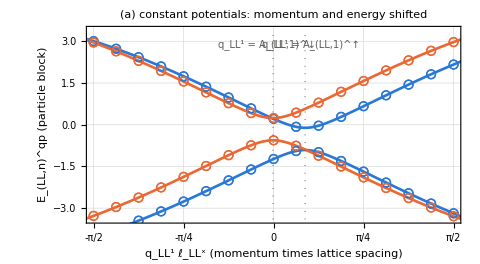
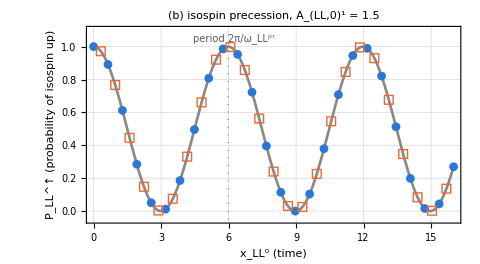
-Graphics-

○ isospin up, lattice operator○ isospin down, lattice operator
-Graphics-

● IDA (this notebook)□ CVODE (original program)Figure 3. Case A, free spinor charges in constant gauge potentials (item [2], checks AS-1 and AS-2).

```mathematica
(* Figure 3(a): the energies of the particle block in constant potentials.  Curves: the formula (rows as1CurveRows);
   circles: the eigenvalues of the lattice operator (rows as1LatticeRows); blue: isospin up, orange: isospin down.
   The dotted lines mark the momenta Acal_up_1 and Acal_down_1 at which the bands have their lowest energy *)
fig3aCurves = Flatten[Table[Map[{#[[1]] as1Ell, #[[4]]} &, Select[as1CurveRows, #[[2]] == qq && #[[3]] == branch &]], {qq, {0.5, -0.5}}, {branch, {1, -1}}], 1];
fig3aPoints = Table[Map[{#[[1]] as1Ell, #[[3]]} &, Select[as1LatticeRows, #[[2]] == qq &]], {qq, {0.5, -0.5}}];
fig3a = Show[
   ListLinePlot[fig3aCurves, PlotStyle -> {asLine[blue], asLine[blue], asLine[orange], asLine[orange]}],
   ListPlot[fig3aPoints, PlotStyle -> {blue, orange}, PlotMarkers -> {"○", 9}],
   Graphics[{muted, Dotted, Line[{{as1Acal1[0.5] as1Ell, -3.4}, {as1Acal1[0.5] as1Ell, 3.4}}], Line[{{as1Acal1[-0.5] as1Ell, -3.4}, {as1Acal1[-0.5] as1Ell, 3.4}}],
     Text[asNote[Row[{q1Sym, " = ", acalUpSym}]], {as1Acal1[0.5] as1Ell + 0.05, 2.9}, {-1, 0}],
     Text[asNote[Row[{q1Sym, " = ", acalDownSym}]], {as1Acal1[-0.5] as1Ell - 0.05, 2.9}, {1, 0}]}],
   Sequence @@ asPanel, PlotRange -> {{-Pi/2, Pi/2}, {-3.4, 3.4}},
   FrameLabel -> {upright[Row[{q1Sym, " ", ellxSym, " (momentum times lattice spacing)"}]], upright[Row[{eqpSym, " (particle block)"}]]},
   FrameTicks -> {{Automatic, None}, {{{-Pi/2, "-π/2"}, {-Pi/4, "-π/4"}, {0, "0"}, {Pi/4, "π/4"}, {Pi/2, "π/2"}}, None}},
   Sequence @@ asSize, PlotLabel -> asTitle["(a) constant potentials: momentum and energy shifted"]];
fig3aLegend = Column[{LineLegend[{asLine[blue], asLine[orange]},
     Map[upright, {Row[{qChargeSym, " = +1/2 (isospin up), formula"}], Row[{qChargeSym, " = −1/2 (isospin down), formula"}]}], LegendLayout -> "Row"],
    asKeys[asPointKey["○", blue, "isospin up, lattice operator"], asPointKey["○", orange, "isospin down, lattice operator"]]}, Center];
(* Figure 3(b): the probability of isospin up.  Grey line: the exact solution; filled blue circles: IDA in this notebook
   (the outputs number 0, 4, 8, ...); open orange squares: CVODE in the original program (the outputs number 2, 6, 10,
   ..., from the data cell).  The two sets of points alternate, so that neither covers the other *)
fig3bExact = Table[{x0, Cos[0.5 as2OmegaPr x0]^2}, {x0, 0., 16., 0.04}];
fig3bIda = as2PrecessionRows[[1 ;; -1 ;; 4, {1, 2}]];
fig3bCvode = t2origAPrecession[[3 ;; -1 ;; 4, {1, 2}]];
fig3b = Show[
   ListLinePlot[fig3bExact, PlotStyle -> asLine[grey]],
   ListPlot[{fig3bIda, fig3bCvode}, PlotStyle -> {blue, orange}, PlotMarkers -> {{"●", 9}, {"□", 9}}],
   Graphics[{muted, Dotted, Line[{{2 Pi/as2OmegaPr, -0.05}, {2 Pi/as2OmegaPr, 1.1}}],
     Text[asNote[Row[{"period 2π/", omegaPrSym}]], {2 Pi/as2OmegaPr + 0.25, 1.05}, {-1, 0}]}],
   Sequence @@ asPanel, PlotRange -> {{0, 16}, {-0.05, 1.1}},
   FrameLabel -> {upright[Row[{x0Sym, " (time)"}]], upright[Row[{pUpSym, " (probability of isospin up)"}]]},
   Sequence @@ asSize, PlotLabel -> asTitle[Row[{"(b) isospin precession, ", av10Sym, " = 1.5"}]]];
fig3bLegend = Column[{LineLegend[{asLine[grey]}, {upright[Row[{"exact: ", Superscript["cos", 2], "(", omegaPrSym, " ", x0Sym, "/2)"}]]}],
    asKeys[asPointKey["●", blue, "IDA (this notebook)"], asPointKey["□", orange, "CVODE (original program)"]]}, Center];
asFigure["Figure 3. Case A, free spinor charges in constant gauge potentials (item [2], checks AS-1 and AS-2).", fig3a, fig3aLegend, fig3b, fig3bLegend]
```

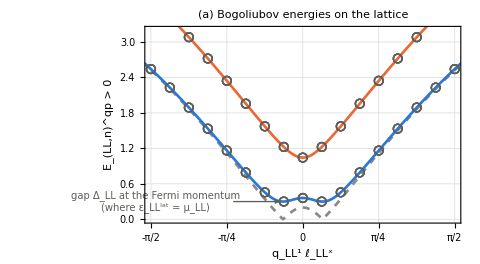
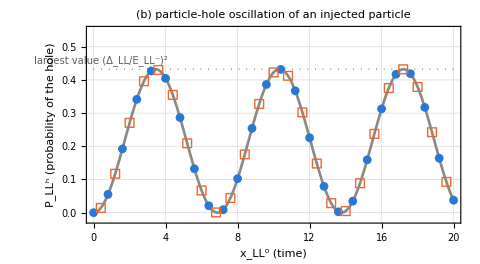
-Graphics-

○ lattice operator
-Graphics-

● IDA (this notebook)□ CVODE (original program)Figure 4, panels (a) and (b). Case B, the uniform polar superfluid (item [2], checks AS-3 and AS-4).

```mathematica
(* Figure 4(a): the positive energies of the uniform polar superfluid on the lattice.  Curves: the formulas with eps_lat
   (rows as3CurveRows); circles: the eigenvalues of the lattice operator (rows as3LatticeRows) *)
fig4aX = as3CurveRows[[All, 1]] asBEll;
(* the Fermi momentum of the lattice, where E^- has its minimum Delta (the left one of the two minima is marked) *)
fig4aFermi = First[MinimalBy[Select[as3CurveRows, #[[1]] < 0 &], #[[3]] &]][[1]] asBEll;
fig4a = Show[
   ListLinePlot[{Transpose[{fig4aX, Abs[as3CurveRows[[All, 2]] - asBMu]}], Transpose[{fig4aX, as3CurveRows[[All, 3]]}], Transpose[{fig4aX, as3CurveRows[[All, 4]]}]},
    PlotStyle -> {asDashed[grey], asLine[blue], asLine[orange]}],
   ListPlot[Map[{#[[1]] asBEll, #[[2]]} &, as3LatticeRows], PlotStyle -> muted, PlotMarkers -> {"○", 9}],
   Graphics[{muted, Thickness[0.002], Arrowheads[0.025], Arrow[{{-0.72, 0.3}, {fig4aFermi - 0.03, asBDelta}}],
     Text[asNote[Column[{Row[{"gap ", deltaSym, " at the Fermi momentum"}], Row[{"(where ", epsLatSym, " = ", muSym, ")"}]}, Spacings -> 0.2]], {-1.52, 0.3}, {-1, 0}]}],
   Sequence @@ asPanel, PlotRange -> {{-Pi/2, Pi/2}, {0, 3.2}},
   FrameLabel -> {upright[Row[{q1Sym, " ", ellxSym}]], upright[Row[{eqpSym, " > 0"}]]},
   FrameTicks -> {{Automatic, None}, {{{-Pi/2, "-π/2"}, {-Pi/4, "-π/4"}, {0, "0"}, {Pi/4, "π/4"}, {Pi/2, "π/2"}}, None}},
   Sequence @@ asSize, PlotLabel -> asTitle["(a) Bogoliubov energies on the lattice"]];
fig4aLegend = Column[{LineLegend[{asLine[blue], asLine[orange], asDashed[grey]},
     Map[upright, {Row[{ePolarMinusSym, " (formula)"}], Row[{ePolarPlusSym, " (formula)"}], Row[{"normal state, |", epsLatSym, " − ", muSym, "|"}]}], LegendLayout -> "Row"],
    asKeys[asPointKey["○", muted, "lattice operator"]]}, Center];
(* Figure 4(b): the probability of the hole; the points as in Figure 3(b) *)
fig4bExact = Table[{x0, (asBDelta/as4E)^2 Sin[as4E x0]^2}, {x0, 0., 20., 0.05}];
fig4bIda = as4RabiRows[[1 ;; -1 ;; 4, {1, 2}]];
fig4bCvode = t2origBRabi[[3 ;; -1 ;; 4, {1, 2}]];
fig4b = Show[
   ListLinePlot[fig4bExact, PlotStyle -> asLine[grey]],
   ListPlot[{fig4bIda, fig4bCvode}, PlotStyle -> {blue, orange}, PlotMarkers -> {{"●", 9}, {"□", 9}}],
   Graphics[{muted, Dotted, Line[{{0, (asBDelta/as4E)^2}, {20, (asBDelta/as4E)^2}}],
     Text[asNote[Row[{"largest value (", deltaSym, "/", ePolarMinusSym, Superscript[")", 2]}]], {0.4, (asBDelta/as4E)^2 + 0.025}, {-1, 0}]}],
   Sequence @@ asPanel, PlotRange -> {{0, 20}, {-0.02, 0.55}},
   FrameLabel -> {upright[Row[{x0Sym, " (time)"}]], upright[Row[{pHoleSym, " (probability of the hole)"}]]},
   Sequence @@ asSize, PlotLabel -> asTitle["(b) particle-hole oscillation of an injected particle"]];
fig4bLegend = Column[{LineLegend[{asLine[grey]}, {upright[Row[{"exact: (", deltaSym, "/", ePolarMinusSym, Superscript[")", 2], " ", Superscript["sin", 2], "(", ePolarMinusSym, " ", x0Sym, ")"}]]}],
    asKeys[asPointKey["●", blue, "IDA (this notebook)"], asPointKey["□", orange, "CVODE (original program)"]]}, Center];
asFigure["Figure 4, panels (a) and (b). Case B, the uniform polar superfluid (item [2], checks AS-3 and AS-4).", fig4a, fig4aLegend, fig4b, fig4bLegend]
```

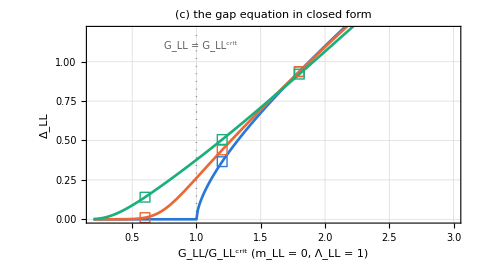
-Graphics-

□ gap checked by quadratureFigure 4, panel (c). Case B, the gap of the uniform polar superfluid of massless spinor charges (item [2], check AS-5).

```mathematica
(* Figure 4(c): the gap of massless charges as a function of the coupling, for three chemical potentials.  Curves: the
   closed form solved by bisection; squares: the gaps that were inserted in the integral computed by quadrature *)
fig4cLines = Table[Map[{#[[2]], #[[3]]} &, Select[as5GapRows, #[[1]] == chem && #[[4]] == 0 &]], {chem, {0., 0.3, 0.6}}];
fig4cQuad = Table[Map[{#[[2]], #[[3]]} &, Select[as5GapRows, #[[1]] == chem && #[[4]] == 1 &]], {chem, {0., 0.3, 0.6}}];
fig4c = Show[
   ListLinePlot[fig4cLines, PlotStyle -> {asLine[blue], asLine[orange], asLine[aqua]}],
   ListPlot[fig4cQuad, PlotStyle -> {blue, orange, aqua}, PlotMarkers -> {"□", 10}],
   Graphics[{muted, Dotted, Line[{{1, 0}, {1, 1.2}}], Text[asNote[Row[{gCouplingSym, " = ", gCritSym}]], {1.03, 1.1}, {-1, 0}]}],
   Sequence @@ asPanel, PlotRange -> {{0.2, 3.0}, {0, 1.2}},
   FrameLabel -> {upright[Row[{gCouplingSym, "/", gCritSym, " (", mSym, " = 0, ", lambdaSym, " = 1)"}]], upright[deltaSym]},
   Sequence @@ asSize, PlotLabel -> asTitle["(c) the gap equation in closed form"]];
fig4cLegend = Column[{LineLegend[{asLine[blue], asLine[orange], asLine[aqua]},
     Map[upright, {Row[{muSym, " = 0"}], Row[{muSym, " = 0.3"}], Row[{muSym, " = 0.6"}]}], LegendLayout -> "Row"],
    asKeys[asPointKey["□", muted, "gap checked by quadrature"]]}, Center];
asFigure["Figure 4, panel (c). Case B, the gap of the uniform polar superfluid of massless spinor charges (item [2], check AS-5).", fig4c, fig4cLegend]
```

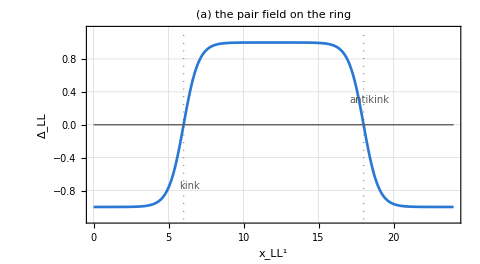
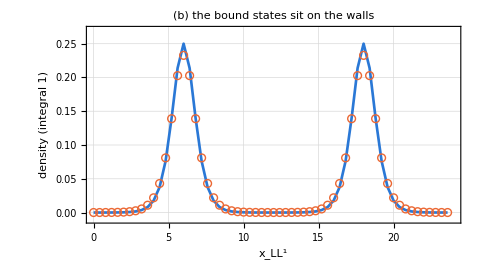
-Graphics-
-Graphics-

○ lattice, the eight states near +m_LLFigure 5, panels (a) and (b). Case C, a domain wall of the pair field on a ring of the length 24 (item [2], check AS-9).

```mathematica
(* Figure 5(a): the pair field of the ring with a kink at x^1 = 6 and an antikink at x^1 = 18 *)
fig5a = Show[
   ListLinePlot[Table[{x, as9Profile[x]}, {x, 0., 24., 0.05}], PlotStyle -> asLine[blue]],
   Graphics[{muted, Line[{{0, 0}, {24, 0}}], Dotted, Line[{{as9Xk1, -1.15}, {as9Xk1, 1.15}}], Line[{{as9Xk2, -1.15}, {as9Xk2, 1.15}}],
     Text[asNote["kink"], {as9Xk1 + 0.4, -0.75}, {-1, 0}], Text[asNote["antikink"], {as9Xk2 + 0.4, 0.3}, {-1, 0}]}],
   Sequence @@ asPanel, PlotRange -> {{0, 24}, {-1.15, 1.15}}, FrameLabel -> {upright[x1Sym], upright[deltaSym]},
   Sequence @@ asSize, PlotLabel -> asTitle["(a) the pair field on the ring"]];
(* Figure 5(b): the densities, both normalized to the integral 1.  Line: the analytic density of the bound states of the
   two walls at the 60 sites; circles: the summed density of the eight lattice eigenvectors near +m *)
fig5b = Show[
   ListLinePlot[as9ProfileRows[[All, {1, 4}]], PlotStyle -> asLine[blue]],
   ListPlot[as9ProfileRows[[All, {1, 3}]], PlotStyle -> orange, PlotMarkers -> {"○", 8}],
   Sequence @@ asPanel, PlotRange -> {{0, 24}, {-0.01, 0.27}}, FrameLabel -> {upright[x1Sym], "density (integral 1)"},
   Sequence @@ asSize, PlotLabel -> asTitle["(b) the bound states sit on the walls"]];
fig5bLegend = Column[{LineLegend[{asLine[blue]}, {upright[Row[{"analytic, proportional to (", phiKSym, Superscript[")", 2], " of both walls"}]]}],
    asKeys[asPointKey["○", orange, Row[{"lattice, the eight states near +", mSym}]]]}, Center];
asFigure["Figure 5, panels (a) and (b). Case C, a domain wall of the pair field on a ring of the length 24 (item [2], check AS-9).", fig5a, fig5b, fig5bLegend]
```

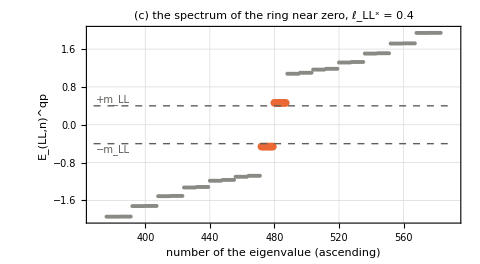
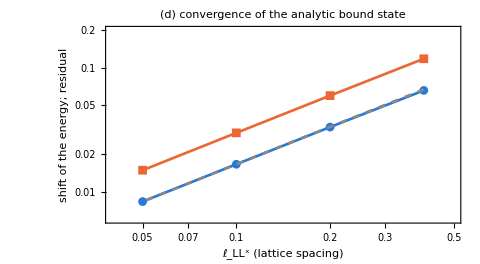
-Graphics-
● states that are not bound● the 16 bound states
-Graphics-
Figure 5, panels (c) and (d). Case C, the spectrum of the ring and the convergence of the analytic bound state (item [2], check AS-9).

```mathematica
(* Figure 5(c): the eigenvalues of the ring with a modulus below 2, against their number; the 16 bound states (the
   places as9Inside) are drawn larger and in orange *)
fig5cBound = as9SpectrumRows[[as9Inside]];
fig5cContinuum = Select[Delete[as9SpectrumRows, Map[List, as9Inside]], Abs[#[[2]]] < 2. &];
fig5cRange = {Min[fig5cContinuum[[All, 1]]] - 8, Max[fig5cContinuum[[All, 1]]] + 8};
fig5c = Show[
   ListPlot[{fig5cContinuum, fig5cBound}, PlotStyle -> {grey, orange}, PlotMarkers -> {{"●", 4}, {"●", 8}}],
   Graphics[{muted, Dashed, Line[{{fig5cRange[[1]], mass}, {fig5cRange[[2]], mass}}], Line[{{fig5cRange[[1]], -mass}, {fig5cRange[[2]], -mass}}],
     Text[asNote[Row[{"+", mSym}]], {fig5cRange[[1]] + 12, mass + 0.13}, {-1, 0}], Text[asNote[Row[{"−", mSym}]], {fig5cRange[[1]] + 12, -mass - 0.13}, {-1, 0}]}],
   Sequence @@ asPanel, PlotRange -> {fig5cRange, {-2., 2.}}, FrameLabel -> {"number of the eigenvalue (ascending)", upright[eqpSym]},
   Sequence @@ asSize, PlotLabel -> asTitle[Row[{"(c) the spectrum of the ring near zero, ", ellxSym, " = 0.4"}]]];
fig5cLegend = asKeys[asPointKey["●", grey, "states that are not bound"], asPointKey["●", orange, "the 16 bound states"]];
(* Figure 5(d): the convergence of the analytic bound state with the lattice spacing (logarithmic axes): the shift of its
   Rayleigh quotient, the first-order shift r_W dx/6, and its relative residual *)
fig5dSpacing = as9ConvergenceRows[[All, 1]];
fig5d = Show[
   ListLogLogPlot[{Transpose[{fig5dSpacing, as9ConvergenceRows[[All, 2]] - mass}], Transpose[{fig5dSpacing, as9ConvergenceRows[[All, 3]]}]}, Joined -> True,
    PlotStyle -> {asLine[blue], asLine[orange]}, PlotMarkers -> {{"●", 9}, {"■", 9}}, PlotRange -> {{0.04, 0.5}, {0.006, 0.2}},
    Axes -> False, Frame -> True, GridLines -> Automatic, GridLinesStyle -> Directive[GrayLevel[0.9]],
    FrameLabel -> {upright[Row[{ellxSym, " (lattice spacing)"}]], "shift of the energy; residual"},
    LabelStyle -> Directive[FontSize -> 11], Sequence @@ asSize, PlotLabel -> asTitle["(d) convergence of the analytic bound state"]],
   ListLogLogPlot[Transpose[{fig5dSpacing, fig5dSpacing/6.}], Joined -> True, PlotStyle -> asDashed[grey]]];
fig5dLegend = LineLegend[{asLine[blue], asDashed[grey], asLine[orange]},
   Map[upright, {Row[{eRSym, " − ", mSym}], Row[{rWSym, " ", ellxSym, "/6 (first order)"}], "relative residual"}], LegendLayout -> "Row"];
asFigure["Figure 5, panels (c) and (d). Case C, the spectrum of the ring and the convergence of the analytic bound state (item [2], check AS-9).", fig5c, fig5cLegend, fig5d, fig5dLegend]
```

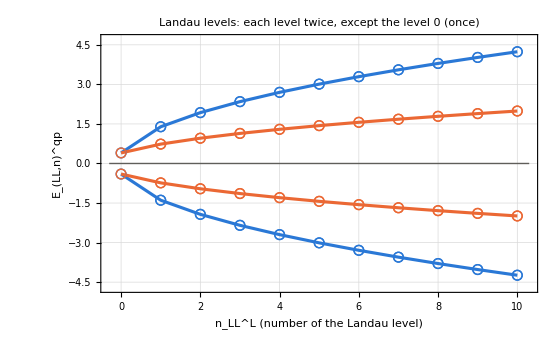
-Graphics-

○ isospin up, oscillator basis○ isospin down, oscillator basisFigure 6. Case D, the Landau levels of the two isospin components (item [2], check AS-10).

```mathematica
(* Figure 6: the Landau levels of the two isospin components.  Lines: the formula; circles: the eigenvalues of the
   diagonalization in the oscillator basis (every level from 1 on is a pair of equal eigenvalues) *)
fig6Series[qq_, source_, sg_] := Map[{#[[2]], #[[3]]} &, Select[as10LandauRows, #[[1]] == qq && #[[4]] == source && sg #[[3]] > 0 &]];
fig6 = Show[
   ListLinePlot[{fig6Series[0.5, 0, 1], fig6Series[0.5, 0, -1], fig6Series[-0.5, 0, 1], fig6Series[-0.5, 0, -1]},
    PlotStyle -> {asLine[blue], asLine[blue], asLine[orange], asLine[orange]}],
   ListPlot[{Join[fig6Series[0.5, 1, 1], fig6Series[0.5, 1, -1]], Join[fig6Series[-0.5, 1, 1], fig6Series[-0.5, 1, -1]]}, PlotStyle -> {blue, orange},
    PlotMarkers -> {"○", 10}],
   Graphics[{muted, Line[{{-0.3, 0}, {10.3, 0}}]}],
   Sequence @@ asPanel, PlotRange -> {{-0.3, 10.3}, {-4.7, 4.7}}, FrameTicks -> {{Automatic, None}, {Range[0, 10], None}},
   FrameLabel -> {upright[Row[{nLSym, " (number of the Landau level)"}]], upright[eqpSym]},
   ImageSize -> 560, PlotLabel -> asTitle["Landau levels: each level twice, except the level 0 (once)"]];
fig6Legend = Column[{LineLegend[{asLine[blue], asLine[orange]},
     Map[upright, {Row[{qChargeSym, " = +1/2, ", bUpSym, " = 0.89, formula"}], Row[{qChargeSym, " = −1/2, ", bDownSym, " = 0.19, formula"}]}], LegendLayout -> "Row"],
    asKeys[asPointKey["○", blue, "isospin up, oscillator basis"], asPointKey["○", orange, "isospin down, oscillator basis"]]}, Center];
asFigure["Figure 6. Case D, the Landau levels of the two isospin components (item [2], check AS-10).", fig6, fig6Legend]
```

### Summary of item [2]

```mathematica
Grid[Prepend[Map[{#["name"], If[#["pass"], Style["PASS", Darker[Green]], Style["FAIL", Red]], #["statement"]} &,
    Select[SL31`Test`$Results, StringStartsQ[#["name"], "AS-"] || #["name"] === "T2-DATA-2" &]], Style[#, Bold] & /@ {"check", "result", "statement"}],
  Frame -> All, Alignment -> {Left, Top}]
```

check | result | statement
AS-1 | PASS | free spinor charges in constant gauge potentials (case A): on a periodic chain of 32 sites along x_LL^1 (dx = 0.5, r_W = 1, m = 0.4, mu = 0.2, g_v = 0.7, g_F = 0.45) with the constant potentials Av_LL^3_1 = 0.8 and AF_LL_1 = 0.6 (in the links) and Av_LL^3_0 = 0.5 and AF_LL_0 = 0.3 (in the potential matrix), and no pair field, the 16 eigenvalues of the lattice operator on the plane wave of each allowed momentum q are, for each isospin component (Q_LL = +1/2 with Acal_up_p = g_F AF_LL_p + g_v Av_LL^3_p/2, Q_LL = -1/2 with Acal_down_p = g_F AF_LL_p - g_v Av_LL^3_p/2), +-eps_lat(q - Acal_1) - Acal_0 - mu (particles) and -(+-eps_lat(q + Acal_1) - Acal_0 - mu) (holes), each twice: the potential of the space direction shifts the momentum (minimal coupling q -> q - Acal_1) and the potential of the time direction shifts the energy; the particle block does not mix the two isospin components, and its restriction to each component has the eigenvalues +-eps_lat(q - Acal_1) - Acal_0 - mu (tolerance 1e-12)
AS-2 | PASS | isospin precession in a constant isospin potential (case A): in the potential Av_LL^1_0 = 1.5 (along tau_1, no other field) the positive-energy lattice plane wave chi_pw (x) (isospin up) evolves as exp(-i (eps_lat - mu) x_LL^0) chi_pw (x) (cos(omega_pr x_LL^0/2), i sin(omega_pr x_LL^0/2)) with omega_pr = g_v Av_LL^1_0, so that P_up = cos^2(omega_pr x_LL^0/2); the integration of the lattice equations by IDA (SUNDIALS, through NDSolve with Method -> "IDA", in place of CVODE of the original program; rtol = 1e-12, atol = 1e-14; periodic chain of 16 sites, dx = 0.5, r_W = 1, m = 0.4, mu = 0.2, momentum 2 pi 2/(16 dx)) agrees with this exact solution at the 101 output times x_LL^0 = 0, 0.16, ..., 16: (1) the relative deviation of the whole state stays below 1e-9, the tolerance of the original check; (2) the states at the output times are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12), and the largest deviation is at most the bound that follows from the measured exact local errors of the internal steps, (1 + h_IDA E_max/4) (sum of local_error) + h_IDA deriv_residual/4 + (h_IDA E_max)^4/384 (norm of the state); the numbers of steps and of evaluations of IDA and the largest ratio local_error/budget_step, with budget_step = rtol (norm of the state) + atol sqrt(512), are stated
AS-3 | PASS | the Bogoliubov modes of the uniform polar superfluid dvec = (0, 0, Delta) (case B): Kch_3 h(q) = conj(h(-q)) Kch_3, so that for an eigenvector chi_pw of h(q) with the energy +eps or -eps the hole vector Kch_3 chi_pw is an eigenvector of conj(h(-q)) with the same energy; Ppair = Delta Kch_3^dag couples (chi_pw, 0) only to (0, Kch_3 chi_pw), and (cos theta_B chi_pw, sin theta_B Kch_3 chi_pw) with cos^2 theta_B = (1 + (+-eps - mu)/E)/2, sin^2 theta_B = (1 - (+-eps - mu)/E)/2, E = ((+-eps - mu)^2 + Delta^2)^(1/2), is an eigenvector of H_BdG(q) with the energy E, which is E^- for the positive branch +eps and E^+ for the negative branch -eps (50 random momenta, chemical potentials and gaps, m = 0.4; tolerance 1e-12); on the lattice (periodic chain of 32 sites, dx = 0.5, r_W = 1, m = 0.4, mu = 0.6, Delta = 0.3) the 16 eigenvalues of the lattice operator on the plane wave of each allowed momentum are +-E^- and +-E^+ with eps_lat in place of eps, each four times (tolerance 1e-12)
AS-4 | PASS | the particle-hole (Rabi) oscillation of a particle injected into the uniform polar superfluid (case B): on a periodic chain of 16 sites (dx = 0.5, r_W = 1, m = 0.4, mu = 0.6) with the pair field dvec = (0, 0, 0.3), the positive-energy lattice plane wave chi_pw of isospin up at the momentum 2 pi/(16 dx) evolves as (cos(E^- x_LL^0) - i ((eps_lat - mu)/E^-) sin(E^- x_LL^0)) (chi_pw, 0) - i (Delta/E^-) sin(E^- x_LL^0) (0, Kch_3 chi_pw), with E^- = ((eps_lat - mu)^2 + Delta^2)^(1/2): the probability of the hole is P_hole = (Delta/E^-)^2 sin^2(E^- x_LL^0); the integration of the lattice equations by IDA (SUNDIALS, through NDSolve with Method -> "IDA", in place of CVODE of the original program; rtol = 1e-12, atol = 1e-14) agrees with this exact solution at the 101 output times x_LL^0 = 0, 0.2, ..., 20: (1) the relative deviation of the whole state stays below 1e-9, the tolerance of the original check; (2) the states at the output times are the cubic Hermite polynomials of the stored values and derivatives (tolerance 1e-12), and the largest deviation is at most the bound that follows from the measured exact local errors of the internal steps, (1 + h_IDA E_max/4) (sum of local_error) + h_IDA deriv_residual/4 + (h_IDA E_max)^4/384 (norm of the state); the numbers of steps and of evaluations of IDA and the largest ratio local_error/budget_step, with budget_step = rtol (norm of the state) + atol sqrt(512), are stated
AS-5 | PASS | the gap equation in closed form for massless spinor charges (case B): int_(q<Lambda) d^3q/(2 pi)^3 (1/E^+ + 1/E^-) with E^(+-) = ((q +- mu)^2 + Delta^2)^(1/2) equals (1/(4 pi^2)) [(Lambda - 3 mu) E^+(Lambda) + (Lambda + 3 mu) E^-(Lambda) + (2 mu^2 - Delta^2) (asinh((Lambda + mu)/Delta) + asinh((Lambda - mu)/Delta))] for six pairs (mu, Delta) (relative deviation from composite Gauss-Legendre quadrature with 32 nodes per panel, tolerance 1e-10); its limit Delta -> 0 at mu = 0 is Lambda^2/(2 pi^2), so that G_crit = 2 pi^2/Lambda^2 (tolerance 1e-8); the gaps Delta(G) found from the closed form by bisection satisfy G int(...) = 1 with the integral computed by quadrature (the 11 of the 12 cases mu = 0, 0.3, 0.6 with G/G_crit = 0.6, 1.2, 1.8, 2.4 that have a gap, tolerance 1e-9); and for mu > 0 and weak coupling (G < G_crit) the gap approaches the BCS form Delta = 2 (Lambda^2 - mu^2)^(1/2) exp(-3/2) exp(-(pi^2/mu^2) (1/G - 1/G_crit)), the relative deviation being smaller than twice the size (Delta^2/(2 mu^2)) ln(1/Delta) of the leading correction (mu = 0.3, G/G_crit = 0.3, 0.4, 0.5); Lambda = 1
AS-6 | PASS | the uniform polar state is an exact self-consistent solution of the lattice mean-field equations (case B): on a periodic chain of 16 sites (dx = 0.5, r_W = 1, m = 0.4, mu = 0.6) with dvec = (0, 0, 0.3), the sum over the 128 positive-energy eigenvectors of the lattice operator (unit vectors, with the particle part psi_p and the hole part psi_h) of psi_p^T Kch_iota conj(psi_h), computed at every site by the routine of the solvers, is 0 for iota = 1, 2 and -2 Delta (1/16) sum_q (1/E^+ + 1/E^-) (eps_lat in place of eps, the 16 allowed momenta) for iota = 3 (tolerance 1e-12); with Pi_iota = dx^(-1) times this sum (the continuum normalization of a chain) and the coupling G given by the lattice gap equation 1/G = (1/(16 dx)) sum_q (1/E^+ + 1/E^-), the self-consistency condition d_iota = -(G/2) Pi_iota gives back dvec = (0, 0, Delta) on every site (tolerance 1e-12): a fixed point that the self-consistent solvers must reproduce
AS-7 | PASS | the bound states of a domain wall (kink) of the pair field (case C), in the continuum: the 8 x 8 matrices (Dirac (x) isospin) satisfy (Kch_3^dag)^2 = -1, (Kch_3^dag)^dag = -Kch_3^dag, alpha_LL^1 Kch_3^dag alpha_LL^1 = -Kch_3^dag and beta_LL Kch_3^dag alpha_LL^1 = -Kch_3^dag alpha_LL^1 beta_LL, and alpha_LL^1 and beta_LL are real (tolerance 1e-13); for the kink dvec = (0, 0, Delta(x_LL^1)) with Delta(x_LL^1) = Delta_inf tanh(x_LL^1/ell_K) (Delta_inf = 1, ell_K = 1) and mu = 0, the mode psi_p = phi_K chi_K, psi_h = i Kch_3^dag alpha_LL^1 phi_K chi_K with phi_K = cosh(x_LL^1/ell_K)^(-Delta_inf ell_K) (so that d phi_K/d x_LL^1 = -Delta phi_K) and a constant chi_K with beta_LL chi_K = +chi_K or -chi_K satisfies the sixteen component equations with the energy +m or -m at 50 random points (m = 0.4, random chi_K; tolerance 1e-12)
AS-8 | PASS | the square of the operator and the complete spectrum of the bound states of a wall (case C): with mu = 0, no gauge fields, dvec = (0, 0, Delta(x_LL^1)) real and the plane wave exp(i (q^2 x_LL^2 + q^3 x_LL^3)) along the wall, H_DB^2 = (-d^2/d(x_LL^1)^2 + (q^2)^2 + (q^3)^2 + m^2 + Delta^2) 1_16 + (d Delta/d x_LL^1) Qmat_K with the constant matrix Qmat_K = [[0, -i alpha_LL^1 Kch_3^dag], [-i alpha_LL^1 Kch_3, 0]], which is Hermitian, squares to the unit matrix and has the trace 0 (tolerance 1e-13), because alpha_LL^j Kch_3^dag = -Kch_3^dag conj(alpha_LL^j) for j = 1, 2, 3 (tolerance 1e-13); the identity is checked by applying H_DB twice to a Gaussian times a random 16-component vector, with exact derivatives, for 50 random kinks Delta = Delta_inf tanh(x_LL^1/ell_K), points and momenta (m = 0.4; tolerance 1e-11); the bound states of the two scalar operators -d^2/d(x_LL^1)^2 + Delta^2 - d Delta/d x_LL^1 (the eigenvalue -1 of Qmat_K) and -d^2/d(x_LL^1)^2 + Delta^2 + d Delta/d x_LL^1 (the eigenvalue +1) are those of Poeschl-Teller wells, Delta_inf^2 - (Delta_inf - k_K/ell_K)^2 for the integers k_K with 0 <= k_K < Delta_inf ell_K (eigenvalue -1) and 1 <= k_K < Delta_inf ell_K (eigenvalue +1): finite differences with 4000 and 8001 points on (-20, 20), extrapolated, give exactly these bound states, and no others below the threshold Delta_inf^2, for Delta_inf ell_K = 1 and 2.5 (ell_K = 1; tolerance 1e-6); hence the bound states of the wall have the energies +-(m^2 + (q^2)^2 + (q^3)^2 + 2 k_K Delta_inf/ell_K - k_K^2/ell_K^2)^(1/2)
AS-9 | PASS | the bound states of the domain wall on the lattice (case C): on a ring of length 24 (60 sites, dx = 0.4, r_W = 1, m = 0.4, mu = 0) with the kink-antikink profile Delta(x_LL^1) = tanh(x_LL^1 - 6) tanh(18 - x_LL^1), the lattice operator has exactly 16 eigenvalues inside 0.8 times the continuum threshold (m^2 + Delta_inf^2)^(1/2), eight positive and eight negative (four per wall and sign); with the relative residual r of the analytic bound state at dx = 0.4 and the distance delta from its Rayleigh quotient E_R to the nearest eigenvalue outside the cluster of the eight positive bound states, which lies between the neighbours of the cluster: (1) the moduli of the 16 eigenvalues lie within r^2/delta + spread of E_R, where spread is the largest minus the smallest of the 16 moduli (the theorem of Kato and Temple: one eigenvalue of the cluster lies at most r^2/delta above E_R and one at most r^2/delta below); (2) the part of the normalized analytic state outside the space of the eight eigenvectors near +m has at most the norm r/delta (the theorem of Davis and Kahan); (3) the summed density of the eight states near +m agrees with the analytic density of the bound states of the two walls at second order in r, 1 - (Bhattacharyya coefficient of the two normalized densities) < (1/2) (r/delta)^2 (a requirement of the check on the scale of (2), not a theorem; the Bhattacharyya coefficient is the sum over the sites of the square root of the product of the two densities, each normalized to the sum 1); for the analytic bound state of the kink (chi_K with the components 1 and 5 equal to 1/sqrt 2 and the others zero, beta_LL chi_K = chi_K) on rings with dx = 0.4, 0.2, 0.1, 0.05 the Rayleigh quotient E_R equals the exact lattice formula m + (r_W/(2 dx)) sum (phi_K(s+1) - phi_K(s))^2 / sum phi_K(s)^2 (tolerance 1e-12), (E_R - m)/(r_W dx) tends to 1/6 (within 1 per cent at dx = 0.05, the difference decreasing by a factor between 3.5 and 4.5 at each halving of dx: the Wilson term shifts the bound state at first order in dx, by r_W dx/6, with a correction of order dx^3), and the relative residual decreases at least by the factor 0.6 at each halving of dx
AS-10 | PASS | Landau levels (case D): for one isospin component (Q_LL = +1/2 or -1/2) in the constant magnetic fields FF_LL_12 = 1.2 of U(1)_F and Fv_LL^3_12 = 1.0 of the third isospin direction (Landau gauge AF_LL_2 = FF_LL_12 x_LL^1, Av_LL^3_2 = Fv_LL^3_12 x_LL^1; g_v = 0.7, g_F = 0.45), the component feels the magnetic field B_up = g_F FF_LL_12 + g_v Fv_LL^3_12/2 or B_down = g_F FF_LL_12 - g_v Fv_LL^3_12/2; the Dirac Hamiltonian alpha_LL^1 p_1 + alpha_LL^2 (p_2 - B_up x_LL^1) + beta_LL m at p_2 = p_3 = 0 (and the same with B_down), with the momentum operators p_j = -i d_j, diagonalized in a basis of 120 oscillator states of the frequency |B_up| (or |B_down|) (the states with a weight above 1e-8 on the ten highest oscillator states are discarded: for each isospin component they are the 40 states of the levels 110 to 119, which the check does not use, and the two artefacts of the truncation, which have the energies +m and -m and live on the highest oscillator state), has the energies +m and -m once each and +-(m^2 + 2 n_L |B_up|)^(1/2) (or with |B_down|) twice each for n_L = 1 to 10, and no other energy below the level 10 (m = 0.4; tolerance 1e-10)
T2-DATA-2 | PASS | the numbers of the figures of item [2] agree with the eleven data files written by the original program t2_analytic (t2_A_dispersion_curves, t2_A_dispersion_lattice, t2_A_precession, t2_B_bogoliubov_curves, t2_B_bogoliubov_lattice, t2_B_gap, t2_B_rabi, t2_C_kink_convergence, t2_C_kink_profile, t2_C_kink_spectrum, t2_D_landau; 4725 rows): every column printed with 10 decimals within 5.1e-11, half a unit of the last printed decimal; the times within 5.1e-5, G/G_crit within 5.1e-6, the relative residual within the fraction 5.1e-7; the charges, branches, numbers of levels and of eigenvalues and the sources are equal; the probabilities P_up and P_hole of the integrated states, computed here with IDA and in the files with CVODE, differ by at most 4 (max_deviation of IDA + max_deviation of CVODE) + 5.1e-11, the bound that follows from the relative deviations of the two integrations from the exact solution